
-Graphics-
Previous notebook		Content		Next notebook

## Elementary functions

Version (2021-12-07)  The notebook run time is about 1 hour on 2020 year laptop (with cells that take long time to evaluate being inactivated). Evaluate this notebook interactively,cell by cell.

### Load main notebook

Load package. WAIT until evaluation of cell is finished to be sure that no errors were produced.

```mathematica
NotebookEvaluate[FileNameJoin[{ParentDirectory[NotebookDirectory[EvaluationNotebook[]]],"GA.nb"}]]
```

Subsection numbers refer to logical units of “Geometric algebra handbook” (in preparation). Algorithms for exact formulas are named as gaFunctionOfMV[ ], where Function can be Sqrt, Exponent, Logarithm, ArcTanh (+other hyperbolic and their inverses), ArcSin (+other trigonometric and their inverses when they can be defined, i.e in Cl(3,0), for example). Exact formulas are available for p+q≤3. For higher dimensions only series expansions are available.

### Definitions and shortcuts

Some shortcuts for vectors and bivectors, which will be used for compact formula tastings. Note, testAlgebra keyword

```mathematica
(* vectors *)
a1:=gaGeneralMultivector[a,testAlgebra,{1}];
b1:=gaGeneralMultivector[b,testAlgebra,{1}];
c1:=gaGeneralMultivector[c,testAlgebra,{1}];
d1:=gaGeneralMultivector[d,testAlgebra,{1}];
f1:=gaGeneralMultivector[f,testAlgebra,{1}];
(*bivectors*)
𝒜1:=gaGeneralMultivector[𝒜,testAlgebra,{2}];
ℬ1:=gaGeneralMultivector[ℬ,testAlgebra,{2}];
𝒞1:=gaGeneralMultivector[𝒞,testAlgebra,{2}];
(*general multivectors*)
A1:=gaGeneralMultivector[A,testAlgebra];
B1:=gaGeneralMultivector[B,testAlgebra];
F1:=gaGeneralMultivector[F,testAlgebra];
```

Sections below are independent. In order to start calculation of any of them in any order you only need to evaluate cells above this line.

Function series

### 2.36. Exponential and trigonometric function series

#### a) gaSeries usage examples

```mathematica
testAlgebra=Cl[2,0];
gaDefineOrthonormalBasis[testAlgebra];
```

Basis vectors of 200are stored in variable gaOrthonormalBasis[Cl[2, 0, 0],InvDeg[Lex]].

Running algebra is: gaRunningAlgebra= Cl[2, 0, 0]

LHS:

```mathematica
gaGeometricProductSeries[Exp,{𝕖[1]+𝕖[2],{0,6}}]
```

gaSeriesData[0,{{{1},0},{{1200+2200},1},{{1},2},{{1/6 (2 1200+2 2200)},3},{{1/6},4},{{1/120 (4 1200+4 2200)},5},{{1/90},6}}]

Your can convert series into ordinary expression with Normal[ ].  Note: the linear term is put in the end when put into Normal form.

```mathematica
gaGeometricProductSeries[Exp,{𝕖[1]+𝕖[2],{0,6}}]//Normal
```

98/45+1200+2200+1/6 (2 1200+2 2200)+1/120 (4 1200+4 2200)

General symbolic expansion: use trick, that MV[ ] denotes general multivector (general multivector is noncommutative object)

```mathematica
gaGeometricProductSeries[Exp,{MV[a],{0,6}}]//Normal
```

1+1/2 MV[a]\[GeometricProduct]MV[a]+1/6 MV[a]\[GeometricProduct]MV[a]\[GeometricProduct]MV[a]+1/24 MV[a]\[GeometricProduct]MV[a]\[GeometricProduct]MV[a]\[GeometricProduct]MV[a]+1/120 MV[a]\[GeometricProduct]MV[a]\[GeometricProduct]MV[a]\[GeometricProduct]MV[a]\[GeometricProduct]MV[a]+1/720 MV[a]\[GeometricProduct]MV[a]\[GeometricProduct]MV[a]\[GeometricProduct]MV[a]\[GeometricProduct]MV[a]\[GeometricProduct]MV[a]+MV[a]

Exponent squared. You can use any pure function (of single argument at the moment only)

```mathematica
gaGeometricProductSeries[Exp[#]^2&,{𝕖[1]+𝕖[2],{0,6}}]
```

gaSeriesData[0,{{{1},0},{{2 (1200+2200)},1},{{4},2},{{4/3 (2 1200+2 2200)},3},{{8/3},4},{{4/15 (4 1200+4 2200)},5},{{32/45},6}}]

```mathematica
gaGeometricProductSeries[Sin,{𝕖[1]+𝕖[2],{0,6}}]
```

gaSeriesData[0,{{{0},0},{{1200+2200},1},{{0},2},{{1/6 (-2 1200-2 2200)},3},{{0},4},{{1/120 (4 1200+4 2200)},5},{{0},6}}]

For often used trigonometric functions there are shortcuts

```mathematica
{gaSin[𝕖[1]+𝕖[2]],gaSin[𝕖[1]+𝕖[2],{0,10}]}//Column
```

gaSeriesData[0,{{{0},0},{{1200+2200},1},{{0},2},{{1/6 (-2 1200-2 2200)},3},{{0},4},{{1/120 (4 1200+4 2200)},5},{{0},6}}]
gaSeriesData[0,{{{0},0},{{1200+2200},1},{{0},2},{{1/6 (-2 1200-2 2200)},3},{{0},4},{{1/120 (4 1200+4 2200)},5},{{0},6},{{(-8 1200-8 2200)/5040},7},{{0},8},{{(16 1200+16 2200)/362880},9},{{0},10}}]

```mathematica
{gaExp[𝕖[1]+𝕖[2]],gaCos[𝕖[1]+𝕖[2]],gaSinh[𝕖[1]+𝕖[2]],gaCosh[𝕖[1]+𝕖[2]]}//Column
```

gaSeriesData[0,{{{1},0},{{1200+2200},1},{{1},2},{{1/6 (2 1200+2 2200)},3},{{1/6},4},{{1/120 (4 1200+4 2200)},5},{{1/90},6}}]
gaSeriesData[0,{{{1},0},{{0},1},{{-1},2},{{0},3},{{1/6},4},{{0},5},{{-1/90},6}}]
gaSeriesData[0,{{{0},0},{{1200+2200},1},{{0},2},{{1/6 (2 1200+2 2200)},3},{{0},4},{{1/120 (4 1200+4 2200)},5},{{0},6}}]
gaSeriesData[0,{{{1},0},{{0},1},{{1},2},{{0},3},{{1/6},4},{{0},5},{{1/90},6}}]

If you want series elements to be expanded it is much more effective to use option Expand, than expand later

```mathematica
gaGeometricProductSeries[Cos,{𝕖[1]+𝕖[2],{0,10}},Expand->True]//AbsoluteTiming
```

{0.008942,gaSeriesData[0,{{{1},0},{{0},1},{{-1},2},{{0},3},{{1/6},4},{{0},5},{{-1/90},6},{{0},7},{{1/2520},8},{{0},9},{{-1/113400},10}}]}

```mathematica
gaPE[gaGeometricProductSeries[Cos,{𝕖[1]+𝕖[2],{0,10}}]]//AbsoluteTiming
```

{0.010526,gaSeriesData[0,{{{1},0},{{0},1},{{-1},2},{{0},3},{{1/6},4},{{0},5},{{-1/90},6},{{0},7},{{1/2520},8},{{0},9},{{-1/113400},10}}]}

```mathematica
gaSin[𝕖[1]+𝕖[2],Expand->True]//AbsoluteTiming
```

{0.015175,gaSeriesData[0,{{{0},0},{{1200+2200},1},{{0},2},{{1/6 (-2 1200-2 2200)},3},{{0},4},{{1/120 (4 1200+4 2200)},5},{{0},6}}]}

```mathematica
gaPE[gaGeometricProductSeries[Sin,{𝕖[1]+𝕖[2],{0,6}}]]//AbsoluteTiming
```

{0.007723,gaSeriesData[0,{{{0},0},{{1200+2200},1},{{0},2},{{1/6 (-2 1200-2 2200)},3},{{0},4},{{1/120 (4 1200+4 2200)},5},{{0},6}}]}

```mathematica
gaSin[𝕖[1]+𝕖[2]]//Normal
```

1200+1/6 (-2 1200-2 2200)+2200+1/120 (4 1200+4 2200)

```mathematica
gaSin[𝕖[1]+𝕖[2]]//Normal//gaPE
```

1200+1/6 (-2 1200-2 2200)+2200+1/120 (4 1200+4 2200)

Series data can be summed

```mathematica
testExp[testAlgebra]=gaExp[𝕖[1]+𝕖[2],{0,5}]
```

gaSeriesData[0,{{{1},0},{{1200+2200},1},{{1},2},{{1/6 (2 1200+2 2200)},3},{{1/6},4},{{1/120 (4 1200+4 2200)},5}}]

```mathematica
testSin[testAlgebra]=gaSin[𝕖[1]+𝕖[2],{0,6}]
```

gaSeriesData[0,{{{0},0},{{1200+2200},1},{{0},2},{{1/6 (-2 1200-2 2200)},3},{{0},4},{{1/120 (4 1200+4 2200)},5},{{0},6}}]

Note, that series order corresponds to lowest expansion order of term summed

```mathematica
testExp[testAlgebra]+testSin[testAlgebra]
```

gaSeriesData[0,{{{1},0},{{2 1200+2 2200},1},{{1},2},{{1/6 (-2 1200-2 2200)+1/6 (2 1200+2 2200)},3},{{1/6},4},{{1/60 (4 1200+4 2200)},5}}]

We can expand the sum itself like

```mathematica
gaGeometricProductSeries[(Exp[#]+Sin[#])&,{𝕖[1]+𝕖[2],{0,5}}]
```

gaSeriesData[0,{{{1},0},{{2 (1200+2200)},1},{{1},2},{{0},3},{{1/6},4},{{1/60 (4 1200+4 2200)},5}}]

Series data can be multiplied

```mathematica
testExpSinMultiplication[testAlgebra]=testExp[testAlgebra]\[GeometricProduct]testSin[testAlgebra]
```

gaSeriesData[0,{{{0},0},{{1200+2200},1},{{(1200+2200)\[GeometricProduct](1200+2200)},2},{{1200+1/6 (-2 1200-2 2200)+2200},3},{{1/6 ((1200+2200)\[GeometricProduct](-2 1200-2 2200))+1/6 ((2 1200+2 2200)\[GeometricProduct](1200+2200))},4},{{1/6 (-2 1200-2 2200)+1/6 (1200+2200)+1/120 (4 1200+4 2200)},5}}]

```mathematica
testExpSin[testAlgebra]=gaGeometricProductSeries[(Exp[#]\[GeometricProduct]Sin[#])&,{𝕖[1]+𝕖[2],{0,5}}]
```

gaGeometricProductSeries::function: The expanded function Exp[#1]\[GeometricProduct]Sin[#1]& contains noncommutative operations (GeometricProduct or other). Current implementation is not ready to handle such cases. Use only with single argument!!!

gaSeriesData[0,{{{0},0},{{1200+2200},1},{{2},2},{{1/3 (2 1200+2 2200)},3},{{0},4},{{1/30 (-4 1200-4 2200)},5}}]

Here we are warned, because multiplication of different noncommuting arguments is not implemented. In this case, however we have only one argument and expansion is valid

```mathematica
(testExpSinMultiplication[testAlgebra]-testExpSin[testAlgebra])//Normal
```

-2+1/6 ((1200+2200)\[GeometricProduct](-2 1200-2 2200))+(1200+2200)\[GeometricProduct](1200+2200)+1/6 ((2 1200+2 2200)\[GeometricProduct](1200+2200))+1200+2/3 (-2 1200-2 2200)+2200+1/6 (1200+2200)+1/24 (4 1200+4 2200)

One can get series with expansion parameter with

```mathematica
gaParameterSeries[gaSin[𝕖[1]+𝕖[2],{0,6},Expand->True],t]
```

1/6 t^3 (-2 1200-2 2200)+t (1200+2200)+1/120 t^5 (4 1200+4 2200)

Log series is a bit specific. When expanded around 1 we get

```mathematica
gaGeometricProductSeries[(Log[#])&,{MV[r],{1,10}}]//Normal
```

-7381/2520-45/2 MV[r]\[GeometricProduct]MV[r]+40 MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]-105/2 MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]+252/5 MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]-35 MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]+120/7 MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]-45/8 MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]+10/9 MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]-1/10 MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]+10 MV[r]

Comparing this with

```mathematica
(Series[Log[x],{x,1,10}]//Normal)/.{(x-1)^n_.:>GeometricProduct@@Table[MV[r]-1,{n}],x->MV[r]}
```

-1-1/2 ((-1+MV[r])\[GeometricProduct](-1+MV[r]))+1/3 ((-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r]))-1/4 ((-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r]))+1/5 ((-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r]))-1/6 ((-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r]))+1/7 ((-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r]))-1/8 ((-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r]))+1/9 ((-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r]))-1/10 ((-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r])\[GeometricProduct](-1+MV[r]))+MV[r]

After expansion we see that expansions are the same (here we had to help gaPE with expanding,  because it intentionally didn’t expand usual expressions)

```mathematica
gaPE[%]-%%//Expand
```

0

#### b) e^𝒜, Sin[𝒜],Cos[𝒜],Sinh[𝒜],Cosh[𝒜]

```mathematica
testAlgebra=Cl[2,1];
gaDefineOrthonormalBasis[testAlgebra];
```

Running algebra is: gaRunningAlgebra= Cl[2, 1, 0]

Geometric exponent

```mathematica
gaGeometricProductSeries[Exp,{𝕖[1]+𝕖[2],{0,6}}]//Normal
```

98/45+1210+2210+1/6 (2 1210+2 2210)+1/120 (4 1210+4 2210)

Geometric  sin

```mathematica
gaGeometricProductSeries[Sin,{𝕖[1]+𝕖[2],{0,6}}]//Normal
```

1210+1/6 (-2 1210-2 2210)+2210+1/120 (4 1210+4 2210)

Geometric  cos

```mathematica
gaGeometricProductSeries[Cos,{𝕖[1]+𝕖[2],{0,6}}]//Normal
```

7/45

Geometric  sinh

```mathematica
gaGeometricProductSeries[Sinh,{𝕖[1]+𝕖[2],{0,6}}]//Normal
```

1210+2210+1/6 (2 1210+2 2210)+1/120 (4 1210+4 2210)

Geometric  cosh

```mathematica
gaGeometricProductSeries[Cosh,{𝕖[1]+𝕖[2],{0,6}}]//Normal
```

98/45

Geometric  Log

```mathematica
formalExpansion=(Series[Log[x],{x,1,6}]//Normal)/.{(x-1)^n_.:>GeometricProduct@@Table[𝕖[1]+𝕖[2]-1,{n}],x->𝕖[1]+𝕖[2]}
```

-1-1/2 ((-1+1210+2210)\[GeometricProduct](-1+1210+2210))+1/3 ((-1+1210+2210)\[GeometricProduct](-1+1210+2210)\[GeometricProduct](-1+1210+2210))-1/4 ((-1+1210+2210)\[GeometricProduct](-1+1210+2210)\[GeometricProduct](-1+1210+2210)\[GeometricProduct](-1+1210+2210))+1/5 ((-1+1210+2210)\[GeometricProduct](-1+1210+2210)\[GeometricProduct](-1+1210+2210)\[GeometricProduct](-1+1210+2210)\[GeometricProduct](-1+1210+2210))-1/6 ((-1+1210+2210)\[GeometricProduct](-1+1210+2210)\[GeometricProduct](-1+1210+2210)\[GeometricProduct](-1+1210+2210)\[GeometricProduct](-1+1210+2210)\[GeometricProduct](-1+1210+2210))+1210+2210

```mathematica
logExpansion=gaGeometricProductSeries[Log,{𝕖[1]+𝕖[2],{1,6}}]//Normal
```

-2027/60+6 (1210+2210)+20/3 (2 1210+2 2210)+6/5 (4 1210+4 2210)

```mathematica
(logExpansion-formalExpansion)//gaPE//Expand
```

0

### 2.37. Exponential functions of vector and bivector

#### c) (Exp[𝒜])^n=Exp[n 𝒜].

```mathematica
testAlgebra=Cl[2,3];
gaDefineOrthonormalBasis[testAlgebra];
```

Running algebra is: gaRunningAlgebra= Cl[2, 3, 0]

LHS

```mathematica
lhs[testAlgebra]=gaGeometricProductSeries[Exp[#]^3&,{𝒜1,{0,4}}]
```

gaSeriesData[0,{{{1},0},{{3 (𝒜[6] 12230+𝒜[7] 13230+𝒜[8] 14230+𝒜[9] 15230+𝒜[10] 23230+𝒜[11] 24230+𝒜[12] 25230+𝒜[13] 34230+𝒜[14] 35230+𝒜[15] 45230)},1},{{9/2 (-𝒜[6]^2+𝒜[7]^2+𝒜[8]^2+𝒜[9]^2+𝒜[10]^2+𝒜[11]^2+𝒜[12]^2-𝒜[13]^2-𝒜[14]^2-𝒜[15]^2+2 𝒜[8] 𝒜[10] 1234230-2 𝒜[7] 𝒜[11] 1234230+2 𝒜[6] 𝒜[13] 1234230+2 𝒜[9] 𝒜[10] 1235230-2 𝒜[7] 𝒜[12] 1235230+2 𝒜[6] 𝒜[14] 1235230+2 𝒜[9] 𝒜[11] 1245230-2 𝒜[8] 𝒜[12] 1245230+2 𝒜[6] 𝒜[15] 1245230+2 𝒜[9] 𝒜[13] 1345230-2 𝒜[8] 𝒜[14] 1345230+2 𝒜[7] 𝒜[15] 1345230+2 𝒜[12] 𝒜[13] 2345230-2 𝒜[11] 𝒜[14] 2345230+2 𝒜[10] 𝒜[15] 2345230)},2},{{9/2 (-𝒜[6]^3 12230+𝒜[6] 𝒜[7]^2 12230+𝒜[6] 𝒜[8]^2 12230+𝒜[6] 𝒜[9]^2 12230+𝒜[6] 𝒜[10]^2 12230+𝒜[6] 𝒜[11]^2 12230+𝒜[6] 𝒜[12]^2 12230-2 𝒜[8] 𝒜[10] 𝒜[13] 12230+2 𝒜[7] 𝒜[11] 𝒜[13] 12230-3 𝒜[6] 𝒜[13]^2 12230-2 𝒜[9] 𝒜[10] 𝒜[14] 12230+2 𝒜[7] 𝒜[12] 𝒜[14] 12230-3 𝒜[6] 𝒜[14]^2 12230-2 𝒜[9] 𝒜[11] 𝒜[15] 12230+2 𝒜[8] 𝒜[12] 𝒜[15] 12230-3 𝒜[6] 𝒜[15]^2 12230-𝒜[6]^2 𝒜[7] 13230+𝒜[7]^3 13230+𝒜[7] 𝒜[8]^2 13230+𝒜[7] 𝒜[9]^2 13230+𝒜[7] 𝒜[10]^2 13230-2 𝒜[8] 𝒜[10] 𝒜[11] 13230+3 𝒜[7] 𝒜[11]^2 13230-2 𝒜[9] 𝒜[10] 𝒜[12] 13230+3 𝒜[7] 𝒜[12]^2 13230-2 𝒜[6] 𝒜[11] 𝒜[13] 13230-𝒜[7] 𝒜[13]^2 13230-2 𝒜[6] 𝒜[12] 𝒜[14] 13230-𝒜[7] 𝒜[14]^2 13230-2 𝒜[9] 𝒜[13] 𝒜[15] 13230+2 𝒜[8] 𝒜[14] 𝒜[15] 13230-3 𝒜[7] 𝒜[15]^2 13230-𝒜[6]^2 𝒜[8] 14230+𝒜[7]^2 𝒜[8] 14230+𝒜[8]^3 14230+𝒜[8] 𝒜[9]^2 14230+3 𝒜[8] 𝒜[10]^2 14230-2 𝒜[7] 𝒜[10] 𝒜[11] 14230+𝒜[8] 𝒜[11]^2 14230-2 𝒜[9] 𝒜[11] 𝒜[12] 14230+3 𝒜[8] 𝒜[12]^2 14230+2 𝒜[6] 𝒜[10] 𝒜[13] 14230-𝒜[8] 𝒜[13]^2 14230+2 𝒜[9] 𝒜[13] 𝒜[14] 14230-3 𝒜[8] 𝒜[14]^2 14230-2 𝒜[6] 𝒜[12] 𝒜[15] 14230+2 𝒜[7] 𝒜[14] 𝒜[15] 14230-𝒜[8] 𝒜[15]^2 14230-𝒜[6]^2 𝒜[9] 15230+𝒜[7]^2 𝒜[9] 15230+𝒜[8]^2 𝒜[9] 15230+𝒜[9]^3 15230+3 𝒜[9] 𝒜[10]^2 15230+3 𝒜[9] 𝒜[11]^2 15230-2 𝒜[7] 𝒜[10] 𝒜[12] 15230-2 𝒜[8] 𝒜[11] 𝒜[12] 15230+𝒜[9] 𝒜[12]^2 15230-3 𝒜[9] 𝒜[13]^2 15230+2 𝒜[6] 𝒜[10] 𝒜[14] 15230+2 𝒜[8] 𝒜[13] 𝒜[14] 15230-𝒜[9] 𝒜[14]^2 15230+2 𝒜[6] 𝒜[11] 𝒜[15] 15230-2 𝒜[7] 𝒜[13] 𝒜[15] 15230-𝒜[9] 𝒜[15]^2 15230-𝒜[6]^2 𝒜[10] 23230+𝒜[7]^2 𝒜[10] 23230+3 𝒜[8]^2 𝒜[10] 23230+3 𝒜[9]^2 𝒜[10] 23230+𝒜[10]^3 23230-2 𝒜[7] 𝒜[8] 𝒜[11] 23230+𝒜[10] 𝒜[11]^2 23230-2 𝒜[7] 𝒜[9] 𝒜[12] 23230+𝒜[10] 𝒜[12]^2 23230+2 𝒜[6] 𝒜[8] 𝒜[13] 23230-𝒜[10] 𝒜[13]^2 23230+2 𝒜[6] 𝒜[9] 𝒜[14] 23230-𝒜[10] 𝒜[14]^2 23230-2 𝒜[12] 𝒜[13] 𝒜[15] 23230+2 𝒜[11] 𝒜[14] 𝒜[15] 23230-3 𝒜[10] 𝒜[15]^2 23230-2 𝒜[7] 𝒜[8] 𝒜[10] 24230-𝒜[6]^2 𝒜[11] 24230+3 𝒜[7]^2 𝒜[11] 24230+𝒜[8]^2 𝒜[11] 24230+3 𝒜[9]^2 𝒜[11] 24230+𝒜[10]^2 𝒜[11] 24230+𝒜[11]^3 24230-2 𝒜[8] 𝒜[9] 𝒜[12] 24230+𝒜[11] 𝒜[12]^2 24230-2 𝒜[6] 𝒜[7] 𝒜[13] 24230-𝒜[11] 𝒜[13]^2 24230+2 𝒜[12] 𝒜[13] 𝒜[14] 24230-3 𝒜[11] 𝒜[14]^2 24230+2 𝒜[6] 𝒜[9] 𝒜[15] 24230+2 𝒜[10] 𝒜[14] 𝒜[15] 24230-𝒜[11] 𝒜[15]^2 24230-2 𝒜[7] 𝒜[9] 𝒜[10] 25230-2 𝒜[8] 𝒜[9] 𝒜[11] 25230-𝒜[6]^2 𝒜[12] 25230+3 𝒜[7]^2 𝒜[12] 25230+3 𝒜[8]^2 𝒜[12] 25230+𝒜[9]^2 𝒜[12] 25230+𝒜[10]^2 𝒜[12] 25230+𝒜[11]^2 𝒜[12] 25230+𝒜[12]^3 25230-3 𝒜[12] 𝒜[13]^2 25230-2 𝒜[6] 𝒜[7] 𝒜[14] 25230+2 𝒜[11] 𝒜[13] 𝒜[14] 25230-𝒜[12] 𝒜[14]^2 25230-2 𝒜[6] 𝒜[8] 𝒜[15] 25230-2 𝒜[10] 𝒜[13] 𝒜[15] 25230-𝒜[12] 𝒜[15]^2 25230-2 𝒜[6] 𝒜[8] 𝒜[10] 34230+2 𝒜[6] 𝒜[7] 𝒜[11] 34230-3 𝒜[6]^2 𝒜[13] 34230+𝒜[7]^2 𝒜[13] 34230+𝒜[8]^2 𝒜[13] 34230+3 𝒜[9]^2 𝒜[13] 34230+𝒜[10]^2 𝒜[13] 34230+𝒜[11]^2 𝒜[13] 34230+3 𝒜[12]^2 𝒜[13] 34230-𝒜[13]^3 34230-2 𝒜[8] 𝒜[9] 𝒜[14] 34230-2 𝒜[11] 𝒜[12] 𝒜[14] 34230-𝒜[13] 𝒜[14]^2 34230+2 𝒜[7] 𝒜[9] 𝒜[15] 34230+2 𝒜[10] 𝒜[12] 𝒜[15] 34230-𝒜[13] 𝒜[15]^2 34230-2 𝒜[6] 𝒜[9] 𝒜[10] 35230+2 𝒜[6] 𝒜[7] 𝒜[12] 35230-2 𝒜[8] 𝒜[9] 𝒜[13] 35230-2 𝒜[11] 𝒜[12] 𝒜[13] 35230-3 𝒜[6]^2 𝒜[14] 35230+𝒜[7]^2 𝒜[14] 35230+3 𝒜[8]^2 𝒜[14] 35230+𝒜[9]^2 𝒜[14] 35230+𝒜[10]^2 𝒜[14] 35230+3 𝒜[11]^2 𝒜[14] 35230+𝒜[12]^2 𝒜[14] 35230-𝒜[13]^2 𝒜[14] 35230-𝒜[14]^3 35230-2 𝒜[7] 𝒜[8] 𝒜[15] 35230-2 𝒜[10] 𝒜[11] 𝒜[15] 35230-𝒜[14] 𝒜[15]^2 35230-2 𝒜[6] 𝒜[9] 𝒜[11] 45230+2 𝒜[6] 𝒜[8] 𝒜[12] 45230+2 𝒜[7] 𝒜[9] 𝒜[13] 45230+2 𝒜[10] 𝒜[12] 𝒜[13] 45230-2 𝒜[7] 𝒜[8] 𝒜[14] 45230-2 𝒜[10] 𝒜[11] 𝒜[14] 45230-3 𝒜[6]^2 𝒜[15] 45230+3 𝒜[7]^2 𝒜[15] 45230+𝒜[8]^2 𝒜[15] 45230+𝒜[9]^2 𝒜[15] 45230+3 𝒜[10]^2 𝒜[15] 45230+𝒜[11]^2 𝒜[15] 45230+𝒜[12]^2 𝒜[15] 45230-𝒜[13]^2 𝒜[15] 45230-𝒜[14]^2 𝒜[15] 45230-𝒜[15]^3 45230)},3},{{27/8 (𝒜[6]^4-2 𝒜[6]^2 𝒜[7]^2+𝒜[7]^4-2 𝒜[6]^2 𝒜[8]^2+2 𝒜[7]^2 𝒜[8]^2+𝒜[8]^4-2 𝒜[6]^2 𝒜[9]^2+2 𝒜[7]^2 𝒜[9]^2+2 𝒜[8]^2 𝒜[9]^2+𝒜[9]^4-2 𝒜[6]^2 𝒜[10]^2+2 𝒜[7]^2 𝒜[10]^2+6 𝒜[8]^2 𝒜[10]^2+6 𝒜[9]^2 𝒜[10]^2+𝒜[10]^4-8 𝒜[7] 𝒜[8] 𝒜[10] 𝒜[11]-2 𝒜[6]^2 𝒜[11]^2+6 𝒜[7]^2 𝒜[11]^2+2 𝒜[8]^2 𝒜[11]^2+6 𝒜[9]^2 𝒜[11]^2+2 𝒜[10]^2 𝒜[11]^2+𝒜[11]^4-8 𝒜[7] 𝒜[9] 𝒜[10] 𝒜[12]-8 𝒜[8] 𝒜[9] 𝒜[11] 𝒜[12]-2 𝒜[6]^2 𝒜[12]^2+6 𝒜[7]^2 𝒜[12]^2+6 𝒜[8]^2 𝒜[12]^2+2 𝒜[9]^2 𝒜[12]^2+2 𝒜[10]^2 𝒜[12]^2+2 𝒜[11]^2 𝒜[12]^2+𝒜[12]^4+8 𝒜[6] 𝒜[8] 𝒜[10] 𝒜[13]-8 𝒜[6] 𝒜[7] 𝒜[11] 𝒜[13]+6 𝒜[6]^2 𝒜[13]^2-2 𝒜[7]^2 𝒜[13]^2-2 𝒜[8]^2 𝒜[13]^2-6 𝒜[9]^2 𝒜[13]^2-2 𝒜[10]^2 𝒜[13]^2-2 𝒜[11]^2 𝒜[13]^2-6 𝒜[12]^2 𝒜[13]^2+𝒜[13]^4+8 𝒜[6] 𝒜[9] 𝒜[10] 𝒜[14]-8 𝒜[6] 𝒜[7] 𝒜[12] 𝒜[14]+8 𝒜[8] 𝒜[9] 𝒜[13] 𝒜[14]+8 𝒜[11] 𝒜[12] 𝒜[13] 𝒜[14]+6 𝒜[6]^2 𝒜[14]^2-2 𝒜[7]^2 𝒜[14]^2-6 𝒜[8]^2 𝒜[14]^2-2 𝒜[9]^2 𝒜[14]^2-2 𝒜[10]^2 𝒜[14]^2-6 𝒜[11]^2 𝒜[14]^2-2 𝒜[12]^2 𝒜[14]^2+2 𝒜[13]^2 𝒜[14]^2+𝒜[14]^4+8 𝒜[6] 𝒜[9] 𝒜[11] 𝒜[15]-8 𝒜[6] 𝒜[8] 𝒜[12] 𝒜[15]-8 𝒜[7] 𝒜[9] 𝒜[13] 𝒜[15]-8 𝒜[10] 𝒜[12] 𝒜[13] 𝒜[15]+8 𝒜[7] 𝒜[8] 𝒜[14] 𝒜[15]+8 𝒜[10] 𝒜[11] 𝒜[14] 𝒜[15]+6 𝒜[6]^2 𝒜[15]^2-6 𝒜[7]^2 𝒜[15]^2-2 𝒜[8]^2 𝒜[15]^2-2 𝒜[9]^2 𝒜[15]^2-6 𝒜[10]^2 𝒜[15]^2-2 𝒜[11]^2 𝒜[15]^2-2 𝒜[12]^2 𝒜[15]^2+2 𝒜[13]^2 𝒜[15]^2+2 𝒜[14]^2 𝒜[15]^2+𝒜[15]^4-4 𝒜[6]^2 𝒜[8] 𝒜[10] 1234230+4 𝒜[7]^2 𝒜[8] 𝒜[10] 1234230+4 𝒜[8]^3 𝒜[10] 1234230+4 𝒜[8] 𝒜[9]^2 𝒜[10] 1234230+4 𝒜[8] 𝒜[10]^3 1234230+4 𝒜[6]^2 𝒜[7] 𝒜[11] 1234230-4 𝒜[7]^3 𝒜[11] 1234230-4 𝒜[7] 𝒜[8]^2 𝒜[11] 1234230-4 𝒜[7] 𝒜[9]^2 𝒜[11] 1234230-4 𝒜[7] 𝒜[10]^2 𝒜[11] 1234230+4 𝒜[8] 𝒜[10] 𝒜[11]^2 1234230-4 𝒜[7] 𝒜[11]^3 1234230+4 𝒜[8] 𝒜[10] 𝒜[12]^2 1234230-4 𝒜[7] 𝒜[11] 𝒜[12]^2 1234230-4 𝒜[6]^3 𝒜[13] 1234230+4 𝒜[6] 𝒜[7]^2 𝒜[13] 1234230+4 𝒜[6] 𝒜[8]^2 𝒜[13] 1234230+4 𝒜[6] 𝒜[9]^2 𝒜[13] 1234230+4 𝒜[6] 𝒜[10]^2 𝒜[13] 1234230+4 𝒜[6] 𝒜[11]^2 𝒜[13] 1234230+4 𝒜[6] 𝒜[12]^2 𝒜[13] 1234230-4 𝒜[8] 𝒜[10] 𝒜[13]^2 1234230+4 𝒜[7] 𝒜[11] 𝒜[13]^2 1234230-4 𝒜[6] 𝒜[13]^3 1234230-4 𝒜[8] 𝒜[10] 𝒜[14]^2 1234230+4 𝒜[7] 𝒜[11] 𝒜[14]^2 1234230-4 𝒜[6] 𝒜[13] 𝒜[14]^2 1234230-4 𝒜[8] 𝒜[10] 𝒜[15]^2 1234230+4 𝒜[7] 𝒜[11] 𝒜[15]^2 1234230-4 𝒜[6] 𝒜[13] 𝒜[15]^2 1234230-4 𝒜[6]^2 𝒜[9] 𝒜[10] 1235230+4 𝒜[7]^2 𝒜[9] 𝒜[10] 1235230+4 𝒜[8]^2 𝒜[9] 𝒜[10] 1235230+4 𝒜[9]^3 𝒜[10] 1235230+4 𝒜[9] 𝒜[10]^3 1235230+4 𝒜[9] 𝒜[10] 𝒜[11]^2 1235230+4 𝒜[6]^2 𝒜[7] 𝒜[12] 1235230-4 𝒜[7]^3 𝒜[12] 1235230-4 𝒜[7] 𝒜[8]^2 𝒜[12] 1235230-4 𝒜[7] 𝒜[9]^2 𝒜[12] 1235230-4 𝒜[7] 𝒜[10]^2 𝒜[12] 1235230-4 𝒜[7] 𝒜[11]^2 𝒜[12] 1235230+4 𝒜[9] 𝒜[10] 𝒜[12]^2 1235230-4 𝒜[7] 𝒜[12]^3 1235230-4 𝒜[9] 𝒜[10] 𝒜[13]^2 1235230+4 𝒜[7] 𝒜[12] 𝒜[13]^2 1235230-4 𝒜[6]^3 𝒜[14] 1235230+4 𝒜[6] 𝒜[7]^2 𝒜[14] 1235230+4 𝒜[6] 𝒜[8]^2 𝒜[14] 1235230+4 𝒜[6] 𝒜[9]^2 𝒜[14] 1235230+4 𝒜[6] 𝒜[10]^2 𝒜[14] 1235230+4 𝒜[6] 𝒜[11]^2 𝒜[14] 1235230+4 𝒜[6] 𝒜[12]^2 𝒜[14] 1235230-4 𝒜[6] 𝒜[13]^2 𝒜[14] 1235230-4 𝒜[9] 𝒜[10] 𝒜[14]^2 1235230+4 𝒜[7] 𝒜[12] 𝒜[14]^2 1235230-4 𝒜[6] 𝒜[14]^3 1235230-4 𝒜[9] 𝒜[10] 𝒜[15]^2 1235230+4 𝒜[7] 𝒜[12] 𝒜[15]^2 1235230-4 𝒜[6] 𝒜[14] 𝒜[15]^2 1235230-4 𝒜[6]^2 𝒜[9] 𝒜[11] 1245230+4 𝒜[7]^2 𝒜[9] 𝒜[11] 1245230+4 𝒜[8]^2 𝒜[9] 𝒜[11] 1245230+4 𝒜[9]^3 𝒜[11] 1245230+4 𝒜[9] 𝒜[10]^2 𝒜[11] 1245230+4 𝒜[9] 𝒜[11]^3 1245230+4 𝒜[6]^2 𝒜[8] 𝒜[12] 1245230-4 𝒜[7]^2 𝒜[8] 𝒜[12] 1245230-4 𝒜[8]^3 𝒜[12] 1245230-4 𝒜[8] 𝒜[9]^2 𝒜[12] 1245230-4 𝒜[8] 𝒜[10]^2 𝒜[12] 1245230-4 𝒜[8] 𝒜[11]^2 𝒜[12] 1245230+4 𝒜[9] 𝒜[11] 𝒜[12]^2 1245230-4 𝒜[8] 𝒜[12]^3 1245230-4 𝒜[9] 𝒜[11] 𝒜[13]^2 1245230+4 𝒜[8] 𝒜[12] 𝒜[13]^2 1245230-4 𝒜[9] 𝒜[11] 𝒜[14]^2 1245230+4 𝒜[8] 𝒜[12] 𝒜[14]^2 1245230-4 𝒜[6]^3 𝒜[15] 1245230+4 𝒜[6] 𝒜[7]^2 𝒜[15] 1245230+4 𝒜[6] 𝒜[8]^2 𝒜[15] 1245230+4 𝒜[6] 𝒜[9]^2 𝒜[15] 1245230+4 𝒜[6] 𝒜[10]^2 𝒜[15] 1245230+4 𝒜[6] 𝒜[11]^2 𝒜[15] 1245230+4 𝒜[6] 𝒜[12]^2 𝒜[15] 1245230-4 𝒜[6] 𝒜[13]^2 𝒜[15] 1245230-4 𝒜[6] 𝒜[14]^2 𝒜[15] 1245230-4 𝒜[9] 𝒜[11] 𝒜[15]^2 1245230+4 𝒜[8] 𝒜[12] 𝒜[15]^2 1245230-4 𝒜[6] 𝒜[15]^3 1245230-4 𝒜[6]^2 𝒜[9] 𝒜[13] 1345230+4 𝒜[7]^2 𝒜[9] 𝒜[13] 1345230+4 𝒜[8]^2 𝒜[9] 𝒜[13] 1345230+4 𝒜[9]^3 𝒜[13] 1345230+4 𝒜[9] 𝒜[10]^2 𝒜[13] 1345230+4 𝒜[9] 𝒜[11]^2 𝒜[13] 1345230+4 𝒜[9] 𝒜[12]^2 𝒜[13] 1345230-4 𝒜[9] 𝒜[13]^3 1345230+4 𝒜[6]^2 𝒜[8] 𝒜[14] 1345230-4 𝒜[7]^2 𝒜[8] 𝒜[14] 1345230-4 𝒜[8]^3 𝒜[14] 1345230-4 𝒜[8] 𝒜[9]^2 𝒜[14] 1345230-4 𝒜[8] 𝒜[10]^2 𝒜[14] 1345230-4 𝒜[8] 𝒜[11]^2 𝒜[14] 1345230-4 𝒜[8] 𝒜[12]^2 𝒜[14] 1345230+4 𝒜[8] 𝒜[13]^2 𝒜[14] 1345230-4 𝒜[9] 𝒜[13] 𝒜[14]^2 1345230+4 𝒜[8] 𝒜[14]^3 1345230-4 𝒜[6]^2 𝒜[7] 𝒜[15] 1345230+4 𝒜[7]^3 𝒜[15] 1345230+4 𝒜[7] 𝒜[8]^2 𝒜[15] 1345230+4 𝒜[7] 𝒜[9]^2 𝒜[15] 1345230+4 𝒜[7] 𝒜[10]^2 𝒜[15] 1345230+4 𝒜[7] 𝒜[11]^2 𝒜[15] 1345230+4 𝒜[7] 𝒜[12]^2 𝒜[15] 1345230-4 𝒜[7] 𝒜[13]^2 𝒜[15] 1345230-4 𝒜[7] 𝒜[14]^2 𝒜[15] 1345230-4 𝒜[9] 𝒜[13] 𝒜[15]^2 1345230+4 𝒜[8] 𝒜[14] 𝒜[15]^2 1345230-4 𝒜[7] 𝒜[15]^3 1345230-4 𝒜[6]^2 𝒜[12] 𝒜[13] 2345230+4 𝒜[7]^2 𝒜[12] 𝒜[13] 2345230+4 𝒜[8]^2 𝒜[12] 𝒜[13] 2345230+4 𝒜[9]^2 𝒜[12] 𝒜[13] 2345230+4 𝒜[10]^2 𝒜[12] 𝒜[13] 2345230+4 𝒜[11]^2 𝒜[12] 𝒜[13] 2345230+4 𝒜[12]^3 𝒜[13] 2345230-4 𝒜[12] 𝒜[13]^3 2345230+4 𝒜[6]^2 𝒜[11] 𝒜[14] 2345230-4 𝒜[7]^2 𝒜[11] 𝒜[14] 2345230-4 𝒜[8]^2 𝒜[11] 𝒜[14] 2345230-4 𝒜[9]^2 𝒜[11] 𝒜[14] 2345230-4 𝒜[10]^2 𝒜[11] 𝒜[14] 2345230-4 𝒜[11]^3 𝒜[14] 2345230-4 𝒜[11] 𝒜[12]^2 𝒜[14] 2345230+4 𝒜[11] 𝒜[13]^2 𝒜[14] 2345230-4 𝒜[12] 𝒜[13] 𝒜[14]^2 2345230+4 𝒜[11] 𝒜[14]^3 2345230-4 𝒜[6]^2 𝒜[10] 𝒜[15] 2345230+4 𝒜[7]^2 𝒜[10] 𝒜[15] 2345230+4 𝒜[8]^2 𝒜[10] 𝒜[15] 2345230+4 𝒜[9]^2 𝒜[10] 𝒜[15] 2345230+4 𝒜[10]^3 𝒜[15] 2345230+4 𝒜[10] 𝒜[11]^2 𝒜[15] 2345230+4 𝒜[10] 𝒜[12]^2 𝒜[15] 2345230-4 𝒜[10] 𝒜[13]^2 𝒜[15] 2345230-4 𝒜[10] 𝒜[14]^2 𝒜[15] 2345230-4 𝒜[12] 𝒜[13] 𝒜[15]^2 2345230+4 𝒜[11] 𝒜[14] 𝒜[15]^2 2345230-4 𝒜[10] 𝒜[15]^3 2345230)},4}}]

RHS

```mathematica
𝒜1
```

𝒜[6] 12230+𝒜[7] 13230+𝒜[8] 14230+𝒜[9] 15230+𝒜[10] 23230+𝒜[11] 24230+𝒜[12] 25230+𝒜[13] 34230+𝒜[14] 35230+𝒜[15] 45230

```mathematica
rhs[testAlgebra]=gaGeometricProductSeries[Exp[3*#]&,{𝒜1,{0,4}}]
```

gaSeriesData[0,{{{1},0},{{3 (𝒜[6] 12230+𝒜[7] 13230+𝒜[8] 14230+𝒜[9] 15230+𝒜[10] 23230+𝒜[11] 24230+𝒜[12] 25230+𝒜[13] 34230+𝒜[14] 35230+𝒜[15] 45230)},1},{{9/2 (-𝒜[6]^2+𝒜[7]^2+𝒜[8]^2+𝒜[9]^2+𝒜[10]^2+𝒜[11]^2+𝒜[12]^2-𝒜[13]^2-𝒜[14]^2-𝒜[15]^2+2 𝒜[8] 𝒜[10] 1234230-2 𝒜[7] 𝒜[11] 1234230+2 𝒜[6] 𝒜[13] 1234230+2 𝒜[9] 𝒜[10] 1235230-2 𝒜[7] 𝒜[12] 1235230+2 𝒜[6] 𝒜[14] 1235230+2 𝒜[9] 𝒜[11] 1245230-2 𝒜[8] 𝒜[12] 1245230+2 𝒜[6] 𝒜[15] 1245230+2 𝒜[9] 𝒜[13] 1345230-2 𝒜[8] 𝒜[14] 1345230+2 𝒜[7] 𝒜[15] 1345230+2 𝒜[12] 𝒜[13] 2345230-2 𝒜[11] 𝒜[14] 2345230+2 𝒜[10] 𝒜[15] 2345230)},2},{{9/2 (-𝒜[6]^3 12230+𝒜[6] 𝒜[7]^2 12230+𝒜[6] 𝒜[8]^2 12230+𝒜[6] 𝒜[9]^2 12230+𝒜[6] 𝒜[10]^2 12230+𝒜[6] 𝒜[11]^2 12230+𝒜[6] 𝒜[12]^2 12230-2 𝒜[8] 𝒜[10] 𝒜[13] 12230+2 𝒜[7] 𝒜[11] 𝒜[13] 12230-3 𝒜[6] 𝒜[13]^2 12230-2 𝒜[9] 𝒜[10] 𝒜[14] 12230+2 𝒜[7] 𝒜[12] 𝒜[14] 12230-3 𝒜[6] 𝒜[14]^2 12230-2 𝒜[9] 𝒜[11] 𝒜[15] 12230+2 𝒜[8] 𝒜[12] 𝒜[15] 12230-3 𝒜[6] 𝒜[15]^2 12230-𝒜[6]^2 𝒜[7] 13230+𝒜[7]^3 13230+𝒜[7] 𝒜[8]^2 13230+𝒜[7] 𝒜[9]^2 13230+𝒜[7] 𝒜[10]^2 13230-2 𝒜[8] 𝒜[10] 𝒜[11] 13230+3 𝒜[7] 𝒜[11]^2 13230-2 𝒜[9] 𝒜[10] 𝒜[12] 13230+3 𝒜[7] 𝒜[12]^2 13230-2 𝒜[6] 𝒜[11] 𝒜[13] 13230-𝒜[7] 𝒜[13]^2 13230-2 𝒜[6] 𝒜[12] 𝒜[14] 13230-𝒜[7] 𝒜[14]^2 13230-2 𝒜[9] 𝒜[13] 𝒜[15] 13230+2 𝒜[8] 𝒜[14] 𝒜[15] 13230-3 𝒜[7] 𝒜[15]^2 13230-𝒜[6]^2 𝒜[8] 14230+𝒜[7]^2 𝒜[8] 14230+𝒜[8]^3 14230+𝒜[8] 𝒜[9]^2 14230+3 𝒜[8] 𝒜[10]^2 14230-2 𝒜[7] 𝒜[10] 𝒜[11] 14230+𝒜[8] 𝒜[11]^2 14230-2 𝒜[9] 𝒜[11] 𝒜[12] 14230+3 𝒜[8] 𝒜[12]^2 14230+2 𝒜[6] 𝒜[10] 𝒜[13] 14230-𝒜[8] 𝒜[13]^2 14230+2 𝒜[9] 𝒜[13] 𝒜[14] 14230-3 𝒜[8] 𝒜[14]^2 14230-2 𝒜[6] 𝒜[12] 𝒜[15] 14230+2 𝒜[7] 𝒜[14] 𝒜[15] 14230-𝒜[8] 𝒜[15]^2 14230-𝒜[6]^2 𝒜[9] 15230+𝒜[7]^2 𝒜[9] 15230+𝒜[8]^2 𝒜[9] 15230+𝒜[9]^3 15230+3 𝒜[9] 𝒜[10]^2 15230+3 𝒜[9] 𝒜[11]^2 15230-2 𝒜[7] 𝒜[10] 𝒜[12] 15230-2 𝒜[8] 𝒜[11] 𝒜[12] 15230+𝒜[9] 𝒜[12]^2 15230-3 𝒜[9] 𝒜[13]^2 15230+2 𝒜[6] 𝒜[10] 𝒜[14] 15230+2 𝒜[8] 𝒜[13] 𝒜[14] 15230-𝒜[9] 𝒜[14]^2 15230+2 𝒜[6] 𝒜[11] 𝒜[15] 15230-2 𝒜[7] 𝒜[13] 𝒜[15] 15230-𝒜[9] 𝒜[15]^2 15230-𝒜[6]^2 𝒜[10] 23230+𝒜[7]^2 𝒜[10] 23230+3 𝒜[8]^2 𝒜[10] 23230+3 𝒜[9]^2 𝒜[10] 23230+𝒜[10]^3 23230-2 𝒜[7] 𝒜[8] 𝒜[11] 23230+𝒜[10] 𝒜[11]^2 23230-2 𝒜[7] 𝒜[9] 𝒜[12] 23230+𝒜[10] 𝒜[12]^2 23230+2 𝒜[6] 𝒜[8] 𝒜[13] 23230-𝒜[10] 𝒜[13]^2 23230+2 𝒜[6] 𝒜[9] 𝒜[14] 23230-𝒜[10] 𝒜[14]^2 23230-2 𝒜[12] 𝒜[13] 𝒜[15] 23230+2 𝒜[11] 𝒜[14] 𝒜[15] 23230-3 𝒜[10] 𝒜[15]^2 23230-2 𝒜[7] 𝒜[8] 𝒜[10] 24230-𝒜[6]^2 𝒜[11] 24230+3 𝒜[7]^2 𝒜[11] 24230+𝒜[8]^2 𝒜[11] 24230+3 𝒜[9]^2 𝒜[11] 24230+𝒜[10]^2 𝒜[11] 24230+𝒜[11]^3 24230-2 𝒜[8] 𝒜[9] 𝒜[12] 24230+𝒜[11] 𝒜[12]^2 24230-2 𝒜[6] 𝒜[7] 𝒜[13] 24230-𝒜[11] 𝒜[13]^2 24230+2 𝒜[12] 𝒜[13] 𝒜[14] 24230-3 𝒜[11] 𝒜[14]^2 24230+2 𝒜[6] 𝒜[9] 𝒜[15] 24230+2 𝒜[10] 𝒜[14] 𝒜[15] 24230-𝒜[11] 𝒜[15]^2 24230-2 𝒜[7] 𝒜[9] 𝒜[10] 25230-2 𝒜[8] 𝒜[9] 𝒜[11] 25230-𝒜[6]^2 𝒜[12] 25230+3 𝒜[7]^2 𝒜[12] 25230+3 𝒜[8]^2 𝒜[12] 25230+𝒜[9]^2 𝒜[12] 25230+𝒜[10]^2 𝒜[12] 25230+𝒜[11]^2 𝒜[12] 25230+𝒜[12]^3 25230-3 𝒜[12] 𝒜[13]^2 25230-2 𝒜[6] 𝒜[7] 𝒜[14] 25230+2 𝒜[11] 𝒜[13] 𝒜[14] 25230-𝒜[12] 𝒜[14]^2 25230-2 𝒜[6] 𝒜[8] 𝒜[15] 25230-2 𝒜[10] 𝒜[13] 𝒜[15] 25230-𝒜[12] 𝒜[15]^2 25230-2 𝒜[6] 𝒜[8] 𝒜[10] 34230+2 𝒜[6] 𝒜[7] 𝒜[11] 34230-3 𝒜[6]^2 𝒜[13] 34230+𝒜[7]^2 𝒜[13] 34230+𝒜[8]^2 𝒜[13] 34230+3 𝒜[9]^2 𝒜[13] 34230+𝒜[10]^2 𝒜[13] 34230+𝒜[11]^2 𝒜[13] 34230+3 𝒜[12]^2 𝒜[13] 34230-𝒜[13]^3 34230-2 𝒜[8] 𝒜[9] 𝒜[14] 34230-2 𝒜[11] 𝒜[12] 𝒜[14] 34230-𝒜[13] 𝒜[14]^2 34230+2 𝒜[7] 𝒜[9] 𝒜[15] 34230+2 𝒜[10] 𝒜[12] 𝒜[15] 34230-𝒜[13] 𝒜[15]^2 34230-2 𝒜[6] 𝒜[9] 𝒜[10] 35230+2 𝒜[6] 𝒜[7] 𝒜[12] 35230-2 𝒜[8] 𝒜[9] 𝒜[13] 35230-2 𝒜[11] 𝒜[12] 𝒜[13] 35230-3 𝒜[6]^2 𝒜[14] 35230+𝒜[7]^2 𝒜[14] 35230+3 𝒜[8]^2 𝒜[14] 35230+𝒜[9]^2 𝒜[14] 35230+𝒜[10]^2 𝒜[14] 35230+3 𝒜[11]^2 𝒜[14] 35230+𝒜[12]^2 𝒜[14] 35230-𝒜[13]^2 𝒜[14] 35230-𝒜[14]^3 35230-2 𝒜[7] 𝒜[8] 𝒜[15] 35230-2 𝒜[10] 𝒜[11] 𝒜[15] 35230-𝒜[14] 𝒜[15]^2 35230-2 𝒜[6] 𝒜[9] 𝒜[11] 45230+2 𝒜[6] 𝒜[8] 𝒜[12] 45230+2 𝒜[7] 𝒜[9] 𝒜[13] 45230+2 𝒜[10] 𝒜[12] 𝒜[13] 45230-2 𝒜[7] 𝒜[8] 𝒜[14] 45230-2 𝒜[10] 𝒜[11] 𝒜[14] 45230-3 𝒜[6]^2 𝒜[15] 45230+3 𝒜[7]^2 𝒜[15] 45230+𝒜[8]^2 𝒜[15] 45230+𝒜[9]^2 𝒜[15] 45230+3 𝒜[10]^2 𝒜[15] 45230+𝒜[11]^2 𝒜[15] 45230+𝒜[12]^2 𝒜[15] 45230-𝒜[13]^2 𝒜[15] 45230-𝒜[14]^2 𝒜[15] 45230-𝒜[15]^3 45230)},3},{{27/8 (𝒜[6]^4-2 𝒜[6]^2 𝒜[7]^2+𝒜[7]^4-2 𝒜[6]^2 𝒜[8]^2+2 𝒜[7]^2 𝒜[8]^2+𝒜[8]^4-2 𝒜[6]^2 𝒜[9]^2+2 𝒜[7]^2 𝒜[9]^2+2 𝒜[8]^2 𝒜[9]^2+𝒜[9]^4-2 𝒜[6]^2 𝒜[10]^2+2 𝒜[7]^2 𝒜[10]^2+6 𝒜[8]^2 𝒜[10]^2+6 𝒜[9]^2 𝒜[10]^2+𝒜[10]^4-8 𝒜[7] 𝒜[8] 𝒜[10] 𝒜[11]-2 𝒜[6]^2 𝒜[11]^2+6 𝒜[7]^2 𝒜[11]^2+2 𝒜[8]^2 𝒜[11]^2+6 𝒜[9]^2 𝒜[11]^2+2 𝒜[10]^2 𝒜[11]^2+𝒜[11]^4-8 𝒜[7] 𝒜[9] 𝒜[10] 𝒜[12]-8 𝒜[8] 𝒜[9] 𝒜[11] 𝒜[12]-2 𝒜[6]^2 𝒜[12]^2+6 𝒜[7]^2 𝒜[12]^2+6 𝒜[8]^2 𝒜[12]^2+2 𝒜[9]^2 𝒜[12]^2+2 𝒜[10]^2 𝒜[12]^2+2 𝒜[11]^2 𝒜[12]^2+𝒜[12]^4+8 𝒜[6] 𝒜[8] 𝒜[10] 𝒜[13]-8 𝒜[6] 𝒜[7] 𝒜[11] 𝒜[13]+6 𝒜[6]^2 𝒜[13]^2-2 𝒜[7]^2 𝒜[13]^2-2 𝒜[8]^2 𝒜[13]^2-6 𝒜[9]^2 𝒜[13]^2-2 𝒜[10]^2 𝒜[13]^2-2 𝒜[11]^2 𝒜[13]^2-6 𝒜[12]^2 𝒜[13]^2+𝒜[13]^4+8 𝒜[6] 𝒜[9] 𝒜[10] 𝒜[14]-8 𝒜[6] 𝒜[7] 𝒜[12] 𝒜[14]+8 𝒜[8] 𝒜[9] 𝒜[13] 𝒜[14]+8 𝒜[11] 𝒜[12] 𝒜[13] 𝒜[14]+6 𝒜[6]^2 𝒜[14]^2-2 𝒜[7]^2 𝒜[14]^2-6 𝒜[8]^2 𝒜[14]^2-2 𝒜[9]^2 𝒜[14]^2-2 𝒜[10]^2 𝒜[14]^2-6 𝒜[11]^2 𝒜[14]^2-2 𝒜[12]^2 𝒜[14]^2+2 𝒜[13]^2 𝒜[14]^2+𝒜[14]^4+8 𝒜[6] 𝒜[9] 𝒜[11] 𝒜[15]-8 𝒜[6] 𝒜[8] 𝒜[12] 𝒜[15]-8 𝒜[7] 𝒜[9] 𝒜[13] 𝒜[15]-8 𝒜[10] 𝒜[12] 𝒜[13] 𝒜[15]+8 𝒜[7] 𝒜[8] 𝒜[14] 𝒜[15]+8 𝒜[10] 𝒜[11] 𝒜[14] 𝒜[15]+6 𝒜[6]^2 𝒜[15]^2-6 𝒜[7]^2 𝒜[15]^2-2 𝒜[8]^2 𝒜[15]^2-2 𝒜[9]^2 𝒜[15]^2-6 𝒜[10]^2 𝒜[15]^2-2 𝒜[11]^2 𝒜[15]^2-2 𝒜[12]^2 𝒜[15]^2+2 𝒜[13]^2 𝒜[15]^2+2 𝒜[14]^2 𝒜[15]^2+𝒜[15]^4-4 𝒜[6]^2 𝒜[8] 𝒜[10] 1234230+4 𝒜[7]^2 𝒜[8] 𝒜[10] 1234230+4 𝒜[8]^3 𝒜[10] 1234230+4 𝒜[8] 𝒜[9]^2 𝒜[10] 1234230+4 𝒜[8] 𝒜[10]^3 1234230+4 𝒜[6]^2 𝒜[7] 𝒜[11] 1234230-4 𝒜[7]^3 𝒜[11] 1234230-4 𝒜[7] 𝒜[8]^2 𝒜[11] 1234230-4 𝒜[7] 𝒜[9]^2 𝒜[11] 1234230-4 𝒜[7] 𝒜[10]^2 𝒜[11] 1234230+4 𝒜[8] 𝒜[10] 𝒜[11]^2 1234230-4 𝒜[7] 𝒜[11]^3 1234230+4 𝒜[8] 𝒜[10] 𝒜[12]^2 1234230-4 𝒜[7] 𝒜[11] 𝒜[12]^2 1234230-4 𝒜[6]^3 𝒜[13] 1234230+4 𝒜[6] 𝒜[7]^2 𝒜[13] 1234230+4 𝒜[6] 𝒜[8]^2 𝒜[13] 1234230+4 𝒜[6] 𝒜[9]^2 𝒜[13] 1234230+4 𝒜[6] 𝒜[10]^2 𝒜[13] 1234230+4 𝒜[6] 𝒜[11]^2 𝒜[13] 1234230+4 𝒜[6] 𝒜[12]^2 𝒜[13] 1234230-4 𝒜[8] 𝒜[10] 𝒜[13]^2 1234230+4 𝒜[7] 𝒜[11] 𝒜[13]^2 1234230-4 𝒜[6] 𝒜[13]^3 1234230-4 𝒜[8] 𝒜[10] 𝒜[14]^2 1234230+4 𝒜[7] 𝒜[11] 𝒜[14]^2 1234230-4 𝒜[6] 𝒜[13] 𝒜[14]^2 1234230-4 𝒜[8] 𝒜[10] 𝒜[15]^2 1234230+4 𝒜[7] 𝒜[11] 𝒜[15]^2 1234230-4 𝒜[6] 𝒜[13] 𝒜[15]^2 1234230-4 𝒜[6]^2 𝒜[9] 𝒜[10] 1235230+4 𝒜[7]^2 𝒜[9] 𝒜[10] 1235230+4 𝒜[8]^2 𝒜[9] 𝒜[10] 1235230+4 𝒜[9]^3 𝒜[10] 1235230+4 𝒜[9] 𝒜[10]^3 1235230+4 𝒜[9] 𝒜[10] 𝒜[11]^2 1235230+4 𝒜[6]^2 𝒜[7] 𝒜[12] 1235230-4 𝒜[7]^3 𝒜[12] 1235230-4 𝒜[7] 𝒜[8]^2 𝒜[12] 1235230-4 𝒜[7] 𝒜[9]^2 𝒜[12] 1235230-4 𝒜[7] 𝒜[10]^2 𝒜[12] 1235230-4 𝒜[7] 𝒜[11]^2 𝒜[12] 1235230+4 𝒜[9] 𝒜[10] 𝒜[12]^2 1235230-4 𝒜[7] 𝒜[12]^3 1235230-4 𝒜[9] 𝒜[10] 𝒜[13]^2 1235230+4 𝒜[7] 𝒜[12] 𝒜[13]^2 1235230-4 𝒜[6]^3 𝒜[14] 1235230+4 𝒜[6] 𝒜[7]^2 𝒜[14] 1235230+4 𝒜[6] 𝒜[8]^2 𝒜[14] 1235230+4 𝒜[6] 𝒜[9]^2 𝒜[14] 1235230+4 𝒜[6] 𝒜[10]^2 𝒜[14] 1235230+4 𝒜[6] 𝒜[11]^2 𝒜[14] 1235230+4 𝒜[6] 𝒜[12]^2 𝒜[14] 1235230-4 𝒜[6] 𝒜[13]^2 𝒜[14] 1235230-4 𝒜[9] 𝒜[10] 𝒜[14]^2 1235230+4 𝒜[7] 𝒜[12] 𝒜[14]^2 1235230-4 𝒜[6] 𝒜[14]^3 1235230-4 𝒜[9] 𝒜[10] 𝒜[15]^2 1235230+4 𝒜[7] 𝒜[12] 𝒜[15]^2 1235230-4 𝒜[6] 𝒜[14] 𝒜[15]^2 1235230-4 𝒜[6]^2 𝒜[9] 𝒜[11] 1245230+4 𝒜[7]^2 𝒜[9] 𝒜[11] 1245230+4 𝒜[8]^2 𝒜[9] 𝒜[11] 1245230+4 𝒜[9]^3 𝒜[11] 1245230+4 𝒜[9] 𝒜[10]^2 𝒜[11] 1245230+4 𝒜[9] 𝒜[11]^3 1245230+4 𝒜[6]^2 𝒜[8] 𝒜[12] 1245230-4 𝒜[7]^2 𝒜[8] 𝒜[12] 1245230-4 𝒜[8]^3 𝒜[12] 1245230-4 𝒜[8] 𝒜[9]^2 𝒜[12] 1245230-4 𝒜[8] 𝒜[10]^2 𝒜[12] 1245230-4 𝒜[8] 𝒜[11]^2 𝒜[12] 1245230+4 𝒜[9] 𝒜[11] 𝒜[12]^2 1245230-4 𝒜[8] 𝒜[12]^3 1245230-4 𝒜[9] 𝒜[11] 𝒜[13]^2 1245230+4 𝒜[8] 𝒜[12] 𝒜[13]^2 1245230-4 𝒜[9] 𝒜[11] 𝒜[14]^2 1245230+4 𝒜[8] 𝒜[12] 𝒜[14]^2 1245230-4 𝒜[6]^3 𝒜[15] 1245230+4 𝒜[6] 𝒜[7]^2 𝒜[15] 1245230+4 𝒜[6] 𝒜[8]^2 𝒜[15] 1245230+4 𝒜[6] 𝒜[9]^2 𝒜[15] 1245230+4 𝒜[6] 𝒜[10]^2 𝒜[15] 1245230+4 𝒜[6] 𝒜[11]^2 𝒜[15] 1245230+4 𝒜[6] 𝒜[12]^2 𝒜[15] 1245230-4 𝒜[6] 𝒜[13]^2 𝒜[15] 1245230-4 𝒜[6] 𝒜[14]^2 𝒜[15] 1245230-4 𝒜[9] 𝒜[11] 𝒜[15]^2 1245230+4 𝒜[8] 𝒜[12] 𝒜[15]^2 1245230-4 𝒜[6] 𝒜[15]^3 1245230-4 𝒜[6]^2 𝒜[9] 𝒜[13] 1345230+4 𝒜[7]^2 𝒜[9] 𝒜[13] 1345230+4 𝒜[8]^2 𝒜[9] 𝒜[13] 1345230+4 𝒜[9]^3 𝒜[13] 1345230+4 𝒜[9] 𝒜[10]^2 𝒜[13] 1345230+4 𝒜[9] 𝒜[11]^2 𝒜[13] 1345230+4 𝒜[9] 𝒜[12]^2 𝒜[13] 1345230-4 𝒜[9] 𝒜[13]^3 1345230+4 𝒜[6]^2 𝒜[8] 𝒜[14] 1345230-4 𝒜[7]^2 𝒜[8] 𝒜[14] 1345230-4 𝒜[8]^3 𝒜[14] 1345230-4 𝒜[8] 𝒜[9]^2 𝒜[14] 1345230-4 𝒜[8] 𝒜[10]^2 𝒜[14] 1345230-4 𝒜[8] 𝒜[11]^2 𝒜[14] 1345230-4 𝒜[8] 𝒜[12]^2 𝒜[14] 1345230+4 𝒜[8] 𝒜[13]^2 𝒜[14] 1345230-4 𝒜[9] 𝒜[13] 𝒜[14]^2 1345230+4 𝒜[8] 𝒜[14]^3 1345230-4 𝒜[6]^2 𝒜[7] 𝒜[15] 1345230+4 𝒜[7]^3 𝒜[15] 1345230+4 𝒜[7] 𝒜[8]^2 𝒜[15] 1345230+4 𝒜[7] 𝒜[9]^2 𝒜[15] 1345230+4 𝒜[7] 𝒜[10]^2 𝒜[15] 1345230+4 𝒜[7] 𝒜[11]^2 𝒜[15] 1345230+4 𝒜[7] 𝒜[12]^2 𝒜[15] 1345230-4 𝒜[7] 𝒜[13]^2 𝒜[15] 1345230-4 𝒜[7] 𝒜[14]^2 𝒜[15] 1345230-4 𝒜[9] 𝒜[13] 𝒜[15]^2 1345230+4 𝒜[8] 𝒜[14] 𝒜[15]^2 1345230-4 𝒜[7] 𝒜[15]^3 1345230-4 𝒜[6]^2 𝒜[12] 𝒜[13] 2345230+4 𝒜[7]^2 𝒜[12] 𝒜[13] 2345230+4 𝒜[8]^2 𝒜[12] 𝒜[13] 2345230+4 𝒜[9]^2 𝒜[12] 𝒜[13] 2345230+4 𝒜[10]^2 𝒜[12] 𝒜[13] 2345230+4 𝒜[11]^2 𝒜[12] 𝒜[13] 2345230+4 𝒜[12]^3 𝒜[13] 2345230-4 𝒜[12] 𝒜[13]^3 2345230+4 𝒜[6]^2 𝒜[11] 𝒜[14] 2345230-4 𝒜[7]^2 𝒜[11] 𝒜[14] 2345230-4 𝒜[8]^2 𝒜[11] 𝒜[14] 2345230-4 𝒜[9]^2 𝒜[11] 𝒜[14] 2345230-4 𝒜[10]^2 𝒜[11] 𝒜[14] 2345230-4 𝒜[11]^3 𝒜[14] 2345230-4 𝒜[11] 𝒜[12]^2 𝒜[14] 2345230+4 𝒜[11] 𝒜[13]^2 𝒜[14] 2345230-4 𝒜[12] 𝒜[13] 𝒜[14]^2 2345230+4 𝒜[11] 𝒜[14]^3 2345230-4 𝒜[6]^2 𝒜[10] 𝒜[15] 2345230+4 𝒜[7]^2 𝒜[10] 𝒜[15] 2345230+4 𝒜[8]^2 𝒜[10] 𝒜[15] 2345230+4 𝒜[9]^2 𝒜[10] 𝒜[15] 2345230+4 𝒜[10]^3 𝒜[15] 2345230+4 𝒜[10] 𝒜[11]^2 𝒜[15] 2345230+4 𝒜[10] 𝒜[12]^2 𝒜[15] 2345230-4 𝒜[10] 𝒜[13]^2 𝒜[15] 2345230-4 𝒜[10] 𝒜[14]^2 𝒜[15] 2345230-4 𝒜[12] 𝒜[13] 𝒜[15]^2 2345230+4 𝒜[11] 𝒜[14] 𝒜[15]^2 2345230-4 𝒜[10] 𝒜[15]^3 2345230)},4}}]

```mathematica
(lhs[testAlgebra]-rhs[testAlgebra])//gaPE//Expand
```

gaSeriesData[0,{{{0},0},{{0},1},{{0},2},{{0},3},{{0},4}}]

#### e) (Exp[𝒜])=Cos[|𝒜|]+𝒜̂ Sin[|𝒜|] if 𝒜^2<0, for 𝒜 being vector or bivector blade ( versor as well)

```mathematica
testAlgebra=Cl[3,3];
gaDefineOrthonormalBasis[testAlgebra];
```

Running algebra is: gaRunningAlgebra= Cl[3, 3, 0]

Test for vector a and bivector 𝒜 blades

```mathematica
dataVS={a1blade=Plus@@Extract[a1,{{4},{5}}],b1blade=Plus@@Extract[a1,{{1},{2}}],c1blade=Plus@@Extract[a1,{{3},{4}}],d1blade=Plus@@Extract[a1,{{1},{4}}]};dataBS={𝒜1blade=Plus@@Extract[𝒜1,{{1},{2}}],ℬ1blade=Plus@@Extract[𝒜1,{{3},{4}}],𝒞1blade=Plus@@Extract[𝒜1,{{2},{3},{4}}],𝒟1blade=Plus@@Extract[𝒜1,{{1},{7}}]};
```

Look how generated sample vectors and biblades looks like

```mathematica
{dataVS,dataBS}//Column
```

{a[4] 4330+a[5] 5330,a[1] 1330+a[2] 2330,a[3] 3330+a[4] 4330,a[1] 1330+a[4] 4330}
{𝒜[7] 12330+𝒜[8] 13330,𝒜[9] 14330+𝒜[10] 15330,𝒜[8] 13330+𝒜[9] 14330+𝒜[10] 15330,𝒜[7] 12330+𝒜[13] 24330}

Testing with symbolic might be unreliable, therefore we give numerical values for coefficients

```mathematica
{dataV,dataB}={dataVS,dataBS}/.{a[1]->2,a[2]->3,a[4]->2,a[5]->5,a[3]->3,𝒜[7]->1,𝒜[8]->3,𝒜[9]->7,𝒜[10]->5,𝒜[13]->-1}
```

{{2 4330+5 5330,2 1330+3 2330,3 3330+2 4330,2 1330+2 4330},{12330+3 13330,7 14330+5 15330,3 13330+7 14330+5 15330,12330-24330}}

Inverse vectors and bivectors

```mathematica
{gaInverse/@dataV,gaInverse/@dataB}//Column
```

Power::infy: Infinite expression 1/0 encountered.

GeometricAlgebra`p`allZeroTest::zero: Zero catched when calculating expression … inside function involutionInverse[_,6,__].

{1/29 (-2 4330-5 5330),1/13 (2 1330+3 2330),1/5 (3 3330+2 4330),ComplexInfinity}
{1/10 (-12330-3 13330),1/74 (7 14330+5 15330),1/65 (3 13330+7 14330+5 15330),∞}

Simplify expressions expanding denominator

```mathematica
{inverseDataV=Function[{x},(Numerator[#]/gaPE[Denominator[#]])&[gaInverse[x]]]/@dataV,inverseDataB=Function[{x},(Numerator[#]/gaPE[Denominator[#]])&[gaInverse[x]]]/@dataB}
```

Power::infy: Infinite expression 1/0 encountered.

GeometricAlgebra`p`allZeroTest::zero: Zero catched when calculating expression … inside function involutionInverse[_,6,__].

{{1/29 (-2 4330-5 5330),1/13 (2 1330+3 2330),1/5 (3 3330+2 4330),ComplexInfinity},{1/10 (-12330-3 13330),1/74 (7 14330+5 15330),1/65 (3 13330+7 14330+5 15330),∞}}

After multiplication we see that except when magnitude is zero, we get 1, as expected

```mathematica
{((GeometricProduct@@#)&/@Transpose[{inverseDataV,dataV}])//gaPE//Simplify,((GeometricProduct@@#)&/@Transpose[{inverseDataB,dataB}])//gaPE//Simplify}
```

{{1,1,1,ComplexInfinity},{1,1,1,∞ (12330-24330)}}

Now calculate magnitude squared (with proper sign) and the magnitude itself

```mathematica
Map[gaNorm2ReverseSigned[#]&,{dataV,dataB},{2}]//gaPE
```

{{-29,13,5,0},{10,-74,-65,0}}

```mathematica
{magnitudeV,magnitudeB}=Map[gaNormReverseAbs[#]&,{dataV,dataB},{2}]
```

{{√29,√13,√5,0},{√10,√74,√65,0}}

Of course, other norms can be different

```mathematica
Map[gaNormOfCoefficients[#]&,{dataV,dataB},{2}]
```

{{√29,√13,√13,2 √2},{√10,√74,√83,√2}}

Unit vectors and bivectors can be obtained with Normalize

```mathematica
{normalizedDataV,normalizedDataB}=Map[gaNormalize[#]&,{dataV,dataB},{2}]
```

gaNormalize::zeroNorm: Warning. Multivector 2 1+2 4 has zero Norm. gaNormOfCoefficients[ ] will be used for normalization.

gaNormalize::zeroNorm: Warning. Multivector 1-2 has zero Norm. gaNormOfCoefficients[ ] will be used for normalization.

{{(2 4330+5 5330)/(√29),(2 1330+3 2330)/(√13),(3 3330+2 4330)/(√5),(2 1330+2 4330)/(2 √2)},{(12330+3 13330)/(√10),(7 14330+5 15330)/(√74),(3 13330+7 14330+5 15330)/(√65),(12330-24330)/(√2)}}

Check that magnitude now is unity (or zero for null blades)

```mathematica
Map[gaNormReverseAbs[#]&,{normalizedDataV,normalizedDataB},{2}]
```

{{1,1,1,0},{1,1,1,0}}

Now test the formula using series expansion

LHS

```mathematica
lhsV[testAlgebra]=((Function[{x},gaGeometricProductSeries[Exp[#]&,{x,{0,6}},Expand->True]]/@dataV)//Simplify)
```

{gaSeriesData[0,{{{1},0},{{2 4330+5 5330},1},{{-29/2},2},{{-29/6 (2 4330+5 5330)},3},{{841/24},4},{{841/120 (2 4330+5 5330)},5},{{-24389/720},6}}],gaSeriesData[0,{{{1},0},{{2 1330+3 2330},1},{{13/2},2},{{13/6 (2 1330+3 2330)},3},{{169/24},4},{{169/120 (2 1330+3 2330)},5},{{2197/720},6}}],gaSeriesData[0,{{{1},0},{{3 3330+2 4330},1},{{5/2},2},{{(5 3330)/2+(5 4330)/3},3},{{25/24},4},{{(5 3330)/8+(5 4330)/12},5},{{25/144},6}}],gaSeriesData[0,{{{1},0},{{2 (1330+4330)},1},{{0},2},{{0},3},{{0},4},{{0},5},{{0},6}}]}

```mathematica
lhsB[testAlgebra]=((Function[{x},gaGeometricProductSeries[Exp[#]&,{x,{0,6}},Expand->True]]/@dataB)//Simplify)
```

{gaSeriesData[0,{{{1},0},{{12330+3 13330},1},{{-5},2},{{-5/3 (12330+3 13330)},3},{{25/6},4},{{5/6 (12330+3 13330)},5},{{-25/18},6}}],gaSeriesData[0,{{{1},0},{{7 14330+5 15330},1},{{37},2},{{37/3 (7 14330+5 15330)},3},{{1369/6},4},{{1369/30 (7 14330+5 15330)},5},{{50653/90},6}}],gaSeriesData[0,{{{1},0},{{3 13330+7 14330+5 15330},1},{{65/2},2},{{65/6 (3 13330+7 14330+5 15330)},3},{{4225/24},4},{{845/24 (3 13330+7 14330+5 15330)},5},{{54925/144},6}}],gaSeriesData[0,{{{1},0},{{12330-24330},1},{{0},2},{{0},3},{{0},4},{{0},5},{{0},6}}]}

RHS. First calculate sins and coss of magnitudes

```mathematica
magnitudeV
```

{√29,√13,√5,0}

```mathematica
{sinDataV=(((gaGeometricProductSeries[Sin,{#,{0,6}},Expand->True])&/@magnitudeV)//gaPE//Simplify),
sinhDataV=(((gaGeometricProductSeries[Sinh,{#,{0,6}},Expand->True])&/@magnitudeV)//gaPE//Simplify),
sinDataB=(((gaGeometricProductSeries[Sin,{#,{0,6}},Expand->True])&/@magnitudeB)//gaPE//Simplify),
sinhDataB=(((gaGeometricProductSeries[Sinh,{#,{0,6}},Expand->True])&/@magnitudeB)//gaPE//Simplify)
}
```

{{gaSeriesData[0,{{{0},0},{{√29},1},{{0},2},{{-(29 √29)/6},3},{{0},4},{{(841 √29)/120},5},{{0},6}}],gaSeriesData[0,{{{0},0},{{√13},1},{{0},2},{{-(13 √13)/6},3},{{0},4},{{(169 √13)/120},5},{{0},6}}],gaSeriesData[0,{{{0},0},{{√5},1},{{0},2},{{-(5 √5)/6},3},{{0},4},{{(5 √5)/24},5},{{0},6}}],gaSeriesData[0,{{{0},0},{{0},1},{{0},2},{{0},3},{{0},4},{{0},5},{{0},6}}]},{gaSeriesData[0,{{{0},0},{{√29},1},{{0},2},{{(29 √29)/6},3},{{0},4},{{(841 √29)/120},5},{{0},6}}],gaSeriesData[0,{{{0},0},{{√13},1},{{0},2},{{(13 √13)/6},3},{{0},4},{{(169 √13)/120},5},{{0},6}}],gaSeriesData[0,{{{0},0},{{√5},1},{{0},2},{{(5 √5)/6},3},{{0},4},{{(5 √5)/24},5},{{0},6}}],gaSeriesData[0,{{{0},0},{{0},1},{{0},2},{{0},3},{{0},4},{{0},5},{{0},6}}]},{gaSeriesData[0,{{{0},0},{{√10},1},{{0},2},{{-(5 √10)/3},3},{{0},4},{{(5 √(5/2))/3},5},{{0},6}}],gaSeriesData[0,{{{0},0},{{√74},1},{{0},2},{{-(37 √74)/3},3},{{0},4},{{(1369 √(37/2))/15},5},{{0},6}}],gaSeriesData[0,{{{0},0},{{√65},1},{{0},2},{{-(65 √65)/6},3},{{0},4},{{(845 √65)/24},5},{{0},6}}],gaSeriesData[0,{{{0},0},{{0},1},{{0},2},{{0},3},{{0},4},{{0},5},{{0},6}}]},{gaSeriesData[0,{{{0},0},{{√10},1},{{0},2},{{(5 √10)/3},3},{{0},4},{{(5 √(5/2))/3},5},{{0},6}}],gaSeriesData[0,{{{0},0},{{√74},1},{{0},2},{{(37 √74)/3},3},{{0},4},{{(1369 √(37/2))/15},5},{{0},6}}],gaSeriesData[0,{{{0},0},{{√65},1},{{0},2},{{(65 √65)/6},3},{{0},4},{{(845 √65)/24},5},{{0},6}}],gaSeriesData[0,{{{0},0},{{0},1},{{0},2},{{0},3},{{0},4},{{0},5},{{0},6}}]}}

```mathematica
{cosDataV=((gaGeometricProductSeries[Cos,{#,{0,6}},Expand->True]&/@magnitudeV)//gaPE//Simplify),
coshDataV=((gaGeometricProductSeries[Cosh,{#,{0,6}},Expand->True]&/@magnitudeV)//gaPE//Simplify),cosDataB=((gaGeometricProductSeries[Cos,{#,{0,6}},Expand->True]&/@magnitudeB)//gaPE//Simplify),
coshDataB=((gaGeometricProductSeries[Cosh,{#,{0,6}},Expand->True]&/@magnitudeB)//gaPE//Simplify)}
```

{{gaSeriesData[0,{{{1},0},{{0},1},{{-29/2},2},{{0},3},{{841/24},4},{{0},5},{{-24389/720},6}}],gaSeriesData[0,{{{1},0},{{0},1},{{-13/2},2},{{0},3},{{169/24},4},{{0},5},{{-2197/720},6}}],gaSeriesData[0,{{{1},0},{{0},1},{{-5/2},2},{{0},3},{{25/24},4},{{0},5},{{-25/144},6}}],gaSeriesData[0,{{{1},0},{{0},1},{{0},2},{{0},3},{{0},4},{{0},5},{{0},6}}]},{gaSeriesData[0,{{{1},0},{{0},1},{{29/2},2},{{0},3},{{841/24},4},{{0},5},{{24389/720},6}}],gaSeriesData[0,{{{1},0},{{0},1},{{13/2},2},{{0},3},{{169/24},4},{{0},5},{{2197/720},6}}],gaSeriesData[0,{{{1},0},{{0},1},{{5/2},2},{{0},3},{{25/24},4},{{0},5},{{25/144},6}}],gaSeriesData[0,{{{1},0},{{0},1},{{0},2},{{0},3},{{0},4},{{0},5},{{0},6}}]},{gaSeriesData[0,{{{1},0},{{0},1},{{-5},2},{{0},3},{{25/6},4},{{0},5},{{-25/18},6}}],gaSeriesData[0,{{{1},0},{{0},1},{{-37},2},{{0},3},{{1369/6},4},{{0},5},{{-50653/90},6}}],gaSeriesData[0,{{{1},0},{{0},1},{{-65/2},2},{{0},3},{{4225/24},4},{{0},5},{{-54925/144},6}}],gaSeriesData[0,{{{1},0},{{0},1},{{0},2},{{0},3},{{0},4},{{0},5},{{0},6}}]},{gaSeriesData[0,{{{1},0},{{0},1},{{5},2},{{0},3},{{25/6},4},{{0},5},{{25/18},6}}],gaSeriesData[0,{{{1},0},{{0},1},{{37},2},{{0},3},{{1369/6},4},{{0},5},{{50653/90},6}}],gaSeriesData[0,{{{1},0},{{0},1},{{65/2},2},{{0},3},{{4225/24},4},{{0},5},{{54925/144},6}}],gaSeriesData[0,{{{1},0},{{0},1},{{0},2},{{0},3},{{0},4},{{0},5},{{0},6}}]}}

Now multiply sin series by normalized elements

```mathematica
rhsV[testAlgebra]=cosDataV+(GeometricProduct@@@Transpose[{normalizedDataV,sinDataV}])//Simplify
```

{gaSeriesData[0,{{{1},0},{{2 4330+5 5330},1},{{-29/2},2},{{-29/6 (2 4330+5 5330)},3},{{841/24},4},{{841/120 (2 4330+5 5330)},5},{{-24389/720},6}}],gaSeriesData[0,{{{1},0},{{2 1330+3 2330},1},{{-13/2},2},{{-13/6 (2 1330+3 2330)},3},{{169/24},4},{{169/120 (2 1330+3 2330)},5},{{-2197/720},6}}],gaSeriesData[0,{{{1},0},{{3 3330+2 4330},1},{{-5/2},2},{{-5/6 (3 3330+2 4330)},3},{{25/24},4},{{5/24 (3 3330+2 4330)},5},{{-25/144},6}}],gaSeriesData[0,{{{1},0},{{0},1},{{0},2},{{0},3},{{0},4},{{0},5},{{0},6}}]}

```mathematica
rhshV[testAlgebra]=coshDataV+(GeometricProduct@@@Transpose[{normalizedDataV,sinhDataV}])//Simplify
```

{gaSeriesData[0,{{{1},0},{{2 4330+5 5330},1},{{29/2},2},{{29/6 (2 4330+5 5330)},3},{{841/24},4},{{841/120 (2 4330+5 5330)},5},{{24389/720},6}}],gaSeriesData[0,{{{1},0},{{2 1330+3 2330},1},{{13/2},2},{{13/6 (2 1330+3 2330)},3},{{169/24},4},{{169/120 (2 1330+3 2330)},5},{{2197/720},6}}],gaSeriesData[0,{{{1},0},{{3 3330+2 4330},1},{{5/2},2},{{(5 3330)/2+(5 4330)/3},3},{{25/24},4},{{(5 3330)/8+(5 4330)/12},5},{{25/144},6}}],gaSeriesData[0,{{{1},0},{{0},1},{{0},2},{{0},3},{{0},4},{{0},5},{{0},6}}]}

```mathematica
rhsB[testAlgebra]=cosDataB+(GeometricProduct@@@Transpose[{normalizedDataB,sinDataB}])//Simplify
```

{gaSeriesData[0,{{{1},0},{{12330+3 13330},1},{{-5},2},{{-5/3 (12330+3 13330)},3},{{25/6},4},{{5/6 (12330+3 13330)},5},{{-25/18},6}}],gaSeriesData[0,{{{1},0},{{7 14330+5 15330},1},{{-37},2},{{-37/3 (7 14330+5 15330)},3},{{1369/6},4},{{1369/30 (7 14330+5 15330)},5},{{-50653/90},6}}],gaSeriesData[0,{{{1},0},{{3 13330+7 14330+5 15330},1},{{-65/2},2},{{-65/6 (3 13330+7 14330+5 15330)},3},{{4225/24},4},{{845/24 (3 13330+7 14330+5 15330)},5},{{-54925/144},6}}],gaSeriesData[0,{{{1},0},{{0},1},{{0},2},{{0},3},{{0},4},{{0},5},{{0},6}}]}

```mathematica
rhshB[testAlgebra]=coshDataB+(GeometricProduct@@@Transpose[{normalizedDataB,sinhDataB}])//Simplify
```

{gaSeriesData[0,{{{1},0},{{12330+3 13330},1},{{5},2},{{5/3 (12330+3 13330)},3},{{25/6},4},{{5/6 (12330+3 13330)},5},{{25/18},6}}],gaSeriesData[0,{{{1},0},{{7 14330+5 15330},1},{{37},2},{{37/3 (7 14330+5 15330)},3},{{1369/6},4},{{1369/30 (7 14330+5 15330)},5},{{50653/90},6}}],gaSeriesData[0,{{{1},0},{{3 13330+7 14330+5 15330},1},{{65/2},2},{{65/6 (3 13330+7 14330+5 15330)},3},{{4225/24},4},{{845/24 (3 13330+7 14330+5 15330)},5},{{54925/144},6}}],gaSeriesData[0,{{{1},0},{{0},1},{{0},2},{{0},3},{{0},4},{{0},5},{{0},6}}]}

Now we can start comparing series.

```mathematica
gaNorm2ReverseSigned/@normalizedDataV//gaPE
```

{-1,1,1,0}

For the element with magnitude squared negative we see, that the first sum,  cos|v|+v̂sin[|v| becomes zero. So the identity holds

```mathematica
lhsV[testAlgebra]-rhsV[testAlgebra]
```

{gaSeriesData[0,{{{0},0},{{0},1},{{0},2},{{0},3},{{0},4},{{0},5},{{0},6}}],gaSeriesData[0,{{{0},0},{{0},1},{{13},2},{{13/3 (2 1330+3 2330)},3},{{0},4},{{0},5},{{2197/360},6}}],gaSeriesData[0,{{{0},0},{{0},1},{{5},2},{{(5 3330)/2+(5 4330)/3+5/6 (3 3330+2 4330)},3},{{0},4},{{(5 3330)/8+(5 4330)/12-5/24 (3 3330+2 4330)},5},{{25/72},6}}],gaSeriesData[0,{{{0},0},{{2 (1330+4330)},1},{{0},2},{{0},3},{{0},4},{{0},5},{{0},6}}]}

```mathematica
lhsB[testAlgebra]-rhsB[testAlgebra]
```

{gaSeriesData[0,{{{0},0},{{0},1},{{0},2},{{0},3},{{0},4},{{0},5},{{0},6}}],gaSeriesData[0,{{{0},0},{{0},1},{{74},2},{{74/3 (7 14330+5 15330)},3},{{0},4},{{0},5},{{50653/45},6}}],gaSeriesData[0,{{{0},0},{{0},1},{{65},2},{{65/3 (3 13330+7 14330+5 15330)},3},{{0},4},{{0},5},{{54925/72},6}}],gaSeriesData[0,{{{0},0},{{12330-24330},1},{{0},2},{{0},3},{{0},4},{{0},5},{{0},6}}]}

For the element with magnitude squared positive we see that the second and third sum (with hyperbolic trigonometric functions),  cosh|v|+v̂sinh[|v| becomes zero.

```mathematica
lhsV[testAlgebra]-rhshV[testAlgebra]
```

{gaSeriesData[0,{{{0},0},{{0},1},{{-29},2},{{-29/3 (2 4330+5 5330)},3},{{0},4},{{0},5},{{-24389/360},6}}],gaSeriesData[0,{{{0},0},{{0},1},{{0},2},{{0},3},{{0},4},{{0},5},{{0},6}}],gaSeriesData[0,{{{0},0},{{0},1},{{0},2},{{0},3},{{0},4},{{0},5},{{0},6}}],gaSeriesData[0,{{{0},0},{{2 (1330+4330)},1},{{0},2},{{0},3},{{0},4},{{0},5},{{0},6}}]}

```mathematica
lhsB[testAlgebra]-rhshB[testAlgebra]
```

{gaSeriesData[0,{{{0},0},{{0},1},{{-10},2},{{-10/3 (12330+3 13330)},3},{{0},4},{{0},5},{{-25/9},6}}],gaSeriesData[0,{{{0},0},{{0},1},{{0},2},{{0},3},{{0},4},{{0},5},{{0},6}}],gaSeriesData[0,{{{0},0},{{0},1},{{0},2},{{0},3},{{0},4},{{0},5},{{0},6}}],gaSeriesData[0,{{{0},0},{{12330-24330},1},{{0},2},{{0},3},{{0},4},{{0},5},{{0},6}}]}

Series with norm 0 are finite, different formula 1+v applies. First make formal series expansion of vector. We need this, because we cannot subtract elements and series (at the moment). Note, that we expand around 0 and add 1.

```mathematica
dataV[[4]]
```

2 1330+2 4330

```mathematica
gaGeometricProductSeries[(#+1)&,{dataV[[4]],{0,6}}]
```

gaSeriesData[0,{{{1},0},{{2 1330+2 4330},1},{{0},2},{{0},3},{{0},4},{{0},5},{{0},6}}]

Comparing this with exponent of null vector we see that formula holds

```mathematica
lhsV[testAlgebra][[4]]
```

gaSeriesData[0,{{{1},0},{{2 (1330+4330)},1},{{0},2},{{0},3},{{0},4},{{0},5},{{0},6}}]

For null bivector have the same rezult

```mathematica
dataB[[4]]
```

12330-24330

```mathematica
gaGeometricProductSeries[(1+#)&,{dataB[[4]],{0,6}}]
```

gaSeriesData[0,{{{1},0},{{12330-24330},1},{{0},2},{{0},3},{{0},4},{{0},5},{{0},6}}]

```mathematica
lhsB[testAlgebra][[4]]
```

gaSeriesData[0,{{{1},0},{{12330-24330},1},{{0},2},{{0},3},{{0},4},{{0},5},{{0},6}}]

For  non-blades these identities don’t hold as a check below shows (for negative scalar part)

```mathematica
𝔽1Nonblade=(Plus@@Extract[𝒜1,{{1},{3},{8}}]/.{𝒜[7]->1,𝒜[8]->3,𝒜[9]->7,𝒜[10]->5,𝒜[13]->-1,𝒜[14]->-1})
```

12330+7 14330-25330

```mathematica
gaNorm2ReverseSigned[𝔽1Nonblade]//gaPE
```

-49-14 1245330

```mathematica
gaNormReverseAbs[𝔽1Nonblade]
```

gaNormReverseAbs::nonscalar: Warning. Nonscalar value was obtained when calculating geometric product of multivector and reversed multivector.

7

```mathematica
expSeries=gaGeometricProductSeries[Exp,{𝔽1Nonblade,{0,6}},Expand->True]
```

gaSeriesData[0,{{{1},0},{{12330+7 14330-25330},1},{{1/2 (49+14 1245330)},2},{{1/6 (49 12330+357 14330-147 25330-14 45330)},3},{{1/24 (2597+1372 1245330)},4},{{1/120 (2597 12330+19551 14330-12201 25330-1372 45330)},5},{{1/720 (146461+103586 1245330)},6}}]

```mathematica
𝔽1NonbladeUnitLike=𝔽1Nonblade/gaNormReverseAbs[𝔽1Nonblade]
```

gaNormReverseAbs::nonscalar: Warning. Nonscalar value was obtained when calculating geometric product of multivector and reversed multivector.

1/7 (12330+7 14330-25330)

```mathematica
𝔽1NonbladeUnitLike\[GeometricProduct]𝔽1NonbladeUnitLike//gaPE
```

1/49 (49+14 1245330)

```mathematica
gaNormalize[𝔽1Nonblade]
```

gaNormReverseAbs::nonscalar: Warning. Nonscalar value was obtained when calculating geometric product of multivector and reversed multivector.

1/7 (12330+7 14330-25330)

```mathematica
sinCosSeries=(gaGeometricProductSeries[Cos,{gaNormReverseAbs[𝔽1Nonblade],{0,6}},Expand->True]+𝔽1NonbladeUnitLike\[GeometricProduct]gaGeometricProductSeries[Sin,{gaNormReverseAbs[𝔽1Nonblade],{0,6}},Expand->True])
```

gaNormReverseAbs::nonscalar: Warning. Nonscalar value was obtained when calculating geometric product of multivector and reversed multivector.

gaSeriesData[0,{{{1},0},{{12330+7 14330-25330},1},{{-49/2},2},{{-49/6 (12330+7 14330-25330)},3},{{2401/24},4},{{2401/120 (12330+7 14330-25330)},5},{{-117649/720},6}}]

If the identity were true, below we had to have zero

```mathematica
MapAll[Expand[gaPE[#]]&,(expSeries-sinCosSeries)]
```

gaSeriesData[0,{{{0},0},{{0},1},{{49+7 1245330},2},{{(49 12330)/3+(350 14330)/3-(98 25330)/3-(7 45330)/3},3},{{49/6+343/6 1245330},4},{{(49 12330)/30+(343 14330)/15-(245 25330)/3-(343 45330)/30},5},{{26411/72+51793/360 1245330},6}}]

Of course as a series Exp[M]=Cosh[M] + Sinh[M] identity is valid (note hyperbolic functions on the right )

```mathematica
sinhSeries=gaGeometricProductSeries[Sinh,{𝔽1Nonblade,{0,6}},Expand->True];coshSeries=gaGeometricProductSeries[Cosh,{𝔽1Nonblade,{0,6}},Expand->True];
```

```mathematica
MapAll[Expand[gaPE[#]]&,expSeries-coshSeries-sinhSeries]
```

gaSeriesData[0,{{{0},0},{{0},1},{{0},2},{{0},3},{{0},4},{{0},5},{{0},6}}]

For positive scalar part (strange, the result is the same) Test

```mathematica
𝔽2Nonblade=(Plus@@Extract[𝒜1,{{1},{3},{8},{14}}]/.{𝒜[7]->1,𝒜[8]->30,𝒜[9]->7,𝒜[10]->5,𝒜[13]->-1,𝒜[14]->1,𝒜[20]->10})
```

12330+7 14330+25330+10 46330

```mathematica
gaNorm2ReverseSigned[𝔽2Nonblade]//gaPE
```

51+14 1245330-20 1246330+20 2456330

```mathematica
gaNormReverseAbs[𝔽2Nonblade]
```

gaNormReverseAbs::nonscalar: Warning. Nonscalar value was obtained when calculating geometric product of multivector and reversed multivector.

√51

```mathematica
expSeries2=gaGeometricProductSeries[Exp,{𝔽2Nonblade,{0,6}},Expand->True]
```

gaSeriesData[0,{{{1},0},{{12330+7 14330+25330+10 46330},1},{{1/2 (-51-14 1245330+20 1246330-20 2456330)},2},{{1/6 (-251 12330-343 14330-153 25330-140 26330+14 45330-510 46330)},3},{{1/24 (2797+1428 1245330-2040 1246330+2040 2456330)},4},{{1/120 (23197 12330+18151 14330+13201 25330+14280 26330-1428 45330+27970 46330)},5},{{1/720 (-162639-111986 1245330+159980 1246330-159980 2456330)},6}}]

Now series Exp[M]=Cos[M] + Sin[M] identity is valid (note hyperbolic functions on the right )

```mathematica
sinhSeries2=gaGeometricProductSeries[Sinh,{𝔽2Nonblade,{0,6}},Expand->True];coshSeries2=gaGeometricProductSeries[Cosh,{𝔽2Nonblade,{0,6}},Expand->True];
```

```mathematica
MapAll[Expand[gaPE[#]]&,expSeries2-coshSeries2-sinhSeries2]
```

gaSeriesData[0,{{{0},0},{{0},1},{{0},2},{{0},3},{{0},4},{{0},5},{{0},6}}]

For three vector part (strange, the result is the same)

```mathematica
gaGetMV[gaGeneralMultivector[t,testAlgebra],{1,2,3,5}]
```

t[1] 1330+t[2] 2330+t[3] 3330+t[4] 4330+t[5] 5330+t[6] 6330+t[7] 12330+t[8] 13330+t[9] 14330+t[10] 15330+t[11] 16330+t[12] 23330+t[13] 24330+t[14] 25330+t[15] 26330+t[16] 34330+t[17] 35330+t[18] 36330+t[19] 45330+t[20] 46330+t[21] 56330+t[22] 123330+t[23] 124330+t[24] 125330+t[25] 126330+t[26] 134330+t[27] 135330+t[28] 136330+t[29] 145330+t[30] 146330+t[31] 156330+t[32] 234330+t[33] 235330+t[34] 236330+t[35] 245330+t[36] 246330+t[37] 256330+t[38] 345330+t[39] 346330+t[40] 356330+t[41] 456330+t[57] 12345330+t[58] 12346330+t[59] 12356330+t[60] 12456330+t[61] 13456330+t[62] 23456330

```mathematica
𝔽3Nonblade=(Plus@@Extract[gaGetMV[gaGeneralMultivector[t,testAlgebra],{1,2,3}],{{1},{4},{8},{14},{30}}]/.{t[1]->1,t[4]->1,t[8]->1,t[14]->10,t[30]->1})
```

1330+4330+13330+10 25330+146330

```mathematica
gaNorm2ReverseSigned[𝔽3Nonblade]//gaPE
```

-98+2 3330+20 1235330+20 12456330

```mathematica
gaNormReverseAbs[𝔽3Nonblade]
```

gaNormReverseAbs::nonscalar: Warning. Nonscalar value was obtained when calculating geometric product of multivector and reversed multivector.

7 √2

```mathematica
expSeries3=gaGeometricProductSeries[Exp,{𝔽3Nonblade,{0,6}},Expand->True]
```

gaSeriesData[0,{{{1},0},{{1330+4330+13330+10 25330+146330},1},{{1/2 (98+2 16330+2 46330+20 125330+2 134330-20 245330-20 1235330-20 12456330)},2},{{1/6 (296 1330+294 4330+296 13330+940 25330+2 34330+298 146330+60 1256330+2 1346330-60 2456330+60 12345330)},3},{{1/24 (8808+1192 16330+1192 46330+3840 125330+1192 134330-3760 245330-3840 1235330+80 2345330-3920 12456330+80 123456330)},4},{{1/120 (46016 1330+44024 4330+46016 13330+80400 25330+1992 34330+48008 146330+19600 1256330+1992 1346330-19600 2456330+19600 12345330)},5},{{1/720 (711968+288032 16330+288032 46330+520960 125330+288032 134330-481440 245330-520960 1235330+39520 2345330-560480 12456330+39520 123456330)},6}}]

Now series Exp[M]=Cos[M] + Sin[M] identity is valid (note hyperbolic functions on the right )

```mathematica
sinhSeries3=gaGeometricProductSeries[Sinh,{𝔽3Nonblade,{0,6}},Expand->True];coshSeries3=gaGeometricProductSeries[Cosh,{𝔽3Nonblade,{0,6}},Expand->True];
```

```mathematica
MapAll[Expand[gaPE[#]]&,expSeries3-coshSeries3-sinhSeries3]
```

gaSeriesData[0,{{{0},0},{{0},1},{{0},2},{{0},3},{{0},4},{{0},5},{{0},6}}]

Exact formulas for p+q≤3

### 2.38. Sqrt of multivector for p+q≤3

#### Cl(1,0)

```mathematica
testAlgebra=Cl[1,0];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True]
```

Basis vectors of 100are stored in variable gaOrthonormalBasis[Cl[1, 0, 0],InvDeg[Lex]].

{1,1100}

In this algebra not all MV have square root. Repeat evaluation until your will find non empty one.

```mathematica
testMV[testAlgebra]=gaRandomMultivector[testAlgebra]
answer[testAlgebra]=gaSqrtOfMV[testMV[testAlgebra],Quiet->True]
```

10-4 1100

{-√(1/2 (10-2 √21))+2 √(2/(10-2 √21)) 1100,√(1/2 (10-2 √21))-2 √(2/(10-2 √21)) 1100,-√(1/2 (10+2 √21))+2 √(2/(10+2 √21)) 1100,√(1/2 (10+2 √21))-2 √(2/(10+2 √21)) 1100}

```mathematica
answerSquared[testAlgebra]=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer[testAlgebra])
```

{10-4 1100,10-4 1100,10-4 1100,10-4 1100}

#### Cl(0,1)

```mathematica
testAlgebra=Cl[0,1];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True]
```

Basis vectors of 010are stored in variable gaOrthonormalBasis[Cl[0, 1, 0],InvDeg[Lex]].

{1,1010}

In this algebra all MV have square root.

```mathematica
testMV[testAlgebra]=gaRandomMultivector[testAlgebra]
answer[testAlgebra]=gaSqrtOfMV[testMV[testAlgebra],Quiet->True]
```

-10-1010

{-√(1/2 (-10+√101))+1010/(√(2 (-10+√101))),√(1/2 (-10+√101))-1010/(√(2 (-10+√101)))}

```mathematica
answerSquared[testAlgebra]=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer[testAlgebra])
```

{-10-1010,-10-1010}

#### Cl(2,0)

```mathematica
testAlgebra=Cl[2,0];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True]
```

Basis vectors of 200are stored in variable gaOrthonormalBasis[Cl[2, 0, 0],InvDeg[Lex]].

{1,1200,2200,12200}

In this algebra not all MV have square root. Repeat evaluation until your will find non empty one.

```mathematica
testMV[testAlgebra]=gaRandomMultivector[testAlgebra]
answer[testAlgebra]=gaSqrtOfMV[testMV[testAlgebra],Quiet->True]
```

6-1200-9 2200+9 12200

{-√(1/2 (6-√35))+1200/(√(2 (6-√35)))+(9 2200)/(√(2 (6-√35)))-(9 12200)/(√(2 (6-√35))),√(1/2 (6-√35))-1200/(√(2 (6-√35)))-(9 2200)/(√(2 (6-√35)))+(9 12200)/(√(2 (6-√35))),-√(1/2 (6+√35))+1200/(√(2 (6+√35)))+(9 2200)/(√(2 (6+√35)))-(9 12200)/(√(2 (6+√35))),√(1/2 (6+√35))-1200/(√(2 (6+√35)))-(9 2200)/(√(2 (6+√35)))+(9 12200)/(√(2 (6+√35)))}

```mathematica
answerSquared[testAlgebra]=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer[testAlgebra])
```

{6-1200-9 2200+9 12200,6-1200-9 2200+9 12200,6-1200-9 2200+9 12200,6-1200-9 2200+9 12200}

#### Cl(1,1) (isomorphic to Cl(2,0)

```mathematica
testAlgebra=Cl[1,1];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True]
```

Basis vectors of 110are stored in variable gaOrthonormalBasis[Cl[1, 1, 0],InvDeg[Lex]].

{1,1110,2110,12110}

In this algebra not all MV have square root. Repeat evaluation until your will find non empty one.

```mathematica
testMV[testAlgebra]=gaRandomMultivector[testAlgebra]
answer[testAlgebra]=gaSqrtOfMV[testMV[testAlgebra],Quiet->True]
```

10+8 1110-4 2110-2 12110

{-√(1/2 (10-4 √3))-4 √(2/(10-4 √3)) 1110+2 √(2/(10-4 √3)) 2110+√(2/(10-4 √3)) 12110,√(1/2 (10-4 √3))+4 √(2/(10-4 √3)) 1110-2 √(2/(10-4 √3)) 2110-√(2/(10-4 √3)) 12110,-√(1/2 (10+4 √3))-4 √(2/(10+4 √3)) 1110+2 √(2/(10+4 √3)) 2110+√(2/(10+4 √3)) 12110,√(1/2 (10+4 √3))+4 √(2/(10+4 √3)) 1110-2 √(2/(10+4 √3)) 2110-√(2/(10+4 √3)) 12110}

```mathematica
answerSquared[testAlgebra]=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer[testAlgebra])
```

{10+8 1110-4 2110-2 12110,10+8 1110-4 2110-2 12110,10+8 1110-4 2110-2 12110,10+8 1110-4 2110-2 12110}

Example with free constants

```mathematica
testMV[testAlgebra]=gaGeneralMultivector[b,testAlgebra]/.{b[0]->-4,b[1]->0,b[2]->0,b[3]->0}
```

-4

```mathematica
{answer[testAlgebra]=gaSqrtOfMV[testMV[testAlgebra],Simplify->FullSimplify],answerSquared[testAlgebra]=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer[testAlgebra])}
```

{{C[1,1] 1110+C[1,2] 2110-√(-4-C[1,1]^2+C[1,2]^2) 12110,C[1,1] 1110+C[1,2] 2110+√(-4-C[1,1]^2+C[1,2]^2) 12110},{-4,-4}}

#### Cl(0,2)

```mathematica
testAlgebra=Cl[0,2];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True]
```

Basis vectors of 020are stored in variable gaOrthonormalBasis[Cl[0, 2, 0],InvDeg[Lex]].

{1,1020,2020,12020}

```mathematica
testMV[testAlgebra]=gaRandomMultivector[testAlgebra]
answer[testAlgebra]=gaSqrtOfMV[testMV[testAlgebra],Quiet->True]
```

9+2 1020+2020+5 12020

{-√(1/2 (9+√111))-√(2/(9+√111)) 1020-2020/(√(2 (9+√111)))-(5 12020)/(√(2 (9+√111))),√(1/2 (9+√111))+√(2/(9+√111)) 1020+2020/(√(2 (9+√111)))+(5 12020)/(√(2 (9+√111)))}

```mathematica
answerSquared[testAlgebra]=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer[testAlgebra])
```

{9+2 1020+2020+5 12020,9+2 1020+2020+5 12020}

#### Cl(0,3) algebra

```mathematica
testAlgebra=Cl[0,3];testOrder="Deg[Lex]";
gaDefineOrthonormalBasis[testAlgebra,gaNonCommutativeMonomialOrder->testOrder,Quiet->True]
```

Basis vectors of 030are stored in variable gaOrthonormalBasis[Cl[0, 3, 0],Deg[Lex]].

{123030,12030,13030,23030,1030,2030,3030,1}

Examples not for all cases are presented, since to generate them is non an trivial task.

s≠S case

```mathematica
testMV[testAlgebra]=gaGeneralMultivector[b,testAlgebra]/.{b[0]->1,b[1]->1,b[2]->-1,b[3]->1,b[4]->1,b[5]->1,b[6]->1,b[7]->0}
```

1+1030-2030+3030+12030+13030+23030

```mathematica
answer[testAlgebra]=gaSqrtOfMV[testMV[testAlgebra],Quiet->True,VerifySolutions->True]
```

{-√(1/8 (2+6 √(2/(7-√13)))-√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2))+((1/4 √((7-√13)/(2 (1/8 (2+6 √(2/(7-√13)))-√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2))))-√(1/8 (2+6 √(2/(7-√13)))-√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2))) 1030)/(2 (1/8 (2+6 √(2/(7-√13)))-√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2)-(7-√13)/(32 (1/8 (2+6 √(2/(7-√13)))-√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2)))))+((-1/4 √((7-√13)/(2 (1/8 (2+6 √(2/(7-√13)))-√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2))))+√(1/8 (2+6 √(2/(7-√13)))-√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2))) 2030)/(2 (1/8 (2+6 √(2/(7-√13)))-√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2)-(7-√13)/(32 (1/8 (2+6 √(2/(7-√13)))-√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2)))))+((1/4 √((7-√13)/(2 (1/8 (2+6 √(2/(7-√13)))-√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2))))-√(1/8 (2+6 √(2/(7-√13)))-√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2))) 3030)/(2 (1/8 (2+6 √(2/(7-√13)))-√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2)-(7-√13)/(32 (1/8 (2+6 √(2/(7-√13)))-√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2)))))-((1/4 √((7-√13)/(2 (1/8 (2+6 √(2/(7-√13)))-√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2))))-√(1/8 (2+6 √(2/(7-√13)))-√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2))) 12030)/(2 (1/8 (-2-6 √(2/(7-√13)))+√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2)+(7-√13)/(32 (1/8 (2+6 √(2/(7-√13)))-√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2)))))+((-1/4 √((7-√13)/(2 (1/8 (2+6 √(2/(7-√13)))-√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2))))+√(1/8 (2+6 √(2/(7-√13)))-√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2))) 13030)/(2 (1/8 (-2-6 √(2/(7-√13)))+√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2)+(7-√13)/(32 (1/8 (2+6 √(2/(7-√13)))-√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2)))))-((1/4 √((7-√13)/(2 (1/8 (2+6 √(2/(7-√13)))-√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2))))-√(1/8 (2+6 √(2/(7-√13)))-√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2))) 23030)/(2 (1/8 (-2-6 √(2/(7-√13)))+√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2)+(7-√13)/(32 (1/8 (2+6 √(2/(7-√13)))-√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2)))))+1/4 √((7-√13)/(2 (1/8 (2+6 √(2/(7-√13)))-√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2)))) 123030,√(1/8 (2+6 √(2/(7-√13)))-√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2))+((-1/4 √((7-√13)/(2 (1/8 (2+6 √(2/(7-√13)))-√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2))))+√(1/8 (2+6 √(2/(7-√13)))-√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2))) 1030)/(2 (1/8 (2+6 √(2/(7-√13)))-√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2)-(7-√13)/(32 (1/8 (2+6 √(2/(7-√13)))-√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2)))))+((1/4 √((7-√13)/(2 (1/8 (2+6 √(2/(7-√13)))-√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2))))-√(1/8 (2+6 √(2/(7-√13)))-√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2))) 2030)/(2 (1/8 (2+6 √(2/(7-√13)))-√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2)-(7-√13)/(32 (1/8 (2+6 √(2/(7-√13)))-√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2)))))+((-1/4 √((7-√13)/(2 (1/8 (2+6 √(2/(7-√13)))-√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2))))+√(1/8 (2+6 √(2/(7-√13)))-√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2))) 3030)/(2 (1/8 (2+6 √(2/(7-√13)))-√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2)-(7-√13)/(32 (1/8 (2+6 √(2/(7-√13)))-√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2)))))-((-1/4 √((7-√13)/(2 (1/8 (2+6 √(2/(7-√13)))-√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2))))+√(1/8 (2+6 √(2/(7-√13)))-√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2))) 12030)/(2 (1/8 (-2-6 √(2/(7-√13)))+√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2)+(7-√13)/(32 (1/8 (2+6 √(2/(7-√13)))-√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2)))))+((1/4 √((7-√13)/(2 (1/8 (2+6 √(2/(7-√13)))-√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2))))-√(1/8 (2+6 √(2/(7-√13)))-√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2))) 13030)/(2 (1/8 (-2-6 √(2/(7-√13)))+√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2)+(7-√13)/(32 (1/8 (2+6 √(2/(7-√13)))-√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2)))))-((-1/4 √((7-√13)/(2 (1/8 (2+6 √(2/(7-√13)))-√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2))))+√(1/8 (2+6 √(2/(7-√13)))-√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2))) 23030)/(2 (1/8 (-2-6 √(2/(7-√13)))+√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2)+(7-√13)/(32 (1/8 (2+6 √(2/(7-√13)))-√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2)))))-1/4 √((7-√13)/(2 (1/8 (2+6 √(2/(7-√13)))-√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2)))) 123030,-√(1/8 (2+6 √(2/(7-√13)))+√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2))+((1/4 √((7-√13)/(2 (1/8 (2+6 √(2/(7-√13)))+√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2))))-√(1/8 (2+6 √(2/(7-√13)))+√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2))) 1030)/(2 (1/8 (2+6 √(2/(7-√13)))+√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2)-(7-√13)/(32 (1/8 (2+6 √(2/(7-√13)))+√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2)))))+((-1/4 √((7-√13)/(2 (1/8 (2+6 √(2/(7-√13)))+√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2))))+√(1/8 (2+6 √(2/(7-√13)))+√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2))) 2030)/(2 (1/8 (2+6 √(2/(7-√13)))+√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2)-(7-√13)/(32 (1/8 (2+6 √(2/(7-√13)))+√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2)))))+((1/4 √((7-√13)/(2 (1/8 (2+6 √(2/(7-√13)))+√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2))))-√(1/8 (2+6 √(2/(7-√13)))+√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2))) 3030)/(2 (1/8 (2+6 √(2/(7-√13)))+√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2)-(7-√13)/(32 (1/8 (2+6 √(2/(7-√13)))+√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2)))))-((1/4 √((7-√13)/(2 (1/8 (2+6 √(2/(7-√13)))+√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2))))-√(1/8 (2+6 √(2/(7-√13)))+√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2))) 12030)/(2 (1/8 (-2-6 √(2/(7-√13)))-√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2)+(7-√13)/(32 (1/8 (2+6 √(2/(7-√13)))+√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2)))))+((-1/4 √((7-√13)/(2 (1/8 (2+6 √(2/(7-√13)))+√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2))))+√(1/8 (2+6 √(2/(7-√13)))+√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2))) 13030)/(2 (1/8 (-2-6 √(2/(7-√13)))-√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2)+(7-√13)/(32 (1/8 (2+6 √(2/(7-√13)))+√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2)))))-((1/4 √((7-√13)/(2 (1/8 (2+6 √(2/(7-√13)))+√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2))))-√(1/8 (2+6 √(2/(7-√13)))+√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2))) 23030)/(2 (1/8 (-2-6 √(2/(7-√13)))-√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2)+(7-√13)/(32 (1/8 (2+6 √(2/(7-√13)))+√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2)))))+1/4 √((7-√13)/(2 (1/8 (2+6 √(2/(7-√13)))+√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2)))) 123030,√(1/8 (2+6 √(2/(7-√13)))+√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2))+((-1/4 √((7-√13)/(2 (1/8 (2+6 √(2/(7-√13)))+√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2))))+√(1/8 (2+6 √(2/(7-√13)))+√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2))) 1030)/(2 (1/8 (2+6 √(2/(7-√13)))+√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2)-(7-√13)/(32 (1/8 (2+6 √(2/(7-√13)))+√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2)))))+((1/4 √((7-√13)/(2 (1/8 (2+6 √(2/(7-√13)))+√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2))))-√(1/8 (2+6 √(2/(7-√13)))+√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2))) 2030)/(2 (1/8 (2+6 √(2/(7-√13)))+√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2)-(7-√13)/(32 (1/8 (2+6 √(2/(7-√13)))+√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2)))))+((-1/4 √((7-√13)/(2 (1/8 (2+6 √(2/(7-√13)))+√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2))))+√(1/8 (2+6 √(2/(7-√13)))+√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2))) 3030)/(2 (1/8 (2+6 √(2/(7-√13)))+√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2)-(7-√13)/(32 (1/8 (2+6 √(2/(7-√13)))+√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2)))))-((-1/4 √((7-√13)/(2 (1/8 (2+6 √(2/(7-√13)))+√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2))))+√(1/8 (2+6 √(2/(7-√13)))+√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2))) 12030)/(2 (1/8 (-2-6 √(2/(7-√13)))-√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2)+(7-√13)/(32 (1/8 (2+6 √(2/(7-√13)))+√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2)))))+((1/4 √((7-√13)/(2 (1/8 (2+6 √(2/(7-√13)))+√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2))))-√(1/8 (2+6 √(2/(7-√13)))+√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2))) 13030)/(2 (1/8 (-2-6 √(2/(7-√13)))-√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2)+(7-√13)/(32 (1/8 (2+6 √(2/(7-√13)))+√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2)))))-((-1/4 √((7-√13)/(2 (1/8 (2+6 √(2/(7-√13)))+√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2))))+√(1/8 (2+6 √(2/(7-√13)))+√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2))) 23030)/(2 (1/8 (-2-6 √(2/(7-√13)))-√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2)+(7-√13)/(32 (1/8 (2+6 √(2/(7-√13)))+√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2)))))-1/4 √((7-√13)/(2 (1/8 (2+6 √(2/(7-√13)))+√(1/32 (-7+√13)+1/64 (2+6 √(2/(7-√13)))^2)))) 123030}

Simplification takes rather long

```mathematica
answerSquared[testAlgebra]=Collect[#,_𝕖,N]&/@(gaPE[#\[GeometricProduct]#]&/@answer[testAlgebra])//Chop
```

{1.+1. 1030-1. 2030+1. 3030+1. 12030+1. 13030+1. 23030,1.+1. 1030-1. 2030+1. 3030+1. 12030+1. 13030+1. 23030,1.+1. 1030-1. 2030+1. 3030+1. 12030+1. 13030+1. 23030,1.+1. 1030-1. 2030+1. 3030+1. 12030+1. 13030+1. 23030}

Sqrt of -1 and +1

Useful for in expansion of exponential. In fact we use not all formulas with symbolic parameters, therefore part of solutions can be still missed, to investigate.

```mathematica
answerP1[testAlgebra]=gaSqrtOfMV[1,Quiet->True]
```

{-123030,123030,-1,1}

```mathematica
answerM1[testAlgebra]=gaSqrtOfMV[-1,Quiet->True]
```

{-√(1/2-1/2 C[1,2]^2-1/2 C[1,3]^2-1/2 C[2,2]^2-1/2 C[2,3]^2-1/2 √((-1+C[1,2]^2+C[1,3]^2+C[2,2]^2+C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2+2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2))) 1030+C[1,2] 2030+C[1,3] 3030-C[2,3] 12030+C[2,2] 13030-1/(-C[1,2] C[2,2]-C[1,3] C[2,3])(-√(1/2-1/2 C[1,2]^2-1/2 C[1,3]^2-1/2 C[2,2]^2-1/2 C[2,3]^2-1/2 √((-1+C[1,2]^2+C[1,3]^2+C[2,2]^2+C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2+2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))+C[1,2]^2 √(1/2-1/2 C[1,2]^2-1/2 C[1,3]^2-1/2 C[2,2]^2-1/2 C[2,3]^2-1/2 √((-1+C[1,2]^2+C[1,3]^2+C[2,2]^2+C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2+2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))+C[1,3]^2 √(1/2-1/2 C[1,2]^2-1/2 C[1,3]^2-1/2 C[2,2]^2-1/2 C[2,3]^2-1/2 √((-1+C[1,2]^2+C[1,3]^2+C[2,2]^2+C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2+2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))+C[2,2]^2 √(1/2-1/2 C[1,2]^2-1/2 C[1,3]^2-1/2 C[2,2]^2-1/2 C[2,3]^2-1/2 √((-1+C[1,2]^2+C[1,3]^2+C[2,2]^2+C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2+2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))+C[2,3]^2 √(1/2-1/2 C[1,2]^2-1/2 C[1,3]^2-1/2 C[2,2]^2-1/2 C[2,3]^2-1/2 √((-1+C[1,2]^2+C[1,3]^2+C[2,2]^2+C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2+2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))+(1/2-1/2 C[1,2]^2-1/2 C[1,3]^2-1/2 C[2,2]^2-1/2 C[2,3]^2-1/2 √((-1+C[1,2]^2+C[1,3]^2+C[2,2]^2+C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2+2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))^(3/2)) 23030,√(1/2-1/2 C[1,2]^2-1/2 C[1,3]^2-1/2 C[2,2]^2-1/2 C[2,3]^2-1/2 √((-1+C[1,2]^2+C[1,3]^2+C[2,2]^2+C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2+2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2))) 1030+C[1,2] 2030+C[1,3] 3030-C[2,3] 12030+C[2,2] 13030-1/(-C[1,2] C[2,2]-C[1,3] C[2,3])(√(1/2-1/2 C[1,2]^2-1/2 C[1,3]^2-1/2 C[2,2]^2-1/2 C[2,3]^2-1/2 √((-1+C[1,2]^2+C[1,3]^2+C[2,2]^2+C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2+2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))-C[1,2]^2 √(1/2-1/2 C[1,2]^2-1/2 C[1,3]^2-1/2 C[2,2]^2-1/2 C[2,3]^2-1/2 √((-1+C[1,2]^2+C[1,3]^2+C[2,2]^2+C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2+2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))-C[1,3]^2 √(1/2-1/2 C[1,2]^2-1/2 C[1,3]^2-1/2 C[2,2]^2-1/2 C[2,3]^2-1/2 √((-1+C[1,2]^2+C[1,3]^2+C[2,2]^2+C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2+2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))-C[2,2]^2 √(1/2-1/2 C[1,2]^2-1/2 C[1,3]^2-1/2 C[2,2]^2-1/2 C[2,3]^2-1/2 √((-1+C[1,2]^2+C[1,3]^2+C[2,2]^2+C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2+2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))-C[2,3]^2 √(1/2-1/2 C[1,2]^2-1/2 C[1,3]^2-1/2 C[2,2]^2-1/2 C[2,3]^2-1/2 √((-1+C[1,2]^2+C[1,3]^2+C[2,2]^2+C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2+2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))-(1/2-1/2 C[1,2]^2-1/2 C[1,3]^2-1/2 C[2,2]^2-1/2 C[2,3]^2-1/2 √((-1+C[1,2]^2+C[1,3]^2+C[2,2]^2+C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2+2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))^(3/2)) 23030,-√(1/2-1/2 C[1,2]^2-1/2 C[1,3]^2-1/2 C[2,2]^2-1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2+C[1,3]^2+C[2,2]^2+C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2+2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2))) 1030+C[1,2] 2030+C[1,3] 3030-C[2,3] 12030+C[2,2] 13030-1/(-C[1,2] C[2,2]-C[1,3] C[2,3])(-√(1/2-1/2 C[1,2]^2-1/2 C[1,3]^2-1/2 C[2,2]^2-1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2+C[1,3]^2+C[2,2]^2+C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2+2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))+C[1,2]^2 √(1/2-1/2 C[1,2]^2-1/2 C[1,3]^2-1/2 C[2,2]^2-1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2+C[1,3]^2+C[2,2]^2+C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2+2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))+C[1,3]^2 √(1/2-1/2 C[1,2]^2-1/2 C[1,3]^2-1/2 C[2,2]^2-1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2+C[1,3]^2+C[2,2]^2+C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2+2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))+C[2,2]^2 √(1/2-1/2 C[1,2]^2-1/2 C[1,3]^2-1/2 C[2,2]^2-1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2+C[1,3]^2+C[2,2]^2+C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2+2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))+C[2,3]^2 √(1/2-1/2 C[1,2]^2-1/2 C[1,3]^2-1/2 C[2,2]^2-1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2+C[1,3]^2+C[2,2]^2+C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2+2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))+(1/2-1/2 C[1,2]^2-1/2 C[1,3]^2-1/2 C[2,2]^2-1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2+C[1,3]^2+C[2,2]^2+C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2+2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))^(3/2)) 23030,√(1/2-1/2 C[1,2]^2-1/2 C[1,3]^2-1/2 C[2,2]^2-1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2+C[1,3]^2+C[2,2]^2+C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2+2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2))) 1030+C[1,2] 2030+C[1,3] 3030-C[2,3] 12030+C[2,2] 13030-1/(-C[1,2] C[2,2]-C[1,3] C[2,3])(√(1/2-1/2 C[1,2]^2-1/2 C[1,3]^2-1/2 C[2,2]^2-1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2+C[1,3]^2+C[2,2]^2+C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2+2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))-C[1,2]^2 √(1/2-1/2 C[1,2]^2-1/2 C[1,3]^2-1/2 C[2,2]^2-1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2+C[1,3]^2+C[2,2]^2+C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2+2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))-C[1,3]^2 √(1/2-1/2 C[1,2]^2-1/2 C[1,3]^2-1/2 C[2,2]^2-1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2+C[1,3]^2+C[2,2]^2+C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2+2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))-C[2,2]^2 √(1/2-1/2 C[1,2]^2-1/2 C[1,3]^2-1/2 C[2,2]^2-1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2+C[1,3]^2+C[2,2]^2+C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2+2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))-C[2,3]^2 √(1/2-1/2 C[1,2]^2-1/2 C[1,3]^2-1/2 C[2,2]^2-1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2+C[1,3]^2+C[2,2]^2+C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2+2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))-(1/2-1/2 C[1,2]^2-1/2 C[1,3]^2-1/2 C[2,2]^2-1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2+C[1,3]^2+C[2,2]^2+C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2+2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))^(3/2)) 23030}

```mathematica
solParicular[testAlgebra]=FindInstance[Thread[Greater[(Union[Cases[answerM1[testAlgebra][[1]],Power[_,(1/2)|(-1/2)],Infinity]]/.{Power[x_,(1/2)|(-1/2)]:>x}),0]],gaVariables[answerM1[testAlgebra][[1]]]]
```

{{C[1,2]→-1/2,C[1,3]→-1/2,C[2,2]→-1/4,C[2,3]→0}}

```mathematica
answerM1[testAlgebra][[1]]/.Flatten[solParicular[testAlgebra]]
gaPE[%\[GeometricProduct]%]//Expand
```

-√(7/32-(√33)/32) 1030-2030/2-3030/2-13030/4+8 (-7/16 √(7/32-(√33)/32)+(7/32-(√33)/32)^(3/2)) 23030

-1

#### Cl(1,2) algebra

```mathematica
testAlgebra=Cl[1,2];testOrder="Deg[Lex]";
gaDefineOrthonormalBasis[testAlgebra,gaNonCommutativeMonomialOrder->testOrder,Quiet->True]
```

Basis vectors of 120are stored in variable gaOrthonormalBasis[Cl[1, 2, 0],Deg[Lex]].

{123120,12120,13120,23120,1120,2120,3120,1}

s≠S case

```mathematica
testMV[testAlgebra]=gaGeneralMultivector[b,testAlgebra]/.{b[0]->1,b[1]->1,b[2]->-1,b[3]->1,b[4]->1,b[5]->1,b[6]->1,b[7]->0}
```

1+1120-2120+3120+12120+13120+23120

```mathematica
answer[testAlgebra]=gaSqrtOfMV[testMV[testAlgebra],Quiet->True]
```

{-√(1/8 (2-6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2+6 √(2/(-1+√37)))^2))+((-1/4 √((-1+√37)/(2 (1/8 (2-6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2+6 √(2/(-1+√37)))^2))))-√(1/8 (2-6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2+6 √(2/(-1+√37)))^2))) 1120)/(2 (1/8 (2-6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2+6 √(2/(-1+√37)))^2)+(-1+√37)/(32 (1/8 (2-6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2+6 √(2/(-1+√37)))^2)))))+((-1/4 √((-1+√37)/(2 (1/8 (2-6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2+6 √(2/(-1+√37)))^2))))+√(1/8 (2-6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2+6 √(2/(-1+√37)))^2))) 2120)/(2 (1/8 (2-6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2+6 √(2/(-1+√37)))^2)+(-1+√37)/(32 (1/8 (2-6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2+6 √(2/(-1+√37)))^2)))))+((1/4 √((-1+√37)/(2 (1/8 (2-6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2+6 √(2/(-1+√37)))^2))))-√(1/8 (2-6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2+6 √(2/(-1+√37)))^2))) 3120)/(2 (1/8 (2-6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2+6 √(2/(-1+√37)))^2)+(-1+√37)/(32 (1/8 (2-6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2+6 √(2/(-1+√37)))^2)))))-((1/4 √((-1+√37)/(2 (1/8 (2-6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2+6 √(2/(-1+√37)))^2))))+√(1/8 (2-6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2+6 √(2/(-1+√37)))^2))) 12120)/(2 (1/8 (2-6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2+6 √(2/(-1+√37)))^2)+(-1+√37)/(32 (1/8 (2-6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2+6 √(2/(-1+√37)))^2)))))+((-1/4 √((-1+√37)/(2 (1/8 (2-6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2+6 √(2/(-1+√37)))^2))))-√(1/8 (2-6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2+6 √(2/(-1+√37)))^2))) 13120)/(2 (1/8 (2-6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2+6 √(2/(-1+√37)))^2)+(-1+√37)/(32 (1/8 (2-6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2+6 √(2/(-1+√37)))^2)))))+((1/4 √((-1+√37)/(2 (1/8 (2-6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2+6 √(2/(-1+√37)))^2))))-√(1/8 (2-6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2+6 √(2/(-1+√37)))^2))) 23120)/(2 (1/8 (2-6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2+6 √(2/(-1+√37)))^2)+(-1+√37)/(32 (1/8 (2-6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2+6 √(2/(-1+√37)))^2)))))-1/4 √((-1+√37)/(2 (1/8 (2-6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2+6 √(2/(-1+√37)))^2)))) 123120,-√(1/8 (2+6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2-6 √(2/(-1+√37)))^2))+((1/4 √((-1+√37)/(2 (1/8 (2+6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2-6 √(2/(-1+√37)))^2))))-√(1/8 (2+6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2-6 √(2/(-1+√37)))^2))) 1120)/(2 (1/8 (2+6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2-6 √(2/(-1+√37)))^2)+(-1+√37)/(32 (1/8 (2+6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2-6 √(2/(-1+√37)))^2)))))+((1/4 √((-1+√37)/(2 (1/8 (2+6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2-6 √(2/(-1+√37)))^2))))+√(1/8 (2+6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2-6 √(2/(-1+√37)))^2))) 2120)/(2 (1/8 (2+6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2-6 √(2/(-1+√37)))^2)+(-1+√37)/(32 (1/8 (2+6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2-6 √(2/(-1+√37)))^2)))))+((-1/4 √((-1+√37)/(2 (1/8 (2+6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2-6 √(2/(-1+√37)))^2))))-√(1/8 (2+6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2-6 √(2/(-1+√37)))^2))) 3120)/(2 (1/8 (2+6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2-6 √(2/(-1+√37)))^2)+(-1+√37)/(32 (1/8 (2+6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2-6 √(2/(-1+√37)))^2)))))-((-1/4 √((-1+√37)/(2 (1/8 (2+6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2-6 √(2/(-1+√37)))^2))))+√(1/8 (2+6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2-6 √(2/(-1+√37)))^2))) 12120)/(2 (1/8 (2+6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2-6 √(2/(-1+√37)))^2)+(-1+√37)/(32 (1/8 (2+6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2-6 √(2/(-1+√37)))^2)))))+((1/4 √((-1+√37)/(2 (1/8 (2+6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2-6 √(2/(-1+√37)))^2))))-√(1/8 (2+6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2-6 √(2/(-1+√37)))^2))) 13120)/(2 (1/8 (2+6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2-6 √(2/(-1+√37)))^2)+(-1+√37)/(32 (1/8 (2+6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2-6 √(2/(-1+√37)))^2)))))+((-1/4 √((-1+√37)/(2 (1/8 (2+6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2-6 √(2/(-1+√37)))^2))))-√(1/8 (2+6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2-6 √(2/(-1+√37)))^2))) 23120)/(2 (1/8 (2+6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2-6 √(2/(-1+√37)))^2)+(-1+√37)/(32 (1/8 (2+6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2-6 √(2/(-1+√37)))^2)))))+1/4 √((-1+√37)/(2 (1/8 (2+6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2-6 √(2/(-1+√37)))^2)))) 123120,√(1/8 (2-6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2+6 √(2/(-1+√37)))^2))+((1/4 √((-1+√37)/(2 (1/8 (2-6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2+6 √(2/(-1+√37)))^2))))+√(1/8 (2-6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2+6 √(2/(-1+√37)))^2))) 1120)/(2 (1/8 (2-6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2+6 √(2/(-1+√37)))^2)+(-1+√37)/(32 (1/8 (2-6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2+6 √(2/(-1+√37)))^2)))))+((1/4 √((-1+√37)/(2 (1/8 (2-6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2+6 √(2/(-1+√37)))^2))))-√(1/8 (2-6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2+6 √(2/(-1+√37)))^2))) 2120)/(2 (1/8 (2-6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2+6 √(2/(-1+√37)))^2)+(-1+√37)/(32 (1/8 (2-6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2+6 √(2/(-1+√37)))^2)))))+((-1/4 √((-1+√37)/(2 (1/8 (2-6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2+6 √(2/(-1+√37)))^2))))+√(1/8 (2-6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2+6 √(2/(-1+√37)))^2))) 3120)/(2 (1/8 (2-6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2+6 √(2/(-1+√37)))^2)+(-1+√37)/(32 (1/8 (2-6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2+6 √(2/(-1+√37)))^2)))))-((-1/4 √((-1+√37)/(2 (1/8 (2-6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2+6 √(2/(-1+√37)))^2))))-√(1/8 (2-6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2+6 √(2/(-1+√37)))^2))) 12120)/(2 (1/8 (2-6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2+6 √(2/(-1+√37)))^2)+(-1+√37)/(32 (1/8 (2-6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2+6 √(2/(-1+√37)))^2)))))+((1/4 √((-1+√37)/(2 (1/8 (2-6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2+6 √(2/(-1+√37)))^2))))+√(1/8 (2-6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2+6 √(2/(-1+√37)))^2))) 13120)/(2 (1/8 (2-6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2+6 √(2/(-1+√37)))^2)+(-1+√37)/(32 (1/8 (2-6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2+6 √(2/(-1+√37)))^2)))))+((-1/4 √((-1+√37)/(2 (1/8 (2-6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2+6 √(2/(-1+√37)))^2))))+√(1/8 (2-6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2+6 √(2/(-1+√37)))^2))) 23120)/(2 (1/8 (2-6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2+6 √(2/(-1+√37)))^2)+(-1+√37)/(32 (1/8 (2-6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2+6 √(2/(-1+√37)))^2)))))+1/4 √((-1+√37)/(2 (1/8 (2-6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2+6 √(2/(-1+√37)))^2)))) 123120,√(1/8 (2+6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2-6 √(2/(-1+√37)))^2))+((-1/4 √((-1+√37)/(2 (1/8 (2+6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2-6 √(2/(-1+√37)))^2))))+√(1/8 (2+6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2-6 √(2/(-1+√37)))^2))) 1120)/(2 (1/8 (2+6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2-6 √(2/(-1+√37)))^2)+(-1+√37)/(32 (1/8 (2+6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2-6 √(2/(-1+√37)))^2)))))+((-1/4 √((-1+√37)/(2 (1/8 (2+6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2-6 √(2/(-1+√37)))^2))))-√(1/8 (2+6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2-6 √(2/(-1+√37)))^2))) 2120)/(2 (1/8 (2+6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2-6 √(2/(-1+√37)))^2)+(-1+√37)/(32 (1/8 (2+6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2-6 √(2/(-1+√37)))^2)))))+((1/4 √((-1+√37)/(2 (1/8 (2+6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2-6 √(2/(-1+√37)))^2))))+√(1/8 (2+6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2-6 √(2/(-1+√37)))^2))) 3120)/(2 (1/8 (2+6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2-6 √(2/(-1+√37)))^2)+(-1+√37)/(32 (1/8 (2+6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2-6 √(2/(-1+√37)))^2)))))-((1/4 √((-1+√37)/(2 (1/8 (2+6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2-6 √(2/(-1+√37)))^2))))-√(1/8 (2+6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2-6 √(2/(-1+√37)))^2))) 12120)/(2 (1/8 (2+6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2-6 √(2/(-1+√37)))^2)+(-1+√37)/(32 (1/8 (2+6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2-6 √(2/(-1+√37)))^2)))))+((-1/4 √((-1+√37)/(2 (1/8 (2+6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2-6 √(2/(-1+√37)))^2))))+√(1/8 (2+6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2-6 √(2/(-1+√37)))^2))) 13120)/(2 (1/8 (2+6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2-6 √(2/(-1+√37)))^2)+(-1+√37)/(32 (1/8 (2+6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2-6 √(2/(-1+√37)))^2)))))+((1/4 √((-1+√37)/(2 (1/8 (2+6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2-6 √(2/(-1+√37)))^2))))+√(1/8 (2+6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2-6 √(2/(-1+√37)))^2))) 23120)/(2 (1/8 (2+6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2-6 √(2/(-1+√37)))^2)+(-1+√37)/(32 (1/8 (2+6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2-6 √(2/(-1+√37)))^2)))))-1/4 √((-1+√37)/(2 (1/8 (2+6 √(2/(-1+√37)))+√(1/32 (-1+√37)+1/64 (-2-6 √(2/(-1+√37)))^2)))) 123120}

```mathematica
(gaPE[#\[GeometricProduct]#]&/@answer[testAlgebra])//N
```

{1.+1. 1120-1. 2120+1. 3120+1. 12120+1. 13120+1. 23120+1.11022×10^-16 123120,1.+1. 1120-1. 2120+1. 3120+1. 12120+1. 13120+1. 23120+1.11022×10^-16 123120,1.+1. 1120-1. 2120+1. 3120+1. 12120+1. 13120+1. 23120+1.11022×10^-16 123120,1.+1. 1120-1. 2120+1. 3120+1. 12120+1. 13120+1. 23120+1.11022×10^-16 123120}

```mathematica
testMV[testAlgebra]=𝕖[1]-2𝕖[2,3];
```

```mathematica
answer[testAlgebra]=gaSqrtOfMV[testMV[testAlgebra],Quiet->True]
```

{-√(1/2+(√5)/4)+((1/(2 √(1/2+(√5)/4))-√(1/2+(√5)/4)) 1120)/(2 (1/2+(√5)/4+1/(16 (1/2+(√5)/4))))+((1/(4 √(1/2+(√5)/4))+2 √(1/2+(√5)/4)) 23120)/(2 (1/2+(√5)/4+1/(16 (1/2+(√5)/4))))-123120/(4 √(1/2+(√5)/4)),-√(-1/2+(√5)/4)+((-1/(2 √(-1/2+(√5)/4))-√(-1/2+(√5)/4)) 1120)/(2 (-1/2+(√5)/4+1/(16 (-1/2+(√5)/4))))+((-1/(4 √(-1/2+(√5)/4))+2 √(-1/2+(√5)/4)) 23120)/(2 (-1/2+(√5)/4+1/(16 (-1/2+(√5)/4))))+123120/(4 √(-1/2+(√5)/4)),√(1/2+(√5)/4)+((-1/(2 √(1/2+(√5)/4))+√(1/2+(√5)/4)) 1120)/(2 (1/2+(√5)/4+1/(16 (1/2+(√5)/4))))+((-1/(4 √(1/2+(√5)/4))-2 √(1/2+(√5)/4)) 23120)/(2 (1/2+(√5)/4+1/(16 (1/2+(√5)/4))))+123120/(4 √(1/2+(√5)/4)),√(-1/2+(√5)/4)+((1/(2 √(-1/2+(√5)/4))+√(-1/2+(√5)/4)) 1120)/(2 (-1/2+(√5)/4+1/(16 (-1/2+(√5)/4))))+((1/(4 √(-1/2+(√5)/4))-2 √(-1/2+(√5)/4)) 23120)/(2 (-1/2+(√5)/4+1/(16 (-1/2+(√5)/4))))-123120/(4 √(-1/2+(√5)/4))}

```mathematica
answerSquared[testAlgebra]=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer[testAlgebra])
```

{1120-2 23120,1120-2 23120,1120-2 23120,1120-2 23120}

s=-S≠0 case

```mathematica
testMV[testAlgebra]=𝕖[2]-2𝕖[1]
```

-2 1120+2120

```mathematica
answer[testAlgebra]=gaSqrtOfMV[testMV[testAlgebra]]
```

b_S= -3

b_I= 0

Sqrt[D]= 3

-b_S+Sqrt[D]= 6

{-3^(1/4)/2+1120/3^(1/4)-2120/(2 3^(1/4))+13120/(2 3^(1/4))-23120/3^(1/4)-1/2 3^(1/4) 123120,-3^(1/4)/2+1120/3^(1/4)-2120/(2 3^(1/4))-13120/(2 3^(1/4))+23120/3^(1/4)+1/2 3^(1/4) 123120,3^(1/4)/2-1120/3^(1/4)+2120/(2 3^(1/4))-13120/(2 3^(1/4))+23120/3^(1/4)+1/2 3^(1/4) 123120,3^(1/4)/2-1120/3^(1/4)+2120/(2 3^(1/4))+13120/(2 3^(1/4))-23120/3^(1/4)-1/2 3^(1/4) 123120}

```mathematica
answerSquared[testAlgebra]=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer[testAlgebra])
```

{-2 1120+2120,-2 1120+2120,-2 1120+2120,-2 1120+2120}

#### Cl(2,1) algebra

```mathematica
testAlgebra=Cl[2,1];testOrder="Lex";
gaDefineOrthonormalBasis[testAlgebra,gaNonCommutativeMonomialOrder->testOrder,Quiet->True]
```

Basis vectors of 210are stored in variable gaOrthonormalBasis[Cl[2, 1, 0],Lex].

{123210,12210,13210,1210,23210,2210,3210,1}

s≠S case

```mathematica
testMV[testAlgebra]=1+𝕖[1]+𝕖[2]-2𝕖[2,3]+𝕖[1,2,3]; (* no solutions det <0 *)
```

```mathematica
gaDeterminantOfMV[testMV[testAlgebra]]
```

-20

```mathematica
answer[testAlgebra]=gaSqrtOfMV[testMV[testAlgebra],Quiet->False,Simplify->False]
```

b_S= -4

b_I= 6

D= -20

{}

```mathematica
testMV[testAlgebra]=1+𝕖[1]+3𝕖[1,2,3]; (* no solutions, det>0*)
```

```mathematica
gaDeterminantOfMV[testMV[testAlgebra]]
```

45

```mathematica
answer=gaSqrtOfMV[testMV[testAlgebra],Quiet->False,Simplify->False]
```

b_S= -4

b_I= 6

D= -20

{}

```mathematica
testMV[testAlgebra]=3+𝕖[1]+2𝕖[1,3];
```

```mathematica
answer[testAlgebra]=gaSqrtOfMV[testMV[testAlgebra],Quiet->True,Simplify->False]
```

{-√(3/4-(√5)/4)-(√(3/4-(√5)/4) 1210)/(2 (3/4-(√5)/4-1/(4 (3/4-(√5)/4))))-2210/(2 √(3/4-(√5)/4) (3/4-(√5)/4-1/(4 (3/4-(√5)/4))))-(√(3/4-(√5)/4) 13210)/(3/4-(√5)/4-1/(4 (3/4-(√5)/4)))+23210/(4 √(3/4-(√5)/4) (3/4-(√5)/4-1/(4 (3/4-(√5)/4))))-123210/(2 √(3/4-(√5)/4)),√2 2210-23210/(√2)-123210/(√2),-√(3/4-(√5)/4)-(√(3/4-(√5)/4) 1210)/(2 (3/4-(√5)/4-1/(4 (3/4-(√5)/4))))+2210/(2 √(3/4-(√5)/4) (3/4-(√5)/4-1/(4 (3/4-(√5)/4))))-(√(3/4-(√5)/4) 13210)/(3/4-(√5)/4-1/(4 (3/4-(√5)/4)))-23210/(4 √(3/4-(√5)/4) (3/4-(√5)/4-1/(4 (3/4-(√5)/4))))+123210/(2 √(3/4-(√5)/4)),√(2/5) 2210-23210/(√10)-√(5/2) 123210,√(3/4-(√5)/4)+(√(3/4-(√5)/4) 1210)/(2 (3/4-(√5)/4-1/(4 (3/4-(√5)/4))))+2210/(2 √(3/4-(√5)/4) (3/4-(√5)/4-1/(4 (3/4-(√5)/4))))+(√(3/4-(√5)/4) 13210)/(3/4-(√5)/4-1/(4 (3/4-(√5)/4)))-23210/(4 √(3/4-(√5)/4) (3/4-(√5)/4-1/(4 (3/4-(√5)/4))))+123210/(2 √(3/4-(√5)/4)),-√2 2210+23210/(√2)+123210/(√2),√(3/4-(√5)/4)+(√(3/4-(√5)/4) 1210)/(2 (3/4-(√5)/4-1/(4 (3/4-(√5)/4))))-2210/(2 √(3/4-(√5)/4) (3/4-(√5)/4-1/(4 (3/4-(√5)/4))))+(√(3/4-(√5)/4) 13210)/(3/4-(√5)/4-1/(4 (3/4-(√5)/4)))+23210/(4 √(3/4-(√5)/4) (3/4-(√5)/4-1/(4 (3/4-(√5)/4))))-123210/(2 √(3/4-(√5)/4)),-√(2/5) 2210+23210/(√10)+√(5/2) 123210,-√(3/4+(√5)/4)-(√(3/4+(√5)/4) 1210)/(2 (3/4+(√5)/4-1/(4 (3/4+(√5)/4))))-2210/(2 √(3/4+(√5)/4) (3/4+(√5)/4-1/(4 (3/4+(√5)/4))))-(√(3/4+(√5)/4) 13210)/(3/4+(√5)/4-1/(4 (3/4+(√5)/4)))+23210/(4 √(3/4+(√5)/4) (3/4+(√5)/4-1/(4 (3/4+(√5)/4))))-123210/(2 √(3/4+(√5)/4)),-1/(√2)-1210/(√2)-√2 13210,-√(3/4+(√5)/4)-(√(3/4+(√5)/4) 1210)/(2 (3/4+(√5)/4-1/(4 (3/4+(√5)/4))))+2210/(2 √(3/4+(√5)/4) (3/4+(√5)/4-1/(4 (3/4+(√5)/4))))-(√(3/4+(√5)/4) 13210)/(3/4+(√5)/4-1/(4 (3/4+(√5)/4)))-23210/(4 √(3/4+(√5)/4) (3/4+(√5)/4-1/(4 (3/4+(√5)/4))))+123210/(2 √(3/4+(√5)/4)),-√(5/2)-1210/(√10)-√(2/5) 13210,√(3/4+(√5)/4)+(√(3/4+(√5)/4) 1210)/(2 (3/4+(√5)/4-1/(4 (3/4+(√5)/4))))+2210/(2 √(3/4+(√5)/4) (3/4+(√5)/4-1/(4 (3/4+(√5)/4))))+(√(3/4+(√5)/4) 13210)/(3/4+(√5)/4-1/(4 (3/4+(√5)/4)))-23210/(4 √(3/4+(√5)/4) (3/4+(√5)/4-1/(4 (3/4+(√5)/4))))+123210/(2 √(3/4+(√5)/4)),1/(√2)+1210/(√2)+√2 13210,√(3/4+(√5)/4)+(√(3/4+(√5)/4) 1210)/(2 (3/4+(√5)/4-1/(4 (3/4+(√5)/4))))-2210/(2 √(3/4+(√5)/4) (3/4+(√5)/4-1/(4 (3/4+(√5)/4))))+(√(3/4+(√5)/4) 13210)/(3/4+(√5)/4-1/(4 (3/4+(√5)/4)))+23210/(4 √(3/4+(√5)/4) (3/4+(√5)/4-1/(4 (3/4+(√5)/4))))-123210/(2 √(3/4+(√5)/4)),√(5/2)+1210/(√10)+√(2/5) 13210}

```mathematica
answerSquared[testAlgebra]=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer[testAlgebra])
```

{3+1210+2 13210,3+1210+2 13210,3+1210+2 13210,3+1210+2 13210,3+1210+2 13210,3+1210+2 13210,3+1210+2 13210,3+1210+2 13210,3+1210+2 13210,3+1210+2 13210,3+1210+2 13210,3+1210+2 13210,3+1210+2 13210,3+1210+2 13210,3+1210+2 13210,3+1210+2 13210}

```mathematica
testMV[testAlgebra]=4+𝕖[1]-𝕖[2,3];
```

```mathematica
answer[testAlgebra]=gaSqrtOfMV[testMV[testAlgebra],Quiet->True,Simplify->FullSimplify]
```

{-√(3/4-(√5)/4)-(√(3/4-(√5)/4) 1210)/(2 (3/4-(√5)/4-1/(4 (3/4-(√5)/4))))-2210/(2 √(3/4-(√5)/4) (3/4-(√5)/4-1/(4 (3/4-(√5)/4))))-(√(3/4-(√5)/4) 13210)/(3/4-(√5)/4-1/(4 (3/4-(√5)/4)))+23210/(4 √(3/4-(√5)/4) (3/4-(√5)/4-1/(4 (3/4-(√5)/4))))-123210/(2 √(3/4-(√5)/4)),√2 2210-23210/(√2)-123210/(√2),-√(3/4-(√5)/4)-(√(3/4-(√5)/4) 1210)/(2 (3/4-(√5)/4-1/(4 (3/4-(√5)/4))))+2210/(2 √(3/4-(√5)/4) (3/4-(√5)/4-1/(4 (3/4-(√5)/4))))-(√(3/4-(√5)/4) 13210)/(3/4-(√5)/4-1/(4 (3/4-(√5)/4)))-23210/(4 √(3/4-(√5)/4) (3/4-(√5)/4-1/(4 (3/4-(√5)/4))))+123210/(2 √(3/4-(√5)/4)),√(2/5) 2210-23210/(√10)-√(5/2) 123210,√(3/4-(√5)/4)+(√(3/4-(√5)/4) 1210)/(2 (3/4-(√5)/4-1/(4 (3/4-(√5)/4))))+2210/(2 √(3/4-(√5)/4) (3/4-(√5)/4-1/(4 (3/4-(√5)/4))))+(√(3/4-(√5)/4) 13210)/(3/4-(√5)/4-1/(4 (3/4-(√5)/4)))-23210/(4 √(3/4-(√5)/4) (3/4-(√5)/4-1/(4 (3/4-(√5)/4))))+123210/(2 √(3/4-(√5)/4)),-√2 2210+23210/(√2)+123210/(√2),√(3/4-(√5)/4)+(√(3/4-(√5)/4) 1210)/(2 (3/4-(√5)/4-1/(4 (3/4-(√5)/4))))-2210/(2 √(3/4-(√5)/4) (3/4-(√5)/4-1/(4 (3/4-(√5)/4))))+(√(3/4-(√5)/4) 13210)/(3/4-(√5)/4-1/(4 (3/4-(√5)/4)))+23210/(4 √(3/4-(√5)/4) (3/4-(√5)/4-1/(4 (3/4-(√5)/4))))-123210/(2 √(3/4-(√5)/4)),-√(2/5) 2210+23210/(√10)+√(5/2) 123210,-√(3/4+(√5)/4)-(√(3/4+(√5)/4) 1210)/(2 (3/4+(√5)/4-1/(4 (3/4+(√5)/4))))-2210/(2 √(3/4+(√5)/4) (3/4+(√5)/4-1/(4 (3/4+(√5)/4))))-(√(3/4+(√5)/4) 13210)/(3/4+(√5)/4-1/(4 (3/4+(√5)/4)))+23210/(4 √(3/4+(√5)/4) (3/4+(√5)/4-1/(4 (3/4+(√5)/4))))-123210/(2 √(3/4+(√5)/4)),-1/(√2)-1210/(√2)-√2 13210,-√(3/4+(√5)/4)-(√(3/4+(√5)/4) 1210)/(2 (3/4+(√5)/4-1/(4 (3/4+(√5)/4))))+2210/(2 √(3/4+(√5)/4) (3/4+(√5)/4-1/(4 (3/4+(√5)/4))))-(√(3/4+(√5)/4) 13210)/(3/4+(√5)/4-1/(4 (3/4+(√5)/4)))-23210/(4 √(3/4+(√5)/4) (3/4+(√5)/4-1/(4 (3/4+(√5)/4))))+123210/(2 √(3/4+(√5)/4)),-√(5/2)-1210/(√10)-√(2/5) 13210,√(3/4+(√5)/4)+(√(3/4+(√5)/4) 1210)/(2 (3/4+(√5)/4-1/(4 (3/4+(√5)/4))))+2210/(2 √(3/4+(√5)/4) (3/4+(√5)/4-1/(4 (3/4+(√5)/4))))+(√(3/4+(√5)/4) 13210)/(3/4+(√5)/4-1/(4 (3/4+(√5)/4)))-23210/(4 √(3/4+(√5)/4) (3/4+(√5)/4-1/(4 (3/4+(√5)/4))))+123210/(2 √(3/4+(√5)/4)),1/(√2)+1210/(√2)+√2 13210,√(3/4+(√5)/4)+(√(3/4+(√5)/4) 1210)/(2 (3/4+(√5)/4-1/(4 (3/4+(√5)/4))))-2210/(2 √(3/4+(√5)/4) (3/4+(√5)/4-1/(4 (3/4+(√5)/4))))+(√(3/4+(√5)/4) 13210)/(3/4+(√5)/4-1/(4 (3/4+(√5)/4)))+23210/(4 √(3/4+(√5)/4) (3/4+(√5)/4-1/(4 (3/4+(√5)/4))))-123210/(2 √(3/4+(√5)/4)),√(5/2)+1210/(√10)+√(2/5) 13210}

Takes long, suppressed

```mathematica
answerSquared=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer)
```

```mathematica
(gaPE[#\[GeometricProduct]#]&/@answer[testAlgebra])/.{C[2,2]->RandomInteger[{0,100}],C[2,3]->RandomInteger[{0,100}]}//N//Chop
```

{3.+1. 1210+2. 13210,3.+1210+2. 13210,3.+1. 1210+2. 13210,3.+1210+2. 13210,3.+1. 1210+2. 13210,3.+1210+2. 13210,3.+1. 1210+2. 13210,3.+1210+2. 13210,3.+1. 1210+2. 13210,3.+1210+2. 13210,3.+1. 1210+2. 13210,3.+1210+2. 13210,3.+1. 1210+2. 13210,3.+1210+2. 13210,3.+1. 1210+2. 13210,3.+1210+2. 13210}

```mathematica
testMV[testAlgebra]=-1;
```

```mathematica
answer[testAlgebra]=gaSqrtOfMV[testMV[testAlgebra],Quiet->True,VerifySolutions->False]
```

{-√(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2))) 1210+C[1,2] 2210+C[1,3] 3210-C[2,3] 12210-C[2,2] 13210+1/(-C[1,2] C[2,2]+C[1,3] C[2,3])(√(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))+C[1,2]^2 √(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))-C[1,3]^2 √(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))+C[2,2]^2 √(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))-C[2,3]^2 √(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))+(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))^(3/2)) 23210,√(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2))) 1210+C[1,2] 2210+C[1,3] 3210-C[2,3] 12210-C[2,2] 13210+1/(-C[1,2] C[2,2]+C[1,3] C[2,3])(-√(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))-C[1,2]^2 √(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))+C[1,3]^2 √(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))-C[2,2]^2 √(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))+C[2,3]^2 √(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))-(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))^(3/2)) 23210,-√(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2))) 1210+C[1,2] 2210+C[1,3] 3210-C[2,3] 12210-C[2,2] 13210+1/(-C[1,2] C[2,2]+C[1,3] C[2,3])(√(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))+C[1,2]^2 √(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))-C[1,3]^2 √(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))+C[2,2]^2 √(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))-C[2,3]^2 √(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))+(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))^(3/2)) 23210,√(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2))) 1210+C[1,2] 2210+C[1,3] 3210-C[2,3] 12210-C[2,2] 13210+1/(-C[1,2] C[2,2]+C[1,3] C[2,3])(-√(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))-C[1,2]^2 √(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))+C[1,3]^2 √(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))-C[2,2]^2 √(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))+C[2,3]^2 √(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))-(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))^(3/2)) 23210}

```mathematica
answerSquared[testAlgebra]=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer[testAlgebra])
```

{-1,-1,-1,-1}

s=S≠0 case

```mathematica
testMV[testAlgebra]=101+11 1210+11 23210
```

101+11 1210+11 23210

```mathematica
answer[testAlgebra]=gaSqrtOfMV[testMV[testAlgebra],Quiet->True,Simplify->FullSimplify]
```

PossibleZeroQ::ztest1: Unable to decide whether numeric quantity 101/4-121/(2 √(2 (9959-101 √9717)))-1/4 √((101 (48884-484 √9717-484 √Times[«2»]))/(2 (9959-101 Power[«2»])))-9959/(32 (101/4-121/(2 √(2 Plus[«2»]))-1/4 √(101/2 Power[«2»] Plus[«3»])))+(101 √9717)/(32 (101/4-121/(2 √(2 Plus[«2»]))-1/4 √(101/2 Power[«2»] Plus[«3»]))) is equal to zero. Assuming it is.

PossibleZeroQ::ztest1: Unable to decide whether numeric quantity 101/4-121/(2 √(2 (9959+101 √9717)))-1/4 √((101 (48884+484 √9717-484 √Times[«2»]))/(2 (9959+101 Power[«2»])))-9959/(32 (101/4-121/(2 √(2 Plus[«2»]))-1/4 √(101/2 Power[«2»] Plus[«3»])))-(101 √9717)/(32 (101/4-121/(2 √(2 Plus[«2»]))-1/4 √(101/2 Power[«2»] Plus[«3»]))) is equal to zero. Assuming it is.

PossibleZeroQ::ztest1: Unable to decide whether numeric quantity 101/4-121/(2 √(2 (9959-101 √9717)))+1/4 √((101 (48884-484 √9717-484 √Times[«2»]))/(2 (9959-101 Power[«2»])))-9959/(32 (101/4-121/(2 √(2 Plus[«2»]))+1/4 √(101/2 Power[«2»] Plus[«3»])))+(101 √9717)/(32 (101/4-121/(2 √(2 Plus[«2»]))+1/4 √(101/2 Power[«2»] Plus[«3»]))) is equal to zero. Assuming it is.

General::stop: Further output of PossibleZeroQ::ztest1 will be suppressed during this calculation.

{-√(1/8 (202+242 √(2/(9959-101 √9717)))-√(1/32 (-9959+101 √9717)+1/64 (202+242 √(2/(9959-101 √9717)))^2))+((-11/4 √((9959-101 √9717)/(2 (1/8 (202+242 √(2/(9959-101 √9717)))-√(1/32 (-9959+101 √9717)+1/64 (202+242 √(2/(9959-101 √9717)))^2))))-11 √(1/8 (202+242 √(2/(9959-101 √9717)))-√(1/32 (-9959+101 √9717)+1/64 (202+242 √(2/(9959-101 √9717)))^2))) 1210)/(2 (1/8 (202+242 √(2/(9959-101 √9717)))-√(1/32 (-9959+101 √9717)+1/64 (202+242 √(2/(9959-101 √9717)))^2)-(9959-101 √9717)/(32 (1/8 (202+242 √(2/(9959-101 √9717)))-√(1/32 (-9959+101 √9717)+1/64 (202+242 √(2/(9959-101 √9717)))^2)))))+((-11/4 √((9959-101 √9717)/(2 (1/8 (202+242 √(2/(9959-101 √9717)))-√(1/32 (-9959+101 √9717)+1/64 (202+242 √(2/(9959-101 √9717)))^2))))-11 √(1/8 (202+242 √(2/(9959-101 √9717)))-√(1/32 (-9959+101 √9717)+1/64 (202+242 √(2/(9959-101 √9717)))^2))) 23210)/(2 (1/8 (202+242 √(2/(9959-101 √9717)))-√(1/32 (-9959+101 √9717)+1/64 (202+242 √(2/(9959-101 √9717)))^2)-(9959-101 √9717)/(32 (1/8 (202+242 √(2/(9959-101 √9717)))-√(1/32 (-9959+101 √9717)+1/64 (202+242 √(2/(9959-101 √9717)))^2)))))+1/4 √((9959-101 √9717)/(2 (1/8 (202+242 √(2/(9959-101 √9717)))-√(1/32 (-9959+101 √9717)+1/64 (202+242 √(2/(9959-101 √9717)))^2)))) 123210,-√(1/8 (202+242 √(2/(9959+101 √9717)))-√(1/32 (-9959-101 √9717)+1/64 (202+242 √(2/(9959+101 √9717)))^2))+((-11/4 √((9959+101 √9717)/(2 (1/8 (202+242 √(2/(9959+101 √9717)))-√(1/32 (-9959-101 √9717)+1/64 (202+242 √(2/(9959+101 √9717)))^2))))-11 √(1/8 (202+242 √(2/(9959+101 √9717)))-√(1/32 (-9959-101 √9717)+1/64 (202+242 √(2/(9959+101 √9717)))^2))) 1210)/(2 (1/8 (202+242 √(2/(9959+101 √9717)))-√(1/32 (-9959-101 √9717)+1/64 (202+242 √(2/(9959+101 √9717)))^2)-(9959+101 √9717)/(32 (1/8 (202+242 √(2/(9959+101 √9717)))-√(1/32 (-9959-101 √9717)+1/64 (202+242 √(2/(9959+101 √9717)))^2)))))+((-11/4 √((9959+101 √9717)/(2 (1/8 (202+242 √(2/(9959+101 √9717)))-√(1/32 (-9959-101 √9717)+1/64 (202+242 √(2/(9959+101 √9717)))^2))))-11 √(1/8 (202+242 √(2/(9959+101 √9717)))-√(1/32 (-9959-101 √9717)+1/64 (202+242 √(2/(9959+101 √9717)))^2))) 23210)/(2 (1/8 (202+242 √(2/(9959+101 √9717)))-√(1/32 (-9959-101 √9717)+1/64 (202+242 √(2/(9959+101 √9717)))^2)-(9959+101 √9717)/(32 (1/8 (202+242 √(2/(9959+101 √9717)))-√(1/32 (-9959-101 √9717)+1/64 (202+242 √(2/(9959+101 √9717)))^2)))))+1/4 √((9959+101 √9717)/(2 (1/8 (202+242 √(2/(9959+101 √9717)))-√(1/32 (-9959-101 √9717)+1/64 (202+242 √(2/(9959+101 √9717)))^2)))) 123210,√(1/8 (202+242 √(2/(9959-101 √9717)))-√(1/32 (-9959+101 √9717)+1/64 (202+242 √(2/(9959-101 √9717)))^2))+((11/4 √((9959-101 √9717)/(2 (1/8 (202+242 √(2/(9959-101 √9717)))-√(1/32 (-9959+101 √9717)+1/64 (202+242 √(2/(9959-101 √9717)))^2))))+11 √(1/8 (202+242 √(2/(9959-101 √9717)))-√(1/32 (-9959+101 √9717)+1/64 (202+242 √(2/(9959-101 √9717)))^2))) 1210)/(2 (1/8 (202+242 √(2/(9959-101 √9717)))-√(1/32 (-9959+101 √9717)+1/64 (202+242 √(2/(9959-101 √9717)))^2)-(9959-101 √9717)/(32 (1/8 (202+242 √(2/(9959-101 √9717)))-√(1/32 (-9959+101 √9717)+1/64 (202+242 √(2/(9959-101 √9717)))^2)))))+((11/4 √((9959-101 √9717)/(2 (1/8 (202+242 √(2/(9959-101 √9717)))-√(1/32 (-9959+101 √9717)+1/64 (202+242 √(2/(9959-101 √9717)))^2))))+11 √(1/8 (202+242 √(2/(9959-101 √9717)))-√(1/32 (-9959+101 √9717)+1/64 (202+242 √(2/(9959-101 √9717)))^2))) 23210)/(2 (1/8 (202+242 √(2/(9959-101 √9717)))-√(1/32 (-9959+101 √9717)+1/64 (202+242 √(2/(9959-101 √9717)))^2)-(9959-101 √9717)/(32 (1/8 (202+242 √(2/(9959-101 √9717)))-√(1/32 (-9959+101 √9717)+1/64 (202+242 √(2/(9959-101 √9717)))^2)))))-1/4 √((9959-101 √9717)/(2 (1/8 (202+242 √(2/(9959-101 √9717)))-√(1/32 (-9959+101 √9717)+1/64 (202+242 √(2/(9959-101 √9717)))^2)))) 123210,√(1/8 (202+242 √(2/(9959+101 √9717)))-√(1/32 (-9959-101 √9717)+1/64 (202+242 √(2/(9959+101 √9717)))^2))+((11/4 √((9959+101 √9717)/(2 (1/8 (202+242 √(2/(9959+101 √9717)))-√(1/32 (-9959-101 √9717)+1/64 (202+242 √(2/(9959+101 √9717)))^2))))+11 √(1/8 (202+242 √(2/(9959+101 √9717)))-√(1/32 (-9959-101 √9717)+1/64 (202+242 √(2/(9959+101 √9717)))^2))) 1210)/(2 (1/8 (202+242 √(2/(9959+101 √9717)))-√(1/32 (-9959-101 √9717)+1/64 (202+242 √(2/(9959+101 √9717)))^2)-(9959+101 √9717)/(32 (1/8 (202+242 √(2/(9959+101 √9717)))-√(1/32 (-9959-101 √9717)+1/64 (202+242 √(2/(9959+101 √9717)))^2)))))+((11/4 √((9959+101 √9717)/(2 (1/8 (202+242 √(2/(9959+101 √9717)))-√(1/32 (-9959-101 √9717)+1/64 (202+242 √(2/(9959+101 √9717)))^2))))+11 √(1/8 (202+242 √(2/(9959+101 √9717)))-√(1/32 (-9959-101 √9717)+1/64 (202+242 √(2/(9959+101 √9717)))^2))) 23210)/(2 (1/8 (202+242 √(2/(9959+101 √9717)))-√(1/32 (-9959-101 √9717)+1/64 (202+242 √(2/(9959+101 √9717)))^2)-(9959+101 √9717)/(32 (1/8 (202+242 √(2/(9959+101 √9717)))-√(1/32 (-9959-101 √9717)+1/64 (202+242 √(2/(9959+101 √9717)))^2)))))-1/4 √((9959+101 √9717)/(2 (1/8 (202+242 √(2/(9959+101 √9717)))-√(1/32 (-9959-101 √9717)+1/64 (202+242 √(2/(9959+101 √9717)))^2)))) 123210,-√(1/8 (202+242 √(2/(9959-101 √9717)))+√(1/32 (-9959+101 √9717)+1/64 (202+242 √(2/(9959-101 √9717)))^2))+((-11/4 √((9959-101 √9717)/(2 (1/8 (202+242 √(2/(9959-101 √9717)))+√(1/32 (-9959+101 √9717)+1/64 (202+242 √(2/(9959-101 √9717)))^2))))-11 √(1/8 (202+242 √(2/(9959-101 √9717)))+√(1/32 (-9959+101 √9717)+1/64 (202+242 √(2/(9959-101 √9717)))^2))) 1210)/(2 (1/8 (202+242 √(2/(9959-101 √9717)))+√(1/32 (-9959+101 √9717)+1/64 (202+242 √(2/(9959-101 √9717)))^2)-(9959-101 √9717)/(32 (1/8 (202+242 √(2/(9959-101 √9717)))+√(1/32 (-9959+101 √9717)+1/64 (202+242 √(2/(9959-101 √9717)))^2)))))+((-11/4 √((9959-101 √9717)/(2 (1/8 (202+242 √(2/(9959-101 √9717)))+√(1/32 (-9959+101 √9717)+1/64 (202+242 √(2/(9959-101 √9717)))^2))))-11 √(1/8 (202+242 √(2/(9959-101 √9717)))+√(1/32 (-9959+101 √9717)+1/64 (202+242 √(2/(9959-101 √9717)))^2))) 23210)/(2 (1/8 (202+242 √(2/(9959-101 √9717)))+√(1/32 (-9959+101 √9717)+1/64 (202+242 √(2/(9959-101 √9717)))^2)-(9959-101 √9717)/(32 (1/8 (202+242 √(2/(9959-101 √9717)))+√(1/32 (-9959+101 √9717)+1/64 (202+242 √(2/(9959-101 √9717)))^2)))))+1/4 √((9959-101 √9717)/(2 (1/8 (202+242 √(2/(9959-101 √9717)))+√(1/32 (-9959+101 √9717)+1/64 (202+242 √(2/(9959-101 √9717)))^2)))) 123210,-√(1/8 (202+242 √(2/(9959+101 √9717)))+√(1/32 (-9959-101 √9717)+1/64 (202+242 √(2/(9959+101 √9717)))^2))+((-11/4 √((9959+101 √9717)/(2 (1/8 (202+242 √(2/(9959+101 √9717)))+√(1/32 (-9959-101 √9717)+1/64 (202+242 √(2/(9959+101 √9717)))^2))))-11 √(1/8 (202+242 √(2/(9959+101 √9717)))+√(1/32 (-9959-101 √9717)+1/64 (202+242 √(2/(9959+101 √9717)))^2))) 1210)/(2 (1/8 (202+242 √(2/(9959+101 √9717)))+√(1/32 (-9959-101 √9717)+1/64 (202+242 √(2/(9959+101 √9717)))^2)-(9959+101 √9717)/(32 (1/8 (202+242 √(2/(9959+101 √9717)))+√(1/32 (-9959-101 √9717)+1/64 (202+242 √(2/(9959+101 √9717)))^2)))))+((-11/4 √((9959+101 √9717)/(2 (1/8 (202+242 √(2/(9959+101 √9717)))+√(1/32 (-9959-101 √9717)+1/64 (202+242 √(2/(9959+101 √9717)))^2))))-11 √(1/8 (202+242 √(2/(9959+101 √9717)))+√(1/32 (-9959-101 √9717)+1/64 (202+242 √(2/(9959+101 √9717)))^2))) 23210)/(2 (1/8 (202+242 √(2/(9959+101 √9717)))+√(1/32 (-9959-101 √9717)+1/64 (202+242 √(2/(9959+101 √9717)))^2)-(9959+101 √9717)/(32 (1/8 (202+242 √(2/(9959+101 √9717)))+√(1/32 (-9959-101 √9717)+1/64 (202+242 √(2/(9959+101 √9717)))^2)))))+1/4 √((9959+101 √9717)/(2 (1/8 (202+242 √(2/(9959+101 √9717)))+√(1/32 (-9959-101 √9717)+1/64 (202+242 √(2/(9959+101 √9717)))^2)))) 123210,√(1/8 (202+242 √(2/(9959-101 √9717)))+√(1/32 (-9959+101 √9717)+1/64 (202+242 √(2/(9959-101 √9717)))^2))+((11/4 √((9959-101 √9717)/(2 (1/8 (202+242 √(2/(9959-101 √9717)))+√(1/32 (-9959+101 √9717)+1/64 (202+242 √(2/(9959-101 √9717)))^2))))+11 √(1/8 (202+242 √(2/(9959-101 √9717)))+√(1/32 (-9959+101 √9717)+1/64 (202+242 √(2/(9959-101 √9717)))^2))) 1210)/(2 (1/8 (202+242 √(2/(9959-101 √9717)))+√(1/32 (-9959+101 √9717)+1/64 (202+242 √(2/(9959-101 √9717)))^2)-(9959-101 √9717)/(32 (1/8 (202+242 √(2/(9959-101 √9717)))+√(1/32 (-9959+101 √9717)+1/64 (202+242 √(2/(9959-101 √9717)))^2)))))+((11/4 √((9959-101 √9717)/(2 (1/8 (202+242 √(2/(9959-101 √9717)))+√(1/32 (-9959+101 √9717)+1/64 (202+242 √(2/(9959-101 √9717)))^2))))+11 √(1/8 (202+242 √(2/(9959-101 √9717)))+√(1/32 (-9959+101 √9717)+1/64 (202+242 √(2/(9959-101 √9717)))^2))) 23210)/(2 (1/8 (202+242 √(2/(9959-101 √9717)))+√(1/32 (-9959+101 √9717)+1/64 (202+242 √(2/(9959-101 √9717)))^2)-(9959-101 √9717)/(32 (1/8 (202+242 √(2/(9959-101 √9717)))+√(1/32 (-9959+101 √9717)+1/64 (202+242 √(2/(9959-101 √9717)))^2)))))-1/4 √((9959-101 √9717)/(2 (1/8 (202+242 √(2/(9959-101 √9717)))+√(1/32 (-9959+101 √9717)+1/64 (202+242 √(2/(9959-101 √9717)))^2)))) 123210,√(1/8 (202+242 √(2/(9959+101 √9717)))+√(1/32 (-9959-101 √9717)+1/64 (202+242 √(2/(9959+101 √9717)))^2))+((11/4 √((9959+101 √9717)/(2 (1/8 (202+242 √(2/(9959+101 √9717)))+√(1/32 (-9959-101 √9717)+1/64 (202+242 √(2/(9959+101 √9717)))^2))))+11 √(1/8 (202+242 √(2/(9959+101 √9717)))+√(1/32 (-9959-101 √9717)+1/64 (202+242 √(2/(9959+101 √9717)))^2))) 1210)/(2 (1/8 (202+242 √(2/(9959+101 √9717)))+√(1/32 (-9959-101 √9717)+1/64 (202+242 √(2/(9959+101 √9717)))^2)-(9959+101 √9717)/(32 (1/8 (202+242 √(2/(9959+101 √9717)))+√(1/32 (-9959-101 √9717)+1/64 (202+242 √(2/(9959+101 √9717)))^2)))))+((11/4 √((9959+101 √9717)/(2 (1/8 (202+242 √(2/(9959+101 √9717)))+√(1/32 (-9959-101 √9717)+1/64 (202+242 √(2/(9959+101 √9717)))^2))))+11 √(1/8 (202+242 √(2/(9959+101 √9717)))+√(1/32 (-9959-101 √9717)+1/64 (202+242 √(2/(9959+101 √9717)))^2))) 23210)/(2 (1/8 (202+242 √(2/(9959+101 √9717)))+√(1/32 (-9959-101 √9717)+1/64 (202+242 √(2/(9959+101 √9717)))^2)-(9959+101 √9717)/(32 (1/8 (202+242 √(2/(9959+101 √9717)))+√(1/32 (-9959-101 √9717)+1/64 (202+242 √(2/(9959+101 √9717)))^2)))))-1/4 √((9959+101 √9717)/(2 (1/8 (202+242 √(2/(9959+101 √9717)))+√(1/32 (-9959-101 √9717)+1/64 (202+242 √(2/(9959+101 √9717)))^2)))) 123210,-1/2 √(1/2 (101-√9717))+(-11 √(2/(101-√9717))+(22+√(2 (101-√9717)) √(101+4 (-C[2,2]^2+C[2,3]^2)))/(2 √(2 (101-√9717)))) 1210-C[2,2] 2210-C[2,3] 3210-C[2,3] 12210-C[2,2] 13210-((22+√(2 (101-√9717)) √(101+4 (-C[2,2]^2+C[2,3]^2))) 23210)/(2 √(2 (101-√9717)))-1/2 √(1/2 (101-√9717)) 123210,-1/2 √(1/2 (101-√9717))+(-11 √(2/(101-√9717))+(22-√(2 (101-√9717)) √(101+4 (-C[2,2]^2+C[2,3]^2)))/(2 √(2 (101-√9717)))) 1210-C[2,2] 2210-C[2,3] 3210-C[2,3] 12210-C[2,2] 13210-((22-√(2 (101-√9717)) √(101+4 (-C[2,2]^2+C[2,3]^2))) 23210)/(2 √(2 (101-√9717)))-1/2 √(1/2 (101-√9717)) 123210,1/2 √(1/2 (101-√9717))+(11 √(2/(101-√9717))-(22+√(2 (101-√9717)) √(101+4 (-C[2,2]^2+C[2,3]^2)))/(2 √(2 (101-√9717)))) 1210-C[2,2] 2210-C[2,3] 3210-C[2,3] 12210-C[2,2] 13210+((22+√(2 (101-√9717)) √(101+4 (-C[2,2]^2+C[2,3]^2))) 23210)/(2 √(2 (101-√9717)))+1/2 √(1/2 (101-√9717)) 123210,1/2 √(1/2 (101-√9717))+(11 √(2/(101-√9717))-(22-√(2 (101-√9717)) √(101+4 (-C[2,2]^2+C[2,3]^2)))/(2 √(2 (101-√9717)))) 1210-C[2,2] 2210-C[2,3] 3210-C[2,3] 12210-C[2,2] 13210+((22-√(2 (101-√9717)) √(101+4 (-C[2,2]^2+C[2,3]^2))) 23210)/(2 √(2 (101-√9717)))+1/2 √(1/2 (101-√9717)) 123210,-1/2 √(1/2 (101+√9717))+(-11 √(2/(101+√9717))+(22+√(2 (101+√9717)) √(101+4 (-C[2,2]^2+C[2,3]^2)))/(2 √(2 (101+√9717)))) 1210-C[2,2] 2210-C[2,3] 3210-C[2,3] 12210-C[2,2] 13210-((22+√(2 (101+√9717)) √(101+4 (-C[2,2]^2+C[2,3]^2))) 23210)/(2 √(2 (101+√9717)))-1/2 √(1/2 (101+√9717)) 123210,-1/2 √(1/2 (101+√9717))+(-11 √(2/(101+√9717))+(22-√(2 (101+√9717)) √(101+4 (-C[2,2]^2+C[2,3]^2)))/(2 √(2 (101+√9717)))) 1210-C[2,2] 2210-C[2,3] 3210-C[2,3] 12210-C[2,2] 13210-((22-√(2 (101+√9717)) √(101+4 (-C[2,2]^2+C[2,3]^2))) 23210)/(2 √(2 (101+√9717)))-1/2 √(1/2 (101+√9717)) 123210,1/2 √(1/2 (101+√9717))+(11 √(2/(101+√9717))-(22+√(2 (101+√9717)) √(101+4 (-C[2,2]^2+C[2,3]^2)))/(2 √(2 (101+√9717)))) 1210-C[2,2] 2210-C[2,3] 3210-C[2,3] 12210-C[2,2] 13210+((22+√(2 (101+√9717)) √(101+4 (-C[2,2]^2+C[2,3]^2))) 23210)/(2 √(2 (101+√9717)))+1/2 √(1/2 (101+√9717)) 123210,1/2 √(1/2 (101+√9717))+(11 √(2/(101+√9717))-(22-√(2 (101+√9717)) √(101+4 (-C[2,2]^2+C[2,3]^2)))/(2 √(2 (101+√9717)))) 1210-C[2,2] 2210-C[2,3] 3210-C[2,3] 12210-C[2,2] 13210+((22-√(2 (101+√9717)) √(101+4 (-C[2,2]^2+C[2,3]^2))) 23210)/(2 √(2 (101+√9717)))+1/2 √(1/2 (101+√9717)) 123210}

```mathematica
answerSquared[testAlgebra]=Collect[#,_𝕖,PossibleZeroQ]&/@((gaPE[#\[GeometricProduct]#]-testMV[testAlgebra])&/@answer[testAlgebra])
```

PossibleZeroQ::ztest1: Unable to decide whether numeric quantity -11+(-11/(2 √(2/Plus[«3»]))-11/2 √((9959+Times[«2»])/Plus[«3»]))/(2 √(2/(202+242 Power[«2»]-Power[«2»])) (1/8 (-202-242 Power[«2»])+1/4 √(101/2 Power[«2»] Plus[«4»])+(9959-101 Power[«2»])/(32 (Times[«2»]+Times[«2»]))))-(√((9959-101 √9717)/(202+242 Power[«2»]-Power[«2»])) (-11/(2 √(2/Plus[«3»]))-11/2 √((9959+Times[«2»])/Plus[«3»])))/(2 (1/8 (-202-242 Power[«2»])+1/4 √(101/2 Power[«2»] Plus[«4»])+(9959-101 Power[«2»])/(32 (Times[«2»]+Times[«2»])))) is equal to zero. Assuming it is.

PossibleZeroQ::ztest1: Unable to decide whether numeric quantity -1/2 √(1/2 (9959-101 √9717))+(11/(2 √(2 Power[«2»]))+11/2 √(Plus[«2»] Power[«2»]))^2/(2 (1/8 (-202-242 Power[«2»])+1/4 √(101/2 Power[«2»] Plus[«4»])+(9959-101 Power[«2»])/(32 (Times[«2»]+Times[«2»])))^2) is equal to zero. Assuming it is.

PossibleZeroQ::ztest1: Unable to decide whether numeric quantity -101+1/8 (202+242 √(2/Plus[«2»]))-1/4 √((101 (-48884+484 √9717-4820156 √Times[«2»]+48884 √Times[«2»]))/(2 (-9959+101 Power[«2»])))+(9959-101 √9717)/(32 (1/8 (202+242 Power[«2»])-1/4 √(101/2 Power[«2»] Plus[«4»])))+(11/(2 √(2 Power[«2»]))+11/2 √(Plus[«2»] Power[«2»]))^2/(2 (1/8 (-202-242 Power[«2»])+1/4 √(101/2 Power[«2»] Plus[«4»])+(9959-101 Power[«2»])/(32 (Times[«2»]+Times[«2»])))^2) is equal to zero. Assuming it is.

General::stop: Further output of PossibleZeroQ::ztest1 will be suppressed during this calculation.

{True+True 1210+True 23210+True 123210,True+True 1210+True 23210+True 123210,True+True 1210+True 23210+True 123210,True+True 1210+True 23210+True 123210,True+True 1210+True 23210+True 123210,True+True 1210+True 23210+True 123210,True+True 1210+True 23210+True 123210,True+True 1210+True 23210+True 123210,True+True 1210+True 23210+True 123210,True+True 1210+True 23210+True 123210,True+True 1210+True 23210+True 123210,True+True 1210+True 23210+True 123210,True+True 1210+True 23210+True 123210,True+True 1210+True 23210+True 123210,True+True 1210+True 23210+True 123210,True+True 1210+True 23210+True 123210}

s=-S≠0 case

```mathematica
testMV[testAlgebra]=2+5 1210+√11 2210+6 3210+6 12210+√11 13210-5 23210;
```

```mathematica
answer[testAlgebra]=gaSqrtOfMV[testMV[testAlgebra],Quiet->True,Simplify->False]
```

{(5 1210)/(2 √2)+1/2 √(11/2) 2210+(3 3210)/(√2)+(3 12210)/(√2)+1/2 √(11/2) 13210-(5 23210)/(2 √2)-√2 123210,-(5 1210)/(2 √2)-1/2 √(11/2) 2210-(3 3210)/(√2)-(3 12210)/(√2)-1/2 √(11/2) 13210+(5 23210)/(2 √2)+√2 123210,-√2-(5 1210)/(2 √2)-1/2 √(11/2) 2210-(3 3210)/(√2)-(3 12210)/(√2)-1/2 √(11/2) 13210+(5 23210)/(2 √2),√2+(5 1210)/(2 √2)+1/2 √(11/2) 2210+(3 3210)/(√2)+(3 12210)/(√2)+1/2 √(11/2) 13210-(5 23210)/(2 √2),-1/(√2)+(-5/(√2)-(-10-√2 √(50+8 √2 (√11 C[2,2]-6 C[2,3])+4 (2+4 (-C[2,2]^2+C[2,3]^2))))/(4 √2)) 1210+(-√(11/2)+C[2,2]) 2210+(-3 √2+C[2,3]) 3210-C[2,3] 12210-C[2,2] 13210-((-10-√2 √(50+8 √2 (√11 C[2,2]-6 C[2,3])+4 (2+4 (-C[2,2]^2+C[2,3]^2)))) 23210)/(4 √2)+123210/(√2),-1/(√2)+(-5/(√2)-(-10+√2 √(50+8 √2 (√11 C[2,2]-6 C[2,3])+4 (2+4 (-C[2,2]^2+C[2,3]^2))))/(4 √2)) 1210+(-√(11/2)+C[2,2]) 2210+(-3 √2+C[2,3]) 3210-C[2,3] 12210-C[2,2] 13210-((-10+√2 √(50+8 √2 (√11 C[2,2]-6 C[2,3])+4 (2+4 (-C[2,2]^2+C[2,3]^2)))) 23210)/(4 √2)+123210/(√2),1/(√2)+(5/(√2)+(-10-√2 √(50-8 √2 (√11 C[2,2]-6 C[2,3])+4 (2+4 (-C[2,2]^2+C[2,3]^2))))/(4 √2)) 1210+(√(11/2)+C[2,2]) 2210+(3 √2+C[2,3]) 3210-C[2,3] 12210-C[2,2] 13210+((-10-√2 √(50-8 √2 (√11 C[2,2]-6 C[2,3])+4 (2+4 (-C[2,2]^2+C[2,3]^2)))) 23210)/(4 √2)-123210/(√2),1/(√2)+(5/(√2)+(-10+√2 √(50-8 √2 (√11 C[2,2]-6 C[2,3])+4 (2+4 (-C[2,2]^2+C[2,3]^2))))/(4 √2)) 1210+(√(11/2)+C[2,2]) 2210+(3 √2+C[2,3]) 3210-C[2,3] 12210-C[2,2] 13210+((-10+√2 √(50-8 √2 (√11 C[2,2]-6 C[2,3])+4 (2+4 (-C[2,2]^2+C[2,3]^2)))) 23210)/(4 √2)-123210/(√2)}

```mathematica
answerSquared[testAlgebra]=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer[testAlgebra])
```

{2+5 1210+√11 2210+6 3210+6 12210+√11 13210-5 23210,2+5 1210+√11 2210+6 3210+6 12210+√11 13210-5 23210,2+5 1210+√11 2210+6 3210+6 12210+√11 13210-5 23210,2+5 1210+√11 2210+6 3210+6 12210+√11 13210-5 23210,2+5 1210+√11 2210+6 3210+6 12210+√11 13210-5 23210,2+5 1210+√11 2210+6 3210+6 12210+√11 13210-5 23210,2+5 1210+√11 2210+6 3210+6 12210+√11 13210-5 23210,2+5 1210+√11 2210+6 3210+6 12210+√11 13210-5 23210}

s=S=0 case

```mathematica
testMV[testAlgebra]=1-𝕖[1,2,3]
```

1-123210

```mathematica
answer[testAlgebra]=gaSqrtOfMV[testMV[testAlgebra],Quiet->True,Simplify->False]
```

{-1/(√2)+√(-C[2,2]^2+C[2,3]^2) 1210+C[2,2] 2210+C[2,3] 3210-C[2,3] 12210-C[2,2] 13210+√(-C[2,2]^2+C[2,3]^2) 23210+123210/(√2),-1/(√2)-√(-C[2,2]^2+C[2,3]^2) 1210+C[2,2] 2210+C[2,3] 3210-C[2,3] 12210-C[2,2] 13210-√(-C[2,2]^2+C[2,3]^2) 23210+123210/(√2),1/(√2)-√(-C[2,2]^2+C[2,3]^2) 1210+C[2,2] 2210+C[2,3] 3210-C[2,3] 12210-C[2,2] 13210-√(-C[2,2]^2+C[2,3]^2) 23210-123210/(√2),1/(√2)+√(-C[2,2]^2+C[2,3]^2) 1210+C[2,2] 2210+C[2,3] 3210-C[2,3] 12210-C[2,2] 13210+√(-C[2,2]^2+C[2,3]^2) 23210-123210/(√2),-√(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/8 √((-4+4 C[1,2]^2-4 C[1,3]^2+4 C[2,2]^2-4 C[2,3]^2)^2-16 (1+4 C[1,2] C[2,2]+4 C[1,2]^2 C[2,2]^2-4 C[1,3] C[2,3]-8 C[1,2] C[1,3] C[2,2] C[2,3]+4 C[1,3]^2 C[2,3]^2))) 1210+C[1,2] 2210+C[1,3] 3210-C[2,3] 12210-C[2,2] 13210+1/(-1-2 C[1,2] C[2,2]+2 C[1,3] C[2,3])(-2 √(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/8 √((-4+4 C[1,2]^2-4 C[1,3]^2+4 C[2,2]^2-4 C[2,3]^2)^2-16 (1+4 C[1,2] C[2,2]+4 C[1,2]^2 C[2,2]^2-4 C[1,3] C[2,3]-8 C[1,2] C[1,3] C[2,2] C[2,3]+4 C[1,3]^2 C[2,3]^2)))+2 C[1,2]^2 √(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/8 √((-4+4 C[1,2]^2-4 C[1,3]^2+4 C[2,2]^2-4 C[2,3]^2)^2-16 (1+4 C[1,2] C[2,2]+4 C[1,2]^2 C[2,2]^2-4 C[1,3] C[2,3]-8 C[1,2] C[1,3] C[2,2] C[2,3]+4 C[1,3]^2 C[2,3]^2)))-2 C[1,3]^2 √(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/8 √((-4+4 C[1,2]^2-4 C[1,3]^2+4 C[2,2]^2-4 C[2,3]^2)^2-16 (1+4 C[1,2] C[2,2]+4 C[1,2]^2 C[2,2]^2-4 C[1,3] C[2,3]-8 C[1,2] C[1,3] C[2,2] C[2,3]+4 C[1,3]^2 C[2,3]^2)))+2 C[2,2]^2 √(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/8 √((-4+4 C[1,2]^2-4 C[1,3]^2+4 C[2,2]^2-4 C[2,3]^2)^2-16 (1+4 C[1,2] C[2,2]+4 C[1,2]^2 C[2,2]^2-4 C[1,3] C[2,3]-8 C[1,2] C[1,3] C[2,2] C[2,3]+4 C[1,3]^2 C[2,3]^2)))-2 C[2,3]^2 √(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/8 √((-4+4 C[1,2]^2-4 C[1,3]^2+4 C[2,2]^2-4 C[2,3]^2)^2-16 (1+4 C[1,2] C[2,2]+4 C[1,2]^2 C[2,2]^2-4 C[1,3] C[2,3]-8 C[1,2] C[1,3] C[2,2] C[2,3]+4 C[1,3]^2 C[2,3]^2)))+2 (1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/8 √((-4+4 C[1,2]^2-4 C[1,3]^2+4 C[2,2]^2-4 C[2,3]^2)^2-16 (1+4 C[1,2] C[2,2]+4 C[1,2]^2 C[2,2]^2-4 C[1,3] C[2,3]-8 C[1,2] C[1,3] C[2,2] C[2,3]+4 C[1,3]^2 C[2,3]^2)))^(3/2)) 23210,√(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/8 √((-4+4 C[1,2]^2-4 C[1,3]^2+4 C[2,2]^2-4 C[2,3]^2)^2-16 (1+4 C[1,2] C[2,2]+4 C[1,2]^2 C[2,2]^2-4 C[1,3] C[2,3]-8 C[1,2] C[1,3] C[2,2] C[2,3]+4 C[1,3]^2 C[2,3]^2))) 1210+C[1,2] 2210+C[1,3] 3210-C[2,3] 12210-C[2,2] 13210+1/(-1-2 C[1,2] C[2,2]+2 C[1,3] C[2,3])(2 √(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/8 √((-4+4 C[1,2]^2-4 C[1,3]^2+4 C[2,2]^2-4 C[2,3]^2)^2-16 (1+4 C[1,2] C[2,2]+4 C[1,2]^2 C[2,2]^2-4 C[1,3] C[2,3]-8 C[1,2] C[1,3] C[2,2] C[2,3]+4 C[1,3]^2 C[2,3]^2)))-2 C[1,2]^2 √(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/8 √((-4+4 C[1,2]^2-4 C[1,3]^2+4 C[2,2]^2-4 C[2,3]^2)^2-16 (1+4 C[1,2] C[2,2]+4 C[1,2]^2 C[2,2]^2-4 C[1,3] C[2,3]-8 C[1,2] C[1,3] C[2,2] C[2,3]+4 C[1,3]^2 C[2,3]^2)))+2 C[1,3]^2 √(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/8 √((-4+4 C[1,2]^2-4 C[1,3]^2+4 C[2,2]^2-4 C[2,3]^2)^2-16 (1+4 C[1,2] C[2,2]+4 C[1,2]^2 C[2,2]^2-4 C[1,3] C[2,3]-8 C[1,2] C[1,3] C[2,2] C[2,3]+4 C[1,3]^2 C[2,3]^2)))-2 C[2,2]^2 √(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/8 √((-4+4 C[1,2]^2-4 C[1,3]^2+4 C[2,2]^2-4 C[2,3]^2)^2-16 (1+4 C[1,2] C[2,2]+4 C[1,2]^2 C[2,2]^2-4 C[1,3] C[2,3]-8 C[1,2] C[1,3] C[2,2] C[2,3]+4 C[1,3]^2 C[2,3]^2)))+2 C[2,3]^2 √(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/8 √((-4+4 C[1,2]^2-4 C[1,3]^2+4 C[2,2]^2-4 C[2,3]^2)^2-16 (1+4 C[1,2] C[2,2]+4 C[1,2]^2 C[2,2]^2-4 C[1,3] C[2,3]-8 C[1,2] C[1,3] C[2,2] C[2,3]+4 C[1,3]^2 C[2,3]^2)))-2 (1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/8 √((-4+4 C[1,2]^2-4 C[1,3]^2+4 C[2,2]^2-4 C[2,3]^2)^2-16 (1+4 C[1,2] C[2,2]+4 C[1,2]^2 C[2,2]^2-4 C[1,3] C[2,3]-8 C[1,2] C[1,3] C[2,2] C[2,3]+4 C[1,3]^2 C[2,3]^2)))^(3/2)) 23210,-√(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/8 √((-4+4 C[1,2]^2-4 C[1,3]^2+4 C[2,2]^2-4 C[2,3]^2)^2-16 (1+4 C[1,2] C[2,2]+4 C[1,2]^2 C[2,2]^2-4 C[1,3] C[2,3]-8 C[1,2] C[1,3] C[2,2] C[2,3]+4 C[1,3]^2 C[2,3]^2))) 1210+C[1,2] 2210+C[1,3] 3210-C[2,3] 12210-C[2,2] 13210+1/(-1-2 C[1,2] C[2,2]+2 C[1,3] C[2,3])(-2 √(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/8 √((-4+4 C[1,2]^2-4 C[1,3]^2+4 C[2,2]^2-4 C[2,3]^2)^2-16 (1+4 C[1,2] C[2,2]+4 C[1,2]^2 C[2,2]^2-4 C[1,3] C[2,3]-8 C[1,2] C[1,3] C[2,2] C[2,3]+4 C[1,3]^2 C[2,3]^2)))+2 C[1,2]^2 √(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/8 √((-4+4 C[1,2]^2-4 C[1,3]^2+4 C[2,2]^2-4 C[2,3]^2)^2-16 (1+4 C[1,2] C[2,2]+4 C[1,2]^2 C[2,2]^2-4 C[1,3] C[2,3]-8 C[1,2] C[1,3] C[2,2] C[2,3]+4 C[1,3]^2 C[2,3]^2)))-2 C[1,3]^2 √(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/8 √((-4+4 C[1,2]^2-4 C[1,3]^2+4 C[2,2]^2-4 C[2,3]^2)^2-16 (1+4 C[1,2] C[2,2]+4 C[1,2]^2 C[2,2]^2-4 C[1,3] C[2,3]-8 C[1,2] C[1,3] C[2,2] C[2,3]+4 C[1,3]^2 C[2,3]^2)))+2 C[2,2]^2 √(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/8 √((-4+4 C[1,2]^2-4 C[1,3]^2+4 C[2,2]^2-4 C[2,3]^2)^2-16 (1+4 C[1,2] C[2,2]+4 C[1,2]^2 C[2,2]^2-4 C[1,3] C[2,3]-8 C[1,2] C[1,3] C[2,2] C[2,3]+4 C[1,3]^2 C[2,3]^2)))-2 C[2,3]^2 √(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/8 √((-4+4 C[1,2]^2-4 C[1,3]^2+4 C[2,2]^2-4 C[2,3]^2)^2-16 (1+4 C[1,2] C[2,2]+4 C[1,2]^2 C[2,2]^2-4 C[1,3] C[2,3]-8 C[1,2] C[1,3] C[2,2] C[2,3]+4 C[1,3]^2 C[2,3]^2)))+2 (1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/8 √((-4+4 C[1,2]^2-4 C[1,3]^2+4 C[2,2]^2-4 C[2,3]^2)^2-16 (1+4 C[1,2] C[2,2]+4 C[1,2]^2 C[2,2]^2-4 C[1,3] C[2,3]-8 C[1,2] C[1,3] C[2,2] C[2,3]+4 C[1,3]^2 C[2,3]^2)))^(3/2)) 23210,√(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/8 √((-4+4 C[1,2]^2-4 C[1,3]^2+4 C[2,2]^2-4 C[2,3]^2)^2-16 (1+4 C[1,2] C[2,2]+4 C[1,2]^2 C[2,2]^2-4 C[1,3] C[2,3]-8 C[1,2] C[1,3] C[2,2] C[2,3]+4 C[1,3]^2 C[2,3]^2))) 1210+C[1,2] 2210+C[1,3] 3210-C[2,3] 12210-C[2,2] 13210+1/(-1-2 C[1,2] C[2,2]+2 C[1,3] C[2,3])(2 √(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/8 √((-4+4 C[1,2]^2-4 C[1,3]^2+4 C[2,2]^2-4 C[2,3]^2)^2-16 (1+4 C[1,2] C[2,2]+4 C[1,2]^2 C[2,2]^2-4 C[1,3] C[2,3]-8 C[1,2] C[1,3] C[2,2] C[2,3]+4 C[1,3]^2 C[2,3]^2)))-2 C[1,2]^2 √(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/8 √((-4+4 C[1,2]^2-4 C[1,3]^2+4 C[2,2]^2-4 C[2,3]^2)^2-16 (1+4 C[1,2] C[2,2]+4 C[1,2]^2 C[2,2]^2-4 C[1,3] C[2,3]-8 C[1,2] C[1,3] C[2,2] C[2,3]+4 C[1,3]^2 C[2,3]^2)))+2 C[1,3]^2 √(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/8 √((-4+4 C[1,2]^2-4 C[1,3]^2+4 C[2,2]^2-4 C[2,3]^2)^2-16 (1+4 C[1,2] C[2,2]+4 C[1,2]^2 C[2,2]^2-4 C[1,3] C[2,3]-8 C[1,2] C[1,3] C[2,2] C[2,3]+4 C[1,3]^2 C[2,3]^2)))-2 C[2,2]^2 √(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/8 √((-4+4 C[1,2]^2-4 C[1,3]^2+4 C[2,2]^2-4 C[2,3]^2)^2-16 (1+4 C[1,2] C[2,2]+4 C[1,2]^2 C[2,2]^2-4 C[1,3] C[2,3]-8 C[1,2] C[1,3] C[2,2] C[2,3]+4 C[1,3]^2 C[2,3]^2)))+2 C[2,3]^2 √(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/8 √((-4+4 C[1,2]^2-4 C[1,3]^2+4 C[2,2]^2-4 C[2,3]^2)^2-16 (1+4 C[1,2] C[2,2]+4 C[1,2]^2 C[2,2]^2-4 C[1,3] C[2,3]-8 C[1,2] C[1,3] C[2,2] C[2,3]+4 C[1,3]^2 C[2,3]^2)))-2 (1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/8 √((-4+4 C[1,2]^2-4 C[1,3]^2+4 C[2,2]^2-4 C[2,3]^2)^2-16 (1+4 C[1,2] C[2,2]+4 C[1,2]^2 C[2,2]^2-4 C[1,3] C[2,3]-8 C[1,2] C[1,3] C[2,2] C[2,3]+4 C[1,3]^2 C[2,3]^2)))^(3/2)) 23210}

```mathematica
answerSquared[testAlgebra]=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer[testAlgebra])
```

{1-123210,1-123210,1-123210,1-123210,1-123210,1-123210,1-123210,1-123210}

Random case (repeat when in the case if root don’t exists)

```mathematica
testMV[testAlgebra]=gaGeneralMultivector[b,testAlgebra]/.{b[_]:>RandomInteger[{0,100}]}
```

97+2 1210+65 2210+75 3210+74 12210+31 13210+5 23210+33 123210

```mathematica
(answer[testAlgebra]=gaSqrtOfMV[testMV[testAlgebra],Quiet->True,Simplify->False])//LeafCount
```

PossibleZeroQ::ztest1: Unable to decide whether numeric quantity … is equal to zero. Assuming it is.

General::stop: Further output of PossibleZeroQ::ztest1 will be suppressed during this calculation.

22121

Simplification often takes long times, therefore we verify numerically.

```mathematica
answerSquared[testAlgebra]=Collect[#,_𝕖,N]&/@(gaPE[#\[GeometricProduct]#]&/@answer[testAlgebra])
```

{97.+2. 1210+65. 2210+75. 3210+74. 12210+31. 13210+5. 23210+33. 123210,97.+2. 1210+65. 2210+75. 3210+74. 12210+31. 13210+5. 23210+33. 123210,97.+2. 1210+65. 2210+75. 3210+74. 12210+31. 13210+5. 23210+33. 123210,97.+2. 1210+65. 2210+75. 3210+74. 12210+31. 13210+5. 23210+33. 123210,97.+2. 1210+65. 2210+75. 3210+74. 12210+31. 13210+5. 23210+33. 123210,97.+2. 1210+65. 2210+75. 3210+74. 12210+31. 13210+5. 23210+33. 123210,97.+2. 1210+65. 2210+75. 3210+74. 12210+31. 13210+5. 23210+33. 123210,97.+2. 1210+65. 2210+75. 3210+74. 12210+31. 13210+5. 23210+33. 123210}

Sqrt of -1 and +1

Useful for in expansion of exponential.

```mathematica
answerP1[testAlgebra]=gaSqrtOfMV[1,Quiet->True,Simplify->FullSimplify]
```

{-123210,123210,-1,1,-1/2+1/2 √(1+4 (-C[2,2]^2+C[2,3]^2)) 1210-C[2,2] 2210-C[2,3] 3210-C[2,3] 12210-C[2,2] 13210-1/2 √(1+4 (-C[2,2]^2+C[2,3]^2)) 23210-1/2 123210,-1/2-1/2 √(1+4 (-C[2,2]^2+C[2,3]^2)) 1210-C[2,2] 2210-C[2,3] 3210-C[2,3] 12210-C[2,2] 13210+1/2 √(1+4 (-C[2,2]^2+C[2,3]^2)) 23210-1/2 123210,1/2-1/2 √(1+4 (-C[2,2]^2+C[2,3]^2)) 1210-C[2,2] 2210-C[2,3] 3210-C[2,3] 12210-C[2,2] 13210+1/2 √(1+4 (-C[2,2]^2+C[2,3]^2)) 23210+1/2 123210,1/2+1/2 √(1+4 (-C[2,2]^2+C[2,3]^2)) 1210-C[2,2] 2210-C[2,3] 3210-C[2,3] 12210-C[2,2] 13210-1/2 √(1+4 (-C[2,2]^2+C[2,3]^2)) 23210+1/2 123210,-1/2+1/2 √(1+4 (-C[2,2]^2+C[2,3]^2)) 1210+C[2,2] 2210+C[2,3] 3210-C[2,3] 12210-C[2,2] 13210+1/2 √(1+4 (-C[2,2]^2+C[2,3]^2)) 23210+1/2 123210,-1/2-1/2 √(1+4 (-C[2,2]^2+C[2,3]^2)) 1210+C[2,2] 2210+C[2,3] 3210-C[2,3] 12210-C[2,2] 13210-1/2 √(1+4 (-C[2,2]^2+C[2,3]^2)) 23210+1/2 123210,1/2-1/2 √(1+4 (-C[2,2]^2+C[2,3]^2)) 1210+C[2,2] 2210+C[2,3] 3210-C[2,3] 12210-C[2,2] 13210-1/2 √(1+4 (-C[2,2]^2+C[2,3]^2)) 23210-1/2 123210,1/2+1/2 √(1+4 (-C[2,2]^2+C[2,3]^2)) 1210+C[2,2] 2210+C[2,3] 3210-C[2,3] 12210-C[2,2] 13210+1/2 √(1+4 (-C[2,2]^2+C[2,3]^2)) 23210-1/2 123210,-√(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/2 √((-1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2))) 1210+C[1,2] 2210+C[1,3] 3210-C[2,3] 12210-C[2,2] 13210+1/(-C[1,2] C[2,2]+C[1,3] C[2,3])(-√(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/2 √((-1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))+C[1,2]^2 √(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/2 √((-1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))-C[1,3]^2 √(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/2 √((-1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))+C[2,2]^2 √(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/2 √((-1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))-C[2,3]^2 √(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/2 √((-1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))+(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/2 √((-1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))^(3/2)) 23210,√(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/2 √((-1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2))) 1210+C[1,2] 2210+C[1,3] 3210-C[2,3] 12210-C[2,2] 13210+1/(-C[1,2] C[2,2]+C[1,3] C[2,3])(√(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/2 √((-1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))-C[1,2]^2 √(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/2 √((-1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))+C[1,3]^2 √(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/2 √((-1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))-C[2,2]^2 √(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/2 √((-1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))+C[2,3]^2 √(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/2 √((-1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))-(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/2 √((-1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))^(3/2)) 23210,-√(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2))) 1210+C[1,2] 2210+C[1,3] 3210-C[2,3] 12210-C[2,2] 13210+1/(-C[1,2] C[2,2]+C[1,3] C[2,3])(-√(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))+C[1,2]^2 √(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))-C[1,3]^2 √(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))+C[2,2]^2 √(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))-C[2,3]^2 √(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))+(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))^(3/2)) 23210,√(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2))) 1210+C[1,2] 2210+C[1,3] 3210-C[2,3] 12210-C[2,2] 13210+1/(-C[1,2] C[2,2]+C[1,3] C[2,3])(√(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))-C[1,2]^2 √(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))+C[1,3]^2 √(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))-C[2,2]^2 √(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))+C[2,3]^2 √(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))-(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))^(3/2)) 23210}

```mathematica
answerP1WithParameters[testAlgebra]=(DeleteCases[answerP1[testAlgebra],x_?(gaVariables[#]==={}&)])
```

{-1/2+1/2 √(1+4 (-C[2,2]^2+C[2,3]^2)) 1210-C[2,2] 2210-C[2,3] 3210-C[2,3] 12210-C[2,2] 13210-1/2 √(1+4 (-C[2,2]^2+C[2,3]^2)) 23210-1/2 123210,-1/2-1/2 √(1+4 (-C[2,2]^2+C[2,3]^2)) 1210-C[2,2] 2210-C[2,3] 3210-C[2,3] 12210-C[2,2] 13210+1/2 √(1+4 (-C[2,2]^2+C[2,3]^2)) 23210-1/2 123210,1/2-1/2 √(1+4 (-C[2,2]^2+C[2,3]^2)) 1210-C[2,2] 2210-C[2,3] 3210-C[2,3] 12210-C[2,2] 13210+1/2 √(1+4 (-C[2,2]^2+C[2,3]^2)) 23210+1/2 123210,1/2+1/2 √(1+4 (-C[2,2]^2+C[2,3]^2)) 1210-C[2,2] 2210-C[2,3] 3210-C[2,3] 12210-C[2,2] 13210-1/2 √(1+4 (-C[2,2]^2+C[2,3]^2)) 23210+1/2 123210,-1/2+1/2 √(1+4 (-C[2,2]^2+C[2,3]^2)) 1210+C[2,2] 2210+C[2,3] 3210-C[2,3] 12210-C[2,2] 13210+1/2 √(1+4 (-C[2,2]^2+C[2,3]^2)) 23210+1/2 123210,-1/2-1/2 √(1+4 (-C[2,2]^2+C[2,3]^2)) 1210+C[2,2] 2210+C[2,3] 3210-C[2,3] 12210-C[2,2] 13210-1/2 √(1+4 (-C[2,2]^2+C[2,3]^2)) 23210+1/2 123210,1/2-1/2 √(1+4 (-C[2,2]^2+C[2,3]^2)) 1210+C[2,2] 2210+C[2,3] 3210-C[2,3] 12210-C[2,2] 13210-1/2 √(1+4 (-C[2,2]^2+C[2,3]^2)) 23210-1/2 123210,1/2+1/2 √(1+4 (-C[2,2]^2+C[2,3]^2)) 1210+C[2,2] 2210+C[2,3] 3210-C[2,3] 12210-C[2,2] 13210+1/2 √(1+4 (-C[2,2]^2+C[2,3]^2)) 23210-1/2 123210,-√(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/2 √((-1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2))) 1210+C[1,2] 2210+C[1,3] 3210-C[2,3] 12210-C[2,2] 13210+1/(-C[1,2] C[2,2]+C[1,3] C[2,3])(-√(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/2 √((-1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))+C[1,2]^2 √(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/2 √((-1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))-C[1,3]^2 √(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/2 √((-1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))+C[2,2]^2 √(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/2 √((-1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))-C[2,3]^2 √(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/2 √((-1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))+(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/2 √((-1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))^(3/2)) 23210,√(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/2 √((-1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2))) 1210+C[1,2] 2210+C[1,3] 3210-C[2,3] 12210-C[2,2] 13210+1/(-C[1,2] C[2,2]+C[1,3] C[2,3])(√(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/2 √((-1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))-C[1,2]^2 √(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/2 √((-1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))+C[1,3]^2 √(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/2 √((-1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))-C[2,2]^2 √(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/2 √((-1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))+C[2,3]^2 √(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/2 √((-1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))-(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/2 √((-1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))^(3/2)) 23210,-√(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2))) 1210+C[1,2] 2210+C[1,3] 3210-C[2,3] 12210-C[2,2] 13210+1/(-C[1,2] C[2,2]+C[1,3] C[2,3])(-√(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))+C[1,2]^2 √(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))-C[1,3]^2 √(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))+C[2,2]^2 √(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))-C[2,3]^2 √(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))+(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))^(3/2)) 23210,√(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2))) 1210+C[1,2] 2210+C[1,3] 3210-C[2,3] 12210-C[2,2] 13210+1/(-C[1,2] C[2,2]+C[1,3] C[2,3])(√(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))-C[1,2]^2 √(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))+C[1,3]^2 √(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))-C[2,2]^2 √(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))+C[2,3]^2 √(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))-(1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))^(3/2)) 23210}

```mathematica
solsExampleP1[testAlgebra]=Flatten/@(FindInstance@@@({Append[#[[1]],Plus@@(#[[2]]^2)>0],#[[2]]}&/@({Thread[GreaterEqual[#,0]],gaVariables[#]}&/@((First/@DeleteCases[Cases[#,Power[_,1/2|-1/2],Infinity],x_?(Variables[#]==={}&)])&/@answerP1WithParameters[testAlgebra]))))
```

{{C[2,2]→0,C[2,3]→1},{C[2,2]→0,C[2,3]→1},{C[2,2]→0,C[2,3]→1},{C[2,2]→0,C[2,3]→1},{C[2,2]→0,C[2,3]→1},{C[2,2]→0,C[2,3]→1},{C[2,2]→0,C[2,3]→1},{C[2,2]→0,C[2,3]→1},{C[1,2]→-4,C[1,3]→-2,C[2,2]→-8,C[2,3]→-32},{C[1,2]→-4,C[1,3]→-2,C[2,2]→-8,C[2,3]→-32},{C[1,2]→-4,C[1,3]→-2,C[2,2]→-8,C[2,3]→-32},{C[1,2]→-4,C[1,3]→-2,C[2,2]→-8,C[2,3]→-32}}

```mathematica
numAnswersExampleP1[testAlgebra]=Flatten[MapThread[ReplaceAll,{answerP1WithParameters[testAlgebra],solsExampleP1[testAlgebra]}]]
```

{-1/2+1/2 √5 1210-3210-12210-1/2 √5 23210-1/2 123210,-1/2-1/2 √5 1210-3210-12210+1/2 √5 23210-1/2 123210,1/2-1/2 √5 1210-3210-12210+1/2 √5 23210+1/2 123210,1/2+1/2 √5 1210-3210-12210-1/2 √5 23210+1/2 123210,-1/2+1/2 √5 1210+3210-12210+1/2 √5 23210+1/2 123210,-1/2-1/2 √5 1210+3210-12210-1/2 √5 23210+1/2 123210,1/2-1/2 √5 1210+3210-12210-1/2 √5 23210-1/2 123210,1/2+1/2 √5 1210+3210-12210+1/2 √5 23210-1/2 123210,-√(949/2-(√896505)/2) 1210-4 2210-2 3210+32 12210+8 13210+1/32 (-949 √(949/2-(√896505)/2)+(949/2-(√896505)/2)^(3/2)) 23210,√(949/2-(√896505)/2) 1210-4 2210-2 3210+32 12210+8 13210+1/32 (949 √(949/2-(√896505)/2)-(949/2-(√896505)/2)^(3/2)) 23210,-√(949/2+(√896505)/2) 1210-4 2210-2 3210+32 12210+8 13210+1/32 (-949 √(949/2+(√896505)/2)+(949/2+(√896505)/2)^(3/2)) 23210,√(949/2+(√896505)/2) 1210-4 2210-2 3210+32 12210+8 13210+1/32 (949 √(949/2+(√896505)/2)-(949/2+(√896505)/2)^(3/2)) 23210}

```mathematica
(gaPE[(#\[GeometricProduct]#)]&/@numAnswersExampleP1[testAlgebra])//Simplify
```

{1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
answerM1[testAlgebra]=gaSqrtOfMV[-1,Quiet->True,Simplify->FullSimplify]
```

{-√(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2))) 1210+C[1,2] 2210+C[1,3] 3210-C[2,3] 12210-C[2,2] 13210+1/(-C[1,2] C[2,2]+C[1,3] C[2,3])(√(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))+C[1,2]^2 √(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))-C[1,3]^2 √(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))+C[2,2]^2 √(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))-C[2,3]^2 √(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))+(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))^(3/2)) 23210,√(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2))) 1210+C[1,2] 2210+C[1,3] 3210-C[2,3] 12210-C[2,2] 13210+1/(-C[1,2] C[2,2]+C[1,3] C[2,3])(-√(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))-C[1,2]^2 √(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))+C[1,3]^2 √(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))-C[2,2]^2 √(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))+C[2,3]^2 √(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))-(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))^(3/2)) 23210,-√(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2))) 1210+C[1,2] 2210+C[1,3] 3210-C[2,3] 12210-C[2,2] 13210+1/(-C[1,2] C[2,2]+C[1,3] C[2,3])(√(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))+C[1,2]^2 √(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))-C[1,3]^2 √(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))+C[2,2]^2 √(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))-C[2,3]^2 √(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))+(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))^(3/2)) 23210,√(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2))) 1210+C[1,2] 2210+C[1,3] 3210-C[2,3] 12210-C[2,2] 13210+1/(-C[1,2] C[2,2]+C[1,3] C[2,3])(-√(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))-C[1,2]^2 √(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))+C[1,3]^2 √(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))-C[2,2]^2 √(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))+C[2,3]^2 √(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))-(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))^(3/2)) 23210}

```mathematica
answerM1WithParameters[testAlgebra]=(DeleteCases[answerM1[testAlgebra],x_?(gaVariables[#]==={}&)])
```

{-√(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2))) 1210+C[1,2] 2210+C[1,3] 3210-C[2,3] 12210-C[2,2] 13210+1/(-C[1,2] C[2,2]+C[1,3] C[2,3])(√(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))+C[1,2]^2 √(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))-C[1,3]^2 √(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))+C[2,2]^2 √(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))-C[2,3]^2 √(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))+(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))^(3/2)) 23210,√(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2))) 1210+C[1,2] 2210+C[1,3] 3210-C[2,3] 12210-C[2,2] 13210+1/(-C[1,2] C[2,2]+C[1,3] C[2,3])(-√(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))-C[1,2]^2 √(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))+C[1,3]^2 √(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))-C[2,2]^2 √(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))+C[2,3]^2 √(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))-(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2-1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))^(3/2)) 23210,-√(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2))) 1210+C[1,2] 2210+C[1,3] 3210-C[2,3] 12210-C[2,2] 13210+1/(-C[1,2] C[2,2]+C[1,3] C[2,3])(√(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))+C[1,2]^2 √(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))-C[1,3]^2 √(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))+C[2,2]^2 √(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))-C[2,3]^2 √(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))+(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))^(3/2)) 23210,√(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2))) 1210+C[1,2] 2210+C[1,3] 3210-C[2,3] 12210-C[2,2] 13210+1/(-C[1,2] C[2,2]+C[1,3] C[2,3])(-√(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))-C[1,2]^2 √(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))+C[1,3]^2 √(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))-C[2,2]^2 √(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))+C[2,3]^2 √(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))-(-1/2-1/2 C[1,2]^2+1/2 C[1,3]^2-1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((1+C[1,2]^2-C[1,3]^2+C[2,2]^2-C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))^(3/2)) 23210}

```mathematica
solsExampleM1[testAlgebra]=Flatten/@(FindInstance@@@({Append[#[[1]],Plus@@(#[[2]]^2)>0],#[[2]]}&/@({Thread[GreaterEqual[#,0]],gaVariables[#]}&/@((First/@DeleteCases[Cases[#,Power[_,1/2|-1/2],Infinity],x_?(Variables[#]==={}&)])&/@answerM1WithParameters[testAlgebra]))))
```

{{C[1,2]→-16,C[1,3]→-8,C[2,2]→-16,C[2,3]→-64},{C[1,2]→-16,C[1,3]→-8,C[2,2]→-16,C[2,3]→-64},{C[1,2]→-16,C[1,3]→-8,C[2,2]→-16,C[2,3]→-64},{C[1,2]→-16,C[1,3]→-8,C[2,2]→-16,C[2,3]→-64}}

```mathematica
numAnswersExampleM1[testAlgebra]=Flatten[MapThread[ReplaceAll,{answerM1WithParameters[testAlgebra],solsExampleM1[testAlgebra]}]]
```

{-√(3647/2-(√13038465)/2) 1210-16 2210-8 3210+64 12210+16 13210+1/256 (-3647 √(3647/2-(√13038465)/2)+(3647/2-(√13038465)/2)^(3/2)) 23210,√(3647/2-(√13038465)/2) 1210-16 2210-8 3210+64 12210+16 13210+1/256 (3647 √(3647/2-(√13038465)/2)-(3647/2-(√13038465)/2)^(3/2)) 23210,-√(3647/2+(√13038465)/2) 1210-16 2210-8 3210+64 12210+16 13210+1/256 (-3647 √(3647/2+(√13038465)/2)+(3647/2+(√13038465)/2)^(3/2)) 23210,√(3647/2+(√13038465)/2) 1210-16 2210-8 3210+64 12210+16 13210+1/256 (3647 √(3647/2+(√13038465)/2)-(3647/2+(√13038465)/2)^(3/2)) 23210}

```mathematica
(gaPE[(#\[GeometricProduct]#)]&/@numAnswersExampleM1[testAlgebra])//Simplify
```

{-1,-1,-1,-1}

#### Cl(3,0) algebra

```mathematica
testAlgebra=Cl[3,0];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True]
```

Basis vectors of 300are stored in variable gaOrthonormalBasis[Cl[3, 0, 0],InvDeg[Lex]].

{1,1300,2300,3300,12300,13300,23300,123300}

s≠S case

```mathematica
testMV[testAlgebra]=𝕖[1]-2𝕖[2,3];
```

```mathematica
answer[testAlgebra]=gaSqrtOfMV[testMV[testAlgebra],Quiet->True,Simplify->False]
```

{-√(1/2+(√5)/4)+((1/(2 √(1/2+(√5)/4))-√(1/2+(√5)/4)) 1300)/(2 (1/2+(√5)/4+1/(16 (1/2+(√5)/4))))+((1/(4 √(1/2+(√5)/4))+2 √(1/2+(√5)/4)) 23300)/(2 (1/2+(√5)/4+1/(16 (1/2+(√5)/4))))-123300/(4 √(1/2+(√5)/4)),-√(-1/2+(√5)/4)+((-1/(2 √(-1/2+(√5)/4))-√(-1/2+(√5)/4)) 1300)/(2 (-1/2+(√5)/4+1/(16 (-1/2+(√5)/4))))+((-1/(4 √(-1/2+(√5)/4))+2 √(-1/2+(√5)/4)) 23300)/(2 (-1/2+(√5)/4+1/(16 (-1/2+(√5)/4))))+123300/(4 √(-1/2+(√5)/4)),√(1/2+(√5)/4)+((-1/(2 √(1/2+(√5)/4))+√(1/2+(√5)/4)) 1300)/(2 (1/2+(√5)/4+1/(16 (1/2+(√5)/4))))+((-1/(4 √(1/2+(√5)/4))-2 √(1/2+(√5)/4)) 23300)/(2 (1/2+(√5)/4+1/(16 (1/2+(√5)/4))))+123300/(4 √(1/2+(√5)/4)),√(-1/2+(√5)/4)+((1/(2 √(-1/2+(√5)/4))+√(-1/2+(√5)/4)) 1300)/(2 (-1/2+(√5)/4+1/(16 (-1/2+(√5)/4))))+((1/(4 √(-1/2+(√5)/4))-2 √(-1/2+(√5)/4)) 23300)/(2 (-1/2+(√5)/4+1/(16 (-1/2+(√5)/4))))-123300/(4 √(-1/2+(√5)/4))}

```mathematica
answerSquared[testAlgebra]=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer[testAlgebra])
```

{1300-2 23300,1300-2 23300,1300-2 23300,1300-2 23300}

```mathematica
testMV[testAlgebra]=-1
```

-1

```mathematica
answer[testAlgebra]=gaSqrtOfMV[testMV[testAlgebra],Quiet->True,Simplify->True]
```

{-123300,123300,-√(-1/2-1/2 C[1,2]^2-1/2 C[1,3]^2+1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2-4 (-C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]-C[1,3]^2 C[2,3]^2))) 1300+C[1,2] 2300+C[1,3] 3300+C[2,3] 12300-C[2,2] 13300+1/(C[1,2] C[2,2]+C[1,3] C[2,3])(√(-1/2-1/2 C[1,2]^2-1/2 C[1,3]^2+1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2-4 (-C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]-C[1,3]^2 C[2,3]^2)))+C[1,2]^2 √(-1/2-1/2 C[1,2]^2-1/2 C[1,3]^2+1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2-4 (-C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]-C[1,3]^2 C[2,3]^2)))+C[1,3]^2 √(-1/2-1/2 C[1,2]^2-1/2 C[1,3]^2+1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2-4 (-C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]-C[1,3]^2 C[2,3]^2)))-C[2,2]^2 √(-1/2-1/2 C[1,2]^2-1/2 C[1,3]^2+1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2-4 (-C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]-C[1,3]^2 C[2,3]^2)))-C[2,3]^2 √(-1/2-1/2 C[1,2]^2-1/2 C[1,3]^2+1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2-4 (-C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]-C[1,3]^2 C[2,3]^2)))+(-1/2-1/2 C[1,2]^2-1/2 C[1,3]^2+1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2-4 (-C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]-C[1,3]^2 C[2,3]^2)))^(3/2)) 23300,√(-1/2-1/2 C[1,2]^2-1/2 C[1,3]^2+1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2-4 (-C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]-C[1,3]^2 C[2,3]^2))) 1300+C[1,2] 2300+C[1,3] 3300+C[2,3] 12300-C[2,2] 13300+1/(C[1,2] C[2,2]+C[1,3] C[2,3])(-√(-1/2-1/2 C[1,2]^2-1/2 C[1,3]^2+1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2-4 (-C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]-C[1,3]^2 C[2,3]^2)))-C[1,2]^2 √(-1/2-1/2 C[1,2]^2-1/2 C[1,3]^2+1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2-4 (-C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]-C[1,3]^2 C[2,3]^2)))-C[1,3]^2 √(-1/2-1/2 C[1,2]^2-1/2 C[1,3]^2+1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2-4 (-C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]-C[1,3]^2 C[2,3]^2)))+C[2,2]^2 √(-1/2-1/2 C[1,2]^2-1/2 C[1,3]^2+1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2-4 (-C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]-C[1,3]^2 C[2,3]^2)))+C[2,3]^2 √(-1/2-1/2 C[1,2]^2-1/2 C[1,3]^2+1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2-4 (-C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]-C[1,3]^2 C[2,3]^2)))-(-1/2-1/2 C[1,2]^2-1/2 C[1,3]^2+1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2-4 (-C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]-C[1,3]^2 C[2,3]^2)))^(3/2)) 23300}

```mathematica
answer[testAlgebra]/.{C[1,2]->1,C[2,2]->-1,C[2,3]->1,C[1,3]->10}//Simplify
```

{-123300,123300,-√(-50+√2581) 1300+2300+10 3300+12300+13300+1/9 √(-50+√2581) (50+√2581) 23300,√(-50+√2581) 1300+2300+10 3300+12300+13300-1/9 √(-50+√2581) (50+√2581) 23300}

```mathematica
answerSquared[testAlgebra]=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer[testAlgebra])
```

{-1,-1,-1,-1}

```mathematica
testMV[testAlgebra]=1
```

1

```mathematica
answer[testAlgebra]=gaSqrtOfMV[testMV[testAlgebra],Quiet->True,Simplify->True]
```

{-1,1,-√(1/2-1/2 C[1,2]^2-1/2 C[1,3]^2+1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2-4 (-C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]-C[1,3]^2 C[2,3]^2))) 1300+C[1,2] 2300+C[1,3] 3300+C[2,3] 12300-C[2,2] 13300+1/(C[1,2] C[2,2]+C[1,3] C[2,3])(-√(1/2-1/2 C[1,2]^2-1/2 C[1,3]^2+1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2-4 (-C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]-C[1,3]^2 C[2,3]^2)))+C[1,2]^2 √(1/2-1/2 C[1,2]^2-1/2 C[1,3]^2+1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2-4 (-C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]-C[1,3]^2 C[2,3]^2)))+C[1,3]^2 √(1/2-1/2 C[1,2]^2-1/2 C[1,3]^2+1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2-4 (-C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]-C[1,3]^2 C[2,3]^2)))-C[2,2]^2 √(1/2-1/2 C[1,2]^2-1/2 C[1,3]^2+1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2-4 (-C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]-C[1,3]^2 C[2,3]^2)))-C[2,3]^2 √(1/2-1/2 C[1,2]^2-1/2 C[1,3]^2+1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2-4 (-C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]-C[1,3]^2 C[2,3]^2)))+(1/2-1/2 C[1,2]^2-1/2 C[1,3]^2+1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2-4 (-C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]-C[1,3]^2 C[2,3]^2)))^(3/2)) 23300,√(1/2-1/2 C[1,2]^2-1/2 C[1,3]^2+1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2-4 (-C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]-C[1,3]^2 C[2,3]^2))) 1300+C[1,2] 2300+C[1,3] 3300+C[2,3] 12300-C[2,2] 13300+1/(C[1,2] C[2,2]+C[1,3] C[2,3])(√(1/2-1/2 C[1,2]^2-1/2 C[1,3]^2+1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2-4 (-C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]-C[1,3]^2 C[2,3]^2)))-C[1,2]^2 √(1/2-1/2 C[1,2]^2-1/2 C[1,3]^2+1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2-4 (-C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]-C[1,3]^2 C[2,3]^2)))-C[1,3]^2 √(1/2-1/2 C[1,2]^2-1/2 C[1,3]^2+1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2-4 (-C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]-C[1,3]^2 C[2,3]^2)))+C[2,2]^2 √(1/2-1/2 C[1,2]^2-1/2 C[1,3]^2+1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2-4 (-C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]-C[1,3]^2 C[2,3]^2)))+C[2,3]^2 √(1/2-1/2 C[1,2]^2-1/2 C[1,3]^2+1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2-4 (-C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]-C[1,3]^2 C[2,3]^2)))-(1/2-1/2 C[1,2]^2-1/2 C[1,3]^2+1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2-4 (-C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]-C[1,3]^2 C[2,3]^2)))^(3/2)) 23300}

```mathematica
answerSquared[testAlgebra]=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer[testAlgebra])
```

{1,1,1,1}

s=S≠0 case

```mathematica
testMV[testAlgebra]=-23300+123300;
```

```mathematica
answer[testAlgebra]=gaSqrtOfMV[testMV[testAlgebra],Quiet->True,Simplify->True]
```

{-1,1,-√(1/2-1/2 C[1,2]^2-1/2 C[1,3]^2+1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2-4 (-C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]-C[1,3]^2 C[2,3]^2))) 1300+C[1,2] 2300+C[1,3] 3300+C[2,3] 12300-C[2,2] 13300+1/(C[1,2] C[2,2]+C[1,3] C[2,3])(-√(1/2-1/2 C[1,2]^2-1/2 C[1,3]^2+1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2-4 (-C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]-C[1,3]^2 C[2,3]^2)))+C[1,2]^2 √(1/2-1/2 C[1,2]^2-1/2 C[1,3]^2+1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2-4 (-C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]-C[1,3]^2 C[2,3]^2)))+C[1,3]^2 √(1/2-1/2 C[1,2]^2-1/2 C[1,3]^2+1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2-4 (-C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]-C[1,3]^2 C[2,3]^2)))-C[2,2]^2 √(1/2-1/2 C[1,2]^2-1/2 C[1,3]^2+1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2-4 (-C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]-C[1,3]^2 C[2,3]^2)))-C[2,3]^2 √(1/2-1/2 C[1,2]^2-1/2 C[1,3]^2+1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2-4 (-C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]-C[1,3]^2 C[2,3]^2)))+(1/2-1/2 C[1,2]^2-1/2 C[1,3]^2+1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2-4 (-C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]-C[1,3]^2 C[2,3]^2)))^(3/2)) 23300,√(1/2-1/2 C[1,2]^2-1/2 C[1,3]^2+1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2-4 (-C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]-C[1,3]^2 C[2,3]^2))) 1300+C[1,2] 2300+C[1,3] 3300+C[2,3] 12300-C[2,2] 13300+1/(C[1,2] C[2,2]+C[1,3] C[2,3])(√(1/2-1/2 C[1,2]^2-1/2 C[1,3]^2+1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2-4 (-C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]-C[1,3]^2 C[2,3]^2)))-C[1,2]^2 √(1/2-1/2 C[1,2]^2-1/2 C[1,3]^2+1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2-4 (-C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]-C[1,3]^2 C[2,3]^2)))-C[1,3]^2 √(1/2-1/2 C[1,2]^2-1/2 C[1,3]^2+1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2-4 (-C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]-C[1,3]^2 C[2,3]^2)))+C[2,2]^2 √(1/2-1/2 C[1,2]^2-1/2 C[1,3]^2+1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2-4 (-C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]-C[1,3]^2 C[2,3]^2)))+C[2,3]^2 √(1/2-1/2 C[1,2]^2-1/2 C[1,3]^2+1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2-4 (-C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]-C[1,3]^2 C[2,3]^2)))-(1/2-1/2 C[1,2]^2-1/2 C[1,3]^2+1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2-4 (-C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]-C[1,3]^2 C[2,3]^2)))^(3/2)) 23300}

```mathematica
answerSquared[testAlgebra]=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer[testAlgebra])
```

{1,1,1,1}

s=-S≠0 case

```mathematica
testMV[testAlgebra]=-4-1300-2 2300-3300-(75 12300)/32+(893 123300)/6400
```

-4-1300-2 2300-3300-(75 12300)/32+(893 123300)/6400

```mathematica
answer[testAlgebra]=gaSqrtOfMV[testMV[testAlgebra],Quiet->True,Simplify->FullSimplify]
```

PossibleZeroQ::ztest1: Unable to decide whether numeric quantity 75/256-3929787/(1638400 (-2+(√2589929)/800+29929/(640000 (-2+Times[«2»])))^2)+(3 √2589929)/(2048 (-2+(√2589929)/800+29929/(640000 (-2+Times[«2»])))^2)-89787/(1638400 (-2+(√2589929)/800) (-2+(√2589929)/800+29929/(640000 (-2+Times[«2»])))^2) is equal to zero. Assuming it is.

PossibleZeroQ::ztest1: Unable to decide whether numeric quantity 2+(√2589929)/800-29929/(640000 (-2+(√2589929)/800))+519/(2048 (-2+(√2589929)/800+29929/(640000 (-2+Times[«2»])))^2)+(519 √2589929)/(3276800 (-2+(√2589929)/800+29929/(640000 (-2+Times[«2»])))^2)-15533151/(2621440000 (-2+(√2589929)/800) (-2+(√2589929)/800+29929/(640000 (-2+Times[«2»])))^2) is equal to zero. Assuming it is.

{-√(-2+(√2589929)/800)+(√(-2+(√2589929)/800) 1300)/(2 (-2+(√2589929)/800+29929/(640000 (-2+(√2589929)/800))))+(√(-2+(√2589929)/800) 2300)/(-2+(√2589929)/800+29929/(640000 (-2+(√2589929)/800)))+((519/(1024 √(-2+(√2589929)/800))+√(-2+(√2589929)/800)) 3300)/(2 (-2+(√2589929)/800+29929/(640000 (-2+(√2589929)/800))))+((-173/(800 √(-2+(√2589929)/800))+75/32 √(-2+(√2589929)/800)) 12300)/(2 (-2+(√2589929)/800+29929/(640000 (-2+(√2589929)/800))))+(173 13300)/(800 √(-2+(√2589929)/800) (-2+(√2589929)/800+29929/(640000 (-2+(√2589929)/800))))-(173 23300)/(1600 √(-2+(√2589929)/800) (-2+(√2589929)/800+29929/(640000 (-2+(√2589929)/800))))-(173 123300)/(800 √(-2+(√2589929)/800)),-(5 √(3/2))/16+4/5 √(2/3) 1300+8/5 √(2/3) 2300-(43 3300)/(20 √6)+(107 12300)/(20 √6)-8/5 √(2/3) 13300+4/5 √(2/3) 23300+5/16 √(3/2) 123300,√(-2+(√2589929)/800)-(√(-2+(√2589929)/800) 1300)/(2 (-2+(√2589929)/800+29929/(640000 (-2+(√2589929)/800))))-(√(-2+(√2589929)/800) 2300)/(-2+(√2589929)/800+29929/(640000 (-2+(√2589929)/800)))+((-519/(1024 √(-2+(√2589929)/800))-√(-2+(√2589929)/800)) 3300)/(2 (-2+(√2589929)/800+29929/(640000 (-2+(√2589929)/800))))+((173/(800 √(-2+(√2589929)/800))-75/32 √(-2+(√2589929)/800)) 12300)/(2 (-2+(√2589929)/800+29929/(640000 (-2+(√2589929)/800))))-(173 13300)/(800 √(-2+(√2589929)/800) (-2+(√2589929)/800+29929/(640000 (-2+(√2589929)/800))))+(173 23300)/(1600 √(-2+(√2589929)/800) (-2+(√2589929)/800+29929/(640000 (-2+(√2589929)/800))))+(173 123300)/(800 √(-2+(√2589929)/800)),(5 √(3/2))/16-4/5 √(2/3) 1300-8/5 √(2/3) 2300+(43 3300)/(20 √6)-(107 12300)/(20 √6)+8/5 √(2/3) 13300-4/5 √(2/3) 23300-5/16 √(3/2) 123300}

```mathematica
answerSquared[testAlgebra]=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer[testAlgebra])
```

{-4-1300-2 2300-3300-(75 12300)/32+(893 123300)/6400,-4-1300-2 2300-3300-(75 12300)/32+(893 123300)/6400,-4-1300-2 2300-3300-(75 12300)/32+(893 123300)/6400,-4-1300-2 2300-3300-(75 12300)/32+(893 123300)/6400}

s=S=0 case

```mathematica
testMV[testAlgebra]=𝕖[1]+𝕖[1,2]
```

1300+12300

```mathematica
answer[testAlgebra]=gaSqrtOfMV[testMV[testAlgebra],Quiet->True,Simplify->FullSimplify]
```

{}

So, in this case solution set is empty (this is electromagnetic wave case)

```mathematica
testMV[testAlgebra]=gaGeneralMultivector[b,testAlgebra]/.{b[0]->-1,b[1]->-1,b[2]->0,b[3]->0,b[4]->-1,b[5]->0,b[6]->0,b[7]->-1}
```

-1-1300-12300-123300

```mathematica
answer[testAlgebra]=gaSqrtOfMV[testMV[testAlgebra],Quiet->True,Simplify->FullSimplify]
```

{-√(-1/2+1/(√2))+(√(-1/2+1/(√2)) 1300)/(2 (-1/2+1/(√2)+1/(4 (-1/2+1/(√2)))))-3300/(4 √(-1/2+1/(√2)) (-1/2+1/(√2)+1/(4 (-1/2+1/(√2)))))+(√(-1/2+1/(√2)) 12300)/(2 (-1/2+1/(√2)+1/(4 (-1/2+1/(√2)))))+23300/(4 √(-1/2+1/(√2)) (-1/2+1/(√2)+1/(4 (-1/2+1/(√2)))))+123300/(2 √(-1/2+1/(√2))),√(-1/2+1/(√2))-(√(-1/2+1/(√2)) 1300)/(2 (-1/2+1/(√2)+1/(4 (-1/2+1/(√2)))))+3300/(4 √(-1/2+1/(√2)) (-1/2+1/(√2)+1/(4 (-1/2+1/(√2)))))-(√(-1/2+1/(√2)) 12300)/(2 (-1/2+1/(√2)+1/(4 (-1/2+1/(√2)))))-23300/(4 √(-1/2+1/(√2)) (-1/2+1/(√2)+1/(4 (-1/2+1/(√2)))))-123300/(2 √(-1/2+1/(√2)))}

```mathematica
answerSquared[testAlgebra]=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer[testAlgebra])
```

{-1-1300-12300-123300,-1-1300-12300-123300}

Random case

```mathematica
testMV[testAlgebra]=gaGeneralMultivector[b,testAlgebra]/.{b[_]:>RandomInteger[{0,100}]}
```

68+98 1300+89 2300+30 3300+43 12300+100 13300+85 23300+75 123300

```mathematica
(answer[testAlgebra]=gaSqrtOfMV[testMV[testAlgebra],Quiet->True,Simplify->False])//LeafCount
```

PossibleZeroQ::ztest1: Unable to decide whether numeric quantity … is equal to zero. Assuming it is.

General::stop: Further output of PossibleZeroQ::ztest1 will be suppressed during this calculation.

10793

Simplification often takes long times, therefore we verify numerically.

```mathematica
answerSquared[testAlgebra]=Collect[#,_𝕖,FullSimplify]&/@(gaPE[#\[GeometricProduct]#]&/@answer[testAlgebra])
```

$Aborted

```mathematica
(gaPE[#\[GeometricProduct]#]&/@answer[testAlgebra])//N
```

{68.+98. 1300+89. 2300+30. 3300+43. 12300+100. 13300+85. 23300+75. 123300,68.+98. 1300+89. 2300+30. 3300+43. 12300+100. 13300+85. 23300+75. 123300,68.+98. 1300+89. 2300+30. 3300+43. 12300+100. 13300+85. 23300+75. 123300,68.+98. 1300+89. 2300+30. 3300+43. 12300+100. 13300+85. 23300+75. 123300}

Sqrt of -1 and +1

Useful for in expansion of exponential.

```mathematica
answerP1[testAlgebra]=gaSqrtOfMV[1,Quiet->True,Simplify->FullSimplify]
```

{-1,1,-√(1/2-1/2 C[1,2]^2-1/2 C[1,3]^2+1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2-4 (-C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]-C[1,3]^2 C[2,3]^2))) 1300+C[1,2] 2300+C[1,3] 3300+C[2,3] 12300-C[2,2] 13300+1/(C[1,2] C[2,2]+C[1,3] C[2,3])(-√(1/2-1/2 C[1,2]^2-1/2 C[1,3]^2+1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2-4 (-C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]-C[1,3]^2 C[2,3]^2)))+C[1,2]^2 √(1/2-1/2 C[1,2]^2-1/2 C[1,3]^2+1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2-4 (-C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]-C[1,3]^2 C[2,3]^2)))+C[1,3]^2 √(1/2-1/2 C[1,2]^2-1/2 C[1,3]^2+1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2-4 (-C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]-C[1,3]^2 C[2,3]^2)))-C[2,2]^2 √(1/2-1/2 C[1,2]^2-1/2 C[1,3]^2+1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2-4 (-C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]-C[1,3]^2 C[2,3]^2)))-C[2,3]^2 √(1/2-1/2 C[1,2]^2-1/2 C[1,3]^2+1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2-4 (-C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]-C[1,3]^2 C[2,3]^2)))+(1/2-1/2 C[1,2]^2-1/2 C[1,3]^2+1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2-4 (-C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]-C[1,3]^2 C[2,3]^2)))^(3/2)) 23300,√(1/2-1/2 C[1,2]^2-1/2 C[1,3]^2+1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2-4 (-C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]-C[1,3]^2 C[2,3]^2))) 1300+C[1,2] 2300+C[1,3] 3300+C[2,3] 12300-C[2,2] 13300+1/(C[1,2] C[2,2]+C[1,3] C[2,3])(√(1/2-1/2 C[1,2]^2-1/2 C[1,3]^2+1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2-4 (-C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]-C[1,3]^2 C[2,3]^2)))-C[1,2]^2 √(1/2-1/2 C[1,2]^2-1/2 C[1,3]^2+1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2-4 (-C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]-C[1,3]^2 C[2,3]^2)))-C[1,3]^2 √(1/2-1/2 C[1,2]^2-1/2 C[1,3]^2+1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2-4 (-C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]-C[1,3]^2 C[2,3]^2)))+C[2,2]^2 √(1/2-1/2 C[1,2]^2-1/2 C[1,3]^2+1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2-4 (-C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]-C[1,3]^2 C[2,3]^2)))+C[2,3]^2 √(1/2-1/2 C[1,2]^2-1/2 C[1,3]^2+1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2-4 (-C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]-C[1,3]^2 C[2,3]^2)))-(1/2-1/2 C[1,2]^2-1/2 C[1,3]^2+1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((-1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2-4 (-C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]-C[1,3]^2 C[2,3]^2)))^(3/2)) 23300}

```mathematica
answerM1[testAlgebra]=gaSqrtOfMV[-1,Quiet->True,Simplify->FullSimplify]
```

{-123300,123300,-√(-1/2-1/2 C[1,2]^2-1/2 C[1,3]^2+1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2-4 (-C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]-C[1,3]^2 C[2,3]^2))) 1300+C[1,2] 2300+C[1,3] 3300+C[2,3] 12300-C[2,2] 13300+1/(C[1,2] C[2,2]+C[1,3] C[2,3])(√(-1/2-1/2 C[1,2]^2-1/2 C[1,3]^2+1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2-4 (-C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]-C[1,3]^2 C[2,3]^2)))+C[1,2]^2 √(-1/2-1/2 C[1,2]^2-1/2 C[1,3]^2+1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2-4 (-C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]-C[1,3]^2 C[2,3]^2)))+C[1,3]^2 √(-1/2-1/2 C[1,2]^2-1/2 C[1,3]^2+1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2-4 (-C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]-C[1,3]^2 C[2,3]^2)))-C[2,2]^2 √(-1/2-1/2 C[1,2]^2-1/2 C[1,3]^2+1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2-4 (-C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]-C[1,3]^2 C[2,3]^2)))-C[2,3]^2 √(-1/2-1/2 C[1,2]^2-1/2 C[1,3]^2+1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2-4 (-C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]-C[1,3]^2 C[2,3]^2)))+(-1/2-1/2 C[1,2]^2-1/2 C[1,3]^2+1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2-4 (-C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]-C[1,3]^2 C[2,3]^2)))^(3/2)) 23300,√(-1/2-1/2 C[1,2]^2-1/2 C[1,3]^2+1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2-4 (-C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]-C[1,3]^2 C[2,3]^2))) 1300+C[1,2] 2300+C[1,3] 3300+C[2,3] 12300-C[2,2] 13300+1/(C[1,2] C[2,2]+C[1,3] C[2,3])(-√(-1/2-1/2 C[1,2]^2-1/2 C[1,3]^2+1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2-4 (-C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]-C[1,3]^2 C[2,3]^2)))-C[1,2]^2 √(-1/2-1/2 C[1,2]^2-1/2 C[1,3]^2+1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2-4 (-C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]-C[1,3]^2 C[2,3]^2)))-C[1,3]^2 √(-1/2-1/2 C[1,2]^2-1/2 C[1,3]^2+1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2-4 (-C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]-C[1,3]^2 C[2,3]^2)))+C[2,2]^2 √(-1/2-1/2 C[1,2]^2-1/2 C[1,3]^2+1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2-4 (-C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]-C[1,3]^2 C[2,3]^2)))+C[2,3]^2 √(-1/2-1/2 C[1,2]^2-1/2 C[1,3]^2+1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2-4 (-C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]-C[1,3]^2 C[2,3]^2)))-(-1/2-1/2 C[1,2]^2-1/2 C[1,3]^2+1/2 C[2,2]^2+1/2 C[2,3]^2+1/2 √((1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2-4 (-C[1,2]^2 C[2,2]^2-2 C[1,2] C[1,3] C[2,2] C[2,3]-C[1,3]^2 C[2,3]^2)))^(3/2)) 23300}

#### Cl(3,0) algebra, numeric expansion

```mathematica
testAlgebra=Cl[3,0];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True]
```

Basis vectors of 300are stored in variable gaOrthonormalBasis[Cl[3, 0, 0],InvDeg[Lex]].

{1,1300,2300,3300,12300,13300,23300,123300}

```mathematica
testMV[testAlgebra]=1+𝕖[1]/2+𝕖[1,2]/2+(1/3)𝕖[1,2,3]
```

1+1300/2+12300/2+1/3 123300

```mathematica
formalSeriesSqrt[testAlgebra]=gaGeometricProductSeries[(Sqrt[#])&,{MV[r],{1,10}}]//Normal
```

46189/262144-(692835 MV[r]\[GeometricProduct]MV[r])/262144+(138567 MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r])/32768-(692835 MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r])/131072+(323323 MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r])/65536-(440895 MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r])/131072+(53295 MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r])/32768-(138567 MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r])/262144+(13585 MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r])/131072-(2431 MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r]\[GeometricProduct]MV[r])/262144+(230945 MV[r])/131072

```mathematica
answerNA[testAlgebra]=formalSeriesSqrt[testAlgebra]/.MV[r]->testMV[testAlgebra]//gaPE//Expand//N
```

1.01343+0.240357 1300+0.0390047 3300+0.240357 12300-0.0390047 23300+0.164458 123300

```mathematica
(answerExact[testAlgebra]=gaSqrtOfMV[testMV[testAlgebra]])
```

b_S= 8/9

b_I= -2/3

Sqrt[D]= 10/9

-b_S+Sqrt[D]= 2/9

{-√(1/2+(√(5/2))/3)-(√(1/2+(√(5/2))/3) 1300)/(4 (1/2+(√(5/2))/3+1/(36 (1/2+(√(5/2))/3))))-3300/(24 √(1/2+(√(5/2))/3) (1/2+(√(5/2))/3+1/(36 (1/2+(√(5/2))/3))))-(√(1/2+(√(5/2))/3) 12300)/(4 (1/2+(√(5/2))/3+1/(36 (1/2+(√(5/2))/3))))+23300/(24 √(1/2+(√(5/2))/3) (1/2+(√(5/2))/3+1/(36 (1/2+(√(5/2))/3))))-123300/(6 √(1/2+(√(5/2))/3)),√(1/2+(√(5/2))/3)+(√(1/2+(√(5/2))/3) 1300)/(4 (1/2+(√(5/2))/3+1/(36 (1/2+(√(5/2))/3))))+3300/(24 √(1/2+(√(5/2))/3) (1/2+(√(5/2))/3+1/(36 (1/2+(√(5/2))/3))))+(√(1/2+(√(5/2))/3) 12300)/(4 (1/2+(√(5/2))/3+1/(36 (1/2+(√(5/2))/3))))-23300/(24 √(1/2+(√(5/2))/3) (1/2+(√(5/2))/3+1/(36 (1/2+(√(5/2))/3))))+123300/(6 √(1/2+(√(5/2))/3))}

```mathematica
answerExact[testAlgebra]//N
```

{-1.01343-0.240357 1300-0.0390045 3300-0.240357 12300+0.0390045 23300-0.164458 123300,1.01343+0.240357 1300+0.0390045 3300+0.240357 12300-0.0390045 23300+0.164458 123300}

### 2.39. Exponent of multivector p+q≤3

#### Exponent of Cl(1,0)

Define basis

```mathematica
testAlgebra=Cl[1,0];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True]
```

Basis vectors of 100are stored in variable gaOrthonormalBasis[Cl[1, 0, 0],InvDeg[Lex]].

{1,1100}

#### Proof

Proof that formula is correct.

```mathematica
testMV=gaGeneralMultivector[a,testAlgebra]
expFormExactRezult=gaExponentOfMV[testMV]
expFormExactRezultForSeries=expFormExactRezult[[1,1,1]]
```

a[0]+a[1] 1100

Piecewise[{{ⅇ^a[0] (1+a[1] 1100), a[1]^2==0}, {ⅇ^a[0] (Cosh[√(a[1]^2)]+(a[1] Sinh[√(a[1]^2)] 1100)/(√(a[1]^2))), Positive[a[1]^2]}, {0, True}}]

ⅇ^a[0] (1+a[1] 1100)

The condition ensures that expression below is zero

```mathematica
gaPE[expFormExactRezultForSeries\[GeometricProduct]testMV]-(D[expFormExactRezultForSeries/.a[x_]:>(t*a[x]),t]/.t->1)//Expand//Simplify
```

ⅇ^a[0] a[1]^2

```mathematica
expFormExactRezult[[1,2,1]]
```

ⅇ^a[0] (Cosh[√(a[1]^2)]+(a[1] Sinh[√(a[1]^2)] 1100)/(√(a[1]^2)))

```mathematica
gaPE[expFormExactRezult[[1,2,1]]\[GeometricProduct]testMV]-(D[expFormExactRezult[[1,2,1]]/.a[x_]:>(t*a[x]),t]/.t->1)//Expand//Simplify
```

0

```mathematica
D[expFormExactRezultForSeries/.a[x_]:>(t*a[x]),t]/.t->1
```

ⅇ^a[0] a[1] 1100+ⅇ^a[0] a[0] (1+a[1] 1100)

#### Tests & Examples

Case: generic

```mathematica
testMV=gaGeneralMultivector[a,testAlgebra]
expansionOrder=6;
expFormExactRezult=gaExponentOfMV[testMV];
expFormExactRezultForSeries=expFormExactRezult[[1,2,1]]
```

a[0]+a[1] 1100

ⅇ^a[0] (Cosh[√(a[1]^2)]+(a[1] Sinh[√(a[1]^2)] 1100)/(√(a[1]^2)))

Take expression most general

```mathematica
gpSeriesAnswer=gaGeometricProductSeries[Exp[#]&,{testMV,{0,expansionOrder}},Expand->Automatic]//Normal//Expand
```

1+a[0]+a[0]^2/2+a[0]^3/6+a[0]^4/24+a[0]^5/120+a[0]^6/720+a[1]^2/2+1/2 a[0] a[1]^2+1/4 a[0]^2 a[1]^2+1/12 a[0]^3 a[1]^2+1/48 a[0]^4 a[1]^2+a[1]^4/24+1/24 a[0] a[1]^4+1/48 a[0]^2 a[1]^4+a[1]^6/720+a[1] 1100+a[0] a[1] 1100+1/2 a[0]^2 a[1] 1100+1/6 a[0]^3 a[1] 1100+1/24 a[0]^4 a[1] 1100+1/120 a[0]^5 a[1] 1100+1/6 a[1]^3 1100+1/6 a[0] a[1]^3 1100+1/12 a[0]^2 a[1]^3 1100+1/36 a[0]^3 a[1]^3 1100+1/120 a[1]^5 1100+1/120 a[0] a[1]^5 1100

Here in the denominators we have complicated root, therefore these roots will remain

```mathematica
expFormExactRezultForSeries=expFormExactRezult[[1,2,1]]
```

ⅇ^a[0] (Cosh[√(a[1]^2)]+(a[1] Sinh[√(a[1]^2)] 1100)/(√(a[1]^2)))

```mathematica
expFormExactRezultSeries=Normal[(expFormExactRezultForSeries//.{f_[x_]:>Series[f[x*α],{α,0,expansionOrder}]/;MemberQ[{Exp,Sin,Cos,Sinh,Cosh},f],E^p_.:>Series[Exp[p*α],{α,0,expansionOrder}]})]/.{α->1}//Expand
```

1+a[0]+a[0]^2/2+a[0]^3/6+a[0]^4/24+a[0]^5/120+a[0]^6/720+a[1]^2/2+1/2 a[0] a[1]^2+1/4 a[0]^2 a[1]^2+1/12 a[0]^3 a[1]^2+1/48 a[0]^4 a[1]^2+a[1]^4/24+1/24 a[0] a[1]^4+1/48 a[0]^2 a[1]^4+a[1]^6/720+a[1] 1100+a[0] a[1] 1100+1/2 a[0]^2 a[1] 1100+1/6 a[0]^3 a[1] 1100+1/24 a[0]^4 a[1] 1100+1/120 a[0]^5 a[1] 1100+1/6 a[1] a[1]^2 1100+1/6 a[0] a[1]^3 1100+1/12 a[0]^2 a[1]^3 1100+1/36 a[0]^3 a[1]^3 1100+1/120 a[1]^5 1100+1/120 a[0] a[1]^5 1100

```mathematica
formalDifference=Collect[expFormExactRezultSeries-gpSeriesAnswer//Expand,_𝕖,FullSimplify[Together[#]]&]
```

0

Simplification of symbolic expressions can be very time consuming. Much better is to test equality using random Integers

```mathematica
rndReplRules=(a[#]->RandomInteger[{-10,10}])&/@Range[0,7]
```

{a[0]→5,a[1]→-2,a[2]→3,a[3]→2,a[4]→-7,a[5]→2,a[6]→-5,a[7]→1}

```mathematica
formalDifferenceRandom=Collect[((expFormExactRezultSeries-gpSeriesAnswer)/.rndReplRules)//Expand,_𝕖,FullSimplify[Together[#]]&]
```

0

Numerical tests.

```mathematica
maxCoeff=Max[Abs/@Last/@rndReplRules]
```

7

```mathematica
gpSeriesAnswer=gaGeometricProductSeries[Exp[#]&,{(testMV/maxCoeff)/.rndReplRules,{0,10}},Expand->Automatic]//Normal//Expand//N
```

2.12667-0.591609 1100

```mathematica
gaExponentOfMV[(testMV/maxCoeff)/.rndReplRules]//Expand//N
```

2.12667-0.591609 1100

```mathematica
expFormExactRezultSeries=Expand[Normal[(((expFormExactRezult/.a[x_]:>a[x]/maxCoeff)/.rndReplRules)//.{f_[x_]:>Series[f[x*α],{α,0,10}]/;MemberQ[{Exp,Sin,Cos,Sinh,Cosh},f],E^p_.:>Series[Exp[p*α],{α,0,10}]})]/.{α->1}]//N//Chop
```

2.12667-0.591609 1100

So, perfect numerical match using expansion to series up to 10-th order

#### Particular cases

Vector +scalar

```mathematica
expFormExactRezultscalarVector=gaExponentOfMV[gaGeneralMultivector[a,testAlgebra,{0,1}]]//FullSimplify
```

Piecewise[{{ⅇ^a[0] (Cosh[a[1]]+Sinh[a[1]] 1100), a[1]==0||Positive[a[1]^2]}, {0, True}}]

#### Exponent of Cl(0,1)

Define basis

```mathematica
testAlgebra=Cl[0,1];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True]
```

Basis vectors of 010are stored in variable gaOrthonormalBasis[Cl[0, 1, 0],InvDeg[Lex]].

{1,1010}

#### Proof

Proof that formula is correct.

```mathematica
testMV=gaGeneralMultivector[a,testAlgebra]
expFormExactRezult=gaExponentOfMV[testMV]
expFormExactRezultForSeries=expFormExactRezult[[1,1,1]]
```

a[0]+a[1] 1010

Piecewise[{{ⅇ^a[0] (1+a[1] 1010), -a[1]^2==0}, {ⅇ^a[0] (Cos[√(a[1]^2)]+(a[1] Sin[√(a[1]^2)] 1010)/(√(a[1]^2))), Negative[-a[1]^2]}, {0, True}}]

ⅇ^a[0] (1+a[1] 1010)

The condition ensures that expression below is zero

```mathematica
gaPE[expFormExactRezultForSeries\[GeometricProduct]testMV]-(D[expFormExactRezultForSeries/.a[x_]:>(t*a[x]),t]/.t->1)//Expand//Simplify
```

-ⅇ^a[0] a[1]^2

```mathematica
expFormExactRezult[[1,2,1]]
```

ⅇ^a[0] (Cos[√(a[1]^2)]+(a[1] Sin[√(a[1]^2)] 1010)/(√(a[1]^2)))

```mathematica
gaPE[expFormExactRezult[[1,2,1]]\[GeometricProduct]testMV]-(D[expFormExactRezult[[1,2,1]]/.a[x_]:>(t*a[x]),t]/.t->1)//Expand//Simplify
```

0

```mathematica
D[expFormExactRezultForSeries/.a[x_]:>(t*a[x]),t]/.t->1
```

ⅇ^a[0] a[1] 1010+ⅇ^a[0] a[0] (1+a[1] 1010)

#### Tests & Examples

Case: generic

```mathematica
testMV=gaGeneralMultivector[a,testAlgebra]
expansionOrder=6;
expFormExactRezult=gaExponentOfMV[testMV];
expFormExactRezultForSeries=expFormExactRezult[[1,2,1]]
```

a[0]+a[1] 1010

ⅇ^a[0] (Cos[√(a[1]^2)]+(a[1] Sin[√(a[1]^2)] 1010)/(√(a[1]^2)))

Take expression most general

```mathematica
gpSeriesAnswer=gaGeometricProductSeries[Exp[#]&,{testMV,{0,expansionOrder}},Expand->Automatic]//Normal//Expand
```

1+a[0]+a[0]^2/2+a[0]^3/6+a[0]^4/24+a[0]^5/120+a[0]^6/720-a[1]^2/2-1/2 a[0] a[1]^2-1/4 a[0]^2 a[1]^2-1/12 a[0]^3 a[1]^2-1/48 a[0]^4 a[1]^2+a[1]^4/24+1/24 a[0] a[1]^4+1/48 a[0]^2 a[1]^4-a[1]^6/720+a[1] 1010+a[0] a[1] 1010+1/2 a[0]^2 a[1] 1010+1/6 a[0]^3 a[1] 1010+1/24 a[0]^4 a[1] 1010+1/120 a[0]^5 a[1] 1010-1/6 a[1]^3 1010-1/6 a[0] a[1]^3 1010-1/12 a[0]^2 a[1]^3 1010-1/36 a[0]^3 a[1]^3 1010+1/120 a[1]^5 1010+1/120 a[0] a[1]^5 1010

Here in the denominators we have complicated root, therefore these roots will remain

```mathematica
expFormExactRezultForSeries=expFormExactRezult[[1,2,1]]
```

ⅇ^a[0] (Cos[√(a[1]^2)]+(a[1] Sin[√(a[1]^2)] 1010)/(√(a[1]^2)))

```mathematica
expFormExactRezultSeries=Normal[(expFormExactRezultForSeries//.{f_[x_]:>Series[f[x*α],{α,0,expansionOrder}]/;MemberQ[{Exp,Sin,Cos,Sinh,Cosh},f],E^p_.:>Series[Exp[p*α],{α,0,expansionOrder}]})]/.{α->1}//Expand
```

1+a[0]+a[0]^2/2+a[0]^3/6+a[0]^4/24+a[0]^5/120+a[0]^6/720-a[1]^2/2-1/2 a[0] a[1]^2-1/4 a[0]^2 a[1]^2-1/12 a[0]^3 a[1]^2-1/48 a[0]^4 a[1]^2+a[1]^4/24+1/24 a[0] a[1]^4+1/48 a[0]^2 a[1]^4-a[1]^6/720+a[1] 1010+a[0] a[1] 1010+1/2 a[0]^2 a[1] 1010+1/6 a[0]^3 a[1] 1010+1/24 a[0]^4 a[1] 1010+1/120 a[0]^5 a[1] 1010-1/6 a[1] a[1]^2 1010-1/6 a[0] a[1]^3 1010-1/12 a[0]^2 a[1]^3 1010-1/36 a[0]^3 a[1]^3 1010+1/120 a[1]^5 1010+1/120 a[0] a[1]^5 1010

```mathematica
formalDifference=Collect[expFormExactRezultSeries-gpSeriesAnswer//Expand,_𝕖,FullSimplify[Together[#]]&]
```

0

Simplification of symbolic expressions can be very time consuming. Much better is to test equality using random Integers

```mathematica
rndReplRules=(a[#]->RandomInteger[{-10,10}])&/@Range[0,7]
```

{a[0]→-5,a[1]→9,a[2]→10,a[3]→1,a[4]→8,a[5]→7,a[6]→7,a[7]→-10}

```mathematica
formalDifferenceRandom=Collect[((expFormExactRezultSeries-gpSeriesAnswer)/.rndReplRules)//Expand,_𝕖,FullSimplify[Together[#]]&]
```

0

Numerical tests.

```mathematica
maxCoeff=Max[Abs/@Last/@rndReplRules]
```

10

```mathematica
gpSeriesAnswer=gaGeometricProductSeries[Exp[#]&,{(testMV/maxCoeff)/.rndReplRules,{0,10}},Expand->Automatic]//Normal//Expand//N
```

0.377026+0.475112 1010

```mathematica
gaExponentOfMV[(testMV/maxCoeff)/.rndReplRules]//Expand//N
```

0.377026+0.475112 1010

```mathematica
expFormExactRezultSeries=Expand[Normal[(((expFormExactRezult/.a[x_]:>a[x]/maxCoeff)/.rndReplRules)//.{f_[x_]:>Series[f[x*α],{α,0,10}]/;MemberQ[{Exp,Sin,Cos,Sinh,Cosh},f],E^p_.:>Series[Exp[p*α],{α,0,10}]})]/.{α->1}]//N//Chop
```

0.377026+0.475112 1010

So, perfect numerical match using expansion to series up to 10-th order

#### Particular cases

Vector +scalar

```mathematica
expFormExactRezultscalarVector=gaExponentOfMV[gaGeneralMultivector[a,testAlgebra,{0,1}]]//FullSimplify
```

Piecewise[{{ⅇ^a[0] (Cos[a[1]]+Sin[a[1]] 1010), a[1]==0||Negative[-a[1]^2]}, {0, True}}]

#### Exponent of Cl(2,0)

Define basis

```mathematica
testAlgebra=Cl[2,0];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True]
```

Basis vectors of 200are stored in variable gaOrthonormalBasis[Cl[2, 0, 0],InvDeg[Lex]].

{1,1200,2200,12200}

#### Proof

Proof that formula is correct.

```mathematica
testMV=gaGeneralMultivector[a,testAlgebra]
expFormExactRezult=gaExponentOfMV[testMV]
expFormExactRezultForSeries=expFormExactRezult[[1,1,1]]
```

a[0]+a[1] 1200+a[2] 2200+a[3] 12200

Piecewise[{{ⅇ^a[0] (Cos[√(-a[1]^2-a[2]^2+a[3]^2)]+(Sin[√(-a[1]^2-a[2]^2+a[3]^2)] (a[1] 1200+a[2] 2200+a[3] 12200))/(√(-a[1]^2-a[2]^2+a[3]^2))), Negative[a[1]^2+a[2]^2-a[3]^2]}, {ⅇ^a[0] (1+a[1] 1200+a[2] 2200+a[3] 12200), a[1]^2+a[2]^2-a[3]^2==0}, {ⅇ^a[0] (Cosh[√(a[1]^2+a[2]^2-a[3]^2)]+(Sinh[√(a[1]^2+a[2]^2-a[3]^2)] (a[1] 1200+a[2] 2200+a[3] 12200))/(√(a[1]^2+a[2]^2-a[3]^2))), Positive[a[1]^2+a[2]^2-a[3]^2]}, {$Failed, True}}]

ⅇ^a[0] (Cos[√(-a[1]^2-a[2]^2+a[3]^2)]+(Sin[√(-a[1]^2-a[2]^2+a[3]^2)] (a[1] 1200+a[2] 2200+a[3] 12200))/(√(-a[1]^2-a[2]^2+a[3]^2)))

```mathematica
gaPE[expFormExactRezultForSeries\[GeometricProduct]testMV]-(D[expFormExactRezultForSeries/.a[x_]:>(t*a[x]),t]/.t->1)//Expand//Simplify
```

0

```mathematica
expFormExactRezult[[1,2,1]]
```

ⅇ^a[0] (1+a[1] 1200+a[2] 2200+a[3] 12200)

The condition ensures that expression below is zero

```mathematica
gaPE[expFormExactRezult[[1,2,1]]\[GeometricProduct]testMV]-(D[expFormExactRezult[[1,2,1]]/.a[x_]:>(t*a[x]),t]/.t->1)//Expand//Simplify
```

ⅇ^a[0] (a[1]^2+a[2]^2-a[3]^2)

```mathematica
expFormExactRezult[[1,3,1]]
```

ⅇ^a[0] (Cosh[√(a[1]^2+a[2]^2-a[3]^2)]+(Sinh[√(a[1]^2+a[2]^2-a[3]^2)] (a[1] 1200+a[2] 2200+a[3] 12200))/(√(a[1]^2+a[2]^2-a[3]^2)))

```mathematica
gaPE[expFormExactRezult[[1,3,1]]\[GeometricProduct]testMV]-(D[expFormExactRezult[[1,3,1]]/.a[x_]:>(t*a[x]),t]/.t->1)//Expand//Simplify
```

0

```mathematica
D[expFormExactRezultForSeries/.a[x_]:>(t*a[x]),t]/.t->1
```

ⅇ^a[0] a[0] (Cos[√(-a[1]^2-a[2]^2+a[3]^2)]+(Sin[√(-a[1]^2-a[2]^2+a[3]^2)] (a[1] 1200+a[2] 2200+a[3] 12200))/(√(-a[1]^2-a[2]^2+a[3]^2)))+ⅇ^a[0] (-((-2 a[1]^2-2 a[2]^2+2 a[3]^2) Sin[√(-a[1]^2-a[2]^2+a[3]^2)])/(2 √(-a[1]^2-a[2]^2+a[3]^2))+((-2 a[1]^2-2 a[2]^2+2 a[3]^2) Cos[√(-a[1]^2-a[2]^2+a[3]^2)] (a[1] 1200+a[2] 2200+a[3] 12200))/(2 (-a[1]^2-a[2]^2+a[3]^2))+(Sin[√(-a[1]^2-a[2]^2+a[3]^2)] (a[1] 1200+a[2] 2200+a[3] 12200))/(√(-a[1]^2-a[2]^2+a[3]^2))-((-2 a[1]^2-2 a[2]^2+2 a[3]^2) Sin[√(-a[1]^2-a[2]^2+a[3]^2)] (a[1] 1200+a[2] 2200+a[3] 12200))/(2 (-a[1]^2-a[2]^2+a[3]^2)^(3/2)))

#### Tests & Examples

Case: generic

```mathematica
testMV=gaGeneralMultivector[a,testAlgebra]
expansionOrder=6;
expFormExactRezult=gaExponentOfMV[testMV];
expFormExactRezultForSeries=expFormExactRezult[[1,1,1]]
```

a[0]+a[1] 1200+a[2] 2200+a[3] 12200

ⅇ^a[0] (Cos[√(-a[1]^2-a[2]^2+a[3]^2)]+(Sin[√(-a[1]^2-a[2]^2+a[3]^2)] (a[1] 1200+a[2] 2200+a[3] 12200))/(√(-a[1]^2-a[2]^2+a[3]^2)))

Take expression most general

```mathematica
gpSeriesAnswer=gaGeometricProductSeries[Exp[#]&,{testMV,{0,expansionOrder}},Expand->Automatic]//Normal//Expand
```

1+a[0]+a[0]^2/2+a[0]^3/6+a[0]^4/24+a[0]^5/120+a[0]^6/720+a[1]^2/2+1/2 a[0] a[1]^2+1/4 a[0]^2 a[1]^2+1/12 a[0]^3 a[1]^2+1/48 a[0]^4 a[1]^2+a[1]^4/24+1/24 a[0] a[1]^4+1/48 a[0]^2 a[1]^4+a[1]^6/720+a[2]^2/2+1/2 a[0] a[2]^2+1/4 a[0]^2 a[2]^2+1/12 a[0]^3 a[2]^2+1/48 a[0]^4 a[2]^2+1/12 a[1]^2 a[2]^2+1/12 a[0] a[1]^2 a[2]^2+1/24 a[0]^2 a[1]^2 a[2]^2+1/240 a[1]^4 a[2]^2+a[2]^4/24+1/24 a[0] a[2]^4+1/48 a[0]^2 a[2]^4+1/240 a[1]^2 a[2]^4+a[2]^6/720-a[3]^2/2-1/2 a[0] a[3]^2-1/4 a[0]^2 a[3]^2-1/12 a[0]^3 a[3]^2-1/48 a[0]^4 a[3]^2-1/12 a[1]^2 a[3]^2-1/12 a[0] a[1]^2 a[3]^2-1/24 a[0]^2 a[1]^2 a[3]^2-1/240 a[1]^4 a[3]^2-1/12 a[2]^2 a[3]^2-1/12 a[0] a[2]^2 a[3]^2-1/24 a[0]^2 a[2]^2 a[3]^2-1/120 a[1]^2 a[2]^2 a[3]^2-1/240 a[2]^4 a[3]^2+a[3]^4/24+1/24 a[0] a[3]^4+1/48 a[0]^2 a[3]^4+1/240 a[1]^2 a[3]^4+1/240 a[2]^2 a[3]^4-a[3]^6/720+a[1] 1200+a[0] a[1] 1200+1/2 a[0]^2 a[1] 1200+1/6 a[0]^3 a[1] 1200+1/24 a[0]^4 a[1] 1200+1/120 a[0]^5 a[1] 1200+1/6 a[1]^3 1200+1/6 a[0] a[1]^3 1200+1/12 a[0]^2 a[1]^3 1200+1/36 a[0]^3 a[1]^3 1200+1/120 a[1]^5 1200+1/120 a[0] a[1]^5 1200+1/6 a[1] a[2]^2 1200+1/6 a[0] a[1] a[2]^2 1200+1/12 a[0]^2 a[1] a[2]^2 1200+1/36 a[0]^3 a[1] a[2]^2 1200+1/60 a[1]^3 a[2]^2 1200+1/60 a[0] a[1]^3 a[2]^2 1200+1/120 a[1] a[2]^4 1200+1/120 a[0] a[1] a[2]^4 1200-1/6 a[1] a[3]^2 1200-1/6 a[0] a[1] a[3]^2 1200-1/12 a[0]^2 a[1] a[3]^2 1200-1/36 a[0]^3 a[1] a[3]^2 1200-1/60 a[1]^3 a[3]^2 1200-1/60 a[0] a[1]^3 a[3]^2 1200-1/60 a[1] a[2]^2 a[3]^2 1200-1/60 a[0] a[1] a[2]^2 a[3]^2 1200+1/120 a[1] a[3]^4 1200+1/120 a[0] a[1] a[3]^4 1200+a[2] 2200+a[0] a[2] 2200+1/2 a[0]^2 a[2] 2200+1/6 a[0]^3 a[2] 2200+1/24 a[0]^4 a[2] 2200+1/120 a[0]^5 a[2] 2200+1/6 a[1]^2 a[2] 2200+1/6 a[0] a[1]^2 a[2] 2200+1/12 a[0]^2 a[1]^2 a[2] 2200+1/36 a[0]^3 a[1]^2 a[2] 2200+1/120 a[1]^4 a[2] 2200+1/120 a[0] a[1]^4 a[2] 2200+1/6 a[2]^3 2200+1/6 a[0] a[2]^3 2200+1/12 a[0]^2 a[2]^3 2200+1/36 a[0]^3 a[2]^3 2200+1/60 a[1]^2 a[2]^3 2200+1/60 a[0] a[1]^2 a[2]^3 2200+1/120 a[2]^5 2200+1/120 a[0] a[2]^5 2200-1/6 a[2] a[3]^2 2200-1/6 a[0] a[2] a[3]^2 2200-1/12 a[0]^2 a[2] a[3]^2 2200-1/36 a[0]^3 a[2] a[3]^2 2200-1/60 a[1]^2 a[2] a[3]^2 2200-1/60 a[0] a[1]^2 a[2] a[3]^2 2200-1/60 a[2]^3 a[3]^2 2200-1/60 a[0] a[2]^3 a[3]^2 2200+1/120 a[2] a[3]^4 2200+1/120 a[0] a[2] a[3]^4 2200+a[3] 12200+a[0] a[3] 12200+1/2 a[0]^2 a[3] 12200+1/6 a[0]^3 a[3] 12200+1/24 a[0]^4 a[3] 12200+1/120 a[0]^5 a[3] 12200+1/6 a[1]^2 a[3] 12200+1/6 a[0] a[1]^2 a[3] 12200+1/12 a[0]^2 a[1]^2 a[3] 12200+1/36 a[0]^3 a[1]^2 a[3] 12200+1/120 a[1]^4 a[3] 12200+1/120 a[0] a[1]^4 a[3] 12200+1/6 a[2]^2 a[3] 12200+1/6 a[0] a[2]^2 a[3] 12200+1/12 a[0]^2 a[2]^2 a[3] 12200+1/36 a[0]^3 a[2]^2 a[3] 12200+1/60 a[1]^2 a[2]^2 a[3] 12200+1/60 a[0] a[1]^2 a[2]^2 a[3] 12200+1/120 a[2]^4 a[3] 12200+1/120 a[0] a[2]^4 a[3] 12200-1/6 a[3]^3 12200-1/6 a[0] a[3]^3 12200-1/12 a[0]^2 a[3]^3 12200-1/36 a[0]^3 a[3]^3 12200-1/60 a[1]^2 a[3]^3 12200-1/60 a[0] a[1]^2 a[3]^3 12200-1/60 a[2]^2 a[3]^3 12200-1/60 a[0] a[2]^2 a[3]^3 12200+1/120 a[3]^5 12200+1/120 a[0] a[3]^5 12200

Here in the denominators we have complicated root, therefore these roots will remain

```mathematica
expFormExactRezultForSeries=expFormExactRezult[[1,1,1]]
```

ⅇ^a[0] (Cos[√(-a[1]^2-a[2]^2+a[3]^2)]+(Sin[√(-a[1]^2-a[2]^2+a[3]^2)] (a[1] 1200+a[2] 2200+a[3] 12200))/(√(-a[1]^2-a[2]^2+a[3]^2)))

```mathematica
expFormExactRezultSeries=Normal[(expFormExactRezultForSeries//.{f_[x_]:>Series[f[x*α],{α,0,expansionOrder}]/;MemberQ[{Exp,Sin,Cos,Sinh,Cosh},f],E^p_.:>Series[Exp[p*α],{α,0,expansionOrder}]})]/.{α->1}//Expand
```

1+a[0]+a[0]^2/2+a[0]^3/6+a[0]^4/24+a[0]^5/120+a[0]^6/720+a[1]^2/2+1/2 a[0] a[1]^2+1/4 a[0]^2 a[1]^2+1/12 a[0]^3 a[1]^2+1/48 a[0]^4 a[1]^2+a[1]^4/24+1/24 a[0] a[1]^4+1/48 a[0]^2 a[1]^4+a[1]^6/720+a[2]^2/2+1/2 a[0] a[2]^2+1/4 a[0]^2 a[2]^2+1/12 a[0]^3 a[2]^2+1/48 a[0]^4 a[2]^2+1/12 a[1]^2 a[2]^2+1/12 a[0] a[1]^2 a[2]^2+1/24 a[0]^2 a[1]^2 a[2]^2+1/240 a[1]^4 a[2]^2+a[2]^4/24+1/24 a[0] a[2]^4+1/48 a[0]^2 a[2]^4+1/240 a[1]^2 a[2]^4+a[2]^6/720-a[3]^2/2-1/2 a[0] a[3]^2-1/4 a[0]^2 a[3]^2-1/12 a[0]^3 a[3]^2-1/48 a[0]^4 a[3]^2-1/12 a[1]^2 a[3]^2-1/12 a[0] a[1]^2 a[3]^2-1/24 a[0]^2 a[1]^2 a[3]^2-1/240 a[1]^4 a[3]^2-1/12 a[2]^2 a[3]^2-1/12 a[0] a[2]^2 a[3]^2-1/24 a[0]^2 a[2]^2 a[3]^2-1/120 a[1]^2 a[2]^2 a[3]^2-1/240 a[2]^4 a[3]^2+a[3]^4/24+1/24 a[0] a[3]^4+1/48 a[0]^2 a[3]^4+1/240 a[1]^2 a[3]^4+1/240 a[2]^2 a[3]^4-a[3]^6/720+a[1] 1200+a[0] a[1] 1200+1/2 a[0]^2 a[1] 1200+1/6 a[0]^3 a[1] 1200+1/24 a[0]^4 a[1] 1200+1/120 a[0]^5 a[1] 1200+1/6 a[1]^3 1200+1/6 a[0] a[1]^3 1200+1/12 a[0]^2 a[1]^3 1200+1/36 a[0]^3 a[1]^3 1200+1/120 a[1]^5 1200+1/120 a[0] a[1]^5 1200+1/6 a[1] a[2]^2 1200+1/6 a[0] a[1] a[2]^2 1200+1/12 a[0]^2 a[1] a[2]^2 1200+1/36 a[0]^3 a[1] a[2]^2 1200+1/60 a[1]^3 a[2]^2 1200+1/60 a[0] a[1]^3 a[2]^2 1200+1/120 a[1] a[2]^4 1200+1/120 a[0] a[1] a[2]^4 1200-1/6 a[1] a[3]^2 1200-1/6 a[0] a[1] a[3]^2 1200-1/12 a[0]^2 a[1] a[3]^2 1200-1/36 a[0]^3 a[1] a[3]^2 1200-1/60 a[1]^3 a[3]^2 1200-1/60 a[0] a[1]^3 a[3]^2 1200-1/60 a[1] a[2]^2 a[3]^2 1200-1/60 a[0] a[1] a[2]^2 a[3]^2 1200+1/120 a[1] a[3]^4 1200+1/120 a[0] a[1] a[3]^4 1200+a[2] 2200+a[0] a[2] 2200+1/2 a[0]^2 a[2] 2200+1/6 a[0]^3 a[2] 2200+1/24 a[0]^4 a[2] 2200+1/120 a[0]^5 a[2] 2200+1/6 a[1]^2 a[2] 2200+1/6 a[0] a[1]^2 a[2] 2200+1/12 a[0]^2 a[1]^2 a[2] 2200+1/36 a[0]^3 a[1]^2 a[2] 2200+1/120 a[1]^4 a[2] 2200+1/120 a[0] a[1]^4 a[2] 2200+1/6 a[2]^3 2200+1/6 a[0] a[2]^3 2200+1/12 a[0]^2 a[2]^3 2200+1/36 a[0]^3 a[2]^3 2200+1/60 a[1]^2 a[2]^3 2200+1/60 a[0] a[1]^2 a[2]^3 2200+1/120 a[2]^5 2200+1/120 a[0] a[2]^5 2200-1/6 a[2] a[3]^2 2200-1/6 a[0] a[2] a[3]^2 2200-1/12 a[0]^2 a[2] a[3]^2 2200-1/36 a[0]^3 a[2] a[3]^2 2200-1/60 a[1]^2 a[2] a[3]^2 2200-1/60 a[0] a[1]^2 a[2] a[3]^2 2200-1/60 a[2]^3 a[3]^2 2200-1/60 a[0] a[2]^3 a[3]^2 2200+1/120 a[2] a[3]^4 2200+1/120 a[0] a[2] a[3]^4 2200+a[3] 12200+a[0] a[3] 12200+1/2 a[0]^2 a[3] 12200+1/6 a[0]^3 a[3] 12200+1/24 a[0]^4 a[3] 12200+1/120 a[0]^5 a[3] 12200+1/6 a[1]^2 a[3] 12200+1/6 a[0] a[1]^2 a[3] 12200+1/12 a[0]^2 a[1]^2 a[3] 12200+1/36 a[0]^3 a[1]^2 a[3] 12200+1/120 a[1]^4 a[3] 12200+1/120 a[0] a[1]^4 a[3] 12200+1/6 a[2]^2 a[3] 12200+1/6 a[0] a[2]^2 a[3] 12200+1/12 a[0]^2 a[2]^2 a[3] 12200+1/36 a[0]^3 a[2]^2 a[3] 12200+1/60 a[1]^2 a[2]^2 a[3] 12200+1/60 a[0] a[1]^2 a[2]^2 a[3] 12200+1/120 a[2]^4 a[3] 12200+1/120 a[0] a[2]^4 a[3] 12200-1/6 a[3]^3 12200-1/6 a[0] a[3]^3 12200-1/12 a[0]^2 a[3]^3 12200-1/36 a[0]^3 a[3]^3 12200-1/60 a[1]^2 a[3]^3 12200-1/60 a[0] a[1]^2 a[3]^3 12200-1/60 a[2]^2 a[3]^3 12200-1/60 a[0] a[2]^2 a[3]^3 12200+1/120 a[3]^5 12200+1/120 a[0] a[3]^5 12200

```mathematica
formalDifference=Collect[expFormExactRezultSeries-gpSeriesAnswer//Expand,_𝕖,FullSimplify[Together[#]]&]
```

0

Simplification of symbolic expressions can be very time consuming. Much better is to test equality using random Integers

```mathematica
rndReplRules=(a[#]->RandomInteger[{-10,10}])&/@Range[0,7]
```

{a[0]→-3,a[1]→1,a[2]→-1,a[3]→5,a[4]→-1,a[5]→-10,a[6]→4,a[7]→6}

```mathematica
formalDifferenceRandom=Collect[((expFormExactRezultSeries-gpSeriesAnswer)/.rndReplRules)//Expand,_𝕖,FullSimplify[Together[#]]&]
```

0

Numerical tests.

```mathematica
maxCoeff=Max[Abs/@Last/@rndReplRules]
```

10

```mathematica
gpSeriesAnswer=gaGeometricProductSeries[Exp[#]&,{(testMV/maxCoeff)/.rndReplRules,{0,10}},Expand->Automatic]//Normal//Expand//N
```

0.657245+0.0712745 1200-0.0712745 2200+0.356372 12200

```mathematica
gaExponentOfMV[(testMV/maxCoeff)/.rndReplRules]//Expand//N
```

0.657245+0.0712745 1200-0.0712745 2200+0.356372 12200

```mathematica
expFormExactRezultSeries=Expand[Normal[(((expFormExactRezult/.a[x_]:>a[x]/maxCoeff)/.rndReplRules)//.{f_[x_]:>Series[f[x*α],{α,0,10}]/;MemberQ[{Exp,Sin,Cos,Sinh,Cosh},f],E^p_.:>Series[Exp[p*α],{α,0,10}]})]/.{α->1}]//N//Chop
```

0.657245+0.0712745 1200-0.0712745 2200+0.356372 12200

So, perfect numerical match using expansion to series up to 10-th order

#### Particular cases

Bivector only

```mathematica
expFormExactRezultBivector=gaExponentOfMV[gaGeneralMultivector[a,testAlgebra,{2}]]//FullSimplify
```

Piecewise[{{Cos[a[3]]+Sin[a[3]] 12200, Negative[-a[3]^2]||a[3]==0}, {1, Positive[-a[3]^2]}, {$Failed, True}}]

Bivector +scalar

```mathematica
expFormExactRezultScalarBivector=gaExponentOfMV[gaGeneralMultivector[a,testAlgebra,{0,2}]]//FullSimplify
```

Piecewise[{{ⅇ^a[0] (Cos[a[3]]+Sin[a[3]] 12200), Negative[-a[3]^2]||a[3]==0}, {1, Positive[-a[3]^2]}, {$Failed, True}}]

Vector +scalar

```mathematica
expFormExactRezultscalarVector=gaExponentOfMV[gaGeneralMultivector[a,testAlgebra,{0,1}]]//FullSimplify
```

Piecewise[{{1, Negative[a[1]^2+a[2]^2]}, {ⅇ^a[0] (1+a[1] 1200+a[2] 2200), a[1]^2+a[2]^2==0}, {ⅇ^a[0] (Cosh[√(a[1]^2+a[2]^2)]+(Sinh[√(a[1]^2+a[2]^2)] (a[1] 1200+a[2] 2200))/(√(a[1]^2+a[2]^2))), Positive[a[1]^2+a[2]^2]}, {$Failed, True}}]

#### Exponent of Cl(1,1)

Define basis

```mathematica
testAlgebra=Cl[1,1];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True]
```

Basis vectors of 110are stored in variable gaOrthonormalBasis[Cl[1, 1, 0],InvDeg[Lex]].

{1,1110,2110,12110}

#### Proof

Proof that formula is correct.

```mathematica
testMV=gaGeneralMultivector[a,testAlgebra]
expFormExactRezult=gaExponentOfMV[testMV]
expFormExactRezultForSeries=expFormExactRezult[[1,1,1]]
```

a[0]+a[1] 1110+a[2] 2110+a[3] 12110

Piecewise[{{ⅇ^a[0] (Cos[√(-a[1]^2+a[2]^2-a[3]^2)]+(Sin[√(-a[1]^2+a[2]^2-a[3]^2)] (a[1] 1110+a[2] 2110+a[3] 12110))/(√(-a[1]^2+a[2]^2-a[3]^2))), Negative[a[1]^2-a[2]^2+a[3]^2]}, {ⅇ^a[0] (1+a[1] 1110+a[2] 2110+a[3] 12110), a[1]^2-a[2]^2+a[3]^2==0}, {ⅇ^a[0] (Cosh[√(a[1]^2-a[2]^2+a[3]^2)]+(Sinh[√(a[1]^2-a[2]^2+a[3]^2)] (a[1] 1110+a[2] 2110+a[3] 12110))/(√(a[1]^2-a[2]^2+a[3]^2))), Positive[a[1]^2-a[2]^2+a[3]^2]}, {$Failed, True}}]

ⅇ^a[0] (Cos[√(-a[1]^2+a[2]^2-a[3]^2)]+(Sin[√(-a[1]^2+a[2]^2-a[3]^2)] (a[1] 1110+a[2] 2110+a[3] 12110))/(√(-a[1]^2+a[2]^2-a[3]^2)))

```mathematica
gaPE[expFormExactRezultForSeries\[GeometricProduct]testMV]-(D[expFormExactRezultForSeries/.a[x_]:>(t*a[x]),t]/.t->1)//Expand//Simplify
```

0

```mathematica
expFormExactRezult[[1,2,1]]
```

ⅇ^a[0] (1+a[1] 1110+a[2] 2110+a[3] 12110)

The condition ensures that expression below is zero

```mathematica
gaPE[expFormExactRezult[[1,2,1]]\[GeometricProduct]testMV]-(D[expFormExactRezult[[1,2,1]]/.a[x_]:>(t*a[x]),t]/.t->1)//Expand//Simplify
```

ⅇ^a[0] (a[1]^2-a[2]^2+a[3]^2)

```mathematica
expFormExactRezult[[1,3,1]]
```

ⅇ^a[0] (Cosh[√(a[1]^2-a[2]^2+a[3]^2)]+(Sinh[√(a[1]^2-a[2]^2+a[3]^2)] (a[1] 1110+a[2] 2110+a[3] 12110))/(√(a[1]^2-a[2]^2+a[3]^2)))

```mathematica
gaPE[expFormExactRezult[[1,3,1]]\[GeometricProduct]testMV]-(D[expFormExactRezult[[1,3,1]]/.a[x_]:>(t*a[x]),t]/.t->1)//Expand//Simplify
```

0

```mathematica
D[expFormExactRezultForSeries/.a[x_]:>(t*a[x]),t]/.t->1
```

ⅇ^a[0] a[0] (Cos[√(-a[1]^2+a[2]^2-a[3]^2)]+(Sin[√(-a[1]^2+a[2]^2-a[3]^2)] (a[1] 1110+a[2] 2110+a[3] 12110))/(√(-a[1]^2+a[2]^2-a[3]^2)))+ⅇ^a[0] (-((-2 a[1]^2+2 a[2]^2-2 a[3]^2) Sin[√(-a[1]^2+a[2]^2-a[3]^2)])/(2 √(-a[1]^2+a[2]^2-a[3]^2))+((-2 a[1]^2+2 a[2]^2-2 a[3]^2) Cos[√(-a[1]^2+a[2]^2-a[3]^2)] (a[1] 1110+a[2] 2110+a[3] 12110))/(2 (-a[1]^2+a[2]^2-a[3]^2))-((-2 a[1]^2+2 a[2]^2-2 a[3]^2) Sin[√(-a[1]^2+a[2]^2-a[3]^2)] (a[1] 1110+a[2] 2110+a[3] 12110))/(2 (-a[1]^2+a[2]^2-a[3]^2)^(3/2))+(Sin[√(-a[1]^2+a[2]^2-a[3]^2)] (a[1] 1110+a[2] 2110+a[3] 12110))/(√(-a[1]^2+a[2]^2-a[3]^2)))

#### Tests & Examples

Case: generic

```mathematica
testMV=gaGeneralMultivector[a,testAlgebra]
expansionOrder=6;
expFormExactRezult=gaExponentOfMV[testMV];
expFormExactRezultForSeries=expFormExactRezult[[1,1,1]]
```

a[0]+a[1] 1110+a[2] 2110+a[3] 12110

ⅇ^a[0] (Cos[√(-a[1]^2+a[2]^2-a[3]^2)]+(Sin[√(-a[1]^2+a[2]^2-a[3]^2)] (a[1] 1110+a[2] 2110+a[3] 12110))/(√(-a[1]^2+a[2]^2-a[3]^2)))

Take expression most general

```mathematica
gpSeriesAnswer=gaGeometricProductSeries[Exp[#]&,{testMV,{0,expansionOrder}},Expand->Automatic]//Normal//Expand
```

1+a[0]+a[0]^2/2+a[0]^3/6+a[0]^4/24+a[0]^5/120+a[0]^6/720+a[1]^2/2+1/2 a[0] a[1]^2+1/4 a[0]^2 a[1]^2+1/12 a[0]^3 a[1]^2+1/48 a[0]^4 a[1]^2+a[1]^4/24+1/24 a[0] a[1]^4+1/48 a[0]^2 a[1]^4+a[1]^6/720-a[2]^2/2-1/2 a[0] a[2]^2-1/4 a[0]^2 a[2]^2-1/12 a[0]^3 a[2]^2-1/48 a[0]^4 a[2]^2-1/12 a[1]^2 a[2]^2-1/12 a[0] a[1]^2 a[2]^2-1/24 a[0]^2 a[1]^2 a[2]^2-1/240 a[1]^4 a[2]^2+a[2]^4/24+1/24 a[0] a[2]^4+1/48 a[0]^2 a[2]^4+1/240 a[1]^2 a[2]^4-a[2]^6/720+a[3]^2/2+1/2 a[0] a[3]^2+1/4 a[0]^2 a[3]^2+1/12 a[0]^3 a[3]^2+1/48 a[0]^4 a[3]^2+1/12 a[1]^2 a[3]^2+1/12 a[0] a[1]^2 a[3]^2+1/24 a[0]^2 a[1]^2 a[3]^2+1/240 a[1]^4 a[3]^2-1/12 a[2]^2 a[3]^2-1/12 a[0] a[2]^2 a[3]^2-1/24 a[0]^2 a[2]^2 a[3]^2-1/120 a[1]^2 a[2]^2 a[3]^2+1/240 a[2]^4 a[3]^2+a[3]^4/24+1/24 a[0] a[3]^4+1/48 a[0]^2 a[3]^4+1/240 a[1]^2 a[3]^4-1/240 a[2]^2 a[3]^4+a[3]^6/720+a[1] 1110+a[0] a[1] 1110+1/2 a[0]^2 a[1] 1110+1/6 a[0]^3 a[1] 1110+1/24 a[0]^4 a[1] 1110+1/120 a[0]^5 a[1] 1110+1/6 a[1]^3 1110+1/6 a[0] a[1]^3 1110+1/12 a[0]^2 a[1]^3 1110+1/36 a[0]^3 a[1]^3 1110+1/120 a[1]^5 1110+1/120 a[0] a[1]^5 1110-1/6 a[1] a[2]^2 1110-1/6 a[0] a[1] a[2]^2 1110-1/12 a[0]^2 a[1] a[2]^2 1110-1/36 a[0]^3 a[1] a[2]^2 1110-1/60 a[1]^3 a[2]^2 1110-1/60 a[0] a[1]^3 a[2]^2 1110+1/120 a[1] a[2]^4 1110+1/120 a[0] a[1] a[2]^4 1110+1/6 a[1] a[3]^2 1110+1/6 a[0] a[1] a[3]^2 1110+1/12 a[0]^2 a[1] a[3]^2 1110+1/36 a[0]^3 a[1] a[3]^2 1110+1/60 a[1]^3 a[3]^2 1110+1/60 a[0] a[1]^3 a[3]^2 1110-1/60 a[1] a[2]^2 a[3]^2 1110-1/60 a[0] a[1] a[2]^2 a[3]^2 1110+1/120 a[1] a[3]^4 1110+1/120 a[0] a[1] a[3]^4 1110+a[2] 2110+a[0] a[2] 2110+1/2 a[0]^2 a[2] 2110+1/6 a[0]^3 a[2] 2110+1/24 a[0]^4 a[2] 2110+1/120 a[0]^5 a[2] 2110+1/6 a[1]^2 a[2] 2110+1/6 a[0] a[1]^2 a[2] 2110+1/12 a[0]^2 a[1]^2 a[2] 2110+1/36 a[0]^3 a[1]^2 a[2] 2110+1/120 a[1]^4 a[2] 2110+1/120 a[0] a[1]^4 a[2] 2110-1/6 a[2]^3 2110-1/6 a[0] a[2]^3 2110-1/12 a[0]^2 a[2]^3 2110-1/36 a[0]^3 a[2]^3 2110-1/60 a[1]^2 a[2]^3 2110-1/60 a[0] a[1]^2 a[2]^3 2110+1/120 a[2]^5 2110+1/120 a[0] a[2]^5 2110+1/6 a[2] a[3]^2 2110+1/6 a[0] a[2] a[3]^2 2110+1/12 a[0]^2 a[2] a[3]^2 2110+1/36 a[0]^3 a[2] a[3]^2 2110+1/60 a[1]^2 a[2] a[3]^2 2110+1/60 a[0] a[1]^2 a[2] a[3]^2 2110-1/60 a[2]^3 a[3]^2 2110-1/60 a[0] a[2]^3 a[3]^2 2110+1/120 a[2] a[3]^4 2110+1/120 a[0] a[2] a[3]^4 2110+a[3] 12110+a[0] a[3] 12110+1/2 a[0]^2 a[3] 12110+1/6 a[0]^3 a[3] 12110+1/24 a[0]^4 a[3] 12110+1/120 a[0]^5 a[3] 12110+1/6 a[1]^2 a[3] 12110+1/6 a[0] a[1]^2 a[3] 12110+1/12 a[0]^2 a[1]^2 a[3] 12110+1/36 a[0]^3 a[1]^2 a[3] 12110+1/120 a[1]^4 a[3] 12110+1/120 a[0] a[1]^4 a[3] 12110-1/6 a[2]^2 a[3] 12110-1/6 a[0] a[2]^2 a[3] 12110-1/12 a[0]^2 a[2]^2 a[3] 12110-1/36 a[0]^3 a[2]^2 a[3] 12110-1/60 a[1]^2 a[2]^2 a[3] 12110-1/60 a[0] a[1]^2 a[2]^2 a[3] 12110+1/120 a[2]^4 a[3] 12110+1/120 a[0] a[2]^4 a[3] 12110+1/6 a[3]^3 12110+1/6 a[0] a[3]^3 12110+1/12 a[0]^2 a[3]^3 12110+1/36 a[0]^3 a[3]^3 12110+1/60 a[1]^2 a[3]^3 12110+1/60 a[0] a[1]^2 a[3]^3 12110-1/60 a[2]^2 a[3]^3 12110-1/60 a[0] a[2]^2 a[3]^3 12110+1/120 a[3]^5 12110+1/120 a[0] a[3]^5 12110

Here in the denominators we have complicated root, therefore these roots will remain

```mathematica
expFormExactRezultForSeries=expFormExactRezult[[1,1,1]]
```

ⅇ^a[0] (Cos[√(-a[1]^2+a[2]^2-a[3]^2)]+(Sin[√(-a[1]^2+a[2]^2-a[3]^2)] (a[1] 1110+a[2] 2110+a[3] 12110))/(√(-a[1]^2+a[2]^2-a[3]^2)))

```mathematica
expFormExactRezultSeries=Normal[(expFormExactRezultForSeries//.{f_[x_]:>Series[f[x*α],{α,0,expansionOrder}]/;MemberQ[{Exp,Sin,Cos,Sinh,Cosh},f],E^p_.:>Series[Exp[p*α],{α,0,expansionOrder}]})]/.{α->1}//Expand
```

1+a[0]+a[0]^2/2+a[0]^3/6+a[0]^4/24+a[0]^5/120+a[0]^6/720+a[1]^2/2+1/2 a[0] a[1]^2+1/4 a[0]^2 a[1]^2+1/12 a[0]^3 a[1]^2+1/48 a[0]^4 a[1]^2+a[1]^4/24+1/24 a[0] a[1]^4+1/48 a[0]^2 a[1]^4+a[1]^6/720-a[2]^2/2-1/2 a[0] a[2]^2-1/4 a[0]^2 a[2]^2-1/12 a[0]^3 a[2]^2-1/48 a[0]^4 a[2]^2-1/12 a[1]^2 a[2]^2-1/12 a[0] a[1]^2 a[2]^2-1/24 a[0]^2 a[1]^2 a[2]^2-1/240 a[1]^4 a[2]^2+a[2]^4/24+1/24 a[0] a[2]^4+1/48 a[0]^2 a[2]^4+1/240 a[1]^2 a[2]^4-a[2]^6/720+a[3]^2/2+1/2 a[0] a[3]^2+1/4 a[0]^2 a[3]^2+1/12 a[0]^3 a[3]^2+1/48 a[0]^4 a[3]^2+1/12 a[1]^2 a[3]^2+1/12 a[0] a[1]^2 a[3]^2+1/24 a[0]^2 a[1]^2 a[3]^2+1/240 a[1]^4 a[3]^2-1/12 a[2]^2 a[3]^2-1/12 a[0] a[2]^2 a[3]^2-1/24 a[0]^2 a[2]^2 a[3]^2-1/120 a[1]^2 a[2]^2 a[3]^2+1/240 a[2]^4 a[3]^2+a[3]^4/24+1/24 a[0] a[3]^4+1/48 a[0]^2 a[3]^4+1/240 a[1]^2 a[3]^4-1/240 a[2]^2 a[3]^4+a[3]^6/720+a[1] 1110+a[0] a[1] 1110+1/2 a[0]^2 a[1] 1110+1/6 a[0]^3 a[1] 1110+1/24 a[0]^4 a[1] 1110+1/120 a[0]^5 a[1] 1110+1/6 a[1]^3 1110+1/6 a[0] a[1]^3 1110+1/12 a[0]^2 a[1]^3 1110+1/36 a[0]^3 a[1]^3 1110+1/120 a[1]^5 1110+1/120 a[0] a[1]^5 1110-1/6 a[1] a[2]^2 1110-1/6 a[0] a[1] a[2]^2 1110-1/12 a[0]^2 a[1] a[2]^2 1110-1/36 a[0]^3 a[1] a[2]^2 1110-1/60 a[1]^3 a[2]^2 1110-1/60 a[0] a[1]^3 a[2]^2 1110+1/120 a[1] a[2]^4 1110+1/120 a[0] a[1] a[2]^4 1110+1/6 a[1] a[3]^2 1110+1/6 a[0] a[1] a[3]^2 1110+1/12 a[0]^2 a[1] a[3]^2 1110+1/36 a[0]^3 a[1] a[3]^2 1110+1/60 a[1]^3 a[3]^2 1110+1/60 a[0] a[1]^3 a[3]^2 1110-1/60 a[1] a[2]^2 a[3]^2 1110-1/60 a[0] a[1] a[2]^2 a[3]^2 1110+1/120 a[1] a[3]^4 1110+1/120 a[0] a[1] a[3]^4 1110+a[2] 2110+a[0] a[2] 2110+1/2 a[0]^2 a[2] 2110+1/6 a[0]^3 a[2] 2110+1/24 a[0]^4 a[2] 2110+1/120 a[0]^5 a[2] 2110+1/6 a[1]^2 a[2] 2110+1/6 a[0] a[1]^2 a[2] 2110+1/12 a[0]^2 a[1]^2 a[2] 2110+1/36 a[0]^3 a[1]^2 a[2] 2110+1/120 a[1]^4 a[2] 2110+1/120 a[0] a[1]^4 a[2] 2110-1/6 a[2]^3 2110-1/6 a[0] a[2]^3 2110-1/12 a[0]^2 a[2]^3 2110-1/36 a[0]^3 a[2]^3 2110-1/60 a[1]^2 a[2]^3 2110-1/60 a[0] a[1]^2 a[2]^3 2110+1/120 a[2]^5 2110+1/120 a[0] a[2]^5 2110+1/6 a[2] a[3]^2 2110+1/6 a[0] a[2] a[3]^2 2110+1/12 a[0]^2 a[2] a[3]^2 2110+1/36 a[0]^3 a[2] a[3]^2 2110+1/60 a[1]^2 a[2] a[3]^2 2110+1/60 a[0] a[1]^2 a[2] a[3]^2 2110-1/60 a[2]^3 a[3]^2 2110-1/60 a[0] a[2]^3 a[3]^2 2110+1/120 a[2] a[3]^4 2110+1/120 a[0] a[2] a[3]^4 2110+a[3] 12110+a[0] a[3] 12110+1/2 a[0]^2 a[3] 12110+1/6 a[0]^3 a[3] 12110+1/24 a[0]^4 a[3] 12110+1/120 a[0]^5 a[3] 12110+1/6 a[1]^2 a[3] 12110+1/6 a[0] a[1]^2 a[3] 12110+1/12 a[0]^2 a[1]^2 a[3] 12110+1/36 a[0]^3 a[1]^2 a[3] 12110+1/120 a[1]^4 a[3] 12110+1/120 a[0] a[1]^4 a[3] 12110-1/6 a[2]^2 a[3] 12110-1/6 a[0] a[2]^2 a[3] 12110-1/12 a[0]^2 a[2]^2 a[3] 12110-1/36 a[0]^3 a[2]^2 a[3] 12110-1/60 a[1]^2 a[2]^2 a[3] 12110-1/60 a[0] a[1]^2 a[2]^2 a[3] 12110+1/120 a[2]^4 a[3] 12110+1/120 a[0] a[2]^4 a[3] 12110+1/6 a[3]^3 12110+1/6 a[0] a[3]^3 12110+1/12 a[0]^2 a[3]^3 12110+1/36 a[0]^3 a[3]^3 12110+1/60 a[1]^2 a[3]^3 12110+1/60 a[0] a[1]^2 a[3]^3 12110-1/60 a[2]^2 a[3]^3 12110-1/60 a[0] a[2]^2 a[3]^3 12110+1/120 a[3]^5 12110+1/120 a[0] a[3]^5 12110

```mathematica
formalDifference=Collect[expFormExactRezultSeries-gpSeriesAnswer//Expand,_𝕖,FullSimplify[Together[#]]&]
```

0

Simplification of symbolic expressions can be very time consuming. Much better is to test equality using random Integers

```mathematica
rndReplRules=(a[#]->RandomInteger[{-10,10}])&/@Range[0,7]
```

{a[0]→5,a[1]→-5,a[2]→10,a[3]→8,a[4]→-10,a[5]→3,a[6]→4,a[7]→10}

```mathematica
formalDifferenceRandom=Collect[((expFormExactRezultSeries-gpSeriesAnswer)/.rndReplRules)//Expand,_𝕖,FullSimplify[Together[#]]&]
```

0

Numerical tests.

```mathematica
maxCoeff=Max[Abs/@Last/@rndReplRules]
```

10

```mathematica
gpSeriesAnswer=gaGeometricProductSeries[Exp[#]&,{(testMV/maxCoeff)/.rndReplRules,{0,10}},Expand->Automatic]//Normal//Expand//N
```

1.55887-0.80933 1110+1.61866 2110+1.29493 12110

```mathematica
gaExponentOfMV[(testMV/maxCoeff)/.rndReplRules]//Expand//N
```

1.55887-0.80933 1110+1.61866 2110+1.29493 12110

```mathematica
expFormExactRezultSeries=Expand[Normal[(((expFormExactRezult/.a[x_]:>a[x]/maxCoeff)/.rndReplRules)//.{f_[x_]:>Series[f[x*α],{α,0,10}]/;MemberQ[{Exp,Sin,Cos,Sinh,Cosh},f],E^p_.:>Series[Exp[p*α],{α,0,10}]})]/.{α->1}]//N//Chop
```

1.55887-0.80933 1110+1.61866 2110+1.29493 12110

So, perfect numerical match using expansion to series up to 10-th order

#### Particular cases

Bivector only

```mathematica
expFormExactRezultBivector=gaExponentOfMV[gaGeneralMultivector[a,testAlgebra,{2}]]//FullSimplify
```

Piecewise[{{1, Negative[a[3]^2]||a[3]==0}, {Cosh[a[3]]+Sinh[a[3]] 12110, Positive[a[3]^2]}, {$Failed, True}}]

Bivector +scalar

```mathematica
expFormExactRezultScalarBivector=gaExponentOfMV[gaGeneralMultivector[a,testAlgebra,{0,2}]]//FullSimplify
```

Piecewise[{{1, Negative[a[3]^2]}, {ⅇ^a[0] (Cosh[a[3]]+Sinh[a[3]] 12110), a[3]==0||Positive[a[3]^2]}, {$Failed, True}}]

Vector +scalar

```mathematica
expFormExactRezultscalarVector=gaExponentOfMV[gaGeneralMultivector[a,testAlgebra,{0,1}]]//FullSimplify
```

Piecewise[{{ⅇ^a[0] (Cos[√(-a[1]^2+a[2]^2)]+(Sin[√(-a[1]^2+a[2]^2)] (a[1] 1110+a[2] 2110))/(√(-a[1]^2+a[2]^2))), Negative[a[1]^2-a[2]^2]}, {ⅇ^a[0] (1+a[1] 1110+a[2] 2110), a[1]^2==a[2]^2}, {ⅇ^a[0] (Cosh[√(a[1]^2-a[2]^2)]+(Sinh[√(a[1]^2-a[2]^2)] (a[1] 1110+a[2] 2110))/(√(a[1]^2-a[2]^2))), Positive[a[1]^2-a[2]^2]}, {$Failed, True}}]

#### Exponent of Cl(0,2)

Define basis

```mathematica
testAlgebra=Cl[0,2];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True]
```

Basis vectors of 020are stored in variable gaOrthonormalBasis[Cl[0, 2, 0],InvDeg[Lex]].

{1,1020,2020,12020}

#### Proof

Proof that formula is correct.

```mathematica
testMV=gaGeneralMultivector[a,testAlgebra]
expFormExactRezult=gaExponentOfMV[testMV,Method->{Automatic,gaFormula->"Coordinate"}]
expFormExactRezultForSeries=expFormExactRezult[[1,1,1]]
```

a[0]+a[1] 1020+a[2] 2020+a[3] 12020

Piecewise[{{ⅇ^a[0] (Cos[√(a[1]^2+a[2]^2+a[3]^2)]+(Sin[√(a[1]^2+a[2]^2+a[3]^2)] (a[1] 1020+a[2] 2020+a[3] 12020))/(√(a[1]^2+a[2]^2+a[3]^2))), √(a[1]^2+a[2]^2+a[3]^2)≠0}, {ⅇ^a[0], √(a[1]^2+a[2]^2+a[3]^2)==0}, {$Failed, True}}]

ⅇ^a[0] (Cos[√(a[1]^2+a[2]^2+a[3]^2)]+(Sin[√(a[1]^2+a[2]^2+a[3]^2)] (a[1] 1020+a[2] 2020+a[3] 12020))/(√(a[1]^2+a[2]^2+a[3]^2)))

```mathematica
gaPE[expFormExactRezultForSeries\[GeometricProduct]testMV]-(D[expFormExactRezultForSeries/.a[x_]:>(t*a[x]),t]/.t->1)//Expand//FullSimplify
```

0

```mathematica
D[expFormExactRezultForSeries/.a[x_]:>(t*a[x]),t]/.t->1
```

ⅇ^a[0] a[0] (Cos[√(a[1]^2+a[2]^2+a[3]^2)]+(Sin[√(a[1]^2+a[2]^2+a[3]^2)] (a[1] 1020+a[2] 2020+a[3] 12020))/(√(a[1]^2+a[2]^2+a[3]^2)))+ⅇ^a[0] (-((2 a[1]^2+2 a[2]^2+2 a[3]^2) Sin[√(a[1]^2+a[2]^2+a[3]^2)])/(2 √(a[1]^2+a[2]^2+a[3]^2))+((2 a[1]^2+2 a[2]^2+2 a[3]^2) Cos[√(a[1]^2+a[2]^2+a[3]^2)] (a[1] 1020+a[2] 2020+a[3] 12020))/(2 (a[1]^2+a[2]^2+a[3]^2))+(Sin[√(a[1]^2+a[2]^2+a[3]^2)] (a[1] 1020+a[2] 2020+a[3] 12020))/(√(a[1]^2+a[2]^2+a[3]^2))-((2 a[1]^2+2 a[2]^2+2 a[3]^2) Sin[√(a[1]^2+a[2]^2+a[3]^2)] (a[1] 1020+a[2] 2020+a[3] 12020))/(2 (a[1]^2+a[2]^2+a[3]^2)^(3/2)))

#### Tests & Examples

Case: generic

```mathematica
testMV=gaGeneralMultivector[a,testAlgebra]
expansionOrder=6;
expFormExactRezult=gaExponentOfMV[testMV,Method->{Automatic,gaFormula->"Coordinate"}];
expFormExactRezultForSeries=expFormExactRezult[[1,1,1]]
```

a[0]+a[1] 1020+a[2] 2020+a[3] 12020

ⅇ^a[0] (Cos[√(a[1]^2+a[2]^2+a[3]^2)]+(Sin[√(a[1]^2+a[2]^2+a[3]^2)] (a[1] 1020+a[2] 2020+a[3] 12020))/(√(a[1]^2+a[2]^2+a[3]^2)))

Take expression most general

```mathematica
gpSeriesAnswer=gaGeometricProductSeries[Exp[#]&,{testMV,{0,expansionOrder}},Expand->Automatic]//Normal//Expand
```

1+a[0]+a[0]^2/2+a[0]^3/6+a[0]^4/24+a[0]^5/120+a[0]^6/720-a[1]^2/2-1/2 a[0] a[1]^2-1/4 a[0]^2 a[1]^2-1/12 a[0]^3 a[1]^2-1/48 a[0]^4 a[1]^2+a[1]^4/24+1/24 a[0] a[1]^4+1/48 a[0]^2 a[1]^4-a[1]^6/720-a[2]^2/2-1/2 a[0] a[2]^2-1/4 a[0]^2 a[2]^2-1/12 a[0]^3 a[2]^2-1/48 a[0]^4 a[2]^2+1/12 a[1]^2 a[2]^2+1/12 a[0] a[1]^2 a[2]^2+1/24 a[0]^2 a[1]^2 a[2]^2-1/240 a[1]^4 a[2]^2+a[2]^4/24+1/24 a[0] a[2]^4+1/48 a[0]^2 a[2]^4-1/240 a[1]^2 a[2]^4-a[2]^6/720-a[3]^2/2-1/2 a[0] a[3]^2-1/4 a[0]^2 a[3]^2-1/12 a[0]^3 a[3]^2-1/48 a[0]^4 a[3]^2+1/12 a[1]^2 a[3]^2+1/12 a[0] a[1]^2 a[3]^2+1/24 a[0]^2 a[1]^2 a[3]^2-1/240 a[1]^4 a[3]^2+1/12 a[2]^2 a[3]^2+1/12 a[0] a[2]^2 a[3]^2+1/24 a[0]^2 a[2]^2 a[3]^2-1/120 a[1]^2 a[2]^2 a[3]^2-1/240 a[2]^4 a[3]^2+a[3]^4/24+1/24 a[0] a[3]^4+1/48 a[0]^2 a[3]^4-1/240 a[1]^2 a[3]^4-1/240 a[2]^2 a[3]^4-a[3]^6/720+a[1] 1020+a[0] a[1] 1020+1/2 a[0]^2 a[1] 1020+1/6 a[0]^3 a[1] 1020+1/24 a[0]^4 a[1] 1020+1/120 a[0]^5 a[1] 1020-1/6 a[1]^3 1020-1/6 a[0] a[1]^3 1020-1/12 a[0]^2 a[1]^3 1020-1/36 a[0]^3 a[1]^3 1020+1/120 a[1]^5 1020+1/120 a[0] a[1]^5 1020-1/6 a[1] a[2]^2 1020-1/6 a[0] a[1] a[2]^2 1020-1/12 a[0]^2 a[1] a[2]^2 1020-1/36 a[0]^3 a[1] a[2]^2 1020+1/60 a[1]^3 a[2]^2 1020+1/60 a[0] a[1]^3 a[2]^2 1020+1/120 a[1] a[2]^4 1020+1/120 a[0] a[1] a[2]^4 1020-1/6 a[1] a[3]^2 1020-1/6 a[0] a[1] a[3]^2 1020-1/12 a[0]^2 a[1] a[3]^2 1020-1/36 a[0]^3 a[1] a[3]^2 1020+1/60 a[1]^3 a[3]^2 1020+1/60 a[0] a[1]^3 a[3]^2 1020+1/60 a[1] a[2]^2 a[3]^2 1020+1/60 a[0] a[1] a[2]^2 a[3]^2 1020+1/120 a[1] a[3]^4 1020+1/120 a[0] a[1] a[3]^4 1020+a[2] 2020+a[0] a[2] 2020+1/2 a[0]^2 a[2] 2020+1/6 a[0]^3 a[2] 2020+1/24 a[0]^4 a[2] 2020+1/120 a[0]^5 a[2] 2020-1/6 a[1]^2 a[2] 2020-1/6 a[0] a[1]^2 a[2] 2020-1/12 a[0]^2 a[1]^2 a[2] 2020-1/36 a[0]^3 a[1]^2 a[2] 2020+1/120 a[1]^4 a[2] 2020+1/120 a[0] a[1]^4 a[2] 2020-1/6 a[2]^3 2020-1/6 a[0] a[2]^3 2020-1/12 a[0]^2 a[2]^3 2020-1/36 a[0]^3 a[2]^3 2020+1/60 a[1]^2 a[2]^3 2020+1/60 a[0] a[1]^2 a[2]^3 2020+1/120 a[2]^5 2020+1/120 a[0] a[2]^5 2020-1/6 a[2] a[3]^2 2020-1/6 a[0] a[2] a[3]^2 2020-1/12 a[0]^2 a[2] a[3]^2 2020-1/36 a[0]^3 a[2] a[3]^2 2020+1/60 a[1]^2 a[2] a[3]^2 2020+1/60 a[0] a[1]^2 a[2] a[3]^2 2020+1/60 a[2]^3 a[3]^2 2020+1/60 a[0] a[2]^3 a[3]^2 2020+1/120 a[2] a[3]^4 2020+1/120 a[0] a[2] a[3]^4 2020+a[3] 12020+a[0] a[3] 12020+1/2 a[0]^2 a[3] 12020+1/6 a[0]^3 a[3] 12020+1/24 a[0]^4 a[3] 12020+1/120 a[0]^5 a[3] 12020-1/6 a[1]^2 a[3] 12020-1/6 a[0] a[1]^2 a[3] 12020-1/12 a[0]^2 a[1]^2 a[3] 12020-1/36 a[0]^3 a[1]^2 a[3] 12020+1/120 a[1]^4 a[3] 12020+1/120 a[0] a[1]^4 a[3] 12020-1/6 a[2]^2 a[3] 12020-1/6 a[0] a[2]^2 a[3] 12020-1/12 a[0]^2 a[2]^2 a[3] 12020-1/36 a[0]^3 a[2]^2 a[3] 12020+1/60 a[1]^2 a[2]^2 a[3] 12020+1/60 a[0] a[1]^2 a[2]^2 a[3] 12020+1/120 a[2]^4 a[3] 12020+1/120 a[0] a[2]^4 a[3] 12020-1/6 a[3]^3 12020-1/6 a[0] a[3]^3 12020-1/12 a[0]^2 a[3]^3 12020-1/36 a[0]^3 a[3]^3 12020+1/60 a[1]^2 a[3]^3 12020+1/60 a[0] a[1]^2 a[3]^3 12020+1/60 a[2]^2 a[3]^3 12020+1/60 a[0] a[2]^2 a[3]^3 12020+1/120 a[3]^5 12020+1/120 a[0] a[3]^5 12020

Here in the denominators we have complicated root, therefore these roots will remain

```mathematica
expFormExactRezultSeries=Normal[(expFormExactRezultForSeries//.{f_[x_]:>Series[f[x*α],{α,0,expansionOrder}]/;MemberQ[{Exp,Sin,Cos,Sinh,Cosh},f],E^p_.:>Series[Exp[p*α],{α,0,expansionOrder}]})]/.{α->1}//Expand
```

1+a[0]+a[0]^2/2+a[0]^3/6+a[0]^4/24+a[0]^5/120+a[0]^6/720-a[1]^2/2-1/2 a[0] a[1]^2-1/4 a[0]^2 a[1]^2-1/12 a[0]^3 a[1]^2-1/48 a[0]^4 a[1]^2+a[1]^4/24+1/24 a[0] a[1]^4+1/48 a[0]^2 a[1]^4-a[1]^6/720-a[2]^2/2-1/2 a[0] a[2]^2-1/4 a[0]^2 a[2]^2-1/12 a[0]^3 a[2]^2-1/48 a[0]^4 a[2]^2+1/12 a[1]^2 a[2]^2+1/12 a[0] a[1]^2 a[2]^2+1/24 a[0]^2 a[1]^2 a[2]^2-1/240 a[1]^4 a[2]^2+a[2]^4/24+1/24 a[0] a[2]^4+1/48 a[0]^2 a[2]^4-1/240 a[1]^2 a[2]^4-a[2]^6/720-a[3]^2/2-1/2 a[0] a[3]^2-1/4 a[0]^2 a[3]^2-1/12 a[0]^3 a[3]^2-1/48 a[0]^4 a[3]^2+1/12 a[1]^2 a[3]^2+1/12 a[0] a[1]^2 a[3]^2+1/24 a[0]^2 a[1]^2 a[3]^2-1/240 a[1]^4 a[3]^2+1/12 a[2]^2 a[3]^2+1/12 a[0] a[2]^2 a[3]^2+1/24 a[0]^2 a[2]^2 a[3]^2-1/120 a[1]^2 a[2]^2 a[3]^2-1/240 a[2]^4 a[3]^2+a[3]^4/24+1/24 a[0] a[3]^4+1/48 a[0]^2 a[3]^4-1/240 a[1]^2 a[3]^4-1/240 a[2]^2 a[3]^4-a[3]^6/720+a[1] 1020+a[0] a[1] 1020+1/2 a[0]^2 a[1] 1020+1/6 a[0]^3 a[1] 1020+1/24 a[0]^4 a[1] 1020+1/120 a[0]^5 a[1] 1020-1/6 a[1]^3 1020-1/6 a[0] a[1]^3 1020-1/12 a[0]^2 a[1]^3 1020-1/36 a[0]^3 a[1]^3 1020+1/120 a[1]^5 1020+1/120 a[0] a[1]^5 1020-1/6 a[1] a[2]^2 1020-1/6 a[0] a[1] a[2]^2 1020-1/12 a[0]^2 a[1] a[2]^2 1020-1/36 a[0]^3 a[1] a[2]^2 1020+1/60 a[1]^3 a[2]^2 1020+1/60 a[0] a[1]^3 a[2]^2 1020+1/120 a[1] a[2]^4 1020+1/120 a[0] a[1] a[2]^4 1020-1/6 a[1] a[3]^2 1020-1/6 a[0] a[1] a[3]^2 1020-1/12 a[0]^2 a[1] a[3]^2 1020-1/36 a[0]^3 a[1] a[3]^2 1020+1/60 a[1]^3 a[3]^2 1020+1/60 a[0] a[1]^3 a[3]^2 1020+1/60 a[1] a[2]^2 a[3]^2 1020+1/60 a[0] a[1] a[2]^2 a[3]^2 1020+1/120 a[1] a[3]^4 1020+1/120 a[0] a[1] a[3]^4 1020+a[2] 2020+a[0] a[2] 2020+1/2 a[0]^2 a[2] 2020+1/6 a[0]^3 a[2] 2020+1/24 a[0]^4 a[2] 2020+1/120 a[0]^5 a[2] 2020-1/6 a[1]^2 a[2] 2020-1/6 a[0] a[1]^2 a[2] 2020-1/12 a[0]^2 a[1]^2 a[2] 2020-1/36 a[0]^3 a[1]^2 a[2] 2020+1/120 a[1]^4 a[2] 2020+1/120 a[0] a[1]^4 a[2] 2020-1/6 a[2]^3 2020-1/6 a[0] a[2]^3 2020-1/12 a[0]^2 a[2]^3 2020-1/36 a[0]^3 a[2]^3 2020+1/60 a[1]^2 a[2]^3 2020+1/60 a[0] a[1]^2 a[2]^3 2020+1/120 a[2]^5 2020+1/120 a[0] a[2]^5 2020-1/6 a[2] a[3]^2 2020-1/6 a[0] a[2] a[3]^2 2020-1/12 a[0]^2 a[2] a[3]^2 2020-1/36 a[0]^3 a[2] a[3]^2 2020+1/60 a[1]^2 a[2] a[3]^2 2020+1/60 a[0] a[1]^2 a[2] a[3]^2 2020+1/60 a[2]^3 a[3]^2 2020+1/60 a[0] a[2]^3 a[3]^2 2020+1/120 a[2] a[3]^4 2020+1/120 a[0] a[2] a[3]^4 2020+a[3] 12020+a[0] a[3] 12020+1/2 a[0]^2 a[3] 12020+1/6 a[0]^3 a[3] 12020+1/24 a[0]^4 a[3] 12020+1/120 a[0]^5 a[3] 12020-1/6 a[1]^2 a[3] 12020-1/6 a[0] a[1]^2 a[3] 12020-1/12 a[0]^2 a[1]^2 a[3] 12020-1/36 a[0]^3 a[1]^2 a[3] 12020+1/120 a[1]^4 a[3] 12020+1/120 a[0] a[1]^4 a[3] 12020-1/6 a[2]^2 a[3] 12020-1/6 a[0] a[2]^2 a[3] 12020-1/12 a[0]^2 a[2]^2 a[3] 12020-1/36 a[0]^3 a[2]^2 a[3] 12020+1/60 a[1]^2 a[2]^2 a[3] 12020+1/60 a[0] a[1]^2 a[2]^2 a[3] 12020+1/120 a[2]^4 a[3] 12020+1/120 a[0] a[2]^4 a[3] 12020-1/6 a[3]^3 12020-1/6 a[0] a[3]^3 12020-1/12 a[0]^2 a[3]^3 12020-1/36 a[0]^3 a[3]^3 12020+1/60 a[1]^2 a[3]^3 12020+1/60 a[0] a[1]^2 a[3]^3 12020+1/60 a[2]^2 a[3]^3 12020+1/60 a[0] a[2]^2 a[3]^3 12020+1/120 a[3]^5 12020+1/120 a[0] a[3]^5 12020

```mathematica
formalDifference=Collect[expFormExactRezultSeries-gpSeriesAnswer//Expand,_𝕖,FullSimplify[Together[#]]&]
```

0

Simplification of symbolic expressions can be very time consuming. Much better is to test equality using random Integers

```mathematica
rndReplRules=(a[#]->RandomInteger[{-10,10}])&/@Range[0,7]
```

{a[0]→3,a[1]→-8,a[2]→1,a[3]→6,a[4]→-2,a[5]→5,a[6]→8,a[7]→-6}

```mathematica
formalDifferenceRandom=Collect[((expFormExactRezultSeries-gpSeriesAnswer)/.rndReplRules)//Expand,_𝕖,FullSimplify[Together[#]]&]
```

0

Numerical tests.

```mathematica
maxCoeff=Max[Abs/@Last/@rndReplRules]
```

8

```mathematica
gpSeriesAnswer=gaGeometricProductSeries[Exp[#]&,{(testMV/maxCoeff)/.rndReplRules,{0,10}},Expand->Automatic]//Normal//Expand//N
```

0.450174-1.10138 1020+0.137673 2020+0.826039 12020

```mathematica
gaExponentOfMV[(testMV/maxCoeff)/.rndReplRules]//gaPE//Expand//N
```

0.450174-1.10139 1020+0.137673 2020+0.826039 12020

```mathematica
expFormExactRezultSeries=Expand[Normal[(((expFormExactRezult/.a[x_]:>a[x]/maxCoeff)/.rndReplRules)//.{f_[x_]:>Series[f[x*α],{α,0,10}]/;MemberQ[{Exp,Sin,Cos,Sinh,Cosh},f],E^p_.:>Series[Exp[p*α],{α,0,10}]})]/.{α->1}]//N//Chop
```

0.450174-1.10138 1020+0.137673 2020+0.826039 12020

So, perfect numerical match using expansion to series up to 10-th order

#### Particular cases

Bivector only

```mathematica
expFormExactRezultBivector=gaExponentOfMV[gaGeneralMultivector[a,testAlgebra,{2}]]//FullSimplify
```

Cos[a[3]]+Sin[a[3]] 12020

Bivector +scalar

```mathematica
expFormExactRezultScalarBivector=gaExponentOfMV[gaGeneralMultivector[a,testAlgebra,{0,2}]]//FullSimplify
```

ⅇ^a[0] (Cos[a[3]]+Sin[a[3]] 12020)

Vector +scalar

```mathematica
expFormExactRezultscalarVector=gaExponentOfMV[gaGeneralMultivector[a,testAlgebra,{0,1}]]//FullSimplify
```

ⅇ^a[0] (Cos[√(a[1]^2+a[2]^2)]+(Sin[√(a[1]^2+a[2]^2)] (a[1] 1020+a[2] 2020))/(√(a[1]^2+a[2]^2)))

#### Exponent of Cl(3,0)

Define basis

```mathematica
testAlgebra=Cl[3,0];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True]
```

Basis vectors of 300are stored in variable gaOrthonormalBasis[Cl[3, 0, 0],InvDeg[Lex]].

{1,1300,2300,3300,12300,13300,23300,123300}

#### Proof (takes half an hour to complete, inactivated)

Proof that formula is correct. Simplification takes long time, however it saves time in next step.

```mathematica
testMV=gaGeneralMultivector[a,testAlgebra]
expFormExactRezult=gaExponentOfMV[testMV,Method->{Automatic,gaFormula->"Coordinate"}];
expFormExactRezultForSeries=FullSimplify[#,Assumptions->Element[{a[0],a[1],a[2],a[3],a[4],a[5],a[6],a[7]},Reals]]&/@expFormExactRezult[[1,1,1]]
```

a[0]+a[1] 1300+a[2] 2300+a[3] 3300+a[4] 12300+a[5] 13300+a[6] 23300+a[7] 123300

ⅇ^a[0] (Cos[(√2 (a[3] a[4]-a[2] a[5]+a[1] a[6]))/(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] Cos[a[7]] Cosh[1/(√2)(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))]-Sin[(√2 (a[3] a[4]-a[2] a[5]+a[1] a[6]))/(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] Sin[a[7]] Sinh[1/(√2)(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))])+(ⅇ^a[0] (Cosh[1/(√2)(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] Sin[(√2 (a[3] a[4]-a[2] a[5]+a[1] a[6]))/(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] ((2 a[1] (a[3] a[4]-a[2] a[5])+a[1]^2 a[6]+a[6] (-a[2]^2-a[3]^2+a[4]^2+a[5]^2+a[6]^2)-a[6] √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)) Cos[a[7]]-(a[1]^3+2 (a[3] a[4]-a[2] a[5]) a[6]+a[1] (a[2]^2+a[3]^2-a[4]^2-a[5]^2+a[6]^2)+a[1] √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)) Sin[a[7]])+Cos[(√2 (a[3] a[4]-a[2] a[5]+a[1] a[6]))/(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] ((a[1]^3+2 (a[3] a[4]-a[2] a[5]) a[6]+a[1] (a[2]^2+a[3]^2-a[4]^2-a[5]^2+a[6]^2)+a[1] √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)) Cos[a[7]]+(2 a[1] (a[3] a[4]-a[2] a[5])+a[1]^2 a[6]+a[6] (-a[2]^2-a[3]^2+a[4]^2+a[5]^2+a[6]^2)-a[6] √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)) Sin[a[7]]) Sinh[1/(√2)(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))]) 1300)/(√2 √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2) √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+(ⅇ^a[0] (Cosh[1/(√2)(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] Sin[(√2 (a[3] a[4]-a[2] a[5]+a[1] a[6]))/(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] ((2 a[2] (a[3] a[4]-a[2] a[5]+a[1] a[6])+a[5] (a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2))) Cos[a[7]]-(a[1]^2 a[2]+a[2]^3+a[2] a[3]^2-a[2] a[4]^2-2 a[3] a[4] a[5]+a[2] a[5]^2-2 a[1] a[5] a[6]-a[2] a[6]^2+a[2] √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)) Sin[a[7]])-Cos[(√2 (a[3] a[4]-a[2] a[5]+a[1] a[6]))/(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] (-(a[1]^2 a[2]+a[2]^3+a[2] a[3]^2-a[2] a[4]^2-2 a[3] a[4] a[5]+a[2] a[5]^2-2 a[1] a[5] a[6]-a[2] a[6]^2+a[2] √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)) Cos[a[7]]+(a[2]^2 a[5]-2 a[2] (a[3] a[4]+a[1] a[6])+a[5] (-a[1]^2-a[3]^2+a[4]^2+a[5]^2+a[6]^2)-a[5] √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)) Sin[a[7]]) Sinh[1/(√2)(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))]) 2300)/(√2 √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2) √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+(ⅇ^a[0] (Cosh[1/(√2)(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] Sin[(√2 (a[3] a[4]-a[2] a[5]+a[1] a[6]))/(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] ((-a[1]^2 a[4]-a[2]^2 a[4]+a[3]^2 a[4]+a[4]^3-2 a[2] a[3] a[5]+a[4] a[5]^2+2 a[1] a[3] a[6]+a[4] a[6]^2-a[4] √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)) Cos[a[7]]-(a[1]^2 a[3]+a[2]^2 a[3]+a[3]^3+a[3] a[4]^2-2 a[2] a[4] a[5]-a[3] a[5]^2+2 a[1] a[4] a[6]-a[3] a[6]^2+a[3] √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)) Sin[a[7]])+Cos[(√2 (a[3] a[4]-a[2] a[5]+a[1] a[6]))/(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] ((a[1]^2 a[3]+a[2]^2 a[3]+a[3]^3+a[3] a[4]^2-2 a[2] a[4] a[5]-a[3] a[5]^2+2 a[1] a[4] a[6]-a[3] a[6]^2+a[3] √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)) Cos[a[7]]+(-a[1]^2 a[4]-a[2]^2 a[4]+a[3]^2 a[4]+a[4]^3-2 a[2] a[3] a[5]+a[4] a[5]^2+2 a[1] a[3] a[6]+a[4] a[6]^2-a[4] √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)) Sin[a[7]]) Sinh[1/(√2)(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))]) 3300)/(√2 √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2) √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+(ⅇ^a[0] (Cosh[1/(√2)(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] Sin[(√2 (a[3] a[4]-a[2] a[5]+a[1] a[6]))/(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] ((a[1]^2 a[3]+a[2]^2 a[3]+a[3]^3+a[3] a[4]^2-2 a[2] a[4] a[5]-a[3] a[5]^2+2 a[1] a[4] a[6]-a[3] a[6]^2+a[3] √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)) Cos[a[7]]+(-a[1]^2 a[4]-a[2]^2 a[4]+a[3]^2 a[4]+a[4]^3-2 a[2] a[3] a[5]+a[4] a[5]^2+2 a[1] a[3] a[6]+a[4] a[6]^2-a[4] √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)) Sin[a[7]])-Cos[(√2 (a[3] a[4]-a[2] a[5]+a[1] a[6]))/(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] ((-a[1]^2 a[4]-a[2]^2 a[4]+a[3]^2 a[4]+a[4]^3-2 a[2] a[3] a[5]+a[4] a[5]^2+2 a[1] a[3] a[6]+a[4] a[6]^2-a[4] √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)) Cos[a[7]]-(a[1]^2 a[3]+a[2]^2 a[3]+a[3]^3+a[3] a[4]^2-2 a[2] a[4] a[5]-a[3] a[5]^2+2 a[1] a[4] a[6]-a[3] a[6]^2+a[3] √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)) Sin[a[7]]) Sinh[1/(√2)(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))]) 12300)/(√2 √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2) √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+(ⅇ^a[0] (Cosh[1/(√2)(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] Sin[(√2 (a[3] a[4]-a[2] a[5]+a[1] a[6]))/(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] (-(a[1]^2 a[2]+a[2]^3+a[2] a[3]^2-a[2] a[4]^2-2 a[3] a[4] a[5]+a[2] a[5]^2-2 a[1] a[5] a[6]-a[2] a[6]^2+a[2] √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)) Cos[a[7]]+(a[2]^2 a[5]-2 a[2] (a[3] a[4]+a[1] a[6])+a[5] (-a[1]^2-a[3]^2+a[4]^2+a[5]^2+a[6]^2)-a[5] √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)) Sin[a[7]])+Cos[(√2 (a[3] a[4]-a[2] a[5]+a[1] a[6]))/(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] ((2 a[2] (a[3] a[4]-a[2] a[5]+a[1] a[6])+a[5] (a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2))) Cos[a[7]]-(a[1]^2 a[2]+a[2]^3+a[2] a[3]^2-a[2] a[4]^2-2 a[3] a[4] a[5]+a[2] a[5]^2-2 a[1] a[5] a[6]-a[2] a[6]^2+a[2] √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)) Sin[a[7]]) Sinh[1/(√2)(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))]) 13300)/(√2 √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2) √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+(ⅇ^a[0] (Cosh[1/(√2)(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] Sin[(√2 (a[3] a[4]-a[2] a[5]+a[1] a[6]))/(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] ((a[1]^3+2 (a[3] a[4]-a[2] a[5]) a[6]+a[1] (a[2]^2+a[3]^2-a[4]^2-a[5]^2+a[6]^2)+a[1] √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)) Cos[a[7]]+(2 a[1] (a[3] a[4]-a[2] a[5])+a[1]^2 a[6]+a[6] (-a[2]^2-a[3]^2+a[4]^2+a[5]^2+a[6]^2)-a[6] √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)) Sin[a[7]])-Cos[(√2 (a[3] a[4]-a[2] a[5]+a[1] a[6]))/(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] ((2 a[1] (a[3] a[4]-a[2] a[5])+a[1]^2 a[6]+a[6] (-a[2]^2-a[3]^2+a[4]^2+a[5]^2+a[6]^2)-a[6] √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)) Cos[a[7]]-(a[1]^3+2 (a[3] a[4]-a[2] a[5]) a[6]+a[1] (a[2]^2+a[3]^2-a[4]^2-a[5]^2+a[6]^2)+a[1] √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)) Sin[a[7]]) Sinh[1/(√2)(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))]) 23300)/(√2 √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2) √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+ⅇ^a[0] (Cos[(√2 (a[3] a[4]-a[2] a[5]+a[1] a[6]))/(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] Cosh[1/(√2)(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] Sin[a[7]]+Cos[a[7]] Sin[(√2 (a[3] a[4]-a[2] a[5]+a[1] a[6]))/(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] Sinh[1/(√2)(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))]) 123300

Takes a bit to compute

```mathematica
(collectedAnswer=Collect[(Expand[gaPE[expFormExactRezultForSeries\[GeometricProduct]testMV]-(D[expFormExactRezultForSeries/.a[x_]:>(t*a[x]),t]/.t->1)]),_𝕖,Together])//LeafCount
```

1

```mathematica
collectedAnswer
```

0

```mathematica
rndReplRules=(a[#]->RandomInteger[{-10,10}])&/@Range[0,7]
```

{a[0]→1,a[1]→4,a[2]→7,a[3]→8,a[4]→6,a[5]→-2,a[6]→-3,a[7]→8}

```mathematica
(D[expFormExactRezultForSeries/.a[x_]:>(t*a[x]),t]/.t->1)/.rndReplRules//N
```

231085.+274519. 1300+209564. 2300+100745. 3300+542530. 12300-342727. 13300+27596.6 23300+580116. 123300

```mathematica
Expand[gaPE[expFormExactRezultForSeries\[GeometricProduct]testMV]]/.rndReplRules//N
```

231085.+274519. 1300+209564. 2300+100745. 3300+542530. 12300-342727. 13300+27596.6 23300+580116. 123300

#### Tests & Examples

General case

```mathematica
testMV=gaGeneralMultivector[a,testAlgebra]
expansionOrder=6
```

a[0]+a[1] 1300+a[2] 2300+a[3] 3300+a[4] 12300+a[5] 13300+a[6] 23300+a[7] 123300

6

```mathematica
gaDeterminantOfMV[gaGeneralMultivector[a,testAlgebra,{1,2}]]-(4( a[3] a[4]- a[2] a[5]+ a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)//Expand
```

0

```mathematica
(2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2//Expand
```

a[1]^4+2 a[1]^2 a[2]^2+a[2]^4+2 a[1]^2 a[3]^2+2 a[2]^2 a[3]^2+a[3]^4-2 a[1]^2 a[4]^2-2 a[2]^2 a[4]^2+2 a[3]^2 a[4]^2+a[4]^4-8 a[2] a[3] a[4] a[5]-2 a[1]^2 a[5]^2+2 a[2]^2 a[5]^2-2 a[3]^2 a[5]^2+2 a[4]^2 a[5]^2+a[5]^4+8 a[1] a[3] a[4] a[6]-8 a[1] a[2] a[5] a[6]+2 a[1]^2 a[6]^2-2 a[2]^2 a[6]^2-2 a[3]^2 a[6]^2+2 a[4]^2 a[6]^2+2 a[5]^2 a[6]^2+a[6]^4

```mathematica
expFormExactRezult=gaExponentOfMV[testMV,Method->{Automatic,gaFormula->"Coordinate"}][[1,1,1]]
```

ⅇ^a[0] (Cos[(2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] Cos[a[7]] Cosh[1/(√2)(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))]-Sin[(2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] Sin[a[7]] Sinh[1/(√2)(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))])+(ⅇ^a[0] (Cosh[1/(√2)(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] Sin[(2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] (((a[1] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))-1/(√2)a[6] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2))) Cos[a[7]]-((a[6] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+1/(√2)a[1] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2))) Sin[a[7]])+Cos[(2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] (((a[6] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+1/(√2)a[1] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2))) Cos[a[7]]+((a[1] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))-1/(√2)a[6] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2))) Sin[a[7]]) Sinh[1/(√2)(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))]) 1300)/((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2/(2 (a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+1/2 (a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+(ⅇ^a[0] (Cosh[1/(√2)(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] Sin[(2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] (((a[2] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+1/(√2)a[5] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2))) Cos[a[7]]+((a[5] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))-1/(√2)a[2] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2))) Sin[a[7]])+Cos[(2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] ((-((a[5] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2))))+1/(√2)a[2] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2))) Cos[a[7]]+((a[2] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+1/(√2)a[5] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2))) Sin[a[7]]) Sinh[1/(√2)(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))]) 2300)/((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2/(2 (a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+1/2 (a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+(ⅇ^a[0] (Cosh[1/(√2)(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] Sin[(2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] (((a[3] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))-1/(√2)a[4] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2))) Cos[a[7]]-((a[4] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+1/(√2)a[3] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2))) Sin[a[7]])+Cos[(2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] (((a[4] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+1/(√2)a[3] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2))) Cos[a[7]]+((a[3] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))-1/(√2)a[4] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2))) Sin[a[7]]) Sinh[1/(√2)(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))]) 3300)/((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2/(2 (a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+1/2 (a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+(ⅇ^a[0] (Cosh[1/(√2)(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] Sin[(2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] (((a[4] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+1/(√2)a[3] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2))) Cos[a[7]]+((a[3] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))-1/(√2)a[4] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2))) Sin[a[7]])+Cos[(2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] ((-((a[3] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2))))+1/(√2)a[4] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2))) Cos[a[7]]+((a[4] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+1/(√2)a[3] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2))) Sin[a[7]]) Sinh[1/(√2)(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))]) 12300)/((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2/(2 (a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+1/2 (a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+(ⅇ^a[0] (-Cosh[1/(√2)(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] Sin[(2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] ((-((a[5] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2))))+1/(√2)a[2] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2))) Cos[a[7]]+((a[2] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+1/(√2)a[5] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2))) Sin[a[7]])+Cos[(2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] (((a[2] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+1/(√2)a[5] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2))) Cos[a[7]]+((a[5] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))-1/(√2)a[2] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2))) Sin[a[7]]) Sinh[1/(√2)(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))]) 13300)/((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2/(2 (a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+1/2 (a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+(ⅇ^a[0] (Cosh[1/(√2)(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] Sin[(2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] (((a[6] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+1/(√2)a[1] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2))) Cos[a[7]]+((a[1] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))-1/(√2)a[6] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2))) Sin[a[7]])+Cos[(2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] ((-((a[1] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2))))+1/(√2)a[6] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2))) Cos[a[7]]+((a[6] (2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]))/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+1/(√2)a[1] √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2))) Sin[a[7]]) Sinh[1/(√2)(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))]) 23300)/((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2/(2 (a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+1/2 (a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+ⅇ^a[0] (Cos[(2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] Cosh[1/(√2)(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] Sin[a[7]]+Cos[a[7]] Sin[(2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])/(√2 √(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))] Sinh[1/(√2)(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))]) 123300

Take expression most general

```mathematica
gpSeriesAnswer=gaGeometricProductSeries[Exp[#]&,{testMV,{0,expansionOrder}},Expand->Automatic]//Normal//Expand
```

1+a[0]+a[0]^2/2+a[0]^3/6+a[0]^4/24+a[0]^5/120+a[0]^6/720+a[1]^2/2+1/2 a[0] a[1]^2+1/4 a[0]^2 a[1]^2+1/12 a[0]^3 a[1]^2+2591+1/12 a[4]^2 a[7]^3 123300+1/12 a[0] a[4]^2 a[7]^3 123300+1/12 a[5]^2 a[7]^3 123300+1/12 a[0] a[5]^2 a[7]^3 123300+1/12 a[6]^2 a[7]^3 123300+1/12 a[0] a[6]^2 a[7]^3 123300+1/24 a[3] a[4] a[7]^4 123300-1/24 a[2] a[5] a[7]^4 123300+1/24 a[1] a[6] a[7]^4 123300+1/120 a[7]^5 123300+1/120 a[0] a[7]^5 123300
 |  |  |  |

Here in the denominators we have complicated root, therefore these roots will remain

```mathematica
expFormExactRezultSeries=Normal[(expFormExactRezultForSeries//.{f_[x_]:>Series[f[x*α],{α,0,expansionOrder}]/;MemberQ[{Exp,Sin,Cos,Sinh,Cosh},f],E^p_.:>Series[Exp[p*α],{α,0,expansionOrder}]})]/.{α->1}//Expand
```

1+a[0]+a[0]^2/2+a[0]^3/6+a[0]^4/24+a[0]^5/120+35570+1/24 a[3] a[4] a[7]^4 123300-1/24 a[2] a[5] a[7]^4 123300+1/24 a[1] a[6] a[7]^4 123300+1/120 a[7]^5 123300+1/120 a[0] a[7]^5 123300
 |  |  |  |

```mathematica
formalDifference=Collect[expFormExactRezultSeries-gpSeriesAnswer//Expand,_𝕖,FullSimplify[Together[#]]&]
```

0

Simplification of symbolic expressions can be very time consuming. Much better is to test equality using random Integers

```mathematica
rndReplRules=(a[#]->RandomInteger[{-10,10}])&/@Range[0,7]
```

{a[0]→-1,a[1]→0,a[2]→1,a[3]→5,a[4]→9,a[5]→-3,a[6]→0,a[7]→5}

```mathematica
formalDifferenceRandom=Collect[((expFormExactRezultSeries-gpSeriesAnswer)/.rndReplRules)//Expand,_𝕖,FullSimplify[Together[#]]&]
```

0

Numerical tests.

```mathematica
maxCoeff=Max[Abs/@Last/@rndReplRules]
```

9

```mathematica
(gpSeriesAnswerNC=gaGeometricProductSeries[Exp[#]&,{(testMV/maxCoeff)/.rndReplRules,{0,20}},Expand->Automatic]//Normal//Expand)//N
```

0.194889-0.118497 2300-0.228889 3300+0.872705 12300-0.250502 13300+0.663818 123300

```mathematica
gaExponentOfMV[(testMV/maxCoeff)/.rndReplRules]//gaPE//Expand//N
```

0.194889-0.118497 2300-0.228889 3300+0.872705 12300-0.250502 13300+0.663818 123300

```mathematica
(expFormExactRezultSeriesNC=Expand[Normal[(((expFormExactRezult/.a[x_]:>a[x]/maxCoeff)/.rndReplRules)//.{f_[x_]:>Series[f[x*α],{α,0,20}]/;MemberQ[{Exp,Sin,Cos,Sinh,Cosh},f],E^p_.:>Series[Exp[p*α],{α,0,20}]})]/.{α->1}])//N//Chop
```

0.194889-0.118497 2300-0.228889 3300+0.872705 12300-0.250502 13300+0.663818 123300

```mathematica
formalDifferenceNC=Collect[expFormExactRezultSeriesNC-gpSeriesAnswerNC//Expand,_𝕖,FullSimplify[Together[#]]&]
```

0

#### Particular cases

Bivector only

```mathematica
expFormExactRezultBivector=gaExponentOfMV[gaGeneralMultivector[a,testAlgebra,{2}]]//FullSimplify
```

Piecewise[{{1, Positive[-a[4]^2-a[5]^2-a[6]^2]||(!Negative[-a[4]^2-a[5]^2-a[6]^2]&&a[4]^2+a[5]^2+a[6]^2==0)}, {Cos[√(a[4]^2+a[5]^2+a[6]^2)]+(Sin[√(a[4]^2+a[5]^2+a[6]^2)] (a[4] 12300+a[5] 13300+a[6] 23300))/(√(a[4]^2+a[5]^2+a[6]^2)), Negative[-a[4]^2-a[5]^2-a[6]^2]}, {0, True}}]

Rotor

```mathematica
gaGeneralMultivector[a,testAlgebra,{2}]\[GeometricProduct]gaGeneralMultivector[a,testAlgebra,{2}]//gaPE
```

-a[4]^2-a[5]^2-a[6]^2

```mathematica
gaNorm2ReverseSigned[gaGeneralMultivector[a,testAlgebra,{2}]]//gaPE
```

a[4]^2+a[5]^2+a[6]^2

```mathematica
expFormExactRezultRotor=gaExponentOfMV[φ*gaGeneralMultivector[a,testAlgebra,{2}]/Sqrt[(gaNorm2ReverseSigned[gaGeneralMultivector[a,testAlgebra,{2}]]//gaPE)]]//FullSimplify
```

Piecewise[{{1, Positive[-φ^2]||φ==0}, {Cos[φ]+(Sin[φ] (a[4] 12300+a[5] 13300+a[6] 23300))/(√(a[4]^2+a[5]^2+a[6]^2)), Negative[-φ^2]}, {0, True}}]

Bivector +scalar=rotor when normalized

```mathematica
expFormExactRezultScalarBivector=gaExponentOfMV[gaGeneralMultivector[a,testAlgebra,{0,2}]]//FullSimplify
```

Piecewise[{{1, Positive[-a[4]^2-a[5]^2-a[6]^2]}, {ⅇ^a[0] (Cos[√(a[4]^2+a[5]^2+a[6]^2)]+(Sin[√(a[4]^2+a[5]^2+a[6]^2)] (a[4] 12300+a[5] 13300+a[6] 23300))/(√(a[4]^2+a[5]^2+a[6]^2))), Negative[-a[4]^2-a[5]^2-a[6]^2]}, {ⅇ^a[0], a[4]^2+a[5]^2+a[6]^2==0}, {0, True}}]

Vector +scalar

```mathematica
expFormExactRezultscalarVector=gaExponentOfMV[gaGeneralMultivector[a,testAlgebra,{0,1}]]//FullSimplify
```

Piecewise[{{ⅇ^a[0] (Cosh[√(a[1]^2+a[2]^2+a[3]^2)]-(123300\[GeometricProduct](a[1] 1300+a[2] 2300+a[3] 3300)\[GeometricProduct]123300 Sinh[√(a[1]^2+a[2]^2+a[3]^2)])/(√(a[1]^2+a[2]^2+a[3]^2))), Positive[a[1]^2+a[2]^2+a[3]^2]}, {1, Negative[a[1]^2+a[2]^2+a[3]^2]}, {ⅇ^a[0], a[1]^2+a[2]^2+a[3]^2==0}, {0, True}}]

#### Chappell Functions of multivector variables check

Publication (Plos one, James M. Chappell. Azhar Iqbal, Lachlan J. Gunn, Darek Abbott; “Functions of Multivector Variables”, March16, 2015, Doi: 10.1371/journal.pone.0116943) General case

```mathematica
testMV=gaGeneralMultivector[a,testAlgebra]
expansionOrder=6
```

a[0]+a[1] 1300+a[2] 2300+a[3] 3300+a[4] 12300+a[5] 13300+a[6] 23300+a[7] 123300

6

```mathematica
chappelExp[exp_]:=Module[{a=gaGetMV[exp,{0}],v=gaGetMV[exp,{1}],jw=gaPE[-I*gaI[Cl[3,0]]\[GeometricProduct]gaGetMV[exp,{2}]],jt=gaGetMV[exp,{3}],fModule,fCapital},fCapital=(v+jw);fModule=Sqrt[gaPE[-v\[GeometricProduct]v-jw\[GeometricProduct]jw-2v\[InnerProduct]jw]];
Exp[a+-I*gaPE[jt\[GeometricProduct]gaI[Cl[3,0]]]]*(Cos[fModule]+(fCapital/fModule)*Sin[fModule])
]
```

```mathematica
rndReplRules=(a[#]->RandomInteger[{-10,10}])&/@Range[0,7]
```

{a[0]→-1,a[1]→2,a[2]→7,a[3]→-10,a[4]→-9,a[5]→-7,a[6]→4,a[7]→-2}

```mathematica
((chappelExp[testMV]/.rndReplRules//ComplexExpand//Expand)//.Complex[a_,b_]:>(a+gaI[Cl[3,0]]*b)/.Times->GeometricProduct)//gaPE//Expand//N
```

-33291.9-6435.94 1300-19074.8 2300+26756.8 3300+15157.9 12300+12172.9 13300-7941.95 23300-20692.4 123300

```mathematica
gaExponentOfMV[testMV]/.rndReplRules//gaPE//Expand//N
```

-33291.9-6435.94 1300-19074.8 2300+26756.8 3300+15157.9 12300+12172.9 13300-7941.95 23300-20692.4 123300

#### Exponent of Cl(2,1)

Define basis

```mathematica
testAlgebra=Cl[2,1];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True]
```

Basis vectors of 210are stored in variable gaOrthonormalBasis[Cl[2, 1, 0],InvDeg[Lex]].

{1,1210,2210,3210,12210,13210,23210,123210}

#### Proof

Properties of Sin,Cosh

```mathematica
{Sinh[2],Sinh[2*I],Cosh[2],Cosh[2*I]}
```

{Sinh[2],ⅈ Sin[2],Cosh[2],Cos[2]}

Proof that formula is correct.

```mathematica
testMV=gaGeneralMultivector[a,testAlgebra]
expFormExactRezult=gaExponentOfMV[testMV,Method->{Automatic,gaFormula->"Coordinate"}];
expFormExactRezultForSeries=PiecewiseExpand[expFormExactRezult][[1,1,1]]
```

a[0]+a[1] 1210+a[2] 2210+a[3] 3210+a[4] 12210+a[5] 13210+a[6] 23210+a[7] 123210

1/2 ⅇ^a[0] (ⅇ^(-a[7]) Cosh[√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)]+ⅇ^a[7] Cosh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])+1/2 ⅇ^a[0] ((ⅇ^(-a[7]) (a[1]-a[6]) Sinh[√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+(ⅇ^a[7] (a[1]+a[6]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 1210+1/2 ⅇ^a[0] ((ⅇ^(-a[7]) (a[2]+a[5]) Sinh[√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+(ⅇ^a[7] (a[2]-a[5]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 2210+1/2 ⅇ^a[0] ((ⅇ^(-a[7]) (a[3]+a[4]) Sinh[√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+(ⅇ^a[7] (a[3]-a[4]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 3210+1/2 ⅇ^a[0] ((ⅇ^(-a[7]) (a[3]+a[4]) Sinh[√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))-(ⅇ^a[7] (a[3]-a[4]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 12210+1/2 ⅇ^a[0] ((ⅇ^(-a[7]) (a[2]+a[5]) Sinh[√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))-(ⅇ^a[7] (a[2]-a[5]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 13210+1/2 ⅇ^a[0] (-(ⅇ^(-a[7]) (a[1]-a[6]) Sinh[√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+(ⅇ^a[7] (a[1]+a[6]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 23210+1/2 ⅇ^a[0] (-ⅇ^(-a[7]) Cosh[√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)]+ⅇ^a[7] Cosh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)]) 123210

```mathematica
expFormExactRezultForSeries=PiecewiseExpand[expFormExactRezult][[1,2,1]]
```

1/2 ⅇ^a[0] (ⅇ^(-a[7]) Cos[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)]+ⅇ^a[7] Cosh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])+1/2 ⅇ^a[0] ((ⅇ^(-a[7]) (a[1]-a[6]) Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))+(ⅇ^a[7] (a[1]+a[6]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 1210+1/2 ⅇ^a[0] ((ⅇ^(-a[7]) (a[2]+a[5]) Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))+(ⅇ^a[7] (a[2]-a[5]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 2210+1/2 ⅇ^a[0] ((ⅇ^(-a[7]) (a[3]+a[4]) Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))+(ⅇ^a[7] (a[3]-a[4]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 3210+1/2 ⅇ^a[0] ((ⅇ^(-a[7]) (a[3]+a[4]) Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))-(ⅇ^a[7] (a[3]-a[4]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 12210+1/2 ⅇ^a[0] ((ⅇ^(-a[7]) (a[2]+a[5]) Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))-(ⅇ^a[7] (a[2]-a[5]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 13210+1/2 ⅇ^a[0] (-(ⅇ^(-a[7]) (a[1]-a[6]) Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))+(ⅇ^a[7] (a[1]+a[6]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 23210+1/2 ⅇ^a[0] (-ⅇ^(-a[7]) Cos[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)]+ⅇ^a[7] Cosh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)]) 123210

```mathematica
expFormExactRezultForSeries=PiecewiseExpand[expFormExactRezult][[1,3,1]]
```

1/2 ⅇ^a[0] (ⅇ^a[7] Cos[√(-a[1]^2-a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]-a[5]^2-2 a[1] a[6]-a[6]^2)]+ⅇ^(-a[7]) Cosh[√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])+1/2 ⅇ^a[0] ((ⅇ^a[7] (a[1]+a[6]) Sin[√(-a[1]^2-a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]-a[5]^2-2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]-a[5]^2-2 a[1] a[6]-a[6]^2))+(ⅇ^(-a[7]) (a[1]-a[6]) Sinh[√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))) 1210+1/2 ⅇ^a[0] ((ⅇ^a[7] (a[2]-a[5]) Sin[√(-a[1]^2-a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]-a[5]^2-2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]-a[5]^2-2 a[1] a[6]-a[6]^2))+(ⅇ^(-a[7]) (a[2]+a[5]) Sinh[√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))) 2210+1/2 ⅇ^a[0] ((ⅇ^a[7] (a[3]-a[4]) Sin[√(-a[1]^2-a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]-a[5]^2-2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]-a[5]^2-2 a[1] a[6]-a[6]^2))+(ⅇ^(-a[7]) (a[3]+a[4]) Sinh[√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))) 3210+1/2 ⅇ^a[0] (-(ⅇ^a[7] (a[3]-a[4]) Sin[√(-a[1]^2-a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]-a[5]^2-2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]-a[5]^2-2 a[1] a[6]-a[6]^2))+(ⅇ^(-a[7]) (a[3]+a[4]) Sinh[√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))) 12210+1/2 ⅇ^a[0] (-(ⅇ^a[7] (a[2]-a[5]) Sin[√(-a[1]^2-a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]-a[5]^2-2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]-a[5]^2-2 a[1] a[6]-a[6]^2))+(ⅇ^(-a[7]) (a[2]+a[5]) Sinh[√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))) 13210+1/2 ⅇ^a[0] ((ⅇ^a[7] (a[1]+a[6]) Sin[√(-a[1]^2-a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]-a[5]^2-2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]-a[5]^2-2 a[1] a[6]-a[6]^2))-(ⅇ^(-a[7]) (a[1]-a[6]) Sinh[√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))) 23210+1/2 ⅇ^a[0] (ⅇ^a[7] Cos[√(-a[1]^2-a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]-a[5]^2-2 a[1] a[6]-a[6]^2)]-ⅇ^(-a[7]) Cosh[√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)]) 123210

```mathematica
expFormExactRezultForSeries=PiecewiseExpand[expFormExactRezult][[1,4,1]]
```

1/2 ⅇ^a[0] (ⅇ^a[7] Cos[√(-a[1]^2-a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]-a[5]^2-2 a[1] a[6]-a[6]^2)]+ⅇ^(-a[7]) Cos[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])+1/2 ⅇ^a[0] ((ⅇ^a[7] (a[1]+a[6]) Sin[√(-a[1]^2-a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]-a[5]^2-2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]-a[5]^2-2 a[1] a[6]-a[6]^2))+(ⅇ^(-a[7]) (a[1]-a[6]) Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))) 1210+1/2 ⅇ^a[0] ((ⅇ^a[7] (a[2]-a[5]) Sin[√(-a[1]^2-a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]-a[5]^2-2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]-a[5]^2-2 a[1] a[6]-a[6]^2))+(ⅇ^(-a[7]) (a[2]+a[5]) Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))) 2210+1/2 ⅇ^a[0] ((ⅇ^a[7] (a[3]-a[4]) Sin[√(-a[1]^2-a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]-a[5]^2-2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]-a[5]^2-2 a[1] a[6]-a[6]^2))+(ⅇ^(-a[7]) (a[3]+a[4]) Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))) 3210+1/2 ⅇ^a[0] (-(ⅇ^a[7] (a[3]-a[4]) Sin[√(-a[1]^2-a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]-a[5]^2-2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]-a[5]^2-2 a[1] a[6]-a[6]^2))+(ⅇ^(-a[7]) (a[3]+a[4]) Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))) 12210+1/2 ⅇ^a[0] (-(ⅇ^a[7] (a[2]-a[5]) Sin[√(-a[1]^2-a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]-a[5]^2-2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]-a[5]^2-2 a[1] a[6]-a[6]^2))+(ⅇ^(-a[7]) (a[2]+a[5]) Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))) 13210+1/2 ⅇ^a[0] ((ⅇ^a[7] (a[1]+a[6]) Sin[√(-a[1]^2-a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]-a[5]^2-2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]-a[5]^2-2 a[1] a[6]-a[6]^2))-(ⅇ^(-a[7]) (a[1]-a[6]) Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))) 23210+1/2 ⅇ^a[0] (ⅇ^a[7] Cos[√(-a[1]^2-a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]-a[5]^2-2 a[1] a[6]-a[6]^2)]-ⅇ^(-a[7]) Cos[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)]) 123210

```mathematica
gaPE[expFormExactRezultForSeries\[GeometricProduct]testMV]-(D[expFormExactRezultForSeries/.a[x_]:>(t*a[x]),t]/.t->1)//Expand//Simplify
```

0

```mathematica
D[expFormExactRezultForSeries/.a[x_]:>(t*a[x]),t]/.t->1
```

1/2 ⅇ^a[0] a[0] (ⅇ^(-a[7]) Cos[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)]+ⅇ^a[7] Cosh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])+1/2 ⅇ^a[0] (-ⅇ^(-a[7]) a[7] Cos[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)]+ⅇ^a[7] a[7] Cosh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)]-(ⅇ^(-a[7]) (-2 a[1]^2-2 a[2]^2+2 a[3]^2+4 a[3] a[4]+2 a[4]^2-4 a[2] a[5]-2 a[5]^2+4 a[1] a[6]-2 a[6]^2) Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(2 √(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))+(ⅇ^a[7] (2 a[1]^2+2 a[2]^2-2 a[3]^2+4 a[3] a[4]-2 a[4]^2-4 a[2] a[5]+2 a[5]^2+4 a[1] a[6]+2 a[6]^2) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(2 √(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)))+1/2 ⅇ^a[0] a[0] ((ⅇ^(-a[7]) (a[1]-a[6]) Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))+(ⅇ^a[7] (a[1]+a[6]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 1210+1/2 ⅇ^a[0] ((ⅇ^(-a[7]) (a[1]-a[6]) (-2 a[1]^2-2 a[2]^2+2 a[3]^2+4 a[3] a[4]+2 a[4]^2-4 a[2] a[5]-2 a[5]^2+4 a[1] a[6]-2 a[6]^2) Cos[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(2 (-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))+(ⅇ^a[7] (a[1]+a[6]) (2 a[1]^2+2 a[2]^2-2 a[3]^2+4 a[3] a[4]-2 a[4]^2-4 a[2] a[5]+2 a[5]^2+4 a[1] a[6]+2 a[6]^2) Cosh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(2 (a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))-(ⅇ^(-a[7]) (a[1]-a[6]) (-2 a[1]^2-2 a[2]^2+2 a[3]^2+4 a[3] a[4]+2 a[4]^2-4 a[2] a[5]-2 a[5]^2+4 a[1] a[6]-2 a[6]^2) Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(2 (-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)^(3/2))+(ⅇ^(-a[7]) (a[1]-a[6]) Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))-(ⅇ^(-a[7]) (a[1]-a[6]) a[7] Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))+(ⅇ^a[7] (a[1]+a[6]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))-(ⅇ^a[7] (a[1]+a[6]) (2 a[1]^2+2 a[2]^2-2 a[3]^2+4 a[3] a[4]-2 a[4]^2-4 a[2] a[5]+2 a[5]^2+4 a[1] a[6]+2 a[6]^2) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(2 (a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)^(3/2))+(ⅇ^a[7] (a[1]+a[6]) a[7] Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 1210+1/2 ⅇ^a[0] a[0] ((ⅇ^(-a[7]) (a[2]+a[5]) Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))+(ⅇ^a[7] (a[2]-a[5]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 2210+1/2 ⅇ^a[0] ((ⅇ^(-a[7]) (a[2]+a[5]) (-2 a[1]^2-2 a[2]^2+2 a[3]^2+4 a[3] a[4]+2 a[4]^2-4 a[2] a[5]-2 a[5]^2+4 a[1] a[6]-2 a[6]^2) Cos[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(2 (-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))+(ⅇ^a[7] (a[2]-a[5]) (2 a[1]^2+2 a[2]^2-2 a[3]^2+4 a[3] a[4]-2 a[4]^2-4 a[2] a[5]+2 a[5]^2+4 a[1] a[6]+2 a[6]^2) Cosh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(2 (a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))-(ⅇ^(-a[7]) (a[2]+a[5]) (-2 a[1]^2-2 a[2]^2+2 a[3]^2+4 a[3] a[4]+2 a[4]^2-4 a[2] a[5]-2 a[5]^2+4 a[1] a[6]-2 a[6]^2) Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(2 (-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)^(3/2))+(ⅇ^(-a[7]) (a[2]+a[5]) Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))-(ⅇ^(-a[7]) (a[2]+a[5]) a[7] Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))+(ⅇ^a[7] (a[2]-a[5]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))-(ⅇ^a[7] (a[2]-a[5]) (2 a[1]^2+2 a[2]^2-2 a[3]^2+4 a[3] a[4]-2 a[4]^2-4 a[2] a[5]+2 a[5]^2+4 a[1] a[6]+2 a[6]^2) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(2 (a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)^(3/2))+(ⅇ^a[7] (a[2]-a[5]) a[7] Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 2210+1/2 ⅇ^a[0] a[0] ((ⅇ^(-a[7]) (a[3]+a[4]) Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))+(ⅇ^a[7] (a[3]-a[4]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 3210+1/2 ⅇ^a[0] ((ⅇ^(-a[7]) (a[3]+a[4]) (-2 a[1]^2-2 a[2]^2+2 a[3]^2+4 a[3] a[4]+2 a[4]^2-4 a[2] a[5]-2 a[5]^2+4 a[1] a[6]-2 a[6]^2) Cos[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(2 (-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))+(ⅇ^a[7] (a[3]-a[4]) (2 a[1]^2+2 a[2]^2-2 a[3]^2+4 a[3] a[4]-2 a[4]^2-4 a[2] a[5]+2 a[5]^2+4 a[1] a[6]+2 a[6]^2) Cosh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(2 (a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))-(ⅇ^(-a[7]) (a[3]+a[4]) (-2 a[1]^2-2 a[2]^2+2 a[3]^2+4 a[3] a[4]+2 a[4]^2-4 a[2] a[5]-2 a[5]^2+4 a[1] a[6]-2 a[6]^2) Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(2 (-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)^(3/2))+(ⅇ^(-a[7]) (a[3]+a[4]) Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))-(ⅇ^(-a[7]) (a[3]+a[4]) a[7] Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))+(ⅇ^a[7] (a[3]-a[4]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))-(ⅇ^a[7] (a[3]-a[4]) (2 a[1]^2+2 a[2]^2-2 a[3]^2+4 a[3] a[4]-2 a[4]^2-4 a[2] a[5]+2 a[5]^2+4 a[1] a[6]+2 a[6]^2) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(2 (a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)^(3/2))+(ⅇ^a[7] (a[3]-a[4]) a[7] Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 3210+1/2 ⅇ^a[0] a[0] ((ⅇ^(-a[7]) (a[3]+a[4]) Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))-(ⅇ^a[7] (a[3]-a[4]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 12210+1/2 ⅇ^a[0] ((ⅇ^(-a[7]) (a[3]+a[4]) (-2 a[1]^2-2 a[2]^2+2 a[3]^2+4 a[3] a[4]+2 a[4]^2-4 a[2] a[5]-2 a[5]^2+4 a[1] a[6]-2 a[6]^2) Cos[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(2 (-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))-(ⅇ^a[7] (a[3]-a[4]) (2 a[1]^2+2 a[2]^2-2 a[3]^2+4 a[3] a[4]-2 a[4]^2-4 a[2] a[5]+2 a[5]^2+4 a[1] a[6]+2 a[6]^2) Cosh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(2 (a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))-(ⅇ^(-a[7]) (a[3]+a[4]) (-2 a[1]^2-2 a[2]^2+2 a[3]^2+4 a[3] a[4]+2 a[4]^2-4 a[2] a[5]-2 a[5]^2+4 a[1] a[6]-2 a[6]^2) Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(2 (-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)^(3/2))+(ⅇ^(-a[7]) (a[3]+a[4]) Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))-(ⅇ^(-a[7]) (a[3]+a[4]) a[7] Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))-(ⅇ^a[7] (a[3]-a[4]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))+(ⅇ^a[7] (a[3]-a[4]) (2 a[1]^2+2 a[2]^2-2 a[3]^2+4 a[3] a[4]-2 a[4]^2-4 a[2] a[5]+2 a[5]^2+4 a[1] a[6]+2 a[6]^2) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(2 (a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)^(3/2))-(ⅇ^a[7] (a[3]-a[4]) a[7] Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 12210+1/2 ⅇ^a[0] a[0] ((ⅇ^(-a[7]) (a[2]+a[5]) Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))-(ⅇ^a[7] (a[2]-a[5]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 13210+1/2 ⅇ^a[0] ((ⅇ^(-a[7]) (a[2]+a[5]) (-2 a[1]^2-2 a[2]^2+2 a[3]^2+4 a[3] a[4]+2 a[4]^2-4 a[2] a[5]-2 a[5]^2+4 a[1] a[6]-2 a[6]^2) Cos[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(2 (-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))-(ⅇ^a[7] (a[2]-a[5]) (2 a[1]^2+2 a[2]^2-2 a[3]^2+4 a[3] a[4]-2 a[4]^2-4 a[2] a[5]+2 a[5]^2+4 a[1] a[6]+2 a[6]^2) Cosh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(2 (a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))-(ⅇ^(-a[7]) (a[2]+a[5]) (-2 a[1]^2-2 a[2]^2+2 a[3]^2+4 a[3] a[4]+2 a[4]^2-4 a[2] a[5]-2 a[5]^2+4 a[1] a[6]-2 a[6]^2) Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(2 (-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)^(3/2))+(ⅇ^(-a[7]) (a[2]+a[5]) Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))-(ⅇ^(-a[7]) (a[2]+a[5]) a[7] Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))-(ⅇ^a[7] (a[2]-a[5]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))+(ⅇ^a[7] (a[2]-a[5]) (2 a[1]^2+2 a[2]^2-2 a[3]^2+4 a[3] a[4]-2 a[4]^2-4 a[2] a[5]+2 a[5]^2+4 a[1] a[6]+2 a[6]^2) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(2 (a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)^(3/2))-(ⅇ^a[7] (a[2]-a[5]) a[7] Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 13210+1/2 ⅇ^a[0] a[0] (-(ⅇ^(-a[7]) (a[1]-a[6]) Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))+(ⅇ^a[7] (a[1]+a[6]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 23210+1/2 ⅇ^a[0] (-((ⅇ^(-a[7]) (a[1]-a[6]) (-2 a[1]^2-2 a[2]^2+2 a[3]^2+4 a[3] a[4]+2 a[4]^2-4 a[2] a[5]-2 a[5]^2+4 a[1] a[6]-2 a[6]^2) Cos[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(2 (-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)))+(ⅇ^a[7] (a[1]+a[6]) (2 a[1]^2+2 a[2]^2-2 a[3]^2+4 a[3] a[4]-2 a[4]^2-4 a[2] a[5]+2 a[5]^2+4 a[1] a[6]+2 a[6]^2) Cosh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(2 (a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))+(ⅇ^(-a[7]) (a[1]-a[6]) (-2 a[1]^2-2 a[2]^2+2 a[3]^2+4 a[3] a[4]+2 a[4]^2-4 a[2] a[5]-2 a[5]^2+4 a[1] a[6]-2 a[6]^2) Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(2 (-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)^(3/2))-(ⅇ^(-a[7]) (a[1]-a[6]) Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))+(ⅇ^(-a[7]) (a[1]-a[6]) a[7] Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))+(ⅇ^a[7] (a[1]+a[6]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))-(ⅇ^a[7] (a[1]+a[6]) (2 a[1]^2+2 a[2]^2-2 a[3]^2+4 a[3] a[4]-2 a[4]^2-4 a[2] a[5]+2 a[5]^2+4 a[1] a[6]+2 a[6]^2) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(2 (a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)^(3/2))+(ⅇ^a[7] (a[1]+a[6]) a[7] Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 23210+1/2 ⅇ^a[0] a[0] (-ⅇ^(-a[7]) Cos[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)]+ⅇ^a[7] Cosh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)]) 123210+1/2 ⅇ^a[0] (ⅇ^(-a[7]) a[7] Cos[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)]+ⅇ^a[7] a[7] Cosh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)]+(ⅇ^(-a[7]) (-2 a[1]^2-2 a[2]^2+2 a[3]^2+4 a[3] a[4]+2 a[4]^2-4 a[2] a[5]-2 a[5]^2+4 a[1] a[6]-2 a[6]^2) Sin[√(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)])/(2 √(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2))+(ⅇ^a[7] (2 a[1]^2+2 a[2]^2-2 a[3]^2+4 a[3] a[4]-2 a[4]^2-4 a[2] a[5]+2 a[5]^2+4 a[1] a[6]+2 a[6]^2) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(2 √(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 123210

#### Tests & Examples

Case: generic

```mathematica
testMV=gaGeneralMultivector[a,testAlgebra]
expansionOrder=6;
expFormExactRezult=gaExponentOfMV[testMV,Method->{Automatic,gaFormula->"Coordinate"}];
expFormExactRezultForSeries=expFormExactRezult[[1,1,1]]
```

a[0]+a[1] 1210+a[2] 2210+a[3] 3210+a[4] 12210+a[5] 13210+a[6] 23210+a[7] 123210

1/2 ⅇ^a[0] (ⅇ^(-a[7]) Cosh[√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)]+ⅇ^a[7] Cosh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])+1/2 ⅇ^a[0] ((ⅇ^(-a[7]) (a[1]-a[6]) Sinh[√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+(ⅇ^a[7] (a[1]+a[6]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 1210+1/2 ⅇ^a[0] ((ⅇ^(-a[7]) (a[2]+a[5]) Sinh[√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+(ⅇ^a[7] (a[2]-a[5]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 2210+1/2 ⅇ^a[0] ((ⅇ^(-a[7]) (a[3]+a[4]) Sinh[√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+(ⅇ^a[7] (a[3]-a[4]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 3210+1/2 ⅇ^a[0] ((ⅇ^(-a[7]) (a[3]+a[4]) Sinh[√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))-(ⅇ^a[7] (a[3]-a[4]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 12210+1/2 ⅇ^a[0] ((ⅇ^(-a[7]) (a[2]+a[5]) Sinh[√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))-(ⅇ^a[7] (a[2]-a[5]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 13210+1/2 ⅇ^a[0] (-(ⅇ^(-a[7]) (a[1]-a[6]) Sinh[√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+(ⅇ^a[7] (a[1]+a[6]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 23210+1/2 ⅇ^a[0] (-ⅇ^(-a[7]) Cosh[√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)]+ⅇ^a[7] Cosh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)]) 123210

```mathematica
gaDeterminantOfMV[gaGetMV[testMV,{1,2}]]//FullSimplify
```

(a[1]^2-(a[3]+a[4])^2+(a[2]+a[5])^2-2 a[1] a[6]+a[6]^2) (a[1]^2-(a[3]-a[4])^2+(a[2]-a[5])^2+2 a[1] a[6]+a[6]^2)

```mathematica
gaDeterminantOfMV[testMV]//FullSimplify
```

(a[0]^2+(a[3]+a[4])^2-(a[2]+a[5])^2-(a[1]-a[6])^2-2 a[0] a[7]+a[7]^2) (a[0]^2+(a[3]-a[4])^2-(a[2]-a[5])^2-(a[1]+a[6])^2+2 a[0] a[7]+a[7]^2)

Take expression most general

```mathematica
gpSeriesAnswer=gaGeometricProductSeries[Exp[#]&,{testMV,{0,expansionOrder}},Expand->Automatic]//Normal//Expand
```

1+a[0]+a[0]^2/2+a[0]^3/6+a[0]^4/24+a[0]^5/120+a[0]^6/720+a[1]^2/2+1/2 a[0] a[1]^2+1/4 a[0]^2 a[1]^2+1/12 a[0]^3 a[1]^2+2507+1/12 a[5]^2 a[7]^3 123210+1/12 a[0] a[5]^2 a[7]^3 123210+1/12 a[6]^2 a[7]^3 123210+1/12 a[0] a[6]^2 a[7]^3 123210+1/24 a[3] a[4] a[7]^4 123210-1/24 a[2] a[5] a[7]^4 123210+1/24 a[1] a[6] a[7]^4 123210+1/120 a[7]^5 123210+1/120 a[0] a[7]^5 123210
 |  |  |  |

Here in the denominators we have complicated root, therefore these roots will remain

```mathematica
expFormExactRezultForSeries=expFormExactRezult[[1,1,1]]
```

1/2 ⅇ^a[0] (ⅇ^(-a[7]) Cosh[√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)]+ⅇ^a[7] Cosh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])+1/2 ⅇ^a[0] ((ⅇ^(-a[7]) (a[1]-a[6]) Sinh[√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+(ⅇ^a[7] (a[1]+a[6]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 1210+1/2 ⅇ^a[0] ((ⅇ^(-a[7]) (a[2]+a[5]) Sinh[√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+(ⅇ^a[7] (a[2]-a[5]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 2210+1/2 ⅇ^a[0] ((ⅇ^(-a[7]) (a[3]+a[4]) Sinh[√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+(ⅇ^a[7] (a[3]-a[4]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 3210+1/2 ⅇ^a[0] ((ⅇ^(-a[7]) (a[3]+a[4]) Sinh[√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))-(ⅇ^a[7] (a[3]-a[4]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 12210+1/2 ⅇ^a[0] ((ⅇ^(-a[7]) (a[2]+a[5]) Sinh[√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))-(ⅇ^a[7] (a[2]-a[5]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 13210+1/2 ⅇ^a[0] (-(ⅇ^(-a[7]) (a[1]-a[6]) Sinh[√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+(ⅇ^a[7] (a[1]+a[6]) Sinh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 23210+1/2 ⅇ^a[0] (-ⅇ^(-a[7]) Cosh[√(a[1]^2+a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)]+ⅇ^a[7] Cosh[√(a[1]^2+a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)]) 123210

```mathematica
expFormExactRezultSeries=Normal[(expFormExactRezultForSeries//.{f_[x_]:>Series[f[x*α],{α,0,expansionOrder}]/;MemberQ[{Exp,Sin,Cos,Sinh,Cosh},f],E^p_.:>Series[Exp[p*α],{α,0,expansionOrder}]})]/.{α->1}//Expand
```

1+a[0]+a[0]^2/2+a[0]^3/6+a[0]^4/24+a[0]^5/120+a[0]^6/720+a[1]^2/2+1/2 a[0] a[1]^2+1/4 a[0]^2 a[1]^2+1/12 a[0]^3 a[1]^2+2507+1/12 a[5]^2 a[7]^3 123210+1/12 a[0] a[5]^2 a[7]^3 123210+1/12 a[6]^2 a[7]^3 123210+1/12 a[0] a[6]^2 a[7]^3 123210+1/24 a[3] a[4] a[7]^4 123210-1/24 a[2] a[5] a[7]^4 123210+1/24 a[1] a[6] a[7]^4 123210+1/120 a[7]^5 123210+1/120 a[0] a[7]^5 123210
 |  |  |  |

```mathematica
formalDifference=Collect[expFormExactRezultSeries-gpSeriesAnswer//Expand,_𝕖,FullSimplify[Together[#]]&]
```

0

Simplification of symbolic expressions can be very time consuming. Much better is to test equality using random Integers

```mathematica
rndReplRules=(a[#]->RandomInteger[{-10,10}])&/@Range[0,7]
```

{a[0]→1,a[1]→-7,a[2]→10,a[3]→6,a[4]→0,a[5]→4,a[6]→-5,a[7]→-1}

```mathematica
formalDifferenceRandom=Collect[((expFormExactRezultSeries-gpSeriesAnswer)/.rndReplRules)//Expand,_𝕖,FullSimplify[Together[#]]&]
```

0

Numerical tests.Special cases. When (a+)^2=0, the conditions applies a3-a12=0;a2-a13=0; a1+a23=0, i.𝕖. a3-a4=0;a2-a5=0; a1+a6=0

```mathematica
rndReplRulesIndep=(((a[#]->RandomInteger[{-10,10}])&/@Range[0,7])/.{(a[4|5|6]->_)->Nothing});
rndReplRules=Flatten[{{a[4]->a[3],a[5]->a[2],a[6]->-a[1]}/.rndReplRulesIndep,rndReplRulesIndep}]
```

{a[4]→-6,a[5]→5,a[6]→9,a[0]→6,a[1]→-9,a[2]→5,a[3]→-6,a[7]→-10}

```mathematica
maxCoeff=Max[Abs/@Last/@rndReplRules]
```

10

```mathematica
gpSeriesAnswer=gaGeometricProductSeries[Exp[#]&,{(testMV/maxCoeff)/.rndReplRules,{0,10}},Expand->Automatic]//Normal//Expand//N
```

7.16325-6.84519 1210+3.80288 2210-4.56346 3210-4.56346 12210+3.80288 13210+6.84519 23210-6.49293 123210

```mathematica
gaExponentOfMV[(testMV/maxCoeff)/.rndReplRules]//gaPE//Expand//N
```

7.1672-6.84943 1210+3.80524 2210-4.56629 3210-4.56629 12210+3.80524 13210+6.84943 23210-6.49688 123210

```mathematica
expFormExactRezultSeries=Expand[Normal[(((expFormExactRezult/.a[x_]:>a[x]/maxCoeff)/.rndReplRules)//.{f_[x_]:>Series[f[x*α],{α,0,10}]/;MemberQ[{Exp,Sin,Cos,Sinh,Cosh},f],E^p_.:>Series[Exp[p*α],{α,0,10}]})]/.{α->1}]//N//Chop
```

7.16325-6.84519 1210+3.80288 2210-4.56346 3210-4.56346 12210+3.80288 13210+6.84519 23210-6.49293 123210

Numerical tests.Special cases. When (a-)^2=0, the conditions applies a3+a12=0;a2+a13=0; a1-a23=0, i.𝕖. a3+a4=0;a2+a5=0; a1-a6=0

```mathematica
rndReplRulesIndep=(((a[#]->RandomInteger[{-10,10}])&/@Range[0,7])/.{(a[4|5|6]->_)->Nothing});
rndReplRules=Flatten[{{a[4]->-a[3],a[5]->-a[2],a[6]->a[1]}/.rndReplRulesIndep,rndReplRulesIndep}]
```

{a[4]→-10,a[5]→7,a[6]→9,a[0]→-6,a[1]→9,a[2]→-7,a[3]→10,a[7]→-1}

```mathematica
maxCoeff=Max[Abs/@Last/@rndReplRules]
```

10

```mathematica
gpSeriesAnswer=gaGeometricProductSeries[Exp[#]&,{(testMV/maxCoeff)/.rndReplRules,{0,10}},Expand->Automatic]//Normal//Expand//N
```

0.716043+0.541825 1210-0.42142 2210+0.602028 3210-0.602028 12210+0.42142 13210+0.541825 23210+0.109513 123210

```mathematica
gaExponentOfMV[(testMV/maxCoeff)/.rndReplRules]//gaPE//Expand//N
```

0.71604+0.541831 1210-0.421424 2210+0.602035 3210-0.602035 12210+0.421424 13210+0.541831 23210+0.109509 123210

```mathematica
expFormExactRezultSeries=Expand[Normal[(((expFormExactRezult/.a[x_]:>a[x]/maxCoeff)/.rndReplRules)//.{f_[x_]:>Series[f[x*α],{α,0,10}]/;MemberQ[{Exp,Sin,Cos,Sinh,Cosh},f],E^p_.:>Series[Exp[p*α],{α,0,10}]})]/.{α->1}]//N//Chop
```

0.716043+0.541825 1210-0.42142 2210+0.602028 3210-0.602028 12210+0.42142 13210+0.541825 23210+0.109513 123210

Numerical tests.

```mathematica
maxCoeff=Max[Abs/@Last/@rndReplRules]
```

10

```mathematica
gpSeriesAnswer=gaGeometricProductSeries[Exp[#]&,{(testMV/maxCoeff)/.rndReplRules,{0,10}},Expand->Automatic]//Normal//Expand//N
```

0.716043+0.541825 1210-0.42142 2210+0.602028 3210-0.602028 12210+0.42142 13210+0.541825 23210+0.109513 123210

```mathematica
gaExponentOfMV[(testMV/maxCoeff)/.rndReplRules]//gaPE//Expand//N
```

0.71604+0.541831 1210-0.421424 2210+0.602035 3210-0.602035 12210+0.421424 13210+0.541831 23210+0.109509 123210

```mathematica
expFormExactRezultSeries=Expand[Normal[(((expFormExactRezult/.a[x_]:>a[x]/maxCoeff)/.rndReplRules)//.{f_[x_]:>Series[f[x*α],{α,0,10}]/;MemberQ[{Exp,Sin,Cos,Sinh,Cosh},f],E^p_.:>Series[Exp[p*α],{α,0,10}]})]/.{α->1}]//N//Chop
```

0.716043+0.541825 1210-0.42142 2210+0.602028 3210-0.602028 12210+0.42142 13210+0.541825 23210+0.109513 123210

So, perfect numerical match using expansion to series up to 10-th order

#### Particular cases

Bivector only

```mathematica
expFormExactRezultBivector=gaExponentOfMV[gaGeneralMultivector[a,testAlgebra,{2}]]//gaPE//FullSimplify
```

Piecewise[{{Cos[√(a[4]^2-a[5]^2-a[6]^2)]+(Sin[√(a[4]^2-a[5]^2-a[6]^2)] (a[4] 12210+a[5] 13210+a[6] 23210))/(√(a[4]^2-a[5]^2-a[6]^2)), Positive[a[4]^2-a[5]^2-a[6]^2]}, {Cosh[√(-a[4]^2+a[5]^2+a[6]^2)]+(Sinh[√(-a[4]^2+a[5]^2+a[6]^2)] (a[4] 12210+a[5] 13210+a[6] 23210))/(√(-a[4]^2+a[5]^2+a[6]^2)), Negative[a[4]^2-a[5]^2-a[6]^2]}, {1+a[4] 12210+a[5] 13210+a[6] 23210, a[4]^2==a[5]^2+a[6]^2}, {0, True}}]

```mathematica
gaGeneralMultivector[a,testAlgebra,{2}]\[GeometricProduct]gaGeneralMultivector[a,testAlgebra,{2}]//gaPE
```

-a[4]^2+a[5]^2+a[6]^2

```mathematica
gaNorm2ReverseSigned[gaGeneralMultivector[a,testAlgebra,{2}]]//gaPE
```

a[4]^2-a[5]^2-a[6]^2

Bivector +scalar

```mathematica
expFormExactRezultScalarBivector=gaExponentOfMV[gaGeneralMultivector[a,testAlgebra,{0,2}]]//gaPE//FullSimplify
```

Piecewise[{{ⅇ^a[0] (Cos[√(a[4]^2-a[5]^2-a[6]^2)]+(Sin[√(a[4]^2-a[5]^2-a[6]^2)] (a[4] 12210+a[5] 13210+a[6] 23210))/(√(a[4]^2-a[5]^2-a[6]^2))), Positive[a[4]^2-a[5]^2-a[6]^2]}, {ⅇ^a[0] (Cosh[√(-a[4]^2+a[5]^2+a[6]^2)]+(Sinh[√(-a[4]^2+a[5]^2+a[6]^2)] (a[4] 12210+a[5] 13210+a[6] 23210))/(√(-a[4]^2+a[5]^2+a[6]^2))), Negative[a[4]^2-a[5]^2-a[6]^2]}, {ⅇ^a[0] (1+a[4] 12210+a[5] 13210+a[6] 23210), a[4]^2==a[5]^2+a[6]^2}, {0, True}}]

Vector +scalar

```mathematica
expFormExactRezultscalarVector=gaExponentOfMV[gaGeneralMultivector[a,testAlgebra,{0,1}]]//gaPE//FullSimplify
```

Piecewise[{{ⅇ^a[0] (Cos[√(-a[1]^2-a[2]^2+a[3]^2)]+(Sin[√(-a[1]^2-a[2]^2+a[3]^2)] (a[1] 1210+a[2] 2210+a[3] 3210))/(√(-a[1]^2-a[2]^2+a[3]^2))), Positive[-a[1]^2-a[2]^2+a[3]^2]}, {ⅇ^a[0] (Cosh[√(a[1]^2+a[2]^2-a[3]^2)]+(Sinh[√(a[1]^2+a[2]^2-a[3]^2)] (a[1] 1210+a[2] 2210+a[3] 3210))/(√(a[1]^2+a[2]^2-a[3]^2))), Negative[-a[1]^2-a[2]^2+a[3]^2]}, {ⅇ^a[0] (1+a[1] 1210+a[2] 2210+a[3] 3210), a[1]^2+a[2]^2==a[3]^2}, {0, True}}]

scalar + Pseudoscalar

```mathematica
expFormExactRezultScalarPseudoscalar=gaExponentOfMV[gaGeneralMultivector[a,testAlgebra,{0,3}]]//gaPE//FullSimplify
```

ⅇ^a[0] (Cosh[a[7]]+Sinh[a[7]] 123210)

#### Exponent of Cl(1,2)

Define basis

```mathematica
testAlgebra=Cl[1,2];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True]
```

Basis vectors of 120are stored in variable gaOrthonormalBasis[Cl[1, 2, 0],InvDeg[Lex]].

{1,1120,2120,3120,12120,13120,23120,123120}

#### Proof (takes an half of hour, inactivated)

Proof that formula is correct.

```mathematica
testMV=gaGeneralMultivector[a,testAlgebra]
expFormExactRezult=gaExponentOfMV[testMV,Method->{Automatic,gaFormula->"Coordinate"}];
expFormExactRezultForSeries=FullSimplify[#,Assumptions->Element[{a[0],a[1],a[2],a[3],a[4],a[5],a[6],a[7]},Reals]]&/@expFormExactRezult[[1,1,1]]
```

a[0]+a[1] 1120+a[2] 2120+a[3] 3120+a[4] 12120+a[5] 13120+a[6] 23120+a[7] 123120

ⅇ^a[0] (Cos[(√2 (a[3] a[4]-a[2] a[5]+a[1] a[6]))/(√(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)^2)))] Cos[a[7]] Cosh[1/(√2)(√(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)^2)))]-Sin[(√2 (a[3] a[4]-a[2] a[5]+a[1] a[6]))/(√(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)^2)))] Sin[a[7]] Sinh[1/(√2)(√(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)^2)))])+(ⅇ^a[0] (Cosh[1/(√2)(√(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)^2)))] Sin[(√2 (a[3] a[4]-a[2] a[5]+a[1] a[6]))/(√(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)^2)))] ((2 a[1] (a[3] a[4]-a[2] a[5])+a[1]^2 a[6]+a[6] (a[2]^2+a[3]^2-a[4]^2-a[5]^2+a[6]^2)-a[6] √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)^2)) Cos[a[7]]-(a[1]^3+2 (a[3] a[4]-a[2] a[5]) a[6]+a[1] (-a[2]^2-a[3]^2+a[4]^2+a[5]^2+a[6]^2)+a[1] √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)^2)) Sin[a[7]])+Cos[(√2 (a[3] a[4]-a[2] a[5]+a[1] a[6]))/(√(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)^2)))] ((a[1]^3+2 (a[3] a[4]-a[2] a[5]) a[6]+a[1] (-a[2]^2-a[3]^2+a[4]^2+a[5]^2+a[6]^2)+a[1] √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)^2)) Cos[a[7]]+(2 a[1] (a[3] a[4]-a[2] a[5])+a[1]^2 a[6]+a[6] (a[2]^2+a[3]^2-a[4]^2-a[5]^2+a[6]^2)-a[6] √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)^2)) Sin[a[7]]) Sinh[1/(√2)(√(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)^2)))]) 1120)/(√2 √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)^2) √(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)^2)))+(ⅇ^a[0] (Cosh[1/(√2)(√(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)^2)))] Sin[(√2 (a[3] a[4]-a[2] a[5]+a[1] a[6]))/(√(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)^2)))] (-(a[2]^2 a[5]-2 a[2] (a[3] a[4]+a[1] a[6])+a[5] (a[1]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)+a[5] √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)^2)) Cos[a[7]]+(-a[1]^2 a[2]+a[2]^3+a[2] a[3]^2-a[2] a[4]^2-2 a[3] a[4] a[5]+a[2] a[5]^2-2 a[1] a[5] a[6]+a[2] a[6]^2-a[2] √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)^2)) Sin[a[7]])+Cos[(√2 (a[3] a[4]-a[2] a[5]+a[1] a[6]))/(√(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)^2)))] ((2 a[5] (a[3] a[4]-a[2] a[5]+a[1] a[6])+a[2] (a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)^2))) Cos[a[7]]-(a[2]^2 a[5]-2 a[2] (a[3] a[4]+a[1] a[6])+a[5] (a[1]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)+a[5] √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)^2)) Sin[a[7]]) Sinh[1/(√2)(√(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)^2)))]) 2120)/(√2 √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)^2) √(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)^2)))+(ⅇ^a[0] (Cosh[1/(√2)(√(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)^2)))] Sin[(√2 (a[3] a[4]-a[2] a[5]+a[1] a[6]))/(√(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)^2)))] ((a[1]^2 a[4]-a[2]^2 a[4]+a[3]^2 a[4]+a[4]^3-2 a[2] a[3] a[5]+a[4] a[5]^2+2 a[1] a[3] a[6]-a[4] a[6]^2+a[4] √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)^2)) Cos[a[7]]+(-a[1]^2 a[3]+a[2]^2 a[3]+a[3]^3+a[3] a[4]^2-2 a[2] a[4] a[5]-a[3] a[5]^2+2 a[1] a[4] a[6]+a[3] a[6]^2-a[3] √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)^2)) Sin[a[7]])-Cos[(√2 (a[3] a[4]-a[2] a[5]+a[1] a[6]))/(√(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)^2)))] ((-a[1]^2 a[3]+a[2]^2 a[3]+a[3]^3+a[3] a[4]^2-2 a[2] a[4] a[5]-a[3] a[5]^2+2 a[1] a[4] a[6]+a[3] a[6]^2-a[3] √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)^2)) Cos[a[7]]-(a[1]^2 a[4]-a[2]^2 a[4]+a[3]^2 a[4]+a[4]^3-2 a[2] a[3] a[5]+a[4] a[5]^2+2 a[1] a[3] a[6]-a[4] a[6]^2+a[4] √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)^2)) Sin[a[7]]) Sinh[1/(√2)(√(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)^2)))]) 3120)/(√2 √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)^2) √(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)^2)))+(ⅇ^a[0] (Cosh[1/(√2)(√(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)^2)))] Sin[(√2 (a[3] a[4]-a[2] a[5]+a[1] a[6]))/(√(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)^2)))] ((-a[1]^2 a[3]+a[2]^2 a[3]+a[3]^3+a[3] a[4]^2-2 a[2] a[4] a[5]-a[3] a[5]^2+2 a[1] a[4] a[6]+a[3] a[6]^2-a[3] √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)^2)) Cos[a[7]]-(a[1]^2 a[4]-a[2]^2 a[4]+a[3]^2 a[4]+a[4]^3-2 a[2] a[3] a[5]+a[4] a[5]^2+2 a[1] a[3] a[6]-a[4] a[6]^2+a[4] √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)^2)) Sin[a[7]])+Cos[(√2 (a[3] a[4]-a[2] a[5]+a[1] a[6]))/(√(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)^2)))] ((a[1]^2 a[4]-a[2]^2 a[4]+a[3]^2 a[4]+a[4]^3-2 a[2] a[3] a[5]+a[4] a[5]^2+2 a[1] a[3] a[6]-a[4] a[6]^2+a[4] √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)^2)) Cos[a[7]]+(-a[1]^2 a[3]+a[2]^2 a[3]+a[3]^3+a[3] a[4]^2-2 a[2] a[4] a[5]-a[3] a[5]^2+2 a[1] a[4] a[6]+a[3] a[6]^2-a[3] √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)^2)) Sin[a[7]]) Sinh[1/(√2)(√(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)^2)))]) 12120)/(√2 √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)^2) √(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)^2)))+(ⅇ^a[0] (Cosh[1/(√2)(√(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)^2)))] Sin[(√2 (a[3] a[4]-a[2] a[5]+a[1] a[6]))/(√(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)^2)))] ((2 a[5] (a[3] a[4]-a[2] a[5]+a[1] a[6])+a[2] (a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)^2))) Cos[a[7]]-(a[2]^2 a[5]-2 a[2] (a[3] a[4]+a[1] a[6])+a[5] (a[1]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)+a[5] √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)^2)) Sin[a[7]])-Cos[(√2 (a[3] a[4]-a[2] a[5]+a[1] a[6]))/(√(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)^2)))] (-(a[2]^2 a[5]-2 a[2] (a[3] a[4]+a[1] a[6])+a[5] (a[1]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)+a[5] √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)^2)) Cos[a[7]]+(-a[1]^2 a[2]+a[2]^3+a[2] a[3]^2-a[2] a[4]^2-2 a[3] a[4] a[5]+a[2] a[5]^2-2 a[1] a[5] a[6]+a[2] a[6]^2-a[2] √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)^2)) Sin[a[7]]) Sinh[1/(√2)(√(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)^2)))]) 13120)/(√2 √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)^2) √(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)^2)))+(ⅇ^a[0] (Cosh[1/(√2)(√(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)^2)))] Sin[(√2 (a[3] a[4]-a[2] a[5]+a[1] a[6]))/(√(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)^2)))] ((a[1]^3+2 (a[3] a[4]-a[2] a[5]) a[6]+a[1] (-a[2]^2-a[3]^2+a[4]^2+a[5]^2+a[6]^2)+a[1] √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)^2)) Cos[a[7]]+(2 a[1] (a[3] a[4]-a[2] a[5])+a[1]^2 a[6]+a[6] (a[2]^2+a[3]^2-a[4]^2-a[5]^2+a[6]^2)-a[6] √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)^2)) Sin[a[7]])-Cos[(√2 (a[3] a[4]-a[2] a[5]+a[1] a[6]))/(√(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)^2)))] ((2 a[1] (a[3] a[4]-a[2] a[5])+a[1]^2 a[6]+a[6] (a[2]^2+a[3]^2-a[4]^2-a[5]^2+a[6]^2)-a[6] √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)^2)) Cos[a[7]]-(a[1]^3+2 (a[3] a[4]-a[2] a[5]) a[6]+a[1] (-a[2]^2-a[3]^2+a[4]^2+a[5]^2+a[6]^2)+a[1] √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)^2)) Sin[a[7]]) Sinh[1/(√2)(√(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)^2)))]) 23120)/(√2 √(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)^2) √(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)^2)))+ⅇ^a[0] (Cos[(√2 (a[3] a[4]-a[2] a[5]+a[1] a[6]))/(√(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)^2)))] Cosh[1/(√2)(√(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)^2)))] Sin[a[7]]+Cos[a[7]] Sin[(√2 (a[3] a[4]-a[2] a[5]+a[1] a[6]))/(√(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)^2)))] Sinh[1/(√2)(√(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2-a[6]^2)^2)))]) 123120

Takes a bit to compute

```mathematica
(collectedAnswer=Collect[(Expand[gaPE[expFormExactRezultForSeries\[GeometricProduct]testMV]-(D[expFormExactRezultForSeries/.a[x_]:>(t*a[x]),t]/.t->1)]),_𝕖,Together])//LeafCount
```

1

```mathematica
collectedAnswer
```

0

```mathematica
rndReplRules=(a[#]->RandomInteger[{-10,10}])&/@Range[0,7]
```

{a[0]→-4,a[1]→-7,a[2]→-4,a[3]→8,a[4]→6,a[5]→4,a[6]→3,a[7]→-5}

```mathematica
(D[expFormExactRezultForSeries/.a[x_]:>(t*a[x]),t]/.t->1)/.rndReplRules//N
```

3.35802-25.6546 1120-20.2693 2120+35.6303 3120-3.95429 12120+0.636017 13120-9.33962 23120+33.2363 123120

```mathematica
Expand[gaPE[expFormExactRezultForSeries\[GeometricProduct]testMV]]/.rndReplRules//N
```

3.35802-25.6546 1120-20.2693 2120+35.6303 3120-3.95429 12120+0.636017 13120-9.33962 23120+33.2363 123120

#### Tests & Examples

General case

```mathematica
testMV=gaGeneralMultivector[a,testAlgebra]
expansionOrder=6
```

a[0]+a[1] 1120+a[2] 2120+a[3] 3120+a[4] 12120+a[5] 13120+a[6] 23120+a[7] 123120

6

```mathematica
(expFormExactRezult=gaExponentOfMV[testMV,Method->{Automatic,gaFormula->"Coordinate"}])//LeafCount
```

12889

Take expression most general

```mathematica
gpSeriesAnswer=gaGeometricProductSeries[Exp[#]&,{testMV,{0,expansionOrder}},Expand->Automatic]//Normal//Expand
```

1+a[0]+a[0]^2/2+a[0]^3/6+a[0]^4/24+a[0]^5/120+a[0]^6/720+a[1]^2/2+1/2 a[0] a[1]^2+1/4 a[0]^2 a[1]^2+1/12 a[0]^3 a[1]^2+2595+1/12 a[6]^2 a[7]^3 123120+1/12 a[0] a[6]^2 a[7]^3 123120+1/24 a[3] a[4] a[7]^4 123120-1/24 a[2] a[5] a[7]^4 123120+1/24 a[1] a[6] a[7]^4 123120+1/120 a[7]^5 123120+1/120 a[0] a[7]^5 123120
 |  |  |  |

Here in the denominators we have complicated root, therefore these roots will remain

```mathematica
expFormExactRezultSeries=Normal[(expFormExactRezultForSeries//.{f_[x_]:>Series[f[x*α],{α,0,expansionOrder}]/;MemberQ[{Exp,Sin,Cos,Sinh,Cosh},f],E^p_.:>Series[Exp[p*α],{α,0,expansionOrder}]})]/.{α->1}//Expand
```

1+a[0]+a[0]^2/2+a[0]^3/6+a[0]^4/24+a[0]^5/120+35570+1/24 a[3] a[4] a[7]^4 123120-1/24 a[2] a[5] a[7]^4 123120+1/24 a[1] a[6] a[7]^4 123120+1/120 a[7]^5 123120+1/120 a[0] a[7]^5 123120
 |  |  |  |

```mathematica
formalDifference=Collect[expFormExactRezultSeries-gpSeriesAnswer//Expand,_𝕖,FullSimplify[Together[#]]&]
```

0

Simplification of symbolic expressions can be very time consuming. Much better is to test equality using random Integers

```mathematica
rndReplRules=(a[#]->RandomInteger[{-10,10}])&/@Range[0,7]
```

{a[0]→-10,a[1]→-10,a[2]→-8,a[3]→10,a[4]→-8,a[5]→-9,a[6]→-6,a[7]→-6}

```mathematica
formalDifferenceRandom=Collect[((expFormExactRezultSeries-gpSeriesAnswer)/.rndReplRules)//Expand,_𝕖,FullSimplify[Together[#]]&]
```

0

Numerical tests.

```mathematica
maxCoeff=Max[Abs/@Last/@rndReplRules]
```

10

```mathematica
(gpSeriesAnswerNC=gaGeometricProductSeries[Exp[#]&,{(testMV/maxCoeff)/.rndReplRules,{0,20}},Expand->Automatic]//Normal//Expand)//N
```

0.125932-0.440484 1120-0.484517 2120+0.503403 3120+0.113212 12120+0.0251202 13120+0.163557 23120-0.523705 123120

```mathematica
gaExponentOfMV[(testMV/maxCoeff)/.rndReplRules]//gaPE//Expand//N
```

0.125932-0.440484 1120-0.484517 2120+0.503403 3120+0.113212 12120+0.0251202 13120+0.163557 23120-0.523705 123120

```mathematica
(expFormExactRezultSeriesNC=Expand[Normal[(((expFormExactRezult/.a[x_]:>a[x]/maxCoeff)/.rndReplRules)//.{f_[x_]:>Series[f[x*α],{α,0,20}]/;MemberQ[{Exp,Sin,Cos,Sinh,Cosh},f],E^p_.:>Series[Exp[p*α],{α,0,20}]})]/.{α->1}])//N//Chop
```

0.125932-0.440484 1120-0.484517 2120+0.503403 3120+0.113212 12120+0.0251202 13120+0.163557 23120-0.523705 123120

```mathematica
formalDifferenceNC=Collect[expFormExactRezultSeriesNC-gpSeriesAnswerNC//Expand,_𝕖,FullSimplify[Together[#]]&]
```

0

#### Particular cases

Bivector only

```mathematica
expFormExactRezultBivector=gaExponentOfMV[gaGeneralMultivector[a,testAlgebra,{2}]]//FullSimplify
```

Piecewise[{{Cosh[√(a[4]^2+a[5]^2-a[6]^2)]-(123120\[GeometricProduct](a[4] 12120+a[5] 13120+a[6] 23120)\[GeometricProduct]123120 Sinh[√(a[4]^2+a[5]^2-a[6]^2)])/(√(a[4]^2+a[5]^2-a[6]^2)), Positive[a[4]^2+a[5]^2-a[6]^2]}, {Cos[√(-a[4]^2-a[5]^2+a[6]^2)]+(Sin[√(-a[4]^2-a[5]^2+a[6]^2)] (a[4] 12120+a[5] 13120+a[6] 23120))/(√(-a[4]^2-a[5]^2+a[6]^2)), Negative[a[4]^2+a[5]^2-a[6]^2]}, {1, a[4]^2+a[5]^2==a[6]^2}, {0, True}}]

```mathematica
gaGeneralMultivector[a,testAlgebra,{2}]\[GeometricProduct]gaGeneralMultivector[a,testAlgebra,{2}]//gaPE
```

a[4]^2+a[5]^2-a[6]^2

Rotor

```mathematica
gaNorm2ReverseSigned[gaGeneralMultivector[a,testAlgebra,{2}]]//gaPE
```

-a[4]^2-a[5]^2+a[6]^2

```mathematica
expFormExactRezultRotor=gaExponentOfMV[φ*gaGeneralMultivector[a,testAlgebra,{2}]/Sqrt[(gaNorm2ReverseSigned[gaGeneralMultivector[a,testAlgebra,{2}]]//gaPE)]]//FullSimplify
```

Piecewise[{{1, Positive[-φ^2]||φ==0}, {Cos[φ]+(Sin[φ] (a[4] 12120+a[5] 13120+a[6] 23120))/(√(-a[4]^2-a[5]^2+a[6]^2)), Negative[-φ^2]}, {0, True}}]

Bivector +scalar=rotor when normalized

```mathematica
expFormExactRezultScalarBivector=gaExponentOfMV[gaGeneralMultivector[a,testAlgebra,{0,2}]]//FullSimplify
```

Piecewise[{{ⅇ^a[0] (Cosh[√(a[4]^2+a[5]^2-a[6]^2)]-(123120\[GeometricProduct](a[4] 12120+a[5] 13120+a[6] 23120)\[GeometricProduct]123120 Sinh[√(a[4]^2+a[5]^2-a[6]^2)])/(√(a[4]^2+a[5]^2-a[6]^2))), Positive[a[4]^2+a[5]^2-a[6]^2]}, {ⅇ^a[0] (Cos[√(-a[4]^2-a[5]^2+a[6]^2)]+(Sin[√(-a[4]^2-a[5]^2+a[6]^2)] (a[4] 12120+a[5] 13120+a[6] 23120))/(√(-a[4]^2-a[5]^2+a[6]^2))), Negative[a[4]^2+a[5]^2-a[6]^2]}, {ⅇ^a[0], a[4]^2+a[5]^2==a[6]^2}, {0, True}}]

Vector +scalar

```mathematica
expFormExactRezultscalarVector=gaExponentOfMV[gaGeneralMultivector[a,testAlgebra,{0,1}]]//FullSimplify
```

Piecewise[{{ⅇ^a[0] (Cosh[√(a[1]^2-a[2]^2-a[3]^2)]-(123120\[GeometricProduct](a[1] 1120+a[2] 2120+a[3] 3120)\[GeometricProduct]123120 Sinh[√(a[1]^2-a[2]^2-a[3]^2)])/(√(a[1]^2-a[2]^2-a[3]^2))), Positive[a[1]^2-a[2]^2-a[3]^2]}, {ⅇ^a[0] (Cos[√(-a[1]^2+a[2]^2+a[3]^2)]+(Sin[√(-a[1]^2+a[2]^2+a[3]^2)] (a[1] 1120+a[2] 2120+a[3] 3120))/(√(-a[1]^2+a[2]^2+a[3]^2))), Negative[a[1]^2-a[2]^2-a[3]^2]}, {ⅇ^a[0], a[1]^2==a[2]^2+a[3]^2}, {0, True}}]

scalar + Pseudoscalar

```mathematica
expFormExactRezultScalarPseudoscalar=gaExponentOfMV[gaGeneralMultivector[a,testAlgebra,{0,3}]]//FullSimplify
```

ⅇ^a[0] (Cos[a[7]]+Sin[a[7]] 123120)

#### Coordinate-free form test

```mathematica
rndReplRules=(a[#]->RandomInteger[{-10,10}])&/@Range[0,7]
```

{a[0]→-9,a[1]→-2,a[2]→7,a[3]→4,a[4]→9,a[5]→-10,a[6]→10,a[7]→3}

```mathematica
gaExponentOfMV[testMV/.rndReplRules,Method->{Automatic,gaFormula->"Coordinate"}]//N
```

0.784146+0.864016 1120-0.851903 2120-0.772285 3120+0.369348 12120-0.632429 13120+0.197998 23120-0.832672 123120

```mathematica
DeleteCases[Table[rndReplRules=(a[#]->RandomInteger[{-10,10}])&/@Range[0,7];{Collect[(gaExponentOfMV[testMV/.rndReplRules]-gaExponentOfMV[testMV/.rndReplRules,Method->{Automatic,gaFormula->"Coordinate"}])//gaPE//Expand,_𝕖,Simplify[Together[#]]&],rndReplRules},{200}],{0,_}]
```

{}

#### Exponent of Cl(0,3)

Define basis

```mathematica
testAlgebra=Cl[0,3];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True]
```

Basis vectors of 030are stored in variable gaOrthonormalBasis[Cl[0, 3, 0],InvDeg[Lex]].

{1,1030,2030,3030,12030,13030,23030,123030}

#### Proof

Proof that formula is correct.

```mathematica
testMV=gaGeneralMultivector[a,testAlgebra]
expFormExactRezult=gaExponentOfMV[testMV,Method->{Automatic,gaFormula->"Coordinate"}]
expFormExactRezultForSeries=expFormExactRezult[[1,1,1]]
```

a[0]+a[1] 1030+a[2] 2030+a[3] 3030+a[4] 12030+a[5] 13030+a[6] 23030+a[7] 123030

Piecewise[{{1/2 ⅇ^a[0] (ⅇ^a[7] Cos[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)]+ⅇ^(-a[7]) Cos[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])+1/2 ⅇ^a[0] ((ⅇ^a[7] (a[1]-a[6]) Sin[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+(ⅇ^(-a[7]) (a[1]+a[6]) Sin[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 1030+1/2 ⅇ^a[0] ((ⅇ^a[7] (a[2]+a[5]) Sin[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+(ⅇ^(-a[7]) (a[2]-a[5]) Sin[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 2030+1/2 ⅇ^a[0] ((ⅇ^a[7] (a[3]-a[4]) Sin[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+(ⅇ^(-a[7]) (a[3]+a[4]) Sin[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 3030+1/2 ⅇ^a[0] (-((ⅇ^a[7] (a[3]-a[4]) Sin[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)))+(ⅇ^(-a[7]) (a[3]+a[4]) Sin[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 12030+1/2 ⅇ^a[0] ((ⅇ^a[7] (a[2]+a[5]) Sin[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))-(ⅇ^(-a[7]) (a[2]-a[5]) Sin[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 13030+1/2 ⅇ^a[0] (-((ⅇ^a[7] (a[1]-a[6]) Sin[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)))+(ⅇ^(-a[7]) (a[1]+a[6]) Sin[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 23030+1/2 ⅇ^a[0] (ⅇ^a[7] Cos[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)]-ⅇ^(-a[7]) Cos[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)]) 123030, -a[1]^2-a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2≠0&&-a[1]^2-a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]-a[5]^2-2 a[1] a[6]-a[6]^2≠0}, {1/2 ⅇ^a[0] (ⅇ^a[7] Cos[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)]+ⅇ^(-a[7]) Cos[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])+(ⅇ^(a[0]+a[7]) (a[1]-a[6]) Sin[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)] 1030)/(2 √(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+(ⅇ^(a[0]+a[7]) (a[2]+a[5]) Sin[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)] 2030)/(2 √(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+(ⅇ^(a[0]+a[7]) (a[3]-a[4]) Sin[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)] 3030)/(2 √(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))-(ⅇ^(a[0]+a[7]) (a[3]-a[4]) Sin[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)] 12030)/(2 √(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+(ⅇ^(a[0]+a[7]) (a[2]+a[5]) Sin[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)] 13030)/(2 √(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))-(ⅇ^(a[0]+a[7]) (a[1]-a[6]) Sin[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)] 23030)/(2 √(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+1/2 ⅇ^a[0] (ⅇ^a[7] Cos[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)]-ⅇ^(-a[7]) Cos[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)]) 123030, -a[1]^2-a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2≠0&&-a[1]^2-a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]-a[5]^2-2 a[1] a[6]-a[6]^2==0}, {1/2 ⅇ^a[0] (ⅇ^a[7] Cos[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)]+ⅇ^(-a[7]) Cos[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])+(ⅇ^(a[0]-a[7]) (a[1]+a[6]) Sin[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)] 1030)/(2 √(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))+(ⅇ^(a[0]-a[7]) (a[2]-a[5]) Sin[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)] 2030)/(2 √(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))+(ⅇ^(a[0]-a[7]) (a[3]+a[4]) Sin[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)] 3030)/(2 √(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))+(ⅇ^(a[0]-a[7]) (a[3]+a[4]) Sin[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)] 12030)/(2 √(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))-(ⅇ^(a[0]-a[7]) (a[2]-a[5]) Sin[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)] 13030)/(2 √(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))+(ⅇ^(a[0]-a[7]) (a[1]+a[6]) Sin[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)] 23030)/(2 √(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))+1/2 ⅇ^a[0] (ⅇ^a[7] Cos[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)]-ⅇ^(-a[7]) Cos[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)]) 123030, -a[1]^2-a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2==0&&-a[1]^2-a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]-a[5]^2-2 a[1] a[6]-a[6]^2≠0}, {1/2 ⅇ^a[0] (ⅇ^a[7] Cos[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)]+ⅇ^(-a[7]) Cos[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])+1/2 ⅇ^a[0] (ⅇ^a[7] Cos[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)]-ⅇ^(-a[7]) Cos[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)]) 123030, -a[1]^2-a[2]^2-a[3]^2+2 a[3] a[4]-a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2==0&&-a[1]^2-a[2]^2-a[3]^2-2 a[3] a[4]-a[4]^2+2 a[2] a[5]-a[5]^2-2 a[1] a[6]-a[6]^2==0}, {0, True}}]

1/2 ⅇ^a[0] (ⅇ^a[7] Cos[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)]+ⅇ^(-a[7]) Cos[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])+1/2 ⅇ^a[0] ((ⅇ^a[7] (a[1]-a[6]) Sin[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+(ⅇ^(-a[7]) (a[1]+a[6]) Sin[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 1030+1/2 ⅇ^a[0] ((ⅇ^a[7] (a[2]+a[5]) Sin[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+(ⅇ^(-a[7]) (a[2]-a[5]) Sin[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 2030+1/2 ⅇ^a[0] ((ⅇ^a[7] (a[3]-a[4]) Sin[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+(ⅇ^(-a[7]) (a[3]+a[4]) Sin[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 3030+1/2 ⅇ^a[0] (-(ⅇ^a[7] (a[3]-a[4]) Sin[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+(ⅇ^(-a[7]) (a[3]+a[4]) Sin[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 12030+1/2 ⅇ^a[0] ((ⅇ^a[7] (a[2]+a[5]) Sin[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))-(ⅇ^(-a[7]) (a[2]-a[5]) Sin[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 13030+1/2 ⅇ^a[0] (-(ⅇ^a[7] (a[1]-a[6]) Sin[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+(ⅇ^(-a[7]) (a[1]+a[6]) Sin[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 23030+1/2 ⅇ^a[0] (ⅇ^a[7] Cos[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)]-ⅇ^(-a[7]) Cos[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)]) 123030

```mathematica
gaPE[expFormExactRezultForSeries\[GeometricProduct]testMV]-(D[expFormExactRezultForSeries/.a[x_]:>(t*a[x]),t]/.t->1)//Expand//Simplify
```

0

```mathematica
D[(expFormExactRezultForSeries//gaPE)/.a[x_]:>(t*a[x]),t]/.t->1
```

1/2 ⅇ^a[0] a[0] (ⅇ^a[7] Cos[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)]+ⅇ^(-a[7]) Cos[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])+1/2 ⅇ^a[0] (ⅇ^a[7] a[7] Cos[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)]-ⅇ^(-a[7]) a[7] Cos[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)]-(ⅇ^a[7] (2 a[1]^2+2 a[2]^2+2 a[3]^2-4 a[3] a[4]+2 a[4]^2+4 a[2] a[5]+2 a[5]^2-4 a[1] a[6]+2 a[6]^2) Sin[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(2 √(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))-(ⅇ^(-a[7]) (2 a[1]^2+2 a[2]^2+2 a[3]^2+4 a[3] a[4]+2 a[4]^2-4 a[2] a[5]+2 a[5]^2+4 a[1] a[6]+2 a[6]^2) Sin[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(2 √(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)))+1/2 ⅇ^a[0] a[0] ((ⅇ^a[7] (a[1]-a[6]) Sin[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+(ⅇ^(-a[7]) (a[1]+a[6]) Sin[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 1030+1/2 ⅇ^a[0] ((ⅇ^a[7] (a[1]-a[6]) (2 a[1]^2+2 a[2]^2+2 a[3]^2-4 a[3] a[4]+2 a[4]^2+4 a[2] a[5]+2 a[5]^2-4 a[1] a[6]+2 a[6]^2) Cos[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(2 (a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+(ⅇ^(-a[7]) (a[1]+a[6]) (2 a[1]^2+2 a[2]^2+2 a[3]^2+4 a[3] a[4]+2 a[4]^2-4 a[2] a[5]+2 a[5]^2+4 a[1] a[6]+2 a[6]^2) Cos[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(2 (a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))+(ⅇ^a[7] (a[1]-a[6]) Sin[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))-(ⅇ^a[7] (a[1]-a[6]) (2 a[1]^2+2 a[2]^2+2 a[3]^2-4 a[3] a[4]+2 a[4]^2+4 a[2] a[5]+2 a[5]^2-4 a[1] a[6]+2 a[6]^2) Sin[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(2 (a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)^(3/2))+(ⅇ^a[7] (a[1]-a[6]) a[7] Sin[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+(ⅇ^(-a[7]) (a[1]+a[6]) Sin[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))-(ⅇ^(-a[7]) (a[1]+a[6]) (2 a[1]^2+2 a[2]^2+2 a[3]^2+4 a[3] a[4]+2 a[4]^2-4 a[2] a[5]+2 a[5]^2+4 a[1] a[6]+2 a[6]^2) Sin[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(2 (a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)^(3/2))-(ⅇ^(-a[7]) (a[1]+a[6]) a[7] Sin[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 1030+1/2 ⅇ^a[0] a[0] ((ⅇ^a[7] (a[2]+a[5]) Sin[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+(ⅇ^(-a[7]) (a[2]-a[5]) Sin[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 2030+1/2 ⅇ^a[0] ((ⅇ^a[7] (a[2]+a[5]) (2 a[1]^2+2 a[2]^2+2 a[3]^2-4 a[3] a[4]+2 a[4]^2+4 a[2] a[5]+2 a[5]^2-4 a[1] a[6]+2 a[6]^2) Cos[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(2 (a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+(ⅇ^(-a[7]) (a[2]-a[5]) (2 a[1]^2+2 a[2]^2+2 a[3]^2+4 a[3] a[4]+2 a[4]^2-4 a[2] a[5]+2 a[5]^2+4 a[1] a[6]+2 a[6]^2) Cos[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(2 (a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))+(ⅇ^a[7] (a[2]+a[5]) Sin[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))-(ⅇ^a[7] (a[2]+a[5]) (2 a[1]^2+2 a[2]^2+2 a[3]^2-4 a[3] a[4]+2 a[4]^2+4 a[2] a[5]+2 a[5]^2-4 a[1] a[6]+2 a[6]^2) Sin[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(2 (a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)^(3/2))+(ⅇ^a[7] (a[2]+a[5]) a[7] Sin[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+(ⅇ^(-a[7]) (a[2]-a[5]) Sin[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))-(ⅇ^(-a[7]) (a[2]-a[5]) (2 a[1]^2+2 a[2]^2+2 a[3]^2+4 a[3] a[4]+2 a[4]^2-4 a[2] a[5]+2 a[5]^2+4 a[1] a[6]+2 a[6]^2) Sin[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(2 (a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)^(3/2))-(ⅇ^(-a[7]) (a[2]-a[5]) a[7] Sin[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 2030+1/2 ⅇ^a[0] a[0] ((ⅇ^a[7] (a[3]-a[4]) Sin[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+(ⅇ^(-a[7]) (a[3]+a[4]) Sin[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 3030+1/2 ⅇ^a[0] ((ⅇ^a[7] (a[3]-a[4]) (2 a[1]^2+2 a[2]^2+2 a[3]^2-4 a[3] a[4]+2 a[4]^2+4 a[2] a[5]+2 a[5]^2-4 a[1] a[6]+2 a[6]^2) Cos[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(2 (a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+(ⅇ^(-a[7]) (a[3]+a[4]) (2 a[1]^2+2 a[2]^2+2 a[3]^2+4 a[3] a[4]+2 a[4]^2-4 a[2] a[5]+2 a[5]^2+4 a[1] a[6]+2 a[6]^2) Cos[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(2 (a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))+(ⅇ^a[7] (a[3]-a[4]) Sin[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))-(ⅇ^a[7] (a[3]-a[4]) (2 a[1]^2+2 a[2]^2+2 a[3]^2-4 a[3] a[4]+2 a[4]^2+4 a[2] a[5]+2 a[5]^2-4 a[1] a[6]+2 a[6]^2) Sin[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(2 (a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)^(3/2))+(ⅇ^a[7] (a[3]-a[4]) a[7] Sin[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+(ⅇ^(-a[7]) (a[3]+a[4]) Sin[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))-(ⅇ^(-a[7]) (a[3]+a[4]) (2 a[1]^2+2 a[2]^2+2 a[3]^2+4 a[3] a[4]+2 a[4]^2-4 a[2] a[5]+2 a[5]^2+4 a[1] a[6]+2 a[6]^2) Sin[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(2 (a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)^(3/2))-(ⅇ^(-a[7]) (a[3]+a[4]) a[7] Sin[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 3030+1/2 ⅇ^a[0] a[0] (-(ⅇ^a[7] (a[3]-a[4]) Sin[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+(ⅇ^(-a[7]) (a[3]+a[4]) Sin[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 12030+1/2 ⅇ^a[0] (-((ⅇ^a[7] (a[3]-a[4]) (2 a[1]^2+2 a[2]^2+2 a[3]^2-4 a[3] a[4]+2 a[4]^2+4 a[2] a[5]+2 a[5]^2-4 a[1] a[6]+2 a[6]^2) Cos[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(2 (a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)))+(ⅇ^(-a[7]) (a[3]+a[4]) (2 a[1]^2+2 a[2]^2+2 a[3]^2+4 a[3] a[4]+2 a[4]^2-4 a[2] a[5]+2 a[5]^2+4 a[1] a[6]+2 a[6]^2) Cos[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(2 (a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))-(ⅇ^a[7] (a[3]-a[4]) Sin[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+(ⅇ^a[7] (a[3]-a[4]) (2 a[1]^2+2 a[2]^2+2 a[3]^2-4 a[3] a[4]+2 a[4]^2+4 a[2] a[5]+2 a[5]^2-4 a[1] a[6]+2 a[6]^2) Sin[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(2 (a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)^(3/2))-(ⅇ^a[7] (a[3]-a[4]) a[7] Sin[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+(ⅇ^(-a[7]) (a[3]+a[4]) Sin[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))-(ⅇ^(-a[7]) (a[3]+a[4]) (2 a[1]^2+2 a[2]^2+2 a[3]^2+4 a[3] a[4]+2 a[4]^2-4 a[2] a[5]+2 a[5]^2+4 a[1] a[6]+2 a[6]^2) Sin[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(2 (a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)^(3/2))-(ⅇ^(-a[7]) (a[3]+a[4]) a[7] Sin[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 12030+1/2 ⅇ^a[0] a[0] ((ⅇ^a[7] (a[2]+a[5]) Sin[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))-(ⅇ^(-a[7]) (a[2]-a[5]) Sin[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 13030+1/2 ⅇ^a[0] ((ⅇ^a[7] (a[2]+a[5]) (2 a[1]^2+2 a[2]^2+2 a[3]^2-4 a[3] a[4]+2 a[4]^2+4 a[2] a[5]+2 a[5]^2-4 a[1] a[6]+2 a[6]^2) Cos[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(2 (a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))-(ⅇ^(-a[7]) (a[2]-a[5]) (2 a[1]^2+2 a[2]^2+2 a[3]^2+4 a[3] a[4]+2 a[4]^2-4 a[2] a[5]+2 a[5]^2+4 a[1] a[6]+2 a[6]^2) Cos[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(2 (a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))+(ⅇ^a[7] (a[2]+a[5]) Sin[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))-(ⅇ^a[7] (a[2]+a[5]) (2 a[1]^2+2 a[2]^2+2 a[3]^2-4 a[3] a[4]+2 a[4]^2+4 a[2] a[5]+2 a[5]^2-4 a[1] a[6]+2 a[6]^2) Sin[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(2 (a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)^(3/2))+(ⅇ^a[7] (a[2]+a[5]) a[7] Sin[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))-(ⅇ^(-a[7]) (a[2]-a[5]) Sin[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))+(ⅇ^(-a[7]) (a[2]-a[5]) (2 a[1]^2+2 a[2]^2+2 a[3]^2+4 a[3] a[4]+2 a[4]^2-4 a[2] a[5]+2 a[5]^2+4 a[1] a[6]+2 a[6]^2) Sin[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(2 (a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)^(3/2))+(ⅇ^(-a[7]) (a[2]-a[5]) a[7] Sin[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 13030+1/2 ⅇ^a[0] a[0] (-(ⅇ^a[7] (a[1]-a[6]) Sin[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+(ⅇ^(-a[7]) (a[1]+a[6]) Sin[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 23030+1/2 ⅇ^a[0] (-((ⅇ^a[7] (a[1]-a[6]) (2 a[1]^2+2 a[2]^2+2 a[3]^2-4 a[3] a[4]+2 a[4]^2+4 a[2] a[5]+2 a[5]^2-4 a[1] a[6]+2 a[6]^2) Cos[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(2 (a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)))+(ⅇ^(-a[7]) (a[1]+a[6]) (2 a[1]^2+2 a[2]^2+2 a[3]^2+4 a[3] a[4]+2 a[4]^2-4 a[2] a[5]+2 a[5]^2+4 a[1] a[6]+2 a[6]^2) Cos[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(2 (a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))-(ⅇ^a[7] (a[1]-a[6]) Sin[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+(ⅇ^a[7] (a[1]-a[6]) (2 a[1]^2+2 a[2]^2+2 a[3]^2-4 a[3] a[4]+2 a[4]^2+4 a[2] a[5]+2 a[5]^2-4 a[1] a[6]+2 a[6]^2) Sin[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(2 (a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)^(3/2))-(ⅇ^a[7] (a[1]-a[6]) a[7] Sin[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+(ⅇ^(-a[7]) (a[1]+a[6]) Sin[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))-(ⅇ^(-a[7]) (a[1]+a[6]) (2 a[1]^2+2 a[2]^2+2 a[3]^2+4 a[3] a[4]+2 a[4]^2-4 a[2] a[5]+2 a[5]^2+4 a[1] a[6]+2 a[6]^2) Sin[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(2 (a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)^(3/2))-(ⅇ^(-a[7]) (a[1]+a[6]) a[7] Sin[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 23030+1/2 ⅇ^a[0] a[0] (ⅇ^a[7] Cos[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)]-ⅇ^(-a[7]) Cos[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)]) 123030+1/2 ⅇ^a[0] (ⅇ^a[7] a[7] Cos[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)]+ⅇ^(-a[7]) a[7] Cos[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)]-(ⅇ^a[7] (2 a[1]^2+2 a[2]^2+2 a[3]^2-4 a[3] a[4]+2 a[4]^2+4 a[2] a[5]+2 a[5]^2-4 a[1] a[6]+2 a[6]^2) Sin[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(2 √(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+(ⅇ^(-a[7]) (2 a[1]^2+2 a[2]^2+2 a[3]^2+4 a[3] a[4]+2 a[4]^2-4 a[2] a[5]+2 a[5]^2+4 a[1] a[6]+2 a[6]^2) Sin[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(2 √(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 123030

#### Tests & Examples

Case: generic

```mathematica
testMV=gaGeneralMultivector[a,testAlgebra]
expansionOrder=6;
expFormExactRezult=gaExponentOfMV[testMV,Method->{Automatic,gaFormula->"Coordinate"}];
expFormExactRezultForSeries=expFormExactRezult[[1,1,1]]
```

a[0]+a[1] 1030+a[2] 2030+a[3] 3030+a[4] 12030+a[5] 13030+a[6] 23030+a[7] 123030

1/2 ⅇ^a[0] (ⅇ^a[7] Cos[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)]+ⅇ^(-a[7]) Cos[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])+1/2 ⅇ^a[0] ((ⅇ^a[7] (a[1]-a[6]) Sin[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+(ⅇ^(-a[7]) (a[1]+a[6]) Sin[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 1030+1/2 ⅇ^a[0] ((ⅇ^a[7] (a[2]+a[5]) Sin[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+(ⅇ^(-a[7]) (a[2]-a[5]) Sin[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 2030+1/2 ⅇ^a[0] ((ⅇ^a[7] (a[3]-a[4]) Sin[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+(ⅇ^(-a[7]) (a[3]+a[4]) Sin[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 3030+1/2 ⅇ^a[0] (-(ⅇ^a[7] (a[3]-a[4]) Sin[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+(ⅇ^(-a[7]) (a[3]+a[4]) Sin[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 12030+1/2 ⅇ^a[0] ((ⅇ^a[7] (a[2]+a[5]) Sin[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))-(ⅇ^(-a[7]) (a[2]-a[5]) Sin[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 13030+1/2 ⅇ^a[0] (-(ⅇ^a[7] (a[1]-a[6]) Sin[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+(ⅇ^(-a[7]) (a[1]+a[6]) Sin[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 23030+1/2 ⅇ^a[0] (ⅇ^a[7] Cos[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)]-ⅇ^(-a[7]) Cos[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)]) 123030

```mathematica
gaDeterminantOfMV[gaGeneralMultivector[a,testAlgebra,{1,2}]]//Factor//FullSimplify
```

((a[3]-a[4])^2+(a[2]+a[5])^2+(a[1]-a[6])^2) ((a[3]+a[4])^2+(a[2]-a[5])^2+(a[1]+a[6])^2)

Take expression most general

```mathematica
gpSeriesAnswer=gaGeometricProductSeries[Exp[#]&,{testMV,{0,expansionOrder}},Expand->Automatic]//Normal//Expand
```

1+a[0]+a[0]^2/2+a[0]^3/6+a[0]^4/24+a[0]^5/120+2608+1/24 a[3] a[4] a[7]^4 123030-1/24 a[2] a[5] a[7]^4 123030+1/24 a[1] a[6] a[7]^4 123030+1/120 a[7]^5 123030+1/120 a[0] a[7]^5 123030
 |  |  |  |

Here in the denominators we have complicated root, therefore these roots will remain

```mathematica
expFormExactRezultForSeries=expFormExactRezult[[1,1,1]]
```

1/2 ⅇ^a[0] (ⅇ^a[7] Cos[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)]+ⅇ^(-a[7]) Cos[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])+1/2 ⅇ^a[0] ((ⅇ^a[7] (a[1]-a[6]) Sin[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+(ⅇ^(-a[7]) (a[1]+a[6]) Sin[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 1030+1/2 ⅇ^a[0] ((ⅇ^a[7] (a[2]+a[5]) Sin[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+(ⅇ^(-a[7]) (a[2]-a[5]) Sin[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 2030+1/2 ⅇ^a[0] ((ⅇ^a[7] (a[3]-a[4]) Sin[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+(ⅇ^(-a[7]) (a[3]+a[4]) Sin[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 3030+1/2 ⅇ^a[0] (-(ⅇ^a[7] (a[3]-a[4]) Sin[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+(ⅇ^(-a[7]) (a[3]+a[4]) Sin[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 12030+1/2 ⅇ^a[0] ((ⅇ^a[7] (a[2]+a[5]) Sin[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))-(ⅇ^(-a[7]) (a[2]-a[5]) Sin[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 13030+1/2 ⅇ^a[0] (-(ⅇ^a[7] (a[1]-a[6]) Sin[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2))+(ⅇ^(-a[7]) (a[1]+a[6]) Sin[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)])/(√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2))) 23030+1/2 ⅇ^a[0] (ⅇ^a[7] Cos[√(a[1]^2+a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]+a[5]^2-2 a[1] a[6]+a[6]^2)]-ⅇ^(-a[7]) Cos[√(a[1]^2+a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]+a[5]^2+2 a[1] a[6]+a[6]^2)]) 123030

```mathematica
expFormExactRezultSeries=Normal[(expFormExactRezultForSeries//.{f_[x_]:>Series[f[x*α],{α,0,expansionOrder}]/;MemberQ[{Exp,Sin,Cos,Sinh,Cosh},f],E^p_.:>Series[Exp[p*α],{α,0,expansionOrder}]})]/.{α->1}//Expand
```

1+a[0]+a[0]^2/2+a[0]^3/6+a[0]^4/24+a[0]^5/120+2608+1/24 a[3] a[4] a[7]^4 123030-1/24 a[2] a[5] a[7]^4 123030+1/24 a[1] a[6] a[7]^4 123030+1/120 a[7]^5 123030+1/120 a[0] a[7]^5 123030
 |  |  |  |

```mathematica
formalDifference=Collect[expFormExactRezultSeries-gpSeriesAnswer//Expand,_𝕖,FullSimplify[Together[#]]&]
```

0

Simplification of symbolic expressions can be very time consuming. Much better is to test equality using random Integers

```mathematica
rndReplRules=(a[#]->RandomInteger[{-10,10}])&/@Range[0,7]
```

{a[0]→10,a[1]→9,a[2]→-2,a[3]→6,a[4]→-5,a[5]→1,a[6]→2,a[7]→-2}

```mathematica
formalDifferenceRandom=Collect[((expFormExactRezultSeries-gpSeriesAnswer)/.rndReplRules)//Expand,_𝕖,FullSimplify[Together[#]]&]
```

0

Numerical tests.

```mathematica
maxCoeff=Max[Abs/@Last/@rndReplRules]
```

10

```mathematica
gpSeriesAnswer=gaGeometricProductSeries[Exp[#]&,{(testMV/maxCoeff)/.rndReplRules,{0,10}},Expand->Automatic]//Normal//Expand//N
```

0.975792+2.02785 1030-0.478354 2030+1.0359 3030-0.771774 12030+0.31402 13030+0.877517 23030-0.396928 123030

```mathematica
gaExponentOfMV[(testMV/maxCoeff)/.rndReplRules]//gaPE//Expand//N
```

0.97579+2.02786 1030-0.478354 2030+1.0359 3030-0.771772 12030+0.314021 13030+0.87752 23030-0.396925 123030

```mathematica
expFormExactRezultSeries=Expand[Normal[(((expFormExactRezult/.a[x_]:>a[x]/maxCoeff)/.rndReplRules)//.{f_[x_]:>Series[f[x*α],{α,0,10}]/;MemberQ[{Exp,Sin,Cos,Sinh,Cosh},f],E^p_.:>Series[Exp[p*α],{α,0,10}]})]/.{α->1}]//N//Chop
```

0.975792+2.02785 1030-0.478354 2030+1.0359 3030-0.771774 12030+0.31402 13030+0.877517 23030-0.396928 123030

So, perfect numerical match using expansion to series up to 10-th order

#### Particular cases

Bivector only

```mathematica
expFormExactRezultBivector=gaExponentOfMV[gaGeneralMultivector[a,testAlgebra,{2}]]//FullSimplify
```

Piecewise[{{1/2 ((1-123030)\[GeometricProduct](Cos[√(a[4]^2+a[5]^2+a[6]^2)]+(Sin[√(a[4]^2+a[5]^2+a[6]^2)] (a[4] 12030+a[5] 13030+a[6] 23030))/(√(a[4]^2+a[5]^2+a[6]^2)))+(1+123030)\[GeometricProduct](Cos[√(a[4]^2+a[5]^2+a[6]^2)]+(Sin[√(a[4]^2+a[5]^2+a[6]^2)] (a[4] 12030+a[5] 13030+a[6] 23030))/(√(a[4]^2+a[5]^2+a[6]^2)))), √(a[4]^2+a[5]^2+a[6]^2)≠0}, {1/2 ((1-123030)\[GeometricProduct](1+a[4] 12030+a[5] 13030+a[6] 23030)+(1+123030)\[GeometricProduct](1+a[4] 12030+a[5] 13030+a[6] 23030)), True}}]

```mathematica
gaGeneralMultivector[a,testAlgebra,{2}]\[GeometricProduct]gaGeneralMultivector[a,testAlgebra,{2}]//gaPE
```

-a[4]^2-a[5]^2-a[6]^2

```mathematica
gaNorm2ReverseSigned[gaGeneralMultivector[a,testAlgebra,{2}]]//gaPE
```

a[4]^2+a[5]^2+a[6]^2

Bivector +scalar

```mathematica
expFormExactRezultScalarBivector=gaExponentOfMV[gaGeneralMultivector[a,testAlgebra,{0,2}]]//FullSimplify
```

Piecewise[{{1/2 ⅇ^a[0] ((1-123030)\[GeometricProduct](Cos[√(a[4]^2+a[5]^2+a[6]^2)]+(Sin[√(a[4]^2+a[5]^2+a[6]^2)] (a[4] 12030+a[5] 13030+a[6] 23030))/(√(a[4]^2+a[5]^2+a[6]^2)))+(1+123030)\[GeometricProduct](Cos[√(a[4]^2+a[5]^2+a[6]^2)]+(Sin[√(a[4]^2+a[5]^2+a[6]^2)] (a[4] 12030+a[5] 13030+a[6] 23030))/(√(a[4]^2+a[5]^2+a[6]^2)))), √(a[4]^2+a[5]^2+a[6]^2)≠0}, {1/2 ⅇ^a[0] ((1-123030)\[GeometricProduct](1+a[4] 12030+a[5] 13030+a[6] 23030)+(1+123030)\[GeometricProduct](1+a[4] 12030+a[5] 13030+a[6] 23030)), True}}]

Vector +scalar

```mathematica
expFormExactRezultscalarVector=gaExponentOfMV[gaGeneralMultivector[a,testAlgebra,{0,1}]]//FullSimplify
```

Piecewise[{{1/2 ⅇ^a[0] ((1-123030)\[GeometricProduct](Cos[√(a[1]^2+a[2]^2+a[3]^2)]+(Sin[√(a[1]^2+a[2]^2+a[3]^2)] (a[1] 1030+a[2] 2030+a[3] 3030))/(√(a[1]^2+a[2]^2+a[3]^2)))+(1+123030)\[GeometricProduct](Cos[√(a[1]^2+a[2]^2+a[3]^2)]+(Sin[√(a[1]^2+a[2]^2+a[3]^2)] (a[1] 1030+a[2] 2030+a[3] 3030))/(√(a[1]^2+a[2]^2+a[3]^2)))), √(a[1]^2+a[2]^2+a[3]^2)≠0}, {1/2 ⅇ^a[0] ((1-123030)\[GeometricProduct](1+a[1] 1030+a[2] 2030+a[3] 3030)+(1+123030)\[GeometricProduct](1+a[1] 1030+a[2] 2030+a[3] 3030)), True}}]

```mathematica
gaGeneralMultivector[a,testAlgebra,{1}]\[GeometricProduct]gaGeneralMultivector[a,testAlgebra,{1}]//gaPE
```

-a[1]^2-a[2]^2-a[3]^2

scalar + Pseudoscalar

```mathematica
expFormExactRezultScalarPseudoscalar=gaExponentOfMV[gaGeneralMultivector[a,testAlgebra,{0,3}]]//FullSimplify
```

ⅇ^a[0] (Cosh[a[7]]+Sinh[a[7]] 123030)

### 2.40. The role of DeterminantNorm

The gaNormDeterminant plays the role of complex number norm for general MV. For example take any algebra, where we can make full analogy with complex number. Take scalar and any basis MV which squares to -1. Then this can be replaced by complex number. The log series converge only when determinant norm of A-1 <1.

```mathematica
testAlgebra=Cl[1,5];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True];
```

Basis vectors of 150are stored in variable gaOrthonormalBasis[Cl[1, 5, 0],InvDeg[Lex]].

```mathematica
𝕖[2]\[GeometricProduct]𝕖[2]
```

-1

```mathematica
testMV=3+2𝕖[2]
```

3+2 2150

```mathematica
complexNumber=testMV/.{_𝕖->I}
```

3+2 ⅈ

```mathematica
Sqrt[complexNumber*Conjugate[complexNumber]]
```

√13

```mathematica
gaNormDeterminant[testMV]
```

√13

### 2.41. Logarithm of multivector p+q≤3

#### Logarithm of Cl(0,1)

```mathematica
testAlgebra=Cl[0,1];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True]
```

Basis vectors of 010are stored in variable gaOrthonormalBasis[Cl[0, 1, 0],InvDeg[Lex]].

{1,1010}

```mathematica
rndRules=(#->RandomInteger[{-10,10}])&/@{a[0],a[1]};
orig=gaGeneralMultivector[a,testAlgebra]/.rndRules
testlog=(gaLogarithmOfMV[orig,Quiet->True])//gaPE
expOfLog=gaExponentOfMV[testlog]
orig-expOfLog//Expand//Together
```

-7+4 1010

Log[65]/2+(π-ArcTan[4/7]) 1010

√65 (-7/(√65)+(4 1010)/(√65))

0

Massive test

Generate many random MV and try to find cases where sqrt or exponentiation didn’t match. When changing intervals of random coefficients, don’t forget to adjust lim=10 var inside generateRandomParameters[]

```mathematica
generateRandomParameters[expr_]:=Module[{allC2=DeleteDuplicates[Cases[expr,C[__],Infinity]],lim=10,unrestrictedParamRules,restrictedParams,restrictedParamsRules},
unrestrictedParamRules=(#->RandomInteger[{-lim,lim}])&/@Cases[allC2,C[_]|C[_,2]|C[_,3]];
restrictedParams=Cases[allC2,C[_,1]];
restrictedParamsRules=Thread[Rule[restrictedParams,RandomInteger[{(Ceiling[Sqrt[C[#,2]^2+C[#,3]^2]])/.unrestrictedParamRules,2*lim^2}
]&/@(First/@restrictedParams)]];
Join[unrestrictedParamRules,restrictedParamsRules]
]
```

```mathematica
(testcl01table=Table[{rndReplRules=(b[#]->RandomInteger[{-10,10}])&/@Range[0,1];
orig=gaGeneralMultivector[b,testAlgebra]/.rndReplRules,
gaSqrtOfMV[orig,Quiet->True,VerifySolutions->False],
logOfOrigFreeMVCF=Expand[gaPE[gaLogarithmOfMV[orig,Method->{Automatic,gaFormula->"CoordinateFree"},gaIncludeFreeMV->True,Quiet->True]]],
crandRules=generateRandomParameters[logOfOrigFreeMVCF];
FreeQ[(logOfOrigFreeMVCF),_Complex]&&FreeQ[Collect[gaPE[gaExponentOfMV[logOfOrigFreeMVCF/.crandRules]-orig],_𝕖,PossibleZeroQ],False]},{500}])//LeafCount
```

PossibleZeroQ::ztest1: Unable to decide whether numeric quantity -8+(6 ⅈ √(219-584 ⅈ) π)/(√(3+8 ⅈ) (12 π-ⅈ Log[1-(8 ⅈ)/3]+ⅈ Log[1+(8 ⅈ)/3]))-(6 ⅈ √(219+584 ⅈ) π)/(√(3-8 ⅈ) (12 π-ⅈ Log[1-(8 ⅈ)/3]+ⅈ Log[1+(8 ⅈ)/3]))+(√(219-584 ⅈ) Log[1-(8 ⅈ)/3])/(2 √(3+8 ⅈ) (12 π-ⅈ Log[1-(8 ⅈ)/3]+ⅈ Log[1+(8 ⅈ)/3]))-(√(219+584 ⅈ) Log[1-(8 ⅈ)/3])/(2 √(3-8 ⅈ) (12 π-ⅈ Log[1-(8 ⅈ)/3]+ⅈ Log[1+(8 ⅈ)/3]))-(√(219-584 ⅈ) Log[1+(8 ⅈ)/3])/(2 √(3+8 ⅈ) (12 π-ⅈ Log[1-(8 ⅈ)/3]+ⅈ Log[1+(8 ⅈ)/3]))+(√(219+584 ⅈ) Log[1+(8 ⅈ)/3])/(2 √(3-8 ⅈ) (12 π-ⅈ Log[1-(8 ⅈ)/3]+ⅈ Log[1+(8 ⅈ)/3])) is equal to zero. Assuming it is.

PossibleZeroQ::ztest1: Unable to decide whether numeric quantity -3+1/2 √73 (ⅇ^(-ⅈ √(Times[«2»]+Times[«3»]+Times[«2»]))+ⅇ^(ⅈ √(Times[«2»]+Times[«3»]+Times[«2»]))) is equal to zero. Assuming it is.

PossibleZeroQ::ztest1: Unable to decide whether numeric quantity -10+(28 ⅈ √(164-205 ⅈ) π)/(√(4+5 ⅈ) (28 π+ⅈ Log[1-(5 ⅈ)/4]-ⅈ Log[1+(5 ⅈ)/4]))-(28 ⅈ √(164+205 ⅈ) π)/(√(4-5 ⅈ) (28 π+ⅈ Log[1-(5 ⅈ)/4]-ⅈ Log[1+(5 ⅈ)/4]))-(√(164-205 ⅈ) Log[1-(5 ⅈ)/4])/(√(4+5 ⅈ) (28 π+ⅈ Log[1-(5 ⅈ)/4]-ⅈ Log[1+(5 ⅈ)/4]))+(√(164+205 ⅈ) Log[1-(5 ⅈ)/4])/(√(4-5 ⅈ) (28 π+ⅈ Log[1-(5 ⅈ)/4]-ⅈ Log[1+(5 ⅈ)/4]))+(√(164-205 ⅈ) Log[1+(5 ⅈ)/4])/(√(4+5 ⅈ) (28 π+ⅈ Log[1-(5 ⅈ)/4]-ⅈ Log[1+(5 ⅈ)/4]))-(√(164+205 ⅈ) Log[1+(5 ⅈ)/4])/(√(4-5 ⅈ) (28 π+ⅈ Log[1-(5 ⅈ)/4]-ⅈ Log[1+(5 ⅈ)/4])) is equal to zero. Assuming it is.

General::stop: Further output of PossibleZeroQ::ztest1 will be suppressed during this calculation.

67370

Cases where results may not match now must include Log[0]. These have to be checked separately.

```mathematica
Cases[testcl01table,{_,{},__}]//Length
```

0

Sqrt don’t have free params

```mathematica
(withCsqrt=Cases[testcl01table,{_,_?(!FreeQ[#,_C]&),_,_}])//Length
```

0

```mathematica
(withoutC=Cases[testcl01table,{_,_,_?(FreeQ[#,_C]&),_}])//Length
```

0

```mathematica
(withC=Cases[testcl01table,{_,_,_?(!FreeQ[#,_C]&),_}])//Length
```

500

```mathematica
(testcl01tableSpec=DeleteCases[testcl01table,{__,True}])//Length
```

0

```mathematica
(Cases[testcl01table,{_,_,_?(!FreeQ[#,Log[0]]&),_}])//Length
```

0

```mathematica
gaLogarithmOfMV[0,gaIncludeFreeMV->True]
```

mvNorm1=-gaNorm2CliffordConjugateSigned[gaGetMV[expr,{1}]]  0

mvNorm=-mvNorm1+gaGetMV[expr,{0}]^2  0

case:  mvNorm1=0,a0=0

Hold[Log[0]]+2 π C[1] 1010

If automatic simplification below will not give 0, then manual investigation is necessary, since Mathematica not always can compute the limit without help. If that is not the case, then most probably added free MV needs correction (is too general)

```mathematica
(Collect[Collect[gaPE[Assuming[{$MachineEpsilon>x>0},Simplify[gaExponentOfMV[(#[[3]]/.Hold[Log[0]]->Log[x])/.generateRandomParameters[#[[3]]]]]]],_𝕖,Function[y,Limit[PowerExpand[TrigToExp[Simplify[y]]],x->0]]]-#[[1]],_𝕖,Simplify])&/@testcl01tableSpec
```

{}

Thousands MV were checked.

#### Logarithm of Cl(1,0)

```mathematica
testAlgebra=Cl[1,0];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True]
```

Basis vectors of 100are stored in variable gaOrthonormalBasis[Cl[1, 0, 0],InvDeg[Lex]].

{1,1100}

In this algebra not all MV have square root. Repeat evaluation until your will find non empty one.

```mathematica
rndRules=(#->RandomInteger[{-10,10}])&/@{a[0],a[1]};
orig=gaGeneralMultivector[a,testAlgebra]/.rndRules
testlog=(gaLogarithmOfMV[orig,Quiet->True])//gaPE
expOfLog=gaExponentOfMV[testlog]
orig-expOfLog//Expand//Together
```

10-8 1100

Log[36]/2-ArcTanh[4/5] 1100

6 (5/3-(4 1100)/3)

0

```mathematica
gaSqrt[1+𝕖[1]]
```

gaSqrt::new: gaSqrt[ ] is now obsolete and to be removed. Use gaSqrtOfMV[ ],  which can handle symbolic coefficients as well.

The s is{{"s"→-1/(√2)},{"s"→1/(√2)},{"s"→-1/(√2)},{"s"→1/(√2)}}

{-1/(√2)-1100/(√2),1/(√2)+1100/(√2)}

```mathematica
gaSqrtOfMV[-1+(1/2)𝕖[1]]
```

det 3/4

{}

```mathematica
gaLogarithmOfMV[-1+(1/2)𝕖[1]]
```

mvNorm=gaNorm2CliffordConjugateSigned[expr]  3/4

case:  (negativeQ[mvNorm1]||nonNegativeQ[mvNorm]||(positiveQ[mvNorm1]&&nonNegativeQ[mvNorm]&&negativeQ[a0])

{}

When signature is mixed we have to check if determinant of MV is not negative (since NormDeterminant always returns positive number) For negative determinant series dont’ converge (log don’t exists)

```mathematica
testMV=1/3+(1/2)*𝕖[1];
gaDeterminantOfMV[testMV]
gaNormDeterminant[testMV-1]//N
```

-5/36

0.440959

```mathematica
gaSqrtOfMV[testMV]
```

det -5/36

{}

```mathematica
gaDeterminantOfMV[testMV-1]
```

7/36

```mathematica
gaNormDeterminant[testMV-1]
```

(√7)/6

```mathematica
logFormExactRezultForSeries=gaPE[gaLogarithmOfMV[testMV,gaIncludeFreeMV->False,Quiet->True]]
Collect[Expand[%],_𝕖,N[#,30]&]
```

{}

{}

```mathematica
expansionOrder=100;
gpSeriesAnswer=Collect[gaGeometricProductSeries[Log[#]&,{testMV,{1,expansionOrder}},Expand->Automatic]//Normal//Expand,_𝕖,N[#,30]&]
```

-185400.398041826750057006173812+185400.215720269956102379962094 1100

Massive test

Generate many random MV and try to find cases where sqrt or exponentiation didn’t match. When changing intervals of random coefficients, don’t forget to adjust lim=10 var inside generateRandomParameters[]

```mathematica
generateRandomParameters[expr_]:=Module[{allC2=DeleteDuplicates[Cases[expr,C[__],Infinity]],lim=10,unrestrictedParamRules,restrictedParams,restrictedParamsRules},
unrestrictedParamRules=(#->RandomInteger[{-lim,lim}])&/@Cases[allC2,C[_]|C[_,2]|C[_,3]];
restrictedParams=Cases[allC2,C[_,1]];
restrictedParamsRules=Thread[Rule[restrictedParams,RandomInteger[{(Ceiling[Sqrt[C[#,2]^2+C[#,3]^2]])/.unrestrictedParamRules,2*lim^2}
]&/@(First/@restrictedParams)]];
Join[unrestrictedParamRules,restrictedParamsRules]
]
```

```mathematica
(testcl10table=Table[{rndReplRules=(b[#]->RandomInteger[{-10,10}])&/@Range[0,1];
orig=gaGeneralMultivector[b,testAlgebra]/.rndReplRules,
gaSqrtOfMV[orig,Quiet->True,VerifySolutions->False],
logOfOrigFreeMVCF=Expand[gaPE[gaLogarithmOfMV[orig,Method->{Automatic,gaFormula->"CoordinateFree"},gaIncludeFreeMV->True,Quiet->True]]],
crandRules=generateRandomParameters[logOfOrigFreeMVCF];
FreeQ[(logOfOrigFreeMVCF),_Complex]&&FreeQ[Collect[gaPE[gaExponentOfMV[logOfOrigFreeMVCF/.crandRules]-orig],_𝕖,PossibleZeroQ],False]},{500}])//LeafCount
```

30270

Cases where results may not match now must include Log[0]. These have to be checked separately.

```mathematica
Cases[testcl10table,{_,{},__}]//Length
```

371

```mathematica
(testcl10tableSpec=DeleteCases[testcl10table,{__,True}])//Length
```

24

If automatic simplification below will not give 0, then manual investigation is necessary, since Mathematica not always can compute the limit without help. If that is not the case, then most probably added free MV needs correction (is too general)

```mathematica
(Collect[Collect[gaPE[Assuming[{$MachineEpsilon>x>0},Simplify[gaExponentOfMV[(#[[3]]/.Hold[Log[0]]->Log[x])/.generateRandomParameters[#[[3]]]]]]],_𝕖,Function[y,Limit[PowerExpand[TrigToExp[Simplify[y]]],x->0]]]-#[[1]],_𝕖,Simplify])&/@testcl10tableSpec
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

Thousands MV were checked.

#### Logarithm of Cl(0,2)

```mathematica
testAlgebra=Cl[0,2];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True]
```

Basis vectors of 020are stored in variable gaOrthonormalBasis[Cl[0, 2, 0],InvDeg[Lex]].

{1,1020,2020,12020}

```mathematica
rndRules=(#->RandomInteger[{-10,10}])&/@(a/@Range[0,2^(gaVectorSpaceDimension[testAlgebra])]);
orig=gaGeneralMultivector[a,testAlgebra]/.rndRules
testlog=(gaLogarithmOfMV[orig,Quiet->True])//gaPE
expOfLog=gaExponentOfMV[testlog]
orig-expOfLog//Expand//Together
```

-8+2020-2 12020

Log[69]/2+((π-ArcTan[(√5)/8]) (2020-2 12020))/(√5)

√69 (-8/(√69)+(2020-2 12020)/(√69))

0

Massive test

Generate many random MV and try to find cases where sqrt or exponentiation didn’t match. When changing intervals of random coefficients, don’t forget to adjust lim=10 var inside generateRandomParameters[]

```mathematica
generateRandomParameters[expr_]:=Module[{allC2=DeleteDuplicates[Cases[expr,C[__],Infinity]],lim=10,unrestrictedParamRules,restrictedParams,restrictedParamsRules},
unrestrictedParamRules=(#->RandomInteger[{-lim,lim}])&/@allC2
]
```

```mathematica
(testcl02table=Table[{rndReplRules=(b[#]->RandomInteger[{-10,10}])&/@Range[0,4];
orig=gaGeneralMultivector[b,testAlgebra]/.rndReplRules,
gaSqrtOfMV[orig,Quiet->True,VerifySolutions->False],
logOfOrigFreeMVCF=Expand[gaPE[gaLogarithmOfMV[orig,Method->{Automatic,gaFormula->"CoordinateFree"},gaIncludeFreeMV->True,Quiet->True]]],
crandRules=generateRandomParameters[logOfOrigFreeMVCF];
FreeQ[(logOfOrigFreeMVCF),_Complex]&&FreeQ[Collect[gaPE[gaExponentOfMV[logOfOrigFreeMVCF/.crandRules]-orig],_𝕖,PossibleZeroQ],False]},{500}])//LeafCount
```

PossibleZeroQ::ztest1: Unable to decide whether numeric quantity … is equal to zero. Assuming it is.

General::stop: Further output of PossibleZeroQ::ztest1 will be suppressed during this calculation.

187464

Cases where results may not match now must include Log[0]. These have to be checked separately.

```mathematica
Cases[testcl02table,{_,{},__}]//Length
```

0

Sqrt don’t have free params

```mathematica
(withCsqrt=Cases[testcl02table,{_,_?(!FreeQ[#,_C]&),_,_}])//Length
```

0

```mathematica
(withoutC=Cases[testcl02table,{_,_,_?(FreeQ[#,_C]&),_}])//Length
```

0

```mathematica
(withC=Cases[testcl02table,{_,_,_?(!FreeQ[#,_C]&),_}])//Length
```

500

```mathematica
(testcl02tableSpec=DeleteCases[testcl02table,{__,True}])//Length
```

0

```mathematica
testcl02tableSpec
```

{}

```mathematica
(Cases[testcl02table,{_,_,_?(!FreeQ[#,Log[0]]&),_}])//Length
```

0

```mathematica
log0=gaLogarithmOfMV[0,Method->{Automatic,gaFormula->"CoordinateFree"},gaIncludeFreeMV->True,Quiet->True]
log0/.generateRandomParameters[log0]
gaExponentOfMV[%]//gaPE//Expand
```

Hold[Log[0]]+(2 π C[1] (C[1,1] 1020+C[1,2] 2020+C[1,3] 12020))/(√(C[1,1]^2+C[1,2]^2+C[1,3]^2))

Hold[Log[0]]+√(10/23) π (-7 1020+9 2020+10 12020)

ⅇ^Hold[Log[0]]

If automatic simplification below will not give 0, then manual investigation is necessary, since Mathematica not always can compute the limit without help. If that is not the case, then most probably added free MV needs correction (is too general)

```mathematica
(Collect[Collect[gaPE[Assuming[{$MachineEpsilon>x>0},Simplify[gaExponentOfMV[(#[[3]]/.Hold[Log[0]]->Log[x])/.generateRandomParameters[#[[3]]]]]]],_𝕖,Function[y,Limit[PowerExpand[TrigToExp[Simplify[y]]],x->0]]]-#[[1]],_𝕖,Simplify])&/@testcl02tableSpec
```

{}

Thousands MV were checked.

#### Logarithm of Cl(2,0) and Cl(1,1)

Check for Cl(2,0). Logarithm not always exists. Check if gaSqrtOfMV[ ] exist.

```mathematica
testAlgebra=Cl[2,0];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True]
```

Basis vectors of 200are stored in variable gaOrthonormalBasis[Cl[2, 0, 0],InvDeg[Lex]].

{1,1200,2200,12200}

Checking

```mathematica
rndRules=(#->RandomInteger[{-10,10}])&/@(a/@Range[0,2^(gaVectorSpaceDimension[testAlgebra])]);
orig=gaGeneralMultivector[a,testAlgebra]/.rndRules
gaSqrtOfMV[orig,Quiet->True]
testlog=(gaLogarithmOfMV[orig,Quiet->True])//gaPE
expOfLog=gaExponentOfMV[testlog]//gaPE//FullSimplify//Expand
orig-expOfLog//Together
```

-1-7 1200+4 2200+10 12200

{-√(5/2)+(7 1200)/(√10)-2 √(2/5) 2200-√10 12200,√(5/2)-(7 1200)/(√10)+2 √(2/5) 2200+√10 12200}

Log[36]/2+((π-ArcTan[√35]) (-7 1200+4 2200+10 12200))/(√35)

-1-7 1200+4 2200+10 12200

0

```mathematica
rndRules={a[0]->78,a[1]->10,a[2]->84,a[3]->-73};
orig=gaGeneralMultivector[a,testAlgebra]/.rndRules
gaSqrtOfMV[orig,Quiet->True]
testlog=(gaLogarithmOfMV[orig,Quiet->True])//gaPE
expOfLog=gaExponentOfMV[testlog]//gaPE//FullSimplify//Expand
orig-expOfLog//Together
```

78+10 1200+84 2200-73 12200

{-√(1/2 (78-3 √473))-5 √(2/(78-3 √473)) 1200-42 √(2/(78-3 √473)) 2200+(73 12200)/(√(2 (78-3 √473))),√(1/2 (78-3 √473))+5 √(2/(78-3 √473)) 1200+42 √(2/(78-3 √473)) 2200-(73 12200)/(√(2 (78-3 √473))),-√(1/2 (78+3 √473))-5 √(2/(78+3 √473)) 1200-42 √(2/(78+3 √473)) 2200+(73 12200)/(√(2 (78+3 √473))),√(1/2 (78+3 √473))+5 √(2/(78+3 √473)) 1200+42 √(2/(78+3 √473)) 2200-(73 12200)/(√(2 (78+3 √473)))}

Log[4257]/2+(ArcTanh[(√203)/26] (10 1200+84 2200-73 12200))/(3 √203)

78+10 1200+84 2200-73 12200

0

```mathematica
rndRules={a[0]->82,a[1]->27,a[2]->58,a[3]->3};
orig=gaGeneralMultivector[a,testAlgebra]/.rndRules
gaSqrtOfMV[orig,Quiet->True]
testlog=(gaLogarithmOfMV[orig,Quiet->True])//gaPE
expOfLog=gaExponentOfMV[testlog]//gaPE//FullSimplify//Expand
orig-expOfLog//Together
```

82+27 1200+58 2200+3 12200

{-√(1/2 (82-4 √165))-(27 1200)/(√(2 (82-4 √165)))-29 √(2/(82-4 √165)) 2200-(3 12200)/(√(2 (82-4 √165))),√(1/2 (82-4 √165))+(27 1200)/(√(2 (82-4 √165)))+29 √(2/(82-4 √165)) 2200+(3 12200)/(√(2 (82-4 √165))),-√(1/2 (82+4 √165))-(27 1200)/(√(2 (82+4 √165)))-29 √(2/(82+4 √165)) 2200-(3 12200)/(√(2 (82+4 √165))),√(1/2 (82+4 √165))+(27 1200)/(√(2 (82+4 √165)))+29 √(2/(82+4 √165)) 2200+(3 12200)/(√(2 (82+4 √165)))}

Log[2640]/2+(ArcTanh[(√1021)/41] (27 1200+58 2200+3 12200))/(2 √1021)

82+27 1200+58 2200+3 12200

0

```mathematica
rndRules={a[0]->-50,a[1]->-30,a[2]->72,a[3]->-72};
orig=gaGeneralMultivector[a,testAlgebra]/.rndRules
gaSqrtOfMV[orig,Quiet->False]
testlog=(gaLogarithmOfMV[orig,Quiet->True])//gaPE
expOfLog=gaExponentOfMV[testlog]//gaPE//FullSimplify//Expand
orig-expOfLog//Expand
```

-50-30 1200+72 2200-72 12200

det 1600

{}

{}

{}

«1 more identical outputs»

```mathematica
rndRules={a[0]->-40,a[1]->3,a[2]->4,a[3]->5};
orig=gaGeneralMultivector[a,testAlgebra]/.rndRules
gaSqrtOfMV[orig,Quiet->True]
testlog=(gaLogarithmOfMV[orig,Quiet->True])//gaPE
expOfLog=gaExponentOfMV[testlog]//gaPE//FullSimplify//Expand
orig-expOfLog//Expand
```

-40+3 1200+4 2200+5 12200

{}

{}

{}

«1 more identical outputs»

```mathematica
rndRules={a[0]->40,a[1]->3,a[2]->4,a[3]->5};
orig=gaGeneralMultivector[a,testAlgebra]/.rndRules
gaSqrtOfMV[orig,Quiet->True]
testlog=(gaLogarithmOfMV[orig,Quiet->True])//gaPE
expOfLog=gaExponentOfMV[testlog]//gaPE//FullSimplify//Expand
orig-expOfLog//Expand
```

40+3 1200+4 2200+5 12200

{-2 √10-(3 1200)/(4 √10)-2200/(√10)-1/4 √(5/2) 12200,2 √10+(3 1200)/(4 √10)+2200/(√10)+1/4 √(5/2) 12200}

Log[40]+1/40 (3 1200+4 2200+5 12200)

40+3 1200+4 2200+5 12200

0

```mathematica
rndRules={a[0]->-40,a[1]->4,a[2]->4,a[3]->5};
orig=gaGeneralMultivector[a,testAlgebra]/.rndRules
gaSqrtOfMV[orig,Quiet->True]
testlog=(gaLogarithmOfMV[orig,Quiet->True])//gaPE
expOfLog=gaExponentOfMV[testlog]//gaPE//FullSimplify//Expand
orig-expOfLog//Expand
```

-40+4 1200+4 2200+5 12200

{}

{}

{}

«1 more identical outputs»

```mathematica
rndRules={a[0]->60,a[1]->65,a[2]->-42,a[3]->-94}
orig=gaGeneralMultivector[a,testAlgebra]/.rndRules
gaSqrtOfMV[orig,Quiet->True]
testlog=(gaLogarithmOfMV[orig,Quiet->True])//gaPE
expOfLog=gaExponentOfMV[testlog]//gaPE//FullSimplify//Expand
orig-expOfLog//Expand
```

{a[0]→60,a[1]→65,a[2]→-42,a[3]→-94}

60+65 1200-42 2200-94 12200

{-√(1/2 (60+√6447))-(65 1200)/(√(2 (60+√6447)))+21 √(2/(60+√6447)) 2200+47 √(2/(60+√6447)) 12200,√(1/2 (60+√6447))+(65 1200)/(√(2 (60+√6447)))-21 √(2/(60+√6447)) 2200-47 √(2/(60+√6447)) 12200}

Log[6447]/2+(ArcTan[(√(949/3))/20] (65 1200-42 2200-94 12200))/(√2847)

60+65 1200-42 2200-94 12200

0

```mathematica
orig=-80-20 1200-26 2200-78 12200;
gaSqrtOfMV[orig,Quiet->True]
testlog=(gaLogarithmOfMV[orig,Quiet->True])//gaPE
expOfLog=gaExponentOfMV[testlog]//gaPE//FullSimplify//Expand
orig-expOfLog//Expand
```

{-√(1/2 (-80+4 √713))+10 √(2/(-80+4 √713)) 1200+13 √(2/(-80+4 √713)) 2200+39 √(2/(-80+4 √713)) 12200,√(1/2 (-80+4 √713))-10 √(2/(-80+4 √713)) 1200-13 √(2/(-80+4 √713)) 2200-39 √(2/(-80+4 √713)) 12200}

Log[11408]/2+((π-ArcTan[(√313)/20]) (-20 1200-26 2200-78 12200))/(4 √313)

-80-20 1200-26 2200-78 12200

0

This is special case

```mathematica
orig=9-9 1200+8 2200+8 12200;
gaSqrtOfMV[orig,Quiet->True]
testlog=(gaLogarithmOfMV[orig,Quiet->True]/.Hold[Log[0]]->Log[x])//gaPE
expOfLog=Collect[gaExponentOfMV[testlog][[1,1,1]]//gaPE,_𝕖,FullSimplify]
orig-Limit[expOfLog,x->0]//Expand
```

{-3/(√2)+(3 1200)/(√2)-4/3 √2 2200-4/3 √2 12200,3/(√2)-(3 1200)/(√2)+4/3 √2 2200+4/3 √2 12200}

Log[2]/2+Log[9]+Log[x]/2+1/9 (Log[2]/2-Log[x]/2) (-9 1200+8 2200+8 12200)

(9 (2+x))/2+9/2 (-2+x) 1200+(8-4 x) 2200+(8-4 x) 12200

0

```mathematica
rndRules=(#->RandomInteger[{-10,10}])&/@{a[1],a[2],a[3]}
aVB=gaGeneralMultivector[a,testAlgebra,{1,2}]/.rndRules;
mvNorm12T=-gaPE[aVB\[GeometricProduct]gaCliffordConjugate[aVB]]
specialCaseRules=If[Positive[mvNorm12T],AppendTo[rndRules,a[0]->Sqrt[mvNorm12T]]]
```

{a[1]→1,a[2]→5,a[3]→-2}

22

{a[1]→1,a[2]→5,a[3]→-2,a[0]→√22}

```mathematica
orig=gaGeneralMultivector[a,testAlgebra]/.specialCaseRules
gaSqrtOfMV[orig,Quiet->True]
testlog=(gaLogarithmOfMV[orig,Quiet->True]/.Hold[Log[0]]->Log[x])//gaPE
expOfLog=Collect[gaExponentOfMV[testlog][[1,1,1]]//gaPE,_𝕖,FullSimplify]
orig-Limit[expOfLog,x->0]//Expand
```

√22+1200+5 2200-2 12200

{-(11/2)^(1/4)-1200/(2^(3/4) 11^(1/4))-(5 2200)/(2^(3/4) 11^(1/4))+(2/11)^(1/4) 12200,(11/2)^(1/4)+1200/(2^(3/4) 11^(1/4))+(5 2200)/(2^(3/4) 11^(1/4))-(2/11)^(1/4) 12200}

Log[2]/2+Log[22]/2+Log[x]/2+((Log[2]/2-Log[x]/2) (1200+5 2200-2 12200))/(√22)

√(11/2) (2+x)+(1-x/2) 1200+(5-(5 x)/2) 2200+(-2+x) 12200

0

```mathematica
orig=-10-80 12200;
gaSqrtOfMV[orig,Quiet->True]
testlog=(gaLogarithmOfMV[orig,gaIncludeFreeMV->False,Quiet->False]/.Hold[Log[0]]->Log[x])//gaPE
expOfLog=Collect[gaExponentOfMV[testlog]//gaPE,_𝕖,FullSimplify]
orig-expOfLog//Expand
```

{-√(1/2 (-10+10 √65))+40 √(2/(-10+10 √65)) 12200,√(1/2 (-10+10 √65))-40 √(2/(-10+10 √65)) 12200}

mvNorm12=-gaNorm2CliffordConjugateSigned[gaGetMV[expr,{1,2}]]  -6400

case:  mvNorm12<0,-mvNorm12+a0^2>=0

Log[6500]/2-(π-ArcTan[8]) 12200

-10-80 12200

0

```mathematica
orig=-10+80 𝕖[2];
gaSqrtOfMV[orig,Quiet->True]
testlog=(gaLogarithmOfMV[orig,gaIncludeFreeMV->False,Quiet->False]/.Hold[Log[0]]->Log[x])//gaPE
expOfLog=Collect[gaExponentOfMV[testlog]//gaPE,_𝕖,FullSimplify]
orig-expOfLog//Expand
```

{}

mvNorm12=-gaNorm2CliffordConjugateSigned[gaGetMV[expr,{1,2}]]  6400

case:  (nonNegativeQ[mvNorm12])&&((nonPositiveQ[a0]&&(!zeroQ[gaGetMV[aVB,{1}]]))||nonPositiveQ[a0^2-mvNorm12])

{}

{}

{}

Massive test

```mathematica
generateRandomParameters[expr_]:=Module[{allC2=DeleteDuplicates[Cases[expr,C[__],Infinity]],lim=5,unrestrictedParamRules,restrictedParams,restrictedParamsRules},
unrestrictedParamRules=(#->RandomInteger[{-lim,lim}])&/@Cases[allC2,C[_]|C[_,1]|C[_,2]];
restrictedParams=Cases[allC2,C[_,3]];
restrictedParamsRules=Thread[Rule[restrictedParams,RandomInteger[{(Ceiling[Sqrt[C[#,1]^2+C[#,2]^2]+1])/.unrestrictedParamRules,2lim^2}
]&/@(First/@restrictedParams)]];
Join[unrestrictedParamRules,restrictedParamsRules]
]
```

```mathematica
(Off[PossibleZeroQ::ztest1];
testcl20table=Table[{rndReplRules=(b[#]->RandomInteger[{-5,5}])&/@Range[0,4];
orig=gaGeneralMultivector[b,testAlgebra]/.rndReplRules,
gaSqrtOfMV[orig,Quiet->True,VerifySolutions->False],
logOfOrigFreeMVCF=Expand[gaPE[gaLogarithmOfMV[orig,Method->{Automatic,gaFormula->"CoordinateFree"},gaIncludeFreeMV->True,Quiet->True]]],
crandRules=generateRandomParameters[logOfOrigFreeMVCF];
FreeQ[(logOfOrigFreeMVCF),_Complex]&&FreeQ[Collect[gaPE[gaExponentOfMV[logOfOrigFreeMVCF/.crandRules]-orig],_𝕖,PossibleZeroQ],False]},{500}])//LeafCount
```

71716

Cases where results may not match now must include Log[0]. These have to be checked separately.

```mathematica
(noSqrt=Cases[testcl20table,{_,{},__}])//Length
```

318

Sqrt don’t have free params

```mathematica
(withCsqrt=Cases[testcl20table,{_,_?(!FreeQ[#,_C]&),_,_}])//Length
```

0

```mathematica
(withoutC=Cases[testcl20table,{_,_,_?(FreeQ[#,_C]&),_}])//Length
```

398

```mathematica
(withC=Cases[testcl20table,{_,_,_?(!FreeQ[#,_C]&),_}])//Length
```

102

```mathematica
(testcl20tableSpec=DeleteCases[testcl20table,{__,True}])//Length
```

17

```mathematica
(Cases[testcl20table,{_,_,_?(!FreeQ[#,Log[0]]&),_}])//Length
```

0

```mathematica
(Collect[Collect[gaPE[Assuming[{$MachineEpsilon>x>0},Simplify[gaExponentOfMV[(#[[3]]/.Hold[Log[0]]->Log[x])/.generateRandomParameters[#[[3]]]]]]],_𝕖,Function[y,Limit[PowerExpand[TrigToExp[Simplify[y]]],x->0]]]-#[[1]],_𝕖,Simplify])&/@testcl20tableSpec
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

The Cl(1,1) algebra is izomorphics to Cl(2,0), same formulas.

```mathematica
testAlgebra=Cl[1,1];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True]
```

Basis vectors of 110are stored in variable gaOrthonormalBasis[Cl[1, 1, 0],InvDeg[Lex]].

{1,1110,2110,12110}

```mathematica
orig=-10+8 𝕖[2];
gaSqrtOfMV[orig,Quiet->True]
testlog=(gaLogarithmOfMV[orig,gaIncludeFreeMV->True,Quiet->False]/.Hold[Log[0]]->Log[x])//gaPE
expOfLog=Collect[gaExponentOfMV[testlog/.generateRandomParameters[testlog]]//gaPE,_𝕖,FullSimplify]
orig-expOfLog//Expand
```

{-√(1/2 (-10+2 √41))-4 √(2/(-10+2 √41)) 2110,√(1/2 (-10+2 √41))+4 √(2/(-10+2 √41)) 2110}

mvNorm12=-gaNorm2CliffordConjugateSigned[gaGetMV[expr,{1,2}]]  -64

case:  mvNorm12<0,-mvNorm12+a0^2>=0

Log[164]/2+(π-ArcTan[4/5]+2 π C[1]) 2110

-10+8 2110

0

```mathematica
orig=-𝕖[2];
gaSqrtOfMV[orig,Quiet->True]
testlog=(gaLogarithmOfMV[orig,gaIncludeFreeMV->True,Quiet->False]/.Hold[Log[0]]->Log[x])//gaPE
expOfLog=Collect[gaExponentOfMV[testlog/.generateRandomParameters[testlog]]//gaPE,_𝕖,FullSimplify]
orig-expOfLog//Expand
```

{-1/(√2)+2110/(√2),1/(√2)-2110/(√2)}

mvNorm12=-gaNorm2CliffordConjugateSigned[gaGetMV[expr,{1,2}]]  -1

case:  mvNorm12<0,-mvNorm12+a0^2>=0

-(π/2+2 π C[1]) 2110

-2110

0

```mathematica
ClearAll[generateRandomParameters];generateRandomParameters[expr_]:=Module[{allC2=DeleteDuplicates[Cases[expr,C[__],Infinity]],lim=5,unrestrictedParamRules,restrictedParams,restrictedParamsRules},
unrestrictedParamRules=(#->RandomInteger[{-lim,lim}])&/@Cases[allC2,Alternatives[C[_],C[_,1],C[_,2]]];
restrictedParams=Cases[allC2,C[_,3]];
restrictedParamsRules=Thread[Rule[restrictedParams,RandomInteger[{(Ceiling[Sqrt[C[#,1]^2+C[#,2]^2]+1])/.unrestrictedParamRules,2lim^2}
]&/@(First/@restrictedParams)]];
Join[unrestrictedParamRules,restrictedParamsRules]
]
```

```mathematica
(testcl11table=Table[{rndReplRules=(b[#]->RandomInteger[{-5,5}])&/@Range[0,4];
orig=gaGeneralMultivector[b,testAlgebra]/.rndReplRules,
gaSqrtOfMV[orig,Quiet->True,VerifySolutions->False],
logOfOrigFreeMVCF=Expand[gaPE[gaLogarithmOfMV[orig,Method->{Automatic,gaFormula->"CoordinateFree"},gaIncludeFreeMV->True,Quiet->True]]],
crandRules=generateRandomParameters[logOfOrigFreeMVCF];
FreeQ[(logOfOrigFreeMVCF),_Complex]&&FreeQ[Collect[gaPE[gaExponentOfMV[logOfOrigFreeMVCF/.crandRules]-orig],_𝕖,PossibleZeroQ],False]},{500}])//LeafCount
```

75500

```mathematica
(testcl11tableSpec=DeleteCases[testcl11table,{__,True}])//Length
```

10

```mathematica
(Collect[Collect[gaPE[Assuming[{$MachineEpsilon>x>0},Simplify[gaExponentOfMV[(#[[3]]/.Hold[Log[0]]->Log[x])/.generateRandomParameters[#[[3]]]]]]],_𝕖,Function[y,Limit[PowerExpand[TrigToExp[Simplify[y]]],x->0]]]-#[[1]],_𝕖,Simplify])&/@testcl11tableSpec
```

{0,0,0,0,0,0,0,0,0,0}

```mathematica
orig=4+1110+7 2110+8 12110;
gaSqrtOfMV[orig,Quiet->True]
testlog=(gaLogarithmOfMV[orig,Quiet->True]/.Hold[Log[0]]->Log[x])//gaPE
expOfLog=Collect[gaExponentOfMV[testlog][[1,1,1]]//gaPE,_𝕖,FullSimplify]
orig-Limit[expOfLog,x->0]//Expand
```

{-√2-1110/(2 √2)-(7 2110)/(2 √2)-2 √2 12110,√2+1110/(2 √2)+(7 2110)/(2 √2)+2 √2 12110}

Log[2]/2+Log[4]+Log[x]/2+1/4 (Log[2]/2-Log[x]/2) (1110+7 2110+8 12110)

2 (2+x)+(1-x/2) 1110+(7-(7 x)/2) 2110+(8-4 x) 12110

0

#### Logarithm of Cl(0,3)

```mathematica
testAlgebra=Cl[0,3];
Off[PossibleZeroQ::ztest1];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True]
testMV=gaGeneralMultivector[a,testAlgebra]
```

Basis vectors of 030are stored in variable gaOrthonormalBasis[Cl[0, 3, 0],InvDeg[Lex]].

{1,1030,2030,3030,12030,13030,23030,123030}

a[0]+a[1] 1030+a[2] 2030+a[3] 3030+a[4] 12030+a[5] 13030+a[6] 23030+a[7] 123030

#### Tests

```mathematica
rndReplRules=(b[#]->RandomInteger[{-100,100}])&/@Range[0,7]
orig=gaGeneralMultivector[b,testAlgebra]/.rndReplRules
expOfOrig=Expand[gaPE[gaExponentOfMV[orig]]]
logOfExpOfOrig=Collect[gaPE[gaLogarithmOfMV[expOfOrig,Quiet->True]],_𝕖,Simplify]
logOfExpOfOrigCF=Collect[gaPE[gaLogarithmOfMV[expOfOrig,Method->{Automatic,gaFormula->"CoordinateFree"},Quiet->True]],_𝕖,Simplify]
logOfExpOfOrigFreeMVCF=Collect[Simplify[gaPE[gaLogarithmOfMV[expOfOrig,Method->{Automatic,gaFormula->"CoordinateFree"},gaIncludeFreeMV->True,Quiet->True]]],_𝕖,Simplify]
```

{b[0]→-19,b[1]→-56,b[2]→93,b[3]→27,b[4]→-28,b[5]→-47,b[6]→-43,b[7]→-92}

-19-56 1030+93 2030+27 3030-28 12030-47 13030-43 23030-92 123030

Cos[3 √590]/(2 ⅇ^111)+1/2 ⅇ^73 Cos[√29402]-(13 Sin[3 √590] 1030)/(6 √590 ⅇ^111)-(99 ⅇ^73 Sin[√29402] 1030)/(2 √29402)+(23 Sin[3 √590] 2030)/(3 √590 ⅇ^111)+35 √(2/14701) ⅇ^73 Sin[√29402] 2030+(11 √(5/118) Sin[3 √590] 3030)/(6 ⅇ^111)-(ⅇ^73 Sin[√29402] 3030)/(2 √29402)-(11 √(5/118) Sin[3 √590] 12030)/(6 ⅇ^111)-(ⅇ^73 Sin[√29402] 12030)/(2 √29402)+(23 Sin[3 √590] 13030)/(3 √590 ⅇ^111)-35 √(2/14701) ⅇ^73 Sin[√29402] 13030+(13 Sin[3 √590] 23030)/(6 √590 ⅇ^111)-(99 ⅇ^73 Sin[√29402] 23030)/(2 √29402)+(Cos[3 √590] 123030)/(2 ⅇ^111)-1/2 ⅇ^73 Cos[√29402] 123030

-19-56 1030+93 2030+27 3030-28 12030-47 13030-43 23030-92 123030

-19-56 1030+93 2030+27 3030-28 12030-47 13030-43 23030-92 123030

-19+(-56+(13 π C[1])/(3 √590)-(99 π C[2])/(√29402)) 1030+(93-23/3 √(2/295) π C[1]+70 √(2/14701) π C[2]) 2030+(27-11/3 √(5/118) π C[1]-(π C[2])/(√29402)) 3030+(-28+11/3 √(5/118) π C[1]-(π C[2])/(√29402)) 12030+(-47-23/3 √(2/295) π C[1]-70 √(2/14701) π C[2]) 13030+(-43-(13 π C[1])/(3 √590)-(99 π C[2])/(√29402)) 23030-92 123030

Generally, free constants are ok,

```mathematica
Off[PossibleZeroQ::ztest1];
Collect[gaPE[gaExponentOfMV[logOfExpOfOrigFreeMVCF/.{C[1]->RandomInteger[{-10,10}],C[2]->RandomInteger[{-10,10}]}]]-expOfOrig,_𝕖,PossibleZeroQ]
```

True+True 1030+True 2030+True 3030+True 12030+True 13030+True 23030+True 123030

However we can separate MV with free constants, since in general the MV  commute with the original one

```mathematica
logOfExpOfOrigFreeMVWithFreeNoMV=logOfExpOfOrig
logOfExpOfOrigFreeMVFreePartOnly=Expand[logOfExpOfOrigFreeMVCF-logOfExpOfOrigFreeMVWithFreeNoMV]
Expand[logOfExpOfOrigFreeMVCF-(logOfExpOfOrigFreeMVWithFreeNoMV+logOfExpOfOrigFreeMVFreePartOnly)]
```

-19-56 1030+93 2030+27 3030-28 12030-47 13030-43 23030-92 123030

(13 π C[1] 1030)/(3 √590)-(99 π C[2] 1030)/(√29402)-23/3 √(2/295) π C[1] 2030+70 √(2/14701) π C[2] 2030-11/3 √(5/118) π C[1] 3030-(π C[2] 3030)/(√29402)+11/3 √(5/118) π C[1] 12030-(π C[2] 12030)/(√29402)-23/3 √(2/295) π C[1] 13030-70 √(2/14701) π C[2] 13030-(13 π C[1] 23030)/(3 √590)-(99 π C[2] 23030)/(√29402)

0

```mathematica
gaCommutatorExpand[1/2][gaCommutator[logOfExpOfOrigFreeMVWithFreeNoMV,logOfExpOfOrigFreeMVFreePartOnly]]
```

0

```mathematica
gaPE[gaExponentOfMV[(logOfExpOfOrigFreeMVFreePartOnly/.{C[1]->RandomInteger[{-10,10}],C[2]->RandomInteger[{-10,10}]})]]//Expand
```

1

```mathematica
Collect[gaPE[gaExponentOfMV[logOfExpOfOrigFreeMVWithFreeNoMV+(logOfExpOfOrigFreeMVFreePartOnly/.{C[1]->RandomInteger[{-10,10}],C[2]->RandomInteger[{-10,10}]})]]-expOfOrig,
_𝕖,PossibleZeroQ]
```

True+True 1030+True 2030+True 3030+True 12030+True 13030+True 23030+True 123030

Case vector+bivector=0, |b0|>|b7|

```mathematica
testCaseVB0b0Greaterb7=Flatten[{b[0]->4,Thread[Rule[b/@Range[6],0]],b[7]->1}];
orig=gaGeneralMultivector[b,testAlgebra]/.testCaseVB0b0Greaterb7
logOfOrig=Collect[gaPE[gaLogarithmOfMV[orig,Quiet->True]],_𝕖,Simplify]
logOfOrigFreeMVCF=Collect[Simplify[gaPE[gaLogarithmOfMV[orig,Method->{Automatic,gaFormula->"CoordinateFree"},gaIncludeFreeMV->True,Quiet->True]]],_𝕖,Simplify]
```

4+123030

Log[15]/2+1/2 Log[5/3] 123030

Log[15]/2+π (-(C[3] C[3,3])/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(C[4] C[4,3])/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 1030+π ((C[3] C[3,2])/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))-(C[4] C[4,2])/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 2030+π (-(C[3] C[3,1])/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(C[4] C[4,1])/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 3030+π ((C[3] C[3,1])/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(C[4] C[4,1])/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 12030+π ((C[3] C[3,2])/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(C[4] C[4,2])/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 13030+π ((C[3] C[3,3])/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(C[4] C[4,3])/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 23030+1/2 Log[5/3] 123030

```mathematica
Collect[gaPE[gaExponentOfMV[logOfOrigFreeMVCF]],_𝕖,FullSimplify[#,Assumptions->{Element[{C[3,1],C[3,2],C[3,3],C[4,1],C[4,2],C[4,3]},Reals],Element[{C[3],C[4]},Integers]}]&]
```

Piecewise[{{4+123030, √((4 π^2 C[4]^2 C[4,1]^2)/(C[4,1]^2+C[4,2]^2+C[4,3]^2)+(4 π^2 C[4]^2 C[4,2]^2)/(C[4,1]^2+C[4,2]^2+C[4,3]^2)+(4 π^2 C[4]^2 C[4,3]^2)/(C[4,1]^2+C[4,2]^2+C[4,3]^2))≠0&&√((4 π^2 C[3]^2 C[3,1]^2)/(C[3,1]^2+C[3,2]^2+C[3,3]^2)+(4 π^2 C[3]^2 C[3,2]^2)/(C[3,1]^2+C[3,2]^2+C[3,3]^2)+(4 π^2 C[3]^2 C[3,3]^2)/(C[3,1]^2+C[3,2]^2+C[3,3]^2))≠0}, {4-(5 π C[3] C[3,3] 1030)/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(5 π C[3] C[3,2] 2030)/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))-(5 π C[3] C[3,1] 3030)/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(5 π C[3] C[3,1] 12030)/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(5 π C[3] C[3,2] 13030)/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(5 π C[3] C[3,3] 23030)/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+123030, √((4 π^2 C[4]^2 C[4,1]^2)/(C[4,1]^2+C[4,2]^2+C[4,3]^2)+(4 π^2 C[4]^2 C[4,2]^2)/(C[4,1]^2+C[4,2]^2+C[4,3]^2)+(4 π^2 C[4]^2 C[4,3]^2)/(C[4,1]^2+C[4,2]^2+C[4,3]^2))≠0&&√((4 π^2 C[3]^2 C[3,1]^2)/(C[3,1]^2+C[3,2]^2+C[3,3]^2)+(4 π^2 C[3]^2 C[3,2]^2)/(C[3,1]^2+C[3,2]^2+C[3,3]^2)+(4 π^2 C[3]^2 C[3,3]^2)/(C[3,1]^2+C[3,2]^2+C[3,3]^2))==0}, {4+(3 π C[4] C[4,3] 1030)/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))-(3 π C[4] C[4,2] 2030)/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))+(3 π C[4] C[4,1] 3030)/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))+(3 π C[4] C[4,1] 12030)/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))+(3 π C[4] C[4,2] 13030)/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))+(3 π C[4] C[4,3] 23030)/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))+123030, √((4 π^2 C[4]^2 C[4,1]^2)/(C[4,1]^2+C[4,2]^2+C[4,3]^2)+(4 π^2 C[4]^2 C[4,2]^2)/(C[4,1]^2+C[4,2]^2+C[4,3]^2)+(4 π^2 C[4]^2 C[4,3]^2)/(C[4,1]^2+C[4,2]^2+C[4,3]^2))==0&&√((4 π^2 C[3]^2 C[3,1]^2)/(C[3,1]^2+C[3,2]^2+C[3,3]^2)+(4 π^2 C[3]^2 C[3,2]^2)/(C[3,1]^2+C[3,2]^2+C[3,3]^2)+(4 π^2 C[3]^2 C[3,3]^2)/(C[3,1]^2+C[3,2]^2+C[3,3]^2))≠0}, {4+π (-(5 C[3] C[3,3])/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(3 C[4] C[4,3])/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 1030+π ((5 C[3] C[3,2])/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))-(3 C[4] C[4,2])/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 2030+π (-(5 C[3] C[3,1])/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(3 C[4] C[4,1])/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 3030+π ((5 C[3] C[3,1])/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(3 C[4] C[4,1])/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 12030+π ((5 C[3] C[3,2])/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(3 C[4] C[4,2])/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 13030+π ((5 C[3] C[3,3])/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(3 C[4] C[4,3])/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 23030+123030, √((4 π^2 C[4]^2 C[4,1]^2)/(C[4,1]^2+C[4,2]^2+C[4,3]^2)+(4 π^2 C[4]^2 C[4,2]^2)/(C[4,1]^2+C[4,2]^2+C[4,3]^2)+(4 π^2 C[4]^2 C[4,3]^2)/(C[4,1]^2+C[4,2]^2+C[4,3]^2))==0&&√((4 π^2 C[3]^2 C[3,1]^2)/(C[3,1]^2+C[3,2]^2+C[3,3]^2)+(4 π^2 C[3]^2 C[3,2]^2)/(C[3,1]^2+C[3,2]^2+C[3,3]^2)+(4 π^2 C[3]^2 C[3,3]^2)/(C[3,1]^2+C[3,2]^2+C[3,3]^2))==0}, {0, True}}]

```mathematica
Collect[gaPE[gaExponentOfMV[logOfOrigFreeMVCF/.((#->RandomInteger[{-10,10}])&/@{C[3,1],C[3,2],C[3,3],C[4,1],C[4,2],C[4,3],C[3],C[4]})]],_𝕖,Simplify]
```

4+123030

Case vector+bivector=0, |b0|<|b7|

```mathematica
testCaseVB0b7Greaterb0=Flatten[{b[0]->2,Thread[Rule[b/@Range[6],0]],b[7]->-3}];
orig=gaGeneralMultivector[b,testAlgebra]/.testCaseVB0b7Greaterb0
logOfOrig=Collect[gaPE[gaLogarithmOfMV[orig,Quiet->True]],_𝕖,Simplify]
logOfOrigFreeMVCF=Collect[Simplify[gaPE[gaLogarithmOfMV[orig,Method->{Automatic,gaFormula->"CoordinateFree"},gaIncludeFreeMV->True,Quiet->True]]],_𝕖,Simplify]
```

2-3 123030

Log[5]/2-(π C[3,3] 1030)/(2 √(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(π C[3,2] 2030)/(2 √(C[3,1]^2+C[3,2]^2+C[3,3]^2))-(π C[3,1] 3030)/(2 √(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(π C[3,1] 12030)/(2 √(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(π C[3,2] 13030)/(2 √(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(π C[3,3] 23030)/(2 √(C[3,1]^2+C[3,2]^2+C[3,3]^2))-1/2 Log[5] 123030

Log[5]/2+(-((π+2 π C[3]) C[3,3])/(2 √(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(π C[4] C[4,3])/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 1030+(((π+2 π C[3]) C[3,2])/(2 √(C[3,1]^2+C[3,2]^2+C[3,3]^2))-(π C[4] C[4,2])/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 2030+(-((π+2 π C[3]) C[3,1])/(2 √(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(π C[4] C[4,1])/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 3030+(((π+2 π C[3]) C[3,1])/(2 √(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(π C[4] C[4,1])/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 12030+(((π+2 π C[3]) C[3,2])/(2 √(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(π C[4] C[4,2])/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 13030+(((π+2 π C[3]) C[3,3])/(2 √(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(π C[4] C[4,3])/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 23030-1/2 Log[5] 123030

```mathematica
Collect[gaPE[gaExponentOfMV[logOfOrigFreeMVCF]],_𝕖,Simplify]/.((#->RandomInteger[{-10,10}])&/@{C[3,1],C[3,2],C[3,3],C[4,1],C[4,2],C[4,3],C[3],C[4]})
```

2-3 123030

Case b+=0,

```mathematica
finCasesRand=FindInstance[{(b[3]-b[4])^2+(b[2]+b[5])^2+(b[1]-b[6])^2==0,Element[{b/@Range[6]},Reals],b[3]!=0,b[4]!=0,b[2]!=0,b[1]!=0,b[5]!=0,b[6]!=0},b/@Range[6],300];
finCases=SortBy[finCasesRand,(Plus@@(b/@Range[6])^2/.#)&]
```

{{b[1]→-46,b[2]→-3,b[3]→85,b[4]→85,b[5]→3,b[6]→-46},{b[1]→9,b[2]→-45,b[3]→100,b[4]→100,b[5]→45,b[6]→9},{b[1]→-255,b[2]→62,b[3]→-58,b[4]→-58,b[5]→-62,b[6]→-255},{b[1]→533,b[2]→64,b[3]→-53,b[4]→-53,b[5]→-64,b[6]→533},{b[1]→639,b[2]→-69,b[3]→-96,b[4]→-96,b[5]→69,b[6]→639},290,{b[1]→29247,b[2]→35,b[3]→66,b[4]→66,b[5]→-35,b[6]→29247},{b[1]→-29432,b[2]→-35,b[3]→-4,b[4]→-4,b[5]→35,b[6]→-29432},{b[1]→29701,b[2]→51,b[3]→-24,b[4]→-24,b[5]→-51,b[6]→29701},{b[1]→-29810,b[2]→63,b[3]→-31,b[4]→-31,b[5]→-63,b[6]→-29810},{b[1]→-29892,b[2]→76,b[3]→-4,b[4]→-4,b[5]→-76,b[6]→-29892}}
 |  |  |  |

```mathematica
testCase[2]=Flatten[{b[0]->1,finCases[[1]],{b[4]->1,b[5]->2,b[6]->3},b[7]->7}];
orig=gaGeneralMultivector[b,testAlgebra]/.testCase[2]
logOfOrig=Collect[gaPE[gaLogarithmOfMV[orig,Quiet->True]],_𝕖,Simplify]
logOfOrigFreeMVCF=Collect[Simplify[gaPE[gaLogarithmOfMV[orig,Method->{Automatic,gaFormula->"CoordinateFree"},gaIncludeFreeMV->True,Quiet->True]]],_𝕖,Simplify]
```

1-46 1030-3 2030+85 3030+85 12030+3 13030-46 23030+7 123030

Log[2395904]/4-(23 (π-ArcTan[(5 √374)/3]) 1030)/(5 √374)-(3 (π-ArcTan[(5 √374)/3]) 2030)/(10 √374)+1/2 √(17/22) (π-ArcTan[(5 √374)/3]) 3030+1/2 √(17/22) (π-ArcTan[(5 √374)/3]) 12030+(3 (π-ArcTan[(5 √374)/3]) 13030)/(10 √374)-(23 (π-ArcTan[(5 √374)/3]) 23030)/(5 √374)-1/4 Log[9359/16] 123030

Log[2395904]/4+(-(23 (π-ArcTan[(5 √374)/3]+2 π C[2]))/(5 √374)-(π C[3] C[3,3])/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))) 1030+(-(3 (π-ArcTan[(5 √374)/3]+2 π C[2]))/(10 √374)+(π C[3] C[3,2])/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))) 2030+(1/2 √(17/22) (π-ArcTan[(5 √374)/3]+2 π C[2])-(π C[3] C[3,1])/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))) 3030+(1/2 √(17/22) (π-ArcTan[(5 √374)/3]+2 π C[2])+(π C[3] C[3,1])/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))) 12030+((3 (π-ArcTan[(5 √374)/3]+2 π C[2]))/(10 √374)+(π C[3] C[3,2])/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))) 13030+(-(23 (π-ArcTan[(5 √374)/3]+2 π C[2]))/(5 √374)+(π C[3] C[3,3])/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))) 23030-1/4 Log[9359/16] 123030

```mathematica
Collect[gaPE[gaExponentOfMV[logOfOrigFreeMVCF/.((#->RandomInteger[{-10,10}])&/@{C[3,1],C[3,2],C[3,3],C[4,1],C[4,2],C[4,3],C[3],C[4],C[2]})]],_𝕖,Simplify]
%-orig
```

1-46 1030-3 2030+85 3030+85 12030+3 13030-46 23030+7 123030

0

```mathematica
testCase[2]=Flatten[{b[0]->7,finCases[[2]],b[7]->1}];
orig=gaGeneralMultivector[b,testAlgebra]/.testCase[2]
logOfOrig=Collect[gaPE[gaLogarithmOfMV[orig,Quiet->True]],_𝕖,Simplify]
logOfOrigFreeMVCF=Collect[Simplify[gaPE[gaLogarithmOfMV[orig,Method->{Automatic,gaFormula->"CoordinateFree"},gaIncludeFreeMV->True,Quiet->True]]],_𝕖,Simplify]
```

7+9 1030-45 2030+100 3030+100 12030+45 13030+9 23030+123030

Log[4 12115^(1/4)]+(9 ArcTan[(√12106)/3] 1030)/(2 √12106)-(45 ArcTan[(√12106)/3] 2030)/(2 √12106)+25 √(2/6053) ArcTan[(√12106)/3] 3030+25 √(2/6053) ArcTan[(√12106)/3] 12030+(45 ArcTan[(√12106)/3] 13030)/(2 √12106)+(9 ArcTan[(√12106)/3] 23030)/(2 √12106)+Log[2/12115^(1/4)] 123030

Log[4 12115^(1/4)]+((9 (ArcTan[(√12106)/3]+2 π C[2]))/(2 √12106)-(π C[3] C[3,3])/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))) 1030+(-(45 (ArcTan[(√12106)/3]+2 π C[2]))/(2 √12106)+(π C[3] C[3,2])/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))) 2030+(25 √(2/6053) (ArcTan[(√12106)/3]+2 π C[2])-(π C[3] C[3,1])/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))) 3030+(25 √(2/6053) (ArcTan[(√12106)/3]+2 π C[2])+(π C[3] C[3,1])/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))) 12030+((45 (ArcTan[(√12106)/3]+2 π C[2]))/(2 √12106)+(π C[3] C[3,2])/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))) 13030+((9 (ArcTan[(√12106)/3]+2 π C[2]))/(2 √12106)+(π C[3] C[3,3])/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))) 23030+Log[2/12115^(1/4)] 123030

```mathematica
Collect[gaPE[gaExponentOfMV[logOfOrigFreeMVCF/.((#->RandomInteger[{-10,10}])&/@{C[3,1],C[3,2],C[3,3],C[4,1],C[4,2],C[4,3],C[3],C[4],C[2]})]],_𝕖,Simplify]
%-orig
```

7+9 1030-45 2030+100 3030+100 12030+45 13030+9 23030+123030

0

```mathematica
orig=1-46 1030-3 2030+85 3030+85 12030+3 13030-46 23030-123030;
```

```mathematica
testCase[2]=Flatten[{b[0]->1,finCases[[1]],b[7]->-1}];
orig=gaGeneralMultivector[b,testAlgebra]/.testCase[2]
logOfOrig=Collect[gaPE[gaLogarithmOfMV[orig,Quiet->False]],_𝕖,Simplify]
logOfOrigFreeMVCF=Collect[Simplify[gaPE[gaLogarithmOfMV[orig,Method->{Automatic,gaFormula->"CoordinateFree"},gaIncludeFreeMV->True,Quiet->True]]],_𝕖,FullSimplify]
```

1-46 1030-3 2030+85 3030+85 12030+3 13030-46 23030-123030

pbPSquared=-(v.v+B.B)-2*I\[GeometricProduct](aV\[OuterProduct]aB)=  0

pbMSquared=-(v.v+B.B)+2*I\[GeometricProduct](aV\[OuterProduct]aB)=  37400

Piecewise s+:  pbPSquared=0 && a0+a7=0

Piecewise s_:  pbMSquared≠0

Piecewise (v+B)_+:  pbPSquared=0 && a0+a7=0

Piecewise (v+B)_-:  pbMSquared≠0

s_- = Log[37404]/2

s_+= Hold[Log[0]]+(C[3,1] 12030+C[3,2] 13030+C[3,3] 23030)/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))

(v+B)_+= 0

(v+B)_-= (GeometricAlgebra`p`cleanEvenPiInPlus$19290[ArcTan[5 √374],2] (-123030\[GeometricProduct](-46 1030-3 2030+85 3030+85 12030+3 13030-46 23030)-46 1030-3 2030+85 3030+85 12030+3 13030-46 23030))/(10 √374)

1/4 (2 Hold[Log[0]]+Log[37404])+(-(23 ArcTan[5 √374])/(5 √374)-C[3,3]/(2 √(C[3,1]^2+C[3,2]^2+C[3,3]^2))) 1030+1/2 (-(3 ArcTan[5 √374])/(5 √374)+C[3,2]/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))) 2030+1/44 (√374 ArcTan[5 √374]-(22 C[3,1])/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))) 3030+1/2 (√(17/22) ArcTan[5 √374]+C[3,1]/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))) 12030+1/2 ((3 ArcTan[5 √374])/(5 √374)+C[3,2]/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))) 13030+(-(23 ArcTan[5 √374])/(5 √374)+C[3,3]/(2 √(C[3,1]^2+C[3,2]^2+C[3,3]^2))) 23030+1/4 (2 Hold[Log[0]]-Log[37404]) 123030

1/4 (2 Hold[Log[0]]+Log[37404])+(-(23 (ArcTan[5 √374]+2 π C[2]))/(5 √374)-C[3,3]/(2 √(C[3,1]^2+C[3,2]^2+C[3,3]^2))) 1030+1/2 (-(3 (ArcTan[5 √374]+2 π C[2]))/(5 √374)+C[3,2]/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))) 2030+1/2 (√(17/22) (ArcTan[5 √374]+2 π C[2])-C[3,1]/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))) 3030+1/2 (√(17/22) (ArcTan[5 √374]+2 π C[2])+C[3,1]/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))) 12030+1/2 ((3 (ArcTan[5 √374]+2 π C[2]))/(5 √374)+C[3,2]/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))) 13030+(-(23 (ArcTan[5 √374]+2 π C[2]))/(5 √374)+C[3,3]/(2 √(C[3,1]^2+C[3,2]^2+C[3,3]^2))) 23030+1/4 (2 Hold[Log[0]]-Log[37404]) 123030

```mathematica
Collect[gaPE[gaExponentOfMV[logOfOrigFreeMVCF/.((#->RandomInteger[{-10,10}])&/@{C[3,1],C[3,2],C[3,3],C[4,1],C[4,2],C[4,3],C[3],C[4],C[2]})]],_𝕖,Simplify]
Simplify[ReleaseHold[%]]-orig
```

1+1/2 ⅇ^Hold[Log[0]] Cos[1]+(-46+(4 ⅇ^Hold[Log[0]] Sin[1])/(√177)) 1030+(-3-(4 ⅇ^Hold[Log[0]] Sin[1])/(√177)) 2030+(85+(7 ⅇ^Hold[Log[0]] Sin[1])/(2 √177)) 3030+(85-(7 ⅇ^Hold[Log[0]] Sin[1])/(2 √177)) 12030+(3-(4 ⅇ^Hold[Log[0]] Sin[1])/(√177)) 13030+(-46-(4 ⅇ^Hold[Log[0]] Sin[1])/(√177)) 23030+(-1+1/2 ⅇ^Hold[Log[0]] Cos[1]) 123030

0

```mathematica
testCaseVB0b7Greaterb0=Flatten[{b[0]->0,Thread[Rule[b/@Range[6],0]],b[7]->-3}];
orig=gaGeneralMultivector[b,testAlgebra]/.testCaseVB0b7Greaterb0
logOfOrig=Collect[gaPE[gaLogarithmOfMV[orig,Quiet->True]],_𝕖,Simplify]
logOfOrigFreeMVCF=Collect[Simplify[gaPE[gaLogarithmOfMV[orig,Method->{Automatic,gaFormula->"CoordinateFree"},gaIncludeFreeMV->True,Quiet->True]]],_𝕖,Simplify]
```

-3 123030

Log[3]-(π C[3,3] 1030)/(2 √(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(π C[3,2] 2030)/(2 √(C[3,1]^2+C[3,2]^2+C[3,3]^2))-(π C[3,1] 3030)/(2 √(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(π C[3,1] 12030)/(2 √(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(π C[3,2] 13030)/(2 √(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(π C[3,3] 23030)/(2 √(C[3,1]^2+C[3,2]^2+C[3,3]^2))

Log[3]+(-((π+2 π C[3]) C[3,3])/(2 √(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(π C[4] C[4,3])/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 1030+(((π+2 π C[3]) C[3,2])/(2 √(C[3,1]^2+C[3,2]^2+C[3,3]^2))-(π C[4] C[4,2])/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 2030+(-((π+2 π C[3]) C[3,1])/(2 √(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(π C[4] C[4,1])/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 3030+(((π+2 π C[3]) C[3,1])/(2 √(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(π C[4] C[4,1])/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 12030+(((π+2 π C[3]) C[3,2])/(2 √(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(π C[4] C[4,2])/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 13030+(((π+2 π C[3]) C[3,3])/(2 √(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(π C[4] C[4,3])/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 23030

```mathematica
Collect[gaPE[gaExponentOfMV[logOfOrigFreeMVCF/.((#->RandomInteger[{-10,10}])&/@{C[3,1],C[3,2],C[3,3],C[4,1],C[4,2],C[4,3],C[3],C[4],C[2]})]],_𝕖,Simplify]
%-orig
```

-3 123030

0

```mathematica
testCaseVB0b7Greaterb0=Flatten[{b[0]->-3,Thread[Rule[b/@Range[6],0]],b[7]->0}];
orig=gaGeneralMultivector[b,testAlgebra]/.testCaseVB0b7Greaterb0
logOfOrig=Collect[gaPE[gaLogarithmOfMV[orig,Quiet->True]],_𝕖,Simplify]
logOfOrigFreeMVCF=Collect[Simplify[gaPE[gaLogarithmOfMV[orig,Method->{Automatic,gaFormula->"CoordinateFree"},gaIncludeFreeMV->True,Quiet->True]]],_𝕖,Simplify]
```

-3

Log[3]+1/2 π (-C[3,3]/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+C[4,3]/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 1030+1/2 π (C[3,2]/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))-C[4,2]/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 2030+1/2 π (-C[3,1]/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+C[4,1]/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 3030+1/2 π (C[3,1]/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+C[4,1]/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 12030+1/2 π (C[3,2]/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+C[4,2]/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 13030+1/2 π (C[3,3]/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+C[4,3]/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 23030

Log[3]+1/2 (-((π+2 π C[3]) C[3,3])/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+((π+2 π C[4]) C[4,3])/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 1030+1/2 (((π+2 π C[3]) C[3,2])/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))-((π+2 π C[4]) C[4,2])/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 2030+1/2 (-((π+2 π C[3]) C[3,1])/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+((π+2 π C[4]) C[4,1])/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 3030+1/2 (((π+2 π C[3]) C[3,1])/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+((π+2 π C[4]) C[4,1])/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 12030+1/2 (((π+2 π C[3]) C[3,2])/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+((π+2 π C[4]) C[4,2])/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 13030+1/2 (((π+2 π C[3]) C[3,3])/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+((π+2 π C[4]) C[4,3])/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 23030

```mathematica
Collect[gaPE[gaExponentOfMV[logOfOrigFreeMVCF/.((#->RandomInteger[{-10,10}])&/@{C[3,1],C[3,2],C[3,3],C[4,1],C[4,2],C[4,3],C[3],C[4],C[2]})]],_𝕖,Simplify]
%-orig
```

-3

0

Case b+=0,  b-=0: so vector + bivector vanish

```mathematica
finCases=FindInstance[{(b[3]-b[4])^2+(b[2]+b[5])^2+(b[1]-b[6])^2==0,(b[3]+b[4])^2+(b[2]-b[5])^2+(b[1]+b[6])^2==0,Element[{b/@Range[6]},Reals],b[3]!=0,b[4]!=0,b[2]!=0,b[1]!=0,b[5]!=0,b[6]!=0},b/@Range[6]]
```

{}

```mathematica
testCaseVB0b7Greaterb0=Flatten[{b[0]->-3,Thread[Rule[b/@Range[6],0]],b[7]->0}];
orig=gaGeneralMultivector[b,testAlgebra]/.testCaseVB0b7Greaterb0
logOfOrig=Collect[gaPE[gaLogarithmOfMV[orig,Quiet->True]],_𝕖,Simplify]
logOfOrigFreeMVCF=Collect[Simplify[gaPE[gaLogarithmOfMV[orig,Method->{Automatic,gaFormula->"CoordinateFree"},gaIncludeFreeMV->True,Quiet->True]]],_𝕖,Simplify]
```

-3

Log[3]+1/2 π (-C[3,3]/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+C[4,3]/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 1030+1/2 π (C[3,2]/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))-C[4,2]/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 2030+1/2 π (-C[3,1]/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+C[4,1]/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 3030+1/2 π (C[3,1]/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+C[4,1]/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 12030+1/2 π (C[3,2]/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+C[4,2]/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 13030+1/2 π (C[3,3]/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+C[4,3]/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 23030

Log[3]+1/2 (-((π+2 π C[3]) C[3,3])/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+((π+2 π C[4]) C[4,3])/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 1030+1/2 (((π+2 π C[3]) C[3,2])/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))-((π+2 π C[4]) C[4,2])/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 2030+1/2 (-((π+2 π C[3]) C[3,1])/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+((π+2 π C[4]) C[4,1])/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 3030+1/2 (((π+2 π C[3]) C[3,1])/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+((π+2 π C[4]) C[4,1])/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 12030+1/2 (((π+2 π C[3]) C[3,2])/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+((π+2 π C[4]) C[4,2])/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 13030+1/2 (((π+2 π C[3]) C[3,3])/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+((π+2 π C[4]) C[4,3])/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 23030

In the next example sqrt answer yields 2 free continuous degree of freedom, whereas implemented logarithm only provide discrete degree of freedom. Most probably we did’t find proper free MV, which can be added to log in this case. Corrected.

```mathematica
gaSqrtOfMV[orig]
```

b_S= 9

b_I= 0

Sqrt[D]= 9

b_S-Sqrt[D]= 0

Branch s=0,S=0, with validation of parameter range Null

Branch s=0,S=0, with validation of parameter range Null

Branch s=0,S=0, with validation of parameter range Null

«1 more identical outputs»

{-√(3/2-1/2 C[1,2]^2-1/2 C[1,3]^2-1/2 C[2,2]^2-1/2 C[2,3]^2-1/2 √((-3+C[1,2]^2+C[1,3]^2+C[2,2]^2+C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2+2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2))) 1030+C[1,2] 2030+C[1,3] 3030-C[2,3] 12030+C[2,2] 13030-1/(-C[1,2] C[2,2]-C[1,3] C[2,3])(-3 √(3/2-1/2 C[1,2]^2-1/2 C[1,3]^2-1/2 C[2,2]^2-1/2 C[2,3]^2-1/2 √((-3+C[1,2]^2+C[1,3]^2+C[2,2]^2+C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2+2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))+C[1,2]^2 √(3/2-1/2 C[1,2]^2-1/2 C[1,3]^2-1/2 C[2,2]^2-1/2 C[2,3]^2-1/2 √((-3+C[1,2]^2+C[1,3]^2+C[2,2]^2+C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2+2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))+C[1,3]^2 √(3/2-1/2 C[1,2]^2-1/2 C[1,3]^2-1/2 C[2,2]^2-1/2 C[2,3]^2-1/2 √((-3+C[1,2]^2+C[1,3]^2+C[2,2]^2+C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2+2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))+C[2,2]^2 √(3/2-1/2 C[1,2]^2-1/2 C[1,3]^2-1/2 C[2,2]^2-1/2 C[2,3]^2-1/2 √((-3+C[1,2]^2+C[1,3]^2+C[2,2]^2+C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2+2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))+C[2,3]^2 √(3/2-1/2 C[1,2]^2-1/2 C[1,3]^2-1/2 C[2,2]^2-1/2 C[2,3]^2-1/2 √((-3+C[1,2]^2+C[1,3]^2+C[2,2]^2+C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2+2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))+(3/2-1/2 C[1,2]^2-1/2 C[1,3]^2-1/2 C[2,2]^2-1/2 C[2,3]^2-1/2 √((-3+C[1,2]^2+C[1,3]^2+C[2,2]^2+C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2+2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))^(3/2)) 23030,√(3/2-1/2 C[1,2]^2-1/2 C[1,3]^2-1/2 C[2,2]^2-1/2 C[2,3]^2-1/2 √((-3+C[1,2]^2+C[1,3]^2+C[2,2]^2+C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2+2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2))) 1030+C[1,2] 2030+C[1,3] 3030-C[2,3] 12030+C[2,2] 13030-1/(-C[1,2] C[2,2]-C[1,3] C[2,3])(3 √(3/2-1/2 C[1,2]^2-1/2 C[1,3]^2-1/2 C[2,2]^2-1/2 C[2,3]^2-1/2 √((-3+C[1,2]^2+C[1,3]^2+C[2,2]^2+C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2+2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))-C[1,2]^2 √(3/2-1/2 C[1,2]^2-1/2 C[1,3]^2-1/2 C[2,2]^2-1/2 C[2,3]^2-1/2 √((-3+C[1,2]^2+C[1,3]^2+C[2,2]^2+C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2+2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))-C[1,3]^2 √(3/2-1/2 C[1,2]^2-1/2 C[1,3]^2-1/2 C[2,2]^2-1/2 C[2,3]^2-1/2 √((-3+C[1,2]^2+C[1,3]^2+C[2,2]^2+C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2+2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))-C[2,2]^2 √(3/2-1/2 C[1,2]^2-1/2 C[1,3]^2-1/2 C[2,2]^2-1/2 C[2,3]^2-1/2 √((-3+C[1,2]^2+C[1,3]^2+C[2,2]^2+C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2+2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))-C[2,3]^2 √(3/2-1/2 C[1,2]^2-1/2 C[1,3]^2-1/2 C[2,2]^2-1/2 C[2,3]^2-1/2 √((-3+C[1,2]^2+C[1,3]^2+C[2,2]^2+C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2+2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))-(3/2-1/2 C[1,2]^2-1/2 C[1,3]^2-1/2 C[2,2]^2-1/2 C[2,3]^2-1/2 √((-3+C[1,2]^2+C[1,3]^2+C[2,2]^2+C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2+2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))^(3/2)) 23030,-√(3/2-1/2 C[1,2]^2-1/2 C[1,3]^2-1/2 C[2,2]^2-1/2 C[2,3]^2+1/2 √((-3+C[1,2]^2+C[1,3]^2+C[2,2]^2+C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2+2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2))) 1030+C[1,2] 2030+C[1,3] 3030-C[2,3] 12030+C[2,2] 13030-1/(-C[1,2] C[2,2]-C[1,3] C[2,3])(-3 √(3/2-1/2 C[1,2]^2-1/2 C[1,3]^2-1/2 C[2,2]^2-1/2 C[2,3]^2+1/2 √((-3+C[1,2]^2+C[1,3]^2+C[2,2]^2+C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2+2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))+C[1,2]^2 √(3/2-1/2 C[1,2]^2-1/2 C[1,3]^2-1/2 C[2,2]^2-1/2 C[2,3]^2+1/2 √((-3+C[1,2]^2+C[1,3]^2+C[2,2]^2+C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2+2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))+C[1,3]^2 √(3/2-1/2 C[1,2]^2-1/2 C[1,3]^2-1/2 C[2,2]^2-1/2 C[2,3]^2+1/2 √((-3+C[1,2]^2+C[1,3]^2+C[2,2]^2+C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2+2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))+C[2,2]^2 √(3/2-1/2 C[1,2]^2-1/2 C[1,3]^2-1/2 C[2,2]^2-1/2 C[2,3]^2+1/2 √((-3+C[1,2]^2+C[1,3]^2+C[2,2]^2+C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2+2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))+C[2,3]^2 √(3/2-1/2 C[1,2]^2-1/2 C[1,3]^2-1/2 C[2,2]^2-1/2 C[2,3]^2+1/2 √((-3+C[1,2]^2+C[1,3]^2+C[2,2]^2+C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2+2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))+(3/2-1/2 C[1,2]^2-1/2 C[1,3]^2-1/2 C[2,2]^2-1/2 C[2,3]^2+1/2 √((-3+C[1,2]^2+C[1,3]^2+C[2,2]^2+C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2+2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))^(3/2)) 23030,√(3/2-1/2 C[1,2]^2-1/2 C[1,3]^2-1/2 C[2,2]^2-1/2 C[2,3]^2+1/2 √((-3+C[1,2]^2+C[1,3]^2+C[2,2]^2+C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2+2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2))) 1030+C[1,2] 2030+C[1,3] 3030-C[2,3] 12030+C[2,2] 13030-1/(-C[1,2] C[2,2]-C[1,3] C[2,3])(3 √(3/2-1/2 C[1,2]^2-1/2 C[1,3]^2-1/2 C[2,2]^2-1/2 C[2,3]^2+1/2 √((-3+C[1,2]^2+C[1,3]^2+C[2,2]^2+C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2+2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))-C[1,2]^2 √(3/2-1/2 C[1,2]^2-1/2 C[1,3]^2-1/2 C[2,2]^2-1/2 C[2,3]^2+1/2 √((-3+C[1,2]^2+C[1,3]^2+C[2,2]^2+C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2+2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))-C[1,3]^2 √(3/2-1/2 C[1,2]^2-1/2 C[1,3]^2-1/2 C[2,2]^2-1/2 C[2,3]^2+1/2 √((-3+C[1,2]^2+C[1,3]^2+C[2,2]^2+C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2+2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))-C[2,2]^2 √(3/2-1/2 C[1,2]^2-1/2 C[1,3]^2-1/2 C[2,2]^2-1/2 C[2,3]^2+1/2 √((-3+C[1,2]^2+C[1,3]^2+C[2,2]^2+C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2+2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))-C[2,3]^2 √(3/2-1/2 C[1,2]^2-1/2 C[1,3]^2-1/2 C[2,2]^2-1/2 C[2,3]^2+1/2 √((-3+C[1,2]^2+C[1,3]^2+C[2,2]^2+C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2+2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))-(3/2-1/2 C[1,2]^2-1/2 C[1,3]^2-1/2 C[2,2]^2-1/2 C[2,3]^2+1/2 √((-3+C[1,2]^2+C[1,3]^2+C[2,2]^2+C[2,3]^2)^2-4 (C[1,2]^2 C[2,2]^2+2 C[1,2] C[1,3] C[2,2] C[2,3]+C[1,3]^2 C[2,3]^2)))^(3/2)) 23030}

```mathematica
generateRandomParameters[expr_]:=Module[{allC2=DeleteDuplicates[Cases[expr,C[__],Infinity]],lim=5},
(#->RandomInteger[{-lim,lim}])&/@allC2
]
```

```mathematica
orig=5-4 1030-2 3030-2 12030-4 23030-5 123030;
logOfOrig=Collect[gaPE[gaLogarithmOfMV[orig,Quiet->False]],_𝕖,Simplify]
logOfOrigFreeMVCF=Collect[Simplify[gaPE[gaLogarithmOfMV[orig,Method->{Automatic,gaFormula->"CoordinateFree"},gaIncludeFreeMV->True,Quiet->True]]],_𝕖,Simplify]
```

pbPSquared=-(v.v+B.B)-2*I\[GeometricProduct](aV\[OuterProduct]aB)=  0

pbMSquared=-(v.v+B.B)+2*I\[GeometricProduct](aV\[OuterProduct]aB)=  80

Piecewise s+:  pbPSquared=0 && a0+a7=0

Piecewise s_:  pbMSquared≠0

Piecewise (v+B)_+:  pbPSquared=0 && a0+a7=0

Piecewise (v+B)_-:  pbMSquared≠0

s_- = Log[180]/2

s_+= Hold[Log[0]]+(C[3,1] 12030+C[3,2] 13030+C[3,3] 23030)/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))

(v+B)_+= 0

(v+B)_-= (GeometricAlgebra`p`cleanEvenPiInPlus$24048[ArcTan[2/(√5)],2] (-123030\[GeometricProduct](-4 1030-2 3030-2 12030-4 23030)-4 1030-2 3030-2 12030-4 23030))/(4 √5)

1/4 (2 Hold[Log[0]]+Log[180])+(-ArcTan[2/(√5)]/(√5)-C[3,3]/(2 √(C[3,1]^2+C[3,2]^2+C[3,3]^2))) 1030+(C[3,2] 2030)/(2 √(C[3,1]^2+C[3,2]^2+C[3,3]^2))+1/10 (-√5 ArcTan[2/(√5)]-(5 C[3,1])/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))) 3030+1/2 (-ArcTan[2/(√5)]/(√5)+C[3,1]/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))) 12030+(C[3,2] 13030)/(2 √(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(-ArcTan[2/(√5)]/(√5)+C[3,3]/(2 √(C[3,1]^2+C[3,2]^2+C[3,3]^2))) 23030+1/4 (2 Hold[Log[0]]-Log[180]) 123030

1/2 (Hold[Log[0]]+Log[6 √5])+(-(ArcTan[2/(√5)]+2 π C[2])/(√5)-C[3,3]/(2 √(C[3,1]^2+C[3,2]^2+C[3,3]^2))) 1030+(C[3,2] 2030)/(2 √(C[3,1]^2+C[3,2]^2+C[3,3]^2))+1/2 (-(ArcTan[2/(√5)]+2 π C[2])/(√5)-C[3,1]/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))) 3030+1/2 (-(ArcTan[2/(√5)]+2 π C[2])/(√5)+C[3,1]/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))) 12030+(C[3,2] 13030)/(2 √(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(-(ArcTan[2/(√5)]+2 π C[2])/(√5)+C[3,3]/(2 √(C[3,1]^2+C[3,2]^2+C[3,3]^2))) 23030+1/4 (2 Hold[Log[0]]-Log[180]) 123030

```mathematica
gaExponentOfMV[%/.((#->RandomInteger[{-10,10}])&/@{C[1],C[2],C[3,1],C[3,2],C[3,3]})]//gaPE//Expand//FullSimplify//ReleaseHold//Simplify
orig-%
```

5-4 1030-2 3030-2 12030-4 23030-5 123030

0

```mathematica
pbPSquared=b[1]^2+b[2]^2+b[3]^2-2 b[3] b[4]+b[4]^2+2 b[2] b[5]+b[5]^2-2 b[1] b[6]+b[6]^2;
pbMSquared=b[1]^2+b[2]^2+b[3]^2+2 b[3] b[4]+b[4]^2-2 b[2] b[5]+b[5]^2+2 b[1] b[6]+b[6]^2;
testCase["a+=0,a+a7<0"]=FindInstance[{pbPSquared==0,Element[{b/@Range[6]},Reals],b[0]+b[7]<0,b[3]!=0,b[4]!=0,b[2]!=0,b[1]!=0,b[5]!=0,b[6]!=0},b/@Range[0,7],1][[1]]
```

{b[0]→0,b[1]→-1,b[2]→1,b[3]→-1,b[4]→-1,b[5]→-1,b[6]→-1,b[7]→-1}

```mathematica
testCase[2]=Flatten[{testCase["a+=0,a+a7<0"]}];
orig=gaGeneralMultivector[b,testAlgebra]/.testCase[2]
logOfOrig=Collect[gaPE[gaLogarithmOfMV[orig,Quiet->True]],_𝕖,Simplify]
logOfOrigFreeMVCF=Collect[Simplify[gaPE[gaLogarithmOfMV[orig,Method->{Automatic,gaFormula->"CoordinateFree"},gaIncludeFreeMV->True,Quiet->True]]],_𝕖,Simplify]
```

-1030+2030-3030-12030-13030-23030-123030

Log[13]/4+1/6 (-√3 ArcTan[2 √3]-(3 π C[3,3])/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))) 1030+1/6 (√3 ArcTan[2 √3]+(3 π C[3,2])/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))) 2030+1/6 (-√3 ArcTan[2 √3]-(3 π C[3,1])/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))) 3030+1/6 (-√3 ArcTan[2 √3]+(3 π C[3,1])/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))) 12030+1/6 (-√3 ArcTan[2 √3]+(3 π C[3,2])/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))) 13030+1/6 (-√3 ArcTan[2 √3]+(3 π C[3,3])/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))) 23030-1/4 Log[13] 123030

Log[13]/4+1/12 (-2 √3 (ArcTan[2 √3]+2 π C[2])-(6 (π+2 π C[3]) C[3,3])/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))) 1030+1/12 (2 √3 (ArcTan[2 √3]+2 π C[2])+(6 (π+2 π C[3]) C[3,2])/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))) 2030+1/12 (-2 √3 (ArcTan[2 √3]+2 π C[2])-(6 (π+2 π C[3]) C[3,1])/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))) 3030+1/12 (-2 √3 (ArcTan[2 √3]+2 π C[2])+(6 (π+2 π C[3]) C[3,1])/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))) 12030+1/12 (-2 √3 (ArcTan[2 √3]+2 π C[2])+(6 (π+2 π C[3]) C[3,2])/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))) 13030+1/12 (-2 √3 (ArcTan[2 √3]+2 π C[2])+(6 (π+2 π C[3]) C[3,3])/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))) 23030-1/4 Log[13] 123030

```mathematica
Collect[gaPE[gaExponentOfMV[logOfOrig/.((#->RandomInteger[{-10,10}])&/@Cases[logOfOrig,C[__],Infinity])]],_𝕖,Simplify]-orig
```

0

```mathematica
Collect[gaPE[gaExponentOfMV[logOfOrigFreeMVCF/.((#->RandomInteger[{-10,10}])&/@Cases[logOfOrigFreeMVCF,C[__],Infinity])]],_𝕖,Simplify]-orig
```

0

```mathematica
testCase["a+=0,a+a7>0"]=FindInstance[{pbPSquared==0,Element[{b/@Range[6]},Reals],b[0]+b[7]>0,b[3]!=0,b[4]!=0,b[2]!=0,b[1]!=0,b[5]!=0,b[6]!=0},b/@Range[0,7],1][[1]]
```

{b[0]→0,b[1]→-1,b[2]→1,b[3]→-1,b[4]→-1,b[5]→-1,b[6]→-1,b[7]→1}

```mathematica
testCase[2]=Flatten[{testCase["a+=0,a+a7>0"]}];
orig=gaGeneralMultivector[b,testAlgebra]/.testCase[2]
logOfOrig=Collect[gaPE[gaLogarithmOfMV[orig,Quiet->True]],_𝕖,Simplify]
logOfOrigFreeMVCF=Collect[Simplify[gaPE[gaLogarithmOfMV[orig,Method->{Automatic,gaFormula->"CoordinateFree"},gaIncludeFreeMV->True,Quiet->True]]],_𝕖,Simplify]
```

-1030+2030-3030-12030-13030-23030+123030

Log[13]/4+((-π+ArcTan[2 √3]) 1030)/(2 √3)+((π-ArcTan[2 √3]) 2030)/(2 √3)+((-π+ArcTan[2 √3]) 3030)/(2 √3)+((-π+ArcTan[2 √3]) 12030)/(2 √3)+((-π+ArcTan[2 √3]) 13030)/(2 √3)+((-π+ArcTan[2 √3]) 23030)/(2 √3)-1/4 Log[13] 123030

Log[13]/4+(-(π-ArcTan[2 √3]+2 π C[2])/(2 √3)-(π C[3] C[3,3])/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))) 1030+((π-ArcTan[2 √3]+2 π C[2])/(2 √3)+(π C[3] C[3,2])/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))) 2030+(-(π-ArcTan[2 √3]+2 π C[2])/(2 √3)-(π C[3] C[3,1])/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))) 3030+(-(π-ArcTan[2 √3]+2 π C[2])/(2 √3)+(π C[3] C[3,1])/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))) 12030+(-(π-ArcTan[2 √3]+2 π C[2])/(2 √3)+(π C[3] C[3,2])/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))) 13030+(-(π-ArcTan[2 √3]+2 π C[2])/(2 √3)+(π C[3] C[3,3])/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))) 23030-1/4 Log[13] 123030

```mathematica
logOfOrig
```

Log[13]/4+((-π+ArcTan[2 √3]) 1030)/(2 √3)+((π-ArcTan[2 √3]) 2030)/(2 √3)+((-π+ArcTan[2 √3]) 3030)/(2 √3)+((-π+ArcTan[2 √3]) 12030)/(2 √3)+((-π+ArcTan[2 √3]) 13030)/(2 √3)+((-π+ArcTan[2 √3]) 23030)/(2 √3)-1/4 Log[13] 123030

```mathematica
Collect[gaPE[gaExponentOfMV[logOfOrig/.((#->RandomInteger[{-10,10}])&/@Cases[logOfOrig,C[__],Infinity])]],_𝕖,Simplify]-orig
```

0

```mathematica
Collect[gaPE[gaExponentOfMV[logOfOrigFreeMVCF/.((#->RandomInteger[{-10,10}])&/@Cases[logOfOrigFreeMVCF,C[__],Infinity])]],_𝕖,Simplify]-orig
```

0

```mathematica
testCase["a-=0,a-a7<0"]=FindInstance[{pbMSquared==0,Element[{b/@Range[6]},Reals],b[0]-b[7]<0,b[3]!=0,b[4]!=0,b[2]!=0,b[1]!=0,b[5]!=0,b[6]!=0},b/@Range[0,7],1][[1]]
```

{b[0]→0,b[1]→-1,b[2]→-1,b[3]→1,b[4]→-1,b[5]→-1,b[6]→1,b[7]→1}

```mathematica
testCase[2]=Flatten[{testCase["a-=0,a-a7<0"]}];
orig=gaGeneralMultivector[b,testAlgebra]/.testCase[2]
logOfOrig=Collect[gaPE[gaLogarithmOfMV[orig,Quiet->True]],_𝕖,Simplify]
logOfOrigFreeMVCF=Collect[Simplify[gaPE[gaLogarithmOfMV[orig,Method->{Automatic,gaFormula->"CoordinateFree"},gaIncludeFreeMV->True,Quiet->True]]],_𝕖,Simplify]
```

-1030-2030+3030-12030-13030+23030+123030

Log[13]/4+1/6 (-√3 ArcTan[2 √3]+(3 π C[4,3])/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 1030+1/6 (-√3 ArcTan[2 √3]-(3 π C[4,2])/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 2030+1/6 (√3 ArcTan[2 √3]+(3 π C[4,1])/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 3030+1/6 (-√3 ArcTan[2 √3]+(3 π C[4,1])/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 12030+1/6 (-√3 ArcTan[2 √3]+(3 π C[4,2])/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 13030+1/6 (√3 ArcTan[2 √3]+(3 π C[4,3])/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 23030+1/4 Log[13] 123030

Log[13]/4+1/12 (-2 √3 (ArcTan[2 √3]+2 π C[1])+(6 (π+2 π C[4]) C[4,3])/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 1030+1/12 (-2 √3 (ArcTan[2 √3]+2 π C[1])-(6 (π+2 π C[4]) C[4,2])/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 2030+1/12 (2 √3 (ArcTan[2 √3]+2 π C[1])+(6 (π+2 π C[4]) C[4,1])/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 3030+1/12 (-2 √3 (ArcTan[2 √3]+2 π C[1])+(6 (π+2 π C[4]) C[4,1])/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 12030+1/12 (-2 √3 (ArcTan[2 √3]+2 π C[1])+(6 (π+2 π C[4]) C[4,2])/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 13030+1/12 (2 √3 (ArcTan[2 √3]+2 π C[1])+(6 (π+2 π C[4]) C[4,3])/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 23030+1/4 Log[13] 123030

```mathematica
Collect[gaPE[gaExponentOfMV[logOfOrig/.((#->RandomInteger[{-10,10}])&/@Cases[logOfOrig,C[__],Infinity])]],_𝕖,Simplify]-orig
```

0

```mathematica
Collect[gaPE[gaExponentOfMV[logOfOrigFreeMVCF/.((#->RandomInteger[{-10,10}])&/@Cases[logOfOrigFreeMVCF,C[__],Infinity])]],_𝕖,Simplify]-orig
```

0

Massive test

Generate many random MV and try to find cases where sqrt or exponentiation didn’t match. When changing intervals of random coefficients, don’t forget to adjust lim=10 var inside generateRandomParameters[]

```mathematica
generateRandomParameters[expr_]:=Module[{allC2=DeleteDuplicates[Cases[expr,C[__],Infinity]],lim=5},
(#->RandomInteger[{-lim,lim}])&/@allC2
]
```

```mathematica
(testcl03table=Table[{rndReplRules=(b[#]->RandomInteger[{-5,5}])&/@Range[0,7];
orig=gaGeneralMultivector[b,testAlgebra]/.rndReplRules,
gaSqrtOfMV[orig,Quiet->True,VerifySolutions->False],
logOfOrigFreeMVCF=Expand[gaPE[gaLogarithmOfMV[orig,Method->{Automatic,gaFormula->"CoordinateFree"},gaIncludeFreeMV->True,Quiet->True]]],
crandRules=generateRandomParameters[logOfOrigFreeMVCF];
FreeQ[(logOfOrigFreeMVCF),_Complex]&&FreeQ[Collect[gaPE[gaExponentOfMV[logOfOrigFreeMVCF/.crandRules]-orig],_𝕖,PossibleZeroQ],False]},{500}])//LeafCount
```

5288629

Cases where results may not match now must include Log[0]. These have to be checked separately.

```mathematica
(testcl03tableSpec=DeleteCases[testcl03table,{__,True}])//Length
```

0

```mathematica
Cases[testcl03table,{_,{},__}]//Length
```

0

Thousands MV were checked.

#### Examples for article

Article example candidate 3 (2021-10-19)

```mathematica
testCaseArticleSampleCandidate1={b[0]->-8,b[1]->0,b[2]->-6,b[3]->-9,b[4]->5,b[5]->-5,b[6]->6,b[7]->-4};
orig=gaGeneralMultivector[b,testAlgebra]/.testCaseArticleSampleCandidate1
logOfOrig=Collect[gaPE[gaLogarithmOfMV[orig,Quiet->True]],_𝕖,Simplify];
logOfOrigFreeMVCF=Collect[Simplify[gaPE[gaLogarithmOfMV[orig,Method->{Automatic,gaFormula->"CoordinateFree"},gaIncludeFreeMV->True,Quiet->False]]],_𝕖,FullSimplify]
```

-8-6 2030-9 3030+5 12030-5 13030+6 23030-4 123030

pbPSquared=-(v.v+B.B)-2*I\[GeometricProduct](aV\[OuterProduct]aB)=  353

pbMSquared=-(v.v+B.B)+2*I\[GeometricProduct](aV\[OuterProduct]aB)=  53

Piecewise s+:  pbPSquared≠0 && aSqrtM≠0

Piecewise s_:  pbMSquared≠0

Piecewise (v+B)_+:  pbPSquared≠0

Piecewise (v+B)_-:  pbMSquared≠0

s_- = Log[69]/2

s_+= Log[497]/2

(v+B)_+= ((π-ArcTan[(√353)/12]+2 π C[1]) (123030\[GeometricProduct](-6 2030-9 3030+5 12030-5 13030+6 23030)-6 2030-9 3030+5 12030-5 13030+6 23030))/(√353)

(v+B)_-= ((π-ArcTan[(√53)/4]+2 π C[2]) (-123030\[GeometricProduct](-6 2030-9 3030+5 12030-5 13030+6 23030)-6 2030-9 3030+5 12030-5 13030+6 23030))/(√53)

Log[34293]/4+(-(3 (π-ArcCot[12/(√353)]+2 π C[1]))/(√353)+(3 (π-ArcCot[4/(√53)]+2 π C[2]))/(√53)) 1030+1/2 (-(11 (π-ArcCot[12/(√353)]+2 π C[1]))/(√353)+(ArcCot[4/(√53)]-π (1+2 C[2]))/(√53)) 2030+(-(7 (π-ArcCot[12/(√353)]+2 π C[1]))/(√353)-(2 (π-ArcCot[4/(√53)]+2 π C[2]))/(√53)) 3030+((7 (π-ArcCot[12/(√353)]+2 π C[1]))/(√353)-(2 (π-ArcCot[4/(√53)]+2 π C[2]))/(√53)) 12030+1/2 (-(11 (π-ArcCot[12/(√353)]+2 π C[1]))/(√353)+(π-ArcCot[4/(√53)]+2 π C[2])/(√53)) 13030+((3 (π-ArcCot[12/(√353)]+2 π C[1]))/(√353)+(3 (π-ArcCot[4/(√53)]+2 π C[2]))/(√53)) 23030+1/4 Log[497/69] 123030

```mathematica
{gaNormDeterminant[orig-1],gaNormDeterminant[logOfOrig-1]}//N
```

{14.205,2.65831}

Since determinant norm exceeds 1, logarithm series don’t converge

```mathematica
expansionOrder=15;
gpSeriesAnswer=Collect[gaGeometricProductSeries[Log[#]&,{orig,{1,expansionOrder}},Expand->Automatic]//Normal//Expand,_𝕖]
gpSeriesAnswer//N
```

12446203044049986574239/5005-(1144028078981328292984 1030)/455-(69213829682931763301092 2030)/15015-(88090358438404380923108 3030)/15015+(264270813506090339618204 12030)/45045-(207641423596514589115496 13030)/45045+(2904081346995787326464 23030)/1155+(3200448140743934150779 123030)/1287

2.48675×10^18-2.51435×10^18 1030-4.60965×10^18 2030-5.86682×10^18 3030+5.86682×10^18 12030-4.60964×10^18 13030+2.51436×10^18 23030+2.48675×10^18 123030

Adding any free term increases determinant norm: this is consistent with Chappell conjecture that principal norm should have minimal determinant norm.

```mathematica
NMinimize[gaNormDeterminant[logOfOrigFreeMVCF],Element[{C[1],C[2]},Integers]]
```

{3.34229,{C[1]→0,C[2]→0}}

```mathematica
gaNormDeterminant[logOfOrigFreeMVCF/.{C[1]->0,C[2]->0}]//FullSimplify//TrigToExp//Expand//FullSimplify
```

1/2 ((4 (π-ArcCot[4/(√53)])^2+Log[69]^2) (4 (π-ArcCot[12/(√353)])^2+Log[497]^2))^(1/4)

```mathematica
freeMV=Expand[((logOfOrigFreeMVCF//Expand)-(logOfOrigFreeMVCF/.{C[1]->0,C[2]->0})//gaPE)]
```

-(6 π C[1] 1030)/(√353)+(6 π C[2] 1030)/(√53)-(11 π C[1] 2030)/(√353)-(π C[2] 2030)/(√53)-(14 π C[1] 3030)/(√353)-(4 π C[2] 3030)/(√53)+(14 π C[1] 12030)/(√353)-(4 π C[2] 12030)/(√53)-(11 π C[1] 13030)/(√353)+(π C[2] 13030)/(√53)+(6 π C[1] 23030)/(√353)+(6 π C[2] 23030)/(√53)

```mathematica
Collect[gaPE[gaExponentOfMV[freeMV/.{C[1]->2,C[2]->-2}]],_𝕖,Simplify]
```

1

```mathematica
Collect[gaPE[gaExponentOfMV[logOfOrigFreeMVCF/.((#->RandomInteger[{-10,10}])&/@Cases[logOfOrigFreeMVCF,C[__],Infinity])]],_𝕖,Simplify]
```

-8-6 2030-9 3030+5 12030-5 13030+6 23030-4 123030

Article example candidate 4 (b_+=0) (2021-10-20)

```mathematica
finCasesRand=FindInstance[{(b[3]-b[4])^2+(b[2]+b[5])^2+(b[1]-b[6])^2==0/.{b[4]->1,b[5]->2,b[6]->3},Element[{b/@Range[3]},Reals],b[1]!=0,b[2]!=0,b[3]!=0},b/@Range[3],300];
finCases=SortBy[finCasesRand,(Plus@@(b/@Range[6])^2/.#)&]
```

{{b[1]→3,b[2]→-2,b[3]→1}}

```mathematica
testCaseEx=Flatten[{b[0]->1,finCases[[1]],{b[4]->1,b[5]->2,b[6]->3},b[7]->7}];
orig=gaGeneralMultivector[b,testAlgebra]/.testCaseEx
logOfOrig=Collect[gaPE[gaLogarithmOfMV[orig,Quiet->True]],_𝕖,Simplify];
logOfOrigFreeMVCF=Collect[Simplify[gaPE[gaLogarithmOfMV[orig,Method->{Automatic,gaFormula->"CoordinateFree"},gaIncludeFreeMV->True,Quiet->False]]],_𝕖,Simplify]
```

1+3 1030-2 2030+3030+12030+2 13030+3 23030+7 123030

pbPSquared=-(v.v+B.B)-2*I\[GeometricProduct](aV\[OuterProduct]aB)=  0

pbMSquared=-(v.v+B.B)+2*I\[GeometricProduct](aV\[OuterProduct]aB)=  56

Piecewise s+:  pbPSquared=0 && a0+a7>0

Piecewise s_:  pbMSquared≠0

Piecewise (v+B)_+:  pbPSquared=0 && a0+a7>0

Piecewise (v+B)_-:  pbMSquared≠0

s_- = Log[92]/2

s_+= Log[8]+(2 π C[3] (C[3,1] 12030+C[3,2] 13030+C[3,3] 23030))/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))

(v+B)_+= (1/8+2 π C[1]) (123030\[GeometricProduct](3 1030-2 2030+3030+12030+2 13030+3 23030)+3 1030-2 2030+3030+12030+2 13030+3 23030)

(v+B)_-= ((π-ArcTan[(√14)/3]+2 π C[2]) (-123030\[GeometricProduct](3 1030-2 2030+3030+12030+2 13030+3 23030)+3 1030-2 2030+3030+12030+2 13030+3 23030))/(2 √14)

Log[4 23^(1/4)]+((3 (π-ArcTan[(√14)/3]+2 π C[2]))/(2 √14)-(π C[3] C[3,3])/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))) 1030+((ArcTan[(√14)/3]-π (1+2 C[2]))/(√14)+(π C[3] C[3,2])/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))) 2030+((π-ArcTan[(√14)/3]+2 π C[2])/(2 √14)-(π C[3] C[3,1])/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))) 3030+((π-ArcTan[(√14)/3]+2 π C[2])/(2 √14)+(π C[3] C[3,1])/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))) 12030+((π-ArcTan[(√14)/3]+2 π C[2])/(√14)+(π C[3] C[3,2])/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))) 13030+((3 (π-ArcTan[(√14)/3]+2 π C[2]))/(2 √14)+(π C[3] C[3,3])/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))) 23030+Log[2/23^(1/4)] 123030

```mathematica
logOfOrig//FullSimplify
```

1/28 (√14 (π-ArcCot[3/(√14)]) (3 1030-2 2030+3030+12030+2 13030+3 23030)+7 (Log[5888]-Log[23/16] 123030))

```mathematica
Collect[gaPE[gaExponentOfMV[logOfOrigFreeMVCF/.((#->RandomInteger[{-10,10}])&/@Cases[logOfOrigFreeMVCF,C[__],Infinity])]],_𝕖,Simplify]
```

1+3 1030-2 2030+3030+12030+2 13030+3 23030+7 123030

```mathematica
gaDeterminantOfMV[orig]
```

5888

Article example candidate 6(2021-10-20)

```mathematica
testCaseArticleSampleCandidate1={b[0]->1,b[1]->-2,b[2]->-3,b[3]->5,b[4]->5,b[5]->3,b[6]->-2,b[7]->-1};
orig=gaGeneralMultivector[b,testAlgebra]/.testCaseArticleSampleCandidate1
logOfOrig=Collect[gaPE[gaLogarithmOfMV[orig,Quiet->True]],_𝕖,Simplify]
logOfOrigFreeMVCF=Collect[Simplify[gaPE[gaLogarithmOfMV[orig,Method->{Automatic,gaFormula->"CoordinateFree"},gaIncludeFreeMV->True,Quiet->False]]],_𝕖,FullSimplify]
```

1-2 1030-3 2030+5 3030+5 12030+3 13030-2 23030-123030

1/4 (2 Hold[Log[0]]+Log[156])-(ArcTan[√38] 1030)/(√38)-(3 ArcTan[√38] 2030)/(2 √38)+(5 ArcTan[√38] 3030)/(2 √38)+(5 ArcTan[√38] 12030)/(2 √38)+(3 ArcTan[√38] 13030)/(2 √38)-(ArcTan[√38] 23030)/(√38)+1/4 (2 Hold[Log[0]]-Log[156]) 123030

pbPSquared=-(v.v+B.B)-2*I\[GeometricProduct](aV\[OuterProduct]aB)=  0

pbMSquared=-(v.v+B.B)+2*I\[GeometricProduct](aV\[OuterProduct]aB)=  152

Piecewise s+:  pbPSquared=0 && a0+a7=0

Piecewise s_:  pbMSquared≠0

Piecewise (v+B)_+:  pbPSquared=0 && a0+a7=0

Piecewise (v+B)_-:  pbMSquared≠0

s_- = Log[156]/2

s_+= Hold[Log[0]]

(v+B)_+= 0

(v+B)_-= ((ArcTan[√38]+2 π C[2]) (-123030\[GeometricProduct](-2 1030-3 2030+5 3030+5 12030+3 13030-2 23030)-2 1030-3 2030+5 3030+5 12030+3 13030-2 23030))/(2 √38)

1/4 (2 Hold[Log[0]]+Log[156])-((ArcTan[√38]+2 π C[2]) 1030)/(√38)-(3 (ArcTan[√38]+2 π C[2]) 2030)/(2 √38)+(5 (ArcTan[√38]+2 π C[2]) 3030)/(2 √38)+(5 (ArcTan[√38]+2 π C[2]) 12030)/(2 √38)+(3 (ArcTan[√38]+2 π C[2]) 13030)/(2 √38)-((ArcTan[√38]+2 π C[2]) 23030)/(√38)+1/4 (2 Hold[Log[0]]-Log[156]) 123030

```mathematica
gaNormDeterminant[orig -1]//N
```

3.517

```mathematica
Collect[gaPE[gaExponentOfMV[logOfOrigFreeMVCF/.((#->RandomInteger[{-10,10}])&/@Cases[logOfOrigFreeMVCF,C[__],Infinity])]],_𝕖,Simplify]
%//ReleaseHold//Simplify
```

1/2 (2+ⅇ^Hold[Log[0]])-2 1030-3 2030+5 3030+5 12030+3 13030-2 23030+1/2 (-2+ⅇ^Hold[Log[0]]) 123030

1-2 1030-3 2030+5 3030+5 12030+3 13030-2 23030-123030

```mathematica
gaDeterminantOfMV[orig]
```

0

Article example candidate 5 (2021-10-20) (b_-=0)

```mathematica
finCasesRand=FindInstance[{(b[3]+b[4])^2+(b[2]-b[5])^2+(b[1]+b[6])^2==0/.{b[4]->1,b[5]->2,b[6]->3},Element[{b/@Range[3]},Reals],b[1]!=0,b[2]!=0,b[3]!=0},b/@Range[3],300];
finCases=SortBy[finCasesRand,(Plus@@(b/@Range[6])^2/.#)&]
```

{{b[1]→-3,b[2]→2,b[3]→-1}}

```mathematica
testCaseEx=Flatten[{b[0]->1,finCases[[1]],{b[4]->1,b[5]->2,b[6]->3},b[7]->7}];
orig=gaGeneralMultivector[b,testAlgebra]/.testCaseEx
logOfOrig=Collect[gaPE[gaLogarithmOfMV[orig,Quiet->True]],_𝕖,Simplify];
logOfOrigFreeMVCF=Collect[Simplify[gaPE[gaLogarithmOfMV[orig,Method->{Automatic,gaFormula->"CoordinateFree"},gaIncludeFreeMV->True,Quiet->False]]],_𝕖,Simplify]
```

1-3 1030+2 2030-3030+12030+2 13030+3 23030+7 123030

pbPSquared=-(v.v+B.B)-2*I\[GeometricProduct](aV\[OuterProduct]aB)=  56

pbMSquared=-(v.v+B.B)+2*I\[GeometricProduct](aV\[OuterProduct]aB)=  0

Piecewise s+:  pbPSquared≠0 && aSqrtM≠0

Piecewise s_:  pbMSquared=0 && a0-a7<0

Piecewise (v+B)_+:  pbPSquared≠0

Piecewise (v+B)_-:  pbMSquared=0 && a0-a7<0

s_- = Log[6]+((π+2 π C[4]) (C[4,1] 1030+C[4,2] 2030+C[4,3] 3030))/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))

s_+= Log[120]/2

(v+B)_+= ((ArcTan[(√(7/2))/2]+2 π C[1]) (123030\[GeometricProduct](-3 1030+2 2030-3030+12030+2 13030+3 23030)-3 1030+2 2030-3030+12030+2 13030+3 23030))/(2 √14)

(v+B)_-= (π+2 π C[2]) (-123030\[GeometricProduct](-3 1030+2 2030-3030+12030+2 13030+3 23030)-3 1030+2 2030-3030+12030+2 13030+3 23030)

Log[4320]/4+1/2 (-(3 (ArcTan[(√(7/2))/2]+2 π C[1]))/(√14)+((π+2 π C[4]) C[4,1])/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 1030+((ArcTan[(√(7/2))/2]+2 π C[1])/(√14)+((π+2 π C[4]) C[4,2])/(2 √(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 2030+1/2 (-(ArcTan[(√(7/2))/2]+2 π C[1])/(√14)+((π+2 π C[4]) C[4,3])/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 3030+1/2 ((ArcTan[(√(7/2))/2]+2 π C[1])/(√14)+((π+2 π C[4]) C[4,3])/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 12030+((ArcTan[(√(7/2))/2]+2 π C[1])/(√14)-((π+2 π C[4]) C[4,2])/(2 √(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 13030+1/2 ((3 (ArcTan[(√(7/2))/2]+2 π C[1]))/(√14)+((π+2 π C[4]) C[4,1])/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 23030+1/4 Log[10/3] 123030

```mathematica
Collect[gaPE[gaExponentOfMV[logOfOrigFreeMVCF/.((#->RandomInteger[{-10,10}])&/@Cases[logOfOrigFreeMVCF,C[__],Infinity])]],_𝕖,Simplify]
```

1-3 1030+2 2030-3030+12030+2 13030+3 23030+7 123030

In agreement with Chappell’s principal value definition. Seems no contradiction, despite one of free coefficients is found nonzero (see below)

```mathematica
normToMinimize=gaNormDeterminant[logOfOrigFreeMVCF/.((#->RandomInteger[{-10,10}])&/@Cases[logOfOrigFreeMVCF,C[_,_],Infinity])]//Simplify
```

1/4 Abs[(16 (π+2 π C[4])^2+Log[1296]^2) (16 ArcTan[(√(7/2))/2]^2+64 π ArcTan[(√(7/2))/2] C[1]+64 π^2 C[1]^2+Log[14400]^2)]^(1/4)

```mathematica
NMinimize[normToMinimize,Element[Cases[normToMinimize,C[_],Infinity],Integers],MaxIterations->10000]
```

{3.01239,{C[4]→-1,C[1]→0}}

```mathematica
normToMinimize/.{C[1]->0,C[4]->0}//N
```

3.01239

```mathematica
NMinimize[gaNormDeterminant[logOfOrigFreeMVCF/.{C[1]->0,C[4]->0}],{Element[Cases[logOfOrigFreeMVCF,C[_,_],Infinity],Reals]}]
```

{3.01239,{C[4,1]→5.21209×10^29,C[4,2]→7.10114×10^29,C[4,3]→3.9228×10^29}}

```mathematica
NMinimize[gaNormDeterminant[logOfOrigFreeMVCF],{Element[{C[1],C[4]},Integers],Element[{C[4,1],C[4,2],C[4,3]},Reals]}]
```

{3.01239,{C[1]→0,C[4]→-1,C[4,1]→8325.17,C[4,2]→9145.86,C[4,3]→11492.6}}

```mathematica
gaDeterminantOfMV[orig]
```

4320

Other samples

```mathematica
(testMV1=9/10-(1/3)𝕖[3])
gaNormDeterminant[testMV1-1]
%//N
```

9/10-3030/3

(√109)/30

0.34801

```mathematica
Abs[testMV1-1/.{_𝕖->I}]//N
```

0.34801

```mathematica
rulNumLog=Thread[gaGetMVComponents[gaGeneralMultivector[a,testAlgebra]]->gaGetMVComponents[testMV1]]/._𝕖->1
```

{a[0]→9/10,a[1]→0,a[2]→0,a[3]→-1/3,a[4]→0,a[5]→0,a[6]→0,a[7]→0}

```mathematica
expansionOrder=15;
gpSeriesAnswer=Collect[gaGeometricProductSeries[Log[#]&,{gaGeneralMultivector[a,testAlgebra],{1,expansionOrder}},Expand->Automatic]//Normal//Expand,_𝕖]/.rulNumLog
```

-81964927695518116992979/1994896653750000000000000-(1528418403388665833305577 3030)/4308976772100000000000000

```mathematica
expansionOrder=15;
gpSeriesAnswer=Collect[gaGeometricProductSeries[Log[#]&,{testMV1,{1,expansionOrder}},Expand->Automatic]//Normal//Expand,_𝕖]
gpSeriesAnswer//N
```

-81964927695518116992979/1994896653750000000000000-(1528418403388665833305577 3030)/4308976772100000000000000

-0.0410873-0.354706 3030

```mathematica
logSeriesgood=Collect[gaLogarithmOfMV[testMV1,Quiet->True]//gaPE,_𝕖,FullSimplify]
%//N
```

Log[(√829)/30]-ArcTan[10/27] 3030

-0.0410873-0.354706 3030

```mathematica
Abs[9/10-(1/3)I-1]
```

(√109)/30

```mathematica
Log[9/10-(1/3)I]//N
```

-0.0410873-0.354706 ⅈ

```mathematica
(testMV2=-9/10-(1/3)𝕖[3])
gaNormDeterminant[testMV2-1]
%//N
```

-9/10-3030/3

(√3349)/30

1.92902

```mathematica
Abs[testMV2-1/.{_𝕖->I}]//N
```

1.92902

```mathematica
expansionOrder=15;
gpSeriesAnswer=Collect[gaGeometricProductSeries[Log[#]&,{testMV2,{1,expansionOrder}},Expand->Automatic]//Normal//Expand,_𝕖]
gpSeriesAnswer//N
```

8031973403504152789091768833/3989793307500000000000000-(8139441554115923927224796477 3030)/4308976772100000000000000

2013.13-1888.95 3030

```mathematica
expansionOrder=50;
gpSeriesAnswer=Collect[gaGeometricProductSeries[Log[#]&,{testMV2,{1,expansionOrder}},Expand->Automatic]//Normal//Expand,_𝕖]
gpSeriesAnswer//N
```

4669430086875863760057307984164020374843064399990582987233202536843455370845223955974172247306501961522283/1029998987669303681162035072737634666809210000000000000000000000000000000000000000000000000000-(2087631037080091211150050416854959684605375778401918234145327619921172312629294642844849782944841623841 3030)/343332995889767893720678357579211555603070000000000000000000000000000000000000000000000000

4.53343×10^12-6.08048×10^12 3030

```mathematica
logSeriesgood=Collect[gaLogarithmOfMV[testMV2,Quiet->False]//gaPE,_𝕖,FullSimplify]
%//N
```

pbPSquared=-(v.v+B.B)-2*I\[GeometricProduct](aV\[OuterProduct]aB)=  1/9

pbMSquared=-(v.v+B.B)+2*I\[GeometricProduct](aV\[OuterProduct]aB)=  1/9

Piecewise s+:  pbPSquared≠0 && aSqrtM≠0

Piecewise s_:  pbMSquared≠0

Piecewise (v+B)_+:  pbPSquared≠0

Piecewise (v+B)_-:  pbMSquared≠0

s_- = -1/2 Log[900/829]

s_+= -1/2 Log[900/829]

(v+B)_+= 3 GeometricAlgebra`p`cleanEvenPiInPlus$180112[π-ArcTan[10/27],1] (-3030/3+12030/3)

(v+B)_-= 3 GeometricAlgebra`p`cleanEvenPiInPlus$180112[π-ArcTan[10/27],2] (-3030/3-12030/3)

Log[(√829)/30]+(-π+ArcTan[10/27]) 3030

-0.0410873-2.78689 3030

```mathematica
Log[-9/10-(1/3)I]//FunctionExpand
```

ⅈ (-π+ArcTan[10/27])-Log[30]+Log[829]/2

```mathematica
(testMV3=-9/100-(1/300)𝕖[3])
gaNormDeterminant[testMV3-1]//N
```

-9/100-3030/300

1.09001

```mathematica
Abs[testMV3-1/.{_𝕖->I}]//N
```

1.09001

```mathematica
logSeriesgood3=Collect[gaLogarithmOfMV[testMV3,gaIncludeFreeMV->False,Quiet->False]//gaPE,_𝕖,FullSimplify]
%//N
```

pbPSquared=-(v.v+B.B)-2*I\[GeometricProduct](aV\[OuterProduct]aB)=  1/90000

pbMSquared=-(v.v+B.B)+2*I\[GeometricProduct](aV\[OuterProduct]aB)=  1/90000

Piecewise s+:  pbPSquared≠0 && aSqrtM≠0

Piecewise s_:  pbMSquared≠0

Piecewise (v+B)_+:  pbPSquared≠0

Piecewise (v+B)_-:  pbMSquared≠0

s_- = -1/2 Log[9000/73]

s_+= -1/2 Log[9000/73]

(v+B)_+= 300 GeometricAlgebra`p`cleanEvenPiInPlus$181371[π-ArcTan[1/27],1] (-3030/300+12030/300)

(v+B)_-= 300 GeometricAlgebra`p`cleanEvenPiInPlus$181371[π-ArcTan[1/27],2] (-3030/300-12030/300)

-1/2 Log[9000/73]+(-π+ArcCot[27]) 3030

-2.40726-3.10457 3030

```mathematica
expansionOrder=10;
gpSeriesAnswer=Collect[gaGeometricProductSeries[Log[#]&,{testMV3,{1,expansionOrder}},Expand->Automatic]//Normal//Expand,_𝕖]
gpSeriesAnswer//N
```

-26116412238317988968826269/6458484375000000000000000-(1962374799845000767216127 3030)/38750906250000000000000000

-4.04374-0.0506407 3030

```mathematica
gaExponentOfMV[logSeriesgood3/.C[_]:>0]//gaPE//Expand//Simplify
%-testMV3//Together
```

1/300 (-27-3030)

0

Example with center

```mathematica
testCaseEx=Flatten[{b[0]->-1,b[7]->-2}];
orig=(gaGeneralMultivector[b,testAlgebra]/.testCaseEx)/.{b[_]:>0}
```

-1-2 123030

```mathematica
gaNormDeterminant[orig-1]
```

0

```mathematica
logOfOrig=Collect[gaPE[gaLogarithmOfMV[orig,Quiet->True]],_𝕖,Simplify];
logOfOrigFreeMVCF=Collect[Simplify[gaPE[gaLogarithmOfMV[orig,Method->{Automatic,gaFormula->"CoordinateFree"},gaIncludeFreeMV->True,Quiet->False]]],_𝕖,Simplify]
```

pbPSquared=-(v.v+B.B)-2*I\[GeometricProduct](aV\[OuterProduct]aB)=  0

pbMSquared=-(v.v+B.B)+2*I\[GeometricProduct](aV\[OuterProduct]aB)=  0

Piecewise s+:  pbPSquared=0 && a0+a7<0

Piecewise s_:  pbMSquared=0 && a0-a7>0

Piecewise (v+B)_+:  pbPSquared=0 && a0+a7<0

Piecewise (v+B)_-:  pbMSquared=0 && a0-a7>0

s_- = (2 π C[4] (C[4,1] 12030+C[4,2] 13030+C[4,3] 23030))/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))

s_+= Log[3]+((π+2 π C[3]) (C[3,1] 1030+C[3,2] 2030+C[3,3] 3030))/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))

(v+B)_+= 0

(v+B)_-= 0

Log[3]/2+(((π+2 π C[3]) C[3,1])/(2 √(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(π C[4] C[4,3])/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 1030+(((π+2 π C[3]) C[3,2])/(2 √(C[3,1]^2+C[3,2]^2+C[3,3]^2))-(π C[4] C[4,2])/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 2030+(((π+2 π C[3]) C[3,3])/(2 √(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(π C[4] C[4,1])/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 3030+(-((π+2 π C[3]) C[3,3])/(2 √(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(π C[4] C[4,1])/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 12030+(((π+2 π C[3]) C[3,2])/(2 √(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(π C[4] C[4,2])/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 13030+(-((π+2 π C[3]) C[3,1])/(2 √(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(π C[4] C[4,3])/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 23030+1/2 Log[3] 123030

```mathematica
logOfOrigFreeMVCF//Simplify
```

Log[3]/2+(((π+2 π C[3]) C[3,1])/(2 √(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(π C[4] C[4,3])/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 1030+(((π+2 π C[3]) C[3,2])/(2 √(C[3,1]^2+C[3,2]^2+C[3,3]^2))-(π C[4] C[4,2])/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 2030+(((π+2 π C[3]) C[3,3])/(2 √(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(π C[4] C[4,1])/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 3030+(-((π+2 π C[3]) C[3,3])/(2 √(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(π C[4] C[4,1])/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 12030+(((π+2 π C[3]) C[3,2])/(2 √(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(π C[4] C[4,2])/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 13030+(-((π+2 π C[3]) C[3,1])/(2 √(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(π C[4] C[4,3])/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 23030+1/2 Log[3] 123030

```mathematica
main=logOfOrigFreeMVCF/.{(π+2 π C[3])->0,C[4]->0}
```

Log[3]/2+1/2 Log[3] 123030

```mathematica
free=(1/2)(π+2 π C[3])*(1+𝕖[1,2,3])\[GeometricProduct]((u[1]𝕖[1]+u[2]𝕖[2]+u[3]𝕖[3])/Sqrt[u[1]^2+u[2]^2+u[3]^2])+ (π C[4])*(1-𝕖[1,2,3])\[GeometricProduct]((t[1]𝕖[1]+t[2]𝕖[2]+t[3]𝕖[3])/Sqrt[t[1]^2+t[2]^2+t[3]^2])
```

(π C[4] ((1-123030)\[GeometricProduct](t[1] 1030+t[2] 2030+t[3] 3030)))/(√(t[1]^2+t[2]^2+t[3]^2))+((π+2 π C[3]) ((1+123030)\[GeometricProduct](u[1] 1030+u[2] 2030+u[3] 3030)))/(2 √(u[1]^2+u[2]^2+u[3]^2))

```mathematica
specFree=Collect[gaPE[main+(free/.{C[3]->1,C[4]->3,u[1]->9,u[2]->5,u[3]->-4,t[1]->-1,t[2]->-4,t[3]->2})],_𝕖,FullSimplify]
```

Log[3]/2+(-√(3/7)+27/(2 √122)) π 1030+(-4 √(3/7)+15/(2 √122)) π 2030+(-3 √(2/61)+2 √(3/7)) π 3030+(3 √(2/61)+2 √(3/7)) π 12030+(4 √(3/7)+15/(2 √122)) π 13030+(-√(3/7)-27/(2 √122)) π 23030+1/2 Log[3] 123030

```mathematica
Collect[Expand[gaPE[gaExponentOfMV[Expand[gaPE[specFree]]]]],_𝕖,Simplify]
```

-1-2 123030

```mathematica
Collect[gaPE[gaExponentOfMV[logOfOrigFreeMVCF/.((#->RandomInteger[{-10,10}])&/@Cases[logOfOrigFreeMVCF,C[__],Infinity])]],_𝕖,Simplify]
```

-1-2 123030

#### Particular cases of Log

```mathematica
basisElementsArticleRules={"\\mathbf{e}(\\text{mvDownUp}(\\{1\\},\\{\\}),\\text{Cl}(0,3,0))"->"\\e{1}","\\mathbf{e}(\\text{mvDownUp}(\\{2\\},\\{\\}),\\text{Cl}(0,3,0))"->"\\e{2}","\\mathbf{e}(\\text{mvDownUp}(\\{3\\},\\{\\}),\\text{Cl}(0,3,0))"->"\\e{3}","\\mathbf{e}(\\text{mvDownUp}(\\{1,2\\},\\{\\}),\\text{Cl}(0,3,0))"->"\\e{12}","\\mathbf{e}(\\text{mvDownUp}(\\{1,3\\},\\{\\}),\\text{Cl}(0,3,0))"->"\\e{13}","\\mathbf{e}(\\text{mvDownUp}(\\{2,3\\},\\{\\}),\\text{Cl}(0,3,0))"->"\\e{23}","\\mathbf{e}(\\text{mvDownUp}(\\{1,2,3\\},\\{\\}),\\text{Cl}(0,3,0))"->"\\e{123}"};
```

Log of  bivector

```mathematica
logFormExactRezultBivector=gaLogarithmOfMV[gaGeneralMultivector[b,testAlgebra,{2}],gaIncludeFreeMV->True]//FullSimplify
```

pbPSquared=-(v.v+B.B)-2*I\[GeometricProduct](aV\[OuterProduct]aB)=  b[4]^2+b[5]^2+b[6]^2

pbMSquared=-(v.v+B.B)+2*I\[GeometricProduct](aV\[OuterProduct]aB)=  b[4]^2+b[5]^2+b[6]^2

Piecewise s+:  pbPSquared≠0 && aSqrtM≠0

Piecewise s+:  pbPSquared=0 && a0+a7=0

Piecewise s_:  pbMSquared≠0

Piecewise s_:  pbMSquared=0 && a0-a7=0

Piecewise (v+B)_+:  pbPSquared≠0

Piecewise (v+B)_+:  pbPSquared=0 && a0+a7=0

Piecewise (v+B)_-:  pbMSquared≠0

Piecewise (v+B)_-:  pbMSquared=0 && a0-a7=0

s_- = Piecewise[{{1/2 Log[b[4]^2+b[5]^2+b[6]^2], b[4]^2+b[5]^2+b[6]^2≠0}, {Hold[-∞], b[4]^2+b[5]^2+b[6]^2==0}, {$Failed, True}}]

s_+= Piecewise[{{1/2 Log[b[4]^2+b[5]^2+b[6]^2], b[4]^2+b[5]^2+b[6]^2≠0}, {Hold[-∞], b[4]^2+b[5]^2+b[6]^2==0}, {$Failed, True}}]

(v+B)_+= Piecewise[{{((ArcTan[0,√(b[4]^2+b[5]^2+b[6]^2)]+2 π C[1]) (123030\[GeometricProduct](b[4] 12030+b[5] 13030+b[6] 23030)+b[4] 12030+b[5] 13030+b[6] 23030))/(√(b[4]^2+b[5]^2+b[6]^2)), b[4]^2+b[5]^2+b[6]^2≠0}, {0, b[4]^2+b[5]^2+b[6]^2==0}, {$Failed, True}}]

(v+B)_-= Piecewise[{{((ArcTan[0,√(b[4]^2+b[5]^2+b[6]^2)]+2 π C[2]) (-123030\[GeometricProduct](b[4] 12030+b[5] 13030+b[6] 23030)+b[4] 12030+b[5] 13030+b[6] 23030))/(√(b[4]^2+b[5]^2+b[6]^2)), b[4]^2+b[5]^2+b[6]^2≠0}, {0, b[4]^2+b[5]^2+b[6]^2==0}, {$Failed, True}}]

Piecewise[{{(2 π (C[1]-C[2]) 123030\[GeometricProduct](b[4] 12030+b[5] 13030+b[6] 23030)+√(b[4]^2+b[5]^2+b[6]^2) Log[b[4]^2+b[5]^2+b[6]^2]+π (1+2 C[1]+2 C[2]) (b[4] 12030+b[5] 13030+b[6] 23030))/(2 √(b[4]^2+b[5]^2+b[6]^2)), b[4]^2+b[5]^2+b[6]^2≠0}, {Hold[-∞], True}}]

```mathematica
bv1=Collect[gaPE[logFormExactRezultBivector[[1,1,1]]],{C[1],C[2]},Apart]
```

1/2 Log[b[4]^2+b[5]^2+b[6]^2]+(π b[4] 12030)/(2 √(b[4]^2+b[5]^2+b[6]^2))+(π b[5] 13030)/(2 √(b[4]^2+b[5]^2+b[6]^2))+(π b[6] 23030)/(2 √(b[4]^2+b[5]^2+b[6]^2))+C[1] (-(π b[6] 1030)/(√(b[4]^2+b[5]^2+b[6]^2))+(π b[5] 2030)/(√(b[4]^2+b[5]^2+b[6]^2))-(π b[4] 3030)/(√(b[4]^2+b[5]^2+b[6]^2))+(π b[4] 12030)/(√(b[4]^2+b[5]^2+b[6]^2))+(π b[5] 13030)/(√(b[4]^2+b[5]^2+b[6]^2))+(π b[6] 23030)/(√(b[4]^2+b[5]^2+b[6]^2)))+C[2] ((π b[6] 1030)/(√(b[4]^2+b[5]^2+b[6]^2))-(π b[5] 2030)/(√(b[4]^2+b[5]^2+b[6]^2))+(π b[4] 3030)/(√(b[4]^2+b[5]^2+b[6]^2))+(π b[4] 12030)/(√(b[4]^2+b[5]^2+b[6]^2))+(π b[5] 13030)/(√(b[4]^2+b[5]^2+b[6]^2))+(π b[6] 23030)/(√(b[4]^2+b[5]^2+b[6]^2)))

```mathematica
freebiv[n_Integer]:=(C[n,1]𝕖[1,2]+C[n,2]𝕖[1,3]+C[n,3]𝕖[2,3])/√(C[n,1]^2+C[n,2]^2+C[n,3]^2)
freevec[n_Integer]:=(C[n,1]𝕖[1]+C[n,2]𝕖[2]+C[n,3]𝕖[3])/√(C[n,1]^2+C[n,2]^2+C[n,3]^2)
```

```mathematica
origbv=gaGeneralMultivector[b,testAlgebra,{2}]
```

b[4] 12030+b[5] 13030+b[6] 23030

```mathematica
normS=Sqrt[gaPE[gaNorm2CliffordConjugateSigned[origbv]]]
```

√(b[4]^2+b[5]^2+b[6]^2)

```mathematica
bv1F=((bv1/.{C[1]->0,C[2]->0})+(C[1]Pi)((1+gaI[testAlgebra])\[GeometricProduct]origbv)/normS+(C[2]Pi)((1-gaI[testAlgebra])\[GeometricProduct]origbv)/normS)
```

(π C[2] ((1-123030)\[GeometricProduct](b[4] 12030+b[5] 13030+b[6] 23030)))/(√(b[4]^2+b[5]^2+b[6]^2))+(π C[1] ((1+123030)\[GeometricProduct](b[4] 12030+b[5] 13030+b[6] 23030)))/(√(b[4]^2+b[5]^2+b[6]^2))+1/2 Log[b[4]^2+b[5]^2+b[6]^2]+(π b[4] 12030)/(2 √(b[4]^2+b[5]^2+b[6]^2))+(π b[5] 13030)/(2 √(b[4]^2+b[5]^2+b[6]^2))+(π b[6] 23030)/(2 √(b[4]^2+b[5]^2+b[6]^2))

```mathematica
bv1-bv1F//gaPE//Expand
```

0

```mathematica
StringReplace[StringReplace[ToString[TeXForm[%]],Flatten[{"\\to"->"=",basisElementsArticleRules}]],{"\\text{GeometricProduct}"->" ","\\tan ^{-1}"->"\\arctan","e^"->"\\ee^"}]
```

\frac{\pi  b(4) \e{12}}{2 \sqrt{b(4)^2+b(5)^2+b(6)^2}}+\frac{\pi  b(5) \e{13}}{2 \sqrt{b(4)^2+b(5)^2+b(6)^2}}+\frac{\pi  b(6) \e{23}}{2 \sqrt{b(4)^2+b(5)^2+b(6)^2}}+\frac{1}{2} \log \left(b(4)^2+b(5)^2+b(6)^2\right)

```mathematica
{gaGeneralMultivector[b,testAlgebra,{2}]\[GeometricProduct]gaGeneralMultivector[b,testAlgebra,{2}]//gaPE, gaNorm2ReverseSigned[gaGeneralMultivector[b,testAlgebra,{2}]]//gaPE}
```

{-b[4]^2-b[5]^2-b[6]^2,b[4]^2+b[5]^2+b[6]^2}

```mathematica
rndReplRules=(b[#]->RandomInteger[{-100,100}])&/@Range[0,7]
```

{b[0]→28,b[1]→-60,b[2]→-14,b[3]→-33,b[4]→36,b[5]→25,b[6]→-27,b[7]→-71}

```mathematica
Collect[(logFormExactRezultBivector/.rndReplRules)-Collect[gaPE[gaLogarithmOfMV[gaGeneralMultivector[b,testAlgebra,{2}]/.rndReplRules]],_𝕖,Simplify],_𝕖,Simplify]
```

pbPSquared=-v.v+B.B-2*I\[GeometricProduct](aV\[OuterProduct]aB)=  2650

pbMSquared=-v.v+B.B+2*I\[GeometricProduct](aV\[OuterProduct]aB)=  2650

Piecewise s+:  pbPSquared≠0 && aSqrtM≠0

Piecewise s_:  pbMSquared≠0

Piecewise (v+B)_+:  pbPSquared≠0

Piecewise (v+B)_-:  pbMSquared≠0

s_- = Log[2650]/2

s_+= Log[2650]/2

(v+B)_+= (GeometricAlgebra`p`cleanEvenPiInPlus$6116[π/2,1] (123030\[GeometricProduct](36 12030+25 13030-27 23030)+36 12030+25 13030-27 23030))/(5 √106)

(v+B)_-= (GeometricAlgebra`p`cleanEvenPiInPlus$6116[π/2,2] (-123030\[GeometricProduct](36 12030+25 13030-27 23030)+36 12030+25 13030-27 23030))/(5 √106)

0

Log of  vector

```mathematica
logFormExactRezultVector=gaLogarithmOfMV[gaGeneralMultivector[b,testAlgebra,{1}],gaIncludeFreeMV->True]//FullSimplify
```

pbPSquared=-(v.v+B.B)-2*I\[GeometricProduct](aV\[OuterProduct]aB)=  b[1]^2+b[2]^2+b[3]^2

pbMSquared=-(v.v+B.B)+2*I\[GeometricProduct](aV\[OuterProduct]aB)=  b[1]^2+b[2]^2+b[3]^2

Piecewise s+:  pbPSquared≠0 && aSqrtM≠0

Piecewise s+:  pbPSquared=0 && a0+a7=0

Piecewise s_:  pbMSquared≠0

Piecewise s_:  pbMSquared=0 && a0-a7=0

Piecewise (v+B)_+:  pbPSquared≠0

Piecewise (v+B)_+:  pbPSquared=0 && a0+a7=0

Piecewise (v+B)_-:  pbMSquared≠0

Piecewise (v+B)_-:  pbMSquared=0 && a0-a7=0

s_- = Piecewise[{{1/2 Log[b[1]^2+b[2]^2+b[3]^2], b[1]^2+b[2]^2+b[3]^2≠0}, {Hold[-∞], b[1]^2+b[2]^2+b[3]^2==0}, {$Failed, True}}]

s_+= Piecewise[{{1/2 Log[b[1]^2+b[2]^2+b[3]^2], b[1]^2+b[2]^2+b[3]^2≠0}, {Hold[-∞], b[1]^2+b[2]^2+b[3]^2==0}, {$Failed, True}}]

(v+B)_+= Piecewise[{{((ArcTan[0,√(b[1]^2+b[2]^2+b[3]^2)]+2 π C[1]) (123030\[GeometricProduct](b[1] 1030+b[2] 2030+b[3] 3030)+b[1] 1030+b[2] 2030+b[3] 3030))/(√(b[1]^2+b[2]^2+b[3]^2)), b[1]^2+b[2]^2+b[3]^2≠0}, {0, b[1]^2+b[2]^2+b[3]^2==0}, {$Failed, True}}]

(v+B)_-= Piecewise[{{((ArcTan[0,√(b[1]^2+b[2]^2+b[3]^2)]+2 π C[2]) (-123030\[GeometricProduct](b[1] 1030+b[2] 2030+b[3] 3030)+b[1] 1030+b[2] 2030+b[3] 3030))/(√(b[1]^2+b[2]^2+b[3]^2)), b[1]^2+b[2]^2+b[3]^2≠0}, {0, b[1]^2+b[2]^2+b[3]^2==0}, {$Failed, True}}]

Piecewise[{{(2 π (C[1]-C[2]) 123030\[GeometricProduct](b[1] 1030+b[2] 2030+b[3] 3030)+√(b[1]^2+b[2]^2+b[3]^2) Log[b[1]^2+b[2]^2+b[3]^2]+π (1+2 C[1]+2 C[2]) (b[1] 1030+b[2] 2030+b[3] 3030))/(2 √(b[1]^2+b[2]^2+b[3]^2)), b[1]^2+b[2]^2+b[3]^2≠0}, {Hold[-∞], True}}]

```mathematica
vv1=Collect[gaPE[logFormExactRezultVector[[1,1,1]]],{C[1],C[2]},Apart]
```

1/2 Log[b[1]^2+b[2]^2+b[3]^2]+(π b[1] 1030)/(2 √(b[1]^2+b[2]^2+b[3]^2))+(π b[2] 2030)/(2 √(b[1]^2+b[2]^2+b[3]^2))+(π b[3] 3030)/(2 √(b[1]^2+b[2]^2+b[3]^2))+C[1] ((π b[1] 1030)/(√(b[1]^2+b[2]^2+b[3]^2))+(π b[2] 2030)/(√(b[1]^2+b[2]^2+b[3]^2))+(π b[3] 3030)/(√(b[1]^2+b[2]^2+b[3]^2))-(π b[3] 12030)/(√(b[1]^2+b[2]^2+b[3]^2))+(π b[2] 13030)/(√(b[1]^2+b[2]^2+b[3]^2))-(π b[1] 23030)/(√(b[1]^2+b[2]^2+b[3]^2)))+C[2] ((π b[1] 1030)/(√(b[1]^2+b[2]^2+b[3]^2))+(π b[2] 2030)/(√(b[1]^2+b[2]^2+b[3]^2))+(π b[3] 3030)/(√(b[1]^2+b[2]^2+b[3]^2))+(π b[3] 12030)/(√(b[1]^2+b[2]^2+b[3]^2))-(π b[2] 13030)/(√(b[1]^2+b[2]^2+b[3]^2))+(π b[1] 23030)/(√(b[1]^2+b[2]^2+b[3]^2)))

```mathematica
origv=gaGeneralMultivector[b,testAlgebra,{1}]
normS=Sqrt[gaPE[gaNorm2CliffordConjugateSigned[origv]]]
```

b[1] 1030+b[2] 2030+b[3] 3030

√(b[1]^2+b[2]^2+b[3]^2)

```mathematica
vv1F=((vv1/.{C[1]->0,C[2]->0})+(C[1]Pi)((1+gaI[testAlgebra])\[GeometricProduct]origv)/normS+(C[2]Pi)((1-gaI[testAlgebra])\[GeometricProduct]origv)/normS)
vv1-vv1F//gaPE//Expand
```

(π C[2] ((1-123030)\[GeometricProduct](b[1] 1030+b[2] 2030+b[3] 3030)))/(√(b[1]^2+b[2]^2+b[3]^2))+(π C[1] ((1+123030)\[GeometricProduct](b[1] 1030+b[2] 2030+b[3] 3030)))/(√(b[1]^2+b[2]^2+b[3]^2))+1/2 Log[b[1]^2+b[2]^2+b[3]^2]+(π b[1] 1030)/(2 √(b[1]^2+b[2]^2+b[3]^2))+(π b[2] 2030)/(2 √(b[1]^2+b[2]^2+b[3]^2))+(π b[3] 3030)/(2 √(b[1]^2+b[2]^2+b[3]^2))

0

```mathematica
{gaGeneralMultivector[b,testAlgebra,{1}]\[GeometricProduct]gaGeneralMultivector[b,testAlgebra,{1}]//gaPE, gaNorm2ReverseSigned[gaGeneralMultivector[b,testAlgebra,{1}]]//gaPE}
```

{-b[1]^2-b[2]^2-b[3]^2,-b[1]^2-b[2]^2-b[3]^2}

```mathematica
rndReplRules=(b[#]->RandomInteger[{-100,100}])&/@Range[0,7]
```

{b[0]→-81,b[1]→-9,b[2]→92,b[3]→-82,b[4]→70,b[5]→-50,b[6]→-90,b[7]→-79}

```mathematica
Collect[(logFormExactRezultVector/.rndReplRules)-Collect[gaPE[gaLogarithmOfMV[gaGeneralMultivector[b,testAlgebra,{1}]/.rndReplRules]],_𝕖,Simplify],_𝕖,Simplify]
```

0

Log of  scalar + pseudoscalar

```mathematica
norma=gaGeneralMultivector[b,testAlgebra,{0,3}]\[GeometricProduct]gaCliffordConjugate[gaGeneralMultivector[b,testAlgebra,{0,3}]]//gaPE
```

b[0]^2+b[7]^2+2 b[0] b[7] 123030

```mathematica
logFormExactRezultSP=gaLogarithmOfMV[gaGeneralMultivector[b,testAlgebra,{0,3}],gaIncludeFreeMV->True]//gaPE
```

pbPSquared=-(v.v+B.B)-2*I\[GeometricProduct](aV\[OuterProduct]aB)=  0

pbMSquared=-(v.v+B.B)+2*I\[GeometricProduct](aV\[OuterProduct]aB)=  0

Piecewise s+:  pbPSquared=0 && a0+a7>0

Piecewise s+:  pbPSquared=0 && a0+a7<0

Piecewise s+:  pbPSquared=0 && a0+a7=0

Piecewise s_:  pbMSquared=0 && a0-a7>0

Piecewise s_:  pbMSquared=0 && a0-a7<0

Piecewise s_:  pbMSquared=0 && a0-a7=0

Piecewise (v+B)_+:  pbPSquared=0 && a0+a7>0

Piecewise (v+B)_+:  pbPSquared=0 && a0+a7<0

Piecewise (v+B)_+:  pbPSquared=0 && a0+a7=0

Piecewise (v+B)_-:  pbMSquared=0 && a0-a7>0

Piecewise (v+B)_-:  pbMSquared=0 && a0-a7<0

Piecewise (v+B)_-:  pbMSquared=0 && a0-a7=0

s_- = Piecewise[{{Log[b[0]-b[7]]+(2 π C[4] (C[4,1] 12030+C[4,2] 13030+C[4,3] 23030))/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2)), Positive[b[0]-b[7]]}, {Log[-b[0]+b[7]]+((π+2 π C[4]) (C[4,1] 1030+C[4,2] 2030+C[4,3] 3030))/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2)), Negative[b[0]-b[7]]}, {Hold[-∞], b[0]-b[7]==0}, {$Failed, True}}]

s_+= Piecewise[{{Log[b[0]+b[7]]+(2 π C[3] (C[3,1] 12030+C[3,2] 13030+C[3,3] 23030))/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2)), Positive[b[0]+b[7]]}, {Log[-b[0]-b[7]]+((π+2 π C[3]) (C[3,1] 1030+C[3,2] 2030+C[3,3] 3030))/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2)), Negative[b[0]+b[7]]}, {Hold[-∞], b[0]+b[7]==0}, {$Failed, True}}]

(v+B)_+= Piecewise[{{0, Positive[b[0]+b[7]]||Negative[b[0]+b[7]]||b[0]+b[7]==0}, {$Failed, True}}]

(v+B)_-= Piecewise[{{0, Positive[b[0]-b[7]]||Negative[b[0]-b[7]]||b[0]-b[7]==0}, {$Failed, True}}]

1/2 (Piecewise[{{Log[b[0]+b[7]]+(2 π C[3] (C[3,1] 12030+C[3,2] 13030+C[3,3] 23030))/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2)), Positive[b[0]+b[7]]}, {Log[-b[0]-b[7]]+((π+2 π C[3]) (C[3,1] 1030+C[3,2] 2030+C[3,3] 3030))/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2)), Negative[b[0]+b[7]]}, {Hold[-∞], b[0]+b[7]==0}, {$Failed, True}}]\[GeometricProduct]123030-Piecewise[{{Log[b[0]-b[7]]+(2 π C[4] (C[4,1] 12030+C[4,2] 13030+C[4,3] 23030))/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2)), Positive[b[0]-b[7]]}, {Log[-b[0]+b[7]]+((π+2 π C[4]) (C[4,1] 1030+C[4,2] 2030+C[4,3] 3030))/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2)), Negative[b[0]-b[7]]}, {Hold[-∞], b[0]-b[7]==0}, {$Failed, True}}]\[GeometricProduct]123030+(Piecewise[{{0, Positive[b[0]-b[7]]||Negative[b[0]-b[7]]||b[0]-b[7]==0}, {$Failed, True}}])+(Piecewise[{{0, Positive[b[0]+b[7]]||Negative[b[0]+b[7]]||b[0]+b[7]==0}, {$Failed, True}}])+(Piecewise[{{Log[b[0]+b[7]]+(2 π C[3] (C[3,1] 12030+C[3,2] 13030+C[3,3] 23030))/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2)), Positive[b[0]+b[7]]}, {Log[-b[0]-b[7]]+((π+2 π C[3]) (C[3,1] 1030+C[3,2] 2030+C[3,3] 3030))/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2)), Negative[b[0]+b[7]]}, {Hold[-∞], b[0]+b[7]==0}, {$Failed, True}}])+(Piecewise[{{Log[b[0]-b[7]]+(2 π C[4] (C[4,1] 12030+C[4,2] 13030+C[4,3] 23030))/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2)), Positive[b[0]-b[7]]}, {Log[-b[0]+b[7]]+((π+2 π C[4]) (C[4,1] 1030+C[4,2] 2030+C[4,3] 3030))/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2)), Negative[b[0]-b[7]]}, {Hold[-∞], b[0]-b[7]==0}, {$Failed, True}}]))

```mathematica
ca1=Collect[gaPE[Refine[logFormExactRezultSP,Positive[b[0]-b[7]]&&Positive[b[0]+b[7]]]],{Log[b[0]-b[7]],Log[b[0]+b[7]],2Pi*C[3],2Pi*C[4]}]
```

-(π C[4] (-C[4,3] 1030+C[4,2] 2030-C[4,1] 3030))/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))+(π C[4] (C[4,1] 12030+C[4,2] 13030+C[4,3] 23030))/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))+π C[3] ((-C[3,3] 1030+C[3,2] 2030-C[3,1] 3030)/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(C[3,1] 12030+C[3,2] 13030+C[3,3] 23030)/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2)))+1/2 Log[b[0]-b[7]] (1-123030)+1/2 Log[b[0]+b[7]] (1+123030)

```mathematica
freebiv[n_Integer]:=(C[n,1]𝕖[1,2]+C[n,2]𝕖[1,3]+C[n,3]𝕖[2,3])/√(C[n,1]^2+C[n,2]^2+C[n,3]^2)
freevec[n_Integer]:=(C[n,1]𝕖[1]+C[n,2]𝕖[2]+C[n,3]𝕖[3])/√(C[n,1]^2+C[n,2]^2+C[n,3]^2)
```

```mathematica
(ca1/.{C[3]->0,C[4]->0})
```

1/2 Log[b[0]-b[7]] (1-123030)+1/2 Log[b[0]+b[7]] (1+123030)

```mathematica
ca1F=((ca1/.{C[3]->0,C[4]->0})+(C[4]Pi)((1-gaI[testAlgebra])\[GeometricProduct]freebiv[4])+(C[3]Pi)((1+gaI[testAlgebra])\[GeometricProduct]freebiv[3]))
```

(π C[4] ((1-123030)\[GeometricProduct](C[4,1] 12030+C[4,2] 13030+C[4,3] 23030)))/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))+(π C[3] ((1+123030)\[GeometricProduct](C[3,1] 12030+C[3,2] 13030+C[3,3] 23030)))/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+1/2 Log[b[0]-b[7]] (1-123030)+1/2 Log[b[0]+b[7]] (1+123030)

```mathematica
Collect[gaPE[ca1F-ca1]//Expand,_𝕖]
```

0

```mathematica
ca2=gaPE[Refine[logFormExactRezultSP,Positive[b[0]-b[7]]&&Negative[b[0]+b[7]]]]
```

1/2 (Log[-b[0]-b[7]]+Log[b[0]-b[7]]+((π+2 π C[3]) (C[3,1] 1030+C[3,2] 2030+C[3,3] 3030))/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))-(2 π C[4] (-C[4,3] 1030+C[4,2] 2030-C[4,1] 3030))/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))+((π+2 π C[3]) (-C[3,3] 12030+C[3,2] 13030-C[3,1] 23030))/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(2 π C[4] (C[4,1] 12030+C[4,2] 13030+C[4,3] 23030))/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))+Log[-b[0]-b[7]] 123030-Log[b[0]-b[7]] 123030)

```mathematica
ca2Pure=Collect[(ca2/.{C[3]->0,C[4]->0}),{Log[b[0]-b[7]],Log[-b[0]-b[7]],2Pi*C[3],2Pi*C[4]}][[2;;3]]
```

1/2 Log[b[0]-b[7]] (1-123030)+1/2 Log[-b[0]-b[7]] (1+123030)

```mathematica
ca2F=(ca2Pure+(C[4]Pi)((1-gaI[testAlgebra])\[GeometricProduct]freebiv[4])+(C[3]Pi+Pi/2)((1+gaI[testAlgebra])\[GeometricProduct]freevec[3]))
```

(π C[4] ((1-123030)\[GeometricProduct](C[4,1] 12030+C[4,2] 13030+C[4,3] 23030)))/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))+((π/2+π C[3]) ((1+123030)\[GeometricProduct](C[3,1] 1030+C[3,2] 2030+C[3,3] 3030)))/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+1/2 Log[b[0]-b[7]] (1-123030)+1/2 Log[-b[0]-b[7]] (1+123030)

```mathematica
Collect[gaPE[ca2F-ca2]//Expand,_𝕖]
```

0

```mathematica
ca3=gaPE[Refine[logFormExactRezultSP,Negative[b[0]-b[7]]&&Positive[b[0]+b[7]]]]
```

1/2 (Log[-b[0]+b[7]]+Log[b[0]+b[7]]+(2 π C[3] (-C[3,3] 1030+C[3,2] 2030-C[3,1] 3030))/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+((π+2 π C[4]) (C[4,1] 1030+C[4,2] 2030+C[4,3] 3030))/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))+(2 π C[3] (C[3,1] 12030+C[3,2] 13030+C[3,3] 23030))/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))-((π+2 π C[4]) (-C[4,3] 12030+C[4,2] 13030-C[4,1] 23030))/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))-Log[-b[0]+b[7]] 123030+Log[b[0]+b[7]] 123030)

```mathematica
ca3Pure=Collect[(ca3/.{C[3]->0,C[4]->0}),{Log[-b[0]+b[7]],Log[b[0]+b[7]],2Pi*C[3],2Pi*C[4]}][[2;;3]]
```

1/2 Log[-b[0]+b[7]] (1-123030)+1/2 Log[b[0]+b[7]] (1+123030)

```mathematica
ca3F=(ca3Pure+(C[4]Pi+Pi/2)((1-gaI[testAlgebra])\[GeometricProduct]freevec[4])+(C[3]Pi)((1+gaI[testAlgebra])\[GeometricProduct]freebiv[3]))
```

((π/2+π C[4]) ((1-123030)\[GeometricProduct](C[4,1] 1030+C[4,2] 2030+C[4,3] 3030)))/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))+(π C[3] ((1+123030)\[GeometricProduct](C[3,1] 12030+C[3,2] 13030+C[3,3] 23030)))/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+1/2 Log[-b[0]+b[7]] (1-123030)+1/2 Log[b[0]+b[7]] (1+123030)

```mathematica
Collect[gaPE[ca3F-ca3]//Expand,_𝕖]
```

0

```mathematica
ca4=gaPE[Refine[logFormExactRezultSP,Negative[b[0]-b[7]]&&Negative[b[0]+b[7]]]]
```

1/2 (Log[-b[0]-b[7]]+Log[-b[0]+b[7]]+((π+2 π C[3]) (C[3,1] 1030+C[3,2] 2030+C[3,3] 3030))/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+((π+2 π C[4]) (C[4,1] 1030+C[4,2] 2030+C[4,3] 3030))/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))+((π+2 π C[3]) (-C[3,3] 12030+C[3,2] 13030-C[3,1] 23030))/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))-((π+2 π C[4]) (-C[4,3] 12030+C[4,2] 13030-C[4,1] 23030))/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))+Log[-b[0]-b[7]] 123030-Log[-b[0]+b[7]] 123030)

```mathematica
ca4Pure=Collect[(ca4/.{C[3]->0,C[4]->0}),{Log[-b[0]+b[7]],Log[-b[0]-b[7]],2Pi*C[3],2Pi*C[4]}][[2;;3]]
```

1/2 Log[-b[0]+b[7]] (1-123030)+1/2 Log[-b[0]-b[7]] (1+123030)

```mathematica
ca4F=(ca4Pure+(C[4]Pi+Pi/2)((1-gaI[testAlgebra])\[GeometricProduct]freevec[4])+(C[3]Pi+Pi/2)((1+gaI[testAlgebra])\[GeometricProduct]freevec[3]))
```

((π/2+π C[4]) ((1-123030)\[GeometricProduct](C[4,1] 1030+C[4,2] 2030+C[4,3] 3030)))/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))+((π/2+π C[3]) ((1+123030)\[GeometricProduct](C[3,1] 1030+C[3,2] 2030+C[3,3] 3030)))/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+1/2 Log[-b[0]+b[7]] (1-123030)+1/2 Log[-b[0]-b[7]] (1+123030)

```mathematica
Collect[gaPE[ca4F-ca4]//Expand,_𝕖]
```

0

```mathematica
freeRandRules={C[3,1]->1,C[3,2]->2,C[3,3]->3,C[4,1]->11,C[4,2]->13,C[4,3]->17}
```

{C[3,1]→1,C[3,2]→2,C[3,3]→3,C[4,1]→11,C[4,2]→13,C[4,3]→17}

```mathematica
numtest=(ca4/.freeRandRules)/.{b[0]->-5,b[7]->-1}
```

1/2 (Log[4]+Log[6]+(π (1030+2 2030+3 3030))/(√14)+(π (11 1030+13 2030+17 3030))/(√579)-(π (3 12030-2 13030+23030))/(√14)+(π (17 12030-13 13030+11 23030))/(√579)-Log[4] 123030+Log[6] 123030)

```mathematica
gaCommutatorExpand[1/2][gaCommutator[(C[3,1] 1030+C[3,2] 2030+C[3,3] 3030)/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2)),(C[4,1] 1030+C[4,2] 2030+C[4,3] 3030)/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))]/.freeRandRules]
```

-(9 12030)/(√7210)-9 √(2/3605) 13030-(9 23030)/(√7210)

```mathematica
gaExponentOfMV[numtest]//Simplify
```

-5-123030

```mathematica
ca4
```

1/2 (Log[-b[0]-b[7]]+Log[-b[0]+b[7]]+(π (C[3,1] 1030+C[3,2] 2030+C[3,3] 3030))/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(π (C[4,1] 1030+C[4,2] 2030+C[4,3] 3030))/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))-(π (C[3,3] 12030-C[3,2] 13030+C[3,1] 23030))/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(π (C[4,3] 12030-C[4,2] 13030+C[4,1] 23030))/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))+Log[-b[0]-b[7]] 123030-Log[-b[0]+b[7]] 123030)

```mathematica
ca5=gaPE[Refine[logFormExactRezultSP,Positive[b[0]-b[7]]&&b[0]+b[7]==0]]//FullSimplify
```

1/2 (Hold[-∞]+Log[b[0]-b[7]]+(Hold[-∞]-Log[b[0]-b[7]]) 123030)

```mathematica
gaPE[Refine[logFormExactRezultSP,Negative[b[0]-b[7]]&&b[0]+b[7]==0]]//Simplify
```

1/2 (Hold[-∞]+Log[-b[0]+b[7]]+(π (C[4,1] 1030+C[4,2] 2030+C[4,3] 3030))/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))+(π (C[4,3] 12030-C[4,2] 13030+C[4,1] 23030))/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))+Hold[-∞] 123030-Log[-b[0]+b[7]] 123030)

```mathematica
gaPE[Refine[logFormExactRezultSP,Positive[b[0]+b[7]]&&b[0]-b[7]==0]]//Simplify
```

1/2 (-Hold[-∞] (-1+123030)+Log[b[0]+b[7]] (1+123030))

```mathematica
gaPE[Refine[logFormExactRezultSP,Negative[b[0]+b[7]]&&b[0]-b[7]==0]]//Simplify
```

1/2 (Hold[-∞]+Log[-b[0]-b[7]]+(π (C[3,1] 1030+C[3,2] 2030+C[3,3] 3030))/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))-(π (C[3,3] 12030-C[3,2] 13030+C[3,1] 23030))/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))-Hold[-∞] 123030+Log[-b[0]-b[7]] 123030)

```mathematica
{gaGeneralMultivector[b,testAlgebra,{0,3}]\[GeometricProduct]gaGeneralMultivector[b,testAlgebra,{0,3}]//gaPE, gaNorm2ReverseSigned[gaGeneralMultivector[b,testAlgebra,{0,3}]]//gaPE}
```

{b[0]^2+b[7]^2+2 b[0] b[7] 123030,b[0]^2-b[7]^2}

```mathematica
rndReplRules=(b[#]->RandomInteger[{-100,100}])&/@Range[0,7]
```

{b[0]→-7,b[1]→-58,b[2]→14,b[3]→13,b[4]→-20,b[5]→-71,b[6]→-93,b[7]→18}

```mathematica
Collect[gaPE[(logFormExactRezultSP/.rndReplRules)]-Collect[gaPE[gaLogarithmOfMV[gaGeneralMultivector[b,testAlgebra,{0,3}]/.rndReplRules]],_𝕖,Simplify],_𝕖,Simplify]
```

pbPSquared=-v.v+B.B-2*I\[GeometricProduct](aV\[OuterProduct]aB)=  0

pbMSquared=-v.v+B.B+2*I\[GeometricProduct](aV\[OuterProduct]aB)=  0

Piecewise s+:  pbPSquared=0 && a0+a7>0

Piecewise s_:  pbMSquared=0 && a0-a7<0

Piecewise (v+B)_+:  pbPSquared=0 && a0+a7>0

Piecewise (v+B)_-:  pbMSquared=0 && a0-a7<0

s_- = Log[25]+(GeometricAlgebra`p`cleanEvenPiInPlus$93529[π,4] (C[4,1] 1030+C[4,2] 2030+C[4,3] 3030))/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))

s_+= Log[11]+(GeometricAlgebra`p`cleanEvenPiInPlus$93529[0,3] (C[3,1] 12030+C[3,2] 13030+C[3,3] 23030))/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))

(v+B)_+= 0

(v+B)_-= 0

0

Log of  paravector

```mathematica
logFormExactRezultSV=gaLogarithmOfMV[gaGeneralMultivector[b,testAlgebra,{0,1}],gaIncludeFreeMV->True]
```

pbPSquared=-(v.v+B.B)-2*I\[GeometricProduct](aV\[OuterProduct]aB)=  b[1]^2+b[2]^2+b[3]^2

pbMSquared=-(v.v+B.B)+2*I\[GeometricProduct](aV\[OuterProduct]aB)=  b[1]^2+b[2]^2+b[3]^2

Piecewise s+:  pbPSquared≠0 && aSqrtM≠0

Piecewise s+:  pbPSquared=0 && a0+a7>0

Piecewise s+:  pbPSquared=0 && a0+a7<0

Piecewise s+:  pbPSquared=0 && a0+a7=0

Piecewise s_:  pbMSquared≠0

Piecewise s_:  pbMSquared=0 && a0-a7>0

Piecewise s_:  pbMSquared=0 && a0-a7<0

Piecewise s_:  pbMSquared=0 && a0-a7=0

Piecewise (v+B)_+:  pbPSquared≠0

Piecewise (v+B)_+:  pbPSquared=0 && a0+a7>0

Piecewise (v+B)_+:  pbPSquared=0 && a0+a7<0

Piecewise (v+B)_+:  pbPSquared=0 && a0+a7=0

Piecewise (v+B)_-:  pbMSquared≠0

Piecewise (v+B)_-:  pbMSquared=0 && a0-a7>0

Piecewise (v+B)_-:  pbMSquared=0 && a0-a7<0

Piecewise (v+B)_-:  pbMSquared=0 && a0-a7=0

s_- = Piecewise[{{1/2 Log[b[0]^2+b[1]^2+b[2]^2+b[3]^2], b[1]^2+b[2]^2+b[3]^2≠0}, {Log[b[0]]+(2 π C[4] (C[4,1] 12030+C[4,2] 13030+C[4,3] 23030))/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2)), b[1]^2+b[2]^2+b[3]^2==0&&Positive[b[0]]}, {Log[-b[0]]+((π+2 π C[4]) (C[4,1] 1030+C[4,2] 2030+C[4,3] 3030))/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2)), b[1]^2+b[2]^2+b[3]^2==0&&Negative[b[0]]}, {Hold[-∞], b[1]^2+b[2]^2+b[3]^2==0&&b[0]==0}, {$Failed, True}}]

s_+= Piecewise[{{1/2 Log[b[0]^2+b[1]^2+b[2]^2+b[3]^2], b[1]^2+b[2]^2+b[3]^2≠0}, {Log[b[0]]+(2 π C[3] (C[3,1] 12030+C[3,2] 13030+C[3,3] 23030))/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2)), b[1]^2+b[2]^2+b[3]^2==0&&Positive[b[0]]}, {Log[-b[0]]+((π+2 π C[3]) (C[3,1] 1030+C[3,2] 2030+C[3,3] 3030))/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2)), b[1]^2+b[2]^2+b[3]^2==0&&Negative[b[0]]}, {Hold[-∞], b[1]^2+b[2]^2+b[3]^2==0&&b[0]==0}, {$Failed, True}}]

(v+B)_+= Piecewise[{{((ArcTan[b[0],√(b[1]^2+b[2]^2+b[3]^2)]+2 π C[1]) (123030\[GeometricProduct](b[1] 1030+b[2] 2030+b[3] 3030)+b[1] 1030+b[2] 2030+b[3] 3030))/(√(b[1]^2+b[2]^2+b[3]^2)), b[1]^2+b[2]^2+b[3]^2≠0}, {(1/b[0]+2 π C[1]) (123030\[GeometricProduct](b[1] 1030+b[2] 2030+b[3] 3030)+b[1] 1030+b[2] 2030+b[3] 3030), b[1]^2+b[2]^2+b[3]^2==0&&Positive[b[0]]}, {(π+2 π C[1]) (123030\[GeometricProduct](b[1] 1030+b[2] 2030+b[3] 3030)+b[1] 1030+b[2] 2030+b[3] 3030), b[1]^2+b[2]^2+b[3]^2==0&&Negative[b[0]]}, {0, b[1]^2+b[2]^2+b[3]^2==0&&b[0]==0}, {$Failed, True}}]

(v+B)_-= Piecewise[{{((ArcTan[b[0],√(b[1]^2+b[2]^2+b[3]^2)]+2 π C[2]) (-123030\[GeometricProduct](b[1] 1030+b[2] 2030+b[3] 3030)+b[1] 1030+b[2] 2030+b[3] 3030))/(√(b[1]^2+b[2]^2+b[3]^2)), b[1]^2+b[2]^2+b[3]^2≠0}, {(1/b[0]+2 π C[2]) (-123030\[GeometricProduct](b[1] 1030+b[2] 2030+b[3] 3030)+b[1] 1030+b[2] 2030+b[3] 3030), b[1]^2+b[2]^2+b[3]^2==0&&Positive[b[0]]}, {(π+2 π C[2]) (-123030\[GeometricProduct](b[1] 1030+b[2] 2030+b[3] 3030)+b[1] 1030+b[2] 2030+b[3] 3030), b[1]^2+b[2]^2+b[3]^2==0&&Negative[b[0]]}, {0, b[1]^2+b[2]^2+b[3]^2==0&&b[0]==0}, {$Failed, True}}]

1/2 (Piecewise[{{1/2 Log[b[0]^2+b[1]^2+b[2]^2+b[3]^2], b[1]^2+b[2]^2+b[3]^2≠0}, {Log[b[0]]+(2 π C[3] (C[3,1] 12030+C[3,2] 13030+C[3,3] 23030))/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2)), b[1]^2+b[2]^2+b[3]^2==0&&Positive[b[0]]}, {Log[-b[0]]+((π+2 π C[3]) (C[3,1] 1030+C[3,2] 2030+C[3,3] 3030))/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2)), b[1]^2+b[2]^2+b[3]^2==0&&Negative[b[0]]}, {Hold[-∞], b[1]^2+b[2]^2+b[3]^2==0&&b[0]==0}, {$Failed, True}}]\[GeometricProduct]123030-Piecewise[{{1/2 Log[b[0]^2+b[1]^2+b[2]^2+b[3]^2], b[1]^2+b[2]^2+b[3]^2≠0}, {Log[b[0]]+(2 π C[4] (C[4,1] 12030+C[4,2] 13030+C[4,3] 23030))/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2)), b[1]^2+b[2]^2+b[3]^2==0&&Positive[b[0]]}, {Log[-b[0]]+((π+2 π C[4]) (C[4,1] 1030+C[4,2] 2030+C[4,3] 3030))/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2)), b[1]^2+b[2]^2+b[3]^2==0&&Negative[b[0]]}, {Hold[-∞], b[1]^2+b[2]^2+b[3]^2==0&&b[0]==0}, {$Failed, True}}]\[GeometricProduct]123030+(Piecewise[{{1/2 Log[b[0]^2+b[1]^2+b[2]^2+b[3]^2], b[1]^2+b[2]^2+b[3]^2≠0}, {Log[b[0]]+(2 π C[3] (C[3,1] 12030+C[3,2] 13030+C[3,3] 23030))/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2)), b[1]^2+b[2]^2+b[3]^2==0&&Positive[b[0]]}, {Log[-b[0]]+((π+2 π C[3]) (C[3,1] 1030+C[3,2] 2030+C[3,3] 3030))/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2)), b[1]^2+b[2]^2+b[3]^2==0&&Negative[b[0]]}, {Hold[-∞], b[1]^2+b[2]^2+b[3]^2==0&&b[0]==0}, {$Failed, True}}])+(Piecewise[{{1/2 Log[b[0]^2+b[1]^2+b[2]^2+b[3]^2], b[1]^2+b[2]^2+b[3]^2≠0}, {Log[b[0]]+(2 π C[4] (C[4,1] 12030+C[4,2] 13030+C[4,3] 23030))/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2)), b[1]^2+b[2]^2+b[3]^2==0&&Positive[b[0]]}, {Log[-b[0]]+((π+2 π C[4]) (C[4,1] 1030+C[4,2] 2030+C[4,3] 3030))/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2)), b[1]^2+b[2]^2+b[3]^2==0&&Negative[b[0]]}, {Hold[-∞], b[1]^2+b[2]^2+b[3]^2==0&&b[0]==0}, {$Failed, True}}])+(Piecewise[{{((ArcTan[b[0],√(b[1]^2+b[2]^2+b[3]^2)]+2 π C[2]) (-123030\[GeometricProduct](b[1] 1030+b[2] 2030+b[3] 3030)+b[1] 1030+b[2] 2030+b[3] 3030))/(√(b[1]^2+b[2]^2+b[3]^2)), b[1]^2+b[2]^2+b[3]^2≠0}, {(1/b[0]+2 π C[2]) (-123030\[GeometricProduct](b[1] 1030+b[2] 2030+b[3] 3030)+b[1] 1030+b[2] 2030+b[3] 3030), b[1]^2+b[2]^2+b[3]^2==0&&Positive[b[0]]}, {(π+2 π C[2]) (-123030\[GeometricProduct](b[1] 1030+b[2] 2030+b[3] 3030)+b[1] 1030+b[2] 2030+b[3] 3030), b[1]^2+b[2]^2+b[3]^2==0&&Negative[b[0]]}, {0, b[1]^2+b[2]^2+b[3]^2==0&&b[0]==0}, {$Failed, True}}])+(Piecewise[{{((ArcTan[b[0],√(b[1]^2+b[2]^2+b[3]^2)]+2 π C[1]) (123030\[GeometricProduct](b[1] 1030+b[2] 2030+b[3] 3030)+b[1] 1030+b[2] 2030+b[3] 3030))/(√(b[1]^2+b[2]^2+b[3]^2)), b[1]^2+b[2]^2+b[3]^2≠0}, {(1/b[0]+2 π C[1]) (123030\[GeometricProduct](b[1] 1030+b[2] 2030+b[3] 3030)+b[1] 1030+b[2] 2030+b[3] 3030), b[1]^2+b[2]^2+b[3]^2==0&&Positive[b[0]]}, {(π+2 π C[1]) (123030\[GeometricProduct](b[1] 1030+b[2] 2030+b[3] 3030)+b[1] 1030+b[2] 2030+b[3] 3030), b[1]^2+b[2]^2+b[3]^2==0&&Negative[b[0]]}, {0, b[1]^2+b[2]^2+b[3]^2==0&&b[0]==0}, {$Failed, True}}]))

```mathematica
freebiv[n_Integer]:=(C[n,1]𝕖[1,2]+C[n,2]𝕖[1,3]+C[n,3]𝕖[2,3])/√(C[n,1]^2+C[n,2]^2+C[n,3]^2)
freevec[n_Integer]:=(C[n,1]𝕖[1]+C[n,2]𝕖[2]+C[n,3]𝕖[3])/√(C[n,1]^2+C[n,2]^2+C[n,3]^2)
```

```mathematica
normS=Sqrt[gaPE[gaNorm2CliffordConjugateSigned[gaGeneralMultivector[b,testAlgebra,{1}]]]]
```

√(b[1]^2+b[2]^2+b[3]^2)

```mathematica
sv1=Collect[Collect[gaPE[Refine[logFormExactRezultSV,b[1]^2+b[2]^2+b[3]^2≠0]],_𝕖,Simplify],_ArcTan,Apart]
```

1/2 Log[b[0]^2+b[1]^2+b[2]^2+b[3]^2]+(π b[1] C[1] 1030)/(√(b[1]^2+b[2]^2+b[3]^2))+(π b[1] C[2] 1030)/(√(b[1]^2+b[2]^2+b[3]^2))+(π b[2] C[1] 2030)/(√(b[1]^2+b[2]^2+b[3]^2))+(π b[2] C[2] 2030)/(√(b[1]^2+b[2]^2+b[3]^2))+(π b[3] C[1] 3030)/(√(b[1]^2+b[2]^2+b[3]^2))+(π b[3] C[2] 3030)/(√(b[1]^2+b[2]^2+b[3]^2))+ArcTan[b[0],√(b[1]^2+b[2]^2+b[3]^2)] ((b[1] 1030)/(√(b[1]^2+b[2]^2+b[3]^2))+(b[2] 2030)/(√(b[1]^2+b[2]^2+b[3]^2))+(b[3] 3030)/(√(b[1]^2+b[2]^2+b[3]^2)))-(π b[3] C[1] 12030)/(√(b[1]^2+b[2]^2+b[3]^2))+(π b[3] C[2] 12030)/(√(b[1]^2+b[2]^2+b[3]^2))+(π b[2] C[1] 13030)/(√(b[1]^2+b[2]^2+b[3]^2))-(π b[2] C[2] 13030)/(√(b[1]^2+b[2]^2+b[3]^2))-(π b[1] C[1] 23030)/(√(b[1]^2+b[2]^2+b[3]^2))+(π b[1] C[2] 23030)/(√(b[1]^2+b[2]^2+b[3]^2))

```mathematica
sv1F=((sv1/.{C[1]->0,C[2]->0})+(C[1]Pi)((1+gaI[testAlgebra])\[GeometricProduct]gaGeneralMultivector[b,testAlgebra,{1}])/normS+(C[2]Pi)((1-gaI[testAlgebra])\[GeometricProduct]gaGeneralMultivector[b,testAlgebra,{1}])/normS)
(sv1-sv1F)//gaPE//Expand
```

(π C[2] ((1-123030)\[GeometricProduct](b[1] 1030+b[2] 2030+b[3] 3030)))/(√(b[1]^2+b[2]^2+b[3]^2))+(π C[1] ((1+123030)\[GeometricProduct](b[1] 1030+b[2] 2030+b[3] 3030)))/(√(b[1]^2+b[2]^2+b[3]^2))+1/2 Log[b[0]^2+b[1]^2+b[2]^2+b[3]^2]+ArcTan[b[0],√(b[1]^2+b[2]^2+b[3]^2)] ((b[1] 1030)/(√(b[1]^2+b[2]^2+b[3]^2))+(b[2] 2030)/(√(b[1]^2+b[2]^2+b[3]^2))+(b[3] 3030)/(√(b[1]^2+b[2]^2+b[3]^2)))

0

```mathematica
sv2=Collect[Collect[gaPE[Refine[logFormExactRezultSV,b[1]^2+b[2]^2+b[3]^2==0&&Positive[b[0]]]],_𝕖,Simplify],_Log,Apart]
```

Log[b[0]]-(π C[3] C[3,3] 1030)/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(π C[4] C[4,3] 1030)/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))+(π C[3] C[3,2] 2030)/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))-(π C[4] C[4,2] 2030)/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))-(π C[3] C[3,1] 3030)/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(π C[4] C[4,1] 3030)/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))+(b[1] 1030+b[2] 2030+b[3] 3030)/b[0]+(π C[3] C[3,1] 12030)/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(π C[4] C[4,1] 12030)/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))+(π C[3] C[3,2] 13030)/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(π C[4] C[4,2] 13030)/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))+(π C[3] C[3,3] 23030)/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(π C[4] C[4,3] 23030)/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))+π (b[1] C[1] 1030+b[1] C[2] 1030+b[2] C[1] 2030+b[2] C[2] 2030+b[3] C[1] 3030+b[3] C[2] 3030-b[3] C[1] 12030+b[3] C[2] 12030+b[2] C[1] 13030-b[2] C[2] 13030-b[1] C[1] 23030+b[1] C[2] 23030)

```mathematica
(sv2/.{C[1]->0,C[2]->0,C[3]->0,C[4]->0})
```

Log[b[0]]+(b[1] 1030+b[2] 2030+b[3] 3030)/b[0]

```mathematica
sv2F=((sv2/.{C[1]->0,C[2]->0,C[3]->0,C[4]->0})+Pi(C[3]freebiv[3]+C[1]gaGeneralMultivector[b,testAlgebra,{1}])\[GeometricProduct](1+gaI[testAlgebra])+Pi(C[4]\[GeometricProduct]freebiv[4]+C[2]gaGeneralMultivector[b,testAlgebra,{1}])\[GeometricProduct](1-gaI[testAlgebra]))
(sv2-sv2F)//gaPE//Expand
```

π ((C[1] (b[1] 1030+b[2] 2030+b[3] 3030)+(C[3] (C[3,1] 12030+C[3,2] 13030+C[3,3] 23030))/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2)))\[GeometricProduct](1+123030))+π ((C[2] (b[1] 1030+b[2] 2030+b[3] 3030)+(C[4] (C[4,1] 12030+C[4,2] 13030+C[4,3] 23030))/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2)))\[GeometricProduct](1-123030))+Log[b[0]]+(b[1] 1030+b[2] 2030+b[3] 3030)/b[0]

0

```mathematica
sv3=Collect[gaPE[Refine[logFormExactRezultSV,b[1]^2+b[2]^2+b[3]^2==0&&Negative[b[0]]]],_Log,Apart]
```

Log[-b[0]]+(π C[3,1] 1030)/(2 √(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(π C[3] C[3,1] 1030)/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(π C[4,1] 1030)/(2 √(C[4,1]^2+C[4,2]^2+C[4,3]^2))+(π C[4] C[4,1] 1030)/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))+(π C[3,2] 2030)/(2 √(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(π C[3] C[3,2] 2030)/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(π C[4,2] 2030)/(2 √(C[4,1]^2+C[4,2]^2+C[4,3]^2))+(π C[4] C[4,2] 2030)/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))+(π C[3,3] 3030)/(2 √(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(π C[3] C[3,3] 3030)/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(π C[4,3] 3030)/(2 √(C[4,1]^2+C[4,2]^2+C[4,3]^2))+(π C[4] C[4,3] 3030)/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))-(π C[3,3] 12030)/(2 √(C[3,1]^2+C[3,2]^2+C[3,3]^2))-(π C[3] C[3,3] 12030)/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(π C[4,3] 12030)/(2 √(C[4,1]^2+C[4,2]^2+C[4,3]^2))+(π C[4] C[4,3] 12030)/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))+(π C[3,2] 13030)/(2 √(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(π C[3] C[3,2] 13030)/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))-(π C[4,2] 13030)/(2 √(C[4,1]^2+C[4,2]^2+C[4,3]^2))-(π C[4] C[4,2] 13030)/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))-(π C[3,1] 23030)/(2 √(C[3,1]^2+C[3,2]^2+C[3,3]^2))-(π C[3] C[3,1] 23030)/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(π C[4,1] 23030)/(2 √(C[4,1]^2+C[4,2]^2+C[4,3]^2))+(π C[4] C[4,1] 23030)/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))+π (b[1] 1030+b[1] C[1] 1030+b[1] C[2] 1030+b[2] 2030+b[2] C[1] 2030+b[2] C[2] 2030+b[3] 3030+b[3] C[1] 3030+b[3] C[2] 3030-b[3] C[1] 12030+b[3] C[2] 12030+b[2] C[1] 13030-b[2] C[2] 13030-b[1] C[1] 23030+b[1] C[2] 23030)

```mathematica
sv3F=(((Collect[(sv3/.{C[1]->0,C[2]->0,C[3]->0,C[4]->0}),Pi])[[1]])+Pi((C[3]+1/2)\[GeometricProduct]freevec[3]+C[1]gaGeneralMultivector[b,testAlgebra,{1}])\[GeometricProduct](1+gaI[testAlgebra])+Pi((C[4]+1/2)\[GeometricProduct]freevec[4]+C[2]gaGeneralMultivector[b,testAlgebra,{1}])\[GeometricProduct](1-gaI[testAlgebra]))
(sv3-sv3F)//gaPE//Expand
```

π ((C[1] (b[1] 1030+b[2] 2030+b[3] 3030)+((1/2+C[3]) (C[3,1] 1030+C[3,2] 2030+C[3,3] 3030))/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2)))\[GeometricProduct](1+123030))+π ((C[2] (b[1] 1030+b[2] 2030+b[3] 3030)+((1/2+C[4]) (C[4,1] 1030+C[4,2] 2030+C[4,3] 3030))/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2)))\[GeometricProduct](1-123030))+Log[-b[0]]

π b[1] 1030+π b[2] 2030+π b[3] 3030

```mathematica
(* π b[1] 1030+π b[2] 2030+π b[3] 3030 ==0, because b module is 0 *)
```

```mathematica
Refine[logFormExactRezultSV,b[1]^2+b[2]^2+b[3]^2==0&&b[0]==0]
```

Hold[-∞]

```mathematica
{gaGeneralMultivector[b,testAlgebra,{0,1}]\[GeometricProduct]gaGeneralMultivector[b,testAlgebra,{0,1}]//gaPE, gaNorm2ReverseSigned[gaGeneralMultivector[b,testAlgebra,{0,3}]]//gaPE}
```

{b[0]^2-b[1]^2-b[2]^2-b[3]^2+2 b[0] b[1] 1030+2 b[0] b[2] 2030+2 b[0] b[3] 3030,b[0]^2-b[7]^2}

```mathematica
rndReplRules=(b[#]->RandomInteger[{-100,100}])&/@Range[0,7]
```

{b[0]→96,b[1]→41,b[2]→24,b[3]→87,b[4]→1,b[5]→55,b[6]→41,b[7]→-7}

```mathematica
Collect[(logFormExactRezultSV/.rndReplRules)-Collect[gaPE[gaLogarithmOfMV[gaGeneralMultivector[b,testAlgebra,{0,1}]/.rndReplRules]],_𝕖,Simplify],_𝕖,Simplify]
```

pbPSquared=-v.v+B.B-2*I\[GeometricProduct](aV\[OuterProduct]aB)=  9826

pbMSquared=-v.v+B.B+2*I\[GeometricProduct](aV\[OuterProduct]aB)=  9826

Piecewise s+:  pbPSquared≠0 && aSqrtM≠0

Piecewise s_:  pbMSquared≠0

Piecewise (v+B)_+:  pbPSquared≠0

Piecewise (v+B)_-:  pbMSquared≠0

s_- = Log[19042]/2

s_+= Log[19042]/2

(v+B)_+= (GeometricAlgebra`p`cleanEvenPiInPlus$330531[ArcTan[(17 √(17/2))/48],1] (123030\[GeometricProduct](41 1030+24 2030+87 3030)+41 1030+24 2030+87 3030))/(17 √34)

(v+B)_-= (GeometricAlgebra`p`cleanEvenPiInPlus$330531[ArcTan[(17 √(17/2))/48],2] (-123030\[GeometricProduct](41 1030+24 2030+87 3030)+41 1030+24 2030+87 3030))/(17 √34)

0

Log of  rotor

```mathematica
logFormExactRezultSB=Collect[gaPE[gaLogarithmOfMV[gaGeneralMultivector[b,testAlgebra,{0,2}],gaIncludeFreeMV->True]],_𝕖]
```

pbPSquared=-(v.v+B.B)-2*I\[GeometricProduct](aV\[OuterProduct]aB)=  b[4]^2+b[5]^2+b[6]^2

pbMSquared=-(v.v+B.B)+2*I\[GeometricProduct](aV\[OuterProduct]aB)=  b[4]^2+b[5]^2+b[6]^2

Piecewise s+:  pbPSquared≠0 && aSqrtM≠0

Piecewise s+:  pbPSquared=0 && a0+a7>0

Piecewise s+:  pbPSquared=0 && a0+a7<0

Piecewise s+:  pbPSquared=0 && a0+a7=0

Piecewise s_:  pbMSquared≠0

Piecewise s_:  pbMSquared=0 && a0-a7>0

Piecewise s_:  pbMSquared=0 && a0-a7<0

Piecewise s_:  pbMSquared=0 && a0-a7=0

Piecewise (v+B)_+:  pbPSquared≠0

Piecewise (v+B)_+:  pbPSquared=0 && a0+a7>0

Piecewise (v+B)_+:  pbPSquared=0 && a0+a7<0

Piecewise (v+B)_+:  pbPSquared=0 && a0+a7=0

Piecewise (v+B)_-:  pbMSquared≠0

Piecewise (v+B)_-:  pbMSquared=0 && a0-a7>0

Piecewise (v+B)_-:  pbMSquared=0 && a0-a7<0

Piecewise (v+B)_-:  pbMSquared=0 && a0-a7=0

s_- = Piecewise[{{1/2 Log[b[0]^2+b[4]^2+b[5]^2+b[6]^2], b[4]^2+b[5]^2+b[6]^2≠0}, {Log[b[0]]+(2 π C[4] (C[4,1] 12030+C[4,2] 13030+C[4,3] 23030))/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2)), b[4]^2+b[5]^2+b[6]^2==0&&Positive[b[0]]}, {Log[-b[0]]+((π+2 π C[4]) (C[4,1] 1030+C[4,2] 2030+C[4,3] 3030))/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2)), b[4]^2+b[5]^2+b[6]^2==0&&Negative[b[0]]}, {Hold[-∞], b[4]^2+b[5]^2+b[6]^2==0&&b[0]==0}, {$Failed, True}}]

s_+= Piecewise[{{1/2 Log[b[0]^2+b[4]^2+b[5]^2+b[6]^2], b[4]^2+b[5]^2+b[6]^2≠0}, {Log[b[0]]+(2 π C[3] (C[3,1] 12030+C[3,2] 13030+C[3,3] 23030))/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2)), b[4]^2+b[5]^2+b[6]^2==0&&Positive[b[0]]}, {Log[-b[0]]+((π+2 π C[3]) (C[3,1] 1030+C[3,2] 2030+C[3,3] 3030))/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2)), b[4]^2+b[5]^2+b[6]^2==0&&Negative[b[0]]}, {Hold[-∞], b[4]^2+b[5]^2+b[6]^2==0&&b[0]==0}, {$Failed, True}}]

(v+B)_+= Piecewise[{{((ArcTan[b[0],√(b[4]^2+b[5]^2+b[6]^2)]+2 π C[1]) (123030\[GeometricProduct](b[4] 12030+b[5] 13030+b[6] 23030)+b[4] 12030+b[5] 13030+b[6] 23030))/(√(b[4]^2+b[5]^2+b[6]^2)), b[4]^2+b[5]^2+b[6]^2≠0}, {(1/b[0]+2 π C[1]) (123030\[GeometricProduct](b[4] 12030+b[5] 13030+b[6] 23030)+b[4] 12030+b[5] 13030+b[6] 23030), b[4]^2+b[5]^2+b[6]^2==0&&Positive[b[0]]}, {(π+2 π C[1]) (123030\[GeometricProduct](b[4] 12030+b[5] 13030+b[6] 23030)+b[4] 12030+b[5] 13030+b[6] 23030), b[4]^2+b[5]^2+b[6]^2==0&&Negative[b[0]]}, {0, b[4]^2+b[5]^2+b[6]^2==0&&b[0]==0}, {$Failed, True}}]

(v+B)_-= Piecewise[{{((ArcTan[b[0],√(b[4]^2+b[5]^2+b[6]^2)]+2 π C[2]) (-123030\[GeometricProduct](b[4] 12030+b[5] 13030+b[6] 23030)+b[4] 12030+b[5] 13030+b[6] 23030))/(√(b[4]^2+b[5]^2+b[6]^2)), b[4]^2+b[5]^2+b[6]^2≠0}, {(1/b[0]+2 π C[2]) (-123030\[GeometricProduct](b[4] 12030+b[5] 13030+b[6] 23030)+b[4] 12030+b[5] 13030+b[6] 23030), b[4]^2+b[5]^2+b[6]^2==0&&Positive[b[0]]}, {(π+2 π C[2]) (-123030\[GeometricProduct](b[4] 12030+b[5] 13030+b[6] 23030)+b[4] 12030+b[5] 13030+b[6] 23030), b[4]^2+b[5]^2+b[6]^2==0&&Negative[b[0]]}, {0, b[4]^2+b[5]^2+b[6]^2==0&&b[0]==0}, {$Failed, True}}]

1/2 (Piecewise[{{1/2 Log[b[0]^2+b[4]^2+b[5]^2+b[6]^2], b[4]^2+b[5]^2+b[6]^2≠0}, {Log[b[0]]+(2 π C[3] (C[3,1] 12030+C[3,2] 13030+C[3,3] 23030))/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2)), b[4]^2+b[5]^2+b[6]^2==0&&Positive[b[0]]}, {Log[-b[0]]+((π+2 π C[3]) (C[3,1] 1030+C[3,2] 2030+C[3,3] 3030))/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2)), b[4]^2+b[5]^2+b[6]^2==0&&Negative[b[0]]}, {Hold[-∞], b[4]^2+b[5]^2+b[6]^2==0&&b[0]==0}, {$Failed, True}}]\[GeometricProduct]123030-Piecewise[{{1/2 Log[b[0]^2+b[4]^2+b[5]^2+b[6]^2], b[4]^2+b[5]^2+b[6]^2≠0}, {Log[b[0]]+(2 π C[4] (C[4,1] 12030+C[4,2] 13030+C[4,3] 23030))/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2)), b[4]^2+b[5]^2+b[6]^2==0&&Positive[b[0]]}, {Log[-b[0]]+((π+2 π C[4]) (C[4,1] 1030+C[4,2] 2030+C[4,3] 3030))/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2)), b[4]^2+b[5]^2+b[6]^2==0&&Negative[b[0]]}, {Hold[-∞], b[4]^2+b[5]^2+b[6]^2==0&&b[0]==0}, {$Failed, True}}]\[GeometricProduct]123030+(Piecewise[{{1/2 Log[b[0]^2+b[4]^2+b[5]^2+b[6]^2], b[4]^2+b[5]^2+b[6]^2≠0}, {Log[b[0]]+(2 π C[3] (C[3,1] 12030+C[3,2] 13030+C[3,3] 23030))/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2)), b[4]^2+b[5]^2+b[6]^2==0&&Positive[b[0]]}, {Log[-b[0]]+((π+2 π C[3]) (C[3,1] 1030+C[3,2] 2030+C[3,3] 3030))/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2)), b[4]^2+b[5]^2+b[6]^2==0&&Negative[b[0]]}, {Hold[-∞], b[4]^2+b[5]^2+b[6]^2==0&&b[0]==0}, {$Failed, True}}])+(Piecewise[{{1/2 Log[b[0]^2+b[4]^2+b[5]^2+b[6]^2], b[4]^2+b[5]^2+b[6]^2≠0}, {Log[b[0]]+(2 π C[4] (C[4,1] 12030+C[4,2] 13030+C[4,3] 23030))/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2)), b[4]^2+b[5]^2+b[6]^2==0&&Positive[b[0]]}, {Log[-b[0]]+((π+2 π C[4]) (C[4,1] 1030+C[4,2] 2030+C[4,3] 3030))/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2)), b[4]^2+b[5]^2+b[6]^2==0&&Negative[b[0]]}, {Hold[-∞], b[4]^2+b[5]^2+b[6]^2==0&&b[0]==0}, {$Failed, True}}])+(Piecewise[{{((ArcTan[b[0],√(b[4]^2+b[5]^2+b[6]^2)]+2 π C[1]) (-b[6] 1030+b[5] 2030-b[4] 3030+b[4] 12030+b[5] 13030+b[6] 23030))/(√(b[4]^2+b[5]^2+b[6]^2)), b[4]^2+b[5]^2+b[6]^2≠0}, {(1/b[0]+2 π C[1]) (-b[6] 1030+b[5] 2030-b[4] 3030+b[4] 12030+b[5] 13030+b[6] 23030), b[4]^2+b[5]^2+b[6]^2==0&&Positive[b[0]]}, {(π+2 π C[1]) (-b[6] 1030+b[5] 2030-b[4] 3030+b[4] 12030+b[5] 13030+b[6] 23030), b[4]^2+b[5]^2+b[6]^2==0&&Negative[b[0]]}, {0, b[4]^2+b[5]^2+b[6]^2==0&&b[0]==0}, {$Failed, True}}])+(Piecewise[{{((ArcTan[b[0],√(b[4]^2+b[5]^2+b[6]^2)]+2 π C[2]) (b[6] 1030-b[5] 2030+b[4] 3030+b[4] 12030+b[5] 13030+b[6] 23030))/(√(b[4]^2+b[5]^2+b[6]^2)), b[4]^2+b[5]^2+b[6]^2≠0}, {(1/b[0]+2 π C[2]) (b[6] 1030-b[5] 2030+b[4] 3030+b[4] 12030+b[5] 13030+b[6] 23030), b[4]^2+b[5]^2+b[6]^2==0&&Positive[b[0]]}, {(π+2 π C[2]) (b[6] 1030-b[5] 2030+b[4] 3030+b[4] 12030+b[5] 13030+b[6] 23030), b[4]^2+b[5]^2+b[6]^2==0&&Negative[b[0]]}, {0, b[4]^2+b[5]^2+b[6]^2==0&&b[0]==0}, {$Failed, True}}]))

```mathematica
normaB=Sqrt[gaGeneralMultivector[b,testAlgebra,{2}]\[GeometricProduct]gaCliffordConjugate[gaGeneralMultivector[b,testAlgebra,{2}]]//gaPE]
```

√(b[4]^2+b[5]^2+b[6]^2)

```mathematica
normaR=gaGeneralMultivector[b,testAlgebra,{0,2}]\[GeometricProduct]gaCliffordConjugate[gaGeneralMultivector[b,testAlgebra,{0,2}]]//gaPE
```

b[0]^2+b[4]^2+b[5]^2+b[6]^2

```mathematica
freebiv[n_Integer]:=(C[n,1]𝕖[1,2]+C[n,2]𝕖[1,3]+C[n,3]𝕖[2,3])/√(C[n,1]^2+C[n,2]^2+C[n,3]^2)
freevec[n_Integer]:=(C[n,1]𝕖[1]+C[n,2]𝕖[2]+C[n,3]𝕖[3])/√(C[n,1]^2+C[n,2]^2+C[n,3]^2)
```

```mathematica
r1=Collect[Collect[gaPE[Refine[logFormExactRezultSB,b[4]^2+b[5]^2+b[6]^2≠0]],_𝕖,Simplify],_ArcTan,Apart]
```

1/2 Log[b[0]^2+b[4]^2+b[5]^2+b[6]^2]-(π b[6] C[1] 1030)/(√(b[4]^2+b[5]^2+b[6]^2))+(π b[6] C[2] 1030)/(√(b[4]^2+b[5]^2+b[6]^2))+(π b[5] C[1] 2030)/(√(b[4]^2+b[5]^2+b[6]^2))-(π b[5] C[2] 2030)/(√(b[4]^2+b[5]^2+b[6]^2))-(π b[4] C[1] 3030)/(√(b[4]^2+b[5]^2+b[6]^2))+(π b[4] C[2] 3030)/(√(b[4]^2+b[5]^2+b[6]^2))+(π b[4] C[1] 12030)/(√(b[4]^2+b[5]^2+b[6]^2))+(π b[4] C[2] 12030)/(√(b[4]^2+b[5]^2+b[6]^2))+(π b[5] C[1] 13030)/(√(b[4]^2+b[5]^2+b[6]^2))+(π b[5] C[2] 13030)/(√(b[4]^2+b[5]^2+b[6]^2))+(π b[6] C[1] 23030)/(√(b[4]^2+b[5]^2+b[6]^2))+(π b[6] C[2] 23030)/(√(b[4]^2+b[5]^2+b[6]^2))+ArcTan[b[0],√(b[4]^2+b[5]^2+b[6]^2)] ((b[4] 12030)/(√(b[4]^2+b[5]^2+b[6]^2))+(b[5] 13030)/(√(b[4]^2+b[5]^2+b[6]^2))+(b[6] 23030)/(√(b[4]^2+b[5]^2+b[6]^2)))

```mathematica
(r1/.{C[1]->0,C[2]->0})
```

1/2 Log[b[0]^2+b[4]^2+b[5]^2+b[6]^2]+ArcTan[b[0],√(b[4]^2+b[5]^2+b[6]^2)] ((b[4] 12030)/(√(b[4]^2+b[5]^2+b[6]^2))+(b[5] 13030)/(√(b[4]^2+b[5]^2+b[6]^2))+(b[6] 23030)/(√(b[4]^2+b[5]^2+b[6]^2)))

```mathematica
r1F=((r1/.{C[1]->0,C[2]->0})+(C[1]Pi)((1+gaI[testAlgebra])\[GeometricProduct]gaGeneralMultivector[b,testAlgebra,{2}])/normaB+(C[2]Pi)((1-gaI[testAlgebra])\[GeometricProduct]gaGeneralMultivector[b,testAlgebra,{2}])/normaB)
(r1-r1F)//gaPE//Expand
```

(π C[2] ((1-123030)\[GeometricProduct](b[4] 12030+b[5] 13030+b[6] 23030)))/(√(b[4]^2+b[5]^2+b[6]^2))+(π C[1] ((1+123030)\[GeometricProduct](b[4] 12030+b[5] 13030+b[6] 23030)))/(√(b[4]^2+b[5]^2+b[6]^2))+1/2 Log[b[0]^2+b[4]^2+b[5]^2+b[6]^2]+ArcTan[b[0],√(b[4]^2+b[5]^2+b[6]^2)] ((b[4] 12030)/(√(b[4]^2+b[5]^2+b[6]^2))+(b[5] 13030)/(√(b[4]^2+b[5]^2+b[6]^2))+(b[6] 23030)/(√(b[4]^2+b[5]^2+b[6]^2)))

0

```mathematica
r2=Collect[gaPE[Refine[logFormExactRezultSB,b[4]^2+b[5]^2+b[6]^2==0&&Positive[b[0]]]],_Log,Apart]
```

Log[b[0]]-(π C[3] C[3,3] 1030)/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(π C[4] C[4,3] 1030)/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))+(π C[3] C[3,2] 2030)/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))-(π C[4] C[4,2] 2030)/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))-(π C[3] C[3,1] 3030)/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(π C[4] C[4,1] 3030)/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))+(π C[3] C[3,1] 12030)/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(π C[4] C[4,1] 12030)/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))+(π C[3] C[3,2] 13030)/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(π C[4] C[4,2] 13030)/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))+(π C[3] C[3,3] 23030)/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(π C[4] C[4,3] 23030)/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))-1/b[0](π b[0] b[6] C[1] 1030-π b[0] b[6] C[2] 1030-π b[0] b[5] C[1] 2030+π b[0] b[5] C[2] 2030+π b[0] b[4] C[1] 3030-π b[0] b[4] C[2] 3030-b[4] 12030-π b[0] b[4] C[1] 12030-π b[0] b[4] C[2] 12030-b[5] 13030-π b[0] b[5] C[1] 13030-π b[0] b[5] C[2] 13030-b[6] 23030-π b[0] b[6] C[1] 23030-π b[0] b[6] C[2] 23030)

```mathematica
freebiv[n_Integer]:=(C[n,1]𝕖[1,2]+C[n,2]𝕖[1,3]+C[n,3]𝕖[2,3])/√(C[n,1]^2+C[n,2]^2+C[n,3]^2)
freevec[n_Integer]:=(C[n,1]𝕖[1]+C[n,2]𝕖[2]+C[n,3]𝕖[3])/√(C[n,1]^2+C[n,2]^2+C[n,3]^2)
```

```mathematica
(r2/.{C[1]->0,C[2]->0,C[3]->0,C[4]->0})
```

Log[b[0]]-(-b[4] 12030-b[5] 13030-b[6] 23030)/b[0]

```mathematica
r2F=((r2/.{C[1]->0,C[2]->0,C[3]->0,C[4]->0})+Pi(C[3]freebiv[3]+C[1]gaGeneralMultivector[b,testAlgebra,{2}])\[GeometricProduct](1+gaI[testAlgebra])+Pi(C[4]\[GeometricProduct]freebiv[4]+C[2]gaGeneralMultivector[b,testAlgebra,{2}])\[GeometricProduct](1-gaI[testAlgebra]))
(r2-r2F)//gaPE//Expand
```

π ((C[1] (b[4] 12030+b[5] 13030+b[6] 23030)+(C[3] (C[3,1] 12030+C[3,2] 13030+C[3,3] 23030))/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2)))\[GeometricProduct](1+123030))+π ((C[2] (b[4] 12030+b[5] 13030+b[6] 23030)+(C[4] (C[4,1] 12030+C[4,2] 13030+C[4,3] 23030))/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2)))\[GeometricProduct](1-123030))+Log[b[0]]-(-b[4] 12030-b[5] 13030-b[6] 23030)/b[0]

0

```mathematica
r3=Collect[gaPE[Refine[logFormExactRezultSB,b[4]^2+b[5]^2+b[6]^2==0&&Negative[b[0]]]],_Log,Apart]
```

Log[-b[0]]+(π C[3,1] 1030)/(2 √(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(π C[3] C[3,1] 1030)/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(π C[4,1] 1030)/(2 √(C[4,1]^2+C[4,2]^2+C[4,3]^2))+(π C[4] C[4,1] 1030)/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))+(π C[3,2] 2030)/(2 √(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(π C[3] C[3,2] 2030)/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(π C[4,2] 2030)/(2 √(C[4,1]^2+C[4,2]^2+C[4,3]^2))+(π C[4] C[4,2] 2030)/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))+(π C[3,3] 3030)/(2 √(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(π C[3] C[3,3] 3030)/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(π C[4,3] 3030)/(2 √(C[4,1]^2+C[4,2]^2+C[4,3]^2))+(π C[4] C[4,3] 3030)/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))-(π C[3,3] 12030)/(2 √(C[3,1]^2+C[3,2]^2+C[3,3]^2))-(π C[3] C[3,3] 12030)/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(π C[4,3] 12030)/(2 √(C[4,1]^2+C[4,2]^2+C[4,3]^2))+(π C[4] C[4,3] 12030)/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))+(π C[3,2] 13030)/(2 √(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(π C[3] C[3,2] 13030)/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))-(π C[4,2] 13030)/(2 √(C[4,1]^2+C[4,2]^2+C[4,3]^2))-(π C[4] C[4,2] 13030)/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))-(π C[3,1] 23030)/(2 √(C[3,1]^2+C[3,2]^2+C[3,3]^2))-(π C[3] C[3,1] 23030)/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(π C[4,1] 23030)/(2 √(C[4,1]^2+C[4,2]^2+C[4,3]^2))+(π C[4] C[4,1] 23030)/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))-π (b[6] C[1] 1030-b[6] C[2] 1030-b[5] C[1] 2030+b[5] C[2] 2030+b[4] C[1] 3030-b[4] C[2] 3030-b[4] 12030-b[4] C[1] 12030-b[4] C[2] 12030-b[5] 13030-b[5] C[1] 13030-b[5] C[2] 13030-b[6] 23030-b[6] C[1] 23030-b[6] C[2] 23030)

```mathematica
Collect[(r3/.{C[1]->0,C[2]->0,C[3]->0,C[4]->0}),Pi,(#/.{b[4|5|6]->0})&]
```

Log[-b[0]]+π ((C[3,1] 1030)/(2 √(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(C[4,1] 1030)/(2 √(C[4,1]^2+C[4,2]^2+C[4,3]^2))+(C[3,2] 2030)/(2 √(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(C[4,2] 2030)/(2 √(C[4,1]^2+C[4,2]^2+C[4,3]^2))+(C[3,3] 3030)/(2 √(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(C[4,3] 3030)/(2 √(C[4,1]^2+C[4,2]^2+C[4,3]^2))-(C[3,3] 12030)/(2 √(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(C[4,3] 12030)/(2 √(C[4,1]^2+C[4,2]^2+C[4,3]^2))+(C[3,2] 13030)/(2 √(C[3,1]^2+C[3,2]^2+C[3,3]^2))-(C[4,2] 13030)/(2 √(C[4,1]^2+C[4,2]^2+C[4,3]^2))-(C[3,1] 23030)/(2 √(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(C[4,1] 23030)/(2 √(C[4,1]^2+C[4,2]^2+C[4,3]^2)))

```mathematica
r3F=(Collect[(r3/.{C[1]->0,C[2]->0,C[3]->0,C[4]->0}),Pi,(#/.{b[4|5|6]->0})&][[1]]+Pi((C[3]+1/2)\[GeometricProduct]freevec[3]+C[1]gaGeneralMultivector[b,testAlgebra,{2}])\[GeometricProduct](1+gaI[testAlgebra])+Pi((C[4]+1/2)\[GeometricProduct]freevec[4]+C[2]gaGeneralMultivector[b,testAlgebra,{2}])\[GeometricProduct](1-gaI[testAlgebra]))
Collect[(r3-r3F)//gaPE//Expand,_C]
```

π ((((1/2+C[3]) (C[3,1] 1030+C[3,2] 2030+C[3,3] 3030))/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+C[1] (b[4] 12030+b[5] 13030+b[6] 23030))\[GeometricProduct](1+123030))+π ((((1/2+C[4]) (C[4,1] 1030+C[4,2] 2030+C[4,3] 3030))/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))+C[2] (b[4] 12030+b[5] 13030+b[6] 23030))\[GeometricProduct](1-123030))+Log[-b[0]]

π b[4] 12030+π b[5] 13030+π b[6] 23030

```mathematica
(* Kadangi norma nulis, paskutinis nieko nereiskia *)
```

```mathematica
spec3=Refine[logFormExactRezultSB,b[4]^2+b[5]^2+b[6]^2==0&&b[0]==0]
```

Hold[-∞]

```mathematica
logzeroWithFree=Log[x]+Pi(C[1]freebiv[1])\[GeometricProduct](1+gaI[testAlgebra])+Pi(C[2]\[GeometricProduct]freebiv[2])\[GeometricProduct](1-gaI[testAlgebra])/.{C[1]->RandomInteger[{-10,10}],C[2]->RandomInteger[{-10,10}],C[1,1]->RandomInteger[{-10,10}],C[1,2]->RandomInteger[{-10,10}],C[1,3]->RandomInteger[{-10,10}],C[2,1]->RandomInteger[{-10,10}],C[2,2]->RandomInteger[{-10,10}],C[2,3]->RandomInteger[{-10,10}]}
```

-(4 π ((4 13030-9 23030)\[GeometricProduct](1-123030)))/(√97)-(9 π ((-2 12030+3 13030-23030)\[GeometricProduct](1+123030)))/(√14)+Log[x]

```mathematica
Expand[gaPE[gaExponentOfMV[logzeroWithFree]]]
```

x

```mathematica
{gaGeneralMultivector[b,testAlgebra,{0,2}]\[GeometricProduct]gaGeneralMultivector[b,testAlgebra,{0,2}]//gaPE, gaNorm2ReverseSigned[gaGeneralMultivector[b,testAlgebra,{0,3}]]//gaPE}
```

{b[0]^2-b[4]^2-b[5]^2-b[6]^2+2 b[0] b[4] 12030+2 b[0] b[5] 13030+2 b[0] b[6] 23030,b[0]^2-b[7]^2}

```mathematica
rndReplRules=(b[#]->RandomInteger[{-100,100}])&/@Range[0,7]
```

{b[0]→39,b[1]→-26,b[2]→-38,b[3]→-68,b[4]→34,b[5]→-11,b[6]→39,b[7]→42}

```mathematica
Collect[(logFormExactRezultSB/.rndReplRules)-Collect[gaPE[gaLogarithmOfMV[gaGeneralMultivector[b,testAlgebra,{0,2}]/.rndReplRules]],_𝕖,Simplify],_𝕖,Simplify]
```

0

```mathematica
gaGeneralMultivector[a,testAlgebra,{0,3}]\[GeometricProduct]gaCliffordConjugate[gaGeneralMultivector[a,testAlgebra,{0,3}]]//gaPE//Expand
```

a[0]^2+a[7]^2+2 a[0] a[7] 123030

Log of  vector+ bivector (too complicated to publish)

```mathematica
logFormExactRezultVB=Collect[gaPE[gaLogarithmOfMV[gaGeneralMultivector[b,testAlgebra,{1,2}]]],_𝕖]
```

pbPSquared=-v.v+B.B-2*I\[GeometricProduct](aV\[OuterProduct]aB)=  b[1]^2+b[2]^2+b[3]^2-2 b[3] b[4]+b[4]^2+2 b[2] b[5]+b[5]^2-2 b[1] b[6]+b[6]^2

pbMSquared=-v.v+B.B+2*I\[GeometricProduct](aV\[OuterProduct]aB)=  b[1]^2+b[2]^2+b[3]^2+2 b[3] b[4]+b[4]^2-2 b[2] b[5]+b[5]^2+2 b[1] b[6]+b[6]^2

Piecewise s+:  pbPSquared≠0 && aSqrtM≠0

Piecewise s+:  pbPSquared=0 && a0+a7=0

Piecewise s_:  pbMSquared≠0

Piecewise s_:  pbMSquared=0 && a0-a7=0

Piecewise (v+B)_+:  pbPSquared≠0

Piecewise (v+B)_+:  pbPSquared=0 && a0+a7=0

Piecewise (v+B)_-:  pbMSquared≠0

Piecewise (v+B)_-:  pbMSquared=0 && a0-a7=0

s_- = Piecewise[{{1/2 Log[b[1]^2+b[2]^2+b[3]^2+2 b[3] b[4]+b[4]^2-2 b[2] b[5]+b[5]^2+2 b[1] b[6]+b[6]^2], b[1]^2+b[2]^2+b[3]^2+2 b[3] b[4]+b[4]^2-2 b[2] b[5]+b[5]^2+2 b[1] b[6]+b[6]^2≠0}, {Hold[-∞], b[1]^2+b[2]^2+b[3]^2+2 b[3] b[4]+b[4]^2-2 b[2] b[5]+b[5]^2+2 b[1] b[6]+b[6]^2==0}, {$Failed, True}}]

s_+= Piecewise[{{1/2 Log[b[1]^2+b[2]^2+b[3]^2-2 b[3] b[4]+b[4]^2+2 b[2] b[5]+b[5]^2-2 b[1] b[6]+b[6]^2], b[1]^2+b[2]^2+b[3]^2-2 b[3] b[4]+b[4]^2+2 b[2] b[5]+b[5]^2-2 b[1] b[6]+b[6]^2≠0}, {Hold[-∞], b[1]^2+b[2]^2+b[3]^2-2 b[3] b[4]+b[4]^2+2 b[2] b[5]+b[5]^2-2 b[1] b[6]+b[6]^2==0}, {$Failed, True}}]

(v+B)_+= Piecewise[{{(GeometricAlgebra`p`cleanEvenPiInPlus$185059[ArcTan[0,√(b[1]^2+b[2]^2+b[3]^2-2 b[3] b[4]+b[4]^2+2 b[2] b[5]+b[5]^2-2 b[1] b[6]+b[6]^2)],1] (123030\[GeometricProduct](b[1] 1030+b[2] 2030+b[3] 3030+b[4] 12030+b[5] 13030+b[6] 23030)+b[1] 1030+b[2] 2030+b[3] 3030+b[4] 12030+b[5] 13030+b[6] 23030))/(√(b[1]^2+b[2]^2+b[3]^2-2 b[3] b[4]+b[4]^2+2 b[2] b[5]+b[5]^2-2 b[1] b[6]+b[6]^2)), b[1]^2+b[2]^2+b[3]^2-2 b[3] b[4]+b[4]^2+2 b[2] b[5]+b[5]^2-2 b[1] b[6]+b[6]^2≠0}, {0, b[1]^2+b[2]^2+b[3]^2-2 b[3] b[4]+b[4]^2+2 b[2] b[5]+b[5]^2-2 b[1] b[6]+b[6]^2==0}, {$Failed, True}}]

(v+B)_-= Piecewise[{{(GeometricAlgebra`p`cleanEvenPiInPlus$185059[ArcTan[0,√(b[1]^2+b[2]^2+b[3]^2+2 b[3] b[4]+b[4]^2-2 b[2] b[5]+b[5]^2+2 b[1] b[6]+b[6]^2)],2] (-123030\[GeometricProduct](b[1] 1030+b[2] 2030+b[3] 3030+b[4] 12030+b[5] 13030+b[6] 23030)+b[1] 1030+b[2] 2030+b[3] 3030+b[4] 12030+b[5] 13030+b[6] 23030))/(√(b[1]^2+b[2]^2+b[3]^2+2 b[3] b[4]+b[4]^2-2 b[2] b[5]+b[5]^2+2 b[1] b[6]+b[6]^2)), b[1]^2+b[2]^2+b[3]^2+2 b[3] b[4]+b[4]^2-2 b[2] b[5]+b[5]^2+2 b[1] b[6]+b[6]^2≠0}, {0, b[1]^2+b[2]^2+b[3]^2+2 b[3] b[4]+b[4]^2-2 b[2] b[5]+b[5]^2+2 b[1] b[6]+b[6]^2==0}, {$Failed, True}}]

1/2 ((Piecewise[{{1/2 Log[b[1]^2+b[2]^2+b[3]^2-2 b[3] b[4]+b[4]^2+2 b[2] b[5]+b[5]^2-2 b[1] b[6]+b[6]^2], b[1]^2+b[2]^2+b[3]^2-2 b[3] b[4]+b[4]^2+2 b[2] b[5]+b[5]^2-2 b[1] b[6]+b[6]^2≠0}, {Hold[-∞], b[1]^2+b[2]^2+b[3]^2-2 b[3] b[4]+b[4]^2+2 b[2] b[5]+b[5]^2-2 b[1] b[6]+b[6]^2==0}, {$Failed, True}}])+(Piecewise[{{1/2 Log[b[1]^2+b[2]^2+b[3]^2+2 b[3] b[4]+b[4]^2-2 b[2] b[5]+b[5]^2+2 b[1] b[6]+b[6]^2], b[1]^2+b[2]^2+b[3]^2+2 b[3] b[4]+b[4]^2-2 b[2] b[5]+b[5]^2+2 b[1] b[6]+b[6]^2≠0}, {Hold[-∞], b[1]^2+b[2]^2+b[3]^2+2 b[3] b[4]+b[4]^2-2 b[2] b[5]+b[5]^2+2 b[1] b[6]+b[6]^2==0}, {$Failed, True}}])+(Piecewise[{{(ArcTan[0,√(b[1]^2+b[2]^2+b[3]^2-2 b[3] b[4]+b[4]^2+2 b[2] b[5]+b[5]^2-2 b[1] b[6]+b[6]^2)] (b[1] 1030-b[6] 1030+b[2] 2030+b[5] 2030+b[3] 3030-b[4] 3030-b[3] 12030+b[4] 12030+b[2] 13030+b[5] 13030-b[1] 23030+b[6] 23030))/(√(b[1]^2+b[2]^2+b[3]^2-2 b[3] b[4]+b[4]^2+2 b[2] b[5]+b[5]^2-2 b[1] b[6]+b[6]^2)), b[1]^2+b[2]^2+b[3]^2-2 b[3] b[4]+b[4]^2+2 b[2] b[5]+b[5]^2-2 b[1] b[6]+b[6]^2≠0}, {0, b[1]^2+b[2]^2+b[3]^2-2 b[3] b[4]+b[4]^2+2 b[2] b[5]+b[5]^2-2 b[1] b[6]+b[6]^2==0}, {$Failed, True}}])+(Piecewise[{{(ArcTan[0,√(b[1]^2+b[2]^2+b[3]^2+2 b[3] b[4]+b[4]^2-2 b[2] b[5]+b[5]^2+2 b[1] b[6]+b[6]^2)] (b[1] 1030+b[6] 1030+b[2] 2030-b[5] 2030+b[3] 3030+b[4] 3030+b[3] 12030+b[4] 12030-b[2] 13030+b[5] 13030+b[1] 23030+b[6] 23030))/(√(b[1]^2+b[2]^2+b[3]^2+2 b[3] b[4]+b[4]^2-2 b[2] b[5]+b[5]^2+2 b[1] b[6]+b[6]^2)), b[1]^2+b[2]^2+b[3]^2+2 b[3] b[4]+b[4]^2-2 b[2] b[5]+b[5]^2+2 b[1] b[6]+b[6]^2≠0}, {0, b[1]^2+b[2]^2+b[3]^2+2 b[3] b[4]+b[4]^2-2 b[2] b[5]+b[5]^2+2 b[1] b[6]+b[6]^2==0}, {$Failed, True}}]))+1/2 ((Piecewise[{{1/2 Log[b[1]^2+b[2]^2+b[3]^2-2 b[3] b[4]+b[4]^2+2 b[2] b[5]+b[5]^2-2 b[1] b[6]+b[6]^2], b[1]^2+b[2]^2+b[3]^2-2 b[3] b[4]+b[4]^2+2 b[2] b[5]+b[5]^2-2 b[1] b[6]+b[6]^2≠0}, {Hold[-∞], b[1]^2+b[2]^2+b[3]^2-2 b[3] b[4]+b[4]^2+2 b[2] b[5]+b[5]^2-2 b[1] b[6]+b[6]^2==0}, {$Failed, True}}])-(Piecewise[{{1/2 Log[b[1]^2+b[2]^2+b[3]^2+2 b[3] b[4]+b[4]^2-2 b[2] b[5]+b[5]^2+2 b[1] b[6]+b[6]^2], b[1]^2+b[2]^2+b[3]^2+2 b[3] b[4]+b[4]^2-2 b[2] b[5]+b[5]^2+2 b[1] b[6]+b[6]^2≠0}, {Hold[-∞], b[1]^2+b[2]^2+b[3]^2+2 b[3] b[4]+b[4]^2-2 b[2] b[5]+b[5]^2+2 b[1] b[6]+b[6]^2==0}, {$Failed, True}}])) 123030

```mathematica
normaB=gaGeneralMultivector[b,testAlgebra,{1,2}]\[GeometricProduct]gaCliffordConjugate[gaGeneralMultivector[b,testAlgebra,{1,2}]]//gaPE
```

b[1]^2+b[2]^2+b[3]^2+b[4]^2+b[5]^2+b[6]^2+(-2 b[3] b[4]+2 b[2] b[5]-2 b[1] b[6]) 123030

```mathematica
gaNormDeterminant[gaGeneralMultivector[b,testAlgebra,{1,2}]]//FullSimplify
```

Abs[((b[3]-b[4])^2+(b[2]+b[5])^2+(b[1]-b[6])^2) ((b[3]+b[4])^2+(b[2]-b[5])^2+(b[1]+b[6])^2)]^(1/4)

```mathematica
b[1]^2+b[2]^2+b[3]^2+2 b[3] b[4]+b[4]^2-2 b[2] b[5]+b[5]^2+2 b[1] b[6]+b[6]^2//FullSimplify
```

(b[3]+b[4])^2+(b[2]-b[5])^2+(b[1]+b[6])^2

```mathematica
t1Pertv=(Collect[gaPE[Refine[gaPE[logFormExactRezultVB],b[1]^2+b[2]^2+b[3]^2+2 b[3] b[4]+b[4]^2-2 b[2] b[5]+b[5]^2+2 b[1] b[6]+b[6]^2≠0&&b[1]^2+b[2]^2+b[3]^2-2 b[3] b[4]+b[4]^2+2 b[2] b[5]+b[5]^2-2 b[1] b[6]+b[6]^2≠0]],{_Log,_ArcTan}]/.{Power[x_,1/2]:>Power[FullSimplify[x],1/2],Power[x_,-1/2]:>Power[FullSimplify[x],-1/2],Log[x_]:>Log[FullSimplify[x]]})/.{(b[1] 1030-b[6] 1030+b[2] 2030+b[5] 2030+b[3] 3030-b[4] 3030-b[3] 12030+b[4] 12030+b[2] 13030+b[5] 13030-b[1] 23030+b[6] 23030) :>(1+gaI[testAlgebra])\[GeometricProduct]gaGeneralMultivector[b,testAlgebra,{1,2}],(b[1] 1030+b[6] 1030+b[2] 2030-b[5] 2030+b[3] 3030+b[4] 3030+b[3] 12030+b[4] 12030-b[2] 13030+b[5] 13030+b[1] 23030+b[6] 23030) :>(1-gaI[testAlgebra])\[GeometricProduct]gaGeneralMultivector[b,testAlgebra,{1,2}]}
```

(ArcTan[0,√((b[3]+b[4])^2+(b[2]-b[5])^2+(b[1]+b[6])^2)] ((1-123030)\[GeometricProduct](b[1] 1030+b[2] 2030+b[3] 3030+b[4] 12030+b[5] 13030+b[6] 23030)))/(2 √((b[3]+b[4])^2+(b[2]-b[5])^2+(b[1]+b[6])^2))+(ArcTan[0,√((b[3]-b[4])^2+(b[2]+b[5])^2+(b[1]-b[6])^2)] ((1+123030)\[GeometricProduct](b[1] 1030+b[2] 2030+b[3] 3030+b[4] 12030+b[5] 13030+b[6] 23030)))/(2 √((b[3]-b[4])^2+(b[2]+b[5])^2+(b[1]-b[6])^2))+Log[(b[3]+b[4])^2+(b[2]-b[5])^2+(b[1]+b[6])^2] (1/4-1/4 123030)+Log[(b[3]-b[4])^2+(b[2]+b[5])^2+(b[1]-b[6])^2] (1/4+1/4 123030)

```mathematica
gaPE[Refine[gaPE[logFormExactRezultVB],b[1]^2+b[2]^2+b[3]^2+2 b[3] b[4]+b[4]^2-2 b[2] b[5]+b[5]^2+2 b[1] b[6]+b[6]^2≠0&&b[1]^2+b[2]^2+b[3]^2-2 b[3] b[4]+b[4]^2+2 b[2] b[5]+b[5]^2-2 b[1] b[6]+b[6]^2≠0]-t1Pertv]//Expand//Simplify
```

0

```mathematica
Spec1Pertv=(Collect[gaPE[Refine[gaPE[logFormExactRezultVB],b[1]^2+b[2]^2+b[3]^2+2 b[3] b[4]+b[4]^2-2 b[2] b[5]+b[5]^2+2 b[1] b[6]+b[6]^2≠0&&b[1]^2+b[2]^2+b[3]^2-2 b[3] b[4]+b[4]^2+2 b[2] b[5]+b[5]^2-2 b[1] b[6]+b[6]^2==0]],{_Log,_ArcTan}]/.{Power[x_,1/2]:>Power[FullSimplify[x],1/2],Power[x_,-1/2]:>Power[FullSimplify[x],-1/2],Log[x_]:>Log[FullSimplify[x]]})/.{(b[1] 1030-b[6] 1030+b[2] 2030+b[5] 2030+b[3] 3030-b[4] 3030-b[3] 12030+b[4] 12030+b[2] 13030+b[5] 13030-b[1] 23030+b[6] 23030) :>(1+gaI[testAlgebra])\[GeometricProduct]gaGeneralMultivector[b,testAlgebra,{1,2}],(b[1] 1030+b[6] 1030+b[2] 2030-b[5] 2030+b[3] 3030+b[4] 3030+b[3] 12030+b[4] 12030-b[2] 13030+b[5] 13030+b[1] 23030+b[6] 23030) :>(1-gaI[testAlgebra])\[GeometricProduct]gaGeneralMultivector[b,testAlgebra,{1,2}]}
```

(ArcTan[0,√((b[3]+b[4])^2+(b[2]-b[5])^2+(b[1]+b[6])^2)] ((1-123030)\[GeometricProduct](b[1] 1030+b[2] 2030+b[3] 3030+b[4] 12030+b[5] 13030+b[6] 23030)))/(2 √((b[3]+b[4])^2+(b[2]-b[5])^2+(b[1]+b[6])^2))+Hold[-∞]/2+Log[(b[3]+b[4])^2+(b[2]-b[5])^2+(b[1]+b[6])^2] (1/4-1/4 123030)+1/2 Hold[-∞] 123030

```mathematica
gaPE[Refine[gaPE[logFormExactRezultVB],b[1]^2+b[2]^2+b[3]^2+2 b[3] b[4]+b[4]^2-2 b[2] b[5]+b[5]^2+2 b[1] b[6]+b[6]^2==0&&b[1]^2+b[2]^2+b[3]^2-2 b[3] b[4]+b[4]^2+2 b[2] b[5]+b[5]^2-2 b[1] b[6]+b[6]^2≠0]]//Expand//Simplify
```

(√(b[1]^2+b[2]^2+b[3]^2-2 b[3] b[4]+b[4]^2+2 b[2] b[5]+b[5]^2-2 b[1] b[6]+b[6]^2) Log[b[1]^2+b[2]^2+b[3]^2-2 b[3] b[4]+b[4]^2+2 b[2] b[5]+b[5]^2-2 b[1] b[6]+b[6]^2]+2 ArcTan[0,√(b[1]^2+b[2]^2+b[3]^2-2 b[3] b[4]+b[4]^2+2 b[2] b[5]+b[5]^2-2 b[1] b[6]+b[6]^2)] (b[1]-b[6]) 1030+2 ArcTan[0,√(b[1]^2+b[2]^2+b[3]^2-2 b[3] b[4]+b[4]^2+2 b[2] b[5]+b[5]^2-2 b[1] b[6]+b[6]^2)] b[2] 2030+2 ArcTan[0,√(b[1]^2+b[2]^2+b[3]^2-2 b[3] b[4]+b[4]^2+2 b[2] b[5]+b[5]^2-2 b[1] b[6]+b[6]^2)] b[5] 2030+2 ArcTan[0,√(b[1]^2+b[2]^2+b[3]^2-2 b[3] b[4]+b[4]^2+2 b[2] b[5]+b[5]^2-2 b[1] b[6]+b[6]^2)] b[3] 3030-2 ArcTan[0,√(b[1]^2+b[2]^2+b[3]^2-2 b[3] b[4]+b[4]^2+2 b[2] b[5]+b[5]^2-2 b[1] b[6]+b[6]^2)] b[4] 3030-2 ArcTan[0,√(b[1]^2+b[2]^2+b[3]^2-2 b[3] b[4]+b[4]^2+2 b[2] b[5]+b[5]^2-2 b[1] b[6]+b[6]^2)] b[3] 12030+2 ArcTan[0,√(b[1]^2+b[2]^2+b[3]^2-2 b[3] b[4]+b[4]^2+2 b[2] b[5]+b[5]^2-2 b[1] b[6]+b[6]^2)] b[4] 12030+2 ArcTan[0,√(b[1]^2+b[2]^2+b[3]^2-2 b[3] b[4]+b[4]^2+2 b[2] b[5]+b[5]^2-2 b[1] b[6]+b[6]^2)] b[2] 13030+2 ArcTan[0,√(b[1]^2+b[2]^2+b[3]^2-2 b[3] b[4]+b[4]^2+2 b[2] b[5]+b[5]^2-2 b[1] b[6]+b[6]^2)] b[5] 13030-2 ArcTan[0,√(b[1]^2+b[2]^2+b[3]^2-2 b[3] b[4]+b[4]^2+2 b[2] b[5]+b[5]^2-2 b[1] b[6]+b[6]^2)] b[1] 23030+2 ArcTan[0,√(b[1]^2+b[2]^2+b[3]^2-2 b[3] b[4]+b[4]^2+2 b[2] b[5]+b[5]^2-2 b[1] b[6]+b[6]^2)] b[6] 23030-2 √(b[1]^2+b[2]^2+b[3]^2-2 b[3] b[4]+b[4]^2+2 b[2] b[5]+b[5]^2-2 b[1] b[6]+b[6]^2) Hold[-∞] (-1+123030)+√(b[1]^2+b[2]^2+b[3]^2-2 b[3] b[4]+b[4]^2+2 b[2] b[5]+b[5]^2-2 b[1] b[6]+b[6]^2) Log[b[1]^2+b[2]^2+b[3]^2-2 b[3] b[4]+b[4]^2+2 b[2] b[5]+b[5]^2-2 b[1] b[6]+b[6]^2] 123030)/(4 √(b[1]^2+b[2]^2+b[3]^2-2 b[3] b[4]+b[4]^2+2 b[2] b[5]+b[5]^2-2 b[1] b[6]+b[6]^2))

```mathematica
gaPE[Refine[gaPE[logFormExactRezultVB],b[1]^2+b[2]^2+b[3]^2+2 b[3] b[4]+b[4]^2-2 b[2] b[5]+b[5]^2+2 b[1] b[6]+b[6]^2≠0&&b[1]^2+b[2]^2+b[3]^2-2 b[3] b[4]+b[4]^2+2 b[2] b[5]+b[5]^2-2 b[1] b[6]+b[6]^2==0]]//Expand//Simplify
```

(√(b[1]^2+b[2]^2+b[3]^2+2 b[3] b[4]+b[4]^2-2 b[2] b[5]+b[5]^2+2 b[1] b[6]+b[6]^2) Log[b[1]^2+b[2]^2+b[3]^2+2 b[3] b[4]+b[4]^2-2 b[2] b[5]+b[5]^2+2 b[1] b[6]+b[6]^2]+2 ArcTan[0,√(b[1]^2+b[2]^2+b[3]^2+2 b[3] b[4]+b[4]^2-2 b[2] b[5]+b[5]^2+2 b[1] b[6]+b[6]^2)] (b[1]+b[6]) 1030+2 ArcTan[0,√(b[1]^2+b[2]^2+b[3]^2+2 b[3] b[4]+b[4]^2-2 b[2] b[5]+b[5]^2+2 b[1] b[6]+b[6]^2)] b[2] 2030-2 ArcTan[0,√(b[1]^2+b[2]^2+b[3]^2+2 b[3] b[4]+b[4]^2-2 b[2] b[5]+b[5]^2+2 b[1] b[6]+b[6]^2)] b[5] 2030+2 ArcTan[0,√(b[1]^2+b[2]^2+b[3]^2+2 b[3] b[4]+b[4]^2-2 b[2] b[5]+b[5]^2+2 b[1] b[6]+b[6]^2)] b[3] 3030+2 ArcTan[0,√(b[1]^2+b[2]^2+b[3]^2+2 b[3] b[4]+b[4]^2-2 b[2] b[5]+b[5]^2+2 b[1] b[6]+b[6]^2)] b[4] 3030+2 ArcTan[0,√(b[1]^2+b[2]^2+b[3]^2+2 b[3] b[4]+b[4]^2-2 b[2] b[5]+b[5]^2+2 b[1] b[6]+b[6]^2)] b[3] 12030+2 ArcTan[0,√(b[1]^2+b[2]^2+b[3]^2+2 b[3] b[4]+b[4]^2-2 b[2] b[5]+b[5]^2+2 b[1] b[6]+b[6]^2)] b[4] 12030-2 ArcTan[0,√(b[1]^2+b[2]^2+b[3]^2+2 b[3] b[4]+b[4]^2-2 b[2] b[5]+b[5]^2+2 b[1] b[6]+b[6]^2)] b[2] 13030+2 ArcTan[0,√(b[1]^2+b[2]^2+b[3]^2+2 b[3] b[4]+b[4]^2-2 b[2] b[5]+b[5]^2+2 b[1] b[6]+b[6]^2)] b[5] 13030+2 ArcTan[0,√(b[1]^2+b[2]^2+b[3]^2+2 b[3] b[4]+b[4]^2-2 b[2] b[5]+b[5]^2+2 b[1] b[6]+b[6]^2)] b[1] 23030+2 ArcTan[0,√(b[1]^2+b[2]^2+b[3]^2+2 b[3] b[4]+b[4]^2-2 b[2] b[5]+b[5]^2+2 b[1] b[6]+b[6]^2)] b[6] 23030-√(b[1]^2+b[2]^2+b[3]^2+2 b[3] b[4]+b[4]^2-2 b[2] b[5]+b[5]^2+2 b[1] b[6]+b[6]^2) Log[b[1]^2+b[2]^2+b[3]^2+2 b[3] b[4]+b[4]^2-2 b[2] b[5]+b[5]^2+2 b[1] b[6]+b[6]^2] 123030+2 √(b[1]^2+b[2]^2+b[3]^2+2 b[3] b[4]+b[4]^2-2 b[2] b[5]+b[5]^2+2 b[1] b[6]+b[6]^2) Hold[-∞] (1+123030))/(4 √(b[1]^2+b[2]^2+b[3]^2+2 b[3] b[4]+b[4]^2-2 b[2] b[5]+b[5]^2+2 b[1] b[6]+b[6]^2))

```mathematica
gaPE[Refine[gaPE[logFormExactRezultVB],b[1]^2+b[2]^2+b[3]^2+2 b[3] b[4]+b[4]^2-2 b[2] b[5]+b[5]^2+2 b[1] b[6]+b[6]^2==0&&b[1]^2+b[2]^2+b[3]^2-2 b[3] b[4]+b[4]^2+2 b[2] b[5]+b[5]^2-2 b[1] b[6]+b[6]^2==0]]//Expand//Simplify
```

Hold[-∞]

```mathematica
{gaGeneralMultivector[b,testAlgebra,{1,2}]\[GeometricProduct]gaGeneralMultivector[b,testAlgebra,{1,2}]//gaPE, gaNorm2ReverseSigned[gaGeneralMultivector[b,testAlgebra,{0,3}]]//gaPE}
```

{-b[1]^2-b[2]^2-b[3]^2-b[4]^2-b[5]^2-b[6]^2+(2 b[3] b[4]-2 b[2] b[5]+2 b[1] b[6]) 123030,b[0]^2-b[7]^2}

```mathematica
rndReplRules=(b[#]->RandomInteger[{-100,100}])&/@Range[0,7]
```

{b[0]→43,b[1]→-73,b[2]→22,b[3]→72,b[4]→-68,b[5]→89,b[6]→-9,b[7]→-33}

```mathematica
Collect[(logFormExactRezultVB/.rndReplRules)-Collect[gaPE[gaLogarithmOfMV[gaGeneralMultivector[b,testAlgebra,{1,2}]/.rndReplRules]],_𝕖,Simplify],_𝕖,Simplify]
```

0

#### Involutions properties for Exp and Log

Grade inverse, reverse of exp and log

```mathematica
rndReplRules=(b[#]->RandomInteger[{-100,100}])&/@Range[0,7];
orig=gaGeneralMultivector[b,testAlgebra]/.rndReplRules
expOfOrig=Expand[gaPE[gaExponentOfMV[orig]]]
logOfOrig=Collect[Expand[gaPE[gaLogarithmOfMV[orig,Method->{Automatic,gaFormula->"CoordinateFree"},gaIncludeFreeMV->True,Quiet->False]]],_𝕖,Simplify]
logOfExpOfOrig=Collect[Simplify[gaPE[gaLogarithmOfMV[expOfOrig,Method->{Automatic,gaFormula->"CoordinateFree"},gaIncludeFreeMV->True,Quiet->True]]],_𝕖,Simplify]
expOfLogOfOrig=Collect[Simplify[gaPE[gaExponentOfMV[logOfOrig/.((#->RandomInteger[{-10,10}])&/@Cases[logOfOrig,C[__],Infinity])]]],_𝕖,Simplify]
```

62-16 1030+73 2030+6 3030-12030+58 13030-24 23030+17 123030

1/2 ⅇ^45 Cos[5 √74]+1/2 ⅇ^79 Cos[√17274]-2 √(2/37) ⅇ^45 Sin[5 √74] 1030+2 √(2/8637) ⅇ^79 Sin[√17274] 1030+(3 ⅇ^45 Sin[5 √74] 2030)/(2 √74)+(131 ⅇ^79 Sin[√17274] 2030)/(2 √17274)+(ⅇ^45 Sin[5 √74] 3030)/(2 √74)+(7 ⅇ^79 Sin[√17274] 3030)/(2 √17274)+(ⅇ^45 Sin[5 √74] 12030)/(2 √74)-(7 ⅇ^79 Sin[√17274] 12030)/(2 √17274)-(3 ⅇ^45 Sin[5 √74] 13030)/(2 √74)+(131 ⅇ^79 Sin[√17274] 13030)/(2 √17274)-2 √(2/37) ⅇ^45 Sin[5 √74] 23030-2 √(2/8637) ⅇ^79 Sin[√17274] 23030-1/2 ⅇ^45 Cos[5 √74] 123030+1/2 ⅇ^79 Cos[√17274] 123030

pbPSquared=-(v.v+B.B)-2*I\[GeometricProduct](aV\[OuterProduct]aB)=  17274

pbMSquared=-(v.v+B.B)+2*I\[GeometricProduct](aV\[OuterProduct]aB)=  1850

Piecewise s+:  pbPSquared≠0 && aSqrtM≠0

Piecewise s_:  pbMSquared≠0

Piecewise (v+B)_+:  pbPSquared≠0

Piecewise (v+B)_-:  pbMSquared≠0

s_- = Log[3875]/2

s_+= Log[23515]/2

(v+B)_+= ((ArcTan[(√17274)/79]+2 π C[1]) (123030\[GeometricProduct](-16 1030+73 2030+6 3030-12030+58 13030-24 23030)-16 1030+73 2030+6 3030-12030+58 13030-24 23030))/(√17274)

(v+B)_-= ((ArcTan[(√74)/9]+2 π C[2]) (-123030\[GeometricProduct](-16 1030+73 2030+6 3030-12030+58 13030-24 23030)-16 1030+73 2030+6 3030-12030+58 13030-24 23030))/(5 √74)

Log[5 145793^(1/4)]+(-2 √(2/37) ArcTan[(√74)/9]+2 √(2/8637) ArcTan[(√17274)/79]+4 √(2/8637) π C[1]-4 √(2/37) π C[2]) 1030+((3 ArcTan[(√74)/9])/(2 √74)+(131 ArcTan[(√17274)/79])/(2 √17274)+(131 π C[1])/(√17274)+(3 π C[2])/(√74)) 2030+(ArcTan[(√74)/9]/(2 √74)+(7 ArcTan[(√17274)/79])/(2 √17274)+(7 π C[1])/(√17274)+(π C[2])/(√74)) 3030+(ArcTan[(√74)/9]/(2 √74)-(7 ArcTan[(√17274)/79])/(2 √17274)-(7 π C[1])/(√17274)+(π C[2])/(√74)) 12030+(-(3 ArcTan[(√74)/9])/(2 √74)+(131 ArcTan[(√17274)/79])/(2 √17274)+(131 π C[1])/(√17274)-(3 π C[2])/(√74)) 13030+(-2 √(2/37) ArcTan[(√74)/9]-2 √(2/8637) ArcTan[(√17274)/79]-4 √(2/8637) π C[1]-4 √(2/37) π C[2]) 23030+1/4 Log[4703/775] 123030

62+(-16-4 √(2/8637) π C[1]+4 √(2/37) π C[2]) 1030+(73-(131 π C[1])/(√17274)-(3 π C[2])/(√74)) 2030+(6-(7 π C[1])/(√17274)-(π C[2])/(√74)) 3030+(-1+(7 π C[1])/(√17274)-(π C[2])/(√74)) 12030+(58-(131 π C[1])/(√17274)+(3 π C[2])/(√74)) 13030+(-24+4 √(2/8637) π C[1]+4 √(2/37) π C[2]) 23030+17 123030

62-16 1030+73 2030+6 3030-12030+58 13030-24 23030+17 123030

Test inverse

```mathematica
Collect[gaExponentOfMV[-logOfOrig/.((#->RandomInteger[{-10,10}])&/@Cases[logOfOrig,C[__],Infinity])]\[GeometricProduct]orig//gaPE,_𝕖,Simplify]
```

1

```mathematica
gaInverse[orig]//Simplify
```

(27286+18192 1030-17207 2030-2894 3030-1809 12030-3098 13030+19432 23030-15041 123030)/3644825

```mathematica
Collect[gaExponentOfMV[-logOfOrig/.((#->RandomInteger[{-10,10}])&/@Cases[logOfOrig,C[__],Infinity])]//gaPE,_𝕖,Simplify];
%//Together
```

(27286+18192 1030-17207 2030-2894 3030-1809 12030-3098 13030+19432 23030-15041 123030)/3644825

Grade inverse,  of exp and log

```mathematica
orig
expOfGradeInverseOfOrig=Expand[gaPE[gaExponentOfMV[gaGradeInverse[orig]]]]
gradeInverseOfExpOfOfOrig=gaGradeInverse[expOfOrig]
Collect[expOfGradeInverseOfOrig-gradeInverseOfExpOfOfOrig,_𝕖,Simplify]
logOfGradeInverseOfOrig=Collect[gaPE[gaLogarithmOfMV[gaGradeInverse[orig],Method->{Automatic,gaFormula->"CoordinateFree"},gaIncludeFreeMV->True,Quiet->False]],_𝕖,Simplify]
gradeInverseOfLogOfOfOrig=gaGradeInverse[logOfOrig]
differenceLogGradeInverse=Collect[logOfGradeInverseOfOrig-gradeInverseOfLogOfOfOrig,_𝕖,Simplify]
```

62-16 1030+73 2030+6 3030-12030+58 13030-24 23030+17 123030

1/2 ⅇ^45 Cos[5 √74]+1/2 ⅇ^79 Cos[√17274]+2 √(2/37) ⅇ^45 Sin[5 √74] 1030-2 √(2/8637) ⅇ^79 Sin[√17274] 1030-(3 ⅇ^45 Sin[5 √74] 2030)/(2 √74)-(131 ⅇ^79 Sin[√17274] 2030)/(2 √17274)-(ⅇ^45 Sin[5 √74] 3030)/(2 √74)-(7 ⅇ^79 Sin[√17274] 3030)/(2 √17274)+(ⅇ^45 Sin[5 √74] 12030)/(2 √74)-(7 ⅇ^79 Sin[√17274] 12030)/(2 √17274)-(3 ⅇ^45 Sin[5 √74] 13030)/(2 √74)+(131 ⅇ^79 Sin[√17274] 13030)/(2 √17274)-2 √(2/37) ⅇ^45 Sin[5 √74] 23030-2 √(2/8637) ⅇ^79 Sin[√17274] 23030+1/2 ⅇ^45 Cos[5 √74] 123030-1/2 ⅇ^79 Cos[√17274] 123030

1/2 ⅇ^45 Cos[5 √74]+1/2 ⅇ^79 Cos[√17274]+2 √(2/37) ⅇ^45 Sin[5 √74] 1030-2 √(2/8637) ⅇ^79 Sin[√17274] 1030-(3 ⅇ^45 Sin[5 √74] 2030)/(2 √74)-(131 ⅇ^79 Sin[√17274] 2030)/(2 √17274)-(ⅇ^45 Sin[5 √74] 3030)/(2 √74)-(7 ⅇ^79 Sin[√17274] 3030)/(2 √17274)+(ⅇ^45 Sin[5 √74] 12030)/(2 √74)-(7 ⅇ^79 Sin[√17274] 12030)/(2 √17274)-(3 ⅇ^45 Sin[5 √74] 13030)/(2 √74)+(131 ⅇ^79 Sin[√17274] 13030)/(2 √17274)-2 √(2/37) ⅇ^45 Sin[5 √74] 23030-2 √(2/8637) ⅇ^79 Sin[√17274] 23030+1/2 ⅇ^45 Cos[5 √74] 123030-1/2 ⅇ^79 Cos[√17274] 123030

0

pbPSquared=-(v.v+B.B)-2*I\[GeometricProduct](aV\[OuterProduct]aB)=  1850

pbMSquared=-(v.v+B.B)+2*I\[GeometricProduct](aV\[OuterProduct]aB)=  17274

Piecewise s+:  pbPSquared≠0 && aSqrtM≠0

Piecewise s_:  pbMSquared≠0

Piecewise (v+B)_+:  pbPSquared≠0

Piecewise (v+B)_-:  pbMSquared≠0

s_- = Log[23515]/2

s_+= Log[3875]/2

(v+B)_+= ((ArcTan[(√74)/9]+2 π C[1]) (123030\[GeometricProduct](16 1030-73 2030-6 3030-12030+58 13030-24 23030)+16 1030-73 2030-6 3030-12030+58 13030-24 23030))/(5 √74)

(v+B)_-= ((ArcTan[(√17274)/79]+2 π C[2]) (-123030\[GeometricProduct](16 1030-73 2030-6 3030-12030+58 13030-24 23030)+16 1030-73 2030-6 3030-12030+58 13030-24 23030))/(√17274)

Log[5 145793^(1/4)]+(2 √(2/37) (ArcTan[(√74)/9]+2 π C[1])-2 √(2/8637) (ArcTan[(√17274)/79]+2 π C[2])) 1030+1/2 (-(3 (ArcTan[(√74)/9]+2 π C[1]))/(√74)-(131 (ArcTan[(√17274)/79]+2 π C[2]))/(√17274)) 2030+1/2 (-(ArcTan[(√74)/9]+2 π C[1])/(√74)-(7 (ArcTan[(√17274)/79]+2 π C[2]))/(√17274)) 3030+1/2 ((ArcTan[(√74)/9]+2 π C[1])/(√74)-(7 (ArcTan[(√17274)/79]+2 π C[2]))/(√17274)) 12030+1/2 (-(3 (ArcTan[(√74)/9]+2 π C[1]))/(√74)+(131 (ArcTan[(√17274)/79]+2 π C[2]))/(√17274)) 13030+(-2 √(2/37) (ArcTan[(√74)/9]+2 π C[1])-2 √(2/8637) (ArcTan[(√17274)/79]+2 π C[2])) 23030-1/4 Log[4703/775] 123030

Log[5 145793^(1/4)]-(-2 √(2/37) ArcTan[(√74)/9]+2 √(2/8637) ArcTan[(√17274)/79]+4 √(2/8637) π C[1]-4 √(2/37) π C[2]) 1030-((3 ArcTan[(√74)/9])/(2 √74)+(131 ArcTan[(√17274)/79])/(2 √17274)+(131 π C[1])/(√17274)+(3 π C[2])/(√74)) 2030-(ArcTan[(√74)/9]/(2 √74)+(7 ArcTan[(√17274)/79])/(2 √17274)+(7 π C[1])/(√17274)+(π C[2])/(√74)) 3030+(ArcTan[(√74)/9]/(2 √74)-(7 ArcTan[(√17274)/79])/(2 √17274)-(7 π C[1])/(√17274)+(π C[2])/(√74)) 12030+(-(3 ArcTan[(√74)/9])/(2 √74)+(131 ArcTan[(√17274)/79])/(2 √17274)+(131 π C[1])/(√17274)-(3 π C[2])/(√74)) 13030+(-2 √(2/37) ArcTan[(√74)/9]-2 √(2/8637) ArcTan[(√17274)/79]-4 √(2/8637) π C[1]-4 √(2/37) π C[2]) 23030-1/4 Log[4703/775] 123030

(4 √2 (8637 √37+37 √8637) π (C[1]-C[2]) 1030)/319569-((25911 √37-4847 √8637) π (C[1]-C[2]) 2030)/(319569 √2)-((8637 √37-259 √8637) π (C[1]-C[2]) 3030)/(319569 √2)+((8637 √37+259 √8637) π (C[1]-C[2]) 12030)/(319569 √2)-((25911 √37+4847 √8637) π (C[1]-C[2]) 13030)/(319569 √2)+(4 √2 (-8637 √37+37 √8637) π (C[1]-C[2]) 23030)/319569

```mathematica
gaExponentOfMV[differenceLogGradeInverse/.((#->RandomInteger[{-10,10}])&/@Cases[differenceLogGradeInverse,C[__],Infinity])]
```

1

Reverse,  of exp and log

```mathematica
orig
expOfReverseOfOrig=Expand[gaPE[gaExponentOfMV[gaReverse[orig]]]]
reverseOfExpOfOfOrig=gaReverse[expOfOrig]
Collect[expOfReverseOfOrig-reverseOfExpOfOfOrig,_𝕖,Simplify]
logOfReverseOfOrig=Collect[gaPE[gaLogarithmOfMV[gaReverse[orig],Method->{Automatic,gaFormula->"CoordinateFree"},gaIncludeFreeMV->True,Quiet->False]],_𝕖,Simplify]
reverseOfLogOfOfOrig=gaReverse[logOfOrig]
differenceLogReverse=Collect[logOfReverseOfOrig-reverseOfLogOfOfOrig,_𝕖,Simplify]
```

62-16 1030+73 2030+6 3030-12030+58 13030-24 23030+17 123030

1/2 ⅇ^45 Cos[5 √74]+1/2 ⅇ^79 Cos[√17274]-2 √(2/37) ⅇ^45 Sin[5 √74] 1030+2 √(2/8637) ⅇ^79 Sin[√17274] 1030+(3 ⅇ^45 Sin[5 √74] 2030)/(2 √74)+(131 ⅇ^79 Sin[√17274] 2030)/(2 √17274)+(ⅇ^45 Sin[5 √74] 3030)/(2 √74)+(7 ⅇ^79 Sin[√17274] 3030)/(2 √17274)-(ⅇ^45 Sin[5 √74] 12030)/(2 √74)+(7 ⅇ^79 Sin[√17274] 12030)/(2 √17274)+(3 ⅇ^45 Sin[5 √74] 13030)/(2 √74)-(131 ⅇ^79 Sin[√17274] 13030)/(2 √17274)+2 √(2/37) ⅇ^45 Sin[5 √74] 23030+2 √(2/8637) ⅇ^79 Sin[√17274] 23030+1/2 ⅇ^45 Cos[5 √74] 123030-1/2 ⅇ^79 Cos[√17274] 123030

1/2 ⅇ^45 Cos[5 √74]+1/2 ⅇ^79 Cos[√17274]-2 √(2/37) ⅇ^45 Sin[5 √74] 1030+2 √(2/8637) ⅇ^79 Sin[√17274] 1030+(3 ⅇ^45 Sin[5 √74] 2030)/(2 √74)+(131 ⅇ^79 Sin[√17274] 2030)/(2 √17274)+(ⅇ^45 Sin[5 √74] 3030)/(2 √74)+(7 ⅇ^79 Sin[√17274] 3030)/(2 √17274)-(ⅇ^45 Sin[5 √74] 12030)/(2 √74)+(7 ⅇ^79 Sin[√17274] 12030)/(2 √17274)+(3 ⅇ^45 Sin[5 √74] 13030)/(2 √74)-(131 ⅇ^79 Sin[√17274] 13030)/(2 √17274)+2 √(2/37) ⅇ^45 Sin[5 √74] 23030+2 √(2/8637) ⅇ^79 Sin[√17274] 23030+1/2 ⅇ^45 Cos[5 √74] 123030-1/2 ⅇ^79 Cos[√17274] 123030

0

pbPSquared=-(v.v+B.B)-2*I\[GeometricProduct](aV\[OuterProduct]aB)=  1850

pbMSquared=-(v.v+B.B)+2*I\[GeometricProduct](aV\[OuterProduct]aB)=  17274

Piecewise s+:  pbPSquared≠0 && aSqrtM≠0

Piecewise s_:  pbMSquared≠0

Piecewise (v+B)_+:  pbPSquared≠0

Piecewise (v+B)_-:  pbMSquared≠0

s_- = Log[23515]/2

s_+= Log[3875]/2

(v+B)_+= ((ArcTan[(√74)/9]+2 π C[1]) (123030\[GeometricProduct](-16 1030+73 2030+6 3030+12030-58 13030+24 23030)-16 1030+73 2030+6 3030+12030-58 13030+24 23030))/(5 √74)

(v+B)_-= ((ArcTan[(√17274)/79]+2 π C[2]) (-123030\[GeometricProduct](-16 1030+73 2030+6 3030+12030-58 13030+24 23030)-16 1030+73 2030+6 3030+12030-58 13030+24 23030))/(√17274)

Log[5 145793^(1/4)]+(-2 √(2/37) (ArcTan[(√74)/9]+2 π C[1])+2 √(2/8637) (ArcTan[(√17274)/79]+2 π C[2])) 1030+1/2 ((3 (ArcTan[(√74)/9]+2 π C[1]))/(√74)+(131 (ArcTan[(√17274)/79]+2 π C[2]))/(√17274)) 2030+1/2 ((ArcTan[(√74)/9]+2 π C[1])/(√74)+(7 (ArcTan[(√17274)/79]+2 π C[2]))/(√17274)) 3030+1/2 (-(ArcTan[(√74)/9]+2 π C[1])/(√74)+(7 (ArcTan[(√17274)/79]+2 π C[2]))/(√17274)) 12030+1/2 ((3 (ArcTan[(√74)/9]+2 π C[1]))/(√74)-(131 (ArcTan[(√17274)/79]+2 π C[2]))/(√17274)) 13030+(2 √(2/37) (ArcTan[(√74)/9]+2 π C[1])+2 √(2/8637) (ArcTan[(√17274)/79]+2 π C[2])) 23030-1/4 Log[4703/775] 123030

Log[5 145793^(1/4)]+(-2 √(2/37) ArcTan[(√74)/9]+2 √(2/8637) ArcTan[(√17274)/79]+4 √(2/8637) π C[1]-4 √(2/37) π C[2]) 1030+((3 ArcTan[(√74)/9])/(2 √74)+(131 ArcTan[(√17274)/79])/(2 √17274)+(131 π C[1])/(√17274)+(3 π C[2])/(√74)) 2030+(ArcTan[(√74)/9]/(2 √74)+(7 ArcTan[(√17274)/79])/(2 √17274)+(7 π C[1])/(√17274)+(π C[2])/(√74)) 3030-(ArcTan[(√74)/9]/(2 √74)-(7 ArcTan[(√17274)/79])/(2 √17274)-(7 π C[1])/(√17274)+(π C[2])/(√74)) 12030-(-(3 ArcTan[(√74)/9])/(2 √74)+(131 ArcTan[(√17274)/79])/(2 √17274)+(131 π C[1])/(√17274)-(3 π C[2])/(√74)) 13030-(-2 √(2/37) ArcTan[(√74)/9]-2 √(2/8637) ArcTan[(√17274)/79]-4 √(2/8637) π C[1]-4 √(2/37) π C[2]) 23030-1/4 Log[4703/775] 123030

-(4 √2 (8637 √37+37 √8637) π (C[1]-C[2]) 1030)/319569+((25911 √37-4847 √8637) π (C[1]-C[2]) 2030)/(319569 √2)+((8637 √37-259 √8637) π (C[1]-C[2]) 3030)/(319569 √2)-((8637 √37+259 √8637) π (C[1]-C[2]) 12030)/(319569 √2)+((25911 √37+4847 √8637) π (C[1]-C[2]) 13030)/(319569 √2)+(4 √2 (8637 √37-37 √8637) π (C[1]-C[2]) 23030)/319569

```mathematica
gaExponentOfMV[differenceLogReverse/.((#->RandomInteger[{-10,10}])&/@Cases[differenceLogReverse,C[__],Infinity])]
```

1

Clifford conjugate  of exp and log

```mathematica
orig
expOfCliffordConjugateOfOrig=Expand[gaPE[gaExponentOfMV[gaCliffordConjugate[orig]]]]
cliffordConjugateOfExpOfOfOrig=gaCliffordConjugate[expOfOrig]
Collect[expOfCliffordConjugateOfOrig-cliffordConjugateOfExpOfOfOrig,_𝕖,Simplify]
logOfCliffordConjugateOfOrig=Collect[gaPE[gaLogarithmOfMV[gaCliffordConjugate[orig],Method->{Automatic,gaFormula->"CoordinateFree"},gaIncludeFreeMV->True,Quiet->False]],_𝕖,Simplify]
cliffordConjugateOfLogOfOfOrig=gaCliffordConjugate[logOfOrig]
differenceLogCliffordConjugate=Collect[logOfCliffordConjugateOfOrig-cliffordConjugateOfLogOfOfOrig,_𝕖,Simplify]
```

62-16 1030+73 2030+6 3030-12030+58 13030-24 23030+17 123030

1/2 ⅇ^45 Cos[5 √74]+1/2 ⅇ^79 Cos[√17274]+2 √(2/37) ⅇ^45 Sin[5 √74] 1030-2 √(2/8637) ⅇ^79 Sin[√17274] 1030-(3 ⅇ^45 Sin[5 √74] 2030)/(2 √74)-(131 ⅇ^79 Sin[√17274] 2030)/(2 √17274)-(ⅇ^45 Sin[5 √74] 3030)/(2 √74)-(7 ⅇ^79 Sin[√17274] 3030)/(2 √17274)-(ⅇ^45 Sin[5 √74] 12030)/(2 √74)+(7 ⅇ^79 Sin[√17274] 12030)/(2 √17274)+(3 ⅇ^45 Sin[5 √74] 13030)/(2 √74)-(131 ⅇ^79 Sin[√17274] 13030)/(2 √17274)+2 √(2/37) ⅇ^45 Sin[5 √74] 23030+2 √(2/8637) ⅇ^79 Sin[√17274] 23030-1/2 ⅇ^45 Cos[5 √74] 123030+1/2 ⅇ^79 Cos[√17274] 123030

1/2 ⅇ^45 Cos[5 √74]+1/2 ⅇ^79 Cos[√17274]+2 √(2/37) ⅇ^45 Sin[5 √74] 1030-2 √(2/8637) ⅇ^79 Sin[√17274] 1030-(3 ⅇ^45 Sin[5 √74] 2030)/(2 √74)-(131 ⅇ^79 Sin[√17274] 2030)/(2 √17274)-(ⅇ^45 Sin[5 √74] 3030)/(2 √74)-(7 ⅇ^79 Sin[√17274] 3030)/(2 √17274)-(ⅇ^45 Sin[5 √74] 12030)/(2 √74)+(7 ⅇ^79 Sin[√17274] 12030)/(2 √17274)+(3 ⅇ^45 Sin[5 √74] 13030)/(2 √74)-(131 ⅇ^79 Sin[√17274] 13030)/(2 √17274)+2 √(2/37) ⅇ^45 Sin[5 √74] 23030+2 √(2/8637) ⅇ^79 Sin[√17274] 23030-1/2 ⅇ^45 Cos[5 √74] 123030+1/2 ⅇ^79 Cos[√17274] 123030

0

pbPSquared=-(v.v+B.B)-2*I\[GeometricProduct](aV\[OuterProduct]aB)=  17274

pbMSquared=-(v.v+B.B)+2*I\[GeometricProduct](aV\[OuterProduct]aB)=  1850

Piecewise s+:  pbPSquared≠0 && aSqrtM≠0

Piecewise s_:  pbMSquared≠0

Piecewise (v+B)_+:  pbPSquared≠0

Piecewise (v+B)_-:  pbMSquared≠0

s_- = Log[3875]/2

s_+= Log[23515]/2

(v+B)_+= ((ArcTan[(√17274)/79]+2 π C[1]) (123030\[GeometricProduct](16 1030-73 2030-6 3030+12030-58 13030+24 23030)+16 1030-73 2030-6 3030+12030-58 13030+24 23030))/(√17274)

(v+B)_-= ((ArcTan[(√74)/9]+2 π C[2]) (-123030\[GeometricProduct](16 1030-73 2030-6 3030+12030-58 13030+24 23030)+16 1030-73 2030-6 3030+12030-58 13030+24 23030))/(5 √74)

Log[5 145793^(1/4)]+(-2 √(2/8637) (ArcTan[(√17274)/79]+2 π C[1])+2 √(2/37) (ArcTan[(√74)/9]+2 π C[2])) 1030+1/2 (-(131 (ArcTan[(√17274)/79]+2 π C[1]))/(√17274)-(3 (ArcTan[(√74)/9]+2 π C[2]))/(√74)) 2030+1/2 (-(7 (ArcTan[(√17274)/79]+2 π C[1]))/(√17274)-(ArcTan[(√74)/9]+2 π C[2])/(√74)) 3030+1/2 ((7 (ArcTan[(√17274)/79]+2 π C[1]))/(√17274)-(ArcTan[(√74)/9]+2 π C[2])/(√74)) 12030+1/2 (-(131 (ArcTan[(√17274)/79]+2 π C[1]))/(√17274)+(3 (ArcTan[(√74)/9]+2 π C[2]))/(√74)) 13030+(2 √(2/8637) (ArcTan[(√17274)/79]+2 π C[1])+2 √(2/37) (ArcTan[(√74)/9]+2 π C[2])) 23030+1/4 Log[4703/775] 123030

Log[5 145793^(1/4)]-(-2 √(2/37) ArcTan[(√74)/9]+2 √(2/8637) ArcTan[(√17274)/79]+4 √(2/8637) π C[1]-4 √(2/37) π C[2]) 1030-((3 ArcTan[(√74)/9])/(2 √74)+(131 ArcTan[(√17274)/79])/(2 √17274)+(131 π C[1])/(√17274)+(3 π C[2])/(√74)) 2030-(ArcTan[(√74)/9]/(2 √74)+(7 ArcTan[(√17274)/79])/(2 √17274)+(7 π C[1])/(√17274)+(π C[2])/(√74)) 3030-(ArcTan[(√74)/9]/(2 √74)-(7 ArcTan[(√17274)/79])/(2 √17274)-(7 π C[1])/(√17274)+(π C[2])/(√74)) 12030-(-(3 ArcTan[(√74)/9])/(2 √74)+(131 ArcTan[(√17274)/79])/(2 √17274)+(131 π C[1])/(√17274)-(3 π C[2])/(√74)) 13030-(-2 √(2/37) ArcTan[(√74)/9]-2 √(2/8637) ArcTan[(√17274)/79]-4 √(2/8637) π C[1]-4 √(2/37) π C[2]) 23030+1/4 Log[4703/775] 123030

0

log(vAv^-1)

```mathematica
rndReplRules=(b[#]->RandomInteger[{-100,100}])&/@Range[0,7];rndReplRulesV=(b[#]->RandomInteger[{-100,100}])&/@Range[0,7];
orig=gaGeneralMultivector[b,testAlgebra]/.rndReplRules
origV=gaGeneralMultivector[b,testAlgebra]/.rndReplRulesV
origVInv=gaInverse[origV]
```

77+57 1030+79 2030+14 3030-26 12030+59 13030+57 23030-57 123030

-34-67 1030-42 2030+31 3030+99 12030-92 13030+35 23030+22 123030

(-1068944+1731608 1030+750320 2030-1352280 3030-2954360 12030+2406720 13030-671512 23030+786224 123030)/780495680

```mathematica
expOfOrig=Expand[gaPE[gaExponentOfMV[orig]]]
expOfOrig3=Expand[gaPE[gaExponentOfMV[origV\[GeometricProduct]orig\[GeometricProduct]origVInv]]]
diffExp3AndExp=Collect[gaPE[origV\[GeometricProduct]expOfOrig\[GeometricProduct]origVInv]-expOfOrig3,_𝕖,Simplify]
```

1/2 ⅇ^134 Cos[2 √3385]+1/2 ⅇ^20 Cos[2 √5161]+(57 ⅇ^134 Sin[2 √3385] 1030)/(2 √3385)+√(5/677) ⅇ^134 Sin[2 √3385] 2030+(69 ⅇ^20 Sin[2 √5161] 2030)/(2 √5161)-(3 ⅇ^134 Sin[2 √3385] 3030)/(√3385)+(10 ⅇ^20 Sin[2 √5161] 3030)/(√5161)-(3 ⅇ^134 Sin[2 √3385] 12030)/(√3385)-(10 ⅇ^20 Sin[2 √5161] 12030)/(√5161)-√(5/677) ⅇ^134 Sin[2 √3385] 13030+(69 ⅇ^20 Sin[2 √5161] 13030)/(2 √5161)+(57 ⅇ^134 Sin[2 √3385] 23030)/(2 √3385)-1/2 ⅇ^134 Cos[2 √3385] 123030+1/2 ⅇ^20 Cos[2 √5161] 123030

1/2 ⅇ^134 Cos[2 √3385]+1/2 ⅇ^20 Cos[2 √5161]-(16789 ⅇ^134 Sin[2 √3385] 1030)/(1178 √3385)+(276489 ⅇ^20 Sin[2 √5161] 1030)/(8282 √5161)-(74481 ⅇ^134 Sin[2 √3385] 2030)/(2945 √3385)+(39088 ⅇ^20 Sin[2 √5161] 2030)/(4141 √5161)-(5517 ⅇ^134 Sin[2 √3385] 3030)/(2945 √3385)+(38544 ⅇ^20 Sin[2 √5161] 3030)/(4141 √5161)-(5517 ⅇ^134 Sin[2 √3385] 12030)/(2945 √3385)-(38544 ⅇ^20 Sin[2 √5161] 12030)/(4141 √5161)+(74481 ⅇ^134 Sin[2 √3385] 13030)/(2945 √3385)+(39088 ⅇ^20 Sin[2 √5161] 13030)/(4141 √5161)-(16789 ⅇ^134 Sin[2 √3385] 23030)/(1178 √3385)-(276489 ⅇ^20 Sin[2 √5161] 23030)/(8282 √5161)-1/2 ⅇ^134 Cos[2 √3385] 123030+1/2 ⅇ^20 Cos[2 √5161] 123030

0

```mathematica
logOfOrig=Collect[Expand[gaPE[gaLogarithmOfMV[orig,Method->{Automatic,gaFormula->"CoordinateFree"},gaIncludeFreeMV->True,Quiet->True]]],_𝕖,Simplify]
logOfOrig3=Expand[gaPE[gaLogarithmOfMV[gaPE[origV\[GeometricProduct]orig\[GeometricProduct]origVInv]]]]
diffLog3AndLog=Collect[gaPE[origV\[GeometricProduct]logOfOrig\[GeometricProduct]origVInv]-logOfOrig3,_𝕖,Simplify]
```

Log[662801824]/4+(57 (ArcTan[(√3385)/67]+2 π C[2]) 1030)/(2 √3385)+(√(5/677) ArcTan[(√3385)/67]+(69 ArcTan[(√5161)/10])/(2 √5161)+(69 π C[1])/(√5161)+2 √(5/677) π C[2]) 2030+(-(3 ArcTan[(√3385)/67])/(√3385)+(10 ArcTan[(√5161)/10])/(√5161)+(20 π C[1])/(√5161)-(6 π C[2])/(√3385)) 3030+(-(3 ArcTan[(√3385)/67])/(√3385)-(10 ArcTan[(√5161)/10])/(√5161)-(20 π C[1])/(√5161)-(6 π C[2])/(√3385)) 12030+(-√(5/677) ArcTan[(√3385)/67]+(69 ArcTan[(√5161)/10])/(2 √5161)+(69 π C[1])/(√5161)-2 √(5/677) π C[2]) 13030+(57 (ArcTan[(√3385)/67]+2 π C[2]) 23030)/(2 √3385)-1/4 Log[7874/5261] 123030

pbPSquared=-(v.v+B.B)-2*I\[GeometricProduct](aV\[OuterProduct]aB)=  20644

pbMSquared=-(v.v+B.B)+2*I\[GeometricProduct](aV\[OuterProduct]aB)=  13540

Piecewise s+:  pbPSquared≠0 && aSqrtM≠0

Piecewise s_:  pbMSquared≠0

Piecewise (v+B)_+:  pbPSquared≠0

Piecewise (v+B)_-:  pbMSquared≠0

s_- = Log[31496]/2

s_+= Log[21044]/2

(v+B)_+= 1/(2 √5161)GeometricAlgebra`p`cleanEvenPiInPlus$193071[ArcTan[(√5161)/10],1] (123030\[GeometricProduct]((29865207040 1030-24743892608 2030+11605271424 3030)/780495680+(-17453821056 12030+54213117568 13030-74360086400 23030)/780495680)+(29865207040 1030-24743892608 2030+11605271424 3030)/780495680+(-17453821056 12030+54213117568 13030-74360086400 23030)/780495680)

(v+B)_-= 1/(2 √3385)GeometricAlgebra`p`cleanEvenPiInPlus$193071[ArcTan[(√3385)/67],2] (-123030\[GeometricProduct]((29865207040 1030-24743892608 2030+11605271424 3030)/780495680+(-17453821056 12030+54213117568 13030-74360086400 23030)/780495680)+(29865207040 1030-24743892608 2030+11605271424 3030)/780495680+(-17453821056 12030+54213117568 13030-74360086400 23030)/780495680)

Log[21044]/4+Log[31496]/4-(16789 ArcTan[(√3385)/67] 1030)/(1178 √3385)+(276489 ArcTan[(√5161)/10] 1030)/(8282 √5161)-(74481 ArcTan[(√3385)/67] 2030)/(2945 √3385)+(39088 ArcTan[(√5161)/10] 2030)/(4141 √5161)-(5517 ArcTan[(√3385)/67] 3030)/(2945 √3385)+(38544 ArcTan[(√5161)/10] 3030)/(4141 √5161)-(5517 ArcTan[(√3385)/67] 12030)/(2945 √3385)-(38544 ArcTan[(√5161)/10] 12030)/(4141 √5161)+(74481 ArcTan[(√3385)/67] 13030)/(2945 √3385)+(39088 ArcTan[(√5161)/10] 13030)/(4141 √5161)-(16789 ArcTan[(√3385)/67] 23030)/(1178 √3385)-(276489 ArcTan[(√5161)/10] 23030)/(8282 √5161)+1/4 Log[21044] 123030-1/4 Log[31496] 123030

π ((276489 C[1])/(4141 √5161)-(16789 C[2])/(589 √3385)) 1030+π ((78176 C[1])/(4141 √5161)-(148962 C[2])/(2945 √3385)) 2030+π ((77088 C[1])/(4141 √5161)-(11034 C[2])/(2945 √3385)) 3030+π (-(77088 C[1])/(4141 √5161)-(11034 C[2])/(2945 √3385)) 12030+π ((78176 C[1])/(4141 √5161)+(148962 C[2])/(2945 √3385)) 13030+π (-(276489 C[1])/(4141 √5161)-(16789 C[2])/(589 √3385)) 23030

```mathematica
(diffLog3AndLog/.{C[_]:>0})//FullSimplify
```

0

The result 0 when all free constant are set to zero to some extent confirms that MV with all C zero might be treated in principal value sense?

```mathematica
gaExponentOfMV[diffLog3AndLog/.((#->RandomInteger[{-10,10}])&/@Cases[diffLog3AndLog,C[__],Infinity])]
```

1

```mathematica
gaDeterminantOfMV[gaPE[gaExponentOfMV[gaGeneralMultivector[b,testAlgebra,{1,2}]/.rndReplRules]]]//Simplify
```

1

In the case of sum one should assume that origV and orig commute, however they don’t. Therefore below calculations with sum make no sense.

```mathematica
gaCommutatorExpand[1/2][gaCommutator[origV,orig]]
```

-8601 1030-2389 2030+5438 3030-3874 12030+1495 13030+10503 23030

```mathematica
logOfOriga=Collect[Expand[gaPE[gaLogarithmOfMV[orig,Method->{Automatic,gaFormula->"CoordinateFree"},gaIncludeFreeMV->True,Quiet->True]]],_𝕖,Simplify]
logOfOrig3a=Expand[gaPE[gaLogarithmOfMV[gaPE[origV]]]]+Expand[gaPE[gaLogarithmOfMV[gaPE[orig]]]]-Expand[gaPE[gaLogarithmOfMV[gaPE[origVInv]]]]
diffLog3AndLoga=Collect[gaPE[logOfOrig]-logOfOrig3a,_𝕖,Simplify]
```

Log[662801824]/4+(57 (ArcTan[(√3385)/67]+2 π C[2]) 1030)/(2 √3385)+(√(5/677) ArcTan[(√3385)/67]+(69 ArcTan[(√5161)/10])/(2 √5161)+(69 π C[1])/(√5161)+2 √(5/677) π C[2]) 2030+(-(3 ArcTan[(√3385)/67])/(√3385)+(10 ArcTan[(√5161)/10])/(√5161)+(20 π C[1])/(√5161)-(6 π C[2])/(√3385)) 3030+(-(3 ArcTan[(√3385)/67])/(√3385)-(10 ArcTan[(√5161)/10])/(√5161)-(20 π C[1])/(√5161)-(6 π C[2])/(√3385)) 12030+(-√(5/677) ArcTan[(√3385)/67]+(69 ArcTan[(√5161)/10])/(2 √5161)+(69 π C[1])/(√5161)-2 √(5/677) π C[2]) 13030+(57 (ArcTan[(√3385)/67]+2 π C[2]) 23030)/(2 √3385)-1/4 Log[7874/5261] 123030

pbPSquared=-(v.v+B.B)-2*I\[GeometricProduct](aV\[OuterProduct]aB)=  32984

pbMSquared=-(v.v+B.B)+2*I\[GeometricProduct](aV\[OuterProduct]aB)=  20424

Piecewise s+:  pbPSquared≠0 && aSqrtM≠0

Piecewise s_:  pbMSquared≠0

Piecewise (v+B)_+:  pbPSquared≠0

Piecewise (v+B)_-:  pbMSquared≠0

s_- = Log[23560]/2

s_+= Log[33128]/2

(v+B)_+= (GeometricAlgebra`p`cleanEvenPiInPlus$193239[π-ArcTan[(√(4123/2))/3],1] (123030\[GeometricProduct](-67 1030-42 2030+31 3030+99 12030-92 13030+35 23030)-67 1030-42 2030+31 3030+99 12030-92 13030+35 23030))/(2 √8246)

(v+B)_-= (GeometricAlgebra`p`cleanEvenPiInPlus$193239[π-ArcTan[(√(2553/2))/14],2] (-123030\[GeometricProduct](-67 1030-42 2030+31 3030+99 12030-92 13030+35 23030)-67 1030-42 2030+31 3030+99 12030-92 13030+35 23030))/(2 √5106)

pbPSquared=-(v.v+B.B)-2*I\[GeometricProduct](aV\[OuterProduct]aB)=  20644

pbMSquared=-(v.v+B.B)+2*I\[GeometricProduct](aV\[OuterProduct]aB)=  13540

Piecewise s+:  pbPSquared≠0 && aSqrtM≠0

Piecewise s_:  pbMSquared≠0

Piecewise (v+B)_+:  pbPSquared≠0

Piecewise (v+B)_-:  pbMSquared≠0

s_- = Log[31496]/2

s_+= Log[21044]/2

(v+B)_+= (GeometricAlgebra`p`cleanEvenPiInPlus$193291[ArcTan[(√5161)/10],1] (123030\[GeometricProduct](57 1030+79 2030+14 3030-26 12030+59 13030+57 23030)+57 1030+79 2030+14 3030-26 12030+59 13030+57 23030))/(2 √5161)

(v+B)_-= (GeometricAlgebra`p`cleanEvenPiInPlus$193291[ArcTan[(√3385)/67],2] (-123030\[GeometricProduct](57 1030+79 2030+14 3030-26 12030+59 13030+57 23030)+57 1030+79 2030+14 3030-26 12030+59 13030+57 23030))/(2 √3385)

pbPSquared=-(v.v+B.B)-2*I\[GeometricProduct](aV\[OuterProduct]aB)=  4123/137183048

pbMSquared=-(v.v+B.B)+2*I\[GeometricProduct](aV\[OuterProduct]aB)=  2553/69384200

Piecewise s+:  pbPSquared≠0 && aSqrtM≠0

Piecewise s_:  pbMSquared≠0

Piecewise (v+B)_+:  pbPSquared≠0

Piecewise (v+B)_-:  pbMSquared≠0

s_- = -Log[23560]/2

s_+= -Log[33128]/2

(v+B)_+= 8282 √(2/4123) GeometricAlgebra`p`cleanEvenPiInPlus$193322[π-ArcTan[(√(4123/2))/3],1] (123030\[GeometricProduct]((1731608 1030+750320 2030-1352280 3030)/780495680+(-2954360 12030+2406720 13030-671512 23030)/780495680)+(1731608 1030+750320 2030-1352280 3030)/780495680+(-2954360 12030+2406720 13030-671512 23030)/780495680)

(v+B)_-= 5890 √(2/2553) GeometricAlgebra`p`cleanEvenPiInPlus$193322[π-ArcTan[(√(2553/2))/14],2] (-123030\[GeometricProduct]((1731608 1030+750320 2030-1352280 3030)/780495680+(-2954360 12030+2406720 13030-671512 23030)/780495680)+(1731608 1030+750320 2030-1352280 3030)/780495680+(-2954360 12030+2406720 13030-671512 23030)/780495680)

Log[21044]/4+Log[23560]/2+Log[31496]/4+Log[33128]/2-8 √(2/2553) π 1030-(51 π 1030)/(√8246)+8 √(2/2553) ArcTan[(√(2553/2))/14] 1030+(51 ArcTan[(√(4123/2))/3] 1030)/(√8246)+(57 ArcTan[(√3385)/67] 1030)/(2 √3385)+(25 π 2030)/(√5106)-(67 π 2030)/(√8246)-(25 ArcTan[(√(2553/2))/14] 2030)/(√5106)+(67 ArcTan[(√(4123/2))/3] 2030)/(√8246)+√(5/677) ArcTan[(√3385)/67] 2030+(69 ArcTan[(√5161)/10] 2030)/(2 √5161)-17 √(2/4123) π 3030+(65 π 3030)/(√5106)-(65 ArcTan[(√(2553/2))/14] 3030)/(√5106)+17 √(2/4123) ArcTan[(√(4123/2))/3] 3030-(3 ArcTan[(√3385)/67] 3030)/(√3385)+(10 ArcTan[(√5161)/10] 3030)/(√5161)+17 √(2/4123) π 12030+(65 π 12030)/(√5106)-(65 ArcTan[(√(2553/2))/14] 12030)/(√5106)-17 √(2/4123) ArcTan[(√(4123/2))/3] 12030-(3 ArcTan[(√3385)/67] 12030)/(√3385)-(10 ArcTan[(√5161)/10] 12030)/(√5161)-(25 π 13030)/(√5106)-(67 π 13030)/(√8246)+(25 ArcTan[(√(2553/2))/14] 13030)/(√5106)+(67 ArcTan[(√(4123/2))/3] 13030)/(√8246)-√(5/677) ArcTan[(√3385)/67] 13030+(69 ArcTan[(√5161)/10] 13030)/(2 √5161)-8 √(2/2553) π 23030+(51 π 23030)/(√8246)+8 √(2/2553) ArcTan[(√(2553/2))/14] 23030-(51 ArcTan[(√(4123/2))/3] 23030)/(√8246)+(57 ArcTan[(√3385)/67] 23030)/(2 √3385)+1/4 Log[21044] 123030-1/2 Log[23560] 123030-1/4 Log[31496] 123030+1/2 Log[33128] 123030

Log[1/(8 √12195245)]+(-8 √(2/2553) ArcTan[(√(2553/2))/14]-(51 ArcTan[(√(4123/2))/3])/(√8246)+π (8 √(2/2553)+51/(√8246)+(57 C[2])/(√3385))) 1030+((25 ArcTan[(√(2553/2))/14])/(√5106)-(67 ArcTan[(√(4123/2))/3])/(√8246)+π (-25/(√5106)+67/(√8246)+(69 C[1])/(√5161)+2 √(5/677) C[2])) 2030+((65 ArcTan[(√(2553/2))/14])/(√5106)-17 √(2/4123) ArcTan[(√(4123/2))/3]+π (17 √(2/4123)-65/(√5106)+(20 C[1])/(√5161)-(6 C[2])/(√3385))) 3030+((65 ArcTan[(√(2553/2))/14])/(√5106)+17 √(2/4123) ArcTan[(√(4123/2))/3]+π (-17 √(2/4123)-65/(√5106)-(20 C[1])/(√5161)-(6 C[2])/(√3385))) 12030+(-(25 ArcTan[(√(2553/2))/14])/(√5106)-(67 ArcTan[(√(4123/2))/3])/(√8246)+π (25/(√5106)+67/(√8246)+(69 C[1])/(√5161)-2 √(5/677) C[2])) 13030+(-8 √(2/2553) ArcTan[(√(2553/2))/14]+(51 ArcTan[(√(4123/2))/3])/(√8246)+π (8 √(2/2553)-51/(√8246)+(57 C[2])/(√3385))) 23030-1/2 Log[4141/2945] 123030

```mathematica
gaExponentOfMV[diffLog3AndLog/.((#->RandomInteger[{-10,10}])&/@Cases[diffLog3AndLog,C[__],Infinity])]
```

1

#### Series expansion

Now compare series expansions. Only for numerical MV, since symbolic case is problematic. Log series converges when |z-1|<1. So check this condition before all further tests.  Seems that situation with convergence of MV series  is much worse with general MV. While the series works well with simple MV which are analogous to complex number, the condition (rndMV/rndMVdn)-1 <1 don’t ensure convergence of series?

For simple MV we have perfect match, though Series converges very slowly

```mathematica
testMVProto=2+3𝕖[1]
```

2+3 1030

```mathematica
testMV=testMVProto/(gaNormDeterminant[testMVProto]+1)
N[gaNormDeterminant[testMV-1],30]
```

(2+3 1030)/(1+√13)

0.862768499333463503137809886501

```mathematica
logFormExactRezultForSeries=gaPE[gaLogarithmOfMV[testMV,gaIncludeFreeMV->False,Quiet->True]]
Collect[Expand[%],_𝕖,N[#,30]&]
```

1/2 (Log[13/(1+√13)^2]+1/3 (1+√13) ArcTan[3/2] ((3 1030)/(1+√13)-(3 23030)/(1+√13))+1/3 (1+√13) ArcTan[3/2] ((3 1030)/(1+√13)+(3 23030)/(1+√13)))

-0.244787696181578095326950596783+0.982793723247329067985710611015 1030

```mathematica
expansionOrder=50;
gpSeriesAnswer=Collect[gaGeometricProductSeries[Log[#]&,{testMV,{1,expansionOrder}},Expand->Automatic]//Normal//Expand,_𝕖,N[#,30]&]
```

-0.24477666210217522159678413881+0.982785880914570507756443490596 1030

```mathematica
$MaxExtraPrecision = 5000;
expansionOrder=100;
gpSeriesAnswer=Collect[gaGeometricProductSeries[Log[#]&,{testMV,{1,expansionOrder}},Expand->Automatic]//Normal//Expand,_𝕖,N[#,30]&]
```

-0.244787692606530354257166047019+0.982793725547238007498427860207 1030

```mathematica
$MaxExtraPrecision = 5000;
expansionOrder=800;
gpSeriesAnswer=Collect[gaGeometricProductSeries[Log[#]&,{testMV,{1,expansionOrder}},Expand->Automatic]//Normal//Expand,_𝕖,N[#,30]&]
```

-0.244787696181578095326950596783+0.982793723247329067985710611015 1030

For slightly more complicated simple MV we have not bad either

```mathematica
testMVProto=2+3𝕖[1]+5𝕖[2]
```

2+3 1030+5 2030

```mathematica
testMV=testMVProto/(gaNormDeterminant[testMVProto]+15)
gaNormDeterminant[testMV-1]//N
```

(2+3 1030+5 2030)/(15+√38)

0.946487

```mathematica
logFormExactRezultForSeries=gaPE[gaLogarithmOfMV[testMV,gaIncludeFreeMV->False,Quiet->True]]
Collect[Expand[%],_𝕖,N[#,30]&]
```

1/2 (Log[38/(15+√38)^2]+((15+√38) ArcTan[√(17/2)] ((3 1030+5 2030)/(15+√38)-(5 13030-3 23030)/(15+√38)))/(√34)+((15+√38) ArcTan[√(17/2)] ((3 1030+5 2030)/(15+√38)+(5 13030-3 23030)/(15+√38)))/(√34))

-1.23352810664721143081843575236+0.638166992929541878806670630515 1030+1.06361165488256979801111771753 2030

```mathematica
expansionOrder=50;
gpSeriesAnswer=Collect[gaGeometricProductSeries[Log[#]&,{testMV,{1,expansionOrder}},Expand->Automatic]//Normal//Expand,_𝕖,N[#,30]&]
```

-1.23700697481102020937109412451+0.639226790643133288512664218109 1030+1.06537798440522214752110703018 2030

```mathematica
$MaxExtraPrecision = 5000;
expansionOrder=100;
gpSeriesAnswer=Collect[gaGeometricProductSeries[Log[#]&,{testMV,{1,expansionOrder}},Expand->Automatic]//Normal//Expand,_𝕖,N[#,30]&]
```

-1.23340608602808576829297043789+0.63819176338382253934614825219 1030+1.06365293897303756557691375365 2030

```mathematica
$MaxExtraPrecision = 5000;
expansionOrder=800;
gpSeriesAnswer=Collect[gaGeometricProductSeries[Log[#]&,{testMV,{1,expansionOrder}},Expand->Automatic]//Normal//Expand,_𝕖,N[#,30]&]
```

-1.23352810664721143081824968042+0.638166992929541878806802119191 1030+1.06361165488256979801133686532 2030

For general complicated simple MV in general in many cases we have problem to make norm of MV -1 less that one by increasing the denominator. Generate other MV in such cases.

```mathematica
testMVProto=gaRandomMultivector[testAlgebra]
```

3+3 1030+10 2030+2 3030+3 12030+13030-6 23030+7 123030

```mathematica
testMV=testMVProto/(gaNormDeterminant[testMVProto]+20)
gaNormDeterminant[testMV-1]//N
```

(3+3 1030+10 2030+2 3030+3 12030+13030-6 23030+7 123030)/(20+39693^(1/4))

0.976173

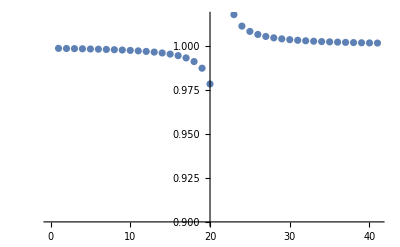

```mathematica
ListPlot[Table[N[gaNormDeterminant[testMVProto/(gaNormDeterminant[testMVProto]-i)-1]],{i,-2000,2000,100}],AxesOrigin->{20,0.9}]
```

```mathematica
logFormExactRezultForSeries=gaPE[gaLogarithmOfMV[testMV,gaIncludeFreeMV->False,Quiet->True]]
Collect[Expand[%],_𝕖,N[#,30]&]
```

1/2 (1/2 Log[131/((20+39693^(1/4))^2)]+1/2 Log[303/((20+39693^(1/4))^2)]+((20+39693^(1/4)) (π+ArcTan[(√115 (-20-39693^(1/4)))/(4 (20+39693^(1/4)))]) (-(6 1030+2030-3 3030)/(20+39693^(1/4))+(3 1030+10 2030+2 3030)/(20+39693^(1/4))+(3 12030+13030-6 23030)/(20+39693^(1/4))-(-2 12030+10 13030-3 23030)/(20+39693^(1/4))))/(√115)+((20+39693^(1/4)) ArcTan[(√203)/10] ((6 1030+2030-3 3030)/(20+39693^(1/4))+(3 1030+10 2030+2 3030)/(20+39693^(1/4))+(3 12030+13030-6 23030)/(20+39693^(1/4))+(-2 12030+10 13030-3 23030)/(20+39693^(1/4))))/(√203)-1/2 Log[131/((20+39693^(1/4))^2)] 123030+1/2 Log[303/((20+39693^(1/4))^2)] 123030)

-0.882502350264497854639562606687+0.0331779613410063412197624179146 1030+1.17909159473838662876632852881 2030+0.415775942571823092720359679504 3030+0.48307202040137075863749735227 12030-0.438834738613362303677814128384 13030-0.572486739124922652034476636979 23030+0.209633870577054399532504873166 123030

```mathematica
expansionOrder=50;
gpSeriesAnswer=Collect[gaGeometricProductSeries[Log[#]&,{testMV,{1,expansionOrder}},Expand->Automatic]//Normal//Expand,_𝕖,N[#,30]&]
```

-60.5820188770720333781192016546-2.4458977159984704420620622056 1030+8.61631834305288503646464582765 2030+4.54756863361511648967971145544 3030+4.61486469651287826390489351917 12030-7.87606165117750551998764312664 13030-3.05156228207832641008870077916 23030+59.9091487691577685777464405802 123030

```mathematica
$MaxExtraPrecision = 5000;
expansionOrder=100;
gpSeriesAnswer=Collect[gaGeometricProductSeries[Log[#]&,{testMV,{1,expansionOrder}},Expand->Automatic]//Normal//Expand,_𝕖,N[#,30]&]
```

-12513.9873467797055778978863804-13961.8324613716425492872695982 1030+41886.7760095937464074442287097 2030+23270.1918414975655462021303517 3030+23270.2591375753981124959419262 12030-41886.0357527375881782123013905 13030-13962.4381260721356459315737685 23030+12513.3144783000122429344211976 123030

```mathematica
$MaxExtraPrecision = 5000;
expansionOrder=800;
gpSeriesAnswer=Collect[gaGeometricProductSeries[Log[#]&,{testMV,{1,expansionOrder}},Expand->Automatic]//Normal//Expand,_𝕖,N[#,30]&]
```

-1.56841589922646820181211518872×10^48+3.41647256998921632113763973795×10^48 1030-1.02494177099676489634129192139×10^49 2030-5.69412094998202720189606622992×10^48 3030-5.69412094998202720189606622992×10^48 12030+1.02494177099676489634129192139×10^49 13030+3.41647256998921632113763973795×10^48 23030+1.56841589922646820181211518872×10^48 123030

Symbolic series expansion is complicated due to piecewise functions: not clear how to proceed

#### Logarithm of Cl(3,0)

```mathematica
testAlgebra=Cl[3,0];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True]
testMV=gaGeneralMultivector[a,testAlgebra]
```

Basis vectors of 300are stored in variable gaOrthonormalBasis[Cl[3, 0, 0],InvDeg[Lex]].

{1,1300,2300,3300,12300,13300,23300,123300}

a[0]+a[1] 1300+a[2] 2300+a[3] 3300+a[4] 12300+a[5] 13300+a[6] 23300+a[7] 123300

#### Tests

Since in most cases symbolic expressions are large and difficult to simplify, in checks we will mostly use numerical comparison of final answers

Case generic

```mathematica
Off[PossibleZeroQ::ztest1];
rndReplRules=(b[#]->RandomInteger[{-100,100}])&/@Range[0,7];
orig=gaGeneralMultivector[b,testAlgebra]/.rndReplRules
logOfOrigFreeMVCF=Collect[gaPE[gaLogarithmOfMV[orig,gaIncludeFreeMV->True,Quiet->True]],_𝕖];FreeQ[(logOfOrigFreeMVCF),_Complex]
crandRules=((#->RandomInteger[{-10,10}])&/@Cases[logOfOrigFreeMVCF,C[__],Infinity])
Collect[gaPE[gaExponentOfMV[N[logOfOrigFreeMVCF/.crandRules,20]]],_𝕖]
Collect[gaPE[gaExponentOfMV[N[logOfOrigFreeMVCF/.crandRules,20]]-N[orig,20]],_𝕖,PossibleZeroQ]
```

94-76 1300-26 2300+97 3300-87 12300-23 13300-20 23300+31 123300

True

{C[2]→-10,C[2]→9,C[2]→-4,C[2]→0,C[2]→-5,C[2]→3,C[1]→3}

94.-76. 1300-26. 2300+97. 3300-87. 12300-23. 13300-20. 23300+31. 123300

True+True 1300+True 2300+True 3300+True 12300+True 13300+True 23300+True 123300

```mathematica
NMinimize[gaNormDeterminant[logOfOrigFreeMVCF/.((#->RandomInteger[{-10,10}])&/@Cases[logOfOrigFreeMVCF,C[__],Infinity])],Element[{C[1],C[2]},Integers]]
```

{61.8408,{C[1]|C[2]→0.}}

Case of center

```mathematica
rndReplRules=Flatten[{(b[#]->RandomInteger[{-100,100}])&/@{0,7},b[0|1|2|3|4|5|6|7]:>0}];
orig=gaGeneralMultivector[b,testAlgebra]/.rndReplRules
logOfOrigFreeMVCF=Collect[gaPE[gaLogarithmOfMV[orig,Method->{Automatic,gaFormula->"CoordinateFree"},gaIncludeFreeMV->True,Quiet->True]],_𝕖]
crandRules=((#->RandomInteger[{-10,10}])&/@Cases[logOfOrigFreeMVCF,C[__],Infinity])
Collect[Expand[N[gaPE[gaExponentOfMV[N[Expand[gaPE[logOfOrigFreeMVCF/.crandRules]],20]]]]],_𝕖]
Collect[%-N[orig,20],_𝕖,(Abs[#]<10^(-8))&]
Collect[gaPE[gaExponentOfMV[logOfOrigFreeMVCF/.crandRules]-orig],_𝕖,PossibleZeroQ]
```

32-96 123300

Log[32 √10]+(2 π C[3] C[3,1] 12300)/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(2 π C[3] C[3,2] 13300)/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(2 π C[3] C[3,3] 23300)/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(-ArcTan[3]+2 π C[2]) 123300

{C[3]→10,C[3,1]→2,C[3,1]→-2,C[3,2]→1,C[3,3]→7,C[3]→-10,C[3,2]→-10,C[3,1]→3,C[3,2]→-5,C[3,3]→9,C[3]→-3,C[3,3]→4,C[3,1]→5,C[3,2]→10,C[3,3]→-10,C[2]→5}

32.-96. 123300

True

True

```mathematica
crandRulesForMinimize=((#->RandomInteger[{-10,10}])&/@Union[Cases[logOfOrigFreeMVCF,C[_,_],Infinity]])
```

{C[3,1]→8,C[3,2]→-5,C[3,3]→5}

```mathematica
NMinimize[gaNormDeterminant[logOfOrigFreeMVCF/.crandRulesForMinimize],Element[Union[Cases[logOfOrigFreeMVCF,C[_],Infinity]],Integers]]
```

{4.45964,{C[2]→0,C[3]→0}}

Case of vector

```mathematica
testCaseVector=Flatten[{(b[#]->RandomInteger[{-100,100}])&/@{1,2,3},b[0|4|5|6|7]:>0}];
orig=gaGeneralMultivector[b,testAlgebra]/.testCaseVector
logOfOrigFreeMVCF=Collect[gaPE[gaLogarithmOfMV[orig,Method->{Automatic,gaFormula->"CoordinateFree"},gaIncludeFreeMV->True,Quiet->True]],_𝕖]
crandRules=((#->RandomInteger[{-10,10}])&/@Cases[logOfOrigFreeMVCF,C[__],Infinity])
Collect[Expand[N[gaPE[gaExponentOfMV[N[Expand[gaPE[logOfOrigFreeMVCF/.crandRules]],20]]]]],_𝕖]
Collect[%-N[orig,20],_𝕖,(Abs[#]<10^(-8))&]
Collect[gaPE[gaExponentOfMV[logOfOrigFreeMVCF/.crandRules]-orig],_𝕖,PossibleZeroQ]
```

65 1300+33 2300-76 3300

Log[11090]/2+38 √(2/5545) (π/2+2 π C[2]) 12300+(33 (π/2+2 π C[2]) 13300)/(√11090)-13 √(5/2218) (π/2+2 π C[2]) 23300+(π/2+2 π C[1]) 123300

{C[2]→-2,C[2]→-4,C[2]→10,C[1]→4}

0.+65. 1300+33. 2300-76. 3300

True+True 1300

True

```mathematica
crandRulesForMinimize=((#->RandomInteger[{-10,10}])&/@Union[Cases[logOfOrigFreeMVCF,C[_,_],Infinity]])
```

{}

```mathematica
NMinimize[gaNormDeterminant[logOfOrigFreeMVCF/.crandRulesForMinimize],Element[Union[Cases[logOfOrigFreeMVCF,C[_],Infinity]],Integers]]
```

{5.1147,{C[1]→0,C[2]→0}}

Case of bivector

```mathematica
testCaseBivector=Flatten[{(b[#]->RandomInteger[{-100,100}])&/@{4,5,6},b[0|1|2|3|7]:>0}];
orig=gaGeneralMultivector[b,testAlgebra]/.testCaseBivector
logOfOrigFreeMVCF=Collect[gaPE[gaLogarithmOfMV[orig,Method->{Automatic,gaFormula->"CoordinateFree"},gaIncludeFreeMV->True,Quiet->True]],_𝕖]
crandRules=((#->RandomInteger[{-10,10}])&/@Cases[logOfOrigFreeMVCF,C[__],Infinity])
Collect[Expand[gaPE[gaExponentOfMV[N[Expand[gaPE[logOfOrigFreeMVCF/.crandRules]],20]]]],_𝕖]
Collect[%-N[orig,20],_𝕖,(Abs[#]<10^(-8))&]
Collect[gaPE[gaExponentOfMV[logOfOrigFreeMVCF/.crandRules]-orig],_𝕖,PossibleZeroQ]
```

-25 12300-83 13300-23300

Log[3 √835]+5/3 √(5/167) (π/2+2 π C[2]) 12300+(83 (π/2+2 π C[2]) 13300)/(3 √835)+((π/2+2 π C[2]) 23300)/(3 √835)+(π+2 π C[1]) 123300

{C[2]→10,C[2]→-6,C[2]→-10,C[1]→-4}

0.+0. 1300+0. 2300+0. 3300-25. 12300-83. 13300-1. 23300+0. 123300

True+True 1300+True 2300+True 3300+True 12300+True 13300+True 23300+True 123300

True

```mathematica
crandRulesForMinimize=((#->RandomInteger[{-10,10}])&/@Union[Cases[logOfOrigFreeMVCF,C[_,_],Infinity]])
```

{}

```mathematica
NMinimize[gaNormDeterminant[logOfOrigFreeMVCF/.crandRulesForMinimize],Element[Union[Cases[logOfOrigFreeMVCF,C[_],Infinity]],Integers]]
```

{5.54094,{C[1]→-1,C[2]→0}}

Seems both norm values are equal, no contradiction

```mathematica
N[{gaNormDeterminant[logOfOrigFreeMVCF/.{C[1]->0,C[2]->0}],
gaNormDeterminant[logOfOrigFreeMVCF/.{C[1]->-1,C[2]->0}]},20]
```

{5.5409392661736674891,5.5409392661736674891}

Case of vector+bivector

```mathematica
testCaseBivector=Flatten[{(b[#]->RandomInteger[{-100,100}])&/@{1,2,3,4,5,6},b[0|7]:>0}];
orig=gaGeneralMultivector[b,testAlgebra]/.testCaseBivector
logOfOrigFreeMVCF=Collect[gaPE[gaLogarithmOfMV[orig,Method->{Automatic,gaFormula->"CoordinateFree"},gaIncludeFreeMV->True,Quiet->True]],_𝕖]
crandRules=((#->RandomInteger[{-10,10}])&/@Cases[logOfOrigFreeMVCF,C[__],Infinity])
Collect[Expand[gaPE[gaExponentOfMV[N[Expand[gaPE[logOfOrigFreeMVCF/.crandRules]],20]]]],_𝕖]
Collect[%-N[orig,20],_𝕖,(Abs[#]<10^(-8))&]
Collect[gaPE[gaExponentOfMV[logOfOrigFreeMVCF/.crandRules]-orig],_𝕖,PossibleZeroQ]
```

38 1300+60 2300-47 3300-27 12300-22 13300-14 23300

1/2 Log[8462498/(5844+2 √12769333)+1/2 (5844+2 √12769333)]+((-78166 √(2/(5844+2 √12769333))-7 √(2 (5844+2 √12769333))) (π/2+2 π C[2]) 1300)/(8462498/(5844+2 √12769333)+1/2 (5844+2 √12769333))+((-123420 √(2/(5844+2 √12769333))+11 √(2 (5844+2 √12769333))) (π/2+2 π C[2]) 2300)/(8462498/(5844+2 √12769333)+1/2 (5844+2 √12769333))+((96679 √(2/(5844+2 √12769333))-27 √(1/2 (5844+2 √12769333))) (π/2+2 π C[2]) 3300)/(8462498/(5844+2 √12769333)+1/2 (5844+2 √12769333))+((55539 √(2/(5844+2 √12769333))+47 √(1/2 (5844+2 √12769333))) (π/2+2 π C[2]) 12300)/(8462498/(5844+2 √12769333)+1/2 (5844+2 √12769333))+((45254 √(2/(5844+2 √12769333))+30 √(2 (5844+2 √12769333))) (π/2+2 π C[2]) 13300)/(8462498/(5844+2 √12769333)+1/2 (5844+2 √12769333))+((28798 √(2/(5844+2 √12769333))-19 √(2 (5844+2 √12769333))) (π/2+2 π C[2]) 23300)/(8462498/(5844+2 √12769333)+1/2 (5844+2 √12769333))+(π+ArcTan[(-5844-2 √12769333)/4114]+2 π C[1]) 123300

{C[2]→-10,C[2]→-9,C[2]→-6,C[2]→2,C[2]→9,C[2]→1,C[1]→-4}

0.+38. 1300+60. 2300-47. 3300-27. 12300-22. 13300-14. 23300+0. 123300

True+True 1300+True 2300+True 3300+True 12300+True 13300+True 23300+True 123300

PossibleZeroQ::ztest: Unable to decide whether numeric quantities {Cos[(39 √(272081503042861+74623982052 √12769333) π)/(25538666+5844 √12769333)],1461 √((2 (25538666+5844 Power[«2»]))/(74623982052+Times[«2»])) Cos[(39 √(272081503042861+Times[«2»]) π)/(25538666+Times[«2»])]+√((12769333 (25538666+5844 Power[«2»]))/(2 (74623982052+Times[«2»]))) Cos[(39 √(272081503042861+Times[«2»]) π)/(25538666+Times[«2»])]} are equal to zero. Assuming they are.

True+True 1300+True 2300+True 3300+True 12300+True 13300+True 23300+True 123300

```mathematica
crandRulesForMinimize=((#->RandomInteger[{-10,10}])&/@Union[Cases[logOfOrigFreeMVCF,C[_,_],Infinity]])
```

{}

```mathematica
NMinimize[gaNormDeterminant[logOfOrigFreeMVCF/.crandRulesForMinimize],Element[Union[Cases[logOfOrigFreeMVCF,C[_],Infinity]],Integers]]
```

{4.99947,{C[1]→0,C[2]→0}}

vector + bivector for which sqrt exists

```mathematica
gaSqrtOfMV[𝕖[3]+𝕖[1,2],Quiet->True]//N
```

{-0.321797-0.776887 3300+0.321797 12300-0.776887 123300,-0.776887-0.321797 3300-0.776887 12300+0.321797 123300,0.321797+0.776887 3300-0.321797 12300+0.776887 123300,0.776887+0.321797 3300+0.776887 12300-0.321797 123300}

```mathematica
gaLogarithmOfMV[𝕖[3]+𝕖[1,2],Quiet->True]
```

1/4 π ((-1-123300)\[GeometricProduct](3300+12300))+Log[2]/2+3/4 π 123300

```mathematica
gaExponentOfMV[(1/2)gaLogarithmOfMV[𝕖[3]+𝕖[1,2],Quiet->True]]//gaPE//Expand//N
```

0.321797+0.776887 3300-0.321797 12300+0.776887 123300

```mathematica
orig=𝕖[3]+𝕖[1,2]
logOfOrigFreeMVCF=Collect[gaPE[gaLogarithmOfMV[𝕖[3]+𝕖[1,2],Method->{Automatic,gaFormula->"CoordinateFree"},gaIncludeFreeMV->True,Quiet->True]],_𝕖]
crandRules=((#->RandomInteger[{-10,10}])&/@Cases[logOfOrigFreeMVCF,C[__],Infinity])
Collect[Expand[gaPE[gaExponentOfMV[N[Expand[gaPE[logOfOrigFreeMVCF/.crandRules]],20]]]],_𝕖]
Collect[%-N[orig,20],_𝕖,(Abs[#]<10^(-8))&]
Collect[gaPE[gaExponentOfMV[logOfOrigFreeMVCF/.crandRules]-orig],_𝕖,PossibleZeroQ]
```

3300+12300

Log[2]/2+(-π/2-2 π C[2]) 12300+((3 π)/4+2 π C[1]) 123300

{C[2]→0,C[1]→-6}

0.+1. 3300+1. 12300+0. 123300

True+True 3300+True 12300+True 123300

True

```mathematica
crandRulesForMinimize=((#->RandomInteger[{-10,10}])&/@Union[Cases[logOfOrigFreeMVCF,C[_,_],Infinity]])
```

{}

```mathematica
NMinimize[gaNormDeterminant[logOfOrigFreeMVCF/.crandRulesForMinimize],Element[Union[Cases[logOfOrigFreeMVCF,C[_],Infinity]],Integers]]
```

{1.83964,{C[1]→0,C[2]→0}}

vector + bivector for which sqrt exists When 𝕖[1]-𝕖[1,2] is added it is in fact freeMV added. Therefore mismatch in input, which is assumed don’t have parts which exponentiate to 1. Not a problem in fact

```mathematica
gaLogarithmOfMV[-5+1300-12300-4 123300,Quiet->True]
```

Log[41]/2+(-π+ArcTan[4/5]) 123300

Case of center with bad b (add 𝕖[1]-𝕖[1,2], or 𝕖[1]-𝕖[1,2], etc, which do not change value of bplus bminus)

```mathematica
rndReplRules=Flatten[{(b[#]->RandomInteger[{-100,100}])&/@{0,7},b[1|2|3|4|5|6]:>0}];
orig=((gaGeneralMultivector[b,testAlgebra]/.rndReplRules)+𝕖[1]-𝕖[1,2])
logOfOrigFreeMVCF=Collect[gaPE[gaLogarithmOfMV[orig,Method->{Automatic,gaFormula->"CoordinateFree"},gaIncludeFreeMV->True,Quiet->False]],_𝕖]
crandRules=((#->RandomInteger[{-10,10}])&/@Cases[logOfOrigFreeMVCF,C[__],Infinity])
Collect[Expand[gaPE[gaExponentOfMV[N[Expand[gaPE[logOfOrigFreeMVCF/.crandRules]],20]]]],_𝕖]
Collect[%-N[orig,20],_𝕖,(Abs[#]<10^(-8))&]
Collect[gaPE[gaExponentOfMV[logOfOrigFreeMVCF/.crandRules]-orig],_𝕖,PossibleZeroQ]
```

16+1300-12300-100 123300

b+= 0

b-= 0

(k^2)_+= 10256

(k^2)_-= 10256

Log[k^2+]+Log[k^2-] !zeroQ[bM^2+bP^2]&&Not[zeroQ[a0]&&zeroQ[a7]&&Not[And@@(zeroQ/@Flatten[{aV,aB}])]]

vbLog[k^2+]+vbLog[k^2-] zeroQ[bM^2+bP^2]&&(!zeroQ[a0^2+a7^2])

vbArctan[] (zeroQ[bM^2+bP^2])&&(!zeroQ[a0^2+a7^2])

A_I (zeroQ[bM^2+bP^2])&&(!zeroQ[a0^2+a7^2])

sLog= Log[4 √641]

vbLog= 0

vbArctan= (2 π C[3] (C[3,1] 12300+C[3,2] 13300+C[3,3] 23300))/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))

pseudoTerm= (-ArcTan[25/4]+2 π C[2]) 123300

Log[4 √641]+(2 π C[3] C[3,1] 12300)/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(2 π C[3] C[3,2] 13300)/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(2 π C[3] C[3,3] 23300)/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(-ArcTan[25/4]+2 π C[2]) 123300

{C[3]→-5,C[3,1]→8,C[3,1]→7,C[3,2]→-2,C[3,3]→3,C[3]→-4,C[3,2]→-4,C[3,1]→9,C[3,2]→0,C[3,3]→-8,C[3]→9,C[3,3]→7,C[3,1]→-5,C[3,2]→-8,C[3,3]→9,C[2]→0}

16.+0. 1300+0. 2300+0. 3300+0. 12300+0. 13300+0. 23300-100. 123300

True+False 1300+True 2300+True 3300+False 12300+True 13300+True 23300+True 123300

False 1300+False 12300

```mathematica
crandRulesForMinimize=((#->RandomInteger[{-10,10}])&/@Union[Cases[logOfOrigFreeMVCF,C[_,_],Infinity]])
```

{C[3,1]→7,C[3,2]→-2,C[3,3]→-9}

```mathematica
logOfOrigFreeMVCF
```

Log[4 √641]+(2 π C[3] C[3,1] 12300)/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(2 π C[3] C[3,2] 13300)/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(2 π C[3] C[3,3] 23300)/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(-ArcTan[25/4]+2 π C[2]) 123300

```mathematica
NMinimize[gaNormDeterminant[logOfOrigFreeMVCF/.crandRulesForMinimize],Element[Union[Cases[logOfOrigFreeMVCF,C[_],Infinity]],Integers]]
```

{4.8289,{C[2]→0,C[3]→0}}

Logarithm of 1 (should give free MV) and 0 and -1 (test separately)

```mathematica
rezlog0=gaLogarithmOfMV[0,gaIncludeFreeMV->True,Quiet->False]
```

b+= 0

b-= 0

(k^2)_+= 0

(k^2)_-= 0

Log[k^2+]+Log[k^2-] !zeroQ[bM^2+bP^2]&&Not[zeroQ[a0]&&zeroQ[a7]&&Not[And@@(zeroQ/@Flatten[{aV,aB}])]]

vbLog[k^2+]+vbLog[k^2-] zeroQ[bM^2+bP^2]&&(zeroQ[a0^2+a7^2])&&(And@@(zeroQ/@Flatten[{aV,aB}]))

vbArctan[] zeroQ[bM^2+bP^2]&&(zeroQ[a0^2+a7^2])&&(And@@(zeroQ/@Flatten[{aV,aB}]))

A_I zeroQ[bM^2+bP^2]&&(zeroQ[a0^2+a7^2])&&(And@@(zeroQ/@Flatten[{aV,aB}]))

sLog= Hold[Log[0]]

vbLog= 0

vbArctan= (2 π C[3] (C[3,1] 12300+C[3,2] 13300+C[3,3] 23300))/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))

pseudoTerm= (2 π C[5] (C[5,1] 12300+C[5,2] 13300+C[5,3] 23300))/(√(C[5,1]^2+C[5,2]^2+C[5,3]^2))

Hold[Log[0]]+(2 π C[3] (C[3,1] 12300+C[3,2] 13300+C[3,3] 23300))/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(2 π C[5] (C[5,1] 12300+C[5,2] 13300+C[5,3] 23300))/(√(C[5,1]^2+C[5,2]^2+C[5,3]^2))

```mathematica
rezlogm1=gaLogarithmOfMV[-1,gaIncludeFreeMV->True,Quiet->True]
```

(2 π C[3] (C[3,1] 12300+C[3,2] 13300+C[3,3] 23300))/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(π+2 π C[2]) 123300

```mathematica
crandRulesForMinimize=((#->RandomInteger[{-10,10}])&/@Union[Cases[rezlogm1,C[_,_],Infinity]])
```

{C[3,1]→3,C[3,2]→-5,C[3,3]→3}

```mathematica
NMinimize[gaNormDeterminant[rezlogm1/.crandRulesForMinimize],Element[Union[Cases[rezlogm1,C[_],Infinity]],Integers]]
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{3.14159,{C[2]→0,C[3]→0}}

```mathematica
rndReplRules=Flatten[{(b[#]->RandomInteger[{-100,100}])&/@{0,7},b[1|2|3|4|5|6]:>0}];
orig=-1
logOfOrigFreeMVCF=Collect[gaPE[gaLogarithmOfMV[orig,Method->{Automatic,gaFormula->"CoordinateFree"},gaIncludeFreeMV->True,Quiet->False]],_𝕖]
crandRules=((#->RandomInteger[{-10,10}])&/@Cases[logOfOrigFreeMVCF,C[__],Infinity])
Collect[Expand[gaPE[gaExponentOfMV[N[Expand[gaPE[logOfOrigFreeMVCF/.crandRules]],20]]]],_𝕖]
Collect[%-N[orig,20],_𝕖,(Abs[#]<10^(-8))&]
Collect[gaPE[gaExponentOfMV[logOfOrigFreeMVCF/.crandRules]-orig],_𝕖,PossibleZeroQ]
```

-1

b+= 0

b-= 0

(k^2)_+= 1

(k^2)_-= 1

Log[k^2+]+Log[k^2-] !zeroQ[bM^2+bP^2]&&Not[zeroQ[a0]&&zeroQ[a7]&&Not[And@@(zeroQ/@Flatten[{aV,aB}])]]

vbLog[k^2+]+vbLog[k^2-] zeroQ[bM^2+bP^2]&&(!zeroQ[a0^2+a7^2])

vbArctan[] (zeroQ[bM^2+bP^2])&&(!zeroQ[a0^2+a7^2])

A_I (zeroQ[bM^2+bP^2])&&(!zeroQ[a0^2+a7^2])

sLog= 0

vbLog= 0

vbArctan= (2 π C[3] (C[3,1] 12300+C[3,2] 13300+C[3,3] 23300))/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))

pseudoTerm= (π+2 π C[2]) 123300

(2 π C[3] C[3,1] 12300)/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(2 π C[3] C[3,2] 13300)/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(2 π C[3] C[3,3] 23300)/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(π+2 π C[2]) 123300

{C[3]→3,C[3,1]→6,C[3,1]→-8,C[3,2]→2,C[3,3]→0,C[3]→-1,C[3,2]→-10,C[3,1]→-9,C[3,2]→4,C[3,3]→5,C[3]→-7,C[3,3]→-9,C[3,1]→-4,C[3,2]→2,C[3,3]→-4,C[2]→-9}

-1.+0. 2300+0. 3300+0. 12300+0. 13300+0. 123300

True+True 2300+True 3300+True 12300+True 13300+True 123300

True

```mathematica
logOfOrigFreeMVCF
```

(2 π C[3] C[3,1] 12300)/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(2 π C[3] C[3,2] 13300)/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(2 π C[3] C[3,3] 23300)/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(π+2 π C[2]) 123300

```mathematica
FullSimplify[Expand[gaPE[gaExponentOfMV[logOfOrigFreeMVCF]]],Assumptions->Element[Cases[logOfOrigFreeMVCF,C[__],Infinity],Integers]]
```

-1

Case a0*bM-a7*bP

```mathematica
a0=gaGeneralMultivector[a,testAlgebra,{0}];aV=gaGeneralMultivector[a,testAlgebra,{1}];aB=gaGeneralMultivector[a,testAlgebra,{2}];aP=gaGeneralMultivector[a,testAlgebra,{3}];
a7=gaPE[-gaI[testAlgebra]\[GeometricProduct]aP];
iP=Expand[gaPE[(aV\[InnerProduct]aV+aB\[InnerProduct]aB)]];
oP=Expand[gaPE[-gaI[testAlgebra]\[GeometricProduct](2\[GeometricProduct]aV\[OuterProduct]aB)]];
bP=Piecewise[{
{Sqrt[(iP+Sqrt[oP^2+iP^2])/2],
(!GeometricAlgebra`p`zeroQ[oP])},
{ 
Sqrt[iP],
(GeometricAlgebra`p`zeroQ[oP]&&GeometricAlgebra`p`positiveQ[iP])},
{
0,
(GeometricAlgebra`p`zeroQ[oP]&&GeometricAlgebra`p`negativeQ[iP])},
{
0,
(GeometricAlgebra`p`zeroQ[oP]&&GeometricAlgebra`p`zeroQ[iP])}
},$Failed];

bM=Piecewise[{
{oP/Sqrt[2*(iP+Sqrt[oP^2+iP^2])],
(!GeometricAlgebra`p`zeroQ[oP])},
{ 
0,
(GeometricAlgebra`p`zeroQ[oP]&&GeometricAlgebra`p`positiveQ[iP])},
{
Sqrt[-iP],
(GeometricAlgebra`p`zeroQ[oP]&&GeometricAlgebra`p`negativeQ[iP])},
{
0,
(GeometricAlgebra`p`zeroQ[oP]&&GeometricAlgebra`p`zeroQ[iP])}
},$Failed];

kP2=(bP+a0)^2+(bM+a7)^2;
kM2=(bP-a0)^2+(bM-a7)^2;
```

Case when we add MV exponent of which gives 1. Then, of course, logarithm of such a MV always yields 0. And computing exponent we cannot hope to reproduce the same MV.  So, everything is Ok here.

```mathematica
finCasesRandSpecCond=FindInstance[{a[0]*bM-a[7]*bP==0,a[0]<0,a[1]≠0,a[6]≠0,Element[{a/@Range[0,7]},Reals]},a/@Range[0,7],Reals,1][[1]]/.{a->b}
```

{b[0]→-1/2,b[1]→-1,b[2]→0,b[3]→-1,b[4]→-1,b[5]→0,b[6]→1,b[7]→0}

```mathematica
finCasesRandSpecCond=FindInstance[{a[0]*bM-a[7]*bP==0,a[0]>1,a[1]≠0,a[6]≠0,Element[{a/@Range[0,7]},Reals]},a/@Range[0,7],Reals,1][[1]]/.{a->b}
```

{b[0]→2,b[1]→-1,b[2]→0,b[3]→-1,b[4]→-1,b[5]→0,b[6]→1,b[7]→0}

```mathematica
finCasesRandSpecCond={b[0]->-1/2,b[1]->-1,b[2]->0,b[3]->-1,b[4]->-1,b[5]->0,b[6]->1,b[7]->0};
```

```mathematica
testCase=finCasesRandSpecCond;
orig=gaGeneralMultivector[b,testAlgebra]/.testCase
logOfOrig=Collect[gaPE[gaLogarithmOfMV[orig,Quiet->True]],_𝕖,Simplify]
logOfOrigFreeMVCF=Collect[Simplify[gaPE[gaLogarithmOfMV[orig,Method->{Automatic,gaFormula->"CoordinateFree"},gaIncludeFreeMV->True,Quiet->False]]],_𝕖,Simplify]
crandRules=((#->RandomInteger[{-10,10}])&/@Cases[logOfOrigFreeMVCF,C[__],Infinity])
Collect[gaPE[gaExponentOfMV[N[logOfOrigFreeMVCF/.crandRules,20]]],_𝕖]
Collect[gaPE[gaExponentOfMV[logOfOrigFreeMVCF/.crandRules]-N[orig,20]],_𝕖,PossibleZeroQ]
difference=orig-gaExponentOfMV[logOfOrigFreeMVCF/.crandRules]
gaExponentOfMV[difference]
```

-1/2-1300-3300-12300+23300

-Log[2]+π 123300

b+= 0

b-= 0

(k^2)_+= 1/4

(k^2)_-= 1/4

Log[k^2+]+Log[k^2-] !zeroQ[bM^2+bP^2]&&Not[zeroQ[a0]&&zeroQ[a7]&&Not[And@@(zeroQ/@Flatten[{aV,aB}])]]

vbLog[k^2+]+vbLog[k^2-] zeroQ[bM^2+bP^2]&&(!zeroQ[a0^2+a7^2])

vbArctan[] (zeroQ[bM^2+bP^2])&&(!zeroQ[a0^2+a7^2])

A_I (zeroQ[bM^2+bP^2])&&(!zeroQ[a0^2+a7^2])

sLog= -Log[2]

vbLog= 0

vbArctan= (2 π C[3] (C[3,1] 12300+C[3,2] 13300+C[3,3] 23300))/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))

pseudoTerm= (π+2 π C[2]) 123300

-Log[2]+(2 π C[3] C[3,1] 12300)/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(2 π C[3] C[3,2] 13300)/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(2 π C[3] C[3,3] 23300)/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(π+2 π C[2]) 123300

{C[3]→-3,C[3,1]→5,C[3,1]→-8,C[3,2]→0,C[3,3]→1,C[3]→-5,C[3,2]→3,C[3,1]→4,C[3,2]→9,C[3,3]→3,C[3]→7,C[3,3]→-3,C[3,1]→-7,C[3,2]→10,C[3,3]→9,C[2]→-1}

-0.5+0. 1300+0. 3300+0. 12300+0. 23300+0. 123300

True+False 1300+False 3300+False 12300+False 23300

-1300-3300-12300+23300

1

```mathematica
logOfOrigFreeMVCF
```

-Log[2]+(2 π C[3] C[3,1] 12300)/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(2 π C[3] C[3,2] 13300)/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(2 π C[3] C[3,3] 23300)/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(π+2 π C[2]) 123300

```mathematica
FullSimplify[Collect[gaPE[gaExponentOfMV[logOfOrigFreeMVCF]],_𝕖,FullSimplify[#,Assumptions->Element[Cases[logOfOrigFreeMVCF,C[__],Infinity],Integers]]&],Assumptions->Element[Cases[logOfOrigFreeMVCF,C[__],Infinity],Integers]]
```

-1/2

Case when we both determinants (whole and vector+bivector) equal to zero. This imply that scalar and pseudoscalar is zero. So, can we find MV which after exponentiation will yield the (-𝕖1-𝕖3-𝕖1,2+𝕖2,3)?

```mathematica
gaSqrtOfMV[(-1300-3300-12300+23300)]
```

b_S= 0

b_I= 0

Sqrt[D]= 0

-b_S+Sqrt[D]= 0

{}

```mathematica
gaLogarithmOfMV[(-1300-3300-12300+23300)]
```

b+= 0

b-= 0

(k^2)_+= 0

(k^2)_-= 0

Log[k^2+]+Log[k^2-] vector and Bivector not zero and bminus or bPlus is zero

vbLog[k^2+]+vbLog[k^2-] zeroQ[bM^2+bP^2]&&(zeroQ[a0^2+a7^2])&&Not[And@@(zeroQ/@Flatten[{aV,aB}])]

vbArctan[] zeroQ[bM^2+bP^2]&&(zeroQ[a0^2+a7^2])&&Not[And@@(zeroQ/@Flatten[{aV,aB}])]

A_I (zeroQ[kP2]||zeroQ[kM2])&&zeroQ[bM^2+bP^2]&&(!zeroQ[a0^2+a7^2])

sLog= {}

vbLog= {}

vbArctan= {}

pseudoTerm= {}

{}

Case b-=0, [with infinite coefficients, not tested minimal norm conjecture, this example sometimes can take very long to complete or to crash kernel, inactivated]

```mathematica
a0=gaGeneralMultivector[a,testAlgebra,{0}];aV=gaGeneralMultivector[a,testAlgebra,{1}];aB=gaGeneralMultivector[a,testAlgebra,{2}];aP=gaGeneralMultivector[a,testAlgebra,{3}];
a7=gaPE[-gaI[testAlgebra]\[GeometricProduct]aP];
iP=Expand[gaPE[(aV\[InnerProduct]aV+aB\[InnerProduct]aB)]];
oP=Expand[gaPE[-gaI[testAlgebra]\[GeometricProduct](2\[GeometricProduct]aV\[OuterProduct]aB)]];
bP=Piecewise[{
{Sqrt[(iP+Sqrt[oP^2+iP^2])/2],
(!GeometricAlgebra`p`zeroQ[oP])},
{ 
Sqrt[iP],
(GeometricAlgebra`p`zeroQ[oP]&&GeometricAlgebra`p`positiveQ[iP])},
{
0,
(GeometricAlgebra`p`zeroQ[oP]&&GeometricAlgebra`p`negativeQ[iP])},
{
0,
(GeometricAlgebra`p`zeroQ[oP]&&GeometricAlgebra`p`zeroQ[iP])}
},$Failed];

bM=Piecewise[{
{oP/Sqrt[2*(iP+Sqrt[oP^2+iP^2])],
(!GeometricAlgebra`p`zeroQ[oP])},
{ 
0,
(GeometricAlgebra`p`zeroQ[oP]&&GeometricAlgebra`p`positiveQ[iP])},
{
Sqrt[-iP],
(GeometricAlgebra`p`zeroQ[oP]&&GeometricAlgebra`p`negativeQ[iP])},
{
0,
(GeometricAlgebra`p`zeroQ[oP]&&GeometricAlgebra`p`zeroQ[iP])}
},$Failed];

kP2=(bP+a0)^2+(bM+a7)^2;
kM2=(bP-a0)^2+(bM-a7)^2;
```

```mathematica
finCasesRandkP0=FindInstance[{kP2==0,Element[{a/@Range[0,7]},Reals],a[3]!=0,a[4]!=0,a[2]!=0,a[1]!=0,a[5]!=0,a[6]!=0,a[0]!=0},a/@Range[0,7],Reals,1]
```

{{a[0]→-(√(24447/2))/1024,a[1]→-1,a[2]→-2,a[3]→-1,a[4]→-4575/2048,a[5]→-57/64,a[6]→927/2048,a[7]→0}}

```mathematica
finCasesRandkM0=FindInstance[{kM2==0,Element[{a/@Range[0,7]},Reals],a[3]!=0,a[4]!=0,a[2]!=0,a[1]!=0,a[5]!=0,a[6]!=0,a[0]!=0},a/@Range[0,7],Reals,1]
```

{{a[0]→(√(24447/2))/1024,a[1]→-1,a[2]→-2,a[3]→-1,a[4]→-4575/2048,a[5]→-57/64,a[6]→927/2048,a[7]→0}}

```mathematica
kM2s=Assuming[2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]≠0,Simplify[kM2]]
```

(a[0]-(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))/(√2))^2+(-(√2 (a[3] a[4]-a[2] a[5]+a[1] a[6]))/(√(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√(4 (a[3] a[4]-a[2] a[5]+a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+a[7])^2

```mathematica
rnda1a6=(a[#]->RandomInteger[{-10,10}])&/@Range[1,6];
a0a7KM2=Flatten[{rnda1a6,Flatten[Solve[#,Variables[#]]&/@((#==0)&/@First/@List@@(kM2s/.rnda1a6))]}]
kM2/.a0a7KM2//Simplify
```

{a[1]→-6,a[2]→-5,a[3]→10,a[4]→-10,a[5]→-4,a[6]→-7,a[0]→√(2 (-1+√1522)),a[7]→-39 √(2/(-1+√1522))}

0

```mathematica
orig=gaGeneralMultivector[a,testAlgebra]/.a0a7KM2
```

√(2 (-1+√1522))-6 1300-5 2300+10 3300-10 12300-4 13300-7 23300-39 √(2/(-1+√1522)) 123300

If Log[0] don’t appear, then it means it was present in a hidden form (the program was corrected to test these cases)

```mathematica
logOfOrigFreeMVCFordinary=Collect[gaPE[gaLogarithmOfMV[orig,Method->{Automatic,gaFormula->"CoordinateFree"},gaIncludeFreeMV->False,Quiet->False]],_𝕖]
```

b+= √(1/2 (-4+4 √1522))

b-= -78 √(2/(-4+4 √1522))

(k^2)_+= (-39 √(2/(-1+√1522))-78 √(2/(-4+4 √1522)))^2+(√(2 (-1+√1522))+√(1/2 (-4+4 √1522)))^2

(k^2)_-= (39 √(2/(-1+√1522))-78 √(2/(-4+4 √1522)))^2+(-√(2 (-1+√1522))+√(1/2 (-4+4 √1522)))^2

Log[k^2+]+Log[k^2-] !zeroQ[bM^2+bP^2]

PossibleZeroQ::ztest1: Unable to decide whether numeric quantity -6084/(√(1523-2 √1522))+3042/(-1+√1522)+12168/(-4+4 √1522) is equal to zero. Assuming it is.

vbLog[k^2+]+vbLog[k^2-] !zeroQ[bM^2+bP^2]

vbArctan[] (zeroQ[kP2]||zeroQ[kM2])&&(!zeroQ[bM^2+bP^2])

A_I (!zeroQ[bM^2+bP^2])&&zeroQ[(bP+a0) √kM2 -(bP-a0) √kP2]&&zeroQ[√kM2 (bM+a7) -(bM-a7) √kP2]

sLog= 1/2 (Hold[Log[0]]+1/2 Log[(-39 √(2/(-1+√1522))-78 √(2/(-4+4 √1522)))^2+(√(2 (-1+√1522))+√(1/2 (-4+4 √1522)))^2])

vbLog= (((√(1/2 (-4+4 √1522))+78 √(2/(-4+4 √1522)) 123300)\[GeometricProduct](-6 1300-5 2300+10 3300-10 12300-4 13300-7 23300)) (-Hold[Log[0]]+1/2 Log[(-39 √(2/(-1+√1522))-78 √(2/(-4+4 √1522)))^2+(√(2 (-1+√1522))+√(1/2 (-4+4 √1522)))^2]))/(2 (12168/(-4+4 √1522)+1/2 (-4+4 √1522)))

vbArctan= (GeometricAlgebra`p`cleanEvenPiInPlus$4534[π/2,2] ((78 √(2/(-4+4 √1522))-√(1/2 (-4+4 √1522)) 123300)\[GeometricProduct](-6 1300-5 2300+10 3300-10 12300-4 13300-7 23300)))/(12168/(-4+4 √1522)+1/2 (-4+4 √1522))

pseudoTerm= GeometricAlgebra`p`cleanEvenPiInPlus$4534[ArcTan[1/156 (-4+4 √1522)],1] 123300

1/2 (Hold[Log[0]]+1/2 Log[(-39 √(2/(-1+√1522))-78 √(2/(-4+4 √1522)))^2+(√(2 (-1+√1522))+√(1/2 (-4+4 √1522)))^2])+(((-468 √(2/(-4+4 √1522))-7 √(1/2 (-4+4 √1522))) π)/(2 (12168/(-4+4 √1522)+1/2 (-4+4 √1522)))+((546 √(2/(-4+4 √1522))-3 √(2 (-4+4 √1522))) (-Hold[Log[0]]+1/2 Log[(-39 √(2/(-1+√1522))-78 √(2/(-4+4 √1522)))^2+(√(2 (-1+√1522))+√(1/2 (-4+4 √1522)))^2]))/(2 (12168/(-4+4 √1522)+1/2 (-4+4 √1522)))) 1300+(((-390 √(2/(-4+4 √1522))+2 √(2 (-4+4 √1522))) π)/(2 (12168/(-4+4 √1522)+1/2 (-4+4 √1522)))+((-312 √(2/(-4+4 √1522))-5 √(1/2 (-4+4 √1522))) (-Hold[Log[0]]+1/2 Log[(-39 √(2/(-1+√1522))-78 √(2/(-4+4 √1522)))^2+(√(2 (-1+√1522))+√(1/2 (-4+4 √1522)))^2]))/(2 (12168/(-4+4 √1522)+1/2 (-4+4 √1522)))) 2300+(((780 √(2/(-4+4 √1522))-5 √(2 (-4+4 √1522))) π)/(2 (12168/(-4+4 √1522)+1/2 (-4+4 √1522)))+((780 √(2/(-4+4 √1522))+5 √(2 (-4+4 √1522))) (-Hold[Log[0]]+1/2 Log[(-39 √(2/(-1+√1522))-78 √(2/(-4+4 √1522)))^2+(√(2 (-1+√1522))+√(1/2 (-4+4 √1522)))^2]))/(2 (12168/(-4+4 √1522)+1/2 (-4+4 √1522)))) 3300+(((-780 √(2/(-4+4 √1522))-5 √(2 (-4+4 √1522))) π)/(2 (12168/(-4+4 √1522)+1/2 (-4+4 √1522)))+((780 √(2/(-4+4 √1522))-5 √(2 (-4+4 √1522))) (-Hold[Log[0]]+1/2 Log[(-39 √(2/(-1+√1522))-78 √(2/(-4+4 √1522)))^2+(√(2 (-1+√1522))+√(1/2 (-4+4 √1522)))^2]))/(2 (12168/(-4+4 √1522)+1/2 (-4+4 √1522)))) 12300+(((-312 √(2/(-4+4 √1522))-5 √(1/2 (-4+4 √1522))) π)/(2 (12168/(-4+4 √1522)+1/2 (-4+4 √1522)))+((390 √(2/(-4+4 √1522))-2 √(2 (-4+4 √1522))) (-Hold[Log[0]]+1/2 Log[(-39 √(2/(-1+√1522))-78 √(2/(-4+4 √1522)))^2+(√(2 (-1+√1522))+√(1/2 (-4+4 √1522)))^2]))/(2 (12168/(-4+4 √1522)+1/2 (-4+4 √1522)))) 13300+(((-546 √(2/(-4+4 √1522))+3 √(2 (-4+4 √1522))) π)/(2 (12168/(-4+4 √1522)+1/2 (-4+4 √1522)))+((-468 √(2/(-4+4 √1522))-7 √(1/2 (-4+4 √1522))) (-Hold[Log[0]]+1/2 Log[(-39 √(2/(-1+√1522))-78 √(2/(-4+4 √1522)))^2+(√(2 (-1+√1522))+√(1/2 (-4+4 √1522)))^2]))/(2 (12168/(-4+4 √1522)+1/2 (-4+4 √1522)))) 23300+ArcTan[1/156 (-4+4 √1522)] 123300

```mathematica
logOfOrigFreeMVCF=Collect[gaPE[gaLogarithmOfMV[orig,Method->{Automatic,gaFormula->"CoordinateFree"},gaIncludeFreeMV->True,Quiet->True]/.{C[__]:>0}],_𝕖,Simplify[(Apart[ExpandAll[#]]/.{Hold[Log[0]]->Log[x]})]&]
```

1/4 (Log[-4+12 √1522+6084/(√(1523-2 √1522))]+2 Log[x])-(√(-1+√1522) ((334840 √2+20854 √761) π+3 (-72295 √2+3137 √761) Log[-4+12 √1522+6084/(√(1523-2 √1522))]+6 (72295 √2-3137 √761) Log[x]) 1300)/(8 (-1522+√1522)^2)+(√(-1+√1522) ((-308966 √2+12574 √761) π-(111106 √2+7459 √761) Log[-4+12 √1522+6084/(√(1523-2 √1522))]+2 (111106 √2+7459 √761) Log[x]) 2300)/(8 (-1522+√1522)^2)+(5 √(-1+√1522) ((62402 √2-3124 √761) π+(28157 √2+1484 √761) Log[-4+12 √1522+6084/(√(1523-2 √1522))]-2 (28157 √2+1484 √761) Log[x]) 3300)/(4 (-1522+√1522)^2)-(5 √(-1+√1522) ((56314 √2+2968 √761) π+(-31201 √2+1562 √761) Log[-4+12 √1522+6084/(√(1523-2 √1522))]+(62402 √2-3124 √761) Log[x]) 12300)/(4 (-1522+√1522)^2)-(√(-1+√1522) (2 (111106 √2+7459 √761) π+(-154483 √2+6287 √761) Log[-4+12 √1522+6084/(√(1523-2 √1522))]+2 (154483 √2-6287 √761) Log[x]) 13300)/(8 (-1522+√1522)^2)+(√(-1+√1522) (-6 (72295 √2-3137 √761) π-(167420 √2+10427 √761) Log[-4+12 √1522+6084/(√(1523-2 √1522))]+(334840 √2+20854 √761) Log[x]) 23300)/(8 (-1522+√1522)^2)-ArcTan[1/39 (1-√1522)] 123300

```mathematica
(toExponentiateExpRaw=Collect[(gaExponentOfMV[logOfOrigFreeMVCF][[1,1,1]]//gaPE),_𝕖,(#/.(y:(Cos|Cosh|Sin|Sinh))[xx_]:>Simplify[y[Apart[xx/.{Power[z_,n:(1/2|-1/2)]:>Power[Simplify[z,Assumptions->{x>0,x<$MachineEpsilon}],n]},Trig->True]],Assumptions->{x>0&&x<$MachineEpsilon}])&])//LeafCount
```

Apart::ztest1: Unable to decide whether numeric quantity 21859918403588-113341270112 √1522-9302468 √(5464979600897-28335317528 √1522)+24368 √(1522 (5464979600897-28335317528 √1522)) is equal to zero. Assuming it is.

88077

```mathematica
(toExponentiateExpSimpl=Collect[toExponentiateExpRaw,_𝕖,(#/.(y:(Cos|Cosh|Sin|Sinh))[xx_]:>FullSimplify[y[Apart[xx/.{Power[z_,n:(1/2|-1/2)]:>Power[FullSimplify[z,Assumptions->{x>0,x<$MachineEpsilon}],n]},Trig->True]],Assumptions->{x>0&&x<$MachineEpsilon}])&])//LeafCount
```

28589

```mathematica
toExponentiateExpSimplFin=Collect[toExponentiateExpSimpl,_𝕖,FullSimplify[Together[#]/.{Power[z_,n:(1/2|-1/2)]:>Power[FullSimplify[z,Assumptions->{x>0,x<$MachineEpsilon}],n]},Assumptions->{x>0,x<$MachineEpsilon}]&]
```

1/4 √(2-√(2/761)) (4 1522^(1/4)-x)+(-6-(3 x)/(2 1522^(1/4))) 1300+(-5-(5 x)/(4 1522^(1/4))) 2300+(10+(5 x)/(2 1522^(1/4))) 3300+(-10-(5 x)/(2 1522^(1/4))) 12300+(-4-x/1522^(1/4)) 13300+(-7-(7 x)/(4 1522^(1/4))) 23300+1/4 √(2+√(2/761)) (-4 1522^(1/4)+x) 123300

```mathematica
toExponentiateExpLim=Collect[toExponentiateExpSimplFin,_𝕖,FullSimplify[Limit[#//PowerExpand//Apart,x->0]]&]
```

√(2 (-1+√1522))-6 1300-5 2300+10 3300-10 12300-4 13300-7 23300-√(2 (1+√1522)) 123300

```mathematica
toExponentiateExpLim-orig//Expand//FullSimplify
```

0

Other examples1

```mathematica
testCaseArticleSampleCandidate1={b[0]->1,b[1]->-2,b[2]->-3,b[3]->5,b[4]->5,b[5]->3,b[6]->-2,b[7]->-1};
orig=gaGeneralMultivector[b,testAlgebra]/.testCaseArticleSampleCandidate1
logOfOrig=Collect[gaPE[gaLogarithmOfMV[orig,Quiet->True]],_𝕖,Simplify]
logOfOrigFreeMVCF=Collect[Simplify[gaPE[gaLogarithmOfMV[orig,Method->{Automatic,gaFormula->"CoordinateFree"},gaIncludeFreeMV->True,Quiet->False]]],_𝕖,FullSimplify]
```

1-2 1300-3 2300+5 3300+5 12300+3 13300-2 23300-123300

Log[78]/2+(5 (π-ArcTan[(2 √38)/37]) 12300)/(2 √38)+(3 (π-ArcTan[(2 √38)/37]) 13300)/(2 √38)+((-π+ArcTan[(2 √38)/37]) 23300)/(√38)-1/4 π 123300

b+= √38

b-= √38

(k^2)_+= (-1+√38)^2+(1+√38)^2

(k^2)_-= (-1+√38)^2+(1+√38)^2

Log[k^2+]+Log[k^2-] !zeroQ[bM^2+bP^2]

vbLog[k^2+]+vbLog[k^2-] !zeroQ[bM^2+bP^2]

vbArctan[] (!zeroQ[kP2])&&(!zeroQ[kM2])&&(!zeroQ[bM^2+bP^2])

A_I (!zeroQ[bM^2+bP^2])&&((!zeroQ[(bP+a0) √kM2 -(bP-a0) √kP2])||(!zeroQ[√kM2 (bM+a7) -(bM-a7) √kP2]))

sLog= 1/2 Log[(-1+√38)^2+(1+√38)^2]

vbLog= 0

vbArctan= 1/76 (1/2 (-π-ArcTan[((-1+√38)^2-(1+√38)^2)/(2 (-1+√38) (1+√38))])+2 π C[2]) ((-√38-√38 123300)\[GeometricProduct](-2 1300-3 2300+5 3300+5 12300+3 13300-2 23300))

pseudoTerm= (ArcTan[((-1+√38) √((-1+√38)^2+(1+√38)^2)-(1+√38) √((-1+√38)^2+(1+√38)^2))/(-(-1+√38) √((-1+√38)^2+(1+√38)^2)+(1+√38) √((-1+√38)^2+(1+√38)^2))]+2 π C[1]) 123300

Log[78]/2-(5 (ArcTan[(2 √38)/37]+π (-1+4 C[2])) 12300)/(2 √38)-(3 (ArcTan[(2 √38)/37]+π (-1+4 C[2])) 13300)/(2 √38)+((ArcTan[(2 √38)/37]+π (-1+4 C[2])) 23300)/(√38)+1/4 π (-1+8 C[1]) 123300

```mathematica
crandRules=((#->RandomInteger[{-10,10}])&/@Cases[logOfOrigFreeMVCF,C[__],Infinity])
Collect[gaPE[gaExponentOfMV[logOfOrigFreeMVCF/.crandRules]],_𝕖,Simplify]//FullSimplify
```

{C[2]→0,C[2]→-6,C[2]→4,C[1]→5}

1-2 1300-3 2300+5 3300+5 12300+3 13300-2 23300-123300

```mathematica
gaNormDeterminant[orig]
```

√78

```mathematica
crandRulesForMinimize=((#->RandomInteger[{-10,10}])&/@Union[Cases[logOfOrigFreeMVCF,C[_,_],Infinity]])
```

{}

```mathematica
NMinimize[gaNormDeterminant[logOfOrigFreeMVCF/.crandRulesForMinimize],Element[Union[Cases[logOfOrigFreeMVCF,C[_],Infinity]],Integers]]
```

{2.64735,{C[1]→0,C[2]→0}}

Formula  for k_+=0: simplest known case,a[0]-a[7]<0

```mathematica
orig=-1/4-1300/4+1/4 √3 23300+1/4 √3 123300;
toExponentiate=gaLogarithmOfMV[orig]
```

b+= 1/4

b-= -(√3)/4

(k^2)_+= 0

(k^2)_-= 1

Log[k^2+]+Log[k^2-] !zeroQ[bM^2+bP^2]

vbLog[k^2+]+vbLog[k^2-] !zeroQ[bM^2+bP^2]

vbArctan[] (zeroQ[kP2]||zeroQ[kM2])&&(!zeroQ[bM^2+bP^2])

A_I (!zeroQ[bM^2+bP^2])&&zeroQ[(bP+a0) √kM2 -(bP-a0) √kP2]&&zeroQ[√kM2 (bM+a7) -(bM-a7) √kP2]

sLog= 1/2 Hold[Log[0]]

vbLog= 2 ((1/4+1/4 √3 123300)\[GeometricProduct](-1300/4+1/4 √3 23300)) Hold[Log[0]]

vbArctan= 4 GeometricAlgebra`p`cleanEvenPiInPlus$150950[π/2,2] (((√3)/4-1/4 123300)\[GeometricProduct](-1300/4+1/4 √3 23300))

pseudoTerm= GeometricAlgebra`p`cleanEvenPiInPlus$150950[π/6,1] 123300

2 π (((√3)/4-1/4 123300)\[GeometricProduct](-1300/4+1/4 √3 23300))+1/2 Hold[Log[0]]+2 ((1/4+1/4 √3 123300)\[GeometricProduct](-1300/4+1/4 √3 23300)) Hold[Log[0]]+1/6 π 123300

```mathematica
toExponentiate//gaPE//Expand
```

1/2 Hold[Log[0]]-1/2 Hold[Log[0]] 1300+1/2 π 23300+1/6 π 123300

```mathematica
toExponentiatePrepared=(Expand[gaPE[toExponentiate]]/.{Hold[Log[0]]->Log[x]})
```

Log[x]/2-1/2 Log[x] 1300+1/2 π 23300+1/6 π 123300

```mathematica
toExponentiateExp=Collect[(gaExponentOfMV[toExponentiatePrepared][[1,1,1]]//gaPE//Expand),_𝕖,FullSimplify[#,Assumptions->x>0]&]
toExponentiateExpLim=Limit[toExponentiateExp,x->0]
```

1/4 (-1+x)+1/4 (-1-x) 1300+1/4 √3 (1+x) 23300-1/4 √3 (-1+x) 123300

-1/4-1300/4+1/4 √3 23300+1/4 √3 123300

```mathematica
toExponentiateExpLim-orig//Expand
```

0

Formula for k_-=0: when k_+≠1 case

```mathematica
orig=1/4-1300/4+23300/4-1/4 123300
```

1/4-1300/4+23300/4-1/4 123300

```mathematica
toExponentiate=gaLogarithmOfMV[orig]
```

b+= 1/4

b-= -1/4

(k^2)_+= 1/2

(k^2)_-= 0

Log[k^2+]+Log[k^2-] !zeroQ[bM^2+bP^2]

vbLog[k^2+]+vbLog[k^2-] !zeroQ[bM^2+bP^2]

vbArctan[] (zeroQ[kP2]||zeroQ[kM2])&&(!zeroQ[bM^2+bP^2])

A_I (!zeroQ[bM^2+bP^2])&&zeroQ[(bP+a0) √kM2 -(bP-a0) √kP2]&&zeroQ[√kM2 (bM+a7) -(bM-a7) √kP2]

sLog= 1/2 (Hold[Log[0]]-Log[2]/2)

vbLog= 4 ((1/4+1/4 123300)\[GeometricProduct](-1300/4+23300/4)) (-Hold[Log[0]]-Log[2]/2)

vbArctan= 8 GeometricAlgebra`p`cleanEvenPiInPlus$151315[π/2,2] ((1/4-1/4 123300)\[GeometricProduct](-1300/4+23300/4))

pseudoTerm= GeometricAlgebra`p`cleanEvenPiInPlus$151315[π/4,1] 123300

4 π ((1/4-1/4 123300)\[GeometricProduct](-1300/4+23300/4))+4 ((1/4+1/4 123300)\[GeometricProduct](-1300/4+23300/4)) (-Hold[Log[0]]-Log[2]/2)+1/2 (Hold[Log[0]]-Log[2]/2)+1/4 π 123300

```mathematica
toExponentiatePrepared=(Expand[gaPE[toExponentiate]]/.{Hold[Log[0]]->Log[x]})
```

-Log[2]/4+Log[x]/2+1/4 Log[2] 1300+1/2 Log[x] 1300+1/2 π 23300+1/4 π 123300

```mathematica
toExponentiateExp=Collect[(gaExponentOfMV[toExponentiatePrepared][[1,1,1]]//gaPE//Expand),_𝕖,FullSimplify[#,Assumptions->x>0]&]
toExponentiateExpLim=Limit[toExponentiateExp,x->0]
toExponentiateExpLim-orig//Expand
```

1/4 (1-√2 x)+1/4 (-1-√2 x) 1300+1/4 (1+√2 x) 23300+1/4 (-1+√2 x) 123300

1/4-1300/4+23300/4-1/4 123300

0

Massive test

Generate many random MV and try to find cases where sqrt or exponentiation didn’t match. When changing intervals of random coefficients, don’t forget to adjust lim=10 var inside generateRandomParameters[]

```mathematica
generateRandomParameters[expr_]:=Module[{allC2=DeleteDuplicates[Cases[expr,C[__],Infinity]],lim=5},
(#->RandomInteger[{-lim,lim}])&/@allC2
]
```

```mathematica
(testcl30table=Table[{rndReplRules=(b[#]->RandomInteger[{-5,5}])&/@Range[0,7];
orig=gaGeneralMultivector[b,testAlgebra]/.rndReplRules,
gaSqrtOfMV[orig,Quiet->True,VerifySolutions->False],
logOfOrigFreeMVCF=Collect[gaPE[gaLogarithmOfMV[orig,Method->{Automatic,gaFormula->"CoordinateFree"},gaIncludeFreeMV->True,Quiet->True]],_𝕖],
crandRules=generateRandomParameters[logOfOrigFreeMVCF];
FreeQ[(logOfOrigFreeMVCF),_Complex]&&FreeQ[Collect[gaPE[gaExponentOfMV[N[logOfOrigFreeMVCF/.crandRules,20]]-N[orig,20]],_𝕖,PossibleZeroQ],False]},{500}])//LeafCount
```

PossibleZeroQ::ztest1: Unable to decide whether numeric quantity -√(10 (2-√3))-√(30 (2-√3))-√(10 (2+√3))+√(30 (2+√3)) is equal to zero. Assuming it is.

PossibleZeroQ::ztest1: Unable to decide whether numeric quantity 2 √(10 (2-√3))+2 √(30 (2-√3))+2 √(10 (2+√3))-2 √(30 (2+√3)) is equal to zero. Assuming it is.

PossibleZeroQ::ztest1: Unable to decide whether numeric quantity (2+√(1/2 (19+√761)))/(√((2 (19+√761))/(2624+96 Power[«2»]-3800 Power[«2»]-200 Power[«2»]-76 Power[«2»]-4 Power[«2»])))-(-2+√(1/2 (19+√761)))/(√((2 (19+√761))/(2624+96 Power[«2»]+3800 Power[«2»]+200 Power[«2»]+76 Power[«2»]+4 Power[«2»]))) is equal to zero. Assuming it is.

General::stop: Further output of PossibleZeroQ::ztest1 will be suppressed during this calculation.

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating ….

5898835

Cases where results may not match now must include Log[0]. These have to be checked separately. Exceptional cases are very rare (1 in few thousands, when coefficient range is restricted narrow to [-5,5] interval, of course increasing of interval makes them even rarer). Automatic procedure below might take long to compute or even not work: computation of limit is not trivial. Simplification takes a lot of time.

```mathematica
Cases[testcl30table,{_,{},_,_}]
```

{}

```mathematica
(testcl30tableSpec=DeleteCases[testcl30table,{__,True}])//Length
```

1

```mathematica
foundProblematic=First/@testcl30tableSpec
```

{-1-3 1300-4 2300+3300-3 12300+3 13300+4 23300+3 123300}

Check each case separately: simplification and limit can take very long time.

```mathematica
(toExponentiateExpRaw=(Collect[(gaExponentOfMV[(#[[3]]/.Hold[Log[0]]->Log[x])/.generateRandomParameters[#[[3]]]][[1,1,1]]//gaPE),_𝕖,(#/.(y:(Cos|Cosh|Sin|Sinh))[xx_]:>Simplify[y[Apart[xx/.{Power[z_,n:(1/2|-1/2)]:>Power[Simplify[z,Assumptions->{x>0,x<$MachineEpsilon}],n]},Trig->True]],Assumptions->{x>0&&x<1}])&])&/@(testcl30tableSpec))//LeafCount
```

15224

```mathematica
(toExponentiateExpSimpl=(Collect[#,_𝕖,(#/.(y:(Cos|Cosh|Sin|Sinh))[xx_]:>FullSimplify[y[Apart[xx/.{Power[z_,n:(1/2|-1/2)]:>Power[FullSimplify[z,Assumptions->{x>0,x<$MachineEpsilon}],n]},Trig->True]],Assumptions->{x>0&&x<1}])&])&/@toExponentiateExpRaw)//LeafCount
```

12988

```mathematica
toExponentiateExpSimplFin=Collect[toExponentiateExpSimpl,_𝕖,PowerExpand[FullSimplify[Simplify[Together[PowerExpand[Together[#]]]]]]&]
```

{-1+x/(2 √10)-3/20 (20+√10 x) 1300+1/5 (-20-√10 x) 2300+(2/5)^(1/4) √x Cosh[1/4 (3 Log[2]+Log[5]-2 Log[x])] 3300-3/20 (20+√10 x) 12300+3/20 (20+√10 x) 13300+1/5 (20+√10 x) 23300+(3-(3 x)/(2 √10)) 123300}

```mathematica
toExponentiateExpSimplFin=Collect[#,_𝕖,FullSimplify[Together[#]/.{Power[z_,n:(1/2|-1/2)]:>Power[FullSimplify[z,Assumptions->{x>0,x<$MachineEpsilon}],n]},Assumptions->{x>0,x<$MachineEpsilon}]&]&/@toExponentiateExpSimpl
```

```mathematica
toExponentiateExpLim=Collect[#,_𝕖,FullSimplify[Limit[#//PowerExpand//Apart,x->0]]&]&/@toExponentiateExpSimplFin
```

{-1-3 1300-4 2300+3300-3 12300+3 13300+4 23300+3 123300}

```mathematica
foundProblematic
```

{-1-3 1300-4 2300+3300-3 12300+3 13300+4 23300+3 123300}

If automatic simplification above will not give the original MV, then manual investigation is necessary, since Mathematica not always can compute the limit without help.

Thousands of MV were checked.

#### Examples for article

Article example candidate 7 (generic)(2021-10-28)

```mathematica
testCaseArticleSampleCandidate1={b[0]->-2,b[1]->1,b[2]->0,b[3]->0,b[4]->0,b[5]->0,b[6]->1,b[7]->-3};
orig=gaGeneralMultivector[b,testAlgebra]/.testCaseArticleSampleCandidate1
logOfOrig=Collect[gaPE[gaLogarithmOfMV[orig,Quiet->True]],_𝕖,Simplify]
logOfOrigFreeMVCF=Collect[Simplify[gaPE[gaLogarithmOfMV[orig,Method->{Automatic,gaFormula->"CoordinateFree"},gaIncludeFreeMV->True,Quiet->False]]],_𝕖,FullSimplify]
```

-2+1300+23300-3 123300

(3 Log[5])/4-1/4 Log[5] 1300+1/2 ArcTan[2/11] 23300+(-π+ArcTan[1/2 (1+√5)]) 123300

b+= 1

b-= 1

(k^2)_+= 5

(k^2)_-= 25

Log[k^2+]+Log[k^2-] !zeroQ[bM^2+bP^2]

vbLog[k^2+]+vbLog[k^2-] !zeroQ[bM^2+bP^2]

vbArctan[] (!zeroQ[kP2])&&(!zeroQ[kM2])&&(!zeroQ[bM^2+bP^2])

A_I (!zeroQ[bM^2+bP^2])&&((!zeroQ[(bP+a0) √kM2 -(bP-a0) √kP2])||(!zeroQ[√kM2 (bM+a7) -(bM-a7) √kP2]))

sLog= (3 Log[5])/4

vbLog= -1/8 ((1-123300)\[GeometricProduct](1300+23300)) Log[5]

vbArctan= 1/2 (-1/2 ArcTan[2/11]+2 π C[2]) ((-1-123300)\[GeometricProduct](1300+23300))

pseudoTerm= (-π+ArcTan[(-10-4 √5)/(-5-3 √5)]+2 π C[1]) 123300

(3 Log[5])/4-1/4 Log[5] 1300+1/2 (ArcTan[2/11]-4 π C[2]) 23300+(ArcTan[1/2 (1+√5)]+π (-1+2 C[1])) 123300

```mathematica
logOfOrigFreeMVCF/.{C[1]->0,C[2]->0}
```

(3 Log[5])/4-1/4 Log[5] 1300+1/2 ArcTan[2/11] 23300+(-π+ArcTan[1/2 (1+√5)]) 123300

```mathematica
freeMV=Expand[((logOfOrigFreeMVCF//Expand)-(logOfOrigFreeMVCF/.{C[1]->0,C[2]->0})//gaPE)]
```

-2 π C[2] 23300+2 π C[1] 123300

```mathematica
crandRules=((#->RandomInteger[{-10,10}])&/@Cases[logOfOrigFreeMVCF,C[__],Infinity])
Collect[gaPE[gaExponentOfMV[logOfOrigFreeMVCF/.crandRules]],_𝕖,FullSimplify]
```

{C[2]→-6,C[1]→4}

-2+1300+23300-3 123300

Article example candidate 8 (center) (2021-10-28)

```mathematica
testCaseArticleSampleCandidate1={b[0]->1,b[7]->-2,b[1|2|3|4|5|6]:>0};
orig=gaGeneralMultivector[b,testAlgebra]/.testCaseArticleSampleCandidate1
logOfOrig=Collect[gaPE[gaLogarithmOfMV[orig,Quiet->True]],_𝕖,Simplify]
logOfOrigFreeMVCF=Collect[Simplify[gaPE[gaLogarithmOfMV[orig,Method->{Automatic,gaFormula->"CoordinateFree"},gaIncludeFreeMV->True,Quiet->False]]],_𝕖,FullSimplify]
```

1-2 123300

Log[5]/2-ArcTan[2] 123300

b+= 0

b-= 0

(k^2)_+= 5

(k^2)_-= 5

Log[k^2+]+Log[k^2-] !zeroQ[bM^2+bP^2]&&Not[zeroQ[a0]&&zeroQ[a7]&&Not[And@@(zeroQ/@Flatten[{aV,aB}])]]

vbLog[k^2+]+vbLog[k^2-] zeroQ[bM^2+bP^2]&&(!zeroQ[a0^2+a7^2])

vbArctan[] (zeroQ[bM^2+bP^2])&&(!zeroQ[a0^2+a7^2])

A_I (zeroQ[bM^2+bP^2])&&(!zeroQ[a0^2+a7^2])

sLog= Log[5]/2

vbLog= 0

vbArctan= (2 π C[3] (C[3,1] 12300+C[3,2] 13300+C[3,3] 23300))/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))

pseudoTerm= (-ArcTan[2]+2 π C[2]) 123300

Log[5]/2+(2 π C[3] C[3,1] 12300)/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(2 π C[3] C[3,2] 13300)/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(2 π C[3] C[3,3] 23300)/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))+(-ArcTan[2]+2 π C[2]) 123300

```mathematica
crandRules=((#->RandomInteger[{-10,10}])&/@Cases[logOfOrigFreeMVCF,C[__],Infinity])
Collect[gaPE[gaExponentOfMV[logOfOrigFreeMVCF/.crandRules]],_𝕖,FullSimplify]
gaNormDeterminant[orig]
```

{C[3]→1,C[3,1]→5,C[3,1]→-8,C[3,2]→8,C[3,3]→-3,C[3]→-10,C[3,2]→-4,C[3,1]→9,C[3,2]→-6,C[3,3]→2,C[3]→3,C[3,3]→4,C[3,1]→-1,C[3,2]→7,C[3,3]→1,C[2]→5}

1-2 123300

√5

Other samples 1

```mathematica
orig=-9/10-(1/3)𝕖[3]
```

-9/10-3300/3

```mathematica
logOfOrig=gaLogarithmOfMV[-9/10-(1/3)𝕖[3]]
```

b+= 1/3

b-= 0

(k^2)_+= 289/900

(k^2)_-= 1369/900

Log[k^2+]+Log[k^2-] !zeroQ[bM^2+bP^2]

vbLog[k^2+]+vbLog[k^2-] !zeroQ[bM^2+bP^2]

vbArctan[] (!zeroQ[kP2])&&(!zeroQ[kM2])&&(!zeroQ[bM^2+bP^2])

A_I (!zeroQ[bM^2+bP^2])&&((!zeroQ[(bP+a0) √kM2 -(bP-a0) √kP2])||(!zeroQ[√kM2 (bM+a7) -(bM-a7) √kP2]))

sLog= 1/2 (Log[37/30]-Log[30/17])

vbLog= -1/2 (-Log[37/30]-Log[30/17]) 3300

vbArctan= GeometricAlgebra`p`cleanEvenPiInPlus$347862[0,2] 12300

pseudoTerm= GeometricAlgebra`p`cleanEvenPiInPlus$347862[π,1] 123300

1/2 (Log[37/30]-Log[30/17])-1/2 (-Log[37/30]-Log[30/17]) 3300+π 123300

```mathematica
expOfOrig=gaExponentOfMV[Expand[gaPE[logOfOrig]]]//gaPE//Expand//FullSimplify
```

-9/10-3300/3

```mathematica
{gaNormDeterminant[orig],gaNormDeterminant[expOfOrig]}
```

{(√629)/30,(√629)/30}

Other samples2

```mathematica
orig=-9/10(1/3)+𝕖[3]
```

-3/10+3300

```mathematica
logOfOrig=gaLogarithmOfMV[orig,gaIncludeFreeMV->True]
```

b+= 1

b-= 0

(k^2)_+= 49/100

(k^2)_-= 169/100

Log[k^2+]+Log[k^2-] !zeroQ[bM^2+bP^2]

vbLog[k^2+]+vbLog[k^2-] !zeroQ[bM^2+bP^2]

vbArctan[] (!zeroQ[kP2])&&(!zeroQ[kM2])&&(!zeroQ[bM^2+bP^2])

A_I (!zeroQ[bM^2+bP^2])&&zeroQ[(bP+a0) √kM2 -(bP-a0) √kP2]&&zeroQ[√kM2 (bM+a7) -(bM-a7) √kP2]

sLog= 1/2 (Log[13/10]-Log[10/7])

vbLog= 1/2 (-Log[13/10]-Log[10/7]) 3300

vbArctan= -(π/2+2 π C[2]) 12300

pseudoTerm= (π/2+2 π C[1]) 123300

1/2 (Log[13/10]-Log[10/7])+1/2 (-Log[13/10]-Log[10/7]) 3300-(π/2+2 π C[2]) 12300+(π/2+2 π C[1]) 123300

```mathematica
FullSimplify[gaExponentOfMV[Expand[gaPE[logOfOrig]]]//gaPE//Expand,Assumptions->Element[{C[1],C[2]},Integers]]
```

-3/10+3300

Other samples

```mathematica
orig=-9/10+(1/3)𝕖[3]
```

-9/10+3300/3

```mathematica
logOfOrig=gaLogarithmOfMV[orig]
```

b+= 1/3

b-= 0

(k^2)_+= 289/900

(k^2)_-= 1369/900

Log[k^2+]+Log[k^2-] !zeroQ[bM^2+bP^2]

vbLog[k^2+]+vbLog[k^2-] !zeroQ[bM^2+bP^2]

vbArctan[] (!zeroQ[kP2])&&(!zeroQ[kM2])&&(!zeroQ[bM^2+bP^2])

A_I (!zeroQ[bM^2+bP^2])&&((!zeroQ[(bP+a0) √kM2 -(bP-a0) √kP2])||(!zeroQ[√kM2 (bM+a7) -(bM-a7) √kP2]))

sLog= 1/2 (Log[37/30]-Log[30/17])

vbLog= 1/2 (-Log[37/30]-Log[30/17]) 3300

vbArctan= -GeometricAlgebra`p`cleanEvenPiInPlus$348271[0,2] 12300

pseudoTerm= GeometricAlgebra`p`cleanEvenPiInPlus$348271[π,1] 123300

1/2 (Log[37/30]-Log[30/17])+1/2 (-Log[37/30]-Log[30/17]) 3300+π 123300

```mathematica
gaExponentOfMV[Expand[gaPE[logOfOrig]]]//gaPE//Expand//FullSimplify
```

-9/10+3300/3

Article example candidate 10 (k_+≠0,k_-=0 ) (2021-10-29)

```mathematica
orig=6-8 1300-2 3300-12300+10 13300+10 23300-13 123300
```

6-8 1300-2 3300-12300+10 13300+10 23300-13 123300

```mathematica
toExponentiate=gaLogarithmOfMV[orig]
```

b+= 6

b-= -13

(k^2)_+= 820

(k^2)_-= 0

Log[k^2+]+Log[k^2-] !zeroQ[bM^2+bP^2]

vbLog[k^2+]+vbLog[k^2-] !zeroQ[bM^2+bP^2]

vbArctan[] (zeroQ[kP2]||zeroQ[kM2])&&(!zeroQ[bM^2+bP^2])

A_I (!zeroQ[bM^2+bP^2])&&zeroQ[(bP+a0) √kM2 -(bP-a0) √kP2]&&zeroQ[√kM2 (bM+a7) -(bM-a7) √kP2]

sLog= 1/2 (Hold[Log[0]]+Log[2 √205])

vbLog= 1/410 ((6+13 123300)\[GeometricProduct](-8 1300-2 3300-12300+10 13300+10 23300)) (-Hold[Log[0]]+Log[2 √205])

vbArctan= 1/205 GeometricAlgebra`p`cleanEvenPiInPlus$348368[π/2,2] ((13-6 123300)\[GeometricProduct](-8 1300-2 3300-12300+10 13300+10 23300))

pseudoTerm= GeometricAlgebra`p`cleanEvenPiInPlus$348368[ArcTan[6/13],1] 123300

1/410 π ((13-6 123300)\[GeometricProduct](-8 1300-2 3300-12300+10 13300+10 23300))+1/410 ((6+13 123300)\[GeometricProduct](-8 1300-2 3300-12300+10 13300+10 23300)) (-Hold[Log[0]]+Log[2 √205])+1/2 (Hold[Log[0]]+Log[2 √205])+ArcTan[6/13] 123300

```mathematica
(toExponentiatePrepared=Collect[Expand[gaPE[toExponentiate]],_𝕖,Simplify[FullSimplify[Together[#]/.{Hold[Log[0]]->Log[x]},Assumptions->{x>0,x<$MachineEpsilon}]]&])
```

1/4 Log[820 x^2]+1/410 (-44 π-89 Log[820]+178 Log[x]) 1300+1/82 (-12 π+13 Log[820]-26 Log[x]) 2300+1/820 (-64 π+Log[820]-2 Log[x]) 3300+1/410 (-π-16 Log[820]+32 Log[x]) 12300+1/41 (13 π+3 Log[820]-6 Log[x]) 13300+1/205 (89 π-11 Log[820]+22 Log[x]) 23300+ArcTan[6/13] 123300

```mathematica
(toExponentiateExpRaw=Collect[(gaExponentOfMV[toExponentiatePrepared][[1,1,1]]//gaPE),_𝕖])//LeafCount
```

19919

```mathematica
(toExponentiateExpSimpl=Collect[toExponentiateExpRaw,_𝕖,(#/.(y:(Cos|Cosh|Sin|Sinh))[xx_]:>FullSimplify[y[Apart[xx/.{Power[z_,n:(1/2|-1/2)]:>Power[FullSimplify[z,Assumptions->{x>0,x<$MachineEpsilon}],n]},Trig->True]],Assumptions->{x>0&&x<1}])&])//LeafCount
```

4773

```mathematica
toExponentiateExpSimplFin=Collect[toExponentiateExpSimpl,_𝕖,FullSimplify[Together[#]/.{Power[z_,n:(1/2|-1/2)]:>Power[FullSimplify[z,Assumptions->{x>0,x<$MachineEpsilon}],n]},Assumptions->{x>0,x<$MachineEpsilon}]&]
```

6-(3 x)/(√205)+(-8-(4 x)/(√205)) 1300+(-2-x/(√205)) 3300+(-1-x/(2 √205)) 12300+(10+√(5/41) x) 13300+(10+√(5/41) x) 23300+(-13+(13 x)/(2 √205)) 123300

```mathematica
toExponentiateExpSimplFinFin=Collect[toExponentiateExpSimplFin,_𝕖,FullSimplify[Expand[TrigToExp[#]],Assumptions->{x>0,x<$MachineEpsilon}]&]
```

6-(3 x)/(√205)+(-8-(4 x)/(√205)) 1300+(-2-x/(√205)) 3300+(-1-x/(2 √205)) 12300+(10+√(5/41) x) 13300+(10+√(5/41) x) 23300+(-13+(13 x)/(2 √205)) 123300

```mathematica
toExponentiateExpLim=Collect[toExponentiateExpSimplFinFin,_𝕖,FullSimplify[Limit[#,x->0,PerformanceGoal->"Speed"]]&]
toExponentiateExpLim-orig//Expand//FullSimplify
```

6-8 1300-2 3300-12300+10 13300+10 23300-13 123300

0

#### Particular cases of Log

Log of  vector Ok, with free

```mathematica
freebiv[n_Integer]:=(C[n,1]𝕖[1,2]+C[n,2]𝕖[1,3]+C[n,3]𝕖[2,3])/√(C[n,1]^2+C[n,2]^2+C[n,3]^2)
freevec[n_Integer]:=(C[n,1]𝕖[1]+C[n,2]𝕖[2]+C[n,3]𝕖[3])/√(C[n,1]^2+C[n,2]^2+C[n,3]^2)
```

```mathematica
gaGeneralMultivector[a,testAlgebra,{1}]\[GeometricProduct]gaGeneralMultivector[a,testAlgebra,{1}]//gaPE
```

a[1]^2+a[2]^2+a[3]^2

```mathematica
logFormExactRezultVector=gaLogarithmOfMV[gaGeneralMultivector[b,testAlgebra,{1}],gaIncludeFreeMV->True,Quiet->True]
```

(Piecewise[{{0, (Piecewise[{{√(b[1]^2+b[2]^2+b[3]^2), Positive[b[1]^2+b[2]^2+b[3]^2]}, {0, Negative[b[1]^2+b[2]^2+b[3]^2]||b[1]^2+b[2]^2+b[3]^2==0}, {$Failed, True}}])^2+(Piecewise[{{0, Positive[b[1]^2+b[2]^2+b[3]^2]}, {√(-b[1]^2-b[2]^2-b[3]^2), Negative[b[1]^2+b[2]^2+b[3]^2]}, {0, b[1]^2+b[2]^2+b[3]^2==0}, {$Failed, True}}])^2≠0||((Piecewise[{{√(b[1]^2+b[2]^2+b[3]^2), Positive[b[1]^2+b[2]^2+b[3]^2]}, {0, Negative[b[1]^2+b[2]^2+b[3]^2]||b[1]^2+b[2]^2+b[3]^2==0}, {$Failed, True}}])^2+(Piecewise[{{0, Positive[b[1]^2+b[2]^2+b[3]^2]}, {√(-b[1]^2-b[2]^2-b[3]^2), Negative[b[1]^2+b[2]^2+b[3]^2]}, {0, b[1]^2+b[2]^2+b[3]^2==0}, {$Failed, True}}])^2==0&&b[1]+b[2]+b[3]==0)}, {{}, (Piecewise[{{√(b[1]^2+b[2]^2+b[3]^2), Positive[b[1]^2+b[2]^2+b[3]^2]}, {0, Negative[b[1]^2+b[2]^2+b[3]^2]||b[1]^2+b[2]^2+b[3]^2==0}, {$Failed, True}}])^2+(Piecewise[{{0, Positive[b[1]^2+b[2]^2+b[3]^2]}, {√(-b[1]^2-b[2]^2-b[3]^2), Negative[b[1]^2+b[2]^2+b[3]^2]}, {0, b[1]^2+b[2]^2+b[3]^2==0}, {$Failed, True}}])^2==0&&b[1]+b[2]+b[3]≠0}, {$Failed, True}}])+(Piecewise[{{Log[√((Piecewise[{{√(b[1]^2+b[2]^2+b[3]^2), Positive[b[1]^2+b[2]^2+b[3]^2]}, {0, Negative[b[1]^2+b[2]^2+b[3]^2]||b[1]^2+b[2]^2+b[3]^2==0}, {$Failed, True}}])^2+(Piecewise[{{0, Positive[b[1]^2+b[2]^2+b[3]^2]}, {√(-b[1]^2-b[2]^2-b[3]^2), Negative[b[1]^2+b[2]^2+b[3]^2]}, {0, b[1]^2+b[2]^2+b[3]^2==0}, {$Failed, True}}])^2)], (Piecewise[{{√(b[1]^2+b[2]^2+b[3]^2), Positive[b[1]^2+b[2]^2+b[3]^2]}, {0, Negative[b[1]^2+b[2]^2+b[3]^2]||b[1]^2+b[2]^2+b[3]^2==0}, {$Failed, True}}])^2+(Piecewise[{{0, Positive[b[1]^2+b[2]^2+b[3]^2]}, {√(-b[1]^2-b[2]^2-b[3]^2), Negative[b[1]^2+b[2]^2+b[3]^2]}, {0, b[1]^2+b[2]^2+b[3]^2==0}, {$Failed, True}}])^2≠0||((Piecewise[{{√(b[1]^2+b[2]^2+b[3]^2), Positive[b[1]^2+b[2]^2+b[3]^2]}, {0, Negative[b[1]^2+b[2]^2+b[3]^2]||b[1]^2+b[2]^2+b[3]^2==0}, {$Failed, True}}])^2+(Piecewise[{{0, Positive[b[1]^2+b[2]^2+b[3]^2]}, {√(-b[1]^2-b[2]^2-b[3]^2), Negative[b[1]^2+b[2]^2+b[3]^2]}, {0, b[1]^2+b[2]^2+b[3]^2==0}, {$Failed, True}}])^2==0&&b[1]+b[2]+b[3]==0)}, {{}, (Piecewise[{{√(b[1]^2+b[2]^2+b[3]^2), Positive[b[1]^2+b[2]^2+b[3]^2]}, {0, Negative[b[1]^2+b[2]^2+b[3]^2]||b[1]^2+b[2]^2+b[3]^2==0}, {$Failed, True}}])^2+(Piecewise[{{0, Positive[b[1]^2+b[2]^2+b[3]^2]}, {√(-b[1]^2-b[2]^2-b[3]^2), Negative[b[1]^2+b[2]^2+b[3]^2]}, {0, b[1]^2+b[2]^2+b[3]^2==0}, {$Failed, True}}])^2==0&&b[1]+b[2]+b[3]≠0}, {$Failed, True}}])+(Piecewise[{{((1/2 ArcTan[-(Piecewise[{{√(b[1]^2+b[2]^2+b[3]^2), Positive[b[1]^2+b[2]^2+b[3]^2]}, {0, Negative[b[1]^2+b[2]^2+b[3]^2]||b[1]^2+b[2]^2+b[3]^2==0}, {$Failed, True}}])^2-(Piecewise[{{0, Positive[b[1]^2+b[2]^2+b[3]^2]}, {√(-b[1]^2-b[2]^2-b[3]^2), Negative[b[1]^2+b[2]^2+b[3]^2]}, {0, b[1]^2+b[2]^2+b[3]^2==0}, {$Failed, True}}])^2,0]+2 π C[2]) ((-(Piecewise[{{0, Positive[b[1]^2+b[2]^2+b[3]^2]}, {√(-b[1]^2-b[2]^2-b[3]^2), Negative[b[1]^2+b[2]^2+b[3]^2]}, {0, b[1]^2+b[2]^2+b[3]^2==0}, {$Failed, True}}])-(Piecewise[{{√(b[1]^2+b[2]^2+b[3]^2), Positive[b[1]^2+b[2]^2+b[3]^2]}, {0, Negative[b[1]^2+b[2]^2+b[3]^2]||b[1]^2+b[2]^2+b[3]^2==0}, {$Failed, True}}]) 123300)\[GeometricProduct](b[1] 1300+b[2] 2300+b[3] 3300)))/((Piecewise[{{√(b[1]^2+b[2]^2+b[3]^2), Positive[b[1]^2+b[2]^2+b[3]^2]}, {0, Negative[b[1]^2+b[2]^2+b[3]^2]||b[1]^2+b[2]^2+b[3]^2==0}, {$Failed, True}}])^2+(Piecewise[{{0, Positive[b[1]^2+b[2]^2+b[3]^2]}, {√(-b[1]^2-b[2]^2-b[3]^2), Negative[b[1]^2+b[2]^2+b[3]^2]}, {0, b[1]^2+b[2]^2+b[3]^2==0}, {$Failed, True}}])^2), (Piecewise[{{√(b[1]^2+b[2]^2+b[3]^2), Positive[b[1]^2+b[2]^2+b[3]^2]}, {0, Negative[b[1]^2+b[2]^2+b[3]^2]||b[1]^2+b[2]^2+b[3]^2==0}, {$Failed, True}}])^2+(Piecewise[{{0, Positive[b[1]^2+b[2]^2+b[3]^2]}, {√(-b[1]^2-b[2]^2-b[3]^2), Negative[b[1]^2+b[2]^2+b[3]^2]}, {0, b[1]^2+b[2]^2+b[3]^2==0}, {$Failed, True}}])^2≠0&&(Piecewise[{{√(b[1]^2+b[2]^2+b[3]^2), Positive[b[1]^2+b[2]^2+b[3]^2]}, {0, Negative[b[1]^2+b[2]^2+b[3]^2]||b[1]^2+b[2]^2+b[3]^2==0}, {$Failed, True}}])^2+(Piecewise[{{0, Positive[b[1]^2+b[2]^2+b[3]^2]}, {√(-b[1]^2-b[2]^2-b[3]^2), Negative[b[1]^2+b[2]^2+b[3]^2]}, {0, b[1]^2+b[2]^2+b[3]^2==0}, {$Failed, True}}])^2≠0&&(Piecewise[{{√(b[1]^2+b[2]^2+b[3]^2), Positive[b[1]^2+b[2]^2+b[3]^2]}, {0, Negative[b[1]^2+b[2]^2+b[3]^2]||b[1]^2+b[2]^2+b[3]^2==0}, {$Failed, True}}])^2+(Piecewise[{{0, Positive[b[1]^2+b[2]^2+b[3]^2]}, {√(-b[1]^2-b[2]^2-b[3]^2), Negative[b[1]^2+b[2]^2+b[3]^2]}, {0, b[1]^2+b[2]^2+b[3]^2==0}, {$Failed, True}}])^2≠0}, {(2 π C[3] (C[3,1] 12300+C[3,2] 13300+C[3,3] 23300))/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2)), (Piecewise[{{√(b[1]^2+b[2]^2+b[3]^2), Positive[b[1]^2+b[2]^2+b[3]^2]}, {0, Negative[b[1]^2+b[2]^2+b[3]^2]||b[1]^2+b[2]^2+b[3]^2==0}, {$Failed, True}}])^2+(Piecewise[{{0, Positive[b[1]^2+b[2]^2+b[3]^2]}, {√(-b[1]^2-b[2]^2-b[3]^2), Negative[b[1]^2+b[2]^2+b[3]^2]}, {0, b[1]^2+b[2]^2+b[3]^2==0}, {$Failed, True}}])^2==0&&b[1]+b[2]+b[3]==0}, {{}, (Piecewise[{{√(b[1]^2+b[2]^2+b[3]^2), Positive[b[1]^2+b[2]^2+b[3]^2]}, {0, Negative[b[1]^2+b[2]^2+b[3]^2]||b[1]^2+b[2]^2+b[3]^2==0}, {$Failed, True}}])^2+(Piecewise[{{0, Positive[b[1]^2+b[2]^2+b[3]^2]}, {√(-b[1]^2-b[2]^2-b[3]^2), Negative[b[1]^2+b[2]^2+b[3]^2]}, {0, b[1]^2+b[2]^2+b[3]^2==0}, {$Failed, True}}])^2==0&&b[1]+b[2]+b[3]≠0}, {$Failed, True}}])+(Piecewise[{{(ArcTan[-(Piecewise[{{0, Positive[b[1]^2+b[2]^2+b[3]^2]}, {√(-b[1]^2-b[2]^2-b[3]^2), Negative[b[1]^2+b[2]^2+b[3]^2]}, {0, b[1]^2+b[2]^2+b[3]^2==0}, {$Failed, True}}]),Piecewise[{{√(b[1]^2+b[2]^2+b[3]^2), Positive[b[1]^2+b[2]^2+b[3]^2]}, {0, Negative[b[1]^2+b[2]^2+b[3]^2]||b[1]^2+b[2]^2+b[3]^2==0}, {$Failed, True}}]]+2 π C[1]) 123300, (Piecewise[{{√(b[1]^2+b[2]^2+b[3]^2), Positive[b[1]^2+b[2]^2+b[3]^2]}, {0, Negative[b[1]^2+b[2]^2+b[3]^2]||b[1]^2+b[2]^2+b[3]^2==0}, {$Failed, True}}])^2+(Piecewise[{{0, Positive[b[1]^2+b[2]^2+b[3]^2]}, {√(-b[1]^2-b[2]^2-b[3]^2), Negative[b[1]^2+b[2]^2+b[3]^2]}, {0, b[1]^2+b[2]^2+b[3]^2==0}, {$Failed, True}}])^2≠0}, {(2 π C[5] (C[5,1] 12300+C[5,2] 13300+C[5,3] 23300))/(√(C[5,1]^2+C[5,2]^2+C[5,3]^2)), (Piecewise[{{√(b[1]^2+b[2]^2+b[3]^2), Positive[b[1]^2+b[2]^2+b[3]^2]}, {0, Negative[b[1]^2+b[2]^2+b[3]^2]||b[1]^2+b[2]^2+b[3]^2==0}, {$Failed, True}}])^2+(Piecewise[{{0, Positive[b[1]^2+b[2]^2+b[3]^2]}, {√(-b[1]^2-b[2]^2-b[3]^2), Negative[b[1]^2+b[2]^2+b[3]^2]}, {0, b[1]^2+b[2]^2+b[3]^2==0}, {$Failed, True}}])^2==0&&b[1]+b[2]+b[3]==0}, {{}, (Piecewise[{{√(b[1]^2+b[2]^2+b[3]^2), Positive[b[1]^2+b[2]^2+b[3]^2]}, {0, Negative[b[1]^2+b[2]^2+b[3]^2]||b[1]^2+b[2]^2+b[3]^2==0}, {$Failed, True}}])^2+(Piecewise[{{0, Positive[b[1]^2+b[2]^2+b[3]^2]}, {√(-b[1]^2-b[2]^2-b[3]^2), Negative[b[1]^2+b[2]^2+b[3]^2]}, {0, b[1]^2+b[2]^2+b[3]^2==0}, {$Failed, True}}])^2==0&&b[1]+b[2]+b[3]≠0}, {$Failed, True}}])

```mathematica
ca1=Plus@@(gaGetMV[gaPE[Refine[logFormExactRezultVector,Positive[b[1]^2+b[2]^2+b[3]^2]]]//FullSimplify//Expand,#]&/@List/@Range[0,3]//Simplify)
```

1/2 Log[b[1]^2+b[2]^2+b[3]^2]-(π (1+4 C[2]) (b[3] 12300-b[2] 13300+b[1] 23300))/(2 √(b[1]^2+b[2]^2+b[3]^2))+1/2 π (1+4 C[1]) 123300

```mathematica
finRez=1/2 Log[b[1]^2+b[2]^2+b[3]^2]-π(1+4 C[2])(b[1] 1300+b[2] 2300+b[3] 3300)\[GeometricProduct]gaI[testAlgebra]/(2 √(b[1]^2+b[2]^2+b[3]^2))+1/2 π(1+4 C[1])\[GeometricProduct] 123300
```

-(π (1+4 C[2]) ((b[1] 1300+b[2] 2300+b[3] 3300)\[GeometricProduct]123300))/(2 √(b[1]^2+b[2]^2+b[3]^2))+1/2 Log[b[1]^2+b[2]^2+b[3]^2]+1/2 π (1+4 C[1]) 123300

```mathematica
ca1-finRez//gaPE//Expand
```

0

```mathematica
rndReplRules=(b[#]->RandomInteger[{-100,100}])&/@Range[0,7]
```

{b[0]→-11,b[1]→100,b[2]→-20,b[3]→59,b[4]→14,b[5]→48,b[6]→-57,b[7]→28}

```mathematica
gaPE[(finRez/.rndReplRules)]
```

Log[13881]/2-(π (1+4 C[2]) (59 12300+20 13300+100 23300))/(2 √13881)+1/2 π (1+4 C[1]) 123300

```mathematica
freevec[3]
```

(C[3,1] 1300+C[3,2] 2300+C[3,3] 3300)/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2))

```mathematica
gaGeneralMultivector[b,testAlgebra,{1}]/.rndReplRules
Collect[gaPE[gaExponentOfMV[((finRez/.rndReplRules))/.{C[1]->RandomInteger[{-10,10}],C[2]->RandomInteger[{-10,10}],C[3]->RandomInteger[{-10,10}],C[3,1]->RandomInteger[{-10,10}],C[3,2]->RandomInteger[{-10,10}],C[3,3]->RandomInteger[{-10,10}],C[4]->RandomInteger[{-10,10}],C[4,1]->RandomInteger[{-10,10}],C[4,2]->RandomInteger[{-10,10}],C[4,3]->RandomInteger[{-10,10}]}]],_𝕖]
```

100 1300-20 2300+59 3300

100 1300-20 2300+59 3300

```mathematica
Collect[gaPE[(finRez/.rndReplRules)]-Collect[gaPE[gaLogarithmOfMV[gaGeneralMultivector[b,testAlgebra,{1}]/.rndReplRules,gaIncludeFreeMV->True]],_𝕖,Simplify],_𝕖,Simplify]
```

b+= √13881

b-= 0

(k^2)_+= 13881

(k^2)_-= 13881

Log[k^2+]+Log[k^2-] !zeroQ[bM^2+bP^2]

vbLog[k^2+]+vbLog[k^2-] !zeroQ[bM^2+bP^2]

vbArctan[] (!zeroQ[kP2])&&(!zeroQ[kM2])&&(!zeroQ[bM^2+bP^2])

A_I (!zeroQ[bM^2+bP^2])&&zeroQ[(bP+a0) √kM2 -(bP-a0) √kP2]&&zeroQ[√kM2 (bM+a7) -(bM-a7) √kP2]

sLog= Log[13881]/2

vbLog= 0

vbArctan= -((π/2+2 π C[2]) 123300\[GeometricProduct](100 1300-20 2300+59 3300))/(√13881)

pseudoTerm= (π/2+2 π C[1]) 123300

0

Log of  bivector OK.

```mathematica
logFormExactRezultBivector=gaLogarithmOfMV[gaGeneralMultivector[b,testAlgebra,{2}],gaIncludeFreeMV->True,Quiet->True]
```

(Piecewise[{{0, (Piecewise[{{√(-b[4]^2-b[5]^2-b[6]^2), Positive[-b[4]^2-b[5]^2-b[6]^2]}, {0, Negative[-b[4]^2-b[5]^2-b[6]^2]||-b[4]^2-b[5]^2-b[6]^2==0}, {$Failed, True}}])^2+(Piecewise[{{0, Positive[-b[4]^2-b[5]^2-b[6]^2]}, {√(b[4]^2+b[5]^2+b[6]^2), Negative[-b[4]^2-b[5]^2-b[6]^2]}, {0, -b[4]^2-b[5]^2-b[6]^2==0}, {$Failed, True}}])^2≠0||((Piecewise[{{√(-b[4]^2-b[5]^2-b[6]^2), Positive[-b[4]^2-b[5]^2-b[6]^2]}, {0, Negative[-b[4]^2-b[5]^2-b[6]^2]||-b[4]^2-b[5]^2-b[6]^2==0}, {$Failed, True}}])^2+(Piecewise[{{0, Positive[-b[4]^2-b[5]^2-b[6]^2]}, {√(b[4]^2+b[5]^2+b[6]^2), Negative[-b[4]^2-b[5]^2-b[6]^2]}, {0, -b[4]^2-b[5]^2-b[6]^2==0}, {$Failed, True}}])^2==0&&b[4]+b[5]+b[6]==0)}, {{}, (Piecewise[{{√(-b[4]^2-b[5]^2-b[6]^2), Positive[-b[4]^2-b[5]^2-b[6]^2]}, {0, Negative[-b[4]^2-b[5]^2-b[6]^2]||-b[4]^2-b[5]^2-b[6]^2==0}, {$Failed, True}}])^2+(Piecewise[{{0, Positive[-b[4]^2-b[5]^2-b[6]^2]}, {√(b[4]^2+b[5]^2+b[6]^2), Negative[-b[4]^2-b[5]^2-b[6]^2]}, {0, -b[4]^2-b[5]^2-b[6]^2==0}, {$Failed, True}}])^2==0&&b[4]+b[5]+b[6]≠0}, {$Failed, True}}])+(Piecewise[{{Log[√((Piecewise[{{√(-b[4]^2-b[5]^2-b[6]^2), Positive[-b[4]^2-b[5]^2-b[6]^2]}, {0, Negative[-b[4]^2-b[5]^2-b[6]^2]||-b[4]^2-b[5]^2-b[6]^2==0}, {$Failed, True}}])^2+(Piecewise[{{0, Positive[-b[4]^2-b[5]^2-b[6]^2]}, {√(b[4]^2+b[5]^2+b[6]^2), Negative[-b[4]^2-b[5]^2-b[6]^2]}, {0, -b[4]^2-b[5]^2-b[6]^2==0}, {$Failed, True}}])^2)], (Piecewise[{{√(-b[4]^2-b[5]^2-b[6]^2), Positive[-b[4]^2-b[5]^2-b[6]^2]}, {0, Negative[-b[4]^2-b[5]^2-b[6]^2]||-b[4]^2-b[5]^2-b[6]^2==0}, {$Failed, True}}])^2+(Piecewise[{{0, Positive[-b[4]^2-b[5]^2-b[6]^2]}, {√(b[4]^2+b[5]^2+b[6]^2), Negative[-b[4]^2-b[5]^2-b[6]^2]}, {0, -b[4]^2-b[5]^2-b[6]^2==0}, {$Failed, True}}])^2≠0||((Piecewise[{{√(-b[4]^2-b[5]^2-b[6]^2), Positive[-b[4]^2-b[5]^2-b[6]^2]}, {0, Negative[-b[4]^2-b[5]^2-b[6]^2]||-b[4]^2-b[5]^2-b[6]^2==0}, {$Failed, True}}])^2+(Piecewise[{{0, Positive[-b[4]^2-b[5]^2-b[6]^2]}, {√(b[4]^2+b[5]^2+b[6]^2), Negative[-b[4]^2-b[5]^2-b[6]^2]}, {0, -b[4]^2-b[5]^2-b[6]^2==0}, {$Failed, True}}])^2==0&&b[4]+b[5]+b[6]==0)}, {{}, (Piecewise[{{√(-b[4]^2-b[5]^2-b[6]^2), Positive[-b[4]^2-b[5]^2-b[6]^2]}, {0, Negative[-b[4]^2-b[5]^2-b[6]^2]||-b[4]^2-b[5]^2-b[6]^2==0}, {$Failed, True}}])^2+(Piecewise[{{0, Positive[-b[4]^2-b[5]^2-b[6]^2]}, {√(b[4]^2+b[5]^2+b[6]^2), Negative[-b[4]^2-b[5]^2-b[6]^2]}, {0, -b[4]^2-b[5]^2-b[6]^2==0}, {$Failed, True}}])^2==0&&b[4]+b[5]+b[6]≠0}, {$Failed, True}}])+(Piecewise[{{((1/2 ArcTan[-(Piecewise[{{√(-b[4]^2-b[5]^2-b[6]^2), Positive[-b[4]^2-b[5]^2-b[6]^2]}, {0, Negative[-b[4]^2-b[5]^2-b[6]^2]||-b[4]^2-b[5]^2-b[6]^2==0}, {$Failed, True}}])^2-(Piecewise[{{0, Positive[-b[4]^2-b[5]^2-b[6]^2]}, {√(b[4]^2+b[5]^2+b[6]^2), Negative[-b[4]^2-b[5]^2-b[6]^2]}, {0, -b[4]^2-b[5]^2-b[6]^2==0}, {$Failed, True}}])^2,0]+2 π C[2]) ((-(Piecewise[{{0, Positive[-b[4]^2-b[5]^2-b[6]^2]}, {√(b[4]^2+b[5]^2+b[6]^2), Negative[-b[4]^2-b[5]^2-b[6]^2]}, {0, -b[4]^2-b[5]^2-b[6]^2==0}, {$Failed, True}}])-(Piecewise[{{√(-b[4]^2-b[5]^2-b[6]^2), Positive[-b[4]^2-b[5]^2-b[6]^2]}, {0, Negative[-b[4]^2-b[5]^2-b[6]^2]||-b[4]^2-b[5]^2-b[6]^2==0}, {$Failed, True}}]) 123300)\[GeometricProduct](b[4] 12300+b[5] 13300+b[6] 23300)))/((Piecewise[{{√(-b[4]^2-b[5]^2-b[6]^2), Positive[-b[4]^2-b[5]^2-b[6]^2]}, {0, Negative[-b[4]^2-b[5]^2-b[6]^2]||-b[4]^2-b[5]^2-b[6]^2==0}, {$Failed, True}}])^2+(Piecewise[{{0, Positive[-b[4]^2-b[5]^2-b[6]^2]}, {√(b[4]^2+b[5]^2+b[6]^2), Negative[-b[4]^2-b[5]^2-b[6]^2]}, {0, -b[4]^2-b[5]^2-b[6]^2==0}, {$Failed, True}}])^2), (Piecewise[{{√(-b[4]^2-b[5]^2-b[6]^2), Positive[-b[4]^2-b[5]^2-b[6]^2]}, {0, Negative[-b[4]^2-b[5]^2-b[6]^2]||-b[4]^2-b[5]^2-b[6]^2==0}, {$Failed, True}}])^2+(Piecewise[{{0, Positive[-b[4]^2-b[5]^2-b[6]^2]}, {√(b[4]^2+b[5]^2+b[6]^2), Negative[-b[4]^2-b[5]^2-b[6]^2]}, {0, -b[4]^2-b[5]^2-b[6]^2==0}, {$Failed, True}}])^2≠0&&(Piecewise[{{√(-b[4]^2-b[5]^2-b[6]^2), Positive[-b[4]^2-b[5]^2-b[6]^2]}, {0, Negative[-b[4]^2-b[5]^2-b[6]^2]||-b[4]^2-b[5]^2-b[6]^2==0}, {$Failed, True}}])^2+(Piecewise[{{0, Positive[-b[4]^2-b[5]^2-b[6]^2]}, {√(b[4]^2+b[5]^2+b[6]^2), Negative[-b[4]^2-b[5]^2-b[6]^2]}, {0, -b[4]^2-b[5]^2-b[6]^2==0}, {$Failed, True}}])^2≠0&&(Piecewise[{{√(-b[4]^2-b[5]^2-b[6]^2), Positive[-b[4]^2-b[5]^2-b[6]^2]}, {0, Negative[-b[4]^2-b[5]^2-b[6]^2]||-b[4]^2-b[5]^2-b[6]^2==0}, {$Failed, True}}])^2+(Piecewise[{{0, Positive[-b[4]^2-b[5]^2-b[6]^2]}, {√(b[4]^2+b[5]^2+b[6]^2), Negative[-b[4]^2-b[5]^2-b[6]^2]}, {0, -b[4]^2-b[5]^2-b[6]^2==0}, {$Failed, True}}])^2≠0}, {(2 π C[3] (C[3,1] 12300+C[3,2] 13300+C[3,3] 23300))/(√(C[3,1]^2+C[3,2]^2+C[3,3]^2)), (Piecewise[{{√(-b[4]^2-b[5]^2-b[6]^2), Positive[-b[4]^2-b[5]^2-b[6]^2]}, {0, Negative[-b[4]^2-b[5]^2-b[6]^2]||-b[4]^2-b[5]^2-b[6]^2==0}, {$Failed, True}}])^2+(Piecewise[{{0, Positive[-b[4]^2-b[5]^2-b[6]^2]}, {√(b[4]^2+b[5]^2+b[6]^2), Negative[-b[4]^2-b[5]^2-b[6]^2]}, {0, -b[4]^2-b[5]^2-b[6]^2==0}, {$Failed, True}}])^2==0&&b[4]+b[5]+b[6]==0}, {{}, (Piecewise[{{√(-b[4]^2-b[5]^2-b[6]^2), Positive[-b[4]^2-b[5]^2-b[6]^2]}, {0, Negative[-b[4]^2-b[5]^2-b[6]^2]||-b[4]^2-b[5]^2-b[6]^2==0}, {$Failed, True}}])^2+(Piecewise[{{0, Positive[-b[4]^2-b[5]^2-b[6]^2]}, {√(b[4]^2+b[5]^2+b[6]^2), Negative[-b[4]^2-b[5]^2-b[6]^2]}, {0, -b[4]^2-b[5]^2-b[6]^2==0}, {$Failed, True}}])^2==0&&b[4]+b[5]+b[6]≠0}, {$Failed, True}}])+(Piecewise[{{(ArcTan[-(Piecewise[{{0, Positive[-b[4]^2-b[5]^2-b[6]^2]}, {√(b[4]^2+b[5]^2+b[6]^2), Negative[-b[4]^2-b[5]^2-b[6]^2]}, {0, -b[4]^2-b[5]^2-b[6]^2==0}, {$Failed, True}}]),Piecewise[{{√(-b[4]^2-b[5]^2-b[6]^2), Positive[-b[4]^2-b[5]^2-b[6]^2]}, {0, Negative[-b[4]^2-b[5]^2-b[6]^2]||-b[4]^2-b[5]^2-b[6]^2==0}, {$Failed, True}}]]+2 π C[1]) 123300, (Piecewise[{{√(-b[4]^2-b[5]^2-b[6]^2), Positive[-b[4]^2-b[5]^2-b[6]^2]}, {0, Negative[-b[4]^2-b[5]^2-b[6]^2]||-b[4]^2-b[5]^2-b[6]^2==0}, {$Failed, True}}])^2+(Piecewise[{{0, Positive[-b[4]^2-b[5]^2-b[6]^2]}, {√(b[4]^2+b[5]^2+b[6]^2), Negative[-b[4]^2-b[5]^2-b[6]^2]}, {0, -b[4]^2-b[5]^2-b[6]^2==0}, {$Failed, True}}])^2≠0}, {(2 π C[5] (C[5,1] 12300+C[5,2] 13300+C[5,3] 23300))/(√(C[5,1]^2+C[5,2]^2+C[5,3]^2)), (Piecewise[{{√(-b[4]^2-b[5]^2-b[6]^2), Positive[-b[4]^2-b[5]^2-b[6]^2]}, {0, Negative[-b[4]^2-b[5]^2-b[6]^2]||-b[4]^2-b[5]^2-b[6]^2==0}, {$Failed, True}}])^2+(Piecewise[{{0, Positive[-b[4]^2-b[5]^2-b[6]^2]}, {√(b[4]^2+b[5]^2+b[6]^2), Negative[-b[4]^2-b[5]^2-b[6]^2]}, {0, -b[4]^2-b[5]^2-b[6]^2==0}, {$Failed, True}}])^2==0&&b[4]+b[5]+b[6]==0}, {{}, (Piecewise[{{√(-b[4]^2-b[5]^2-b[6]^2), Positive[-b[4]^2-b[5]^2-b[6]^2]}, {0, Negative[-b[4]^2-b[5]^2-b[6]^2]||-b[4]^2-b[5]^2-b[6]^2==0}, {$Failed, True}}])^2+(Piecewise[{{0, Positive[-b[4]^2-b[5]^2-b[6]^2]}, {√(b[4]^2+b[5]^2+b[6]^2), Negative[-b[4]^2-b[5]^2-b[6]^2]}, {0, -b[4]^2-b[5]^2-b[6]^2==0}, {$Failed, True}}])^2==0&&b[4]+b[5]+b[6]≠0}, {$Failed, True}}])

```mathematica
gaGeneralMultivector[a,testAlgebra,{2}]\[GeometricProduct]gaCliffordConjugate[gaGeneralMultivector[a,testAlgebra,{2}]]//gaPE
```

a[4]^2+a[5]^2+a[6]^2

```mathematica
ca1=Plus@@(gaGetMV[gaPE[Refine[logFormExactRezultBivector,Negative[-b[4]^2-b[5]^2-b[6]^2]]]//FullSimplify//Expand,#]&/@List/@Range[0,3]//Simplify)
```

1/2 Log[b[4]^2+b[5]^2+b[6]^2]-(π (1+4 C[2]) (b[4] 12300+b[5] 13300+b[6] 23300))/(2 √(b[4]^2+b[5]^2+b[6]^2))+π (1+2 C[1]) 123300

```mathematica
rndReplRules=(b[#]->RandomInteger[{-100,100}])&/@Range[0,7]
```

{b[0]→29,b[1]→-11,b[2]→-96,b[3]→55,b[4]→-53,b[5]→-86,b[6]→-75,b[7]→87}

```mathematica
gaPE[(ca1/.rndReplRules)]
```

Log[15830]/2-(π (1+4 C[2]) (-53 12300-86 13300-75 23300))/(2 √15830)+π (1+2 C[1]) 123300

```mathematica
crandRules=((#->RandomInteger[{-10,10}])&/@Cases[ca1,C[__],Infinity])
```

{C[2]→0,C[1]→5}

```mathematica
gaGeneralMultivector[b,testAlgebra,{2}]/.rndReplRules
Collect[gaPE[gaExponentOfMV[((ca1/.rndReplRules))/.crandRules]],_𝕖]
```

-53 12300-86 13300-75 23300

-53 12300-86 13300-75 23300

```mathematica
Collect[(ca1/.rndReplRules)-Collect[gaPE[gaLogarithmOfMV[gaGeneralMultivector[b,testAlgebra,{2}]/.rndReplRules]],_𝕖,Simplify],_𝕖,Simplify]
```

b+= 0

b-= √15830

(k^2)_+= 15830

(k^2)_-= 15830

Log[k^2+]+Log[k^2-] !zeroQ[bM^2+bP^2]

vbLog[k^2+]+vbLog[k^2-] !zeroQ[bM^2+bP^2]

vbArctan[] (!zeroQ[kP2])&&(!zeroQ[kM2])&&(!zeroQ[bM^2+bP^2])

A_I (!zeroQ[bM^2+bP^2])&&zeroQ[(bP+a0) √kM2 -(bP-a0) √kP2]&&zeroQ[√kM2 (bM+a7) -(bM-a7) √kP2]

sLog= Log[15830]/2

vbLog= 0

vbArctan= -(GeometricAlgebra`p`cleanEvenPiInPlus$355946[π/2,2] (-53 12300-86 13300-75 23300))/(√15830)

pseudoTerm= GeometricAlgebra`p`cleanEvenPiInPlus$355946[π,1] 123300

53 √(2/7915) π C[2] 12300+86 √(2/7915) π C[2] 13300+15 √(10/1583) π C[2] 23300+2 π C[1] 123300

Log of  rotor

```mathematica
logFormExactRezultSB=Collect[gaPE[gaLogarithmOfMV[gaGeneralMultivector[b,testAlgebra,{0,2}],gaIncludeFreeMV->True,Quiet->True]],_𝕖];
```

```mathematica
normaR=gaGeneralMultivector[b,testAlgebra,{0,2}]\[GeometricProduct]gaCliffordConjugate[gaGeneralMultivector[b,testAlgebra,{0,2}]]//gaPE
```

b[0]^2+b[4]^2+b[5]^2+b[6]^2

```mathematica
{ArcTan[2 b[0] √(b[0]^2+b[4]^2+b[5]^2+b[6]^2),0]->ArcTan[b[0],0]}
```

{ArcTan[2 b[0] √(b[0]^2+b[4]^2+b[5]^2+b[6]^2),0]→ArcTan[b[0],0]}

```mathematica
genericMain=PiecewiseExpand[(gaPE[Refine[logFormExactRezultSB,Positive[b[4]^2+b[5]^2+b[6]^2]&&b[0]^2-b[4]^2-b[5]^2-b[6]^2≠0]])]
```

Piecewise[{{1/2 Log[b[0]^2+b[4]^2+b[5]^2+b[6]^2]+1/(b[4]^2+b[5]^2+b[6]^2)(1/2 ArcTan[b[0]^2-b[4]^2-b[5]^2-b[6]^2,-2 b[0] √(b[4]^2+b[5]^2+b[6]^2)]+2 π C[2]) (-b[4] √(b[4]^2+b[5]^2+b[6]^2) 12300-b[5] √(b[4]^2+b[5]^2+b[6]^2) 13300-b[6] √(b[4]^2+b[5]^2+b[6]^2) 23300)+(ArcTan[2 b[0] √(b[0]^2+b[4]^2+b[5]^2+b[6]^2),0]+2 π C[1]) 123300, b[0]^2+b[4]^2+b[5]^2+b[6]^2≠0&&b[0] √(b[0]^2+b[4]^2+b[5]^2+b[6]^2)≠0}, {1/2 Log[b[0]^2+b[4]^2+b[5]^2+b[6]^2]+1/(b[4]^2+b[5]^2+b[6]^2)(1/2 ArcTan[b[0]^2-b[4]^2-b[5]^2-b[6]^2,-2 b[0] √(b[4]^2+b[5]^2+b[6]^2)]+2 π C[2]) (-b[4] √(b[4]^2+b[5]^2+b[6]^2) 12300-b[5] √(b[4]^2+b[5]^2+b[6]^2) 13300-b[6] √(b[4]^2+b[5]^2+b[6]^2) 23300)+(π+2 π C[1]) 123300, b[0]^2+b[4]^2+b[5]^2+b[6]^2≠0&&b[0] √(b[0]^2+b[4]^2+b[5]^2+b[6]^2)==0}, {$Failed+1/2 Log[b[0]^2+b[4]^2+b[5]^2+b[6]^2]+1/(b[4]^2+b[5]^2+b[6]^2)(1/2 ArcTan[b[0]^2-b[4]^2-b[5]^2-b[6]^2,-2 b[0] √(b[4]^2+b[5]^2+b[6]^2)]+2 π C[2]) (-b[4] √(b[4]^2+b[5]^2+b[6]^2) 12300-b[5] √(b[4]^2+b[5]^2+b[6]^2) 13300-b[6] √(b[4]^2+b[5]^2+b[6]^2) 23300), b[0]^2+b[4]^2+b[5]^2+b[6]^2≠0}, {1/2 Log[b[0]^2+b[4]^2+b[5]^2+b[6]^2]+((π/2+2 π C[2]) (-b[4] √(b[4]^2+b[5]^2+b[6]^2) 12300-b[5] √(b[4]^2+b[5]^2+b[6]^2) 13300-b[6] √(b[4]^2+b[5]^2+b[6]^2) 23300))/(b[4]^2+b[5]^2+b[6]^2)+(ArcTan[2 b[0] √(b[0]^2+b[4]^2+b[5]^2+b[6]^2),0]+2 π C[1]) 123300, b[0]^2+b[4]^2+b[5]^2+b[6]^2==0&&b[0] √(b[0]^2+b[4]^2+b[5]^2+b[6]^2)≠0}, {1/2 Log[b[0]^2+b[4]^2+b[5]^2+b[6]^2]+((π/2+2 π C[2]) (-b[4] √(b[4]^2+b[5]^2+b[6]^2) 12300-b[5] √(b[4]^2+b[5]^2+b[6]^2) 13300-b[6] √(b[4]^2+b[5]^2+b[6]^2) 23300))/(b[4]^2+b[5]^2+b[6]^2)+(π+2 π C[1]) 123300, b[0]^2+b[4]^2+b[5]^2+b[6]^2==0&&b[0] √(b[0]^2+b[4]^2+b[5]^2+b[6]^2)==0}, {$Failed+1/2 Log[b[0]^2+b[4]^2+b[5]^2+b[6]^2]+((π/2+2 π C[2]) (-b[4] √(b[4]^2+b[5]^2+b[6]^2) 12300-b[5] √(b[4]^2+b[5]^2+b[6]^2) 13300-b[6] √(b[4]^2+b[5]^2+b[6]^2) 23300))/(b[4]^2+b[5]^2+b[6]^2), b[0]^2+b[4]^2+b[5]^2+b[6]^2==0}, {$Failed+1/2 Log[b[0]^2+b[4]^2+b[5]^2+b[6]^2]+(ArcTan[2 b[0] √(b[0]^2+b[4]^2+b[5]^2+b[6]^2),0]+2 π C[1]) 123300, b[0] √(b[0]^2+b[4]^2+b[5]^2+b[6]^2)≠0}, {$Failed+1/2 Log[b[0]^2+b[4]^2+b[5]^2+b[6]^2]+(π+2 π C[1]) 123300, b[0] √(b[0]^2+b[4]^2+b[5]^2+b[6]^2)==0}, {2 $Failed+1/2 Log[b[0]^2+b[4]^2+b[5]^2+b[6]^2], True}}]

```mathematica
(gaPE[Refine[logFormExactRezultSB,(b[0]^2+b[4]^2+b[5]^2+b[6]^2≠0)&&Positive[b[4]^2+b[5]^2+b[6]^2]&&b[0]≠0]])
```

1/2 Log[b[0]^2+b[4]^2+b[5]^2+b[6]^2]+((1/2 ArcTan[b[0]^2-b[4]^2-b[5]^2-b[6]^2,-2 b[0] √(b[4]^2+b[5]^2+b[6]^2)]+2 π C[2]) (-b[4] √(b[4]^2+b[5]^2+b[6]^2) 12300-b[5] √(b[4]^2+b[5]^2+b[6]^2) 13300-b[6] √(b[4]^2+b[5]^2+b[6]^2) 23300))/(b[4]^2+b[5]^2+b[6]^2)+(ArcTan[2 b[0] √(b[0]^2+b[4]^2+b[5]^2+b[6]^2),0]+2 π C[1]) 123300

```mathematica
(gaPE[Refine[logFormExactRezultSB,(b[0]^2+b[4]^2+b[5]^2+b[6]^2≠0)&&Positive[b[4]^2+b[5]^2+b[6]^2]&&b[0]==0]])
```

1/2 Log[b[4]^2+b[5]^2+b[6]^2]+((π/2+2 π C[2]) (-b[4] √(b[4]^2+b[5]^2+b[6]^2) 12300-b[5] √(b[4]^2+b[5]^2+b[6]^2) 13300-b[6] √(b[4]^2+b[5]^2+b[6]^2) 23300))/(b[4]^2+b[5]^2+b[6]^2)+(π+2 π C[1]) 123300

This general is good answer.

```mathematica
general=1/2 Log[b[0]^2+b[4]^2+b[5]^2+b[6]^2]-((ArcTan[b[0]^2-b[4]^2-b[5]^2-b[6]^2,-2 b[0] √(b[4]^2+b[5]^2+b[6]^2)]+4 π C[2]) (b[4] 12300+b[5] 13300+b[6] 23300))/(2 √(b[4]^2+b[5]^2+b[6]^2))+(ArcTan[2 b[0] √(b[0]^2+b[4]^2+b[5]^2+b[6]^2),0]+2 π C[1]) 123300
```

1/2 Log[b[0]^2+b[4]^2+b[5]^2+b[6]^2]-((ArcTan[b[0]^2-b[4]^2-b[5]^2-b[6]^2,-2 b[0] √(b[4]^2+b[5]^2+b[6]^2)]+4 π C[2]) (b[4] 12300+b[5] 13300+b[6] 23300))/(2 √(b[4]^2+b[5]^2+b[6]^2))+(ArcTan[2 b[0] √(b[0]^2+b[4]^2+b[5]^2+b[6]^2),0]+2 π C[1]) 123300

```mathematica
rndCoeff=Thread[{b[0],b[4],b[5],b[6]}->RandomInteger[{-10,10},4]]
```

{b[0]→-10,b[4]→-2,b[5]→-4,b[6]→-8}

```mathematica
gaExponentOfMV[(general/.rndCoeff)/.{C[1]->3,C[2]->1}]//FullSimplify
```

-2 (5+12300+2 13300+4 23300)

```mathematica
gaLogarithmOfMV[gaGeneralMultivector[b,testAlgebra,{0,2}]/.rndCoeff]
```

b+= 0

b-= 2 √21

(k^2)_+= 184

(k^2)_-= 184

Log[k^2+]+Log[k^2-] !zeroQ[bM^2+bP^2]

vbLog[k^2+]+vbLog[k^2-] !zeroQ[bM^2+bP^2]

vbArctan[] (!zeroQ[kP2])&&(!zeroQ[kM2])&&(!zeroQ[bM^2+bP^2])

A_I (!zeroQ[bM^2+bP^2])&&((!zeroQ[(bP+a0) √kM2 -(bP-a0) √kP2])||(!zeroQ[√kM2 (bM+a7) -(bM-a7) √kP2]))

sLog= Log[2 √46]

vbLog= 0

vbArctan= -(GeometricAlgebra`p`cleanEvenPiInPlus$356212[1/2 ArcTan[(5 √21)/2],2] (-2 12300-4 13300-8 23300))/(2 √21)

pseudoTerm= GeometricAlgebra`p`cleanEvenPiInPlus$356212[π,1] 123300

Log[2 √46]-(ArcTan[(5 √21)/2] (-2 12300-4 13300-8 23300))/(4 √21)+π 123300

```mathematica
testcoefs=Flatten[{FindInstance[{(b[0]^2-b[4]^2-b[5]^2-b[6]^2==0),Positive[b[4]^2+b[5]^2+b[6]^2],b[5]>0,b[6]>0},{b[0],b[4],b[5],b[6]}],{b[1]->0,b[2]->0,b[3]->0,b[7]->0}}]
```

{b[0]→-2,b[4]→√2,b[5]→1,b[6]→1,b[1]→0,b[2]→0,b[3]→0,b[7]→0}

```mathematica
gaExponentOfMV[(general/.testcoefs)/.{C[1]->0,C[2]->0}]//gaPE//Expand
```

-2+√2 12300+13300+23300

```mathematica
gaGeneralMultivector[b,testAlgebra]/.testcoefs
```

-2+√2 12300+13300+23300

```mathematica
gaExponentOfMV[Collect[gaPE[gaLogarithmOfMV[gaGeneralMultivector[b,testAlgebra]/.testcoefs,Quiet->True]],_𝕖]]//gaPE//Expand
```

-2+√2 12300+13300+23300

```mathematica
rndReplRules=(b[#]->RandomInteger[{-100,100}])&/@Range[0,7]
gaGeneralMultivector[b,testAlgebra]/.rndReplRules
```

{b[0]→42,b[1]→-3,b[2]→20,b[3]→52,b[4]→-76,b[5]→-28,b[6]→-38,b[7]→66}

42-3 1300+20 2300+52 3300-76 12300-28 13300-38 23300+66 123300

```mathematica
Collect[gaExponentOfMV[(general/.rndReplRules)/.{C[1]->0,C[2]->0}]//gaPE//Expand,_𝕖,FullSimplify]
```

42-76 12300-28 13300-38 23300

```mathematica
Collect[gaExponentOfMV[Collect[gaPE[gaLogarithmOfMV[gaGeneralMultivector[b,testAlgebra,{0,2}]/.rndReplRules,Quiet->True]],_𝕖,FullSimplify]//gaPE]//gaPE//Expand,_𝕖,FullSimplify]
```

42-76 12300-28 13300-38 23300

```mathematica
Collect[gaPE[(general/.rndReplRules)-gaLogarithmOfMV[gaGeneralMultivector[b,testAlgebra,{0,2}]/.rndReplRules,gaIncludeFreeMV->True,Quiet->True]],_𝕖,Simplify]
```

0

```mathematica
gaExponentOfMV[Log[2]+Pi*𝕖[1,2,3]]
```

-2

```mathematica
ArcTan[-1,0]
```

π

```mathematica
rndReplRules=(b[#]->RandomInteger[{-100,100}])&/@Range[0,7]
```

{b[0]→-54,b[1]→-36,b[2]→52,b[3]→5,b[4]→-39,b[5]→-61,b[6]→-12,b[7]→100}

```mathematica
Collect[(genericMain/.rndReplRules)-Collect[gaPE[gaLogarithmOfMV[gaGeneralMultivector[b,testAlgebra,{0,2}]/.rndReplRules]],_𝕖,Simplify],_𝕖,Simplify]
```

b+= 0

b-= √5386

(k^2)_+= 8302

(k^2)_-= 8302

Log[k^2+]+Log[k^2-] !zeroQ[bM^2+bP^2]

vbLog[k^2+]+vbLog[k^2-] !zeroQ[bM^2+bP^2]

vbArctan[] (!zeroQ[kP2])&&(!zeroQ[kM2])&&(!zeroQ[bM^2+bP^2])

A_I (!zeroQ[bM^2+bP^2])&&((!zeroQ[(bP+a0) √kM2 -(bP-a0) √kP2])||(!zeroQ[√kM2 (bM+a7) -(bM-a7) √kP2]))

sLog= Log[8302]/2

vbLog= 0

vbArctan= -(GeometricAlgebra`p`cleanEvenPiInPlus$356629[1/2 (π-ArcTan[(54 √5386)/1235]),2] (-39 12300-61 13300-12 23300))/(√5386)

pseudoTerm= GeometricAlgebra`p`cleanEvenPiInPlus$356629[π,1] 123300

39 √(2/2693) π C[2] 12300+61 √(2/2693) π C[2] 13300+12 √(2/2693) π C[2] 23300+2 π C[1] 123300

#### Logarithm of Cl(1,2) (isomorphic to Cl(3,0), might not be well tested when freeMV appears)

```mathematica
testAlgebra=Cl[1,2];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True]
testMV=gaGeneralMultivector[a,testAlgebra]
```

Basis vectors of 120are stored in variable gaOrthonormalBasis[Cl[1, 2, 0],InvDeg[Lex]].

{1,1120,2120,3120,12120,13120,23120,123120}

a[0]+a[1] 1120+a[2] 2120+a[3] 3120+a[4] 12120+a[5] 13120+a[6] 23120+a[7] 123120

Massive test

Generate many random MV and try to find cases where sqrt or exponentiation didn’t match. When changing intervals of random coefficients, don’t forget to adjust lim=10 var inside generateRandomParameters[]

```mathematica
generateRandomParameters[expr_]:=Module[{allC2=DeleteDuplicates[Cases[expr,C[__],Infinity]],lim=5,unrestrictedParamRules,restrictedParams,restrictedParamsRules},
unrestrictedParamRules=(#->RandomInteger[{-lim,lim}])&/@Cases[allC2,C[_]|C[_,1]|C[_,2]];
restrictedParams=Cases[allC2,C[_,3]];
restrictedParamsRules=Thread[Rule[restrictedParams,RandomInteger[{(Ceiling[Sqrt[C[#,1]^2+C[#,2]^2]])/.unrestrictedParamRules,2*lim^2}
]&/@(First/@restrictedParams)]];
Join[unrestrictedParamRules,restrictedParamsRules]
]
```

```mathematica
(testcl12table=Table[{rndReplRules=(b[#]->RandomInteger[{-5,5}])&/@Range[0,7];
orig=gaGeneralMultivector[b,testAlgebra]/.rndReplRules,
gaSqrtOfMV[orig,Quiet->True,VerifySolutions->False],
logOfOrigFreeMVCF=Collect[gaPE[gaLogarithmOfMV[orig,Method->{Automatic,gaFormula->"CoordinateFree"},gaIncludeFreeMV->True,Quiet->True]],_𝕖],
crandRules=generateRandomParameters[logOfOrigFreeMVCF];
FreeQ[(logOfOrigFreeMVCF),_Complex]&&FreeQ[Collect[gaPE[gaExponentOfMV[N[logOfOrigFreeMVCF/.crandRules,20]]-N[orig,20]],_𝕖,PossibleZeroQ],False]},{500}])//LeafCount
```

PossibleZeroQ::ztest1: Unable to decide whether numeric quantity (2+√(1/2 (17+√545)))/(√((2 (17+√545))/(1770+74 Power[«2»]-2176 Power[«2»]-128 Power[«2»]-68 Power[«2»]-4 Power[«2»])))-(-2+√(1/2 (17+√545)))/(√((2 (17+√545))/(1770+74 Power[«2»]+2176 Power[«2»]+128 «1»+68 Power[«2»]+4 Power[«2»]))) is equal to zero. Assuming it is.

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 1/2 (1/2 Log[Plus[«2»]^2+Plus[«2»]^2]+1/2 Log[Plus[«2»]^2+Plus[«2»]^2])+«6»+(-8 π+ArcTan[(2+Power[«2»]) √Plus[«2»]-(-2+Power[«2»]) √Plus[«2»],(1+Times[«2»]) √Plus[«2»]-(-1+Times[«2»]) √Plus[«2»]]) 1.

PossibleZeroQ::ztest1: Unable to decide whether numeric quantity -(3+√(8+√73))/(√((8+√73)/(226+26 Power[«2»]-6 Power[«2»]-48 Power[«2»]-48 Power[«2»]-6 Power[«2»])))+(-3+√(8+√73))/(√((8+√73)/(226+26 Power[«2»]+6 Power[«2»]+48 Power[«2»]+48 Power[«2»]+6 Power[«2»]))) is equal to zero. Assuming it is.

5962148

Cases where results may not match now must include Log[0]. These have to be checked separately. Exceptional cases are very rare (1 in few thousands, when coefficient range is restricted narrow to [-5,5] interval, of course increasing of interval makes them even rarer). Automatic procedure below might take long to compute or even not work: computation of limit is not trivial

```mathematica
Cases[testcl12table,{_,{},_,_}]
```

{}

```mathematica
(testcl12tableSpec=DeleteCases[testcl12table,{__,True}])//Length
```

2

```mathematica
foundProblematic=First/@testcl12tableSpec
```

{-1+5 1120+2120-5 3120+12120+13120+23120+123120,-1+4 1120-5 2120-4 3120-4 12120-3 13120-123120}

```mathematica
(toExponentiateExpRaw=(Collect[(gaExponentOfMV[(#[[3]]/.Hold[Log[0]]->Log[x])/.generateRandomParameters[#[[3]]]][[1,1,1]]//gaPE),_𝕖,(#/.(y:(Cos|Cosh|Sin|Sinh))[xx_]:>Simplify[y[Apart[xx/.{Power[z_,n:(1/2|-1/2)]:>Power[Simplify[z,Assumptions->{x>0,x<$MachineEpsilon}],n]},Trig->True]],Assumptions->{x>0&&x<1}])&])&/@(testcl12tableSpec))//LeafCount
```

29020

```mathematica
(toExponentiateExpSimpl=(Collect[#,_𝕖,(#/.(y:(Cos|Cosh|Sin|Sinh))[xx_]:>FullSimplify[y[Apart[xx/.{Power[z_,n:(1/2|-1/2)]:>Power[FullSimplify[z,Assumptions->{x>0,x<$MachineEpsilon}],n]},Trig->True]],Assumptions->{x>0&&x<1}])&])&/@toExponentiateExpRaw)//LeafCount
```

11852

```mathematica
toExponentiateExpSimplFin=Collect[#,_𝕖,FullSimplify[Together[#]/.{Power[z_,n:(1/2|-1/2)]:>Power[FullSimplify[z,Assumptions->{x>0,x<$MachineEpsilon}],n]},Assumptions->{x>0,x<$MachineEpsilon}]&]&/@toExponentiateExpSimpl
```

{1/4 (-4+√2 x)+5/4 (4+√2 x) 1120+((4+√2 x) Log[4096/x^8] 2120)/(16 Log[8/x^2])-5/4 (4+√2 x) 3120+1/4 (4+√2 x) 12120+1/4 (4+√2 x) 13120+1/4 (4+√2 x) 23120+(1-x/(2 √2)) 123120,1/4 (-4+√2 x)+(4+√2 x) 1120-5/4 (4+√2 x) 2120+(-4-√2 x) 3120+(-4-√2 x) 12120-3/4 (4+√2 x) 13120+1/4 (-4+√2 x) 123120}

```mathematica
toExponentiateExpLim=Collect[#,_𝕖,FullSimplify[Limit[#//PowerExpand//Apart,x->0]]&]&/@toExponentiateExpSimplFin
```

{-1+5 1120+2120-5 3120+12120+13120+23120+123120,-1+4 1120-5 2120-4 3120-4 12120-3 13120-123120}

```mathematica
foundProblematic
```

{-1+5 1120+2120-5 3120+12120+13120+23120+123120,-1+4 1120-5 2120-4 3120-4 12120-3 13120-123120}

If automatic simplification above will not give the original MV, then manual investigation ir necessary, since Mathematica not always can compute the limit without help.

Thousands MV were checked.

#### Logarithm of Cl(2,1)

```mathematica
testAlgebra=Cl[2,1];
Off[PossibleZeroQ::ztest1];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True]
```

Basis vectors of 210are stored in variable gaOrthonormalBasis[Cl[2, 1, 0],InvDeg[Lex]].

{1,1210,2210,3210,12210,13210,23210,123210}

#### Tests

Data for generation of cases

```mathematica
aVec=gaGetMV[testMV,{1}];aBiv=gaGetMV[testMV,{2}];bVec=gaGeneralMultivector[b,testAlgebra,{1}];bBiv=gaGeneralMultivector[b,testAlgebra,{2}];
{-a[1]^2-a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]-a[5]^2-2 a[1] a[6]-a[6]^2-(-(aVec\[InnerProduct]aVec+aBiv\[InnerProduct]aBiv)-2gaI[testAlgebra]\[GeometricProduct]aVec\[OuterProduct]aBiv)//gaPE//Expand,
-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2-(-(aVec\[InnerProduct]aVec+aBiv\[InnerProduct]aBiv)+2gaI[testAlgebra]\[GeometricProduct]aVec\[OuterProduct]aBiv)//gaPE//Expand,
-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2-((a[3]+a[4])^2-(a[2]+a[5])^2-(a[1]-a[6])^2) //Expand,
-a[1]^2-a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]-a[5]^2-2 a[1] a[6]-a[6]^2-((a[3]-a[4])^2-(a[2]-a[5])^2-(a[1]+a[6])^2)//Expand
};
```

```mathematica
toabPlusabMinusSimplifiedFormRules={-a[1]^2-a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]-a[5]^2-2 a[1] a[6]-a[6]^2->((a[3]-a[4])^2-(a[2]-a[5])^2-(a[1]+a[6])^2),-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2->((a[3]+a[4])^2-(a[2]+a[5])^2-(a[1]-a[6])^2)};

toabPlusabMinusRules1={-a[1]^2-a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]-a[5]^2-2 a[1] a[6]-a[6]^2->HoldForm[(-(aVec\[InnerProduct]aVec+aBiv\[InnerProduct]aBiv)-2gaI[testAlgebra]\[GeometricProduct]aVec\[OuterProduct]aBiv)],-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2->HoldForm[(-(aVec\[InnerProduct]aVec+aBiv\[InnerProduct]aBiv)+2gaI[testAlgebra]\[GeometricProduct]aVec\[OuterProduct]aBiv)],-(-a[1]^2-a[2]^2+a[3]^2-2 a[3] a[4]+a[4]^2+2 a[2] a[5]-a[5]^2-2 a[1] a[6]-a[6]^2)->-HoldForm[(-(aVec\[InnerProduct]aVec+aBiv\[InnerProduct]aBiv)-2gaI[testAlgebra]\[GeometricProduct]aVec\[OuterProduct]aBiv)],-(-a[1]^2-a[2]^2+a[3]^2+2 a[3] a[4]+a[4]^2-2 a[2] a[5]-a[5]^2+2 a[1] a[6]-a[6]^2)->-HoldForm[(-(aVec\[InnerProduct]aVec+aBiv\[InnerProduct]aBiv)+2gaI[testAlgebra]\[GeometricProduct]aVec\[OuterProduct]aBiv)],
-b[1]^2-b[2]^2+b[3]^2-2 b[3] b[4]+b[4]^2+2 b[2] b[5]-b[5]^2-2 b[1] b[6]-b[6]^2->HoldForm[(-(bVec\[InnerProduct]bVec+bBiv\[InnerProduct]bBiv)-2gaI[testAlgebra]\[GeometricProduct]bVec\[OuterProduct]bBiv)],-b[1]^2-b[2]^2+b[3]^2+2 b[3] b[4]+b[4]^2-2 b[2] b[5]-b[5]^2+2 b[1] b[6]-b[6]^2->HoldForm[(-(bVec\[InnerProduct]bVec+bBiv\[InnerProduct]bBiv)+2gaI[testAlgebra]\[GeometricProduct]bVec\[OuterProduct]bBiv)],-(-b[1]^2-b[2]^2+b[3]^2-2 b[3] b[4]+b[4]^2+2 b[2] b[5]-b[5]^2-2 b[1] b[6]-b[6]^2)->-HoldForm[(-(bVec\[InnerProduct]bVec+bBiv\[InnerProduct]bBiv)-2gaI[testAlgebra]\[GeometricProduct]bVec\[OuterProduct]bBiv)],-(-b[1]^2-b[2]^2+b[3]^2+2 b[3] b[4]+b[4]^2-2 b[2] b[5]-b[5]^2+2 b[1] b[6]-b[6]^2)->-HoldForm[(-(bVec\[InnerProduct]bVec+bBiv\[InnerProduct]bBiv)+2gaI[testAlgebra]\[GeometricProduct]bVec\[OuterProduct]bBiv)]
};

toabPlusabMinusRules2={Power[HoldForm[(-(aVec\[InnerProduct]aVec+aBiv\[InnerProduct]aBiv)-2gaI[testAlgebra]\[GeometricProduct]aVec\[OuterProduct]aBiv)],n:(1/2)]:>aP,Power[HoldForm[(-(aVec\[InnerProduct]aVec+aBiv\[InnerProduct]aBiv)-2gaI[testAlgebra]\[GeometricProduct]aVec\[OuterProduct]aBiv)],n:(-1/2)]:>1/aP,
HoldForm[(-(aVec\[InnerProduct]aVec+aBiv\[InnerProduct]aBiv)-2gaI[testAlgebra]\[GeometricProduct]aVec\[OuterProduct]aBiv)]:>aP^2,
Power[HoldForm[(-(aVec\[InnerProduct]aVec+aBiv\[InnerProduct]aBiv)+2gaI[testAlgebra]\[GeometricProduct]aVec\[OuterProduct]aBiv)],n:(1/2)]:>aM,
Power[HoldForm[(-(aVec\[InnerProduct]aVec+aBiv\[InnerProduct]aBiv)+2gaI[testAlgebra]\[GeometricProduct]aVec\[OuterProduct]aBiv)],n:(-1/2)]:>1/aM,
HoldForm[(-(aVec\[InnerProduct]aVec+aBiv\[InnerProduct]aBiv)+2gaI[testAlgebra]\[GeometricProduct]aVec\[OuterProduct]aBiv)]:>aM^2,
Power[HoldForm[(-(bVec\[InnerProduct]bVec+bBiv\[InnerProduct]bBiv)-2gaI[testAlgebra]\[GeometricProduct]bVec\[OuterProduct]bBiv)],n:(1/2)]:>bP,
Power[HoldForm[(-(bVec\[InnerProduct]bVec+bBiv\[InnerProduct]bBiv)-2gaI[testAlgebra]\[GeometricProduct]bVec\[OuterProduct]bBiv)],n:(-1/2)]:>1/bP,
HoldForm[(-(bVec\[InnerProduct]bVec+bBiv\[InnerProduct]bBiv)-2gaI[testAlgebra]\[GeometricProduct]bVec\[OuterProduct]bBiv)]:>bP^2,
Power[HoldForm[(-(bVec\[InnerProduct]bVec+bBiv\[InnerProduct]bBiv)+2gaI[testAlgebra]\[GeometricProduct]bVec\[OuterProduct]bBiv)],n:(1/2)]:>bM,
Power[HoldForm[(-(bVec\[InnerProduct]bVec+bBiv\[InnerProduct]bBiv)+2gaI[testAlgebra]\[GeometricProduct]bVec\[OuterProduct]bBiv)],n:(-1/2)]:>1/bM,
HoldForm[(-(bVec\[InnerProduct]bVec+bBiv\[InnerProduct]bBiv)+2gaI[testAlgebra]\[GeometricProduct]bVec\[OuterProduct]bBiv)]:>bM^2
};
```

```mathematica
pP2=PowerExpand[((((bP/.(Reverse/@toabPlusabMinusRules2))/.(Reverse/@toabPlusabMinusRules1)/.{Verbatim[Pattern[n,Rational[1,2]]]:>1/2,Verbatim[Pattern[n,-Rational[1,2]]]:>-1/2})/.(toabPlusabMinusSimplifiedFormRules/.{a->b})))^2];
pPa2=PowerExpand[((((aP/.(Reverse/@toabPlusabMinusRules2))/.(Reverse/@toabPlusabMinusRules1)/.{Verbatim[Pattern[n,Rational[1,2]]]:>1/2,Verbatim[Pattern[n,-Rational[1,2]]]:>-1/2})/.(toabPlusabMinusSimplifiedFormRules)))^2];
pM2=PowerExpand[((((bM/.(Reverse/@toabPlusabMinusRules2))/.(Reverse/@toabPlusabMinusRules1)/.{Verbatim[Pattern[n,Rational[1,2]]]:>1/2,Verbatim[Pattern[n,-Rational[1,2]]]:>-1/2})/.(toabPlusabMinusSimplifiedFormRules/.{a->b})))^2];
pMa2=PowerExpand[((((aM/.(Reverse/@toabPlusabMinusRules2))/.(Reverse/@toabPlusabMinusRules1)/.{Verbatim[Pattern[n,Rational[1,2]]]:>1/2,Verbatim[Pattern[n,-Rational[1,2]]]:>-1/2})/.(toabPlusabMinusSimplifiedFormRules)))^2];
```

For fast check just compute exponent of logarithm: regular cases (a_+)^2>0,(a_-)^2>0,(a_+)^2>(a_0+a_123)^2,(a_-)^2>(a_0-a_123)^2

```mathematica
testRules["(a_+)^2>0,(a_-)^2>0,(a_+)^2>(a_0+a_123)^2,(a_-)^2>(a_0-a_123)^2"]=FindInstance[{pP2>0,pM2>0,pP2>(b[0]+b[7])^2,pM2>(b[0]-b[7])^2},b/@Range[0,7]][[1]]
```

{b[0]→1/2,b[1]→2,b[2]→-3/2,b[3]→-3,b[4]→-2,b[5]→-1,b[6]→-2,b[7]→-1}

```mathematica
{pP2,(b[0]+b[7]),(pP2+(b[0]+b[7])^2)}/.testRules["(a_+)^2>0,(a_-)^2>0,(a_+)^2>(a_0+a_123)^2,(a_-)^2>(a_0-a_123)^2"]
{pM2,(b[0]-b[7]),(pM2+(b[0]-b[7])^2)}/.testRules["(a_+)^2>0,(a_-)^2>0,(a_+)^2>(a_0+a_123)^2,(a_-)^2>(a_0-a_123)^2"]
```

{3/4,-1/2,1}

{11/4,3/2,5}

```mathematica
orig=gaGeneralMultivector[b,testAlgebra]/.testRules["(a_+)^2>0,(a_-)^2>0,(a_+)^2>(a_0+a_123)^2,(a_-)^2>(a_0-a_123)^2"]
logOfOrig=gaLogarithmOfMV[orig]
expOfLogOfOrig=Collect[gaPE[gaExponentOfMV[gaPE[logOfOrig]]],_𝕖,Simplify]
Collect[orig-expOfLogOfOrig,_𝕖,PossibleZeroQ]
```

1/2+2 1210-(3 2210)/2-3 3210-2 12210-13210-2 23210-123210

Det= 5

pbPSquared + (a0+a7)^2=  1

pbPSquared=-(v.v+B.B)-2*I\[GeometricProduct](aV\[OuterProduct]aB)=  3/4

pbMSquared + (a0-a7)^2=  5

pbMSquared=-(v.v+B.B)+2*I\[GeometricProduct](aV\[OuterProduct]aB)=  11/4

Piecewise s+:  (a0+a7)^2+pbPSquared > 0 && pbPSquared > 0

Piecewise s_:  (a0-a7)^2+pbMSquared > 0 && pbMSquared > 0

Piecewise (v+B)_+:  (a0+a7)^2+pbPSquared > 0 && pbPSquared > 0

Piecewise (v+B)_-:  (a0-a7)^2+pbMSquared > 0 && pbMSquared > 0

s_- = Log[5]/2

s_+= 0

(v+B)_+= (2 GeometricAlgebra`p`cleanEvenPiInPlus$84150[(2 π)/3,1] ((1+123210)\[GeometricProduct](2 1210-(3 2210)/2-3 3210-2 12210-13210-2 23210)))/(√3)

(v+B)_-= (2 GeometricAlgebra`p`cleanEvenPiInPlus$84150[ArcTan[(√11)/3],2] ((1-123210)\[GeometricProduct](2 1210-(3 2210)/2-3 3210-2 12210-13210-2 23210)))/(√11)

1/2 ((2 ArcTan[(√11)/3] ((1-123210)\[GeometricProduct](2 1210-(3 2210)/2-3 3210-2 12210-13210-2 23210)))/(√11)+(4 π ((1+123210)\[GeometricProduct](2 1210-(3 2210)/2-3 3210-2 12210-13210-2 23210)))/(3 √3)+Log[5]/2-1/2 Log[5] 123210)

1/2+2 1210-(3 2210)/2-3 3210-2 12210-13210-2 23210-123210

True

For fast check just compute exponent of logarithm: regular cases (a_+)^2>0,(a_-)^2>0,(a_+)^2<(a_0+a_123)^2,(a_-)^2<(a_0-a_123)^2

```mathematica
testRulesRunning=(testRules["(a_+)^2>0,(a_-)^2>0,(a_+)^2<(a_0+a_123)^2,(a_-)^2<(a_0-a_123)^2"]=FindInstance[{pP2>0,pM2>0,pP2<(b[0]+b[7])^2,pM2<(b[0]-b[7])^2},b/@Range[0,7]][[1]])
```

{b[0]→-5,b[1]→2,b[2]→-3/2,b[3]→-3,b[4]→-2,b[5]→-1,b[6]→-2,b[7]→-2}

```mathematica
{pP2,(b[0]+b[7]),(pP2+(b[0]+b[7])^2)}/.testRulesRunning
{pM2,(b[0]-b[7]),(pM2+(b[0]-b[7])^2)}/.testRulesRunning
```

{3/4,-7,199/4}

{11/4,-3,47/4}

```mathematica
orig=gaGeneralMultivector[b,testAlgebra]/.testRulesRunning
logOfOrig=gaLogarithmOfMV[orig]
expOfLogOfOrig=Collect[gaPE[gaExponentOfMV[gaPE[logOfOrig]]],_𝕖,Simplify]
Collect[orig-expOfLogOfOrig,_𝕖,PossibleZeroQ]
```

-5+2 1210-(3 2210)/2-3 3210-2 12210-13210-2 23210-2 123210

Det= 9353/16

pbPSquared + (a0+a7)^2=  199/4

pbPSquared=-(v.v+B.B)-2*I\[GeometricProduct](aV\[OuterProduct]aB)=  3/4

pbMSquared + (a0-a7)^2=  47/4

pbMSquared=-(v.v+B.B)+2*I\[GeometricProduct](aV\[OuterProduct]aB)=  11/4

Piecewise s+:  (a0+a7)^2+pbPSquared > 0 && pbPSquared > 0

Piecewise s_:  (a0-a7)^2+pbMSquared > 0 && pbMSquared > 0

Piecewise (v+B)_+:  (a0+a7)^2+pbPSquared > 0 && pbPSquared > 0

Piecewise (v+B)_-:  (a0-a7)^2+pbMSquared > 0 && pbMSquared > 0

s_- = 1/2 Log[47/4]

s_+= 1/2 Log[199/4]

(v+B)_+= (2 GeometricAlgebra`p`cleanEvenPiInPlus$84251[π-ArcTan[(√3)/14],1] ((1+123210)\[GeometricProduct](2 1210-(3 2210)/2-3 3210-2 12210-13210-2 23210)))/(√3)

(v+B)_-= (2 GeometricAlgebra`p`cleanEvenPiInPlus$84251[π-ArcTan[(√11)/6],2] ((1-123210)\[GeometricProduct](2 1210-(3 2210)/2-3 3210-2 12210-13210-2 23210)))/(√11)

1/2 ((2 (π-ArcTan[(√11)/6]) ((1-123210)\[GeometricProduct](2 1210-(3 2210)/2-3 3210-2 12210-13210-2 23210)))/(√11)+(2 (π-ArcTan[(√3)/14]) ((1+123210)\[GeometricProduct](2 1210-(3 2210)/2-3 3210-2 12210-13210-2 23210)))/(√3)+1/2 Log[47/4]+1/2 Log[199/4]-1/2 Log[47/4] 123210+1/2 Log[199/4] 123210)

-5+2 1210-(3 2210)/2-3 3210-2 12210-13210-2 23210-2 123210

True

For fast check just compute exponent of logarithm: regular cases (a_+)^2>0,(a_+)^2<(a_0+a_123)^2,(a_-)^2<0,(a_-)^2+(a_0-a_123)^2>0,(a_0-a_123)>0

```mathematica
testRulesRunning=(testRules["(a_+)^2>0,(a_+)^2<(a_0+a_123)^2,(a_-)^2<0,(a_-)^2+(a_0-a_123)^2>0,(a_0-a_123)>0"]=FindInstance[{pP2>0,pP2<(b[0]+b[7])^2,pM2<0,pM2+(b[0]-b[7])^2>0,(b[0]-b[7])>0},b/@Range[0,7]][[1]])
```

{b[0]→0,b[1]→4,b[2]→-39/8,b[3]→-6,b[4]→-2,b[5]→-1,b[6]→-4,b[7]→-6}

```mathematica
{pP2,(b[0]+b[7]),(pP2+(b[0]+b[7])^2)}/.testRulesRunning
{pM2,(b[0]-b[7]),(pM2+(b[0]-b[7])^2)}/.testRulesRunning
```

{63/64,-6,2367/64}

{-2209/64,6,95/64}

```mathematica
orig=gaGeneralMultivector[b,testAlgebra]/.testRulesRunning
logOfOrig=gaLogarithmOfMV[orig]
expOfLogOfOrig=Collect[gaPE[gaExponentOfMV[gaPE[logOfOrig]]],_𝕖,Simplify]
Collect[orig-expOfLogOfOrig,_𝕖,PossibleZeroQ]
```

4 1210-(39 2210)/8-6 3210-2 12210-13210-4 23210-6 123210

Det= 224865/4096

pbPSquared + (a0+a7)^2=  2367/64

pbPSquared=-(v.v+B.B)-2*I\[GeometricProduct](aV\[OuterProduct]aB)=  63/64

pbMSquared + (a0-a7)^2=  95/64

pbMSquared=-(v.v+B.B)+2*I\[GeometricProduct](aV\[OuterProduct]aB)=  -2209/64

Piecewise s+:  (a0+a7)^2+pbPSquared > 0 && pbPSquared > 0

Piecewise s_:  (a0-a7)^2+pbMSquared > 0 && pbMSquared < 0 && a0-a7 > 0

Piecewise (v+B)_+:  (a0+a7)^2+pbPSquared > 0 && pbPSquared > 0

Piecewise (v+B)_-:  (a0-a7)^2+pbMSquared > 0 && pbMSquared < 0 && a0-a7 > 0

s_- = 1/2 Log[95/64]

s_+= 1/2 Log[2367/64]

(v+B)_+= (8 GeometricAlgebra`p`cleanEvenPiInPlus$84319[π-ArcTan[(√7)/16],1] ((1+123210)\[GeometricProduct](4 1210-(39 2210)/8-6 3210-2 12210-13210-4 23210)))/(3 √7)

(v+B)_-= 8/47 ArcTanh[47/48] ((1-123210)\[GeometricProduct](4 1210-(39 2210)/8-6 3210-2 12210-13210-4 23210))

1/2 (8/47 ArcTanh[47/48] ((1-123210)\[GeometricProduct](4 1210-(39 2210)/8-6 3210-2 12210-13210-4 23210))+(8 (π-ArcTan[(√7)/16]) ((1+123210)\[GeometricProduct](4 1210-(39 2210)/8-6 3210-2 12210-13210-4 23210)))/(3 √7)+1/2 Log[95/64]+1/2 Log[2367/64]-1/2 Log[95/64] 123210+1/2 Log[2367/64] 123210)

4 1210-(39 2210)/8-6 3210-2 12210-13210-4 23210-6 123210

True

For fast check just compute exponent of logarithm: regular cases (a_+)^2>0,(a_+)^2<(a_0+a_123)^2,(a_-)^2<0,(a_-)^2+(a_0-a_123)^2>0,(a_0-a_123)<0 [Don’t exist]

```mathematica
testRulesRunning=(testRules["(a_+)^2>0,(a_+)^2<(a_0+a_123)^2,(a_-)^2<0,(a_-)^2+(a_0-a_123)^2>0,(a_0-a_123)<0"]=FindInstance[{pP2>0,pP2<(b[0]+b[7])^2,pM2<0,pM2+(b[0]-b[7])^2>0,(b[0]-b[7])<0},b/@Range[0,7]][[1]])
```

{b[0]→-13,b[1]→4,b[2]→-39/8,b[3]→-6,b[4]→-2,b[5]→-1,b[6]→-4,b[7]→-6}

```mathematica
{pP2,(b[0]+b[7]),(pP2+(b[0]+b[7])^2)}/.testRulesRunning
{pM2,(b[0]-b[7]),(pM2+(b[0]-b[7])^2)}/.testRulesRunning
```

{63/64,-19,23167/64}

{-2209/64,-7,927/64}

```mathematica
orig=gaGeneralMultivector[b,testAlgebra]/.testRulesRunning
gaSqrtOfMV[orig]
logOfOrig=gaLogarithmOfMV[orig]
expOfLogOfOrig=Collect[gaPE[gaExponentOfMV[gaPE[logOfOrig]]],_𝕖,Simplify]
Collect[orig-expOfLogOfOrig,_𝕖,PossibleZeroQ]
```

-13+4 1210-(39 2210)/8-6 3210-2 12210-13210-4 23210-6 123210

b_S= 12047/64

b_I= 695/4

D= 21475809/4096

{}

Det= 21475809/4096

pbPSquared + (a0+a7)^2=  23167/64

pbPSquared=-(v.v+B.B)-2*I\[GeometricProduct](aV\[OuterProduct]aB)=  63/64

pbMSquared + (a0-a7)^2=  927/64

pbMSquared=-(v.v+B.B)+2*I\[GeometricProduct](aV\[OuterProduct]aB)=  -2209/64

Piecewise s+:  (a0+a7)^2+pbPSquared > 0 && pbPSquared > 0

Piecewise s_:  (a0-a7)^2+pbMSquared > 0 && pbMSquared < 0 && a0-a7 < 0

Nonexistence reason:  pbMSquared < 0 && a0-a7 < 0

Piecewise (v+B)_+:  (a0+a7)^2+pbPSquared > 0 && pbPSquared > 0

Piecewise (v+B)_-:  (a0-a7)^2+pbMSquared > 0 && pbMSquared<0 && a0-a7<0

Nonexistence reason:  pbMSquared<0 && a0-a7<0

s_- = False

s_+= 1/2 Log[23167/64]

(v+B)_+= (8 GeometricAlgebra`p`cleanEvenPiInPlus$84440[π-ArcTan[(3 √7)/152],1] ((1+123210)\[GeometricProduct](4 1210-(39 2210)/8-6 3210-2 12210-13210-4 23210)))/(3 √7)

(v+B)_-= False

{}

{}

{}

For fast check just compute exponent of logarithm: regular cases (a_+)^2>0,(a_+)^2+(a_0+a_123)^2>0,(a_-)^2<0,(a_-)^2+(a_0-a_123)^2=0,(a_0-a_123)<0 [Don’t exist]

```mathematica
testRulesRunning=(testRules["(a_+)^2>0,(a_+)^2<(a_0+a_123)^2,(a_-)^2<0,(a_-)^2+(a_0-a_123)^2=0,(a_0-a_123)<0"]=FindInstance[{pP2>0,pP2+(b[0]+b[7])^2>0,pM2<0,pM2+(b[0]-b[7])^2==0,(b[0]-b[7])<0},b/@Range[0,7]][[1]])
```

{b[0]→0,b[1]→-1,b[2]→0,b[3]→1,b[4]→-1,b[5]→0,b[6]→0,b[7]→1}

```mathematica
{pP2,(b[0]+b[7]),(pP2+(b[0]+b[7])^2)}/.testRulesRunning
{pM2,(b[0]-b[7]),(pM2+(b[0]-b[7])^2)}/.testRulesRunning
```

{3,1,4}

{-1,-1,0}

```mathematica
orig=gaGeneralMultivector[b,testAlgebra]/.testRulesRunning
gaSqrtOfMV[orig]
logOfOrig=gaLogarithmOfMV[orig]
```

-1210+3210-12210+123210

b_S= 2

b_I= 2

D= 0

{}

Det= 0

pbPSquared + (a0+a7)^2=  4

pbPSquared=-(v.v+B.B)-2*I\[GeometricProduct](aV\[OuterProduct]aB)=  3

pbMSquared + (a0-a7)^2=  0

pbMSquared=-(v.v+B.B)+2*I\[GeometricProduct](aV\[OuterProduct]aB)=  -1

Piecewise s+:  (a0+a7)^2+pbPSquared > 0 && pbPSquared > 0

Piecewise s_:  (a0-a7)^2+pbMSquared > 0 && pbMSquared < 0 && a0-a7 < 0

Nonexistence reason:  pbMSquared < 0 && a0-a7 < 0

Piecewise (v+B)_+:  (a0+a7)^2+pbPSquared > 0 && pbPSquared > 0

Piecewise (v+B)_-:  (a0-a7)^2+pbMSquared > 0 && pbMSquared<0 && a0-a7<0

Nonexistence reason:  pbMSquared<0 && a0-a7<0

s_- = False

s_+= Log[4]/2

(v+B)_+= (GeometricAlgebra`p`cleanEvenPiInPlus$84527[π/3,1] ((1+123210)\[GeometricProduct](-1210+3210-12210)))/(√3)

(v+B)_-= False

{}

For fast check just compute exponent of logarithm: regular cases (a_+)^2>0,(a_+)^2+(a_0+a_123)^2>0,(a_-)^2<0,(a_-)^2+(a_0-a_123)^2=0,(a_0-a_123)>0

```mathematica
testRulesRunning=(testRules["(a_+)^2>0,(a_+)^2<(a_0+a_123)^2,(a_-)^2<0,(a_-)^2+(a_0-a_123)^2=0,(a_0-a_123)<0"]=FindInstance[{pP2>0,pP2+(b[0]+b[7])^2>0,pM2<0,pM2+(b[0]-b[7])^2==0,(b[0]-b[7])>0},b/@Range[0,7]][[1]])
```

{b[0]→0,b[1]→-1,b[2]→0,b[3]→1,b[4]→-1,b[5]→0,b[6]→0,b[7]→-1}

```mathematica
{pP2,(b[0]+b[7]),(pP2+(b[0]+b[7])^2)}/.testRulesRunning
{pM2,(b[0]-b[7]),(pM2+(b[0]-b[7])^2)}/.testRulesRunning
```

{3,-1,4}

{-1,1,0}

```mathematica
orig=gaGeneralMultivector[b,testAlgebra]/.testRulesRunning
gaSqrtOfMV[orig,Quiet->True]
logOfOrig=gaLogarithmOfMV[orig]
```

-1210+3210-12210-123210

{-1/(√2)+1210/(√2)-3210/(√2)+12210/(√2),1/(√2)-1210/(√2)+3210/(√2)-12210/(√2)}

Det= 0

pbPSquared + (a0+a7)^2=  4

pbPSquared=-(v.v+B.B)-2*I\[GeometricProduct](aV\[OuterProduct]aB)=  3

pbMSquared + (a0-a7)^2=  0

pbMSquared=-(v.v+B.B)+2*I\[GeometricProduct](aV\[OuterProduct]aB)=  -1

Piecewise s+:  (a0+a7)^2+pbPSquared > 0 && pbPSquared > 0

Piecewise s_:  (a0-a7)^2+pbMSquared = 0 && pbMSquared < 0 && a0-a7 > 0

Piecewise (v+B)_+:  (a0+a7)^2+pbPSquared > 0 && pbPSquared > 0

Piecewise (v+B)_-:  (a0-a7)^2+pbMSquared = 0 && pbMSquared < 0 && a0-a7 > 0

s_- = 1/2 (Hold[Log[0]]+Log[2])

s_+= Log[4]/2

(v+B)_+= (GeometricAlgebra`p`cleanEvenPiInPlus$84623[(2 π)/3,1] ((1+123210)\[GeometricProduct](-1210+3210-12210)))/(√3)

(v+B)_-= ((1-123210)\[GeometricProduct](-1210+3210-12210)) (-1/2 Hold[Log[0]]+Log[2]/2)

1/2 ((2 π ((1+123210)\[GeometricProduct](-1210+3210-12210)))/(3 √3)+((1-123210)\[GeometricProduct](-1210+3210-12210)) (-1/2 Hold[Log[0]]+Log[2]/2)+1/2 (Hold[Log[0]]+Log[2])+Log[4]/2+1/2 (-Hold[Log[0]]-Log[2]) 123210+1/2 Log[4] 123210)

```mathematica
a0=gaGetMV[orig,{0}];aV=gaGetMV[orig,{1}];aB=gaGetMV[orig,{2}];aP=gaGetMV[orig,{3}];
a7=gaPE[gaI[Cl[2,1]]\[GeometricProduct]aP];
pbPSquared=Expand[gaPE[-(aV\[InnerProduct]aV+aB\[InnerProduct]aB)-2gaI[Cl[2,1]]\[GeometricProduct]aV\[OuterProduct]aB]];
pbMSquared=Expand[gaPE[-(aV\[InnerProduct]aV+aB\[InnerProduct]aB)+2gaI[Cl[2,1]]\[GeometricProduct]aV\[OuterProduct]aB]];
detOfMV=Expand[(pbMSquared+(a0-a7)^2)*(pbPSquared+(a0+a7)^2)];
```

```mathematica
logOfOrig=1/2 ((2 π ((1+123210)\[GeometricProduct](-1210+3210-12210)))/(3 √3)+((1-123210)\[GeometricProduct](-1210+3210-12210)) (-1/2 Hold[Log[0]]+Log[2]/2)+1/2 (Hold[Log[0]]+Log[2])+Log[4]/2+1/2 (-Hold[Log[0]]-Log[2]) 123210+1/2 Log[4] 123210)
```

1/2 ((2 π ((1+123210)\[GeometricProduct](-1210+3210-12210)))/(3 √3)+((1-123210)\[GeometricProduct](-1210+3210-12210)) (-1/2 Hold[Log[0]]+Log[2]/2)+1/2 (Hold[Log[0]]+Log[2])+Log[4]/2+1/2 (-Hold[Log[0]]-Log[2]) 123210+1/2 Log[4] 123210)

```mathematica
toExponentiatePrepared=(Expand[gaPE[logOfOrig]]/.{Hold[Log[0]]->Log[x]})
```

Log[2]/4+Log[4]/4+Log[x]/4-(π 1210)/(3 √3)-1/4 Log[2] 1210+1/4 Log[x] 1210+(2 π 3210)/(3 √3)-(2 π 12210)/(3 √3)-(π 23210)/(3 √3)+1/4 Log[2] 23210-1/4 Log[x] 23210-1/4 Log[2] 123210+1/4 Log[4] 123210-1/4 Log[x] 123210

```mathematica
Limit[gaExponentOfMV[toExponentiatePrepared][[1,1,1]]//gaPE,x->0]
```

-1210+3210-12210-123210

For fast check just compute exponent of logarithm: regular cases (a_+)^2>0,(a_+)^2+(a_0+a_123)^2>0,(a_-)^2<0,(a_-)^2+(a_0-a_123)^2=0,(a_0-a_123)<0 [Don’t exist]

```mathematica
testRulesRunning=(testRules["(a_+)^2>0,(a_+)^2<(a_0+a_123)^2,(a_-)^2<0,(a_-)^2+(a_0-a_123)^2=0,(a_0-a_123)<0"]=FindInstance[{pP2>0,pP2+(b[0]+b[7])^2>0,pM2<0,pM2+(b[0]-b[7])^2==0,(b[0]-b[7])<0},b/@Range[0,7]][[1]])
```

{b[0]→0,b[1]→-1,b[2]→0,b[3]→1,b[4]→-1,b[5]→0,b[6]→0,b[7]→1}

```mathematica
{pP2,(b[0]+b[7]),(pP2+(b[0]+b[7])^2)}/.testRulesRunning
{pM2,(b[0]-b[7]),(pM2+(b[0]-b[7])^2)}/.testRulesRunning
```

{3,1,4}

{-1,-1,0}

```mathematica
orig=gaGeneralMultivector[b,testAlgebra]/.testRulesRunning
gaSqrtOfMV[orig]
logOfOrig=gaLogarithmOfMV[orig]
```

-1210+3210-12210+123210

b_S= 2

b_I= 2

D= 0

{}

Det= 0

pbPSquared + (a0+a7)^2=  4

pbPSquared=-(v.v+B.B)-2*I\[GeometricProduct](aV\[OuterProduct]aB)=  3

pbMSquared + (a0-a7)^2=  0

pbMSquared=-(v.v+B.B)+2*I\[GeometricProduct](aV\[OuterProduct]aB)=  -1

Piecewise s+:  (a0+a7)^2+pbPSquared > 0 && pbPSquared > 0

Piecewise s_:  (a0-a7)^2+pbMSquared > 0 && pbMSquared < 0 && a0-a7 < 0

Nonexistence reason:  pbMSquared < 0 && a0-a7 < 0

Piecewise (v+B)_+:  (a0+a7)^2+pbPSquared > 0 && pbPSquared > 0

Piecewise (v+B)_-:  (a0-a7)^2+pbMSquared > 0 && pbMSquared<0 && a0-a7<0

Nonexistence reason:  pbMSquared<0 && a0-a7<0

s_- = False

s_+= Log[4]/2

(v+B)_+= (GeometricAlgebra`p`cleanEvenPiInPlus$87195[π/3,1] ((1+123210)\[GeometricProduct](-1210+3210-12210)))/(√3)

(v+B)_-= False

{}

For fast check just compute exponent of logarithm: special cases (a_+)^2>0,(a_+)^2<(a_0+a_123)^2,(a_-)^2<0,(a_-)^2+(a_0-a_123)^2=0,(a_0-a_123)>0

```mathematica
testRulesRunning=(testRules["(a_+)^2>0,(a_+)^2<(a_0+a_123)^2,(a_-)^2<0,(a_-)^2+(a_0-a_123)^2=0,(a_0-a_123)<0"]=FindInstance[{pP2>0,pP2+(b[0]+b[7])^2>0,pM2<0,pM2+(b[0]-b[7])^2==0,(b[0]-b[7])>0,b[0]>2,b[7]>1,b[5]==0,b[6]==0},b/@Range[0,7]][[1]])
```

{b[0]→23/8,b[1]→5/(4 √2),b[2]→0,b[3]→-1,b[4]→7/8,b[5]→0,b[6]→0,b[7]→2}

```mathematica
orig=gaGeneralMultivector[b,testAlgebra]/.testRulesRunning
sqrtOrig=gaSqrtOfMV[orig,Quiet->True]
```

23/8+(5 1210)/(4 √2)-3210+(7 12210)/8+2 123210

{-√(1/8 (23/4+√(53/2))-√(-1/16 (2+(√(53/2))/2)^2+1/64 (23/4+√(53/2))^2))-(5 1210)/(8 √(2/(1/8 (23/4+√(53/2))-√(-1/16 (2+(√(53/2))/2)^2+1/64 (23/4+√(53/2))^2))) (1/8 (23/4+√(53/2))-√(-1/16 (2+(√(53/2))/2)^2+1/64 (23/4+√(53/2))^2)-(2+(√(53/2))/2)^2/(16 (1/8 (23/4+√(53/2))-√(-1/16 (2+(√(53/2))/2)^2+1/64 (23/4+√(53/2))^2)))))+((-(7 (2+(√(53/2))/2))/(32 √(1/8 (23/4+√(53/2))-√(-1/16 (2+(√(53/2))/2)^2+1/64 (23/4+√(53/2))^2)))+√(1/8 (23/4+√(53/2))-√(-1/16 (2+(√(53/2))/2)^2+1/64 (23/4+√(53/2))^2))) 3210)/(2 (1/8 (23/4+√(53/2))-√(-1/16 (2+(√(53/2))/2)^2+1/64 (23/4+√(53/2))^2)-(2+(√(53/2))/2)^2/(16 (1/8 (23/4+√(53/2))-√(-1/16 (2+(√(53/2))/2)^2+1/64 (23/4+√(53/2))^2)))))-((-(2+(√(53/2))/2)/(4 √(1/8 (23/4+√(53/2))-√(-1/16 (2+(√(53/2))/2)^2+1/64 (23/4+√(53/2))^2)))+7/8 √(1/8 (23/4+√(53/2))-√(-1/16 (2+(√(53/2))/2)^2+1/64 (23/4+√(53/2))^2))) 12210)/(2 (1/8 (23/4+√(53/2))-√(-1/16 (2+(√(53/2))/2)^2+1/64 (23/4+√(53/2))^2)-(2+(√(53/2))/2)^2/(16 (1/8 (23/4+√(53/2))-√(-1/16 (2+(√(53/2))/2)^2+1/64 (23/4+√(53/2))^2)))))+(5 (2+(√(53/2))/2) 23210)/(32 √(2 (1/8 (23/4+√(53/2))-√(-1/16 (2+(√(53/2))/2)^2+1/64 (23/4+√(53/2))^2))) (1/8 (23/4+√(53/2))-√(-1/16 (2+(√(53/2))/2)^2+1/64 (23/4+√(53/2))^2)-(2+(√(53/2))/2)^2/(16 (1/8 (23/4+√(53/2))-√(-1/16 (2+(√(53/2))/2)^2+1/64 (23/4+√(53/2))^2)))))-((2+(√(53/2))/2) 123210)/(4 √(1/8 (23/4+√(53/2))-√(-1/16 (2+(√(53/2))/2)^2+1/64 (23/4+√(53/2))^2))),√(1/8 (23/4+√(53/2))-√(-1/16 (2+(√(53/2))/2)^2+1/64 (23/4+√(53/2))^2))+(5 1210)/(8 √(2/(1/8 (23/4+√(53/2))-√(-1/16 (2+(√(53/2))/2)^2+1/64 (23/4+√(53/2))^2))) (1/8 (23/4+√(53/2))-√(-1/16 (2+(√(53/2))/2)^2+1/64 (23/4+√(53/2))^2)-(2+(√(53/2))/2)^2/(16 (1/8 (23/4+√(53/2))-√(-1/16 (2+(√(53/2))/2)^2+1/64 (23/4+√(53/2))^2)))))+(((7 (2+(√(53/2))/2))/(32 √(1/8 (23/4+√(53/2))-√(-1/16 (2+(√(53/2))/2)^2+1/64 (23/4+√(53/2))^2)))-√(1/8 (23/4+√(53/2))-√(-1/16 (2+(√(53/2))/2)^2+1/64 (23/4+√(53/2))^2))) 3210)/(2 (1/8 (23/4+√(53/2))-√(-1/16 (2+(√(53/2))/2)^2+1/64 (23/4+√(53/2))^2)-(2+(√(53/2))/2)^2/(16 (1/8 (23/4+√(53/2))-√(-1/16 (2+(√(53/2))/2)^2+1/64 (23/4+√(53/2))^2)))))-(((2+(√(53/2))/2)/(4 √(1/8 (23/4+√(53/2))-√(-1/16 (2+(√(53/2))/2)^2+1/64 (23/4+√(53/2))^2)))-7/8 √(1/8 (23/4+√(53/2))-√(-1/16 (2+(√(53/2))/2)^2+1/64 (23/4+√(53/2))^2))) 12210)/(2 (1/8 (23/4+√(53/2))-√(-1/16 (2+(√(53/2))/2)^2+1/64 (23/4+√(53/2))^2)-(2+(√(53/2))/2)^2/(16 (1/8 (23/4+√(53/2))-√(-1/16 (2+(√(53/2))/2)^2+1/64 (23/4+√(53/2))^2)))))-(5 (2+(√(53/2))/2) 23210)/(32 √(2 (1/8 (23/4+√(53/2))-√(-1/16 (2+(√(53/2))/2)^2+1/64 (23/4+√(53/2))^2))) (1/8 (23/4+√(53/2))-√(-1/16 (2+(√(53/2))/2)^2+1/64 (23/4+√(53/2))^2)-(2+(√(53/2))/2)^2/(16 (1/8 (23/4+√(53/2))-√(-1/16 (2+(√(53/2))/2)^2+1/64 (23/4+√(53/2))^2)))))+((2+(√(53/2))/2) 123210)/(4 √(1/8 (23/4+√(53/2))-√(-1/16 (2+(√(53/2))/2)^2+1/64 (23/4+√(53/2))^2))),-√(1/8 (23/4+√(53/2))+√(-1/16 (2+(√(53/2))/2)^2+1/64 (23/4+√(53/2))^2))-(5 1210)/(8 √(2/(1/8 (23/4+√(53/2))+√(-1/16 (2+(√(53/2))/2)^2+1/64 (23/4+√(53/2))^2))) (1/8 (23/4+√(53/2))+√(-1/16 (2+(√(53/2))/2)^2+1/64 (23/4+√(53/2))^2)-(2+(√(53/2))/2)^2/(16 (1/8 (23/4+√(53/2))+√(-1/16 (2+(√(53/2))/2)^2+1/64 (23/4+√(53/2))^2)))))+((-(7 (2+(√(53/2))/2))/(32 √(1/8 (23/4+√(53/2))+√(-1/16 (2+(√(53/2))/2)^2+1/64 (23/4+√(53/2))^2)))+√(1/8 (23/4+√(53/2))+√(-1/16 (2+(√(53/2))/2)^2+1/64 (23/4+√(53/2))^2))) 3210)/(2 (1/8 (23/4+√(53/2))+√(-1/16 (2+(√(53/2))/2)^2+1/64 (23/4+√(53/2))^2)-(2+(√(53/2))/2)^2/(16 (1/8 (23/4+√(53/2))+√(-1/16 (2+(√(53/2))/2)^2+1/64 (23/4+√(53/2))^2)))))-((-(2+(√(53/2))/2)/(4 √(1/8 (23/4+√(53/2))+√(-1/16 (2+(√(53/2))/2)^2+1/64 (23/4+√(53/2))^2)))+7/8 √(1/8 (23/4+√(53/2))+√(-1/16 (2+(√(53/2))/2)^2+1/64 (23/4+√(53/2))^2))) 12210)/(2 (1/8 (23/4+√(53/2))+√(-1/16 (2+(√(53/2))/2)^2+1/64 (23/4+√(53/2))^2)-(2+(√(53/2))/2)^2/(16 (1/8 (23/4+√(53/2))+√(-1/16 (2+(√(53/2))/2)^2+1/64 (23/4+√(53/2))^2)))))+(5 (2+(√(53/2))/2) 23210)/(32 √(2 (1/8 (23/4+√(53/2))+√(-1/16 (2+(√(53/2))/2)^2+1/64 (23/4+√(53/2))^2))) (1/8 (23/4+√(53/2))+√(-1/16 (2+(√(53/2))/2)^2+1/64 (23/4+√(53/2))^2)-(2+(√(53/2))/2)^2/(16 (1/8 (23/4+√(53/2))+√(-1/16 (2+(√(53/2))/2)^2+1/64 (23/4+√(53/2))^2)))))-((2+(√(53/2))/2) 123210)/(4 √(1/8 (23/4+√(53/2))+√(-1/16 (2+(√(53/2))/2)^2+1/64 (23/4+√(53/2))^2))),√(1/8 (23/4+√(53/2))+√(-1/16 (2+(√(53/2))/2)^2+1/64 (23/4+√(53/2))^2))+(5 1210)/(8 √(2/(1/8 (23/4+√(53/2))+√(-1/16 (2+(√(53/2))/2)^2+1/64 (23/4+√(53/2))^2))) (1/8 (23/4+√(53/2))+√(-1/16 (2+(√(53/2))/2)^2+1/64 (23/4+√(53/2))^2)-(2+(√(53/2))/2)^2/(16 (1/8 (23/4+√(53/2))+√(-1/16 (2+(√(53/2))/2)^2+1/64 (23/4+√(53/2))^2)))))+(((7 (2+(√(53/2))/2))/(32 √(1/8 (23/4+√(53/2))+√(-1/16 (2+(√(53/2))/2)^2+1/64 (23/4+√(53/2))^2)))-√(1/8 (23/4+√(53/2))+√(-1/16 (2+(√(53/2))/2)^2+1/64 (23/4+√(53/2))^2))) 3210)/(2 (1/8 (23/4+√(53/2))+√(-1/16 (2+(√(53/2))/2)^2+1/64 (23/4+√(53/2))^2)-(2+(√(53/2))/2)^2/(16 (1/8 (23/4+√(53/2))+√(-1/16 (2+(√(53/2))/2)^2+1/64 (23/4+√(53/2))^2)))))-(((2+(√(53/2))/2)/(4 √(1/8 (23/4+√(53/2))+√(-1/16 (2+(√(53/2))/2)^2+1/64 (23/4+√(53/2))^2)))-7/8 √(1/8 (23/4+√(53/2))+√(-1/16 (2+(√(53/2))/2)^2+1/64 (23/4+√(53/2))^2))) 12210)/(2 (1/8 (23/4+√(53/2))+√(-1/16 (2+(√(53/2))/2)^2+1/64 (23/4+√(53/2))^2)-(2+(√(53/2))/2)^2/(16 (1/8 (23/4+√(53/2))+√(-1/16 (2+(√(53/2))/2)^2+1/64 (23/4+√(53/2))^2)))))-(5 (2+(√(53/2))/2) 23210)/(32 √(2 (1/8 (23/4+√(53/2))+√(-1/16 (2+(√(53/2))/2)^2+1/64 (23/4+√(53/2))^2))) (1/8 (23/4+√(53/2))+√(-1/16 (2+(√(53/2))/2)^2+1/64 (23/4+√(53/2))^2)-(2+(√(53/2))/2)^2/(16 (1/8 (23/4+√(53/2))+√(-1/16 (2+(√(53/2))/2)^2+1/64 (23/4+√(53/2))^2)))))+((2+(√(53/2))/2) 123210)/(4 √(1/8 (23/4+√(53/2))+√(-1/16 (2+(√(53/2))/2)^2+1/64 (23/4+√(53/2))^2)))}

```mathematica
Collect[#,_𝕖,FullSimplify]&/@(((#\[GeometricProduct]#)&/@sqrtOrig)//gaPE//Expand)
```

{23/8+(5 1210)/(4 √2)-3210+(7 12210)/8+2 123210,23/8+(5 1210)/(4 √2)-3210+(7 12210)/8+2 123210,23/8+(5 1210)/(4 √2)-3210+(7 12210)/8+2 123210,23/8+(5 1210)/(4 √2)-3210+(7 12210)/8+2 123210}

```mathematica
logOfOrig=gaLogarithmOfMV[orig]
```

Det= 0

pbPSquared + (a0+a7)^2=  53/2

pbPSquared=-(v.v+B.B)-2*I\[GeometricProduct](aV\[OuterProduct]aB)=  175/64

pbMSquared + (a0-a7)^2=  0

pbMSquared=-(v.v+B.B)+2*I\[GeometricProduct](aV\[OuterProduct]aB)=  -49/64

Piecewise s+:  (a0+a7)^2+pbPSquared > 0 && pbPSquared > 0

Piecewise s_:  (a0-a7)^2+pbMSquared = 0 && pbMSquared < 0 && a0-a7 > 0

Piecewise (v+B)_+:  (a0+a7)^2+pbPSquared > 0 && pbPSquared > 0

Piecewise (v+B)_-:  (a0-a7)^2+pbMSquared = 0 && pbMSquared < 0 && a0-a7 > 0

s_- = 1/2 (Hold[Log[0]]+Log[7/4])

s_+= 1/2 Log[53/2]

(v+B)_+= (8 GeometricAlgebra`p`cleanEvenPiInPlus$90759[ArcTan[(5 √7)/39],1] ((1+123210)\[GeometricProduct]((5 1210)/(4 √2)-3210+(7 12210)/8)))/(5 √7)

(v+B)_-= 8/7 ((1-123210)\[GeometricProduct]((5 1210)/(4 √2)-3210+(7 12210)/8)) (-1/2 Hold[Log[0]]+1/2 Log[7/4])

1/2 ((8 ArcTan[(5 √7)/39] ((1+123210)\[GeometricProduct]((5 1210)/(4 √2)-3210+(7 12210)/8)))/(5 √7)+8/7 ((1-123210)\[GeometricProduct]((5 1210)/(4 √2)-3210+(7 12210)/8)) (-1/2 Hold[Log[0]]+1/2 Log[7/4])+1/2 (Hold[Log[0]]+Log[7/4])+1/2 Log[53/2]+1/2 (-Hold[Log[0]]-Log[7/4]) 123210+1/2 Log[53/2] 123210)

```mathematica
toExponentiatePrepared=(Expand[gaPE[logOfOrig]]/.{Hold[Log[0]]->Log[x]})
```

1/4 Log[7/4]+1/4 Log[53/2]+Log[x]/4+(ArcTan[(5 √7)/39] 1210)/(√14)+(5 Log[7/4] 1210)/(14 √2)-(5 Log[x] 1210)/(14 √2)-(3 ArcTan[(5 √7)/39] 3210)/(2 √7)-1/28 Log[7/4] 3210+1/28 Log[x] 3210+(3 ArcTan[(5 √7)/39] 12210)/(2 √7)-1/28 Log[7/4] 12210+1/28 Log[x] 12210+(ArcTan[(5 √7)/39] 23210)/(√14)-(5 Log[7/4] 23210)/(14 √2)+(5 Log[x] 23210)/(14 √2)-1/4 Log[7/4] 123210+1/4 Log[53/2] 123210-1/4 Log[x] 123210

```mathematica
Limit[gaExponentOfMV[toExponentiatePrepared][[1,1,1]]//gaPE,x->0]
```

1/8 (23+5 √2 1210-8 3210+7 12210+16 123210)

For fast check just compute exponent of logarithm: regular cases (a_+)^2>0,(a_+)^2+(a_0+a_123)^2>0,(a_-)^2<0,(a_-)^2+(a_0-a_123)^2=0,(a_0-a_123)<0 [Don’t exist]

```mathematica
testRulesRunning=(testRules["(a_+)^2>0,(a_+)^2<(a_0+a_123)^2,(a_-)^2<0,(a_-)^2+(a_0-a_123)^2=0,(a_0-a_123)<0"]=FindInstance[{pP2>0,pP2+(b[0]+b[7])^2>0,pM2<0,pM2+(b[0]-b[7])^2==0,(b[0]-b[7])<0},b/@Range[0,7]][[1]])
```

{b[0]→0,b[1]→-1,b[2]→0,b[3]→1,b[4]→-1,b[5]→0,b[6]→0,b[7]→1}

```mathematica
{pP2,(b[0]+b[7]),(pP2+(b[0]+b[7])^2)}/.testRulesRunning
{pM2,(b[0]-b[7]),(pM2+(b[0]-b[7])^2)}/.testRulesRunning
```

{3,1,4}

{-1,-1,0}

```mathematica
orig=gaGeneralMultivector[b,testAlgebra]/.testRulesRunning
gaSqrtOfMV[orig]
```

-1210+3210-12210+123210

b_S= 2

b_I= 2

D= 0

{}

```mathematica
orig=gaGeneralMultivector[b,testAlgebra]/.testRulesRunning
logOfOrig=gaLogarithmOfMV[orig]
expOfLogOfOrig=Collect[gaPE[gaExponentOfMV[gaPE[logOfOrig]]],_𝕖,Simplify]
Collect[orig-expOfLogOfOrig,_𝕖,PossibleZeroQ]
```

-1210+3210-12210+123210

Det= 0

pbPSquared + (a0+a7)^2=  4

pbPSquared=-(v.v+B.B)-2*I\[GeometricProduct](aV\[OuterProduct]aB)=  3

pbMSquared + (a0-a7)^2=  0

pbMSquared=-(v.v+B.B)+2*I\[GeometricProduct](aV\[OuterProduct]aB)=  -1

Piecewise s+:  (a0+a7)^2+pbPSquared > 0 && pbPSquared > 0

Piecewise s_:  (a0-a7)^2+pbMSquared > 0 && pbMSquared < 0 && a0-a7 < 0

Nonexistence reason:  pbMSquared < 0 && a0-a7 < 0

Piecewise (v+B)_+:  (a0+a7)^2+pbPSquared > 0 && pbPSquared > 0

Piecewise (v+B)_-:  (a0-a7)^2+pbMSquared > 0 && pbMSquared<0 && a0-a7<0

Nonexistence reason:  pbMSquared<0 && a0-a7<0

s_- = False

s_+= Log[4]/2

(v+B)_+= (GeometricAlgebra`p`cleanEvenPiInPlus$106773[π/3,1] ((1+123210)\[GeometricProduct](-1210+3210-12210)))/(√3)

(v+B)_-= False

{}

{}

{}

Random test with large coeffs

```mathematica
$MaxExtraPrecision = 500;
rndReplRules=(b[#]->RandomInteger[{-100,100}])&/@Range[0,7]
orig=gaGeneralMultivector[b,testAlgebra]/.rndReplRules
expOfOrig=Expand[gaPE[gaExponentOfMV[orig]]]
logOfExpOfOrig=Collect[gaPE[gaLogarithmOfMV[expOfOrig,Quiet->True]],_𝕖,Simplify]
logOfExpOfOrigCF=Collect[gaPE[gaLogarithmOfMV[expOfOrig,Method->{Automatic,gaFormula->"CoordinateFree"},Quiet->True]],_𝕖,Simplify]
logOfExpOfOrigFreeMVCF=Collect[Simplify[gaPE[gaLogarithmOfMV[expOfOrig,Method->{Automatic,gaFormula->"CoordinateFree"},gaIncludeFreeMV->True,Quiet->False]]],_𝕖,Simplify]
```

{b[0]→6,b[1]→-82,b[2]→-57,b[3]→-16,b[4]→-97,b[5]→-51,b[6]→-68,b[7]→-64}

6-82 1210-57 2210-16 3210-97 12210-51 13210-68 23210-64 123210

1/2 ⅇ^70 Cos[3 √101]+Cosh[15 √71]/(2 ⅇ^58)-(7 ⅇ^70 Sin[3 √101] 1210)/(3 √101)-(5 Sinh[15 √71] 1210)/(√71 ⅇ^58)-(18 ⅇ^70 Sin[3 √101] 2210)/(√101)-(Sinh[15 √71] 2210)/(5 √71 ⅇ^58)-(113 ⅇ^70 Sin[3 √101] 3210)/(6 √101)+(27 Sinh[15 √71] 3210)/(10 √71 ⅇ^58)-(113 ⅇ^70 Sin[3 √101] 12210)/(6 √101)-(27 Sinh[15 √71] 12210)/(10 √71 ⅇ^58)-(18 ⅇ^70 Sin[3 √101] 13210)/(√101)+(Sinh[15 √71] 13210)/(5 √71 ⅇ^58)+(7 ⅇ^70 Sin[3 √101] 23210)/(3 √101)-(5 Sinh[15 √71] 23210)/(√71 ⅇ^58)-1/2 ⅇ^70 Cos[3 √101] 123210+(Cosh[15 √71] 123210)/(2 ⅇ^58)

6-82 1210-57 2210-16 3210-97 12210-51 13210-68 23210-64 123210

6-82 1210-57 2210-16 3210-97 12210-51 13210-68 23210-64 123210

Det= ⅇ^24 Cos[3 √101]^2 Cosh[15 √71]^2+ⅇ^24 Cosh[15 √71]^2 Sin[3 √101]^2-ⅇ^24 Cos[3 √101]^2 Sinh[15 √71]^2-ⅇ^24 Sin[3 √101]^2 Sinh[15 √71]^2

pbPSquared + (a0+a7)^2=  Cosh[15 √71]^2/ⅇ^116-Sinh[15 √71]^2/ⅇ^116

pbPSquared=-(v.v+B.B)-2*I\[GeometricProduct](aV\[OuterProduct]aB)=  -Sinh[15 √71]^2/ⅇ^116

pbMSquared + (a0-a7)^2=  ⅇ^140 Cos[3 √101]^2+ⅇ^140 Sin[3 √101]^2

pbMSquared=-(v.v+B.B)+2*I\[GeometricProduct](aV\[OuterProduct]aB)=  ⅇ^140 Sin[3 √101]^2

Piecewise s+:  (a0+a7)^2+pbPSquared > 0 && pbPSquared < 0 && a0+a7 > 0

Piecewise s_:  (a0-a7)^2+pbMSquared > 0 && pbMSquared > 0

Piecewise (v+B)_+:  (a0+a7)^2+pbPSquared > 0 && pbPSquared < 0 && a0+a7 > 0

Piecewise (v+B)_-:  (a0-a7)^2+pbMSquared > 0 && pbMSquared > 0

s_- = 1/2 Log[ⅇ^140 Cos[3 √101]^2+ⅇ^140 Sin[3 √101]^2]

s_+= 1/2 Log[Cosh[15 √71]^2/ⅇ^116-Sinh[15 √71]^2/ⅇ^116]

(v+B)_+= 15 √71 ⅇ^58 Csch[15 √71] ((1+123210)\[GeometricProduct](-(7 ⅇ^70 Sin[3 √101] 1210)/(3 √101)-(5 Sinh[15 √71] 1210)/(√71 ⅇ^58)-(18 ⅇ^70 Sin[3 √101] 2210)/(√101)-(Sinh[15 √71] 2210)/(5 √71 ⅇ^58)-(113 ⅇ^70 Sin[3 √101] 3210)/(6 √101)+(27 Sinh[15 √71] 3210)/(10 √71 ⅇ^58)-(113 ⅇ^70 Sin[3 √101] 12210)/(6 √101)-(27 Sinh[15 √71] 12210)/(10 √71 ⅇ^58)-(18 ⅇ^70 Sin[3 √101] 13210)/(√101)+(Sinh[15 √71] 13210)/(5 √71 ⅇ^58)+(7 ⅇ^70 Sin[3 √101] 23210)/(3 √101)-(5 Sinh[15 √71] 23210)/(√71 ⅇ^58)))

(v+B)_-= -1/ⅇ^70(-3 √101+2 π C[2]) Csc[3 √101] ((1-123210)\[GeometricProduct](-(7 ⅇ^70 Sin[3 √101] 1210)/(3 √101)-(5 Sinh[15 √71] 1210)/(√71 ⅇ^58)-(18 ⅇ^70 Sin[3 √101] 2210)/(√101)-(Sinh[15 √71] 2210)/(5 √71 ⅇ^58)-(113 ⅇ^70 Sin[3 √101] 3210)/(6 √101)+(27 Sinh[15 √71] 3210)/(10 √71 ⅇ^58)-(113 ⅇ^70 Sin[3 √101] 12210)/(6 √101)-(27 Sinh[15 √71] 12210)/(10 √71 ⅇ^58)-(18 ⅇ^70 Sin[3 √101] 13210)/(√101)+(Sinh[15 √71] 13210)/(5 √71 ⅇ^58)+(7 ⅇ^70 Sin[3 √101] 23210)/(3 √101)-(5 Sinh[15 √71] 23210)/(√71 ⅇ^58)))

6+(-82+(14 π C[2])/(3 √101)) 1210+(-57+(36 π C[2])/(√101)) 2210+(-16+(113 π C[2])/(3 √101)) 3210+(-97+(113 π C[2])/(3 √101)) 12210+(-51+(36 π C[2])/(√101)) 13210+(-68-(14 π C[2])/(3 √101)) 23210-64 123210

Generally, free constants are ok, however for large exponent coefficients one may need to increase $MaxExtraPrecision value.

```mathematica
Off[PossibleZeroQ::ztest1];
crandRules=((#->RandomInteger[{-10,10}])&/@Union[Cases[logOfExpOfOrigFreeMVCF,C[__],Infinity]])
Collect[gaPE[gaExponentOfMV[logOfExpOfOrigFreeMVCF/.crandRules]]-expOfOrig,_𝕖,PossibleZeroQ]
```

{C[2]→7}

True+True 1210+True 2210+True 3210+True 12210+True 13210+True 23210+True 123210

However we can separate MV with free constants, since in general the MV  commute with the original one

```mathematica
logOfExpOfOrigFreeMVWithFreeNoMV=logOfExpOfOrig
logOfExpOfOrigFreeMVFreePartOnly=Expand[logOfExpOfOrigFreeMVCF-logOfExpOfOrigFreeMVWithFreeNoMV]
Expand[logOfExpOfOrigFreeMVCF-(logOfExpOfOrigFreeMVWithFreeNoMV+logOfExpOfOrigFreeMVFreePartOnly)]
```

6-82 1210-57 2210-16 3210-97 12210-51 13210-68 23210-64 123210

(14 π C[2] 1210)/(3 √101)+(36 π C[2] 2210)/(√101)+(113 π C[2] 3210)/(3 √101)+(113 π C[2] 12210)/(3 √101)+(36 π C[2] 13210)/(√101)-(14 π C[2] 23210)/(3 √101)

0

```mathematica
gaCommutatorExpand[1/2][gaCommutator[logOfExpOfOrigFreeMVWithFreeNoMV,logOfExpOfOrigFreeMVFreePartOnly]]
```

0

```mathematica
gaPE[gaExponentOfMV[(logOfExpOfOrigFreeMVFreePartOnly/.crandRules)]]//Expand
```

1

```mathematica
Collect[gaPE[gaExponentOfMV[logOfExpOfOrigFreeMVWithFreeNoMV+(logOfExpOfOrigFreeMVFreePartOnly/.crandRules)]]-expOfOrig,
_𝕖,PossibleZeroQ]
```

True+True 1210+True 2210+True 3210+True 12210+True 13210+True 23210+True 123210

Case scalar +Pseudoscalar

```mathematica
testCaseVB0b0Greaterb7=Flatten[{b[0]->4,Thread[Rule[b/@Range[6],0]],b[7]->1}];
orig=gaGeneralMultivector[b,testAlgebra]/.testCaseVB0b0Greaterb7
logOfOrig=Collect[gaPE[gaLogarithmOfMV[orig,Quiet->True]],_𝕖,Simplify]
logOfOrigFreeMVCF=Collect[Simplify[gaPE[gaLogarithmOfMV[orig,Method->{Automatic,gaFormula->"CoordinateFree"},gaIncludeFreeMV->True,Quiet->False]]],_𝕖,Simplify]
```

4+123210

Log[15]/2+1/2 Log[5/3] 123210

Det= 225

pbPSquared + (a0+a7)^2=  25

pbPSquared=-(v.v+B.B)-2*I\[GeometricProduct](aV\[OuterProduct]aB)=  0

pbMSquared + (a0-a7)^2=  9

pbMSquared=-(v.v+B.B)+2*I\[GeometricProduct](aV\[OuterProduct]aB)=  0

Piecewise s+:  (a0+a7)^2+pbPSquared > 0 && pbPSquared = 0 && a0+a7 > 0

Piecewise s_:  (a0-a7)^2+pbMSquared > 0 && pbMSquared = 0 && a0-a7 > 0

Piecewise (v+B)_+:  (a0+a7)^2+pbPSquared > 0 && pbPSquared = 0 && a0+a7 > 0

Piecewise (v+B)_-:  (a0-a7)^2+pbMSquared > 0 && pbMSquared = 0 && a0-a7 > 0

s_- = Log[3]+(2 π C[4] (C[4,1] 12210+C[4,2] 13210+C[4,3] 23210))/(√(C[4,1]^2-C[4,2]^2-C[4,3]^2))

s_+= Log[5]+(2 π C[3] (C[3,1] 12210+C[3,2] 13210+C[3,3] 23210))/(√(C[3,1]^2-C[3,2]^2-C[3,3]^2))

(v+B)_+= 0

(v+B)_-= 0

Log[15]/2+π ((C[3] C[3,3])/(√(C[3,1]^2-C[3,2]^2-C[3,3]^2))-(C[4] C[4,3])/(√(C[4,1]^2-C[4,2]^2-C[4,3]^2))) 1210+π (-(C[3] C[3,2])/(√(C[3,1]^2-C[3,2]^2-C[3,3]^2))+(C[4] C[4,2])/(√(C[4,1]^2-C[4,2]^2-C[4,3]^2))) 2210+π (-(C[3] C[3,1])/(√(C[3,1]^2-C[3,2]^2-C[3,3]^2))+(C[4] C[4,1])/(√(C[4,1]^2-C[4,2]^2-C[4,3]^2))) 3210+π ((C[3] C[3,1])/(√(C[3,1]^2-C[3,2]^2-C[3,3]^2))+(C[4] C[4,1])/(√(C[4,1]^2-C[4,2]^2-C[4,3]^2))) 12210+π ((C[3] C[3,2])/(√(C[3,1]^2-C[3,2]^2-C[3,3]^2))+(C[4] C[4,2])/(√(C[4,1]^2-C[4,2]^2-C[4,3]^2))) 13210+π ((C[3] C[3,3])/(√(C[3,1]^2-C[3,2]^2-C[3,3]^2))+(C[4] C[4,3])/(√(C[4,1]^2-C[4,2]^2-C[4,3]^2))) 23210+1/2 Log[5/3] 123210

```mathematica
Collect[gaPE[gaExponentOfMV[logOfOrig]],_𝕖,FullSimplify]
```

4+123210

```mathematica
Collect[logFreePartOnly=Expand[logOfOrigFreeMVCF-logOfOrig],_𝕖]
Expand[logOfOrigFreeMVCF-(logOfOrig+logFreePartOnly)]
```

((π C[3] C[3,3])/(√(C[3,1]^2-C[3,2]^2-C[3,3]^2))-(π C[4] C[4,3])/(√(C[4,1]^2-C[4,2]^2-C[4,3]^2))) 1210+(-(π C[3] C[3,2])/(√(C[3,1]^2-C[3,2]^2-C[3,3]^2))+(π C[4] C[4,2])/(√(C[4,1]^2-C[4,2]^2-C[4,3]^2))) 2210+(-(π C[3] C[3,1])/(√(C[3,1]^2-C[3,2]^2-C[3,3]^2))+(π C[4] C[4,1])/(√(C[4,1]^2-C[4,2]^2-C[4,3]^2))) 3210+((π C[3] C[3,1])/(√(C[3,1]^2-C[3,2]^2-C[3,3]^2))+(π C[4] C[4,1])/(√(C[4,1]^2-C[4,2]^2-C[4,3]^2))) 12210+((π C[3] C[3,2])/(√(C[3,1]^2-C[3,2]^2-C[3,3]^2))+(π C[4] C[4,2])/(√(C[4,1]^2-C[4,2]^2-C[4,3]^2))) 13210+((π C[3] C[3,3])/(√(C[3,1]^2-C[3,2]^2-C[3,3]^2))+(π C[4] C[4,3])/(√(C[4,1]^2-C[4,2]^2-C[4,3]^2))) 23210

0

```mathematica
allC2=DeleteDuplicates[Cases[logOfOrigFreeMVCF,C[_,_],Infinity]];
unrestrictedParams=(#->RandomInteger[{-10,10}])&/@DeleteCases[allC2,C[_,1]];
restrictedParam={C[3,1]->RandomInteger[{(Ceiling[Sqrt[C[3,2]^2+C[3,3]^2]])/.unrestrictedParams,2*10^2}],C[4,1]->RandomInteger[{(Ceiling[Sqrt[C[4,2]^2+C[4,3]^2]]+1)/.unrestrictedParams,2*10^2}]};
crandRules=Flatten[{(#->RandomInteger[{-10,10}])&/@DeleteDuplicates[Cases[logOfOrigFreeMVCF,C[_],Infinity]],unrestrictedParams,restrictedParam}]
```

{C[3]→-6,C[4]→1,C[3,3]→8,C[3,2]→-10,C[4,3]→-9,C[4,2]→5,C[3,1]→163,C[4,1]→51}

```mathematica
Collect[gaPE[gaExponentOfMV[logFreePartOnly/.crandRules]],_𝕖,FullSimplify]
```

1

```mathematica
Collect[gaPE[gaExponentOfMV[logOfOrigFreeMVCF/.crandRules]],_𝕖,FullSimplify]
```

4+123210

Case vector+bivector=0, |b0|<|b7|

```mathematica
testCaseVB0b7Greaterb0=Flatten[{b[0]->2,Thread[Rule[b/@Range[6],0]],b[7]->-3}];
orig=gaGeneralMultivector[b,testAlgebra]/.testCaseVB0b7Greaterb0
logOfOrig=Collect[gaPE[gaLogarithmOfMV[orig,Quiet->True]],_𝕖,Simplify]
logOfOrigFreeMVCF=Collect[Simplify[gaPE[gaLogarithmOfMV[orig,Method->{Automatic,gaFormula->"CoordinateFree"},gaIncludeFreeMV->True,Quiet->False]]],_𝕖,Simplify]
```

2-3 123210

Log[5]/2+(π C[3,3] 1210)/(2 √(C[3,1]^2-C[3,2]^2-C[3,3]^2))-(π C[3,2] 2210)/(2 √(C[3,1]^2-C[3,2]^2-C[3,3]^2))-(π C[3,1] 3210)/(2 √(C[3,1]^2-C[3,2]^2-C[3,3]^2))+(π C[3,1] 12210)/(2 √(C[3,1]^2-C[3,2]^2-C[3,3]^2))+(π C[3,2] 13210)/(2 √(C[3,1]^2-C[3,2]^2-C[3,3]^2))+(π C[3,3] 23210)/(2 √(C[3,1]^2-C[3,2]^2-C[3,3]^2))-1/2 Log[5] 123210

Det= 25

pbPSquared + (a0+a7)^2=  1

pbPSquared=-(v.v+B.B)-2*I\[GeometricProduct](aV\[OuterProduct]aB)=  0

pbMSquared + (a0-a7)^2=  25

pbMSquared=-(v.v+B.B)+2*I\[GeometricProduct](aV\[OuterProduct]aB)=  0

Piecewise s+:  (a0+a7)^2+pbPSquared >0 && pbPSquared = 0 && a0+a7 < 0 && aV==±Reverse[aB]*{1,-1,-1}

Piecewise s_:  (a0-a7)^2+pbMSquared > 0 && pbMSquared = 0 && a0-a7 > 0

Piecewise (v+B)_+:  (a0+a7)^2+pbPSquared > 0 && pbPSquared = 0 && a0+a7 < 0 && aV==±Reverse[aB]*{1,-1,-1}

Piecewise (v+B)_-:  (a0-a7)^2+pbMSquared > 0 && pbMSquared = 0 && a0-a7 > 0

s_- = Log[5]+(2 π C[4] (C[4,1] 12210+C[4,2] 13210+C[4,3] 23210))/(√(C[4,1]^2-C[4,2]^2-C[4,3]^2))

s_+= ((π+2 π C[3]) (C[3,1] 12210+C[3,2] 13210+C[3,3] 23210))/(√(C[3,1]^2-C[3,2]^2-C[3,3]^2))

(v+B)_+= 0

(v+B)_-= 0

Log[5]/2+(((π+2 π C[3]) C[3,3])/(2 √(C[3,1]^2-C[3,2]^2-C[3,3]^2))-(π C[4] C[4,3])/(√(C[4,1]^2-C[4,2]^2-C[4,3]^2))) 1210+(-((π+2 π C[3]) C[3,2])/(2 √(C[3,1]^2-C[3,2]^2-C[3,3]^2))+(π C[4] C[4,2])/(√(C[4,1]^2-C[4,2]^2-C[4,3]^2))) 2210+(-((π+2 π C[3]) C[3,1])/(2 √(C[3,1]^2-C[3,2]^2-C[3,3]^2))+(π C[4] C[4,1])/(√(C[4,1]^2-C[4,2]^2-C[4,3]^2))) 3210+(((π+2 π C[3]) C[3,1])/(2 √(C[3,1]^2-C[3,2]^2-C[3,3]^2))+(π C[4] C[4,1])/(√(C[4,1]^2-C[4,2]^2-C[4,3]^2))) 12210+(((π+2 π C[3]) C[3,2])/(2 √(C[3,1]^2-C[3,2]^2-C[3,3]^2))+(π C[4] C[4,2])/(√(C[4,1]^2-C[4,2]^2-C[4,3]^2))) 13210+(((π+2 π C[3]) C[3,3])/(2 √(C[3,1]^2-C[3,2]^2-C[3,3]^2))+(π C[4] C[4,3])/(√(C[4,1]^2-C[4,2]^2-C[4,3]^2))) 23210-1/2 Log[5] 123210

```mathematica
allC2=DeleteDuplicates[Cases[logOfOrigFreeMVCF,C[_,_],Infinity]];
unrestrictedParams=(#->RandomInteger[{-10,10}])&/@DeleteCases[allC2,C[_,1]];
restrictedParam={C[3,1]->RandomInteger[{(Ceiling[Sqrt[C[3,2]^2+C[3,3]^2]])/.unrestrictedParams,2*10^2}],C[4,1]->RandomInteger[{(Ceiling[Sqrt[C[4,2]^2+C[4,3]^2]]+1)/.unrestrictedParams,2*10^2}]};
crandRules=Flatten[{(#->RandomInteger[{-10,10}])&/@DeleteDuplicates[Cases[logOfOrigFreeMVCF,C[_],Infinity]],unrestrictedParams,restrictedParam}]
```

{C[3]→4,C[4]→7,C[3,3]→-7,C[3,2]→-4,C[4,3]→-3,C[4,2]→0,C[3,1]→75,C[4,1]→56}

```mathematica
Collect[gaExponentOfMV[logOfOrigFreeMVCF/.crandRules]//gaPE//Expand,_𝕖,(#/.{#:>RuleCondition[0,PossibleZeroQ[#]]}&)]//Simplify
```

2-3 123210

Cases various

```mathematica
finCasesRand=FindInstance[{(b[3]-b[4])^2+(b[2]+b[5])^2+(b[1]-b[6])^2==0/.{b[4]->1,b[5]->2,b[6]->3},Element[{b/@Range[3]},Reals],b[1]!=0,b[2]!=0,b[3]!=0},b/@Range[3],300];
finCases=SortBy[finCasesRand,(Plus@@(b/@Range[6])^2/.#)&]
```

{{b[1]→3,b[2]→-2,b[3]→1}}

```mathematica
testCase[2]=Flatten[{b[0]->1,finCases[[1]],{b[4]->1,b[5]->2,b[6]->3},b[7]->7}];
orig=gaGeneralMultivector[b,testAlgebra]/.testCase[2]
logOfOrig=Collect[gaPE[gaLogarithmOfMV[orig,Quiet->True]],_𝕖,Simplify]
logOfOrigFreeMVCF=Collect[Simplify[gaPE[gaLogarithmOfMV[orig,Method->{Automatic,gaFormula->"CoordinateFree"},gaIncludeFreeMV->True,Quiet->False]]],_𝕖,Simplify]
```

1+3 1210-2 2210+3210+12210+2 13210+3 23210+7 123210

Log[480]/4+(3 ArcTanh[(√13)/4] 1210)/(2 √13)-(ArcTanh[(√13)/4] 2210)/(√13)+1/2 (π-ArcTan[1/3]) 3210+1/2 (π-ArcTan[1/3]) 12210+(ArcTanh[(√13)/4] 13210)/(√13)+(3 ArcTanh[(√13)/4] 23210)/(2 √13)-1/4 Log[10/3] 123210

Det= 480

pbPSquared + (a0+a7)^2=  12

pbPSquared=-(v.v+B.B)-2*I\[GeometricProduct](aV\[OuterProduct]aB)=  -52

pbMSquared + (a0-a7)^2=  40

pbMSquared=-(v.v+B.B)+2*I\[GeometricProduct](aV\[OuterProduct]aB)=  4

Piecewise s+:  (a0+a7)^2+pbPSquared > 0 && pbPSquared < 0 && a0+a7 > 0

Piecewise s_:  (a0-a7)^2+pbMSquared > 0 && pbMSquared > 0

Piecewise (v+B)_+:  (a0+a7)^2+pbPSquared > 0 && pbPSquared < 0 && a0+a7 > 0

Piecewise (v+B)_-:  (a0-a7)^2+pbMSquared > 0 && pbMSquared > 0

s_- = Log[40]/2

s_+= Log[12]/2

(v+B)_+= (ArcTanh[(√13)/4] ((1+123210)\[GeometricProduct](3 1210-2 2210+3210+12210+2 13210+3 23210)))/(2 √13)

(v+B)_-= 1/2 (π-ArcTan[1/3]+2 π C[2]) ((1-123210)\[GeometricProduct](3 1210-2 2210+3210+12210+2 13210+3 23210))

Log[480]/4+(3 ArcTanh[(√13)/4] 1210)/(2 √13)-(ArcTanh[(√13)/4] 2210)/(√13)+1/2 (π-ArcTan[1/3]+2 π C[2]) 3210+1/2 (π-ArcTan[1/3]+2 π C[2]) 12210+(ArcTanh[(√13)/4] 13210)/(√13)+(3 ArcTanh[(√13)/4] 23210)/(2 √13)-1/4 Log[10/3] 123210

```mathematica
crandRules=((#->RandomInteger[{-10,10}])&/@Union[Cases[logOfOrigFreeMVCF,C[__],Infinity]])
```

{C[2]→0}

```mathematica
Collect[gaPE[gaExponentOfMV[logOfOrigFreeMVCF/.crandRules]],_𝕖,Simplify]
```

1+3 1210-2 2210+3210+12210+2 13210+3 23210+7 123210

```mathematica
testCase[2]=Flatten[{b[0]->1,finCases[[1]],{b[4]->1,b[5]->2,b[6]->3},b[7]->-1}];
orig=gaGeneralMultivector[b,testAlgebra]/.testCase[2]
logOfOrig=Collect[gaPE[gaLogarithmOfMV[orig,Quiet->True]],_𝕖,Simplify]
logOfOrigFreeMVCF=Collect[Simplify[gaPE[gaLogarithmOfMV[orig,Method->{Automatic,gaFormula->"CoordinateFree"},gaIncludeFreeMV->True,Quiet->False]]],_𝕖,FullSimplify]
```

1+3 1210-2 2210+3210+12210+2 13210+3 23210-123210

{}

Det= -416

pbPSquared + (a0+a7)^2=  -52

pbPSquared=-(v.v+B.B)-2*I\[GeometricProduct](aV\[OuterProduct]aB)=  -52

pbMSquared + (a0-a7)^2=  8

pbMSquared=-(v.v+B.B)+2*I\[GeometricProduct](aV\[OuterProduct]aB)=  4

Piecewise s+:  (a0+a7)^2+pbPSquared > 0 && pbPSquared < 0 && a0+a7 < 0

Nonexistence reason:  pbPSquared < 0 && a0+a7 < 0

Piecewise s_:  (a0-a7)^2+pbMSquared > 0 && pbMSquared > 0

Piecewise (v+B)_+:  (a0+a7)^2+pbPSquared > 0 && pbPSquared < 0&& a0+a7 < 0

Nonexistence reason:  pbPSquared < 0 && a0+a7 < 0

Piecewise (v+B)_-:  (a0-a7)^2+pbMSquared > 0 && pbMSquared > 0

s_- = Log[8]/2

s_+= False

(v+B)_+= False

(v+B)_-= 1/2 (π/4+2 π C[2]) ((1-123210)\[GeometricProduct](3 1210-2 2210+3210+12210+2 13210+3 23210))

{}

```mathematica
testCase[2]=Flatten[{b[0]->0,finCases[[1]],{b[4]->1,b[5]->2,b[6]->3},b[7]->-1}];
orig=gaGeneralMultivector[b,testAlgebra]/.testCase[2]
logOfOrig=Collect[gaPE[gaLogarithmOfMV[orig,Quiet->True]],_𝕖,Simplify]
logOfOrigFreeMVCF=Collect[Simplify[gaPE[gaLogarithmOfMV[orig,Method->{Automatic,gaFormula->"CoordinateFree"},gaIncludeFreeMV->True,Quiet->False]]],_𝕖,Simplify]
```

3 1210-2 2210+3210+12210+2 13210+3 23210-123210

{}

Det= -255

pbPSquared + (a0+a7)^2=  -51

pbPSquared=-(v.v+B.B)-2*I\[GeometricProduct](aV\[OuterProduct]aB)=  -52

pbMSquared + (a0-a7)^2=  5

pbMSquared=-(v.v+B.B)+2*I\[GeometricProduct](aV\[OuterProduct]aB)=  4

Piecewise s+:  (a0+a7)^2+pbPSquared > 0 && pbPSquared < 0 && a0+a7 < 0

Nonexistence reason:  pbPSquared < 0 && a0+a7 < 0

Piecewise s_:  (a0-a7)^2+pbMSquared > 0 && pbMSquared > 0

Piecewise (v+B)_+:  (a0+a7)^2+pbPSquared > 0 && pbPSquared < 0&& a0+a7 < 0

Nonexistence reason:  pbPSquared < 0 && a0+a7 < 0

Piecewise (v+B)_-:  (a0-a7)^2+pbMSquared > 0 && pbMSquared > 0

s_- = Log[5]/2

s_+= False

(v+B)_+= False

(v+B)_-= 1/2 (ArcTan[2]+2 π C[2]) ((1-123210)\[GeometricProduct](3 1210-2 2210+3210+12210+2 13210+3 23210))

{}

```mathematica
testCaseVB0b7Greaterb0=Flatten[{b[0]->0,Thread[Rule[b/@Range[6],0]],b[7]->-3}];
orig=gaGeneralMultivector[b,testAlgebra]/.testCaseVB0b7Greaterb0
logOfOrig=Collect[gaPE[gaLogarithmOfMV[orig,Quiet->True]],_𝕖,Simplify]
logOfOrigFreeMVCF=Collect[Simplify[gaPE[gaLogarithmOfMV[orig,Method->{Automatic,gaFormula->"CoordinateFree"},gaIncludeFreeMV->True,Quiet->False]]],_𝕖,Simplify]
```

-3 123210

Log[3]+(π C[3,3] 1210)/(2 √(C[3,1]^2-C[3,2]^2-C[3,3]^2))-(π C[3,2] 2210)/(2 √(C[3,1]^2-C[3,2]^2-C[3,3]^2))-(π C[3,1] 3210)/(2 √(C[3,1]^2-C[3,2]^2-C[3,3]^2))+(π C[3,1] 12210)/(2 √(C[3,1]^2-C[3,2]^2-C[3,3]^2))+(π C[3,2] 13210)/(2 √(C[3,1]^2-C[3,2]^2-C[3,3]^2))+(π C[3,3] 23210)/(2 √(C[3,1]^2-C[3,2]^2-C[3,3]^2))

Det= 81

pbPSquared + (a0+a7)^2=  9

pbPSquared=-(v.v+B.B)-2*I\[GeometricProduct](aV\[OuterProduct]aB)=  0

pbMSquared + (a0-a7)^2=  9

pbMSquared=-(v.v+B.B)+2*I\[GeometricProduct](aV\[OuterProduct]aB)=  0

Piecewise s+:  (a0+a7)^2+pbPSquared >0 && pbPSquared = 0 && a0+a7 < 0 && aV==±Reverse[aB]*{1,-1,-1}

Piecewise s_:  (a0-a7)^2+pbMSquared > 0 && pbMSquared = 0 && a0-a7 > 0

Piecewise (v+B)_+:  (a0+a7)^2+pbPSquared > 0 && pbPSquared = 0 && a0+a7 < 0 && aV==±Reverse[aB]*{1,-1,-1}

Piecewise (v+B)_-:  (a0-a7)^2+pbMSquared > 0 && pbMSquared = 0 && a0-a7 > 0

s_- = Log[3]+(2 π C[4] (C[4,1] 12210+C[4,2] 13210+C[4,3] 23210))/(√(C[4,1]^2-C[4,2]^2-C[4,3]^2))

s_+= Log[3]+((π+2 π C[3]) (C[3,1] 12210+C[3,2] 13210+C[3,3] 23210))/(√(C[3,1]^2-C[3,2]^2-C[3,3]^2))

(v+B)_+= 0

(v+B)_-= 0

Log[3]+(((π+2 π C[3]) C[3,3])/(2 √(C[3,1]^2-C[3,2]^2-C[3,3]^2))-(π C[4] C[4,3])/(√(C[4,1]^2-C[4,2]^2-C[4,3]^2))) 1210+(-((π+2 π C[3]) C[3,2])/(2 √(C[3,1]^2-C[3,2]^2-C[3,3]^2))+(π C[4] C[4,2])/(√(C[4,1]^2-C[4,2]^2-C[4,3]^2))) 2210+(-((π+2 π C[3]) C[3,1])/(2 √(C[3,1]^2-C[3,2]^2-C[3,3]^2))+(π C[4] C[4,1])/(√(C[4,1]^2-C[4,2]^2-C[4,3]^2))) 3210+(((π+2 π C[3]) C[3,1])/(2 √(C[3,1]^2-C[3,2]^2-C[3,3]^2))+(π C[4] C[4,1])/(√(C[4,1]^2-C[4,2]^2-C[4,3]^2))) 12210+(((π+2 π C[3]) C[3,2])/(2 √(C[3,1]^2-C[3,2]^2-C[3,3]^2))+(π C[4] C[4,2])/(√(C[4,1]^2-C[4,2]^2-C[4,3]^2))) 13210+(((π+2 π C[3]) C[3,3])/(2 √(C[3,1]^2-C[3,2]^2-C[3,3]^2))+(π C[4] C[4,3])/(√(C[4,1]^2-C[4,2]^2-C[4,3]^2))) 23210

```mathematica
allC2=DeleteDuplicates[Cases[logOfOrigFreeMVCF,C[_,_],Infinity]];
unrestrictedParams=(#->RandomInteger[{-10,10}])&/@DeleteCases[allC2,C[_,1]];
restrictedParam={C[3,1]->RandomInteger[{(Ceiling[Sqrt[C[3,2]^2+C[3,3]^2]])/.unrestrictedParams,2*10^2}],C[4,1]->RandomInteger[{(Ceiling[Sqrt[C[4,2]^2+C[4,3]^2]]+1)/.unrestrictedParams,2*10^2}]};
crandRules=Flatten[{(#->RandomInteger[{-10,10}])&/@DeleteDuplicates[Cases[logOfOrigFreeMVCF,C[_],Infinity]],unrestrictedParams,restrictedParam}]
```

{C[3]→8,C[4]→-2,C[3,3]→7,C[3,2]→-4,C[4,3]→0,C[4,2]→10,C[3,1]→167,C[4,1]→120}

```mathematica
Collect[gaExponentOfMV[logOfOrigFreeMVCF/.crandRules]//gaPE//Expand,_𝕖,(#/.{#:>RuleCondition[0,PossibleZeroQ[#]]}&)]//Simplify
```

-3 123210

```mathematica
testCaseVB0b7Greaterb0=Flatten[{b[0]->-3,Thread[Rule[b/@Range[6],0]],b[7]->0}];
orig=gaGeneralMultivector[b,testAlgebra]/.testCaseVB0b7Greaterb0
logOfOrig=Collect[gaPE[gaLogarithmOfMV[orig,Quiet->True]],_𝕖,Simplify]
logOfOrigFreeMVCF=Collect[Simplify[gaPE[gaLogarithmOfMV[orig,Method->{Automatic,gaFormula->"CoordinateFree"},gaIncludeFreeMV->True,Quiet->False]]],_𝕖,Simplify]
```

-3

Log[3]+1/2 π (C[3,3]/(√(C[3,1]^2-C[3,2]^2-C[3,3]^2))-C[4,3]/(√(C[4,1]^2-C[4,2]^2-C[4,3]^2))) 1210+1/2 π (-C[3,2]/(√(C[3,1]^2-C[3,2]^2-C[3,3]^2))+C[4,2]/(√(C[4,1]^2-C[4,2]^2-C[4,3]^2))) 2210+1/2 π (-C[3,1]/(√(C[3,1]^2-C[3,2]^2-C[3,3]^2))+C[4,1]/(√(C[4,1]^2-C[4,2]^2-C[4,3]^2))) 3210+1/2 π (C[3,1]/(√(C[3,1]^2-C[3,2]^2-C[3,3]^2))+C[4,1]/(√(C[4,1]^2-C[4,2]^2-C[4,3]^2))) 12210+1/2 π (C[3,2]/(√(C[3,1]^2-C[3,2]^2-C[3,3]^2))+C[4,2]/(√(C[4,1]^2-C[4,2]^2-C[4,3]^2))) 13210+1/2 π (C[3,3]/(√(C[3,1]^2-C[3,2]^2-C[3,3]^2))+C[4,3]/(√(C[4,1]^2-C[4,2]^2-C[4,3]^2))) 23210

Det= 81

pbPSquared + (a0+a7)^2=  9

pbPSquared=-(v.v+B.B)-2*I\[GeometricProduct](aV\[OuterProduct]aB)=  0

pbMSquared + (a0-a7)^2=  9

pbMSquared=-(v.v+B.B)+2*I\[GeometricProduct](aV\[OuterProduct]aB)=  0

Piecewise s+:  (a0+a7)^2+pbPSquared >0 && pbPSquared = 0 && a0+a7 < 0 && aV==±Reverse[aB]*{1,-1,-1}

Piecewise s_:  (a0-a7)^2+pbMSquared > 0 && pbMSquared = 0 && a0-a7 < 0 && aV==±Reverse[aB]*{1,-1,-1}

Piecewise (v+B)_+:  (a0+a7)^2+pbPSquared > 0 && pbPSquared = 0 && a0+a7 < 0 && aV==±Reverse[aB]*{1,-1,-1}

Piecewise (v+B)_-:  (a0-a7)^2+pbMSquared > 0 && pbMSquared = 0 && a0-a7<0 && aV==±Reverse[aB]*{1,-1,-1}

s_- = Log[3]+((π+2 π C[4]) (C[4,1] 12210+C[4,2] 13210+C[4,3] 23210))/(√(C[4,1]^2-C[4,2]^2-C[4,3]^2))

s_+= Log[3]+((π+2 π C[3]) (C[3,1] 12210+C[3,2] 13210+C[3,3] 23210))/(√(C[3,1]^2-C[3,2]^2-C[3,3]^2))

(v+B)_+= 0

(v+B)_-= 0

Log[3]+1/2 (((π+2 π C[3]) C[3,3])/(√(C[3,1]^2-C[3,2]^2-C[3,3]^2))-((π+2 π C[4]) C[4,3])/(√(C[4,1]^2-C[4,2]^2-C[4,3]^2))) 1210+1/2 (-((π+2 π C[3]) C[3,2])/(√(C[3,1]^2-C[3,2]^2-C[3,3]^2))+((π+2 π C[4]) C[4,2])/(√(C[4,1]^2-C[4,2]^2-C[4,3]^2))) 2210+1/2 (-((π+2 π C[3]) C[3,1])/(√(C[3,1]^2-C[3,2]^2-C[3,3]^2))+((π+2 π C[4]) C[4,1])/(√(C[4,1]^2-C[4,2]^2-C[4,3]^2))) 3210+1/2 (((π+2 π C[3]) C[3,1])/(√(C[3,1]^2-C[3,2]^2-C[3,3]^2))+((π+2 π C[4]) C[4,1])/(√(C[4,1]^2-C[4,2]^2-C[4,3]^2))) 12210+1/2 (((π+2 π C[3]) C[3,2])/(√(C[3,1]^2-C[3,2]^2-C[3,3]^2))+((π+2 π C[4]) C[4,2])/(√(C[4,1]^2-C[4,2]^2-C[4,3]^2))) 13210+1/2 (((π+2 π C[3]) C[3,3])/(√(C[3,1]^2-C[3,2]^2-C[3,3]^2))+((π+2 π C[4]) C[4,3])/(√(C[4,1]^2-C[4,2]^2-C[4,3]^2))) 23210

```mathematica
allC2=DeleteDuplicates[Cases[logOfOrigFreeMVCF,C[_,_],Infinity]];
unrestrictedParams=(#->RandomInteger[{-10,10}])&/@DeleteCases[allC2,C[_,1]];
restrictedParam={C[3,1]->RandomInteger[{(Ceiling[Sqrt[C[3,2]^2+C[3,3]^2]])/.unrestrictedParams,2*10^2}],C[4,1]->RandomInteger[{(Ceiling[Sqrt[C[4,2]^2+C[4,3]^2]]+1)/.unrestrictedParams,2*10^2}]};
crandRules=Flatten[{(#->RandomInteger[{-10,10}])&/@DeleteDuplicates[Cases[logOfOrigFreeMVCF,C[_],Infinity]],unrestrictedParams,restrictedParam}]
```

{C[3]→6,C[4]→4,C[3,3]→-2,C[3,2]→-4,C[4,3]→-5,C[4,2]→4,C[3,1]→197,C[4,1]→47}

```mathematica
Collect[gaExponentOfMV[logOfOrigFreeMVCF/.crandRules]//gaPE//Expand,_𝕖,(#/.{#:>RuleCondition[0,PossibleZeroQ[#]]}&)]//FullSimplify
```

-3

Interesting MV which had problems with free part

```mathematica
problWithFree=gaLogarithmOfMV[2-3 1210+2 2210+2 3210+8 12210+2 13210-3 23210+6 123210,gaIncludeFreeMV->True,Quiet->True]
```

1/2 (((π-ArcTan[(√21)/2]+2 π C[2]) ((1-123210)\[GeometricProduct](-3 1210+2 2210+2 3210+8 12210+2 13210-3 23210)))/(2 √21)+1/8 ((1+123210)\[GeometricProduct](-3 1210+2 2210+2 3210+8 12210+2 13210-3 23210))+Log[8]+Log[100]/2+Log[8] 123210-1/2 Log[100] 123210)

```mathematica
Collect[gaExponentOfMV[problWithFree/.{C[2]->RandomInteger[{-10,10}]}]//gaPE//Expand,_𝕖,Simplify]
```

2-3 1210+2 2210+2 3210+8 12210+2 13210-3 23210+6 123210

Massive test

Generate many random MV and try to find cases where sqrt or exponentiation didn’t match. When changing intervals of random coefficients, don’t forget to adjust lim=10 var inside generateRandomParameters[]

```mathematica
generateRandomParameters[expr_]:=Module[{allC2=DeleteDuplicates[Cases[expr,C[__],Infinity]],lim=10,unrestrictedParamRules,restrictedParams,restrictedParamsRules},
unrestrictedParamRules=(#->RandomInteger[{-lim,lim}])&/@Cases[allC2,C[_]|C[_,2]|C[_,3]];
restrictedParams=Cases[allC2,C[_,1]];
restrictedParamsRules=Thread[Rule[restrictedParams,RandomInteger[{(Ceiling[Sqrt[C[#,2]^2+C[#,3]^2]])/.unrestrictedParamRules,2*lim^2}
]&/@(First/@restrictedParams)]];
Join[unrestrictedParamRules,restrictedParamsRules]
]
```

```mathematica
(testcl21table=Table[{rndReplRules=(b[#]->RandomInteger[{-10,10}])&/@Range[0,7];
orig=gaGeneralMultivector[b,testAlgebra]/.rndReplRules,
gaSqrtOfMV[orig,Quiet->True,VerifySolutions->False],
logOfOrigFreeMVCF=Expand[gaPE[gaLogarithmOfMV[orig,Method->{Automatic,gaFormula->"CoordinateFree"},gaIncludeFreeMV->True,Quiet->True]]],
crandRules=generateRandomParameters[logOfOrigFreeMVCF];
FreeQ[(logOfOrigFreeMVCF),_Complex]&&FreeQ[Collect[gaPE[gaExponentOfMV[logOfOrigFreeMVCF/.crandRules]-orig],_𝕖,PossibleZeroQ],False]},{500}])//LeafCount
```

803906

Cases where results may not match now must include Log[0]. These have to be checked separately.

```mathematica
Cases[testcl21table,{_,{},__}]//Length
```

458

```mathematica
(testcl21tableSpec=DeleteCases[testcl21table,{__,True}])//Length
```

1

If automatic simplification below will not give 0, then manual investigation is necessary, since Mathematica not always can compute the limit without help. If that is not the case, then most probably added free MV needs correction (is too general)

```mathematica
(Collect[Collect[gaPE[Assuming[{$MachineEpsilon>x>0},Simplify[gaExponentOfMV[(#[[3]]/.Hold[Log[0]]->Log[x])/.generateRandomParameters[#[[3]]]]]]],_𝕖,Function[y,Limit[PowerExpand[TrigToExp[Simplify[y]]],x->0]]]-#[[1]],_𝕖,Simplify])&/@testcl21tableSpec
```

{0}

Thousands MV were checked.

Some interesting exeptional cases found in massive testing (was used to improve the code)

```mathematica
orig1=-5+8 2210+10 3210+7 12210+5 13210-2 23210+7 123210
```

-5+8 2210+10 3210+7 12210+5 13210-2 23210+7 123210

```mathematica
gaSqrtOfMV[orig1,Quiet->True,VerifySolutions->False]
```

{-√(1/8 (-10+2 √65)-√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2))-((7-√65) 1210)/(4 √(1/8 (-10+2 √65)-√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2)) (1/8 (-10+2 √65)-√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2)-(7-√65)^2/(16 (1/8 (-10+2 √65)-√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2)))))+((-(5 (7-√65))/(4 √(1/8 (-10+2 √65)-√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2)))-8 √(1/8 (-10+2 √65)-√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2))) 2210)/(2 (1/8 (-10+2 √65)-√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2)-(7-√65)^2/(16 (1/8 (-10+2 √65)-√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2)))))+((-(7 (7-√65))/(4 √(1/8 (-10+2 √65)-√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2)))-10 √(1/8 (-10+2 √65)-√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2))) 3210)/(2 (1/8 (-10+2 √65)-√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2)-(7-√65)^2/(16 (1/8 (-10+2 √65)-√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2)))))-(((5 (7-√65))/(2 √(1/8 (-10+2 √65)-√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2)))+7 √(1/8 (-10+2 √65)-√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2))) 12210)/(2 (1/8 (-10+2 √65)-√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2)-(7-√65)^2/(16 (1/8 (-10+2 √65)-√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2)))))-(((2 (7-√65))/(√(1/8 (-10+2 √65)-√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2)))+5 √(1/8 (-10+2 √65)-√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2))) 13210)/(2 (1/8 (-10+2 √65)-√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2)-(7-√65)^2/(16 (1/8 (-10+2 √65)-√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2)))))+(√(1/8 (-10+2 √65)-√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2)) 23210)/(1/8 (-10+2 √65)-√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2)-(7-√65)^2/(16 (1/8 (-10+2 √65)-√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2))))-((7-√65) 123210)/(4 √(1/8 (-10+2 √65)-√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2))),√(1/8 (-10+2 √65)-√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2))+((7-√65) 1210)/(4 √(1/8 (-10+2 √65)-√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2)) (1/8 (-10+2 √65)-√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2)-(7-√65)^2/(16 (1/8 (-10+2 √65)-√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2)))))+(((5 (7-√65))/(4 √(1/8 (-10+2 √65)-√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2)))+8 √(1/8 (-10+2 √65)-√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2))) 2210)/(2 (1/8 (-10+2 √65)-√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2)-(7-√65)^2/(16 (1/8 (-10+2 √65)-√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2)))))+(((7 (7-√65))/(4 √(1/8 (-10+2 √65)-√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2)))+10 √(1/8 (-10+2 √65)-√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2))) 3210)/(2 (1/8 (-10+2 √65)-√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2)-(7-√65)^2/(16 (1/8 (-10+2 √65)-√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2)))))-((-(5 (7-√65))/(2 √(1/8 (-10+2 √65)-√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2)))-7 √(1/8 (-10+2 √65)-√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2))) 12210)/(2 (1/8 (-10+2 √65)-√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2)-(7-√65)^2/(16 (1/8 (-10+2 √65)-√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2)))))-((-(2 (7-√65))/(√(1/8 (-10+2 √65)-√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2)))-5 √(1/8 (-10+2 √65)-√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2))) 13210)/(2 (1/8 (-10+2 √65)-√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2)-(7-√65)^2/(16 (1/8 (-10+2 √65)-√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2)))))-(√(1/8 (-10+2 √65)-√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2)) 23210)/(1/8 (-10+2 √65)-√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2)-(7-√65)^2/(16 (1/8 (-10+2 √65)-√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2))))+((7-√65) 123210)/(4 √(1/8 (-10+2 √65)-√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2))),-√(1/8 (-10+2 √65)+√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2))-((7-√65) 1210)/(4 √(1/8 (-10+2 √65)+√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2)) (1/8 (-10+2 √65)+√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2)-(7-√65)^2/(16 (1/8 (-10+2 √65)+√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2)))))+((-(5 (7-√65))/(4 √(1/8 (-10+2 √65)+√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2)))-8 √(1/8 (-10+2 √65)+√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2))) 2210)/(2 (1/8 (-10+2 √65)+√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2)-(7-√65)^2/(16 (1/8 (-10+2 √65)+√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2)))))+((-(7 (7-√65))/(4 √(1/8 (-10+2 √65)+√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2)))-10 √(1/8 (-10+2 √65)+√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2))) 3210)/(2 (1/8 (-10+2 √65)+√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2)-(7-√65)^2/(16 (1/8 (-10+2 √65)+√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2)))))-(((5 (7-√65))/(2 √(1/8 (-10+2 √65)+√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2)))+7 √(1/8 (-10+2 √65)+√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2))) 12210)/(2 (1/8 (-10+2 √65)+√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2)-(7-√65)^2/(16 (1/8 (-10+2 √65)+√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2)))))-(((2 (7-√65))/(√(1/8 (-10+2 √65)+√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2)))+5 √(1/8 (-10+2 √65)+√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2))) 13210)/(2 (1/8 (-10+2 √65)+√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2)-(7-√65)^2/(16 (1/8 (-10+2 √65)+√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2)))))+(√(1/8 (-10+2 √65)+√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2)) 23210)/(1/8 (-10+2 √65)+√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2)-(7-√65)^2/(16 (1/8 (-10+2 √65)+√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2))))-((7-√65) 123210)/(4 √(1/8 (-10+2 √65)+√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2))),√(1/8 (-10+2 √65)+√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2))+((7-√65) 1210)/(4 √(1/8 (-10+2 √65)+√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2)) (1/8 (-10+2 √65)+√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2)-(7-√65)^2/(16 (1/8 (-10+2 √65)+√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2)))))+(((5 (7-√65))/(4 √(1/8 (-10+2 √65)+√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2)))+8 √(1/8 (-10+2 √65)+√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2))) 2210)/(2 (1/8 (-10+2 √65)+√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2)-(7-√65)^2/(16 (1/8 (-10+2 √65)+√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2)))))+(((7 (7-√65))/(4 √(1/8 (-10+2 √65)+√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2)))+10 √(1/8 (-10+2 √65)+√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2))) 3210)/(2 (1/8 (-10+2 √65)+√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2)-(7-√65)^2/(16 (1/8 (-10+2 √65)+√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2)))))-((-(5 (7-√65))/(2 √(1/8 (-10+2 √65)+√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2)))-7 √(1/8 (-10+2 √65)+√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2))) 12210)/(2 (1/8 (-10+2 √65)+√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2)-(7-√65)^2/(16 (1/8 (-10+2 √65)+√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2)))))-((-(2 (7-√65))/(√(1/8 (-10+2 √65)+√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2)))-5 √(1/8 (-10+2 √65)+√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2))) 13210)/(2 (1/8 (-10+2 √65)+√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2)-(7-√65)^2/(16 (1/8 (-10+2 √65)+√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2)))))-(√(1/8 (-10+2 √65)+√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2)) 23210)/(1/8 (-10+2 √65)+√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2)-(7-√65)^2/(16 (1/8 (-10+2 √65)+√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2))))+((7-√65) 123210)/(4 √(1/8 (-10+2 √65)+√(-1/16 (7-√65)^2+1/64 (-10+2 √65)^2)))}

```mathematica
logOfOrigFreeMVCF=Expand[gaPE[gaLogarithmOfMV[orig1,Method->{Automatic,gaFormula->"CoordinateFree"},gaIncludeFreeMV->True,Quiet->False]]]
```

Det= 0

pbPSquared + (a0+a7)^2=  0

pbPSquared=-(v.v+B.B)-2*I\[GeometricProduct](aV\[OuterProduct]aB)=  -4

pbMSquared + (a0-a7)^2=  260

pbMSquared=-(v.v+B.B)+2*I\[GeometricProduct](aV\[OuterProduct]aB)=  116

Piecewise s+:  (a0+a7)^2+pbPSquared = 0 && pbPSquared < 0 && a0+a7 > 0

Piecewise s_:  (a0-a7)^2+pbMSquared > 0 && pbMSquared > 0

Piecewise (v+B)_+:  (a0+a7)^2+pbPSquared = 0 && pbPSquared < 0 && a0+a7 > 0

Piecewise (v+B)_-:  (a0-a7)^2+pbMSquared > 0 && pbMSquared > 0

s_- = Log[260]/2

s_+= 1/2 (Hold[Log[0]]+Log[4])

(v+B)_+= 1/2 ((1+123210)\[GeometricProduct](8 2210+10 3210+7 12210+5 13210-2 23210)) (-1/2 Hold[Log[0]]+Log[4]/2)

(v+B)_-= ((π-ArcTan[(√29)/6]+2 π C[2]) ((1-123210)\[GeometricProduct](8 2210+10 3210+7 12210+5 13210-2 23210)))/(2 √29)

1/4 Hold[Log[0]]+Log[4]/4+Log[260]/4+(π 1210)/(2 √29)-(ArcTan[(√29)/6] 1210)/(2 √29)+(π C[2] 1210)/(√29)+1/4 Hold[Log[0]] 1210-1/4 Log[4] 1210+(13 π 2210)/(4 √29)-(13 ArcTan[(√29)/6] 2210)/(4 √29)+(13 π C[2] 2210)/(2 √29)-3/8 Hold[Log[0]] 2210+3/8 Log[4] 2210+(17 π 3210)/(4 √29)-(17 ArcTan[(√29)/6] 3210)/(4 √29)+(17 π C[2] 3210)/(2 √29)-3/8 Hold[Log[0]] 3210+3/8 Log[4] 3210+(17 π 12210)/(4 √29)-(17 ArcTan[(√29)/6] 12210)/(4 √29)+(17 π C[2] 12210)/(2 √29)+3/8 Hold[Log[0]] 12210-3/8 Log[4] 12210+(13 π 13210)/(4 √29)-(13 ArcTan[(√29)/6] 13210)/(4 √29)+(13 π C[2] 13210)/(2 √29)+3/8 Hold[Log[0]] 13210-3/8 Log[4] 13210-(π 23210)/(2 √29)+(ArcTan[(√29)/6] 23210)/(2 √29)-(π C[2] 23210)/(√29)+1/4 Hold[Log[0]] 23210-1/4 Log[4] 23210+1/4 Hold[Log[0]] 123210+1/4 Log[4] 123210-1/4 Log[260] 123210

```mathematica
crandRules=generateRandomParameters[logOfOrigFreeMVCF]
```

{C[2]→10}

```mathematica
gaPE[gaExponentOfMV[logOfOrigFreeMVCF/.crandRules]-orig1]
```

5+({ | 1)-8 2210-10 3210-7 12210-5 13210+2 23210-7 123210
 |  |  |  |

```mathematica
FreeQ[(logOfOrigFreeMVCF),_Complex]&&FreeQ[Collect[gaPE[gaExponentOfMV[logOfOrigFreeMVCF/.crandRules]-orig1],_𝕖,PossibleZeroQ],False]
```

False

```mathematica
orig2=-2+7 1210+4 2210+10 3210+4 12210+4 13210-23210-2 123210
```

-2+7 1210+4 2210+10 3210+4 12210+4 13210-23210-2 123210

```mathematica
gaSqrtOfMV[orig2,Quiet->True,VerifySolutions->False]
```

{}

```mathematica
logOfOrig2=gaLogarithmOfMV[orig2,gaIncludeFreeMV->True,Quiet->False]
```

Det= 1088

pbPSquared + (a0+a7)^2=  16

pbPSquared=-(v.v+B.B)-2*I\[GeometricProduct](aV\[OuterProduct]aB)=  0

pbMSquared + (a0-a7)^2=  68

pbMSquared=-(v.v+B.B)+2*I\[GeometricProduct](aV\[OuterProduct]aB)=  68

Piecewise s+:  (a0+a7)^2+pbPSquared >0 && pbPSquared = 0 && a0+a7 < 0 && aV≠±Reverse[aB]*{1,-1,-1}

Piecewise s_:  (a0-a7)^2+pbMSquared > 0 && pbMSquared > 0

Piecewise (v+B)_+:  (a0+a7)^2+pbPSquared > 0 && pbPSquared = 0 && a0+a7 < 0 && aV≠±Reverse[aB]*{1,-1,-1}

Piecewise (v+B)_-:  (a0-a7)^2+pbMSquared > 0 && pbMSquared > 0

s_- = Log[68]/2

s_+= False

(v+B)_+= False

(v+B)_-= ((π/2+2 π C[2]) ((1-123210)\[GeometricProduct](7 1210+4 2210+10 3210+4 12210+4 13210-23210)))/(2 √17)

{}

```mathematica
orig3=-2+7 1210+4 2210+10 3210-10 12210-4 13210+7 23210-2 123210
```

-2+7 1210+4 2210+10 3210-10 12210-4 13210+7 23210-2 123210

```mathematica
gaSqrtOfMV[orig3,Quiet->True,VerifySolutions->False]
```

{-1/2 √(1/2 (-4+2 √39))+(-7 √(2/(-4+2 √39))+(14+√2 √(168-4 √(2 (-4+2 √39)) (4 C[2,2]-10 C[2,3])+4 (-4+2 √39) (-C[2,2]^2+C[2,3]^2)))/(2 √(2 (-4+2 √39)))) 1210+(-4 √(2/(-4+2 √39))-C[2,2]) 2210+(-10 √(2/(-4+2 √39))-C[2,3]) 3210-C[2,3] 12210-C[2,2] 13210-((14+√2 √(168-4 √(2 (-4+2 √39)) (4 C[2,2]-10 C[2,3])+4 (-4+2 √39) (-C[2,2]^2+C[2,3]^2))) 23210)/(2 √(2 (-4+2 √39)))-1/2 √(1/2 (-4+2 √39)) 123210,-1/2 √(1/2 (-4+2 √39))+(-7 √(2/(-4+2 √39))+(14-√2 √(168-4 √(2 (-4+2 √39)) (4 C[2,2]-10 C[2,3])+4 (-4+2 √39) (-C[2,2]^2+C[2,3]^2)))/(2 √(2 (-4+2 √39)))) 1210+(-4 √(2/(-4+2 √39))-C[2,2]) 2210+(-10 √(2/(-4+2 √39))-C[2,3]) 3210-C[2,3] 12210-C[2,2] 13210-((14-√2 √(168-4 √(2 (-4+2 √39)) (4 C[2,2]-10 C[2,3])+4 (-4+2 √39) (-C[2,2]^2+C[2,3]^2))) 23210)/(2 √(2 (-4+2 √39)))-1/2 √(1/2 (-4+2 √39)) 123210,1/2 √(1/2 (-4+2 √39))+(7 √(2/(-4+2 √39))-(14+√2 √(168+4 √(2 (-4+2 √39)) (4 C[2,2]-10 C[2,3])+4 (-4+2 √39) (-C[2,2]^2+C[2,3]^2)))/(2 √(2 (-4+2 √39)))) 1210+(4 √(2/(-4+2 √39))-C[2,2]) 2210+(10 √(2/(-4+2 √39))-C[2,3]) 3210-C[2,3] 12210-C[2,2] 13210+((14+√2 √(168+4 √(2 (-4+2 √39)) (4 C[2,2]-10 C[2,3])+4 (-4+2 √39) (-C[2,2]^2+C[2,3]^2))) 23210)/(2 √(2 (-4+2 √39)))+1/2 √(1/2 (-4+2 √39)) 123210,1/2 √(1/2 (-4+2 √39))+(7 √(2/(-4+2 √39))-(14-√2 √(168+4 √(2 (-4+2 √39)) (4 C[2,2]-10 C[2,3])+4 (-4+2 √39) (-C[2,2]^2+C[2,3]^2)))/(2 √(2 (-4+2 √39)))) 1210+(4 √(2/(-4+2 √39))-C[2,2]) 2210+(10 √(2/(-4+2 √39))-C[2,3]) 3210-C[2,3] 12210-C[2,2] 13210+((14-√2 √(168+4 √(2 (-4+2 √39)) (4 C[2,2]-10 C[2,3])+4 (-4+2 √39) (-C[2,2]^2+C[2,3]^2))) 23210)/(2 √(2 (-4+2 √39)))+1/2 √(1/2 (-4+2 √39)) 123210}

```mathematica
logOfOrig3=gaLogarithmOfMV[orig3,gaIncludeFreeMV->True,Quiet->False]
```

Det= 0

pbPSquared + (a0+a7)^2=  156

pbPSquared=-(v.v+B.B)-2*I\[GeometricProduct](aV\[OuterProduct]aB)=  140

pbMSquared + (a0-a7)^2=  0

pbMSquared=-(v.v+B.B)+2*I\[GeometricProduct](aV\[OuterProduct]aB)=  0

Piecewise s+:  (a0+a7)^2+pbPSquared > 0 && pbPSquared > 0

Piecewise s_:  (a0-a7)^2+pbMSquared =0 && pbMSquared=0 && a0-a7=0

Piecewise (v+B)_+:  (a0+a7)^2+pbPSquared > 0 && pbPSquared > 0

Piecewise (v+B)_-:  (a0-a7)^2+pbMSquared = 0 && pbMSquared = 0 && a0-a7 = 0

s_- = Hold[Log[0]]

s_+= Log[156]/2

(v+B)_+= ((π-ArcTan[(√35)/2]+2 π C[1]) ((1+123210)\[GeometricProduct](7 1210+4 2210+10 3210-10 12210-4 13210+7 23210)))/(2 √35)

(v+B)_-= 0

1/2 (((π-ArcTan[(√35)/2]+2 π C[1]) ((1+123210)\[GeometricProduct](7 1210+4 2210+10 3210-10 12210-4 13210+7 23210)))/(2 √35)+Hold[Log[0]]+Log[156]/2-Hold[Log[0]] 123210+1/2 Log[156] 123210)

```mathematica
gaExponentOfMV[logOfOrig3/.{C[1]->RandomInteger[{-10,10}],C[4]->RandomInteger[{-10,10}]}]//gaPE//Expand//Simplify//Expand
```

-2+1/2 ⅇ^Hold[Log[0]]+7 1210+4 2210+10 3210-10 12210-4 13210+7 23210-2 123210-1/2 ⅇ^Hold[Log[0]] 123210

```mathematica
orig4=2+7 1210+4 2210+10 3210-10 12210-4 13210+7 23210+3 123210
```

2+7 1210+4 2210+10 3210-10 12210-4 13210+7 23210+3 123210

```mathematica
gaSqrt[orig4]
```

gaSqrt::new: gaSqrt[ ] is now obsolete and to be removed. Use gaSqrtOfMV[ ],  which can handle symbolic coefficients as well.

The parametrization of MV is A=s+v+(S+V)I
The s2pS2=s^2-S^2 is{1/8 (4-82 √(2/(83-√165))),1/8 (4+82 √(2/(83-√165))),1/8 (4-82 √(2/(83+√165))),1/8 (4+82 √(2/(83+√165)))}
The stS=s*S is{1/4 (3-√(1/2 (83-√165))),1/4 (3+√(1/2 (83-√165))),1/4 (3-√(1/2 (83+√165))),1/4 (3+√(1/2 (83+√165)))}
{b_S,b_I,Sqrt[D]} {83,82,√165}

The s=S≠0 (positive) case has solution {GeometricAlgebra`p`s$25161→-1/2 √(1/2 (5+√165)),GeometricAlgebra`p`s$25161→1/2 √(1/2 (5+√165))}

{-1/2 √(1/2 (5+√165))+(-7 √(2/(5+√165))+(14-√2 √(168-4 √(2 (5+√165)) (4 C[2,2]-10 C[2,3])+(5+√165) (-1-4 C[2,2]^2+4 C[2,3]^2)))/(2 √(2 (5+√165)))) 1210+(-4 √(2/(5+√165))-C[2,2]) 2210+(-10 √(2/(5+√165))-C[2,3]) 3210-C[2,3] 12210-C[2,2] 13210-((14-√2 √(168-4 √(2 (5+√165)) (4 C[2,2]-10 C[2,3])+(5+√165) (-1-4 C[2,2]^2+4 C[2,3]^2))) 23210)/(2 √(2 (5+√165)))-1/2 √(1/2 (5+√165)) 123210,-1/2 √(1/2 (5+√165))+(-7 √(2/(5+√165))+(14+√2 √(168-4 √(2 (5+√165)) (4 C[2,2]-10 C[2,3])+(5+√165) (-1-4 C[2,2]^2+4 C[2,3]^2)))/(2 √(2 (5+√165)))) 1210+(-4 √(2/(5+√165))-C[2,2]) 2210+(-10 √(2/(5+√165))-C[2,3]) 3210-C[2,3] 12210-C[2,2] 13210-((14+√2 √(168-4 √(2 (5+√165)) (4 C[2,2]-10 C[2,3])+(5+√165) (-1-4 C[2,2]^2+4 C[2,3]^2))) 23210)/(2 √(2 (5+√165)))-1/2 √(1/2 (5+√165)) 123210,1/2 √(1/2 (5+√165))+(7 √(2/(5+√165))-(14-√2 √(168+4 √(2 (5+√165)) (4 C[2,2]-10 C[2,3])+(5+√165) (-1-4 C[2,2]^2+4 C[2,3]^2)))/(2 √(2 (5+√165)))) 1210+(4 √(2/(5+√165))-C[2,2]) 2210+(10 √(2/(5+√165))-C[2,3]) 3210-C[2,3] 12210-C[2,2] 13210+((14-√2 √(168+4 √(2 (5+√165)) (4 C[2,2]-10 C[2,3])+(5+√165) (-1-4 C[2,2]^2+4 C[2,3]^2))) 23210)/(2 √(2 (5+√165)))+1/2 √(1/2 (5+√165)) 123210,1/2 √(1/2 (5+√165))+(7 √(2/(5+√165))-(14+√2 √(168+4 √(2 (5+√165)) (4 C[2,2]-10 C[2,3])+(5+√165) (-1-4 C[2,2]^2+4 C[2,3]^2)))/(2 √(2 (5+√165)))) 1210+(4 √(2/(5+√165))-C[2,2]) 2210+(10 √(2/(5+√165))-C[2,3]) 3210-C[2,3] 12210-C[2,2] 13210+((14+√2 √(168+4 √(2 (5+√165)) (4 C[2,2]-10 C[2,3])+(5+√165) (-1-4 C[2,2]^2+4 C[2,3]^2))) 23210)/(2 √(2 (5+√165)))+1/2 √(1/2 (5+√165)) 123210}

```mathematica
gaSqrtOfMV[orig4,VerifySolutions->False]
```

b_S= 83

b_I= 82

D= 165

{i,j}= {3,1}

Two free parameters Free2Positive branch. Verify: False

{i,j}= {3,2}

Two free parameters Free2Positive branch. Verify: False

{i,j}= {4,1}

Two free parameters Free2Positive branch. Verify: False

{i,j}= {4,2}

Two free parameters Free2Positive branch. Verify: False

{-1/2 √(1/2 (5+√165))+(-7 √(2/(5+√165))+(14+√2 √(168-4 √(2 (5+√165)) (4 C[2,2]-10 C[2,3])+(5+√165) (-1+4 (-C[2,2]^2+C[2,3]^2))))/(2 √(2 (5+√165)))) 1210+(-4 √(2/(5+√165))-C[2,2]) 2210+(-10 √(2/(5+√165))-C[2,3]) 3210-C[2,3] 12210-C[2,2] 13210-((14+√2 √(168-4 √(2 (5+√165)) (4 C[2,2]-10 C[2,3])+(5+√165) (-1+4 (-C[2,2]^2+C[2,3]^2)))) 23210)/(2 √(2 (5+√165)))-1/2 √(1/2 (5+√165)) 123210,-1/2 √(1/2 (5+√165))+(-7 √(2/(5+√165))+(14-√2 √(168-4 √(2 (5+√165)) (4 C[2,2]-10 C[2,3])+(5+√165) (-1+4 (-C[2,2]^2+C[2,3]^2))))/(2 √(2 (5+√165)))) 1210+(-4 √(2/(5+√165))-C[2,2]) 2210+(-10 √(2/(5+√165))-C[2,3]) 3210-C[2,3] 12210-C[2,2] 13210-((14-√2 √(168-4 √(2 (5+√165)) (4 C[2,2]-10 C[2,3])+(5+√165) (-1+4 (-C[2,2]^2+C[2,3]^2)))) 23210)/(2 √(2 (5+√165)))-1/2 √(1/2 (5+√165)) 123210,1/2 √(1/2 (5+√165))+(7 √(2/(5+√165))-(14+√2 √(168+4 √(2 (5+√165)) (4 C[2,2]-10 C[2,3])+(5+√165) (-1+4 (-C[2,2]^2+C[2,3]^2))))/(2 √(2 (5+√165)))) 1210+(4 √(2/(5+√165))-C[2,2]) 2210+(10 √(2/(5+√165))-C[2,3]) 3210-C[2,3] 12210-C[2,2] 13210+((14+√2 √(168+4 √(2 (5+√165)) (4 C[2,2]-10 C[2,3])+(5+√165) (-1+4 (-C[2,2]^2+C[2,3]^2)))) 23210)/(2 √(2 (5+√165)))+1/2 √(1/2 (5+√165)) 123210,1/2 √(1/2 (5+√165))+(7 √(2/(5+√165))-(14-√2 √(168+4 √(2 (5+√165)) (4 C[2,2]-10 C[2,3])+(5+√165) (-1+4 (-C[2,2]^2+C[2,3]^2))))/(2 √(2 (5+√165)))) 1210+(4 √(2/(5+√165))-C[2,2]) 2210+(10 √(2/(5+√165))-C[2,3]) 3210-C[2,3] 12210-C[2,2] 13210+((14-√2 √(168+4 √(2 (5+√165)) (4 C[2,2]-10 C[2,3])+(5+√165) (-1+4 (-C[2,2]^2+C[2,3]^2)))) 23210)/(2 √(2 (5+√165)))+1/2 √(1/2 (5+√165)) 123210}

```mathematica
logOfOrig4=gaLogarithmOfMV[orig4,gaIncludeFreeMV->True,Quiet->False]
```

Det= 165

pbPSquared + (a0+a7)^2=  165

pbPSquared=-(v.v+B.B)-2*I\[GeometricProduct](aV\[OuterProduct]aB)=  140

pbMSquared + (a0-a7)^2=  1

pbMSquared=-(v.v+B.B)+2*I\[GeometricProduct](aV\[OuterProduct]aB)=  0

Piecewise s+:  (a0+a7)^2+pbPSquared > 0 && pbPSquared > 0

Piecewise s_:  (a0-a7)^2+pbMSquared > 0 && pbMSquared = 0 && a0-a7 < 0 && aV==±Reverse[aB]*{1,-1,-1}

Piecewise (v+B)_+:  (a0+a7)^2+pbPSquared > 0 && pbPSquared > 0

Piecewise (v+B)_-:  (a0-a7)^2+pbMSquared > 0 && pbMSquared = 0 && a0-a7<0 && aV==±Reverse[aB]*{1,-1,-1}

s_- = ((π+2 π C[4]) (C[4,1] 12210+C[4,2] 13210+C[4,3] 23210))/(√(C[4,1]^2-C[4,2]^2-C[4,3]^2))

s_+= Log[165]/2

(v+B)_+= ((ArcTan[2 √(7/5)]+2 π C[1]) ((1+123210)\[GeometricProduct](7 1210+4 2210+10 3210-10 12210-4 13210+7 23210)))/(2 √35)

(v+B)_-= 0

1/2 (-((π+2 π C[4]) ((C[4,1] 12210+C[4,2] 13210+C[4,3] 23210)\[GeometricProduct]123210))/(√(C[4,1]^2-C[4,2]^2-C[4,3]^2))+((ArcTan[2 √(7/5)]+2 π C[1]) ((1+123210)\[GeometricProduct](7 1210+4 2210+10 3210-10 12210-4 13210+7 23210)))/(2 √35)+Log[165]/2+((π+2 π C[4]) (C[4,1] 12210+C[4,2] 13210+C[4,3] 23210))/(√(C[4,1]^2-C[4,2]^2-C[4,3]^2))+1/2 Log[165] 123210)

```mathematica
crandRules=generateRandomParameters[logOfOrig4];
Collect[gaPE[gaExponentOfMV[logOfOrig4/.crandRules]-orig4],_𝕖,PossibleZeroQ]
```

True+True 1210+True 2210+True 3210+True 12210+True 13210+True 23210+True 123210

```mathematica
Collect[gaPE[gaExponentOfMV[logOfOrig4/.crandRules]],_𝕖,Simplify]
```

2+7 1210+4 2210+10 3210-10 12210-4 13210+7 23210+3 123210

```mathematica
orig5=-5+6 1210+4 2210-8 3210+5 12210-13210+3 23210-8 123210
```

-5+6 1210+4 2210-8 3210+5 12210-13210+3 23210-8 123210

```mathematica
gaSqrtOfMV[orig5,VerifySolutions->False]
```

b_S= 116

b_I= 116

D= 0

{i,j}= {1,1}

Det≥0,pBsMinusSqrtOfDet>0,t≠0 {GeometricAlgebra`p`stS$4777→1/4 (-8+√58),GeometricAlgebra`p`s2pS2$4777→1/8 (-10+2 √58)}

s2pS2±sSSqrt>0;s2pS2≥0;stS≠0;s^2-S^2≠0;s,S= {GeometricAlgebra`p`s$4777→-√(1/8 (-10+2 √58)-√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)),GeometricAlgebra`p`S$4777→-(-8+√58)/(4 √(1/8 (-10+2 √58)-√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)))}

{i,j}= {1,1}

Det≥0,pBsPlusSqrtOfDet>0,t≠0 {GeometricAlgebra`p`stS$4777→1/4 (-8+√58),GeometricAlgebra`p`s2pS2$4777→1/8 (-10+2 √58)}

s2pS2±sSSqrt>0;s2pS2≥0;stS≠0;s^2-S^2≠0;s,S= {GeometricAlgebra`p`s$4777→-√(1/8 (-10+2 √58)-√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)),GeometricAlgebra`p`S$4777→-(-8+√58)/(4 √(1/8 (-10+2 √58)-√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)))}

{i,j}= {2,1}

Det≥0,pBsMinusSqrtOfDet>0,t≠0 {GeometricAlgebra`p`stS$4777→1/4 (-8+√58),GeometricAlgebra`p`s2pS2$4777→1/8 (-10+2 √58)}

s2pS2±sSSqrt>0;s2pS2≥0;stS≠0;s^2-S^2≠0;s,S= {GeometricAlgebra`p`s$4777→√(1/8 (-10+2 √58)-√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)),GeometricAlgebra`p`S$4777→(-8+√58)/(4 √(1/8 (-10+2 √58)-√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)))}

{i,j}= {2,1}

Det≥0,pBsPlusSqrtOfDet>0,t≠0 {GeometricAlgebra`p`stS$4777→1/4 (-8+√58),GeometricAlgebra`p`s2pS2$4777→1/8 (-10+2 √58)}

s2pS2±sSSqrt>0;s2pS2≥0;stS≠0;s^2-S^2≠0;s,S= {GeometricAlgebra`p`s$4777→√(1/8 (-10+2 √58)-√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)),GeometricAlgebra`p`S$4777→(-8+√58)/(4 √(1/8 (-10+2 √58)-√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)))}

{i,j}= {3,1}

Det≥0,pBsMinusSqrtOfDet>0,t≠0 {GeometricAlgebra`p`stS$4777→1/4 (-8+√58),GeometricAlgebra`p`s2pS2$4777→1/8 (-10+2 √58)}

s2pS2±sSSqrt>0;s2pS2≥0;stS≠0;s^2-S^2≠0;s,S= {GeometricAlgebra`p`s$4777→-√(1/8 (-10+2 √58)+√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)),GeometricAlgebra`p`S$4777→-(-8+√58)/(4 √(1/8 (-10+2 √58)+√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)))}

{i,j}= {3,1}

Det≥0,pBsPlusSqrtOfDet>0,t≠0 {GeometricAlgebra`p`stS$4777→1/4 (-8+√58),GeometricAlgebra`p`s2pS2$4777→1/8 (-10+2 √58)}

s2pS2±sSSqrt>0;s2pS2≥0;stS≠0;s^2-S^2≠0;s,S= {GeometricAlgebra`p`s$4777→-√(1/8 (-10+2 √58)+√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)),GeometricAlgebra`p`S$4777→-(-8+√58)/(4 √(1/8 (-10+2 √58)+√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)))}

{i,j}= {4,1}

Det≥0,pBsMinusSqrtOfDet>0,t≠0 {GeometricAlgebra`p`stS$4777→1/4 (-8+√58),GeometricAlgebra`p`s2pS2$4777→1/8 (-10+2 √58)}

s2pS2±sSSqrt>0;s2pS2≥0;stS≠0;s^2-S^2≠0;s,S= {GeometricAlgebra`p`s$4777→√(1/8 (-10+2 √58)+√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)),GeometricAlgebra`p`S$4777→(-8+√58)/(4 √(1/8 (-10+2 √58)+√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)))}

{i,j}= {4,1}

Det≥0,pBsPlusSqrtOfDet>0,t≠0 {GeometricAlgebra`p`stS$4777→1/4 (-8+√58),GeometricAlgebra`p`s2pS2$4777→1/8 (-10+2 √58)}

s2pS2±sSSqrt>0;s2pS2≥0;stS≠0;s^2-S^2≠0;s,S= {GeometricAlgebra`p`s$4777→√(1/8 (-10+2 √58)+√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)),GeometricAlgebra`p`S$4777→(-8+√58)/(4 √(1/8 (-10+2 √58)+√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)))}

{-√(1/8 (-10+2 √58)-√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2))+(((3 (-8+√58))/(4 √(1/8 (-10+2 √58)-√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)))-6 √(1/8 (-10+2 √58)-√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2))) 1210)/(2 (1/8 (-10+2 √58)-√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)-(-8+√58)^2/(16 (1/8 (-10+2 √58)-√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)))))+(((-8+√58)/(4 √(1/8 (-10+2 √58)-√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)))-4 √(1/8 (-10+2 √58)-√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2))) 2210)/(2 (1/8 (-10+2 √58)-√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)-(-8+√58)^2/(16 (1/8 (-10+2 √58)-√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)))))+((-(5 (-8+√58))/(4 √(1/8 (-10+2 √58)-√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)))+8 √(1/8 (-10+2 √58)-√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2))) 3210)/(2 (1/8 (-10+2 √58)-√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)-(-8+√58)^2/(16 (1/8 (-10+2 √58)-√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)))))-((-(2 (-8+√58))/(√(1/8 (-10+2 √58)-√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)))+5 √(1/8 (-10+2 √58)-√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2))) 12210)/(2 (1/8 (-10+2 √58)-√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)-(-8+√58)^2/(16 (1/8 (-10+2 √58)-√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)))))-(((-8+√58)/(√(1/8 (-10+2 √58)-√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)))-√(1/8 (-10+2 √58)-√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2))) 13210)/(2 (1/8 (-10+2 √58)-√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)-(-8+√58)^2/(16 (1/8 (-10+2 √58)-√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)))))+(((3 (-8+√58))/(2 √(1/8 (-10+2 √58)-√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)))-3 √(1/8 (-10+2 √58)-√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2))) 23210)/(2 (1/8 (-10+2 √58)-√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)-(-8+√58)^2/(16 (1/8 (-10+2 √58)-√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)))))-((-8+√58) 123210)/(4 √(1/8 (-10+2 √58)-√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2))),√(1/8 (-10+2 √58)-√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2))+((-(3 (-8+√58))/(4 √(1/8 (-10+2 √58)-√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)))+6 √(1/8 (-10+2 √58)-√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2))) 1210)/(2 (1/8 (-10+2 √58)-√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)-(-8+√58)^2/(16 (1/8 (-10+2 √58)-√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)))))+((-(-8+√58)/(4 √(1/8 (-10+2 √58)-√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)))+4 √(1/8 (-10+2 √58)-√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2))) 2210)/(2 (1/8 (-10+2 √58)-√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)-(-8+√58)^2/(16 (1/8 (-10+2 √58)-√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)))))+(((5 (-8+√58))/(4 √(1/8 (-10+2 √58)-√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)))-8 √(1/8 (-10+2 √58)-√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2))) 3210)/(2 (1/8 (-10+2 √58)-√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)-(-8+√58)^2/(16 (1/8 (-10+2 √58)-√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)))))-(((2 (-8+√58))/(√(1/8 (-10+2 √58)-√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)))-5 √(1/8 (-10+2 √58)-√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2))) 12210)/(2 (1/8 (-10+2 √58)-√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)-(-8+√58)^2/(16 (1/8 (-10+2 √58)-√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)))))-((-(-8+√58)/(√(1/8 (-10+2 √58)-√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)))+√(1/8 (-10+2 √58)-√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2))) 13210)/(2 (1/8 (-10+2 √58)-√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)-(-8+√58)^2/(16 (1/8 (-10+2 √58)-√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)))))+((-(3 (-8+√58))/(2 √(1/8 (-10+2 √58)-√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)))+3 √(1/8 (-10+2 √58)-√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2))) 23210)/(2 (1/8 (-10+2 √58)-√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)-(-8+√58)^2/(16 (1/8 (-10+2 √58)-√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)))))+((-8+√58) 123210)/(4 √(1/8 (-10+2 √58)-√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2))),-√(1/8 (-10+2 √58)+√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2))+(((3 (-8+√58))/(4 √(1/8 (-10+2 √58)+√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)))-6 √(1/8 (-10+2 √58)+√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2))) 1210)/(2 (1/8 (-10+2 √58)+√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)-(-8+√58)^2/(16 (1/8 (-10+2 √58)+√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)))))+(((-8+√58)/(4 √(1/8 (-10+2 √58)+√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)))-4 √(1/8 (-10+2 √58)+√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2))) 2210)/(2 (1/8 (-10+2 √58)+√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)-(-8+√58)^2/(16 (1/8 (-10+2 √58)+√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)))))+((-(5 (-8+√58))/(4 √(1/8 (-10+2 √58)+√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)))+8 √(1/8 (-10+2 √58)+√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2))) 3210)/(2 (1/8 (-10+2 √58)+√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)-(-8+√58)^2/(16 (1/8 (-10+2 √58)+√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)))))-((-(2 (-8+√58))/(√(1/8 (-10+2 √58)+√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)))+5 √(1/8 (-10+2 √58)+√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2))) 12210)/(2 (1/8 (-10+2 √58)+√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)-(-8+√58)^2/(16 (1/8 (-10+2 √58)+√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)))))-(((-8+√58)/(√(1/8 (-10+2 √58)+√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)))-√(1/8 (-10+2 √58)+√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2))) 13210)/(2 (1/8 (-10+2 √58)+√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)-(-8+√58)^2/(16 (1/8 (-10+2 √58)+√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)))))+(((3 (-8+√58))/(2 √(1/8 (-10+2 √58)+√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)))-3 √(1/8 (-10+2 √58)+√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2))) 23210)/(2 (1/8 (-10+2 √58)+√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)-(-8+√58)^2/(16 (1/8 (-10+2 √58)+√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)))))-((-8+√58) 123210)/(4 √(1/8 (-10+2 √58)+√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2))),√(1/8 (-10+2 √58)+√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2))+((-(3 (-8+√58))/(4 √(1/8 (-10+2 √58)+√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)))+6 √(1/8 (-10+2 √58)+√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2))) 1210)/(2 (1/8 (-10+2 √58)+√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)-(-8+√58)^2/(16 (1/8 (-10+2 √58)+√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)))))+((-(-8+√58)/(4 √(1/8 (-10+2 √58)+√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)))+4 √(1/8 (-10+2 √58)+√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2))) 2210)/(2 (1/8 (-10+2 √58)+√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)-(-8+√58)^2/(16 (1/8 (-10+2 √58)+√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)))))+(((5 (-8+√58))/(4 √(1/8 (-10+2 √58)+√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)))-8 √(1/8 (-10+2 √58)+√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2))) 3210)/(2 (1/8 (-10+2 √58)+√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)-(-8+√58)^2/(16 (1/8 (-10+2 √58)+√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)))))-(((2 (-8+√58))/(√(1/8 (-10+2 √58)+√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)))-5 √(1/8 (-10+2 √58)+√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2))) 12210)/(2 (1/8 (-10+2 √58)+√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)-(-8+√58)^2/(16 (1/8 (-10+2 √58)+√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)))))-((-(-8+√58)/(√(1/8 (-10+2 √58)+√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)))+√(1/8 (-10+2 √58)+√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2))) 13210)/(2 (1/8 (-10+2 √58)+√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)-(-8+√58)^2/(16 (1/8 (-10+2 √58)+√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)))))+((-(3 (-8+√58))/(2 √(1/8 (-10+2 √58)+√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)))+3 √(1/8 (-10+2 √58)+√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2))) 23210)/(2 (1/8 (-10+2 √58)+√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)-(-8+√58)^2/(16 (1/8 (-10+2 √58)+√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)))))+((-8+√58) 123210)/(4 √(1/8 (-10+2 √58)+√(-1/16 (-8+√58)^2+1/64 (-10+2 √58)^2)))}

```mathematica
logOfOrig5=gaLogarithmOfMV[orig5,gaIncludeFreeMV->True,Quiet->False]
```

Det= 0

pbPSquared + (a0+a7)^2=  232

pbPSquared=-(v.v+B.B)-2*I\[GeometricProduct](aV\[OuterProduct]aB)=  63

pbMSquared + (a0-a7)^2=  0

pbMSquared=-(v.v+B.B)+2*I\[GeometricProduct](aV\[OuterProduct]aB)=  -9

Piecewise s+:  (a0+a7)^2+pbPSquared > 0 && pbPSquared > 0

Piecewise s_:  (a0-a7)^2+pbMSquared = 0 && pbMSquared < 0 && a0-a7 > 0

Piecewise (v+B)_+:  (a0+a7)^2+pbPSquared > 0 && pbPSquared > 0

Piecewise (v+B)_-:  (a0-a7)^2+pbMSquared = 0 && pbMSquared < 0 && a0-a7 > 0

s_- = 1/2 (Hold[Log[0]]+Log[6])

s_+= Log[232]/2

(v+B)_+= ((π-ArcTan[(3 √7)/13]+2 π C[1]) ((1+123210)\[GeometricProduct](6 1210+4 2210-8 3210+5 12210-13210+3 23210)))/(3 √7)

(v+B)_-= 1/3 ((1-123210)\[GeometricProduct](6 1210+4 2210-8 3210+5 12210-13210+3 23210)) (-1/2 Hold[Log[0]]+Log[6]/2)

1/2 (((π-ArcTan[(3 √7)/13]+2 π C[1]) ((1+123210)\[GeometricProduct](6 1210+4 2210-8 3210+5 12210-13210+3 23210)))/(3 √7)+1/3 ((1-123210)\[GeometricProduct](6 1210+4 2210-8 3210+5 12210-13210+3 23210)) (-1/2 Hold[Log[0]]+Log[6]/2)+1/2 (Hold[Log[0]]+Log[6])+Log[232]/2+1/2 (-Hold[Log[0]]-Log[6]) 123210+1/2 Log[232] 123210)

```mathematica
crandRules=generateRandomParameters[logOfOrig5];
Collect[Collect[gaPE[gaExponentOfMV[(logOfOrig5/.Hold[Log[0]]->Log[x])/.crandRules]][[1,1,1]],_𝕖,Limit[Simplify[#],x->0]&]-orig5,_𝕖,Simplify]
```

0

```mathematica
orig6=8+1210-3 2210-4 3210-12210+6 13210-3 23210+3 123210
```

8+1210-3 2210-4 3210-12210+6 13210-3 23210+3 123210

```mathematica
gaSqrtOfMV[orig6,VerifySolutions->False,Quiet->True]
```

{-√(1/8 (16+10 √(2/(35-15 √5)))-√(1/64 (16+10 √(2/(35-15 √5)))^2-1/16 (3+√(1/2 (35-15 √5)))^2))+((-(3 (3+√(1/2 (35-15 √5))))/(4 √(1/8 (16+10 √(2/3511))-√(1/64 1-1)))-√(1/8 (16+10 √(2/(35-15 1)))-√(1/64 (16+1)^2-1/16 1^2))) 1210)/(2 (1/8 (16+10 √(2/(35-15 √5)))-√(1/64 (16+10 √1)^2-1/16 (3+√1)^2)-(3+√(1/2 (1)))^2/(16 (1/8 (16+10 √(2/1))-√(1/64 1^2-1)))))+(1 2210)/(2 1)+5+(((3+1)/(4 1)+3 √1) 23210)/(2 (1/8 (16+10 1)-√1-1/1))-((3+√(1/2 (35-15 √5))) 123210)/(4 √(1/8 (16+10 √(2/(35-15 √5)))-√(1/64 (16+10 √(2/(35-15 √5)))^2-1/16 (3+√(1/2 (35-15 √5)))^2))),6,1}
 |  |  |  |

```mathematica
logOfOrig6=gaLogarithmOfMV[orig6,gaIncludeFreeMV->True,Quiet->False]
```

Det= 1125

pbPSquared + (a0+a7)^2=  45

pbPSquared=-(v.v+B.B)-2*I\[GeometricProduct](aV\[OuterProduct]aB)=  -76

pbMSquared + (a0-a7)^2=  25

pbMSquared=-(v.v+B.B)+2*I\[GeometricProduct](aV\[OuterProduct]aB)=  0

Piecewise s+:  (a0+a7)^2+pbPSquared > 0 && pbPSquared < 0 && a0+a7 > 0

Piecewise s_:  (a0-a7)^2+pbMSquared > 0 && pbMSquared = 0 && a0-a7 > 0

Piecewise (v+B)_+:  (a0+a7)^2+pbPSquared > 0 && pbPSquared < 0 && a0+a7 > 0

Piecewise (v+B)_-:  (a0-a7)^2+pbMSquared > 0 && pbMSquared = 0 && a0-a7 > 0

s_- = Log[5]

s_+= Log[45]/2

(v+B)_+= (ArcTanh[(2 √19)/11] ((1+123210)\[GeometricProduct](1210-3 2210-4 3210-12210+6 13210-3 23210)))/(2 √19)

(v+B)_-= 1/5 ((1-123210)\[GeometricProduct](1210-3 2210-4 3210-12210+6 13210-3 23210))

1/2 (1/5 ((1-123210)\[GeometricProduct](1210-3 2210-4 3210-12210+6 13210-3 23210))+(ArcTanh[(2 √19)/11] ((1+123210)\[GeometricProduct](1210-3 2210-4 3210-12210+6 13210-3 23210)))/(2 √19)+Log[5]+Log[45]/2-Log[5] 123210+1/2 Log[45] 123210)

```mathematica
FreeQ[(logOfOrig6),_Complex]&&FreeQ[Collect[gaPE[gaExponentOfMV[logOfOrig6/.crandRules]-orig6],_𝕖,PossibleZeroQ],False]
```

True

```mathematica
orig7=6+8 1210-2210-4 3210+9 12210+6 13210+5 23210+123210
```

6+8 1210-2210-4 3210+9 12210+6 13210+5 23210+123210

```mathematica
gaSqrtOfMV[orig7,VerifySolutions->False,Quiet->True]
```

{-√(1-(√7)/4)+((15/(4 √(1-(√7)/4))-8 √(1-(√7)/4)) 1210)/(2 (1-(√7)/4-9/(16 (1-(√7)/4))))+((-9/(2 √(1-(√7)/4))+√(1-(√7)/4)) 2210)/(2 (1-(√7)/4-9/(16 (1-(√7)/4))))+((-27/(4 √(1-(√7)/4))+4 √(1-(√7)/4)) 3210)/(2 (1-(√7)/4-9/(16 (1-(√7)/4))))-((-3/(√(1-(√7)/4))+9 √(1-(√7)/4)) 12210)/(2 (1-(√7)/4-9/(16 (1-(√7)/4))))-((-3/(4 √(1-(√7)/4))+6 √(1-(√7)/4)) 13210)/(2 (1-(√7)/4-9/(16 (1-(√7)/4))))+((6/(√(1-(√7)/4))-5 √(1-(√7)/4)) 23210)/(2 (1-(√7)/4-9/(16 (1-(√7)/4))))-(3 123210)/(4 √(1-(√7)/4)),-√(2-(3 √7)/4)+((-5/(4 √(2-(3 √7)/4))-8 √(2-(3 √7)/4)) 1210)/(2 (2-(3 √7)/4-1/(16 (2-(3 √7)/4))))+((3/(2 √(2-(3 √7)/4))+√(2-(3 √7)/4)) 2210)/(2 (2-(3 √7)/4-1/(16 (2-(3 √7)/4))))+((9/(4 √(2-(3 √7)/4))+4 √(2-(3 √7)/4)) 3210)/(2 (2-(3 √7)/4-1/(16 (2-(3 √7)/4))))-((1/(√(2-(3 √7)/4))+9 √(2-(3 √7)/4)) 12210)/(2 (2-(3 √7)/4-1/(16 (2-(3 √7)/4))))-((1/(4 √(2-(3 √7)/4))+6 √(2-(3 √7)/4)) 13210)/(2 (2-(3 √7)/4-1/(16 (2-(3 √7)/4))))+((-2/(√(2-(3 √7)/4))-5 √(2-(3 √7)/4)) 23210)/(2 (2-(3 √7)/4-1/(16 (2-(3 √7)/4))))+123210/(4 √(2-(3 √7)/4)),√(1-(√7)/4)+((-15/(4 √(1-(√7)/4))+8 √(1-(√7)/4)) 1210)/(2 (1-(√7)/4-9/(16 (1-(√7)/4))))+((9/(2 √(1-(√7)/4))-√(1-(√7)/4)) 2210)/(2 (1-(√7)/4-9/(16 (1-(√7)/4))))+((27/(4 √(1-(√7)/4))-4 √(1-(√7)/4)) 3210)/(2 (1-(√7)/4-9/(16 (1-(√7)/4))))-((3/(√(1-(√7)/4))-9 √(1-(√7)/4)) 12210)/(2 (1-(√7)/4-9/(16 (1-(√7)/4))))-((3/(4 √(1-(√7)/4))-6 √(1-(√7)/4)) 13210)/(2 (1-(√7)/4-9/(16 (1-(√7)/4))))+((-6/(√(1-(√7)/4))+5 √(1-(√7)/4)) 23210)/(2 (1-(√7)/4-9/(16 (1-(√7)/4))))+(3 123210)/(4 √(1-(√7)/4)),√(2-(3 √7)/4)+((5/(4 √(2-(3 √7)/4))+8 √(2-(3 √7)/4)) 1210)/(2 (2-(3 √7)/4-1/(16 (2-(3 √7)/4))))+((-3/(2 √(2-(3 √7)/4))-√(2-(3 √7)/4)) 2210)/(2 (2-(3 √7)/4-1/(16 (2-(3 √7)/4))))+((-9/(4 √(2-(3 √7)/4))-4 √(2-(3 √7)/4)) 3210)/(2 (2-(3 √7)/4-1/(16 (2-(3 √7)/4))))-((-1/(√(2-(3 √7)/4))-9 √(2-(3 √7)/4)) 12210)/(2 (2-(3 √7)/4-1/(16 (2-(3 √7)/4))))-((-1/(4 √(2-(3 √7)/4))-6 √(2-(3 √7)/4)) 13210)/(2 (2-(3 √7)/4-1/(16 (2-(3 √7)/4))))+((2/(√(2-(3 √7)/4))+5 √(2-(3 √7)/4)) 23210)/(2 (2-(3 √7)/4-1/(16 (2-(3 √7)/4))))-123210/(4 √(2-(3 √7)/4)),-√(1+(√7)/4)+((15/(4 √(1+(√7)/4))-8 √(1+(√7)/4)) 1210)/(2 (1+(√7)/4-9/(16 (1+(√7)/4))))+((-9/(2 √(1+(√7)/4))+√(1+(√7)/4)) 2210)/(2 (1+(√7)/4-9/(16 (1+(√7)/4))))+((-27/(4 √(1+(√7)/4))+4 √(1+(√7)/4)) 3210)/(2 (1+(√7)/4-9/(16 (1+(√7)/4))))-((-3/(√(1+(√7)/4))+9 √(1+(√7)/4)) 12210)/(2 (1+(√7)/4-9/(16 (1+(√7)/4))))-((-3/(4 √(1+(√7)/4))+6 √(1+(√7)/4)) 13210)/(2 (1+(√7)/4-9/(16 (1+(√7)/4))))+((6/(√(1+(√7)/4))-5 √(1+(√7)/4)) 23210)/(2 (1+(√7)/4-9/(16 (1+(√7)/4))))-(3 123210)/(4 √(1+(√7)/4)),-√(2+(3 √7)/4)+((-5/(4 √(2+(3 √7)/4))-8 √(2+(3 √7)/4)) 1210)/(2 (2+(3 √7)/4-1/(16 (2+(3 √7)/4))))+((3/(2 √(2+(3 √7)/4))+√(2+(3 √7)/4)) 2210)/(2 (2+(3 √7)/4-1/(16 (2+(3 √7)/4))))+((9/(4 √(2+(3 √7)/4))+4 √(2+(3 √7)/4)) 3210)/(2 (2+(3 √7)/4-1/(16 (2+(3 √7)/4))))-((1/(√(2+(3 √7)/4))+9 √(2+(3 √7)/4)) 12210)/(2 (2+(3 √7)/4-1/(16 (2+(3 √7)/4))))-((1/(4 √(2+(3 √7)/4))+6 √(2+(3 √7)/4)) 13210)/(2 (2+(3 √7)/4-1/(16 (2+(3 √7)/4))))+((-2/(√(2+(3 √7)/4))-5 √(2+(3 √7)/4)) 23210)/(2 (2+(3 √7)/4-1/(16 (2+(3 √7)/4))))+123210/(4 √(2+(3 √7)/4)),√(1+(√7)/4)+((-15/(4 √(1+(√7)/4))+8 √(1+(√7)/4)) 1210)/(2 (1+(√7)/4-9/(16 (1+(√7)/4))))+((9/(2 √(1+(√7)/4))-√(1+(√7)/4)) 2210)/(2 (1+(√7)/4-9/(16 (1+(√7)/4))))+((27/(4 √(1+(√7)/4))-4 √(1+(√7)/4)) 3210)/(2 (1+(√7)/4-9/(16 (1+(√7)/4))))-((3/(√(1+(√7)/4))-9 √(1+(√7)/4)) 12210)/(2 (1+(√7)/4-9/(16 (1+(√7)/4))))-((3/(4 √(1+(√7)/4))-6 √(1+(√7)/4)) 13210)/(2 (1+(√7)/4-9/(16 (1+(√7)/4))))+((-6/(√(1+(√7)/4))+5 √(1+(√7)/4)) 23210)/(2 (1+(√7)/4-9/(16 (1+(√7)/4))))+(3 123210)/(4 √(1+(√7)/4)),√(2+(3 √7)/4)+((5/(4 √(2+(3 √7)/4))+8 √(2+(3 √7)/4)) 1210)/(2 (2+(3 √7)/4-1/(16 (2+(3 √7)/4))))+((-3/(2 √(2+(3 √7)/4))-√(2+(3 √7)/4)) 2210)/(2 (2+(3 √7)/4-1/(16 (2+(3 √7)/4))))+((-9/(4 √(2+(3 √7)/4))-4 √(2+(3 √7)/4)) 3210)/(2 (2+(3 √7)/4-1/(16 (2+(3 √7)/4))))-((-1/(√(2+(3 √7)/4))-9 √(2+(3 √7)/4)) 12210)/(2 (2+(3 √7)/4-1/(16 (2+(3 √7)/4))))-((-1/(4 √(2+(3 √7)/4))-6 √(2+(3 √7)/4)) 13210)/(2 (2+(3 √7)/4-1/(16 (2+(3 √7)/4))))+((2/(√(2+(3 √7)/4))+5 √(2+(3 √7)/4)) 23210)/(2 (2+(3 √7)/4-1/(16 (2+(3 √7)/4))))-123210/(4 √(2+(3 √7)/4))}

```mathematica
logOfOrig7=gaLogarithmOfMV[orig7,gaIncludeFreeMV->True,Quiet->False]
```

Det= 0

pbPSquared + (a0+a7)^2=  0

pbPSquared=-(v.v+B.B)-2*I\[GeometricProduct](aV\[OuterProduct]aB)=  -49

pbMSquared + (a0-a7)^2=  16

pbMSquared=-(v.v+B.B)+2*I\[GeometricProduct](aV\[OuterProduct]aB)=  -9

Piecewise s+:  (a0+a7)^2+pbPSquared = 0 && pbPSquared < 0 && a0+a7 > 0

Piecewise s_:  (a0-a7)^2+pbMSquared > 0 && pbMSquared < 0 && a0-a7 > 0

Piecewise (v+B)_+:  (a0+a7)^2+pbPSquared = 0 && pbPSquared < 0 && a0+a7 > 0

Piecewise (v+B)_-:  (a0-a7)^2+pbMSquared > 0 && pbMSquared < 0 && a0-a7 > 0

s_- = Log[16]/2

s_+= 1/2 (Hold[Log[0]]+Log[14])

(v+B)_+= 1/7 ((1+123210)\[GeometricProduct](8 1210-2210-4 3210+9 12210+6 13210+5 23210)) (-1/2 Hold[Log[0]]+Log[14]/2)

(v+B)_-= 1/3 ArcTanh[3/5] ((1-123210)\[GeometricProduct](8 1210-2210-4 3210+9 12210+6 13210+5 23210))

1/2 (1/3 ArcTanh[3/5] ((1-123210)\[GeometricProduct](8 1210-2210-4 3210+9 12210+6 13210+5 23210))+1/7 ((1+123210)\[GeometricProduct](8 1210-2210-4 3210+9 12210+6 13210+5 23210)) (-1/2 Hold[Log[0]]+Log[14]/2)+1/2 (Hold[Log[0]]+Log[14])+Log[16]/2+1/2 (Hold[Log[0]]+Log[14]) 123210-1/2 Log[16] 123210)

```mathematica
crandRules=generateRandomParameters[logOfOrig7];
Collect[Collect[gaPE[gaExponentOfMV[(logOfOrig7/.Hold[Log[0]]->Log[x])/.crandRules]][[1,1,1]],_𝕖,Limit[Simplify[#],x->0]&]-orig7,_𝕖,Simplify]
```

0

```mathematica
orig8=10-3 1210-5 2210-9 3210+7 12210-7 13210-5 23210-2 123210
```

10-3 1210-5 2210-9 3210+7 12210-7 13210-5 23210-2 123210

```mathematica
gaSqrtOfMV[orig8,VerifySolutions->False,Quiet->True]
```

{-√(1/8 (20+6 √7)-√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2))+((-(5 (-2+3 √7))/(4 √(1/8 (20+6 √7)-√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)))+3 √(1/8 (20+6 √7)-√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2))) 1210)/(2 (1/8 (20+6 √7)-√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)-(-2+3 √7)^2/(16 (1/8 (20+6 √7)-√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)))))+(((7 (-2+3 √7))/(4 √(1/8 (20+6 √7)-√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)))+5 √(1/8 (20+6 √7)-√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2))) 2210)/(2 (1/8 (20+6 √7)-√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)-(-2+3 √7)^2/(16 (1/8 (20+6 √7)-√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)))))+((-(7 (-2+3 √7))/(4 √(1/8 (20+6 √7)-√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)))+9 √(1/8 (20+6 √7)-√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2))) 3210)/(2 (1/8 (20+6 √7)-√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)-(-2+3 √7)^2/(16 (1/8 (20+6 √7)-√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)))))-((-(9 (-2+3 √7))/(4 √(1/8 (20+6 √7)-√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)))+7 √(1/8 (20+6 √7)-√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2))) 12210)/(2 (1/8 (20+6 √7)-√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)-(-2+3 √7)^2/(16 (1/8 (20+6 √7)-√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)))))-((-(5 (-2+3 √7))/(4 √(1/8 (20+6 √7)-√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)))-7 √(1/8 (20+6 √7)-√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2))) 13210)/(2 (1/8 (20+6 √7)-√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)-(-2+3 √7)^2/(16 (1/8 (20+6 √7)-√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)))))+((-(3 (-2+3 √7))/(4 √(1/8 (20+6 √7)-√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)))+5 √(1/8 (20+6 √7)-√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2))) 23210)/(2 (1/8 (20+6 √7)-√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)-(-2+3 √7)^2/(16 (1/8 (20+6 √7)-√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)))))-((-2+3 √7) 123210)/(4 √(1/8 (20+6 √7)-√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2))),√(1/8 (20+6 √7)-√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2))+(((5 (-2+3 √7))/(4 √(1/8 (20+6 √7)-√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)))-3 √(1/8 (20+6 √7)-√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2))) 1210)/(2 (1/8 (20+6 √7)-√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)-(-2+3 √7)^2/(16 (1/8 (20+6 √7)-√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)))))+((-(7 (-2+3 √7))/(4 √(1/8 (20+6 √7)-√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)))-5 √(1/8 (20+6 √7)-√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2))) 2210)/(2 (1/8 (20+6 √7)-√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)-(-2+3 √7)^2/(16 (1/8 (20+6 √7)-√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)))))+(((7 (-2+3 √7))/(4 √(1/8 (20+6 √7)-√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)))-9 √(1/8 (20+6 √7)-√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2))) 3210)/(2 (1/8 (20+6 √7)-√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)-(-2+3 √7)^2/(16 (1/8 (20+6 √7)-√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)))))-(((9 (-2+3 √7))/(4 √(1/8 (20+6 √7)-√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)))-7 √(1/8 (20+6 √7)-√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2))) 12210)/(2 (1/8 (20+6 √7)-√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)-(-2+3 √7)^2/(16 (1/8 (20+6 √7)-√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)))))-(((5 (-2+3 √7))/(4 √(1/8 (20+6 √7)-√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)))+7 √(1/8 (20+6 √7)-√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2))) 13210)/(2 (1/8 (20+6 √7)-√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)-(-2+3 √7)^2/(16 (1/8 (20+6 √7)-√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)))))+(((3 (-2+3 √7))/(4 √(1/8 (20+6 √7)-√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)))-5 √(1/8 (20+6 √7)-√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2))) 23210)/(2 (1/8 (20+6 √7)-√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)-(-2+3 √7)^2/(16 (1/8 (20+6 √7)-√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)))))+((-2+3 √7) 123210)/(4 √(1/8 (20+6 √7)-√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2))),-√(1/8 (20+6 √7)+√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2))+((-(5 (-2+3 √7))/(4 √(1/8 (20+6 √7)+√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)))+3 √(1/8 (20+6 √7)+√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2))) 1210)/(2 (1/8 (20+6 √7)+√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)-(-2+3 √7)^2/(16 (1/8 (20+6 √7)+√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)))))+(((7 (-2+3 √7))/(4 √(1/8 (20+6 √7)+√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)))+5 √(1/8 (20+6 √7)+√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2))) 2210)/(2 (1/8 (20+6 √7)+√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)-(-2+3 √7)^2/(16 (1/8 (20+6 √7)+√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)))))+((-(7 (-2+3 √7))/(4 √(1/8 (20+6 √7)+√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)))+9 √(1/8 (20+6 √7)+√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2))) 3210)/(2 (1/8 (20+6 √7)+√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)-(-2+3 √7)^2/(16 (1/8 (20+6 √7)+√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)))))-((-(9 (-2+3 √7))/(4 √(1/8 (20+6 √7)+√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)))+7 √(1/8 (20+6 √7)+√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2))) 12210)/(2 (1/8 (20+6 √7)+√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)-(-2+3 √7)^2/(16 (1/8 (20+6 √7)+√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)))))-((-(5 (-2+3 √7))/(4 √(1/8 (20+6 √7)+√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)))-7 √(1/8 (20+6 √7)+√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2))) 13210)/(2 (1/8 (20+6 √7)+√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)-(-2+3 √7)^2/(16 (1/8 (20+6 √7)+√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)))))+((-(3 (-2+3 √7))/(4 √(1/8 (20+6 √7)+√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)))+5 √(1/8 (20+6 √7)+√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2))) 23210)/(2 (1/8 (20+6 √7)+√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)-(-2+3 √7)^2/(16 (1/8 (20+6 √7)+√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)))))-((-2+3 √7) 123210)/(4 √(1/8 (20+6 √7)+√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2))),√(1/8 (20+6 √7)+√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2))+(((5 (-2+3 √7))/(4 √(1/8 (20+6 √7)+√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)))-3 √(1/8 (20+6 √7)+√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2))) 1210)/(2 (1/8 (20+6 √7)+√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)-(-2+3 √7)^2/(16 (1/8 (20+6 √7)+√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)))))+((-(7 (-2+3 √7))/(4 √(1/8 (20+6 √7)+√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)))-5 √(1/8 (20+6 √7)+√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2))) 2210)/(2 (1/8 (20+6 √7)+√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)-(-2+3 √7)^2/(16 (1/8 (20+6 √7)+√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)))))+(((7 (-2+3 √7))/(4 √(1/8 (20+6 √7)+√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)))-9 √(1/8 (20+6 √7)+√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2))) 3210)/(2 (1/8 (20+6 √7)+√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)-(-2+3 √7)^2/(16 (1/8 (20+6 √7)+√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)))))-(((9 (-2+3 √7))/(4 √(1/8 (20+6 √7)+√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)))-7 √(1/8 (20+6 √7)+√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2))) 12210)/(2 (1/8 (20+6 √7)+√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)-(-2+3 √7)^2/(16 (1/8 (20+6 √7)+√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)))))-(((5 (-2+3 √7))/(4 √(1/8 (20+6 √7)+√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)))+7 √(1/8 (20+6 √7)+√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2))) 13210)/(2 (1/8 (20+6 √7)+√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)-(-2+3 √7)^2/(16 (1/8 (20+6 √7)+√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)))))+(((3 (-2+3 √7))/(4 √(1/8 (20+6 √7)+√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)))-5 √(1/8 (20+6 √7)+√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2))) 23210)/(2 (1/8 (20+6 √7)+√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)-(-2+3 √7)^2/(16 (1/8 (20+6 √7)+√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)))))+((-2+3 √7) 123210)/(4 √(1/8 (20+6 √7)+√(-1/16 (-2+3 √7)^2+1/64 (20+6 √7)^2)))}

```mathematica
logOfOrig8=gaLogarithmOfMV[orig8,gaIncludeFreeMV->True,Quiet->False]
```

Det= 0

pbPSquared + (a0+a7)^2=  252

pbPSquared=-(v.v+B.B)-2*I\[GeometricProduct](aV\[OuterProduct]aB)=  188

pbMSquared + (a0-a7)^2=  0

pbMSquared=-(v.v+B.B)+2*I\[GeometricProduct](aV\[OuterProduct]aB)=  -144

Piecewise s+:  (a0+a7)^2+pbPSquared > 0 && pbPSquared > 0

Piecewise s_:  (a0-a7)^2+pbMSquared = 0 && pbMSquared < 0 && a0-a7 > 0

Piecewise (v+B)_+:  (a0+a7)^2+pbPSquared > 0 && pbPSquared > 0

Piecewise (v+B)_-:  (a0-a7)^2+pbMSquared = 0 && pbMSquared < 0 && a0-a7 > 0

s_- = 1/2 (Hold[Log[0]]+Log[24])

s_+= Log[252]/2

(v+B)_+= ((ArcTan[(√47)/4]+2 π C[1]) ((1+123210)\[GeometricProduct](-3 1210-5 2210-9 3210+7 12210-7 13210-5 23210)))/(2 √47)

(v+B)_-= 1/12 ((1-123210)\[GeometricProduct](-3 1210-5 2210-9 3210+7 12210-7 13210-5 23210)) (-1/2 Hold[Log[0]]+Log[24]/2)

1/2 (((ArcTan[(√47)/4]+2 π C[1]) ((1+123210)\[GeometricProduct](-3 1210-5 2210-9 3210+7 12210-7 13210-5 23210)))/(2 √47)+1/12 ((1-123210)\[GeometricProduct](-3 1210-5 2210-9 3210+7 12210-7 13210-5 23210)) (-1/2 Hold[Log[0]]+Log[24]/2)+1/2 (Hold[Log[0]]+Log[24])+Log[252]/2+1/2 (-Hold[Log[0]]-Log[24]) 123210+1/2 Log[252] 123210)

```mathematica
crandRules=generateRandomParameters[logOfOrig8];
Collect[Collect[gaPE[gaExponentOfMV[(logOfOrig8/.Hold[Log[0]]->Log[x])/.crandRules]][[1,1,1]],_𝕖,Limit[Simplify[#],x->0]&]-orig8,_𝕖,Simplify]
```

0

```mathematica
orig9=8+2 2210+7 3210+3 12210+6 13210-6 23210
```

8+2 2210+7 3210+3 12210+6 13210-6 23210

```mathematica
gaSqrtOfMV[orig9,VerifySolutions->False,Quiet->True]
```

{-√(1/8 (16+18 √(2/(46-16 √7)))-√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2))+(3 √((46-16 √7)/(2 (1/8 (16+18 √(2/(46-16 √7)))-√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2)))) 1210)/(4 (1/8 (16+18 √(2/(46-16 √7)))-√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2)-(46-16 √7)/(32 (1/8 (16+18 √(2/(46-16 √7)))-√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2)))))+((3/2 √((46-16 √7)/(2 (1/8 (16+18 √(2/(46-16 √7)))-√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2))))-2 √(1/8 (16+18 √(2/(46-16 √7)))-√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2))) 2210)/(2 (1/8 (16+18 √(2/(46-16 √7)))-√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2)-(46-16 √7)/(32 (1/8 (16+18 √(2/(46-16 √7)))-√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2)))))+((3/4 √((46-16 √7)/(2 (1/8 (16+18 √(2/(46-16 √7)))-√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2))))-7 √(1/8 (16+18 √(2/(46-16 √7)))-√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2))) 3210)/(2 (1/8 (16+18 √(2/(46-16 √7)))-√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2)-(46-16 √7)/(32 (1/8 (16+18 √(2/(46-16 √7)))-√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2)))))-((-7/4 √((46-16 √7)/(2 (1/8 (16+18 √(2/(46-16 √7)))-√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2))))+3 √(1/8 (16+18 √(2/(46-16 √7)))-√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2))) 12210)/(2 (1/8 (16+18 √(2/(46-16 √7)))-√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2)-(46-16 √7)/(32 (1/8 (16+18 √(2/(46-16 √7)))-√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2)))))-((-1/2 √((46-16 √7)/(2 (1/8 (16+18 √(2/(46-16 √7)))-√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2))))+6 √(1/8 (16+18 √(2/(46-16 √7)))-√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2))) 13210)/(2 (1/8 (16+18 √(2/(46-16 √7)))-√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2)-(46-16 √7)/(32 (1/8 (16+18 √(2/(46-16 √7)))-√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2)))))+(3 √(1/8 (16+18 √(2/(46-16 √7)))-√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2)) 23210)/(1/8 (16+18 √(2/(46-16 √7)))-√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2)-(46-16 √7)/(32 (1/8 (16+18 √(2/(46-16 √7)))-√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2))))+1/4 √((46-16 √7)/(2 (1/8 (16+18 √(2/(46-16 √7)))-√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2)))) 123210,-√(1/8 (16+18 √(2/(46+16 √7)))-√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2))+(3 √((46+16 √7)/(2 (1/8 (16+18 √(2/(46+16 √7)))-√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2)))) 1210)/(4 (1/8 (16+18 √(2/(46+16 √7)))-√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2)-(46+16 √7)/(32 (1/8 (16+18 √(2/(46+16 √7)))-√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2)))))+((3/2 √((46+16 √7)/(2 (1/8 (16+18 √(2/(46+16 √7)))-√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2))))-2 √(1/8 (16+18 √(2/(46+16 √7)))-√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2))) 2210)/(2 (1/8 (16+18 √(2/(46+16 √7)))-√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2)-(46+16 √7)/(32 (1/8 (16+18 √(2/(46+16 √7)))-√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2)))))+((3/4 √((46+16 √7)/(2 (1/8 (16+18 √(2/(46+16 √7)))-√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2))))-7 √(1/8 (16+18 √(2/(46+16 √7)))-√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2))) 3210)/(2 (1/8 (16+18 √(2/(46+16 √7)))-√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2)-(46+16 √7)/(32 (1/8 (16+18 √(2/(46+16 √7)))-√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2)))))-((-7/4 √((46+16 √7)/(2 (1/8 (16+18 √(2/(46+16 √7)))-√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2))))+3 √(1/8 (16+18 √(2/(46+16 √7)))-√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2))) 12210)/(2 (1/8 (16+18 √(2/(46+16 √7)))-√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2)-(46+16 √7)/(32 (1/8 (16+18 √(2/(46+16 √7)))-√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2)))))-((-1/2 √((46+16 √7)/(2 (1/8 (16+18 √(2/(46+16 √7)))-√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2))))+6 √(1/8 (16+18 √(2/(46+16 √7)))-√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2))) 13210)/(2 (1/8 (16+18 √(2/(46+16 √7)))-√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2)-(46+16 √7)/(32 (1/8 (16+18 √(2/(46+16 √7)))-√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2)))))+(3 √(1/8 (16+18 √(2/(46+16 √7)))-√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2)) 23210)/(1/8 (16+18 √(2/(46+16 √7)))-√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2)-(46+16 √7)/(32 (1/8 (16+18 √(2/(46+16 √7)))-√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2))))+1/4 √((46+16 √7)/(2 (1/8 (16+18 √(2/(46+16 √7)))-√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2)))) 123210,√(1/8 (16+18 √(2/(46-16 √7)))-√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2))-(3 √((46-16 √7)/(2 (1/8 (16+18 √(2/(46-16 √7)))-√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2)))) 1210)/(4 (1/8 (16+18 √(2/(46-16 √7)))-√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2)-(46-16 √7)/(32 (1/8 (16+18 √(2/(46-16 √7)))-√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2)))))+((-3/2 √((46-16 √7)/(2 (1/8 (16+18 √(2/(46-16 √7)))-√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2))))+2 √(1/8 (16+18 √(2/(46-16 √7)))-√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2))) 2210)/(2 (1/8 (16+18 √(2/(46-16 √7)))-√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2)-(46-16 √7)/(32 (1/8 (16+18 √(2/(46-16 √7)))-√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2)))))+((-3/4 √((46-16 √7)/(2 (1/8 (16+18 √(2/(46-16 √7)))-√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2))))+7 √(1/8 (16+18 √(2/(46-16 √7)))-√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2))) 3210)/(2 (1/8 (16+18 √(2/(46-16 √7)))-√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2)-(46-16 √7)/(32 (1/8 (16+18 √(2/(46-16 √7)))-√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2)))))-((7/4 √((46-16 √7)/(2 (1/8 (16+18 √(2/(46-16 √7)))-√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2))))-3 √(1/8 (16+18 √(2/(46-16 √7)))-√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2))) 12210)/(2 (1/8 (16+18 √(2/(46-16 √7)))-√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2)-(46-16 √7)/(32 (1/8 (16+18 √(2/(46-16 √7)))-√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2)))))-((1/2 √((46-16 √7)/(2 (1/8 (16+18 √(2/(46-16 √7)))-√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2))))-6 √(1/8 (16+18 √(2/(46-16 √7)))-√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2))) 13210)/(2 (1/8 (16+18 √(2/(46-16 √7)))-√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2)-(46-16 √7)/(32 (1/8 (16+18 √(2/(46-16 √7)))-√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2)))))-(3 √(1/8 (16+18 √(2/(46-16 √7)))-√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2)) 23210)/(1/8 (16+18 √(2/(46-16 √7)))-√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2)-(46-16 √7)/(32 (1/8 (16+18 √(2/(46-16 √7)))-√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2))))-1/4 √((46-16 √7)/(2 (1/8 (16+18 √(2/(46-16 √7)))-√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2)))) 123210,√(1/8 (16+18 √(2/(46+16 √7)))-√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2))-(3 √((46+16 √7)/(2 (1/8 (16+18 √(2/(46+16 √7)))-√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2)))) 1210)/(4 (1/8 (16+18 √(2/(46+16 √7)))-√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2)-(46+16 √7)/(32 (1/8 (16+18 √(2/(46+16 √7)))-√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2)))))+((-3/2 √((46+16 √7)/(2 (1/8 (16+18 √(2/(46+16 √7)))-√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2))))+2 √(1/8 (16+18 √(2/(46+16 √7)))-√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2))) 2210)/(2 (1/8 (16+18 √(2/(46+16 √7)))-√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2)-(46+16 √7)/(32 (1/8 (16+18 √(2/(46+16 √7)))-√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2)))))+((-3/4 √((46+16 √7)/(2 (1/8 (16+18 √(2/(46+16 √7)))-√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2))))+7 √(1/8 (16+18 √(2/(46+16 √7)))-√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2))) 3210)/(2 (1/8 (16+18 √(2/(46+16 √7)))-√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2)-(46+16 √7)/(32 (1/8 (16+18 √(2/(46+16 √7)))-√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2)))))-((7/4 √((46+16 √7)/(2 (1/8 (16+18 √(2/(46+16 √7)))-√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2))))-3 √(1/8 (16+18 √(2/(46+16 √7)))-√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2))) 12210)/(2 (1/8 (16+18 √(2/(46+16 √7)))-√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2)-(46+16 √7)/(32 (1/8 (16+18 √(2/(46+16 √7)))-√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2)))))-((1/2 √((46+16 √7)/(2 (1/8 (16+18 √(2/(46+16 √7)))-√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2))))-6 √(1/8 (16+18 √(2/(46+16 √7)))-√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2))) 13210)/(2 (1/8 (16+18 √(2/(46+16 √7)))-√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2)-(46+16 √7)/(32 (1/8 (16+18 √(2/(46+16 √7)))-√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2)))))-(3 √(1/8 (16+18 √(2/(46+16 √7)))-√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2)) 23210)/(1/8 (16+18 √(2/(46+16 √7)))-√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2)-(46+16 √7)/(32 (1/8 (16+18 √(2/(46+16 √7)))-√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2))))-1/4 √((46+16 √7)/(2 (1/8 (16+18 √(2/(46+16 √7)))-√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2)))) 123210,-√(1/8 (16+18 √(2/(46-16 √7)))+√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2))+(3 √((46-16 √7)/(2 (1/8 (16+18 √(2/(46-16 √7)))+√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2)))) 1210)/(4 (1/8 (16+18 √(2/(46-16 √7)))+√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2)-(46-16 √7)/(32 (1/8 (16+18 √(2/(46-16 √7)))+√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2)))))+((3/2 √((46-16 √7)/(2 (1/8 (16+18 √(2/(46-16 √7)))+√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2))))-2 √(1/8 (16+18 √(2/(46-16 √7)))+√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2))) 2210)/(2 (1/8 (16+18 √(2/(46-16 √7)))+√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2)-(46-16 √7)/(32 (1/8 (16+18 √(2/(46-16 √7)))+√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2)))))+((3/4 √((46-16 √7)/(2 (1/8 (16+18 √(2/(46-16 √7)))+√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2))))-7 √(1/8 (16+18 √(2/(46-16 √7)))+√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2))) 3210)/(2 (1/8 (16+18 √(2/(46-16 √7)))+√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2)-(46-16 √7)/(32 (1/8 (16+18 √(2/(46-16 √7)))+√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2)))))-((-7/4 √((46-16 √7)/(2 (1/8 (16+18 √(2/(46-16 √7)))+√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2))))+3 √(1/8 (16+18 √(2/(46-16 √7)))+√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2))) 12210)/(2 (1/8 (16+18 √(2/(46-16 √7)))+√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2)-(46-16 √7)/(32 (1/8 (16+18 √(2/(46-16 √7)))+√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2)))))-((-1/2 √((46-16 √7)/(2 (1/8 (16+18 √(2/(46-16 √7)))+√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2))))+6 √(1/8 (16+18 √(2/(46-16 √7)))+√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2))) 13210)/(2 (1/8 (16+18 √(2/(46-16 √7)))+√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2)-(46-16 √7)/(32 (1/8 (16+18 √(2/(46-16 √7)))+√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2)))))+(3 √(1/8 (16+18 √(2/(46-16 √7)))+√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2)) 23210)/(1/8 (16+18 √(2/(46-16 √7)))+√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2)-(46-16 √7)/(32 (1/8 (16+18 √(2/(46-16 √7)))+√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2))))+1/4 √((46-16 √7)/(2 (1/8 (16+18 √(2/(46-16 √7)))+√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2)))) 123210,-√(1/8 (16+18 √(2/(46+16 √7)))+√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2))+(3 √((46+16 √7)/(2 (1/8 (16+18 √(2/(46+16 √7)))+√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2)))) 1210)/(4 (1/8 (16+18 √(2/(46+16 √7)))+√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2)-(46+16 √7)/(32 (1/8 (16+18 √(2/(46+16 √7)))+√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2)))))+((3/2 √((46+16 √7)/(2 (1/8 (16+18 √(2/(46+16 √7)))+√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2))))-2 √(1/8 (16+18 √(2/(46+16 √7)))+√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2))) 2210)/(2 (1/8 (16+18 √(2/(46+16 √7)))+√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2)-(46+16 √7)/(32 (1/8 (16+18 √(2/(46+16 √7)))+√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2)))))+((3/4 √((46+16 √7)/(2 (1/8 (16+18 √(2/(46+16 √7)))+√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2))))-7 √(1/8 (16+18 √(2/(46+16 √7)))+√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2))) 3210)/(2 (1/8 (16+18 √(2/(46+16 √7)))+√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2)-(46+16 √7)/(32 (1/8 (16+18 √(2/(46+16 √7)))+√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2)))))-((-7/4 √((46+16 √7)/(2 (1/8 (16+18 √(2/(46+16 √7)))+√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2))))+3 √(1/8 (16+18 √(2/(46+16 √7)))+√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2))) 12210)/(2 (1/8 (16+18 √(2/(46+16 √7)))+√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2)-(46+16 √7)/(32 (1/8 (16+18 √(2/(46+16 √7)))+√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2)))))-((-1/2 √((46+16 √7)/(2 (1/8 (16+18 √(2/(46+16 √7)))+√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2))))+6 √(1/8 (16+18 √(2/(46+16 √7)))+√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2))) 13210)/(2 (1/8 (16+18 √(2/(46+16 √7)))+√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2)-(46+16 √7)/(32 (1/8 (16+18 √(2/(46+16 √7)))+√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2)))))+(3 √(1/8 (16+18 √(2/(46+16 √7)))+√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2)) 23210)/(1/8 (16+18 √(2/(46+16 √7)))+√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2)-(46+16 √7)/(32 (1/8 (16+18 √(2/(46+16 √7)))+√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2))))+1/4 √((46+16 √7)/(2 (1/8 (16+18 √(2/(46+16 √7)))+√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2)))) 123210,√(1/8 (16+18 √(2/(46-16 √7)))+√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2))-(3 √((46-16 √7)/(2 (1/8 (16+18 √(2/(46-16 √7)))+√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2)))) 1210)/(4 (1/8 (16+18 √(2/(46-16 √7)))+√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2)-(46-16 √7)/(32 (1/8 (16+18 √(2/(46-16 √7)))+√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2)))))+((-3/2 √((46-16 √7)/(2 (1/8 (16+18 √(2/(46-16 √7)))+√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2))))+2 √(1/8 (16+18 √(2/(46-16 √7)))+√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2))) 2210)/(2 (1/8 (16+18 √(2/(46-16 √7)))+√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2)-(46-16 √7)/(32 (1/8 (16+18 √(2/(46-16 √7)))+√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2)))))+((-3/4 √((46-16 √7)/(2 (1/8 (16+18 √(2/(46-16 √7)))+√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2))))+7 √(1/8 (16+18 √(2/(46-16 √7)))+√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2))) 3210)/(2 (1/8 (16+18 √(2/(46-16 √7)))+√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2)-(46-16 √7)/(32 (1/8 (16+18 √(2/(46-16 √7)))+√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2)))))-((7/4 √((46-16 √7)/(2 (1/8 (16+18 √(2/(46-16 √7)))+√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2))))-3 √(1/8 (16+18 √(2/(46-16 √7)))+√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2))) 12210)/(2 (1/8 (16+18 √(2/(46-16 √7)))+√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2)-(46-16 √7)/(32 (1/8 (16+18 √(2/(46-16 √7)))+√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2)))))-((1/2 √((46-16 √7)/(2 (1/8 (16+18 √(2/(46-16 √7)))+√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2))))-6 √(1/8 (16+18 √(2/(46-16 √7)))+√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2))) 13210)/(2 (1/8 (16+18 √(2/(46-16 √7)))+√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2)-(46-16 √7)/(32 (1/8 (16+18 √(2/(46-16 √7)))+√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2)))))-(3 √(1/8 (16+18 √(2/(46-16 √7)))+√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2)) 23210)/(1/8 (16+18 √(2/(46-16 √7)))+√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2)-(46-16 √7)/(32 (1/8 (16+18 √(2/(46-16 √7)))+√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2))))-1/4 √((46-16 √7)/(2 (1/8 (16+18 √(2/(46-16 √7)))+√(1/32 (-46+16 √7)+1/64 (16+18 √(2/(46-16 √7)))^2)))) 123210,√(1/8 (16+18 √(2/(46+16 √7)))+√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2))-(3 √((46+16 √7)/(2 (1/8 (16+18 √(2/(46+16 √7)))+√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2)))) 1210)/(4 (1/8 (16+18 √(2/(46+16 √7)))+√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2)-(46+16 √7)/(32 (1/8 (16+18 √(2/(46+16 √7)))+√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2)))))+((-3/2 √((46+16 √7)/(2 (1/8 (16+18 √(2/(46+16 √7)))+√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2))))+2 √(1/8 (16+18 √(2/(46+16 √7)))+√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2))) 2210)/(2 (1/8 (16+18 √(2/(46+16 √7)))+√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2)-(46+16 √7)/(32 (1/8 (16+18 √(2/(46+16 √7)))+√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2)))))+((-3/4 √((46+16 √7)/(2 (1/8 (16+18 √(2/(46+16 √7)))+√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2))))+7 √(1/8 (16+18 √(2/(46+16 √7)))+√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2))) 3210)/(2 (1/8 (16+18 √(2/(46+16 √7)))+√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2)-(46+16 √7)/(32 (1/8 (16+18 √(2/(46+16 √7)))+√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2)))))-((7/4 √((46+16 √7)/(2 (1/8 (16+18 √(2/(46+16 √7)))+√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2))))-3 √(1/8 (16+18 √(2/(46+16 √7)))+√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2))) 12210)/(2 (1/8 (16+18 √(2/(46+16 √7)))+√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2)-(46+16 √7)/(32 (1/8 (16+18 √(2/(46+16 √7)))+√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2)))))-((1/2 √((46+16 √7)/(2 (1/8 (16+18 √(2/(46+16 √7)))+√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2))))-6 √(1/8 (16+18 √(2/(46+16 √7)))+√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2))) 13210)/(2 (1/8 (16+18 √(2/(46+16 √7)))+√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2)-(46+16 √7)/(32 (1/8 (16+18 √(2/(46+16 √7)))+√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2)))))-(3 √(1/8 (16+18 √(2/(46+16 √7)))+√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2)) 23210)/(1/8 (16+18 √(2/(46+16 √7)))+√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2)-(46+16 √7)/(32 (1/8 (16+18 √(2/(46+16 √7)))+√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2))))-1/4 √((46+16 √7)/(2 (1/8 (16+18 √(2/(46+16 √7)))+√(1/32 (-46-16 √7)+1/64 (16+18 √(2/(46+16 √7)))^2)))) 123210}

```mathematica
logOfOrig9=gaLogarithmOfMV[orig9,gaIncludeFreeMV->True,Quiet->False]
```

Det= 1792

pbPSquared + (a0+a7)^2=  28

pbPSquared=-(v.v+B.B)-2*I\[GeometricProduct](aV\[OuterProduct]aB)=  -36

pbMSquared + (a0-a7)^2=  64

pbMSquared=-(v.v+B.B)+2*I\[GeometricProduct](aV\[OuterProduct]aB)=  0

Piecewise s+:  (a0+a7)^2+pbPSquared > 0 && pbPSquared < 0 && a0+a7 > 0

Piecewise s_:  (a0-a7)^2+pbMSquared > 0 && pbMSquared = 0 && a0-a7 > 0

Piecewise (v+B)_+:  (a0+a7)^2+pbPSquared > 0 && pbPSquared < 0 && a0+a7 > 0

Piecewise (v+B)_-:  (a0-a7)^2+pbMSquared > 0 && pbMSquared = 0 && a0-a7 > 0

s_- = Log[8]

s_+= Log[28]/2

(v+B)_+= 1/6 ArcTanh[3/4] ((1+123210)\[GeometricProduct](2 2210+7 3210+3 12210+6 13210-6 23210))

(v+B)_-= 1/8 ((1-123210)\[GeometricProduct](2 2210+7 3210+3 12210+6 13210-6 23210))

1/2 (1/8 ((1-123210)\[GeometricProduct](2 2210+7 3210+3 12210+6 13210-6 23210))+1/6 ArcTanh[3/4] ((1+123210)\[GeometricProduct](2 2210+7 3210+3 12210+6 13210-6 23210))+Log[8]+Log[28]/2-Log[8] 123210+1/2 Log[28] 123210)

```mathematica
FreeQ[(logOfOrig9),_Complex]&&FreeQ[Collect[gaPE[gaExponentOfMV[logOfOrig9/.crandRules]-orig9],_𝕖,PossibleZeroQ],False]
```

True

#### Particular cases of Log

Log of  bivector.

```mathematica
logFormExactRezultBivector=gaLogarithmOfMV[gaGeneralMultivector[b,testAlgebra,{2}]]//FullSimplify
```

Det= b[4]^4-2 b[4]^2 b[5]^2+b[5]^4-2 b[4]^2 b[6]^2+2 b[5]^2 b[6]^2+b[6]^4

pbPSquared + (a0+a7)^2=  b[4]^2-b[5]^2-b[6]^2

pbPSquared=-(v.v+B.B)-2*I\[GeometricProduct](aV\[OuterProduct]aB)=  b[4]^2-b[5]^2-b[6]^2

pbMSquared + (a0-a7)^2=  b[4]^2-b[5]^2-b[6]^2

pbMSquared=-(v.v+B.B)+2*I\[GeometricProduct](aV\[OuterProduct]aB)=  b[4]^2-b[5]^2-b[6]^2

Piecewise s+:  (a0+a7)^2+pbPSquared > 0 && pbPSquared > 0

Piecewise s+:  (a0+a7)^2+pbPSquared > 0 && pbPSquared < 0 && a0+a7 < 0

Nonexistence reason:  pbPSquared < 0 && a0+a7 < 0

Piecewise s+:  (a0+a7)^2+pbPSquared =0 && pbPSquared=0 && a0+a7=0

Piecewise s_:  (a0-a7)^2+pbMSquared > 0 && pbMSquared > 0

Piecewise s_:  (a0-a7)^2+pbMSquared > 0 && pbMSquared < 0 && a0-a7 < 0

Nonexistence reason:  pbMSquared < 0 && a0-a7 < 0

Piecewise s_:  (a0-a7)^2+pbMSquared =0 && pbMSquared=0 && a0-a7=0

Piecewise (v+B)_+:  (a0+a7)^2+pbPSquared > 0 && pbPSquared > 0

Piecewise (v+B)_+:  (a0+a7)^2+pbPSquared > 0 && pbPSquared < 0&& a0+a7 < 0

Nonexistence reason:  pbPSquared < 0 && a0+a7 < 0

Piecewise (v+B)_+:  (a0+a7)^2+pbPSquared = 0 && pbPSquared = 0 && a0+a7 = 0

Piecewise (v+B)_-:  (a0-a7)^2+pbMSquared > 0 && pbMSquared > 0

Piecewise (v+B)_-:  (a0-a7)^2+pbMSquared > 0 && pbMSquared<0 && a0-a7<0

Nonexistence reason:  pbMSquared<0 && a0-a7<0

Piecewise (v+B)_-:  (a0-a7)^2+pbMSquared = 0 && pbMSquared = 0 && a0-a7 = 0

s_- = Piecewise[{{1/2 Log[b[4]^2-b[5]^2-b[6]^2], Positive[b[4]^2-b[5]^2-b[6]^2]&&Positive[b[4]^2-b[5]^2-b[6]^2]}, {False, Negative[b[4]^2-b[5]^2-b[6]^2]}, {Hold[Log[0]], b[4]^2-b[5]^2-b[6]^2==0}, {$Failed, True}}]

s_+= Piecewise[{{1/2 Log[b[4]^2-b[5]^2-b[6]^2], Positive[b[4]^2-b[5]^2-b[6]^2]&&Positive[b[4]^2-b[5]^2-b[6]^2]}, {False, Negative[b[4]^2-b[5]^2-b[6]^2]}, {Hold[Log[0]], b[4]^2-b[5]^2-b[6]^2==0}, {$Failed, True}}]

(v+B)_+= Piecewise[{{(GeometricAlgebra`p`cleanEvenPiInPlus$151725[ArcTan[0,√(b[4]^2-b[5]^2-b[6]^2)],1] ((1+123210)\[GeometricProduct](b[4] 12210+b[5] 13210+b[6] 23210)))/(√(b[4]^2-b[5]^2-b[6]^2)), Positive[b[4]^2-b[5]^2-b[6]^2]&&Positive[b[4]^2-b[5]^2-b[6]^2]}, {False, Negative[b[4]^2-b[5]^2-b[6]^2]}, {0, b[4]^2-b[5]^2-b[6]^2==0}, {$Failed, True}}]

(v+B)_-= Piecewise[{{(GeometricAlgebra`p`cleanEvenPiInPlus$151725[ArcTan[0,√(b[4]^2-b[5]^2-b[6]^2)],2] ((1-123210)\[GeometricProduct](b[4] 12210+b[5] 13210+b[6] 23210)))/(√(b[4]^2-b[5]^2-b[6]^2)), Positive[b[4]^2-b[5]^2-b[6]^2]&&Positive[b[4]^2-b[5]^2-b[6]^2]}, {False, Negative[b[4]^2-b[5]^2-b[6]^2]}, {0, b[4]^2-b[5]^2-b[6]^2==0}, {$Failed, True}}]

Piecewise[{{1/4 ((π ((1-123210)\[GeometricProduct](b[4] 12210+b[5] 13210+b[6] 23210)+(1+123210)\[GeometricProduct](b[4] 12210+b[5] 13210+b[6] 23210)))/(√(b[4]^2-b[5]^2-b[6]^2))+2 Log[b[4]^2-b[5]^2-b[6]^2]), Positive[b[4]^2-b[5]^2-b[6]^2]}, {2 False, Negative[b[4]^2-b[5]^2-b[6]^2]}, {Hold[Log[0]], b[4]^2==b[5]^2+b[6]^2}, {2 $Failed, True}}]

```mathematica
{gaGeneralMultivector[b,testAlgebra,{2}]\[GeometricProduct]gaGeneralMultivector[b,testAlgebra,{2}]//gaPE, gaNorm2ReverseSigned[gaGeneralMultivector[b,testAlgebra,{2}]]//gaPE}
```

{-b[4]^2+b[5]^2+b[6]^2,b[4]^2-b[5]^2-b[6]^2}

Ensure that Positive[b[4]^2-b[5]^2-b[6]^2] yield True. Otherwise formula is invalid

```mathematica
rndReplRules=(b[#]->RandomInteger[{-100,100}])&/@Range[0,7]
Positive[b[4]^2-b[5]^2-b[6]^2]/.rndReplRules
```

{b[0]→-66,b[1]→-97,b[2]→83,b[3]→10,b[4]→95,b[5]→-85,b[6]→33,b[7]→67}

True

```mathematica
Collect[gaPE[(logFormExactRezultBivector[[1,1,1]]/.rndReplRules)]-Collect[gaPE[gaLogarithmOfMV[gaGeneralMultivector[b,testAlgebra,{2}]/.rndReplRules]],_𝕖,Simplify],_𝕖,Simplify]
```

Det= 505521

pbPSquared + (a0+a7)^2=  711

pbPSquared=-(v.v+B.B)-2*I\[GeometricProduct](aV\[OuterProduct]aB)=  711

pbMSquared + (a0-a7)^2=  711

pbMSquared=-(v.v+B.B)+2*I\[GeometricProduct](aV\[OuterProduct]aB)=  711

Piecewise s+:  (a0+a7)^2+pbPSquared > 0 && pbPSquared > 0

Piecewise s_:  (a0-a7)^2+pbMSquared > 0 && pbMSquared > 0

Piecewise (v+B)_+:  (a0+a7)^2+pbPSquared > 0 && pbPSquared > 0

Piecewise (v+B)_-:  (a0-a7)^2+pbMSquared > 0 && pbMSquared > 0

s_- = Log[711]/2

s_+= Log[711]/2

(v+B)_+= (GeometricAlgebra`p`cleanEvenPiInPlus$151804[π/2,1] ((1+123210)\[GeometricProduct](95 12210-85 13210+33 23210)))/(3 √79)

(v+B)_-= (GeometricAlgebra`p`cleanEvenPiInPlus$151804[π/2,2] ((1-123210)\[GeometricProduct](95 12210-85 13210+33 23210)))/(3 √79)

0

Log of  vector

```mathematica
logFormExactRezultVector=gaLogarithmOfMV[gaGeneralMultivector[b,testAlgebra,{1}]]//FullSimplify
```

Det= b[1]^4+2 b[1]^2 b[2]^2+b[2]^4-2 b[1]^2 b[3]^2-2 b[2]^2 b[3]^2+b[3]^4

pbPSquared + (a0+a7)^2=  -b[1]^2-b[2]^2+b[3]^2

pbPSquared=-(v.v+B.B)-2*I\[GeometricProduct](aV\[OuterProduct]aB)=  -b[1]^2-b[2]^2+b[3]^2

pbMSquared + (a0-a7)^2=  -b[1]^2-b[2]^2+b[3]^2

pbMSquared=-(v.v+B.B)+2*I\[GeometricProduct](aV\[OuterProduct]aB)=  -b[1]^2-b[2]^2+b[3]^2

Piecewise s+:  (a0+a7)^2+pbPSquared > 0 && pbPSquared > 0

Piecewise s+:  (a0+a7)^2+pbPSquared > 0 && pbPSquared < 0 && a0+a7 < 0

Nonexistence reason:  pbPSquared < 0 && a0+a7 < 0

Piecewise s+:  (a0+a7)^2+pbPSquared =0 && pbPSquared=0 && a0+a7=0

Piecewise s_:  (a0-a7)^2+pbMSquared > 0 && pbMSquared > 0

Piecewise s_:  (a0-a7)^2+pbMSquared > 0 && pbMSquared < 0 && a0-a7 < 0

Nonexistence reason:  pbMSquared < 0 && a0-a7 < 0

Piecewise s_:  (a0-a7)^2+pbMSquared =0 && pbMSquared=0 && a0-a7=0

Piecewise (v+B)_+:  (a0+a7)^2+pbPSquared > 0 && pbPSquared > 0

Piecewise (v+B)_+:  (a0+a7)^2+pbPSquared > 0 && pbPSquared < 0&& a0+a7 < 0

Nonexistence reason:  pbPSquared < 0 && a0+a7 < 0

Piecewise (v+B)_+:  (a0+a7)^2+pbPSquared = 0 && pbPSquared = 0 && a0+a7 = 0

Piecewise (v+B)_-:  (a0-a7)^2+pbMSquared > 0 && pbMSquared > 0

Piecewise (v+B)_-:  (a0-a7)^2+pbMSquared > 0 && pbMSquared<0 && a0-a7<0

Nonexistence reason:  pbMSquared<0 && a0-a7<0

Piecewise (v+B)_-:  (a0-a7)^2+pbMSquared = 0 && pbMSquared = 0 && a0-a7 = 0

s_- = Piecewise[{{1/2 Log[-b[1]^2-b[2]^2+b[3]^2], Positive[-b[1]^2-b[2]^2+b[3]^2]&&Positive[-b[1]^2-b[2]^2+b[3]^2]}, {False, Negative[-b[1]^2-b[2]^2+b[3]^2]}, {Hold[Log[0]], -b[1]^2-b[2]^2+b[3]^2==0}, {$Failed, True}}]

s_+= Piecewise[{{1/2 Log[-b[1]^2-b[2]^2+b[3]^2], Positive[-b[1]^2-b[2]^2+b[3]^2]&&Positive[-b[1]^2-b[2]^2+b[3]^2]}, {False, Negative[-b[1]^2-b[2]^2+b[3]^2]}, {Hold[Log[0]], -b[1]^2-b[2]^2+b[3]^2==0}, {$Failed, True}}]

(v+B)_+= Piecewise[{{(GeometricAlgebra`p`cleanEvenPiInPlus$153687[ArcTan[0,√(-b[1]^2-b[2]^2+b[3]^2)],1] ((1+123210)\[GeometricProduct](b[1] 1210+b[2] 2210+b[3] 3210)))/(√(-b[1]^2-b[2]^2+b[3]^2)), Positive[-b[1]^2-b[2]^2+b[3]^2]&&Positive[-b[1]^2-b[2]^2+b[3]^2]}, {False, Negative[-b[1]^2-b[2]^2+b[3]^2]}, {0, -b[1]^2-b[2]^2+b[3]^2==0}, {$Failed, True}}]

(v+B)_-= Piecewise[{{(GeometricAlgebra`p`cleanEvenPiInPlus$153687[ArcTan[0,√(-b[1]^2-b[2]^2+b[3]^2)],2] ((1-123210)\[GeometricProduct](b[1] 1210+b[2] 2210+b[3] 3210)))/(√(-b[1]^2-b[2]^2+b[3]^2)), Positive[-b[1]^2-b[2]^2+b[3]^2]&&Positive[-b[1]^2-b[2]^2+b[3]^2]}, {False, Negative[-b[1]^2-b[2]^2+b[3]^2]}, {0, -b[1]^2-b[2]^2+b[3]^2==0}, {$Failed, True}}]

Piecewise[{{1/4 ((π ((1-123210)\[GeometricProduct](b[1] 1210+b[2] 2210+b[3] 3210)+(1+123210)\[GeometricProduct](b[1] 1210+b[2] 2210+b[3] 3210)))/(√(-b[1]^2-b[2]^2+b[3]^2))+2 Log[-b[1]^2-b[2]^2+b[3]^2]), Positive[-b[1]^2-b[2]^2+b[3]^2]}, {2 False, Negative[-b[1]^2-b[2]^2+b[3]^2]}, {Hold[Log[0]], b[1]^2+b[2]^2==b[3]^2}, {2 $Failed, True}}]

Ensure that Positive[-b[1]^2-b[2]^2+b[3]^2] yield True. Otherwise formula is invalid

```mathematica
rndReplRules=(b[#]->RandomInteger[{-100,100}])&/@Range[0,7]
Positive[-b[1]^2-b[2]^2+b[3]^2]/.rndReplRules
```

{b[0]→-65,b[1]→47,b[2]→-29,b[3]→-64,b[4]→45,b[5]→61,b[6]→-36,b[7]→48}

True

```mathematica
{gaGeneralMultivector[b,testAlgebra,{1}]\[GeometricProduct]gaGeneralMultivector[b,testAlgebra,{1}]//gaPE, gaNorm2ReverseSigned[gaGeneralMultivector[b,testAlgebra,{1}]]//gaPE}
```

{b[1]^2+b[2]^2-b[3]^2,b[1]^2+b[2]^2-b[3]^2}

```mathematica
Collect[gaPE[(logFormExactRezultVector[[1,1,1]]/.rndReplRules)]-Collect[gaPE[gaLogarithmOfMV[gaGeneralMultivector[b,testAlgebra,{1}]/.rndReplRules]],_𝕖,Simplify],_𝕖,Simplify]
```

Det= 1094116

pbPSquared + (a0+a7)^2=  1046

pbPSquared=-(v.v+B.B)-2*I\[GeometricProduct](aV\[OuterProduct]aB)=  1046

pbMSquared + (a0-a7)^2=  1046

pbMSquared=-(v.v+B.B)+2*I\[GeometricProduct](aV\[OuterProduct]aB)=  1046

Piecewise s+:  (a0+a7)^2+pbPSquared > 0 && pbPSquared > 0

Piecewise s_:  (a0-a7)^2+pbMSquared > 0 && pbMSquared > 0

Piecewise (v+B)_+:  (a0+a7)^2+pbPSquared > 0 && pbPSquared > 0

Piecewise (v+B)_-:  (a0-a7)^2+pbMSquared > 0 && pbMSquared > 0

s_- = Log[1046]/2

s_+= Log[1046]/2

(v+B)_+= (GeometricAlgebra`p`cleanEvenPiInPlus$153740[π/2,1] ((1+123210)\[GeometricProduct](47 1210-29 2210-64 3210)))/(√1046)

(v+B)_-= (GeometricAlgebra`p`cleanEvenPiInPlus$153740[π/2,2] ((1-123210)\[GeometricProduct](47 1210-29 2210-64 3210)))/(√1046)

0

### Inverse trigonometric (hyperbolic) functions

Straightforward, using formulas

```mathematica
ArcTanh[x]//TrigToExp
```

-1/2 Log[1-x]+1/2 Log[1+x]

```mathematica
ArcSinh[x]//TrigToExp
```

Log[x+√(1+x^2)]

### Arbitrary power of MV

#### Examples of sqrt article: Cl(3,0)

```mathematica
testAlgebra=Cl[3,0];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True]
testMV=gaGeneralMultivector[a,testAlgebra]
```

Basis vectors of 300are stored in variable gaOrthonormalBasis[Cl[3, 0, 0],InvDeg[Lex]].

{1,1300,2300,3300,12300,13300,23300,123300}

a[0]+a[1] 1300+a[2] 2300+a[3] 3300+a[4] 12300+a[5] 13300+a[6] 23300+a[7] 123300

Example 1 (of https://arxiv.org/pdf/2003.06873.pdf)

```mathematica
testMVEx1=(testMV/.{a[1]->1,a[6]->-2})/.{a[_]:>0}
```

1300-2 23300

```mathematica
Collect[gaPE[gaSqrtOfMV[testMVEx1,Quiet->True]]//Expand,_𝕖,FullSimplify]
%//N
```

{-1/2 √(2+√5)-1/2 √(-2+√5) 1300+1/2 √(2+√5) 23300-1/2 √(-2+√5) 123300,-1/2 √(-2+√5)-1/2 √(2+√5) 1300-1/2 √(-2+√5) 23300+1/2 √(2+√5) 123300,(√(2+√5))/2+1/2 √(-2+√5) 1300-1/2 √(2+√5) 23300+1/2 √(-2+√5) 123300,1/2 √(-2+√5)+1/2 √(2+√5) 1300+1/2 √(-2+√5) 23300-1/2 √(2+√5) 123300}

{-1.02909-0.242934 1300+1.02909 23300-0.242934 123300,-0.242934-1.02909 1300-0.242934 23300+1.02909 123300,1.02909+0.242934 1300-1.02909 23300+0.242934 123300,0.242934+1.02909 1300+0.242934 23300-1.02909 123300}

```mathematica
logTestMVEx1=Collect[gaPE[gaLogarithmOfMV[testMVEx1,gaIncludeFreeMV->False,Quiet->True]],_𝕖,Simplify]
```

Log[5]/2-1/2 π 23300+ArcTan[1/2] 123300

```mathematica
Collect[gaPE[gaExponentOfMV[(1/2)logTestMVEx1]],_𝕖,Simplify]//Simplify
Collect[%,_𝕖,FullSimplify]
Expand[%]//N
```

(5^(1/4) (Cos[1/2 ArcTan[1/2]]+Sin[1/2 ArcTan[1/2]] 1300-Cos[1/2 ArcTan[1/2]] 23300+Sin[1/2 ArcTan[1/2]] 123300))/(√2)

(√(2+√5))/2+1/2 √(-2+√5) 1300-1/2 √(2+√5) 23300+1/2 √(-2+√5) 123300

1.02909+0.242934 1300-1.02909 23300+0.242934 123300

Example 2 (of https://arxiv.org/pdf/2003.06873.pdf)

```mathematica
testMVEx2=(testMV/.{a[0]->-1,a[3]->1,a[4]->-1,a[7]->1/2})/.{a[_]:>0}
```

-1+3300-12300+1/2 123300

```mathematica
Collect[gaPE[gaSqrtOfMV[testMVEx2,Quiet->True]]//Expand,_𝕖,FullSimplify]
%//N
```

{-1/2+12300-1/2 123300,3300/2+12300/2-123300,1/2-12300+1/2 123300,-3300/2-12300/2+123300}

{-0.5+12300-0.5 123300,0.5 3300+0.5 12300-1. 123300,0.5-1. 12300+0.5 123300,-0.5 3300-0.5 12300+123300}

```mathematica
logTestMVEx2=Collect[gaPE[gaLogarithmOfMV[testMVEx2,gaIncludeFreeMV->False,Quiet->True]],_𝕖,Simplify]
```

1/2 Log[5/4]-1/2 Log[5] 3300+1/2 (π-ArcTan[4/3]) 12300+(-π+ArcTan[1/2]) 123300

```mathematica
Collect[gaPE[gaExponentOfMV[(1/2)logTestMVEx2]],_𝕖,FullSimplify]//Simplify
Collect[%,_𝕖,FullSimplify]
Expand[%]//N
```

1/2 (3300+12300-2 123300)

3300/2+12300/2-123300

0.5 3300+0.5 12300-1. 123300

Example 3 (of https://arxiv.org/pdf/2003.06873.pdf)

```mathematica
testMVEx3=(testMV/.{a[0]->-1,a[7]->1})/.{a[_]:>0}
```

-1+123300

```mathematica
Collect[gaPE[gaSqrtOfMV[testMVEx3,Quiet->True]]//Expand,_𝕖,FullSimplify]
%//N
```

{-√(-1/2+1/(√2))-√(1/2+1/(√2)) 123300,√(-1/2+1/(√2))+√(1/2+1/(√2)) 123300,-(√(-1-C[1,2]^2-C[1,3]^2+C[2,2]^2+C[2,3]^2+√((-1+2 C[1,2] C[2,2]+2 C[1,3] C[2,3])^2+(1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2)) 1300)/(√2)+C[1,2] 2300+C[1,3] 3300+C[2,3] 12300-C[2,2] 13300+((-1+2 C[1,2] C[2,2]+2 C[1,3] C[2,3]) 23300)/(√2 √(-1-C[1,2]^2-C[1,3]^2+C[2,2]^2+C[2,3]^2+√((-1+2 C[1,2] C[2,2]+2 C[1,3] C[2,3])^2+(1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2))),(√(-1-C[1,2]^2-C[1,3]^2+C[2,2]^2+C[2,3]^2+√((-1+2 C[1,2] C[2,2]+2 C[1,3] C[2,3])^2+(1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2)) 1300)/(√2)+C[1,2] 2300+C[1,3] 3300+C[2,3] 12300-C[2,2] 13300+((1-2 C[1,2] C[2,2]-2 C[1,3] C[2,3]) 23300)/(√2 √(-1-C[1,2]^2-C[1,3]^2+C[2,2]^2+C[2,3]^2+√((-1+2 C[1,2] C[2,2]+2 C[1,3] C[2,3])^2+(1+C[1,2]^2+C[1,3]^2-C[2,2]^2-C[2,3]^2)^2)))}

{-0.45509-1.09868 123300,0.45509+1.09868 123300,-0.707107 √(-1.-1. C[1,2]^2-1. C[1,3]^2+C[2,2]^2+C[2,3]^2+√((-1.+2. C[1,2] C[2,2]+2. C[1,3] C[2,3])^2+(1.+C[1,2]^2+C[1,3]^2-1. C[2,2]^2-1. C[2,3]^2)^2)) 1300+C[1,2] 2300+C[1,3] 3300+C[2,3] 12300-1. C[2,2] 13300+(0.707107 (-1.+2. C[1,2] C[2,2]+2. C[1,3] C[2,3]) 23300)/(√(-1.-1. C[1,2]^2-1. C[1,3]^2+C[2,2]^2+C[2,3]^2+√((-1.+2. C[1,2] C[2,2]+2. C[1,3] C[2,3])^2+(1.+C[1,2]^2+C[1,3]^2-1. C[2,2]^2-1. C[2,3]^2)^2))),0.707107 √(-1.-1. C[1,2]^2-1. C[1,3]^2+C[2,2]^2+C[2,3]^2+√((-1.+2. C[1,2] C[2,2]+2. C[1,3] C[2,3])^2+(1.+C[1,2]^2+C[1,3]^2-1. C[2,2]^2-1. C[2,3]^2)^2)) 1300+C[1,2] 2300+C[1,3] 3300+C[2,3] 12300-1. C[2,2] 13300+(0.707107 (1.-2. C[1,2] C[2,2]-2. C[1,3] C[2,3]) 23300)/(√(-1.-1. C[1,2]^2-1. C[1,3]^2+C[2,2]^2+C[2,3]^2+√((-1.+2. C[1,2] C[2,2]+2. C[1,3] C[2,3])^2+(1.+C[1,2]^2+C[1,3]^2-1. C[2,2]^2-1. C[2,3]^2)^2)))}

```mathematica
logTestMVEx3=Collect[gaPE[gaLogarithmOfMV[testMVEx3,gaIncludeFreeMV->False,Quiet->True]],_𝕖,Simplify]
```

Log[2]/2+3/4 π 123300

```mathematica
Collect[gaPE[gaExponentOfMV[(1/2)logTestMVEx3]],_𝕖,FullSimplify]//Simplify
Collect[%,_𝕖,FullSimplify]
Expand[%]//N
```

2^(1/4) (Sin[π/8]+Cos[π/8] 123300)

2^(1/4) Sin[π/8]+2^(1/4) Cos[π/8] 123300

0.45509+1.09868 123300

Example 4 (quaternion)  (of https://arxiv.org/pdf/2003.06873.pdf)

```mathematica
testMVEx4=(testMV/.{a[0]->1,a[4]->1,a[5]->-1,a[6]->1})/.{a[_]:>0}
```

1+12300-13300+23300

```mathematica
Collect[gaPE[gaSqrtOfMV[testMVEx4,Quiet->True]]//Expand,_𝕖,FullSimplify]
%//N
```

{-√(3/2)-12300/(√6)+13300/(√6)-23300/(√6),-1300/(√2)-2300/(√2)-3300/(√2)-123300/(√2),√(3/2)+12300/(√6)-13300/(√6)+23300/(√6),1300/(√2)+2300/(√2)+3300/(√2)+123300/(√2)}

{-1.22474-0.408248 12300+0.408248 13300-0.408248 23300,-0.707107 1300-0.707107 2300-0.707107 3300-0.707107 123300,1.22474+0.408248 12300-0.408248 13300+0.408248 23300,0.707107 1300+0.707107 2300+0.707107 3300+0.707107 123300}

```mathematica
logTestMVEx4=Collect[gaPE[gaLogarithmOfMV[testMVEx4,gaIncludeFreeMV->False,Quiet->True]],_𝕖,Simplify]
```

Log[2]+(π 12300)/(3 √3)-(π 13300)/(3 √3)+(π 23300)/(3 √3)

```mathematica
Collect[gaPE[gaExponentOfMV[(1/2)logTestMVEx4]],_𝕖,FullSimplify]//Simplify
Collect[%,_𝕖,FullSimplify]
Expand[%]//N
```

(3+12300-13300+23300)/(√6)

√(3/2)+12300/(√6)-13300/(√6)+23300/(√6)

1.22474+0.408248 12300-0.408248 13300+0.408248 23300

#### Examples of sqrt article: Cl(0,3)

```mathematica
testAlgebra=Cl[0,3];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True]
testMV=gaGeneralMultivector[a,testAlgebra]
```

Basis vectors of 030are stored in variable gaOrthonormalBasis[Cl[0, 3, 0],InvDeg[Lex]].

{1,1030,2030,3030,12030,13030,23030,123030}

a[0]+a[1] 1030+a[2] 2030+a[3] 3030+a[4] 12030+a[5] 13030+a[6] 23030+a[7] 123030

Example 6 ( (of https://arxiv.org/pdf/2003.06873.pdf)

```mathematica
testMVEx6=(testMV/.{a[1]->1,a[6]->-2})/.{a[_]:>0}
```

1030-2 23030

```mathematica
Collect[gaPE[gaSqrtOfMV[testMVEx6,Quiet->True]]//Expand,_𝕖,Simplify]
%//N
```

{-1/2 √(2-√3)-1/2 √(2+√3) 1030+1/2 √(2-√3) 23030-123030/(2 √(2-√3)),(√(2-√3))/2+1/2 √(2+√3) 1030-1/2 √(2-√3) 23030+123030/(2 √(2-√3)),-1/2 √(2+√3)-(-1/2+1/(√3)) √(3 (2+√3)) 1030+1/2 √(2+√3) 23030-123030/(2 √(2+√3)),(√(2+√3))/2+(-1/2+1/(√3)) √(3 (2+√3)) 1030-1/2 √(2+√3) 23030+123030/(2 √(2+√3))}

{-0.258819-0.965926 1030+0.258819 23030-0.965926 123030,0.258819+0.965926 1030-0.258819 23030+0.965926 123030,-0.965926-0.258819 1030+0.965926 23030-0.258819 123030,0.965926+0.258819 1030-0.965926 23030+0.258819 123030}

```mathematica
logTestMVEx6=Collect[gaPE[gaLogarithmOfMV[testMVEx6,gaIncludeFreeMV->False,Quiet->True]],_𝕖,Simplify]
```

Log[3]/2-1/2 π 23030+1/2 Log[3] 123030

```mathematica
Collect[gaPE[gaExponentOfMV[(1/2)logTestMVEx6]],_𝕖,FullSimplify]//Simplify
Collect[%,_𝕖,FullSimplify]
Expand[%]//N
```

1/2 (√(2+√3)+√(2-√3) 1030-√(2+√3) 23030+√(2-√3) 123030)

(√(2+√3))/2+1/2 √(2-√3) 1030-1/2 √(2+√3) 23030+1/2 √(2-√3) 123030

0.965926+0.258819 1030-0.965926 23030+0.258819 123030

Example 7 ( (of https://arxiv.org/pdf/2003.06873.pdf)

```mathematica
testMVEx7=(testMV/.{a[3]->-1,a[4]->1,a[7]->4})/.{a[_]:>0}
```

-3030+12030+4 123030

```mathematica
testMVSqrtEx7=Collect[gaPE[gaSqrtOfMV[testMVEx7,Quiet->True]]//Expand,_𝕖,FullSimplify[#,Assumptions->{Element[{C[2,2],C[2,3]},Reals]}]&]
```

{-1/2 √(2+√5)+1/2 √(6-√5-4 C[2,2]^2+4 (√(-2+√5)-C[2,3]) C[2,3]) 1030-C[2,2] 2030+(√(-2+√5)-C[2,3]) 3030-C[2,3] 12030+C[2,2] 13030+1/2 √(6-√5-4 C[2,2]^2+4 (√(-2+√5)-C[2,3]) C[2,3]) 23030-1/2 √(2+√5) 123030,-1/2 √(2+√5)-1/2 √(6-√5-4 C[2,2]^2+4 (√(-2+√5)-C[2,3]) C[2,3]) 1030-C[2,2] 2030+(√(-2+√5)-C[2,3]) 3030-C[2,3] 12030+C[2,2] 13030-1/2 √(6-√5-4 C[2,2]^2+4 (√(-2+√5)-C[2,3]) C[2,3]) 23030-1/2 √(2+√5) 123030,(√(2+√5))/2-1/2 √(6-√5-4 C[2,2]^2-4 C[2,3] (√(-2+√5)+C[2,3])) 1030-C[2,2] 2030+(-√(-2+√5)-C[2,3]) 3030-C[2,3] 12030+C[2,2] 13030-1/2 √(6-√5-4 C[2,2]^2-4 C[2,3] (√(-2+√5)+C[2,3])) 23030+1/2 √(2+√5) 123030,(√(2+√5))/2+1/2 √(6-√5-4 C[2,2]^2-4 C[2,3] (√(-2+√5)+C[2,3])) 1030-C[2,2] 2030+(-√(-2+√5)-C[2,3]) 3030-C[2,3] 12030+C[2,2] 13030+1/2 √(6-√5-4 C[2,2]^2-4 C[2,3] (√(-2+√5)+C[2,3])) 23030+1/2 √(2+√5) 123030}

```mathematica
testMVSqrtEx7/.{C[2,2]:>1/2,C[2,3]->0}//N
```

{-1.02909+0.831254 1030-0.5 2030+0.485868 3030+0.5 13030+0.831254 23030-1.02909 123030,-1.02909-0.831254 1030-0.5 2030+0.485868 3030+0.5 13030-0.831254 23030-1.02909 123030,1.02909-0.831254 1030-0.5 2030-0.485868 3030+0.5 13030-0.831254 23030+1.02909 123030,1.02909+0.831254 1030-0.5 2030-0.485868 3030+0.5 13030+0.831254 23030+1.02909 123030}

```mathematica
logTestMVEx7=Collect[gaPE[gaLogarithmOfMV[testMVEx7,gaIncludeFreeMV->False,Quiet->True]],_𝕖,Simplify]
```

Log[320]/4+(π C[4,1] 1030)/(2 √(C[4,1]^2+C[4,2]^2+C[4,3]^2))+(π C[4,2] 2030)/(2 √(C[4,1]^2+C[4,2]^2+C[4,3]^2))+1/2 (-ArcTan[1/2]+(π C[4,3])/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 3030+1/2 (ArcTan[1/2]+(π C[4,3])/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 12030-(π C[4,2] 13030)/(2 √(C[4,1]^2+C[4,2]^2+C[4,3]^2))+(π C[4,1] 23030)/(2 √(C[4,1]^2+C[4,2]^2+C[4,3]^2))+1/4 Log[5/4] 123030

```mathematica
Collect[gaPE[gaExponentOfMV[(1/2)logTestMVEx7]],_𝕖,FullSimplify]//Simplify
logTestMVEx7Exp=Collect[%,_𝕖,FullSimplify]
```

1/(2 √(C[4,1]^2+C[4,2]^2+C[4,3]^2))(√(2+√5) √(C[4,1]^2+C[4,2]^2+C[4,3]^2)+2 C[4,1] 1030+2 C[4,2] 2030+2 C[4,3] 3030-√(-2+√5) √(C[4,1]^2+C[4,2]^2+C[4,3]^2) 3030+2 C[4,3] 12030+√(-2+√5) √(C[4,1]^2+C[4,2]^2+C[4,3]^2) 12030-2 C[4,2] 13030+2 C[4,1] 23030+√(2+√5) √(C[4,1]^2+C[4,2]^2+C[4,3]^2) 123030)

(√(2+√5))/2+(C[4,1] 1030)/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))+(C[4,2] 2030)/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))+(-1/2 √(-2+√5)+C[4,3]/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 3030+(1/2 √(-2+√5)+C[4,3]/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))) 12030-(C[4,2] 13030)/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))+(C[4,1] 23030)/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2))+1/2 √(2+√5) 123030

```mathematica
gaGetMVComponents[logTestMVEx7Exp]/._𝕖->1
```

{(√(2+√5))/2,C[4,1]/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2)),C[4,2]/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2)),-1/2 √(-2+√5)+C[4,3]/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2)),1/2 √(-2+√5)+C[4,3]/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2)),-C[4,2]/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2)),C[4,1]/(√(C[4,1]^2+C[4,2]^2+C[4,3]^2)),(√(2+√5))/2}

```mathematica
gaGetMVComponents[(testMVSqrtEx7[[3]]//Expand)/.{C[2,3]->1/2,C[2,2]->0}]/._𝕖->1
```

{(√(2+√5))/2,-1/2 √(6-√5-2 (1/2+√(-2+√5))),0,-1/2-√(-2+√5),-1/2,0,-1/2 √(6-√5-2 (1/2+√(-2+√5))),(√(2+√5))/2}

```mathematica
solcfs1=Solve[Flatten[{C[4,1]^2+C[4,2]^2+C[4,3]^2==1,DeleteCases[Thread[Equal[gaGetMVComponents[logTestMVEx7Exp]/._𝕖->1,gaGetMVComponents[(testMVSqrtEx7[[3]]//Expand)/.{C[2,3]->1/2,C[2,2]->0}]/._𝕖->1]],True]}],{C[4,1],C[4,2],C[4,3]}][[1]]
```

{C[4,1]→-1/2 √(5-√5-2 √(-2+√5)),C[4,2]→0,C[4,3]→1/2 (-1-√(-2+√5))}

```mathematica
freevec[n_Integer]:=(C[n,1]𝕖[1]+C[n,2]𝕖[2]+C[n,3]𝕖[3])/√(C[n,1]^2+C[n,2]^2+C[n,3]^2)
```

```mathematica
Collect[freevec[4]/.solcfs1,_𝕖,FullSimplify]
```

-1/2 √(5-√5-2 √(-2+√5)) 1030+1/2 (-1-√(-2+√5)) 3030

```mathematica
((testMVSqrtEx7[[3]]//Expand)/.{C[2,3]->1/2,C[2,2]->0})//Expand//N
```

1.02909-0.669365 1030-0.985868 3030-0.5 12030-0.669365 23030+1.02909 123030

```mathematica
logTestMVEx7Exp/.solcfs1//N
```

1.02909-0.669365 1030-0.985868 3030-0.5 12030-0.669365 23030+1.02909 123030

Example 9

```mathematica
testMVEx9=(testMV/.{a[1]->1})/.{a[_]:>0}
```

1030

```mathematica
logTestMVEx9=Collect[gaPE[gaLogarithmOfMV[testMVEx9,gaIncludeFreeMV->False,Quiet->True]],_𝕖,Simplify]
```

1/2 π 1030

```mathematica
Collect[gaPE[gaExponentOfMV[(1/3)logTestMVEx9]],_𝕖,FullSimplify]//Simplify
logTestMVEx9Exp=Collect[%,_𝕖,FullSimplify]
Expand[%]//N
```

1/2 (√3+1030)

(√3)/2+1030/2

0.866025+0.5 1030

```mathematica
logTestMVEx9Exp\[GeometricProduct]logTestMVEx9Exp\[GeometricProduct]logTestMVEx9Exp//gaPE
```

1030

#### Examples of sqrt article: Cl(2,1)

```mathematica
testAlgebra=Cl[2,1];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True]
testMV=gaGeneralMultivector[a,testAlgebra]
```

Basis vectors of 210are stored in variable gaOrthonormalBasis[Cl[2, 1, 0],InvDeg[Lex]].

{1,1210,2210,3210,12210,13210,23210,123210}

a[0]+a[1] 1210+a[2] 2210+a[3] 3210+a[4] 12210+a[5] 13210+a[6] 23210+a[7] 123210

Example 8 ( (of https://arxiv.org/pdf/2003.06873.pdf)

```mathematica
gaLogarithmOfMV[𝕖[1]-2𝕖[2,3]]
```

Det= 9

pbPSquared + (a0+a7)^2=  -1

pbPSquared=-(v.v+B.B)-2*I\[GeometricProduct](aV\[OuterProduct]aB)=  -1

pbMSquared + (a0-a7)^2=  -9

pbMSquared=-(v.v+B.B)+2*I\[GeometricProduct](aV\[OuterProduct]aB)=  -9

-9

-9

0

s_- = $Failed

s_+= $Failed

(v+B)_+= $Failed

(v+B)_-= $Failed

2 $Failed

```mathematica
testMVEx8=(testMV/.{a[0]->2,a[1]->1,a[5]->1})/.{a[_]:>0}
```

2+1210+13210

```mathematica
testMVSqrtEx8=Collect[gaPE[gaSqrtOfMV[testMVEx8,Quiet->True]]//Expand,_𝕖,FullSimplify[#,Assumptions->{Element[{C[2,2],C[2,3]},Reals]}]&]
%//N
```

PossibleZeroQ::ztest1: Unable to decide whether numeric quantity -3/2-1/(2 √2)+1/(8 (1/2-1/(2 √2)))+1/(4 (-1/2+1/(2 √2)+1/(8 (1/2+Times[«2»])))^2)-1/(4 √2 (-1/2+1/(2 √2)+1/(8 (1/2+Times[«2»])))^2)+1/(16 (1/2-1/(2 √2)) (-1/2+1/(2 √2)+1/(8 (1/2+Times[«2»])))^2) is equal to zero. Assuming it is.

PossibleZeroQ::ztest1: Unable to decide whether numeric quantity -3/2+1/(2 √2)+1/(8 (1/2+1/(2 √2)))+1/(4 (1/2+1/(2 √2)-1/(8 (1/2+Times[«2»])))^2)+1/(4 √2 (1/2+1/(2 √2)-1/(8 (1/2+Times[«2»])))^2)+1/(16 (1/2+1/(2 √2)) (1/2+1/(2 √2)-1/(8 (1/2+Times[«2»])))^2) is equal to zero. Assuming it is.

{Root-0.383Root[1-8 #1^2+8 #1^4&,2]-0.3826834323650898+1/4 √(4-2 √2) 1210+2210/(√(8-4 √2))+1/4 √(4-2 √2) 13210-1/2 √(1+1/(√2)) 23210-1/2 √(2+√2) 123210,1/2 √(2+√2) 2210-1/2 √(2+√2) 23210-√(1-1/(√2)) 123210,Root-0.383Root[1-8 #1^2+8 #1^4&,2]-0.3826834323650898+1/4 √(4-2 √2) 1210-1/2 √(1+1/(√2)) 2210+1/4 √(4-2 √2) 13210+23210/(√(8-4 √2))+1/2 √(2+√2) 123210,2210/(√(2 (2+√2)))-23210/(√(2 (2+√2)))-√(1+1/(√2)) 123210,(√(2-√2))/2-1/4 √(4-2 √2) 1210-1/2 √(1+1/(√2)) 2210-1/4 √(4-2 √2) 13210+23210/(√(8-4 √2))+1/2 √(2+√2) 123210,-1/2 √(2+√2) 2210+1/2 √(2+√2) 23210+√(1-1/(√2)) 123210,(√(2-√2))/2-1/4 √(4-2 √2) 1210+2210/(√(8-4 √2))-1/4 √(4-2 √2) 13210-1/2 √(1+1/(√2)) 23210-1/2 √(2+√2) 123210,-2210/(√(2 (2+√2)))+23210/(√(2 (2+√2)))+√(1+1/(√2)) 123210,-1/2 √(2+√2)-1/2 √(1+1/(√2)) 1210-1/2 √(1-1/(√2)) 2210-1/2 √(1+1/(√2)) 13210+1/2 √(1-1/(√2)) 23210-123210/(√(2 (2+√2))),-√(1-1/(√2))-1/2 √(2+√2) 1210-1/2 √(2+√2) 13210,-1/2 √(2+√2)-1/2 √(1+1/(√2)) 1210+1/2 √(1-1/(√2)) 2210-1/2 √(1+1/(√2)) 13210-1/2 √(1-1/(√2)) 23210+123210/(√(2 (2+√2))),-√(1+1/(√2))-1210/(√(2 (2+√2)))-13210/(√(2 (2+√2))),(√(2+√2))/2+1/2 √(1+1/(√2)) 1210+1/2 √(1-1/(√2)) 2210+1/2 √(1+1/(√2)) 13210-1/2 √(1-1/(√2)) 23210+123210/(√(2 (2+√2))),√(1-1/(√2))+1/2 √(2+√2) 1210+1/2 √(2+√2) 13210,(√(2+√2))/2+1/2 √(1+1/(√2)) 1210-1/2 √(1-1/(√2)) 2210+1/2 √(1+1/(√2)) 13210+1/2 √(1-1/(√2)) 23210-123210/(√(2 (2+√2))),√(1+1/(√2))+1210/(√(2 (2+√2)))+13210/(√(2 (2+√2)))}

{-0.382683+0.270598 1210+0.653281 2210+0.270598 13210-0.653281 23210-0.92388 123210,0.92388 2210-0.92388 23210-0.541196 123210,-0.382683+0.270598 1210-0.653281 2210+0.270598 13210+0.653281 23210+0.92388 123210,0.382683 2210-0.382683 23210-1.30656 123210,0.382683-0.270598 1210-0.653281 2210-0.270598 13210+0.653281 23210+0.92388 123210,-0.92388 2210+0.92388 23210+0.541196 123210,0.382683-0.270598 1210+0.653281 2210-0.270598 13210-0.653281 23210-0.92388 123210,-0.382683 2210+0.382683 23210+1.30656 123210,-0.92388-0.653281 1210-0.270598 2210-0.653281 13210+0.270598 23210-0.382683 123210,-0.541196-0.92388 1210-0.92388 13210,-0.92388-0.653281 1210+0.270598 2210-0.653281 13210-0.270598 23210+0.382683 123210,-1.30656-0.382683 1210-0.382683 13210,0.92388+0.653281 1210+0.270598 2210+0.653281 13210-0.270598 23210+0.382683 123210,0.541196+0.92388 1210+0.92388 13210,0.92388+0.653281 1210-0.270598 2210+0.653281 13210+0.270598 23210-0.382683 123210,1.30656+0.382683 1210+0.382683 13210}

```mathematica
logTestMVEx8=Collect[gaPE[gaLogarithmOfMV[testMVEx8,gaIncludeFreeMV->False,Quiet->True]],_𝕖,Simplify]
```

2

-2

2

Log[2]/2+(ArcTanh[1/(√2)] 1210)/(√2)+(ArcTanh[1/(√2)] 13210)/(√2)

```mathematica
Collect[gaPE[gaExponentOfMV[(1/2)logTestMVEx8]],_𝕖,FullSimplify]//Simplify
logTestMVEx8Exp=Collect[%,_𝕖,FullSimplify]
Expand[%]//N
```

1/2 (√(2 (2+√2))+√(2-√2) 1210+√(2-√2) 13210)

√(1+1/(√2))+1/2 √(2-√2) 1210+1/2 √(2-√2) 13210

1.30656+0.382683 1210+0.382683 13210

```mathematica
testMVSqrtEx8[[16]]//Expand//N
```

1.30656+0.382683 1210+0.382683 13210

### Fractional power of MV

Generate random coefficients until your get MV for which logarithm exists

```mathematica
testAlgebra=Cl[2,1];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True]
testMV=gaGeneralMultivector[a,testAlgebra]
```

```mathematica
testMV=gaGeneralMultivector[a,testAlgebra]/.(rndReplRules=(a[#]->RandomInteger[{-100,100}])&/@Range[0,7])
```

89+66 1210-59 2210-96 3210+58 12210-47 13210+22 23210-65 123210

```mathematica
Collect[Expand[gaPE[gaExponentOfMV[(1/2)*gaLogarithmOfMV[testMV]]]],_𝕖,Simplify]
%//N
```

Det= 196651152

pbPSquared + (a0+a7)^2=  16404

pbPSquared=-(v.v+B.B)-2*I\[GeometricProduct](aV\[OuterProduct]aB)=  15828

pbMSquared + (a0-a7)^2=  11988

pbMSquared=-(v.v+B.B)+2*I\[GeometricProduct](aV\[OuterProduct]aB)=  -11728

Piecewise s+:  (a0+a7)^2+pbPSquared > 0 && pbPSquared > 0

Piecewise s_:  (a0-a7)^2+pbMSquared > 0 && pbMSquared < 0 && a0-a7 > 0

Piecewise (v+B)_+:  (a0+a7)^2+pbPSquared > 0 && pbPSquared > 0

Piecewise (v+B)_-:  (a0-a7)^2+pbMSquared > 0 && pbMSquared < 0 && a0-a7 > 0

s_- = Log[11988]/2

s_+= Log[16404]/2

(v+B)_+= (GeometricAlgebra`p`cleanEvenPiInPlus$170710[ArcTan[(√(1319/3))/4],1] ((1+123210)\[GeometricProduct](66 1210-59 2210-96 3210+58 12210-47 13210+22 23210)))/(2 √3957)

(v+B)_-= (ArcTanh[(2 √733)/77] ((1-123210)\[GeometricProduct](66 1210-59 2210-96 3210+58 12210-47 13210+22 23210)))/(4 √733)

(4101^(1/4) Cos[1/2 ArcTan[(√(1319/3))/4]]+3 37^(1/4) Cosh[1/2 ArcTanh[(2 √733)/77]])/(√2)+(22 √(2/1319) (1367/3)^(1/4) Sin[1/2 ArcTan[(√(1319/3))/4]]+(33 37^(1/4) Sinh[1/2 ArcTanh[(2 √733)/77]])/(√1466)) 1210+(-√(2/1319) 3^(3/4) 1367^(1/4) Sin[1/2 ArcTan[(√(1319/3))/4]]-(159 37^(1/4) Sinh[1/2 ArcTanh[(2 √733)/77]])/(2 √1466)) 2210+(-(77 (1367/3)^(1/4) Sin[1/2 ArcTan[(√(1319/3))/4]])/(√2638)-(57 37^(1/4) Sinh[1/2 ArcTanh[(2 √733)/77]])/(2 √1466)) 3210+((77 (1367/3)^(1/4) Sin[1/2 ArcTan[(√(1319/3))/4]])/(√2638)-(57 37^(1/4) Sinh[1/2 ArcTanh[(2 √733)/77]])/(2 √1466)) 12210+(√(2/1319) 3^(3/4) 1367^(1/4) Sin[1/2 ArcTan[(√(1319/3))/4]]-(159 37^(1/4) Sinh[1/2 ArcTanh[(2 √733)/77]])/(2 √1466)) 13210+(22 √(2/1319) (1367/3)^(1/4) Sin[1/2 ArcTan[(√(1319/3))/4]]-(33 37^(1/4) Sinh[1/2 ArcTanh[(2 √733)/77]])/(√1466)) 23210+((4101^(1/4) Cos[1/2 ArcTan[(√(1319/3))/4]]-3 37^(1/4) Cosh[1/2 ArcTanh[(2 √733)/77]]) 123210)/(√2)

10.099+3.48128 1210-2.6528 2210-5.24279 3210+3.58745 12210-1.96473 13210+1.56457 23210-1.37899 123210

```mathematica
gaSqrtOfMV[testMV,Quiet->True]//N
```

{-1.37899+1.56457 1210+1.96473 2210-3.58745 3210+5.24279 12210+2.6528 13210+3.48128 23210+10.099 123210,-2.00125-0.191199 1210-5.27331 2210+2.40136 3210-6.42888 12210-5.96138 13210-4.85465 23210-6.71879 123210,1.37899-1.56457 1210-1.96473 2210+3.58745 3210-5.24279 12210-2.6528 13210-3.48128 23210-10.099 123210,2.00125+0.191199 1210+5.27331 2210-2.40136 3210+6.42888 12210+5.96138 13210+4.85465 23210+6.71879 123210,-10.099-3.48128 1210+2.6528 2210+5.24279 3210-3.58745 12210+1.96473 13210-1.56457 23210+1.37899 123210,-6.71879-4.85465 1210+5.96138 2210+6.42888 3210-2.40136 12210+5.27331 13210-0.191199 23210-2.00125 123210,10.099+3.48128 1210-2.6528 2210-5.24279 3210+3.58745 12210-1.96473 13210+1.56457 23210-1.37899 123210,6.71879+4.85465 1210-5.96138 2210-6.42888 3210+2.40136 12210-5.27331 13210+0.191199 23210+2.00125 123210}

```mathematica
pow3=Collect[Expand[gaPE[gaExponentOfMV[(1/3)*gaLogarithmOfMV[testMV]]]],_𝕖,Simplify]
```

Det= 196651152

pbPSquared + (a0+a7)^2=  16404

pbPSquared=-(v.v+B.B)-2*I\[GeometricProduct](aV\[OuterProduct]aB)=  15828

pbMSquared + (a0-a7)^2=  11988

pbMSquared=-(v.v+B.B)+2*I\[GeometricProduct](aV\[OuterProduct]aB)=  -11728

Piecewise s+:  (a0+a7)^2+pbPSquared > 0 && pbPSquared > 0

Piecewise s_:  (a0-a7)^2+pbMSquared > 0 && pbMSquared < 0 && a0-a7 > 0

Piecewise (v+B)_+:  (a0+a7)^2+pbPSquared > 0 && pbPSquared > 0

Piecewise (v+B)_-:  (a0-a7)^2+pbMSquared > 0 && pbMSquared < 0 && a0-a7 > 0

s_- = Log[11988]/2

s_+= Log[16404]/2

(v+B)_+= (GeometricAlgebra`p`cleanEvenPiInPlus$170857[ArcTan[(√(1319/3))/4],1] ((1+123210)\[GeometricProduct](66 1210-59 2210-96 3210+58 12210-47 13210+22 23210)))/(2 √3957)

(v+B)_-= (ArcTanh[(2 √733)/77] ((1-123210)\[GeometricProduct](66 1210-59 2210-96 3210+58 12210-47 13210+22 23210)))/(4 √733)

(4101^(1/6) Cos[1/3 ArcTan[(√(1319/3))/4]]+3^(2/3) 37^(1/6) Cosh[1/3 ArcTanh[(2 √733)/77]])/2^(2/3)+((22 (2/3)^(1/3) 1367^(1/6) Sin[1/3 ArcTan[(√(1319/3))/4]])/(√1319)+(11 (3/2)^(2/3) 37^(1/6) Sinh[1/3 ArcTanh[(2 √733)/77]])/(√733)) 1210+(-(2^(1/3) 3^(2/3) 1367^(1/6) Sin[1/3 ArcTan[(√(1319/3))/4]])/(√1319)-(53 (3/2)^(2/3) 37^(1/6) Sinh[1/3 ArcTanh[(2 √733)/77]])/(2 √733)) 2210+(-(77 1367^(1/6) Sin[1/3 ArcTan[(√(1319/3))/4]])/(2^(2/3) 3^(1/3) √1319)-(19 (3/2)^(2/3) 37^(1/6) Sinh[1/3 ArcTanh[(2 √733)/77]])/(2 √733)) 3210+((77 1367^(1/6) Sin[1/3 ArcTan[(√(1319/3))/4]])/(2^(2/3) 3^(1/3) √1319)-(19 (3/2)^(2/3) 37^(1/6) Sinh[1/3 ArcTanh[(2 √733)/77]])/(2 √733)) 12210+((2^(1/3) 3^(2/3) 1367^(1/6) Sin[1/3 ArcTan[(√(1319/3))/4]])/(√1319)-(53 (3/2)^(2/3) 37^(1/6) Sinh[1/3 ArcTanh[(2 √733)/77]])/(2 √733)) 13210+((22 (2/3)^(1/3) 1367^(1/6) Sin[1/3 ArcTan[(√(1319/3))/4]])/(√1319)-(11 (3/2)^(2/3) 37^(1/6) Sinh[1/3 ArcTanh[(2 √733)/77]])/(√733)) 23210+((4101^(1/6) Cos[1/3 ArcTan[(√(1319/3))/4]]-3^(2/3) 37^(1/6) Cosh[1/3 ArcTanh[(2 √733)/77]]) 123210)/2^(2/3)

```mathematica
pow3\[GeometricProduct]pow3\[GeometricProduct]pow3//gaPE//Expand//Simplify
```

89+66 1210-59 2210-96 3210+58 12210-47 13210+22 23210-65 123210

```mathematica
pow5=Collect[Expand[gaPE[gaExponentOfMV[(1/5)*gaLogarithmOfMV[testMV]]]],_𝕖,Simplify]
```

Det= 196651152

pbPSquared + (a0+a7)^2=  16404

pbPSquared=-(v.v+B.B)-2*I\[GeometricProduct](aV\[OuterProduct]aB)=  15828

pbMSquared + (a0-a7)^2=  11988

pbMSquared=-(v.v+B.B)+2*I\[GeometricProduct](aV\[OuterProduct]aB)=  -11728

Piecewise s+:  (a0+a7)^2+pbPSquared > 0 && pbPSquared > 0

Piecewise s_:  (a0-a7)^2+pbMSquared > 0 && pbMSquared < 0 && a0-a7 > 0

Piecewise (v+B)_+:  (a0+a7)^2+pbPSquared > 0 && pbPSquared > 0

Piecewise (v+B)_-:  (a0-a7)^2+pbMSquared > 0 && pbMSquared < 0 && a0-a7 > 0

s_- = Log[11988]/2

s_+= Log[16404]/2

(v+B)_+= (GeometricAlgebra`p`cleanEvenPiInPlus$171019[ArcTan[(√(1319/3))/4],1] ((1+123210)\[GeometricProduct](66 1210-59 2210-96 3210+58 12210-47 13210+22 23210)))/(2 √3957)

(v+B)_-= (ArcTanh[(2 √733)/77] ((1-123210)\[GeometricProduct](66 1210-59 2210-96 3210+58 12210-47 13210+22 23210)))/(4 √733)

(4101^(1/10) Cos[1/5 ArcTan[(√(1319/3))/4]]+3^(2/5) 37^(1/10) Cosh[1/5 ArcTanh[(2 √733)/77]])/2^(4/5)+((22 2^(1/5) 1367^(1/10) Sin[1/5 ArcTan[(√(1319/3))/4]])/(3^(2/5) √1319)+(11 3^(2/5) 37^(1/10) Sinh[1/5 ArcTanh[(2 √733)/77]])/(2^(4/5) √733)) 1210+(-(2^(1/5) 3^(3/5) 1367^(1/10) Sin[1/5 ArcTan[(√(1319/3))/4]])/(√1319)-(53 3^(2/5) 37^(1/10) Sinh[1/5 ArcTanh[(2 √733)/77]])/(2 2^(4/5) √733)) 2210+(-(77 1367^(1/10) Sin[1/5 ArcTan[(√(1319/3))/4]])/(2^(4/5) 3^(2/5) √1319)-(19 3^(2/5) 37^(1/10) Sinh[1/5 ArcTanh[(2 √733)/77]])/(2 2^(4/5) √733)) 3210+((77 1367^(1/10) Sin[1/5 ArcTan[(√(1319/3))/4]])/(2^(4/5) 3^(2/5) √1319)-(19 3^(2/5) 37^(1/10) Sinh[1/5 ArcTanh[(2 √733)/77]])/(2 2^(4/5) √733)) 12210+((2^(1/5) 3^(3/5) 1367^(1/10) Sin[1/5 ArcTan[(√(1319/3))/4]])/(√1319)-(53 3^(2/5) 37^(1/10) Sinh[1/5 ArcTanh[(2 √733)/77]])/(2 2^(4/5) √733)) 13210+((22 2^(1/5) 1367^(1/10) Sin[1/5 ArcTan[(√(1319/3))/4]])/(3^(2/5) √1319)-(11 3^(2/5) 37^(1/10) Sinh[1/5 ArcTanh[(2 √733)/77]])/(2^(4/5) √733)) 23210+((4101^(1/10) Cos[1/5 ArcTan[(√(1319/3))/4]]-3^(2/5) 37^(1/10) Cosh[1/5 ArcTanh[(2 √733)/77]]) 123210)/2^(4/5)

```mathematica
Expand[gaPE[(GeometricProduct@@Table[pow5,{5}])]]//Simplify
```

89+66 1210-59 2210-96 3210+58 12210-47 13210+22 23210-65 123210

### Relation to hyperbolic and trigonometric functions and their inverses

#### Hyperbolic trigonometric functions in Cl(3,0)

```mathematica
testAlgebra=Cl[3,0];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True]
testMV=gaGeneralMultivector[a,testAlgebra]
```

Basis vectors of 300are stored in variable gaOrthonormalBasis[Cl[3, 0, 0],InvDeg[Lex]].

{1,1300,2300,3300,12300,13300,23300,123300}

a[0]+a[1] 1300+a[2] 2300+a[3] 3300+a[4] 12300+a[5] 13300+a[6] 23300+a[7] 123300

Check that -A in exponent yields inverse (when multiplied by either side)

```mathematica
Collect[gaExponentOfMV[-testMV][[1,1,1]]\[GeometricProduct]gaExponentOfMV[testMV][[1,1,1]]//gaPE//Expand,_𝕖,ExpandAll[Simplify[Together[#]]]&]
```

1

```mathematica
Collect[gaExponentOfMV[testMV][[1,1,1]]\[GeometricProduct]gaExponentOfMV[-testMV][[1,1,1]]//gaPE//Expand,_𝕖,ExpandAll[Simplify[Together[#]]]&]
```

1

#### Sinh tests

Sinh: general case, replace complex expressions to simpler

```mathematica
rules2aSaI={2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]->aI,(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)->aS};rules2aPaR={aI/(√2 √(aS+√(aI^2+aS^2)))->aP,aI^2/(2 (aS+√(aI^2+aS^2)))->aP^2,(√(aS+√(aI^2+aS^2)))/(√2)->aR,1/2 (aS+√(aI^2+aS^2))->aR^2};
```

```mathematica
gaSinhOfMVx=((1/2)*(gaExponentOfMV[testMV][[1,1,1]]-gaExponentOfMV[-testMV][[1,1,1]])//.rules2aSaI)//.rules2aPaR
```

1/2 (-ⅇ^(-a[0]) ((Cos[a[7]]-Sin[a[7]] 123300)\[GeometricProduct](Cos[aP] Cosh[aR]+1/(√(aI^2+aS^2))((aR 123300\[GeometricProduct](-a[1] 1300-a[2] 2300-a[3] 3300-a[4] 12300-a[5] 13300-a[6] 23300)+aP (-a[1] 1300-a[2] 2300-a[3] 3300-a[4] 12300-a[5] 13300-a[6] 23300))\[GeometricProduct](Cosh[aR] Sin[aP]-Cos[aP] Sinh[aR] 123300))+Sin[aP] Sinh[aR] 123300))+ⅇ^a[0] ((Cos[a[7]]+Sin[a[7]] 123300)\[GeometricProduct](Cos[aP] Cosh[aR]+1/(√(aI^2+aS^2))((aR 123300\[GeometricProduct](a[1] 1300+a[2] 2300+a[3] 3300+a[4] 12300+a[5] 13300+a[6] 23300)+aP (a[1] 1300+a[2] 2300+a[3] 3300+a[4] 12300+a[5] 13300+a[6] 23300))\[GeometricProduct](Cosh[aR] Sin[aP]-Cos[aP] Sinh[aR] 123300))+Sin[aP] Sinh[aR] 123300)))

```mathematica
gaSinhOfMVSimplified=Collect[(((gaExponentOfMV[testMV][[1,1,1]]-gaExponentOfMV[-testMV][[1,1,1]])/2)//.rules2aSaI)//.rules2aPaR//gaPE,_𝕖,FullSimplify[ExpToTrig[Expand[TrigToExp[#]]]]&]
```

-Cosh[a[0]] Sin[aP] Sin[a[7]] Sinh[aR]+Cos[aP] Cos[a[7]] Cosh[aR] Sinh[a[0]]+1/(√(aI^2+aS^2))(Cos[a[7]] Cosh[a[0]] ((aP a[1]-aR a[6]) Cosh[aR] Sin[aP]+(aR a[1]+aP a[6]) Cos[aP] Sinh[aR])-Sin[a[7]] ((aR a[1]+aP a[6]) Cosh[aR] Sin[aP]+(-aP a[1]+aR a[6]) Cos[aP] Sinh[aR]) Sinh[a[0]]) 1300+1/(√(aI^2+aS^2))(Cos[a[7]] Cosh[a[0]] ((aP a[2]+aR a[5]) Cosh[aR] Sin[aP]+(aR a[2]-aP a[5]) Cos[aP] Sinh[aR])+Sin[a[7]] ((-aR a[2]+aP a[5]) Cosh[aR] Sin[aP]+(aP a[2]+aR a[5]) Cos[aP] Sinh[aR]) Sinh[a[0]]) 2300+1/(√(aI^2+aS^2))(Cos[a[7]] Cosh[a[0]] ((aP a[3]-aR a[4]) Cosh[aR] Sin[aP]+(aR a[3]+aP a[4]) Cos[aP] Sinh[aR])-Sin[a[7]] ((aR a[3]+aP a[4]) Cosh[aR] Sin[aP]+(-aP a[3]+aR a[4]) Cos[aP] Sinh[aR]) Sinh[a[0]]) 3300+1/(√(aI^2+aS^2))(Cos[a[7]] Cosh[a[0]] ((aR a[3]+aP a[4]) Cosh[aR] Sin[aP]+(-aP a[3]+aR a[4]) Cos[aP] Sinh[aR])+Sin[a[7]] ((aP a[3]-aR a[4]) Cosh[aR] Sin[aP]+(aR a[3]+aP a[4]) Cos[aP] Sinh[aR]) Sinh[a[0]]) 12300+1/(√(aI^2+aS^2))(Cos[a[7]] Cosh[a[0]] ((-aR a[2]+aP a[5]) Cosh[aR] Sin[aP]+(aP a[2]+aR a[5]) Cos[aP] Sinh[aR])-Sin[a[7]] ((aP a[2]+aR a[5]) Cosh[aR] Sin[aP]+(aR a[2]-aP a[5]) Cos[aP] Sinh[aR]) Sinh[a[0]]) 13300+1/(√(aI^2+aS^2))(Cos[a[7]] Cosh[a[0]] ((aR a[1]+aP a[6]) Cosh[aR] Sin[aP]+(-aP a[1]+aR a[6]) Cos[aP] Sinh[aR])+Sin[a[7]] ((aP a[1]-aR a[6]) Cosh[aR] Sin[aP]+(aR a[1]+aP a[6]) Cos[aP] Sinh[aR]) Sinh[a[0]]) 23300+(Cos[aP] Cosh[aR] Cosh[a[0]] Sin[a[7]]+Cos[a[7]] Sin[aP] Sinh[aR] Sinh[a[0]]) 123300

Check if series expansions coincide

```mathematica
expansionOrder=6;
gpSeriesAnswer=gaGeometricProductSeries[Sinh[#]&,{testMV,{0,expansionOrder}},Expand->Automatic]//Normal//Expand
```

a[0]+a[0]^3/6+a[0]^5/120+1/2 a[0] a[1]^2+1/12 a[0]^3 a[1]^2+1/24 a[0] a[1]^4+1/2 a[0] a[2]^2+1/12 a[0]^3 a[2]^2+1/12 a[0] a[1]^2 a[2]^2+1/24 a[0] a[2]^4+1/2 a[0] a[3]^2+1/12 a[0]^3 a[3]^2+1/12 a[0] a[1]^2 a[3]^2+1/12 a[0] a[2]^2 a[3]^2+844+1/12 a[4]^2 a[6]^2 a[7] 123300+1/12 a[5]^2 a[6]^2 a[7] 123300+1/24 a[6]^4 a[7] 123300-1/2 a[0] a[3] a[4] a[7]^2 123300+1/2 a[0] a[2] a[5] a[7]^2 123300-1/2 a[0] a[1] a[6] a[7]^2 123300-1/6 a[7]^3 123300-1/12 a[0]^2 a[7]^3 123300-1/12 a[1]^2 a[7]^3 123300-1/12 a[2]^2 a[7]^3 123300-1/12 a[3]^2 a[7]^3 123300+1/12 a[4]^2 a[7]^3 123300+1/12 a[5]^2 a[7]^3 123300+1/12 a[6]^2 a[7]^3 123300+1/120 a[7]^5 123300
 |  |  |  |

Back substitution

```mathematica
(sinhFormExactRezultForSeries=Expand[gaPE[(gaSinhOfMVSimplified/.(Reverse/@rules2aPaR))/.(Reverse/@rules2aSaI)]])//LeafCount
```

39426

```mathematica
sinhFormExactRezultSeries=Normal[(sinhFormExactRezultForSeries//.{f_[x_]:>Series[f[x*α],{α,0,expansionOrder}]/;MemberQ[{Exp,Sin,Cos,Sinh,Cosh},f],E^p_.:>Series[Exp[p*α],{α,0,expansionOrder}]})]/.{α->1}//Expand
```

a[0]+a[0]^3/6+a[0]^5/120+7415+(a[1]^2 a[6]^2 a[7]^3 123300)/(6 (a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+1/120 a[7]^5 123300
 |  |  |  |

So, both series are identical.

```mathematica
formalDifference=Collect[sinhFormExactRezultSeries-gpSeriesAnswer//Expand,_𝕖,FullSimplify[Together[#]]&]
```

0

Double check with random numbers. We can home that series converge only when divide by determinant norm. (In general even that  could not be enough). Therefore we have to divide any MV by that norm. While sinh and cosh seems converge with smaller max coefficients, this is not the case for tanh!

```mathematica
rndReplRules=(a[#]->RandomInteger[{-10,10}])&/@Range[0,7]
```

{a[0]→2,a[1]→10,a[2]→-2,a[3]→4,a[4]→4,a[5]→10,a[6]→-3,a[7]→4}

```mathematica
rndReplRulesForArticleExample={a[0]->4,a[1]->1,a[2]->3,a[3]->-5,a[4]->10,a[5]->9,a[6]->-9,a[7]->-4}
```

{a[0]→4,a[1]→1,a[2]→3,a[3]→-5,a[4]→10,a[5]→9,a[6]→-9,a[7]→-4}

```mathematica
rndReplRules=rndReplRulesForArticleExample;
gaGeneralMultivector[a,testAlgebra]/.rndReplRulesForArticleExample
```

4+1300+3 2300-5 3300+10 12300+9 13300-9 23300-4 123300

```mathematica
gaDeterminantOfMV[testMV/.rndReplRules]
```

71129

```mathematica
gaNormDeterminant[testMV/.rndReplRules]//N
```

16.331

```mathematica
maxCoeff=(gaNormDeterminant[testMV/.rndReplRules]//Ceiling)
```

17

```mathematica
(gpSeriesSinhAnswerNC6=gaGeometricProductSeries[Sinh[#]&,{(testMV/maxCoeff)/.rndReplRules,{0,6}},Expand->Automatic]//Normal//Expand)//N
```

0.080657-0.0229634 1300+0.0788338 2300-0.172424 3300+0.55002 12300+0.482708 13300-0.466294 23300-0.207635 123300

```mathematica
(gpSeriesSinhAnswerNC40=gaGeometricProductSeries[Sinh[#]&,{(testMV/maxCoeff)/.rndReplRules,{0,40}},Expand->Automatic]//Normal//Expand)//N
```

0.0806083-0.0230641 1300+0.0787983 2300-0.172439 3300+0.550421 12300+0.483046 13300-0.466603 23300-0.208249 123300

```mathematica
(gaSinhOfMVN=(gaExponentOfMV[(testMV/maxCoeff)/.rndReplRules]-gaExponentOfMV[-(testMV/maxCoeff)/.rndReplRules])/2//gaPE//Expand)//N
```

0.0806083-0.0230641 1300+0.0787983 2300-0.172439 3300+0.550421 12300+0.483046 13300-0.466603 23300-0.208249 123300

So, 20 series terms yields 6 digit match. To see difference reduce expansion order

#### Cosh tests

Do same computations for cosh

```mathematica
gaCoshOfMVx=((1/2)*(gaExponentOfMV[testMV][[1,1,1]]+gaExponentOfMV[-testMV][[1,1,1]])//.rules2aSaI)//.rules2aPaR
```

1/2 (ⅇ^(-a[0]) ((Cos[a[7]]-Sin[a[7]] 123300)\[GeometricProduct](Cos[aP] Cosh[aR]+1/(√(aI^2+aS^2))((aR 123300\[GeometricProduct](-a[1] 1300-a[2] 2300-a[3] 3300-a[4] 12300-a[5] 13300-a[6] 23300)+aP (-a[1] 1300-a[2] 2300-a[3] 3300-a[4] 12300-a[5] 13300-a[6] 23300))\[GeometricProduct](Cosh[aR] Sin[aP]-Cos[aP] Sinh[aR] 123300))+Sin[aP] Sinh[aR] 123300))+ⅇ^a[0] ((Cos[a[7]]+Sin[a[7]] 123300)\[GeometricProduct](Cos[aP] Cosh[aR]+1/(√(aI^2+aS^2))((aR 123300\[GeometricProduct](a[1] 1300+a[2] 2300+a[3] 3300+a[4] 12300+a[5] 13300+a[6] 23300)+aP (a[1] 1300+a[2] 2300+a[3] 3300+a[4] 12300+a[5] 13300+a[6] 23300))\[GeometricProduct](Cosh[aR] Sin[aP]-Cos[aP] Sinh[aR] 123300))+Sin[aP] Sinh[aR] 123300)))

```mathematica
gaCoshOfMVSimplified=Collect[(((gaExponentOfMV[testMV][[1,1,1]]+gaExponentOfMV[-testMV][[1,1,1]])/2)//.rules2aSaI)//.rules2aPaR//gaPE,_𝕖,FullSimplify[ExpToTrig[Expand[TrigToExp[#]]]]&]
```

Cos[aP] Cos[a[7]] Cosh[aR] Cosh[a[0]]-Sin[aP] Sin[a[7]] Sinh[aR] Sinh[a[0]]+1/(√(aI^2+aS^2))(-Cosh[a[0]] Sin[a[7]] ((aR a[1]+aP a[6]) Cosh[aR] Sin[aP]+(-aP a[1]+aR a[6]) Cos[aP] Sinh[aR])+Cos[a[7]] ((aP a[1]-aR a[6]) Cosh[aR] Sin[aP]+(aR a[1]+aP a[6]) Cos[aP] Sinh[aR]) Sinh[a[0]]) 1300+1/(√(aI^2+aS^2))(Cosh[a[0]] Sin[a[7]] ((-aR a[2]+aP a[5]) Cosh[aR] Sin[aP]+(aP a[2]+aR a[5]) Cos[aP] Sinh[aR])+Cos[a[7]] ((aP a[2]+aR a[5]) Cosh[aR] Sin[aP]+(aR a[2]-aP a[5]) Cos[aP] Sinh[aR]) Sinh[a[0]]) 2300+1/(√(aI^2+aS^2))(-Cosh[a[0]] Sin[a[7]] ((aR a[3]+aP a[4]) Cosh[aR] Sin[aP]+(-aP a[3]+aR a[4]) Cos[aP] Sinh[aR])+Cos[a[7]] ((aP a[3]-aR a[4]) Cosh[aR] Sin[aP]+(aR a[3]+aP a[4]) Cos[aP] Sinh[aR]) Sinh[a[0]]) 3300+1/(√(aI^2+aS^2))(Cosh[a[0]] Sin[a[7]] ((aP a[3]-aR a[4]) Cosh[aR] Sin[aP]+(aR a[3]+aP a[4]) Cos[aP] Sinh[aR])+Cos[a[7]] ((aR a[3]+aP a[4]) Cosh[aR] Sin[aP]+(-aP a[3]+aR a[4]) Cos[aP] Sinh[aR]) Sinh[a[0]]) 12300+1/(√(aI^2+aS^2))(-Cosh[a[0]] Sin[a[7]] ((aP a[2]+aR a[5]) Cosh[aR] Sin[aP]+(aR a[2]-aP a[5]) Cos[aP] Sinh[aR])+Cos[a[7]] ((-aR a[2]+aP a[5]) Cosh[aR] Sin[aP]+(aP a[2]+aR a[5]) Cos[aP] Sinh[aR]) Sinh[a[0]]) 13300+1/(√(aI^2+aS^2))(Cosh[a[0]] Sin[a[7]] ((aP a[1]-aR a[6]) Cosh[aR] Sin[aP]+(aR a[1]+aP a[6]) Cos[aP] Sinh[aR])+Cos[a[7]] ((aR a[1]+aP a[6]) Cosh[aR] Sin[aP]+(-aP a[1]+aR a[6]) Cos[aP] Sinh[aR]) Sinh[a[0]]) 23300+(Cos[a[7]] Cosh[a[0]] Sin[aP] Sinh[aR]+Cos[aP] Cosh[aR] Sin[a[7]] Sinh[a[0]]) 123300

```mathematica
expansionOrder=6;
gpSeriesAnswer=gaGeometricProductSeries[Cosh[#]&,{testMV,{0,expansionOrder}},Expand->Automatic]//Normal//Expand
```

1+a[0]^2/2+a[0]^4/24+a[0]^6/720+a[1]^2/2+1/4 a[0]^2 a[1]^2+1/48 a[0]^4 a[1]^2+a[1]^4/24+1/48 a[0]^2 a[1]^4+a[1]^6/720+a[2]^2/2+1/4 a[0]^2 a[2]^2+1/48 a[0]^4 a[2]^2+1/12 a[1]^2 a[2]^2+1/24 a[0]^2 a[1]^2 a[2]^2+1700+1/12 a[1] a[6]^3 a[7]^2 123300-1/6 a[0] a[7]^3 123300-1/36 a[0]^3 a[7]^3 123300-1/12 a[0] a[1]^2 a[7]^3 123300-1/12 a[0] a[2]^2 a[7]^3 123300-1/12 a[0] a[3]^2 a[7]^3 123300+1/12 a[0] a[4]^2 a[7]^3 123300+1/12 a[0] a[5]^2 a[7]^3 123300+1/12 a[0] a[6]^2 a[7]^3 123300+1/24 a[3] a[4] a[7]^4 123300-1/24 a[2] a[5] a[7]^4 123300+1/24 a[1] a[6] a[7]^4 123300+1/120 a[0] a[7]^5 123300
 |  |  |  |

Back substitute

```mathematica
(coshFormExactRezultForSeries=(gaCoshOfMVSimplified/.(Reverse/@rules2aPaR))/.(Reverse/@rules2aSaI))//LeafCount
```

12165

```mathematica
coshFormExactRezultSeries=Normal[(coshFormExactRezultForSeries//.{f_[x_]:>Series[f[x*α],{α,0,expansionOrder}]/;MemberQ[{Exp,Sin,Cos,Sinh,Cosh},f],E^p_.:>Series[Exp[p*α],{α,0,expansionOrder}]})]/.{α->1}//Expand
```

1+a[0]^2/2+a[0]^4/24+a[0]^6/720+a[1]^2/4+1/8 a[0]^2 a[1]^2+10242+(a[0] a[1]^2 a[6]^2 a[7]^3 123300)/(6 (a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))+1/24 a[3] a[4] a[7]^4 123300-1/24 a[2] a[5] a[7]^4 123300+1/24 a[1] a[6] a[7]^4 123300+1/120 a[0] a[7]^5 123300
 |  |  |  |

```mathematica
formalDifference=Collect[coshFormExactRezultSeries-gpSeriesAnswer//Expand,_𝕖,FullSimplify[Together[#]]&]
```

0

Double check with random numbers. We can home that series converge only when divide by determinant norm. (In general even that  could not be enough). Therefore we have to divide any MV by that norm. While sinh and cosh seems converge with smaller max coefficients, this is not the case for tanh!

We will use the same random numerical coefficients, since we want to do same computations with tanh/ctanh later

```mathematica
(gpSeriesCoshAnswerNC6=gaGeometricProductSeries[Cosh[#]&,{(testMV/maxCoeff)/.rndReplRules,{0,6}},Expand->Automatic]//Normal//Expand)//N
```

0.604072-0.11113 1300-0.0900395 2300+0.0824682 3300+0.173052 12300+0.135467 13300-0.108428 23300-0.293931 123300

```mathematica
(gpSeriesCoshAnswerNC40=gaGeometricProductSeries[Cosh[#]&,{(testMV/maxCoeff)/.rndReplRules,{0,40}},Expand->Automatic]//Normal//Expand)//N
```

0.603979-0.111183 1300-0.0900923 2300+0.0825266 3300+0.173083 12300+0.135487 13300-0.108436 23300-0.293965 123300

```mathematica
(gaCoshOfMVN=(gaExponentOfMV[(testMV/maxCoeff)/.rndReplRules]+gaExponentOfMV[-(testMV/maxCoeff)/.rndReplRules])/2//gaPE//Expand)//N
```

0.603979-0.111183 1300-0.0900923 2300+0.0825266 3300+0.173083 12300+0.135487 13300-0.108436 23300-0.293965 123300

```mathematica
gaCommutatorExpand[1/2][gaCommutator[gaCoshOfMVN,gaSinhOfMVN]]//N
```

0.

#### Tanh tests

First, show that sinh and cosh commutes. In fact ANY two continuous functions of the same MV commute, since any finite order expansions contains the same MV.  In this particular case this follows also from exponential form.

```mathematica
(gaSinhOfMVSimplified\[GeometricProduct]gaCoshOfMVSimplified-gaCoshOfMVSimplified\[GeometricProduct]gaSinhOfMVSimplified)//gaPE//Expand
```

0

```mathematica
gaCommutatorExpand[1/2][gaCommutator[gaSinhOfMVSimplified,gaCoshOfMVSimplified]]//gaPE//Expand
```

0

Since they commute, we can compute cosh inverse: the answer is quite large

```mathematica
(gaCoshOfMVInv=gaInverse[gaCoshOfMVSimplified,Method->"Involutions",Expand->(Expand[gaPE[#]]&)])//LeafCount
```

316024

Check for safety, that it also commutes both with sinh and cosh

```mathematica
gaCommutatorExpand[1/2][gaCommutator[gaCoshOfMVInv,gaCoshOfMVSimplified]]//gaPE//Expand
```

0

```mathematica
gaCommutatorExpand[1/2][gaCommutator[gaCoshOfMVInv,gaSinhOfMVSimplified]]//gaPE//Expand
```

0

Since expressions are large, comparison of series expansion is challenging, therefore we will test numerically. First exact formulas (with multiplication terms interchanged). Note, that original symbolical coefficients are replaced by dividing them by /maxCoeff. First check that inversion is computed correctly

```mathematica
((gaPE[(gaCoshOfMVSimplified\[GeometricProduct]gaCoshOfMVInv)]/.(Reverse/@rules2aPaR))/.(Reverse/@rules2aSaI))/.(MapAt[(#/maxCoeff)&,rndReplRules,{All,2}])//N//Expand
```

1.+1.22332×10^-17 1300+7.33993×10^-17 2300+2.44664×10^-17 3300-4.89329×10^-17 13300-2.44664×10^-17 23300-7.33993×10^-17 123300

```mathematica
((gaPE[(gaCoshOfMVInv\[GeometricProduct]gaCoshOfMVSimplified)]/.(Reverse/@rules2aPaR))/.(Reverse/@rules2aSaI))/.(MapAt[(#/maxCoeff)&,rndReplRules,{All,2}])//N//Expand
```

1.+5.81078×10^-17 1300+3.0583×10^-17 2300+2.44664×10^-17 3300-4.89329×10^-17 12300+2.44664×10^-17 13300-7.33993×10^-17 123300

```mathematica
(gaCoshOfMVInvN=Expand[((gaCoshOfMVInv/.(Reverse/@rules2aPaR))/.(Reverse/@rules2aSaI))/.(MapAt[(#/maxCoeff)&,rndReplRules,{All,2}])])//N
```

1.11062-0.0432608 1300-0.107624 2300+0.173218 3300-0.315659 12300-0.28594 13300+0.288402 23300+0.597881 123300

```mathematica
(gpSeriesCoshInvAnswerNC6=gaGeometricProductSeries[1/Cosh[#]&,{(testMV/maxCoeff)/.rndReplRules,{0,6}},Expand->Automatic]//Normal//Expand)//N
```

1.18909+0.0173437 1300-0.0624098 2300+0.135806 3300-0.430557 12300-0.377964 13300+0.365249 23300+0.759489 123300

```mathematica
(gpSeriesCoshInvAnswerNC40=gaGeometricProductSeries[1/Cosh[#]&,{(testMV/maxCoeff)/.rndReplRules,{0,40}},Expand->Automatic]//Normal//Expand)//N
```

1.11035-0.0434127 1300-0.107776 2300+0.173387 3300-0.315576 12300-0.28589 13300+0.288386 23300+0.597792 123300

So, precision of numerical inverse check is very high. Now tanh. Note, that, since N is applied before expansion, the exact expressions are converted to approximate, since otherwise expansion will take very long.

```mathematica
tanhFormExactRezultNr=Expand[gaPE[(gaSinhOfMVN//N)\[GeometricProduct](gaCoshOfMVInvN//N)]]
```

0.623118+0.309929 1300+0.427191 2300-0.572374 3300+0.446695 12300+0.443909 13300-0.499753 23300+0.0547346 123300

```mathematica
(tanhFormExactRezultNl=(Expand[gaPE[(gaCoshOfMVInvN//N)\[GeometricProduct](gaSinhOfMVN//N)]]))
```

0.623118+0.309929 1300+0.427191 2300-0.572374 3300+0.446695 12300+0.443909 13300-0.499753 23300+0.0547346 123300

At last tanh series. For tanh it is very important to divide by proper value (max coefficient of MV is not enough: it yields nonconvergent series!)

```mathematica
(gpSeriesTanhAnswerNC6=gaGeometricProductSeries[Tanh[#]&,{(testMV/maxCoeff)/.rndReplRules,{0,6}},Expand->Automatic]//Normal//Expand)//N
```

0.762932+0.361672 1300+0.502945 2300-0.676555 3300+0.544676 12300+0.538714 13300-0.603389 23300-0.117601 123300

So, we see very good coincidence. Note, however that with even 20 terms only 3 digits coincide. In order to have 6 coinciding digits we need to take nearly 40 series terms

```mathematica
(gpSeriesTanhAnswerNC40=gaGeometricProductSeries[Tanh[#]&,{(testMV/maxCoeff)/.rndReplRules,{0,40}},Expand->Automatic]//Normal//Expand)//N
```

0.62316+0.30999 1300+0.427215 2300-0.57237 3300+0.446467 12300+0.443717 13300-0.499579 23300+0.0550762 123300

#### Ordinary trigonometric functions in Cl(3,0)

Ordinary trigonometric functions can be defined only for algebras for which I^2=-1, i.𝕖. only for cl(3,0) and isomorphic cl(1,2).

```mathematica
testAlgebra=Cl[3,0];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True]
testMV=gaGeneralMultivector[a,testAlgebra]
```

Basis vectors of 300are stored in variable gaOrthonormalBasis[Cl[3, 0, 0],InvDeg[Lex]].

{1,1300,2300,3300,12300,13300,23300,123300}

a[0]+a[1] 1300+a[2] 2300+a[3] 3300+a[4] 12300+a[5] 13300+a[6] 23300+a[7] 123300

#### Sin tests

Sin: general case, replace complex expressions to simpler

```mathematica
rules2aSaI={-2 a[3] a[4]+2 a[2] a[5]-2 a[1] a[6]->-aI,2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6]->aI,(-a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2+a[6]^2)->-aS,(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)->aS};rules2aPaR={aI/(√2 √(-aS+√(aI^2+aS^2)))->aPP,aI^2/(2 (-aS+√(aI^2+aS^2)))->aPP^2,(√(-aS+√(aI^2+aS^2)))/(√2)->aRR,1/2 (-aS+√(aI^2+aS^2))->aRR^2};
```

Use 1/2 ⅈ ⅇ^(-ⅈ x)-1/2 ⅈ ⅇ^(ⅈ x) and replace imaginary i by pseudoscalar

```mathematica
gaSinOfMVSimplified=Collect[(gaPE[gaI[testAlgebra]\[GeometricProduct]((-gaExponentOfMV[gaPE[testMV\[GeometricProduct]gaI[testAlgebra]]][[1,1,1]]+gaExponentOfMV[gaPE[-testMV\[GeometricProduct]gaI[testAlgebra]]][[1,1,1]])/2)]//.rules2aSaI)//.rules2aPaR,_𝕖,FullSimplify[ExpToTrig[Expand[TrigToExp[#]]]]&]
```

Cos[aPP] Cosh[aRR] Cosh[a[7]] Sin[a[0]]+Cos[a[0]] Sin[aPP] Sinh[aRR] Sinh[a[7]]+1/(√(aI^2+aS^2))(Cos[a[0]] Cosh[a[7]] ((aPP a[1]+aRR a[6]) Cosh[aRR] Sin[aPP]+(aRR a[1]-aPP a[6]) Cos[aPP] Sinh[aRR])+Sin[a[0]] ((-aRR a[1]+aPP a[6]) Cosh[aRR] Sin[aPP]+(aPP a[1]+aRR a[6]) Cos[aPP] Sinh[aRR]) Sinh[a[7]]) 1300+1/(√(aI^2+aS^2))(Cos[a[0]] Cosh[a[7]] ((aPP a[2]-aRR a[5]) Cosh[aRR] Sin[aPP]+(aRR a[2]+aPP a[5]) Cos[aPP] Sinh[aRR])-Sin[a[0]] ((aRR a[2]+aPP a[5]) Cosh[aRR] Sin[aPP]+(-aPP a[2]+aRR a[5]) Cos[aPP] Sinh[aRR]) Sinh[a[7]]) 2300+1/(√(aI^2+aS^2))(Cos[a[0]] Cosh[a[7]] ((aPP a[3]+aRR a[4]) Cosh[aRR] Sin[aPP]+(aRR a[3]-aPP a[4]) Cos[aPP] Sinh[aRR])+Sin[a[0]] ((-aRR a[3]+aPP a[4]) Cosh[aRR] Sin[aPP]+(aPP a[3]+aRR a[4]) Cos[aPP] Sinh[aRR]) Sinh[a[7]]) 3300+1/(√(aI^2+aS^2))(Cos[a[0]] Cosh[a[7]] ((-aRR a[3]+aPP a[4]) Cosh[aRR] Sin[aPP]+(aPP a[3]+aRR a[4]) Cos[aPP] Sinh[aRR])-Sin[a[0]] ((aPP a[3]+aRR a[4]) Cosh[aRR] Sin[aPP]+(aRR a[3]-aPP a[4]) Cos[aPP] Sinh[aRR]) Sinh[a[7]]) 12300+1/(√(aI^2+aS^2))(Cos[a[0]] Cosh[a[7]] ((aRR a[2]+aPP a[5]) Cosh[aRR] Sin[aPP]+(-aPP a[2]+aRR a[5]) Cos[aPP] Sinh[aRR])+Sin[a[0]] ((aPP a[2]-aRR a[5]) Cosh[aRR] Sin[aPP]+(aRR a[2]+aPP a[5]) Cos[aPP] Sinh[aRR]) Sinh[a[7]]) 13300+1/(√(aI^2+aS^2))(Cos[a[0]] Cosh[a[7]] ((-aRR a[1]+aPP a[6]) Cosh[aRR] Sin[aPP]+(aPP a[1]+aRR a[6]) Cos[aPP] Sinh[aRR])-Sin[a[0]] ((aPP a[1]+aRR a[6]) Cosh[aRR] Sin[aPP]+(aRR a[1]-aPP a[6]) Cos[aPP] Sinh[aRR]) Sinh[a[7]]) 23300+(-Cosh[a[7]] Sin[aPP] Sin[a[0]] Sinh[aRR]+Cos[aPP] Cos[a[0]] Cosh[aRR] Sinh[a[7]]) 123300

Check if series expansions coincide.

```mathematica
expansionOrder=6;
gpSeriesAnswer=gaGeometricProductSeries[Sin[#]&,{testMV,{0,expansionOrder}},Expand->Automatic]//Normal//Expand
```

a[0]-a[0]^3/6+a[0]^5/120-1/2 a[0] a[1]^2+1/12 a[0]^3 a[1]^2+1/24 a[0] a[1]^4-1/2 a[0] a[2]^2+1/12 a[0]^3 a[2]^2+1/12 a[0] a[1]^2 a[2]^2+1/24 a[0] a[2]^4-1/2 a[0] a[3]^2+1/12 a[0]^3 a[3]^2+1/12 a[0] a[1]^2 a[3]^2+1/12 a[0] a[2]^2 a[3]^2+1/24 a[0] a[3]^4+840+1/12 a[4]^2 a[6]^2 a[7] 123300+1/12 a[5]^2 a[6]^2 a[7] 123300+1/24 a[6]^4 a[7] 123300-1/2 a[0] a[3] a[4] a[7]^2 123300+1/2 a[0] a[2] a[5] a[7]^2 123300-1/2 a[0] a[1] a[6] a[7]^2 123300+1/6 a[7]^3 123300-1/12 a[0]^2 a[7]^3 123300-1/12 a[1]^2 a[7]^3 123300-1/12 a[2]^2 a[7]^3 123300-1/12 a[3]^2 a[7]^3 123300+1/12 a[4]^2 a[7]^3 123300+1/12 a[5]^2 a[7]^3 123300+1/12 a[6]^2 a[7]^3 123300+1/120 a[7]^5 123300
 |  |  |  |

Back substitution

```mathematica
(sinFormExactRezultForSeries=(gaSinOfMVSimplified//.(Reverse/@rules2aPaR))//.(Reverse/@rules2aSaI))//LeafCount
```

12159

```mathematica
sinFormExactRezultSeries=Normal[(sinFormExactRezultForSeries//.{f_[x_]:>Series[f[x*α],{α,0,expansionOrder}]/;MemberQ[{Exp,Sin,Cos,Sinh,Cosh},f],E^p_.:>Series[Exp[p*α],{α,0,expansionOrder}]})]/.{α->1}//Expand
```

a[0]-a[0]^3/6+5719+1/120 a[7]^5 123300
 |  |  |  |

So, both series are identical.

```mathematica
formalDifference=Collect[sinFormExactRezultSeries-gpSeriesAnswer//Expand,_𝕖,FullSimplify[Together[#]]&]
```

0

Double check with random numbers. We can home that series converge only when divide by determinant norm. (In general even that  could not be enough). Therefore we have to divide any MV by that norm. While sinh and cosh seems converge with smaller max coefficients, this is not the case for tanh!

```mathematica
rndReplRules=(a[#]->RandomInteger[{-10,10}])&/@Range[0,7]
```

{a[0]→-8,a[1]→-1,a[2]→-2,a[3]→10,a[4]→5,a[5]→2,a[6]→-2,a[7]→3}

```mathematica
rndReplRulesForArticleExample={a[0]->4,a[1]->1,a[2]->3,a[3]->-5,a[4]->10,a[5]->9,a[6]->-9,a[7]->-4}
```

{a[0]→4,a[1]→1,a[2]→3,a[3]→-5,a[4]→10,a[5]→9,a[6]→-9,a[7]→-4}

```mathematica
Series[Tan[x],{x,0,10}]
```

x+x^3/3+(2 x^5)/15+(17 x^7)/315+(62 x^9)/2835+O[x]^11

```mathematica
rndReplRules=rndReplRulesForArticleExample;
gaGeneralMultivector[a,testAlgebra]/.rndReplRulesForArticleExample
```

4+1300+3 2300-5 3300+10 12300+9 13300-9 23300-4 123300

```mathematica
gaDeterminantOfMV[testMV/.rndReplRules]
```

71129

```mathematica
gaNormDeterminant[testMV/.rndReplRules]//N
```

16.331

```mathematica
maxCoeff=(gaNormDeterminant[testMV/.rndReplRules]//Ceiling)
```

17

```mathematica
(gpSeriesSinAnswerNC6=gaGeometricProductSeries[Sin[#]&,{(testMV/maxCoeff)/.rndReplRules,{0,6}},Expand->Automatic]//Normal//Expand)//N
```

0.414194+0.156085 1300+0.288685 2300-0.431261 3300+0.613118 12300+0.566771 13300-0.586723 23300-0.24373 123300

```mathematica
(gaSinOfMVN=gaPE[gaI[testAlgebra]\[GeometricProduct]((-gaExponentOfMV[gaPE[((testMV/maxCoeff)/.rndReplRules)\[GeometricProduct]gaI[testAlgebra]]]+gaExponentOfMV[gaPE[-((testMV/maxCoeff)/.rndReplRules)\[GeometricProduct]gaI[testAlgebra]]])/2)]//Expand)//N
```

0.414222+0.156178 1300+0.288709 2300-0.431231 3300+0.612706 12300+0.566421 13300-0.586401 23300-0.243095 123300

So, 20 series terms yields 6 digit match. To see difference reduce expansion order.

#### Cos tests

Sin: general case, replace complex expressions to simpler

Use ⅇ^(-ⅈ x)/2+ⅇ^(ⅈ x)/2 and replace imaginary i by pseudoscalar

```mathematica
gaCosOfMVSimplified=Collect[(((gaExponentOfMV[gaPE[testMV\[GeometricProduct]gaI[testAlgebra]]][[1,1,1]]+gaExponentOfMV[gaPE[-testMV\[GeometricProduct]gaI[testAlgebra]]][[1,1,1]])/2)//.rules2aSaI)//.rules2aPaR//gaPE,_𝕖,FullSimplify[ExpToTrig[Expand[TrigToExp[#]]]]&]
```

Cos[aPP] Cos[a[0]] Cosh[aRR] Cosh[a[7]]-Sin[aPP] Sin[a[0]] Sinh[aRR] Sinh[a[7]]+1/(√(aI^2+aS^2))(-Cosh[a[7]] Sin[a[0]] ((aPP a[1]+aRR a[6]) Cosh[aRR] Sin[aPP]+(aRR a[1]-aPP a[6]) Cos[aPP] Sinh[aRR])+Cos[a[0]] ((-aRR a[1]+aPP a[6]) Cosh[aRR] Sin[aPP]+(aPP a[1]+aRR a[6]) Cos[aPP] Sinh[aRR]) Sinh[a[7]]) 1300+1/(√(aI^2+aS^2))(-Cosh[a[7]] Sin[a[0]] ((aPP a[2]-aRR a[5]) Cosh[aRR] Sin[aPP]+(aRR a[2]+aPP a[5]) Cos[aPP] Sinh[aRR])-Cos[a[0]] ((aRR a[2]+aPP a[5]) Cosh[aRR] Sin[aPP]+(-aPP a[2]+aRR a[5]) Cos[aPP] Sinh[aRR]) Sinh[a[7]]) 2300+1/(√(aI^2+aS^2))(-Cosh[a[7]] Sin[a[0]] ((aPP a[3]+aRR a[4]) Cosh[aRR] Sin[aPP]+(aRR a[3]-aPP a[4]) Cos[aPP] Sinh[aRR])+Cos[a[0]] ((-aRR a[3]+aPP a[4]) Cosh[aRR] Sin[aPP]+(aPP a[3]+aRR a[4]) Cos[aPP] Sinh[aRR]) Sinh[a[7]]) 3300+1/(√(aI^2+aS^2))(Cosh[a[7]] Sin[a[0]] ((aRR a[3]-aPP a[4]) Cosh[aRR] Sin[aPP]-(aPP a[3]+aRR a[4]) Cos[aPP] Sinh[aRR])-Cos[a[0]] ((aPP a[3]+aRR a[4]) Cosh[aRR] Sin[aPP]+(aRR a[3]-aPP a[4]) Cos[aPP] Sinh[aRR]) Sinh[a[7]]) 12300+1/(√(aI^2+aS^2))(-Cosh[a[7]] Sin[a[0]] ((aRR a[2]+aPP a[5]) Cosh[aRR] Sin[aPP]+(-aPP a[2]+aRR a[5]) Cos[aPP] Sinh[aRR])+Cos[a[0]] ((aPP a[2]-aRR a[5]) Cosh[aRR] Sin[aPP]+(aRR a[2]+aPP a[5]) Cos[aPP] Sinh[aRR]) Sinh[a[7]]) 13300+1/(√(aI^2+aS^2))(Cosh[a[7]] Sin[a[0]] ((aRR a[1]-aPP a[6]) Cosh[aRR] Sin[aPP]-(aPP a[1]+aRR a[6]) Cos[aPP] Sinh[aRR])-Cos[a[0]] ((aPP a[1]+aRR a[6]) Cosh[aRR] Sin[aPP]+(aRR a[1]-aPP a[6]) Cos[aPP] Sinh[aRR]) Sinh[a[7]]) 23300+(-Cos[a[0]] Cosh[a[7]] Sin[aPP] Sinh[aRR]-Cos[aPP] Cosh[aRR] Sin[a[0]] Sinh[a[7]]) 123300

Check if series expansions coincide.

```mathematica
expansionOrder=6;
gpSeriesAnswer=gaGeometricProductSeries[Cos[#]&,{testMV,{0,expansionOrder}},Expand->Automatic]//Normal//Expand
```

1-a[0]^2/2+a[0]^4/24-a[0]^6/720-a[1]^2/2+1/4 a[0]^2 a[1]^2-1/48 a[0]^4 a[1]^2+a[1]^4/24-1/48 a[0]^2 a[1]^4-a[1]^6/720-a[2]^2/2+1/4 a[0]^2 a[2]^2-1/48 a[0]^4 a[2]^2+1735+1/12 a[2] a[5] a[6]^2 a[7]^2 123300-1/12 a[1] a[6]^3 a[7]^2 123300-1/6 a[0] a[7]^3 123300+1/36 a[0]^3 a[7]^3 123300+1/12 a[0] a[1]^2 a[7]^3 123300+1/12 a[0] a[2]^2 a[7]^3 123300+1/12 a[0] a[3]^2 a[7]^3 123300-1/12 a[0] a[4]^2 a[7]^3 123300-1/12 a[0] a[5]^2 a[7]^3 123300-1/12 a[0] a[6]^2 a[7]^3 123300-1/24 a[3] a[4] a[7]^4 123300+1/24 a[2] a[5] a[7]^4 123300-1/24 a[1] a[6] a[7]^4 123300-1/120 a[0] a[7]^5 123300
 |  |  |  |

Back substitution

```mathematica
(cosFormExactRezultForSeries=(gaCosOfMVSimplified//.(Reverse/@rules2aPaR))//.(Reverse/@rules2aSaI))//LeafCount
```

12165

```mathematica
cosFormExactRezultSeries=Normal[(cosFormExactRezultForSeries//.{f_[x_]:>Series[f[x*α],{α,0,expansionOrder}]/;MemberQ[{Exp,Sin,Cos,Sinh,Cosh},f],E^p_.:>Series[Exp[p*α],{α,0,expansionOrder}]})]/.{α->1}//Expand
```

1-a[0]^2/2+a[0]^4/24-a[0]^6/720-a[1]^2/4+10317+(a[0] a[1]^2 a[6]^2 a[7]^3 123300)/(6 (-a[1]^2-a[2]^2-a[3]^2+a[4]^2+a[5]^2+a[6]^2+√((2 a[3] a[4]-2 a[2] a[5]+2 a[1] a[6])^2+(a[1]^2+a[2]^2+a[3]^2-a[4]^2-a[5]^2-a[6]^2)^2)))-1/24 a[3] a[4] a[7]^4 123300+1/24 a[2] a[5] a[7]^4 123300-1/24 a[1] a[6] a[7]^4 123300-1/120 a[0] a[7]^5 123300
 |  |  |  |

So, both series are identical.

```mathematica
formalDifference=Collect[cosFormExactRezultSeries-gpSeriesAnswer//Expand,_𝕖,FullSimplify[Together[#]]&]
```

0

Check that sin^2+cos^2==1 is satisfied

```mathematica
Collect[(((gaCosOfMVSimplified\[GeometricProduct]gaCosOfMVSimplified+gaSinOfMVSimplified\[GeometricProduct]gaSinOfMVSimplified-1//gaPE)//.(Reverse/@rules2aPaR))//.(Reverse/@rules2aSaI))//Expand,_𝕖,FullSimplify[Together[#]]&]
```

0

Double check with random numbers. We can home that series converge only when divide by determinant norm. (In general even that  could not be enough). Therefore we have to divide any MV by that norm. While sinh and cosh seems converge with smaller max coefficients, this is not the case for tanh!

```mathematica
(gpSeriesCosAnswerNC6=gaGeometricProductSeries[Cos[#]&,{(testMV/maxCoeff)/.rndReplRules,{0,6}},Expand->Automatic]//Normal//Expand)//N
```

1.38385+0.107554 1300+0.0727025 2300-0.0517374 3300-0.243693 12300-0.198493 13300+0.17072 23300+0.41533 123300

```mathematica
(gaCosOfMVN=gaPE[((gaExponentOfMV[gaPE[((testMV/maxCoeff)/.rndReplRules)\[GeometricProduct]gaI[testAlgebra]]]+gaExponentOfMV[gaPE[-((testMV/maxCoeff)/.rndReplRules)\[GeometricProduct]gaI[testAlgebra]]])/2)]//Expand)//N
```

1.38376+0.1075 1300+0.072649 2300-0.0516786 3300-0.243659 12300-0.198472 13300+0.170711 23300+0.415293 123300

#### Tan tests

First, show that sin and cos commutes. In fact ANY two continuous functions of the same MV commute, since any finite order expansions contains the same MV.  In this particular case this follows also from exponential form.

```mathematica
(gaSinOfMVSimplified\[GeometricProduct]gaCosOfMVSimplified-gaCosOfMVSimplified\[GeometricProduct]gaSinOfMVSimplified)//gaPE//Expand
```

0

```mathematica
gaCommutatorExpand[1/2][gaCommutator[gaSinOfMVSimplified,gaCosOfMVSimplified]]
```

0

Since they commute, we can compute cosh inverse: the answer is quite large

```mathematica
(gaCosOfMVInv=gaInverse[gaCosOfMVSimplified,Method->"Involutions",Expand->(Expand[gaPE[#]]&)])//LeafCount
```

315952

Check for safety, that it also commutes both with sing and cosh

```mathematica
gaCommutatorExpand[1/2][gaCommutator[gaCosOfMVInv,gaCosOfMVSimplified]]//gaPE//Expand
```

0

```mathematica
gaCommutatorExpand[1/2][gaCommutator[gaCosOfMVInv,gaSinOfMVSimplified]]//gaPE//Expand
```

0

Since expressions are large, comparison of series expansion is challenging, therefore we will test numerically. First exact formulas (with multiplication terms interchanged). Note, that original symbolical coefficients are replaced by dividing them by /maxCoeff. First check that inversion is computed correctly

```mathematica
((gaPE[(gaCosOfMVSimplified\[GeometricProduct]gaCosOfMVInv)]//.(Reverse/@rules2aPaR))//.(Reverse/@rules2aSaI))/.(MapAt[(#/maxCoeff)&,rndReplRules,{All,2}])//N//Expand
```

1.-2.7476×10^-17 1300-2.44231×10^-17 2300+2.44231×10^-17 3300+4.88462×10^-17 12300+4.88462×10^-17 13300-1.67909×10^-17 23300-6.10577×10^-17 123300

```mathematica
((gaPE[(gaCosOfMVInv\[GeometricProduct]gaCosOfMVSimplified)]//.(Reverse/@rules2aPaR))//.(Reverse/@rules2aSaI))/.(MapAt[(#/maxCoeff)&,rndReplRules,{All,2}])//N//Expand
```

1.-9.15866×10^-18 1300-1.22115×10^-17 2300+2.44231×10^-17 3300+9.76923×10^-17 13300-7.63221×10^-18 23300-6.10577×10^-17 123300

```mathematica
(gaCosOfMVInvN=Expand[((gaCosOfMVInv//.(Reverse/@rules2aPaR))//.(Reverse/@rules2aSaI))/.(MapAt[(#/maxCoeff)&,rndReplRules,{All,2}])])//N
```

0.660077-0.0835206 1300-0.0757966 2300+0.0777819 3300+0.0871654 12300+0.0638851 13300-0.0444667 23300-0.153167 123300

So, precision of numerical inverse check is very high. Now tan. Note, that, since N is applied before expansion, the exact expressions are converted to approximate, since otherwise expansion will take very long.

```mathematica
tanFormExactRezultNr=Expand[gaPE[(gaSinOfMVN//N)\[GeometricProduct](gaCosOfMVInvN//N)]]
```

0.0520469-0.0321336 1300+0.0568866 2300-0.137391 3300+0.487681 12300+0.426139 13300-0.409107 23300-0.147317 123300

```mathematica
(tanFormExactRezultNl=(Expand[gaPE[(gaCosOfMVInvN//N)\[GeometricProduct](gaSinOfMVN//N)]]))
```

0.0520469-0.0321336 1300+0.0568866 2300-0.137391 3300+0.487681 12300+0.426139 13300-0.409107 23300-0.147317 123300

Lastly tan series. For tanh it is very important to divide by proper value (max coefficient of MV is not enough: it yields nonconvergent series!)

```mathematica
(gpSeriesTanAnswerNC6=gaGeometricProductSeries[Tan[#]&,{(testMV/maxCoeff)/.rndReplRules,{0,6}},Expand->Automatic]//Normal//Expand)//N
```

0.0958579+0.00357473 1300+0.0832419 2300-0.15888 3300+0.41848 12300+0.370589 13300-0.362531 23300-0.0454115 123300

So, we see very good coincidence. Note, however that with even 20 terms only 3 digits coincide. In order to have 6 coinciding digits we need to take nearly 40 series terms

```mathematica
(gpSeriesTanAnswerNC40=gaGeometricProductSeries[Tan[#]&,{(testMV/maxCoeff)/.rndReplRules,{0,40}},Expand->Automatic]//Normal//Expand)//N
```

0.0522097-0.0320416 1300+0.0569782 2300-0.137492 3300+0.487627 12300+0.426106 13300-0.409095 23300-0.147258 123300

```mathematica
gaCommutatorExpand[1/2][gaCommutator[tanFormExactRezultNl,tanhFormExactRezultNl]//N]
```

0.-5.55112×10^-17 1300+2.77556×10^-17 2300-2.77556×10^-17 3300-5.55112×10^-17 12300+8.32667×10^-17 13300

```mathematica
gaCommutatorExpand[1/2][gaCommutator[tanFormExactRezultNl,gaSinOfMVN]//N]
```

0.+1.11022×10^-16 1300-1.11022×10^-16 2300-4.16334×10^-17 3300-8.32667×10^-17 12300+5.55112×10^-17 13300+1.11022×10^-16 23300

```mathematica
gaCommutatorExpand[1/2][gaCommutator[tanFormExactRezultNl,gaSinhOfMVN]//N]
```

0.+1.11022×10^-16 1300-1.11022×10^-16 2300-4.85723×10^-17 3300+2.77556×10^-17 12300-1.11022×10^-16 13300+5.55112×10^-17 23300

```mathematica
gaCommutatorExpand[1/2][gaCommutator[tanFormExactRezultNl,gaCoshOfMVN]//N]
```

0.-4.16334×10^-17 2300+4.85723×10^-17 3300+6.245×10^-17 12300+5.55112×10^-17 13300

```mathematica
gaCommutatorExpand[1/2][gaCommutator[tanhFormExactRezultNl,gaCosOfMVN]//N]
```

0.-4.16334×10^-17 1300+1.66533×10^-16 2300-2.77556×10^-17 12300+6.93889×10^-17 13300-1.52656×10^-16 23300

```mathematica
gaCosOfMVN\[GeometricProduct]gaCosOfMVN+gaSinOfMVN\[GeometricProduct]gaSinOfMVN//gaPE//Expand//N
```

1.+1.11022×10^-16 123300

#### Examples of inverse hyperbolic/trigonometric for article: Cl(3,0)

```mathematica
testAlgebra=Cl[3,0];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True]
testMV=gaGeneralMultivector[a,testAlgebra]
```

Basis vectors of 300are stored in variable gaOrthonormalBasis[Cl[3, 0, 0],InvDeg[Lex]].

{1,1300,2300,3300,12300,13300,23300,123300}

a[0]+a[1] 1300+a[2] 2300+a[3] 3300+a[4] 12300+a[5] 13300+a[6] 23300+a[7] 123300

```mathematica
testMVEx1=(testMV/.{a[1]->1,a[6]->-2})/.{a[_]:>0}
```

1300-2 23300

```mathematica
testMVEx2=gaRandomMultivector[testAlgebra]
```

3-2 1300-6 2300+3 3300+12300-2 23300+2 123300

```mathematica
testMVEx2=-1-5 1300+7 2300-9 3300+7 12300-5 13300+9 23300+9 123300
```

-1-5 1300+7 2300-9 3300+7 12300-5 13300+9 23300+9 123300

```mathematica
logTestMVEx1=Collect[gaPE[gaLogarithmOfMV[testMVEx1,gaIncludeFreeMV->False,Quiet->True]],_𝕖,Simplify]
```

Log[5]/2-1/2 π 23300+ArcTan[1/2] 123300

```mathematica
Collect[gaPE[gaExponentOfMV[(1/2)logTestMVEx1]],_𝕖,Simplify]//Simplify
Collect[%,_𝕖,FullSimplify]
Expand[%]//N
```

(5^(1/4) (Cos[1/2 ArcTan[1/2]]+Sin[1/2 ArcTan[1/2]] 1300-Cos[1/2 ArcTan[1/2]] 23300+Sin[1/2 ArcTan[1/2]] 123300))/(√2)

(√(2+√5))/2+1/2 √(-2+√5) 1300-1/2 √(2+√5) 23300+1/2 √(-2+√5) 123300

1.02909+0.242934 1300-1.02909 23300+0.242934 123300

ArcTanh

```mathematica
arcTanhTestMVEx1=Collect[gaPE[gaArcTanhOfMV[testMVEx1,Quiet->True]],_𝕖,FullSimplify]
```

1/4 Log[2] 1300-3/8 π 23300

```mathematica
Collect[gaPE[gaTanhOfMV[arcTanhTestMVEx1]],_𝕖,FullSimplify]
```

1300-2 23300

```mathematica
logTestMVEx2=Collect[gaPE[gaLogarithmOfMV[testMVEx2,gaIncludeFreeMV->False,Quiet->True]],_𝕖,FullSimplify]
```

Log[4 89^(1/4)]+((2 π-2 ArcCot[4/(√73)]+7 ArcTanh[(5 √73)/57]) 1300)/(2 √73)+((12 π-12 ArcCot[4/(√73)]+Log[1/712 (2537-285 √73)]) 2300)/(4 √73)+((-π+ArcCot[4/(√73)]+8 ArcTanh[(5 √73)/57]) 3300)/(2 √73)+((4 (π+ArcTan[(8 √73)/57])+ArcTanh[(5 √73)/57]) 12300)/(2 √73)+((π-ArcCot[4/(√73)]+6 ArcTanh[(5 √73)/57]) 13300)/(2 √73)+((7 π-7 ArcCot[4/(√73)]+Log[1/712 (2537-285 √73)]) 23300)/(2 √73)+ArcTan[1/8 (5+√89)] 123300

```mathematica
arcTanhTestMVEx2=Collect[gaPE[gaArcTanhOfMV[testMVEx2,gaIncludeFreeMV->False,Quiet->True]],_𝕖,FullSimplify]
```

1/8 Log[27877/18029]+((2 ArcTan[(14 √73)/61]-2 ArcTan[(18 √73)/65]-7 ArcTanh[(76 √73)/2139]) 1300)/(4 √73)+((-6 ArcTan[(188 √73)/22361]+ArcTanh[(76 √73)/2139]) 2300)/(4 √73)-((ArcTan[(14 √73)/61]-ArcTan[(18 √73)/65]+8 ArcTanh[(76 √73)/2139]) 3300)/(4 √73)+(Log[11^(16 ⅈ) 4153673^(-1+8 ⅈ) (4996969-325128 √73) (497434209-8407736 ⅈ √73)^(-8 ⅈ)] 12300)/(8 √73)+((ArcTan[(14 √73)/61]-ArcTan[(18 √73)/65]-6 ArcTanh[(76 √73)/2139]) 13300)/(4 √73)+((7 ArcTan[(14 √73)/61]-7 ArcTan[(18 √73)/65]+Log[(4996969+325128 √73)/4153673]) 23300)/(4 √73)+1/2 (π+ArcTan[1/212 (2027-√4153673)]) 123300

```mathematica
arcTanhTestMVEx2N=N[arcTanhTestMVEx2]//Chop
```

0.0544776-0.0683983 1300-0.00341794 2300-0.0712752 3300-0.0259578 12300-0.0571283 13300+0.00365547 23300+1.54474 123300

```mathematica
Expand[gaPE[gaTanhOfMV[arcTanhTestMVEx2N]]]
```

-1.-5. 1300+7. 2300-9. 3300+7. 12300-5. 13300+9. 23300+9. 123300

```mathematica
Chop[testMVEx2-%]
```

0

ArcCosh

```mathematica
arcCoshTestMVEx1=Chop[Expand[gaPE[gaArcCoshOfMV[N[testMVEx1],Quiet->True]]]]
```

1.52857 1300+0.427079 23300-1.5708 123300

```mathematica
Expand[gaPE[gaCoshOfMV[arcCoshTestMVEx1]]]//Chop
```

1. 1300-2. 23300

Important!!! Note that we are warned that roots were computed wrong due to precision problem. This means that gaArcCoshOfMV[ ] is also are wrong. After  increasing precision (see cells below) all is Ok

```mathematica
arcCoshTestMVEx1F=Chop[Expand[gaPE[gaArcCoshOfMV[N[testMVEx1],PrincipalValue->False,Quiet->True]]]]
```

gaSqrtOfMV::possiblybad: Warning! Solutions … failed passing verification procedure. Manual investigation necessary.

{1.52857-1.5708 23300,1.52857-1.5708 23300+0.588003 123300,1.52857-1.5708 23300,1.52857-1.5708 23300+0.588003 123300}

```mathematica
Chop[Expand[gaPE[gaCoshOfMV[#]]]]&/@arcCoshTestMVEx1F
```

{-2.19737 23300,1.33916 1300-1.82832 23300,-2.19737 23300,1.33916 1300-1.82832 23300}

```mathematica
arcCoshTestMVEx1Fprec=Chop[Expand[gaPE[gaArcCoshOfMV[N[testMVEx1,20],PrincipalValue->False,Quiet->True]]]]
```

{1.52857091948099816-1.5707963267948966 23300+0.42707858639247613 123300,1.528570919480998-1.570796326794897 23300+0.4270785863924761 123300,1.52857091948099816-1.5707963267948966 23300+0.42707858639247613 123300,1.528570919480998-1.570796326794897 23300+0.4270785863924761 123300}

```mathematica
Chop[Expand[gaPE[gaCoshOfMV[#]]]]&/@arcCoshTestMVEx1Fprec
```

{1. 1300-2. 23300,1. 1300-2. 23300,1. 1300-2. 23300,1. 1300-2. 23300}

```mathematica
arcCoshTestMVEx2F=Chop[Expand[gaPE[gaArcCoshOfMV[N[testMVEx2,20],PrincipalValue->False,Quiet->True]]]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{3.19958447864526434+0.63497513981017682 1300+0.64776952048453242 2300+0.339662104543956 3300+0.99702741053425514 12300+0.46034619478531546 13300+0.70811156560521214 23300+1.0647020689889771 123300,3.199584478645264+0.63497513981018 1300+0.64776952048453 2300+0.33966210454396 3300+0.997027410534255 12300+0.46034619478532 13300+0.70811156560521 23300+1.06470206898898 123300,3.19958447864526434+0.63497513981017682 1300+0.64776952048453242 2300+0.339662104543956 3300+0.99702741053425514 12300+0.46034619478531546 13300+0.70811156560521214 23300+1.0647020689889771 123300,3.199584478645264+0.63497513981018 1300+0.64776952048453 2300+0.33966210454396 3300+0.997027410534255 12300+0.46034619478532 13300+0.70811156560521 23300+1.06470206898898 123300}

```mathematica
Chop[Expand[gaPE[gaCoshOfMV[#]]]]&/@arcCoshTestMVEx2F
```

{-1.-5. 1300+7. 2300-9. 3300+7. 12300-5. 13300+9. 23300+9. 123300,-1.-5. 1300+7. 2300-9. 3300+7. 12300-5. 13300+9. 23300+9. 123300,-1.-5. 1300+7. 2300-9. 3300+7. 12300-5. 13300+9. 23300+9. 123300,-1.-5. 1300+7. 2300-9. 3300+7. 12300-5. 13300+9. 23300+9. 123300}

ArcSinh

```mathematica
arcSinhTestMVEx1=Collect[gaPE[gaArcSinhOfMV[testMVEx1,Quiet->True,Simplify->True]],_𝕖,FullSimplify]
```

1/2 ArcTanh[√(-4/5+4/(√5))] 1300+1/2 (-π-ArcTan[2 √(8+18/(√5)) (Cos[ArcTan[2]/2]-2 Sin[ArcTan[2]/2])]) 23300

```mathematica
Collect[gaPE[gaSinhOfMV[Expand[gaPE[arcSinhTestMVEx1]]]],_𝕖,FullSimplify]
N[%]
```

-Sin[1/2 ArcTan[2 √(8+18/(√5)) (Cos[ArcTan[2]/2]-2 Sin[ArcTan[2]/2])]] Sinh[1/2 ArcTanh[√(-4/5+4/(√5))]] 1300-Cos[1/2 ArcTan[2 √(8+18/(√5)) (Cos[ArcTan[2]/2]-2 Sin[ArcTan[2]/2])]] Cosh[1/2 ArcTanh[√(-4/5+4/(√5))]] 23300

1. 1300-2. 23300

```mathematica
arcSinhTestMVEx2F=Chop[Expand[gaPE[gaArcSinhOfMV[N[testMVEx2,20],PrincipalValue->False,Quiet->True]]]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{3.203589127897572+0.63138283681651 1300+0.64905773134788 2300+0.33515148884943 3300+0.99746539109583 12300+0.45717900694254 13300+0.71007149039443 23300+1.06470098375535 123300,0.48354819454113+2.50619426763935 1300-0.73035562391399 2300+3.05884795293343 3300-0.09892008964556 12300+2.19047650050513 13300-1.1645413501281 23300+2.57564630714568 123300,-3.203589127898-0.631382836817 1300-0.649057731348 2300-0.335151488849 3300-0.997465391096 12300-0.457179006943 13300-0.710071490394 23300+2.07689166983 123300,-0.48354819454113-2.50619426763935 1300+0.73035562391399 2300-3.05884795293343 3300+0.098920089645559 12300-2.19047650050513 13300+1.16454135012814 23300+0.56594634644411 123300}

```mathematica
Chop[Expand[gaPE[gaSinhOfMV[#]]]]&/@arcSinhTestMVEx2F
```

{-1.-5. 1300+7. 2300-9. 3300+7. 12300-5. 13300+9. 23300+9. 123300,-1.-5. 1300+7. 2300-9. 3300+7. 12300-5. 13300+9. 23300+9. 123300,-1.-5. 1300+7. 2300-9. 3300+7. 12300-5. 13300+9. 23300+9. 123300,-1.-5. 1300+7. 2300-9. 3300+7. 12300-5. 13300+9. 23300+9. 123300}

ArcCoth:

```mathematica
arcCothTestMVEx1=Collect[gaPE[gaArcCothOfMV[testMVEx1,Quiet->True]],_𝕖,FullSimplify]
```

1/4 Log[2] 1300+1/8 π 23300

```mathematica
Collect[gaPE[gaCothOfMV[arcCothTestMVEx1]],_𝕖,FullSimplify]
```

1300-2 23300

```mathematica
arcCothTestMVEx2=Collect[gaPE[gaArcCothOfMV[testMVEx2,Quiet->True]],_𝕖,FullSimplify]
```

1/8 Log[27877/18029]+((-4 ArcTan[(188 √73)/22361]+7 Log[(4996969-325128 √73)/4153673]) 1300)/(8 √73)+((-3 ArcTan[(8407736 √73)/497434209]+ArcTanh[(76 √73)/2139]) 2300)/(4 √73)+((ArcTan[(5 √73)/1266]+ArcTan[(7 √73)/1574]+4 Log[(4996969-325128 √73)/4153673]) 3300)/(4 √73)+((-16 ArcTan[(188 √73)/22361]+Log[(4996969-325128 √73)/4153673]) 12300)/(8 √73)-((ArcTan[(5 √73)/1266]+ArcTan[(7 √73)/1574]-3 Log[(4996969-325128 √73)/4153673]) 13300)/(4 √73)+((-7 ArcTan[(188 √73)/22361]+Log[(4996969+325128 √73)/4153673]) 23300)/(4 √73)-1/2 ArcTan[1/212 (-2027+√4153673)] 123300

```mathematica
gaCothOfMV[N[arcCothTestMVEx2]]//gaPE//Expand
```

-1.-5. 1300+7. 2300-9. 3300+7. 12300-5. 13300+9. 23300+9. 123300

ArcSin:

```mathematica
arcSinTestMVEx1=Collect[gaPE[gaArcSinOfMV[testMVEx1,Quiet->True,Simplify->True]],_𝕖,FullSimplify]
```

1/2 ArcTan[4/7 2^(1/4) (5+4 √2) (Cos[π/8]-2 Sin[π/8])] 1300-1/2 ArcTanh[(4 2^(1/4) (2 Cos[π/8]+Sin[π/8]))/(5+4 √2)] 23300

```mathematica
Collect[gaPE[gaSinOfMV[Expand[gaPE[arcSinTestMVEx1]]]],_𝕖,FullSimplify]
N[%]
```

1300-2 23300

1300-2. 23300

```mathematica
arcSinTestMVEx2F=Chop[Expand[gaPE[gaArcSinOfMV[N[testMVEx2,20],PrincipalValue->False,Quiet->True]]]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{2.57459283671713+0.1233315851728 1300-2.37151217916601 2300+1.37139465054408 3300-2.87125035187604 12300+0.37320067152781 13300-2.87060916867415 23300-0.488233850411029 123300,2.6354983957838737+0.7081115656052121 1300-0.4603461947853155 2300+0.9970274105342551 3300-0.339662104543956 12300+0.6477695204845324 13300-0.6349751398101768 23300-3.1995844786452643 123300,0.566999816873-0.123331585173 1300+2.371512179166 2300-1.371394650544 3300+2.871250351876 12300-0.373200671528 13300+2.870609168674 23300+0.488233850411 123300,0.506094257806-0.708111565605 1300+0.4603461947853 2300-0.9970274105343 3300+0.339662104544 12300-0.6477695204845 13300+0.6349751398102 23300+3.1995844786453 123300}

```mathematica
Chop[Expand[gaPE[gaSinOfMV[#]]]]&/@arcSinTestMVEx2F
```

{-1.-5. 1300+7. 2300-9. 3300+7. 12300-5. 13300+9. 23300+9. 123300,-1.-5. 1300+7. 2300-9. 3300+7. 12300-5. 13300+9. 23300+9. 123300,-1.-5. 1300+7. 2300-9. 3300+7. 12300-5. 13300+9. 23300+9. 123300,-1.-5. 1300+7. 2300-9. 3300+7. 12300-5. 13300+9. 23300+9. 123300}

ArcCos:

```mathematica
arcCosTestMVEx1=Collect[gaPE[gaArcCosOfMV[testMVEx1,Quiet->True,Simplify->True]],_𝕖,FullSimplify]
```

π/2-1/2 ArcTan[4/7 2^(1/4) (5+4 √2) (Cos[π/8]-2 Sin[π/8])] 1300+1/2 ArcTanh[(4 2^(1/4) (2 Cos[π/8]+Sin[π/8]))/(5+4 √2)] 23300

```mathematica
Collect[gaPE[gaCosOfMV[Expand[gaPE[arcCosTestMVEx1]]]],_𝕖,FullSimplify]
N[%]
```

1300-2 23300

1300-2. 23300

```mathematica
arcCosTestMVEx2F=Chop[Expand[gaPE[gaArcCosOfMV[N[testMVEx2,20],PrincipalValue->False,Quiet->True]]]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{-1.0037965099222-0.1233315851728 1300+2.37151217916601 2300-1.37139465054408 3300+2.87125035187604 12300-0.37320067152781 13300+2.87060916867415 23300+0.488233850411029 123300,-1.064702068988977-0.7081115656052121 1300+0.4603461947853155 2300-0.9970274105342551 3300+0.339662104543956 12300-0.6477695204845324 13300+0.6349751398101768 23300+3.1995844786452643 123300,1.00379650992+0.123331585173 1300-2.371512179166 2300+1.371394650544 3300-2.871250351876 12300+0.373200671528 13300-2.870609168674 23300-0.488233850411 123300,1.064702068989+0.708111565605 1300-0.4603461947853 2300+0.9970274105343 3300-0.339662104544 12300+0.6477695204845 13300-0.6349751398102 23300-3.1995844786453 123300}

```mathematica
Chop[Expand[gaPE[gaCosOfMV[#]]]]&/@arcCosTestMVEx2F
```

{-1.-5. 1300+7. 2300-9. 3300+7. 12300-5. 13300+9. 23300+9. 123300,-1.-5. 1300+7. 2300-9. 3300+7. 12300-5. 13300+9. 23300+9. 123300,-1.-5. 1300+7. 2300-9. 3300+7. 12300-5. 13300+9. 23300+9. 123300,-1.-5. 1300+7. 2300-9. 3300+7. 12300-5. 13300+9. 23300+9. 123300}

ArcTan:

```mathematica
arcTanTestMVEx1=Collect[gaPE[gaArcTanOfMV[testMVEx1,Quiet->True]],_𝕖,FullSimplify]
```

1/2 (π-ArcCot[2]) 1300-1/4 Log[5] 23300

```mathematica
Collect[gaPE[gaTanOfMV[Expand[gaPE[arcTanTestMVEx1]]]],_𝕖,FullSimplify]
```

1300-2 23300

```mathematica
arcTanTestMVEx2F=Chop[Expand[gaPE[gaArcTanOfMV[N[testMVEx2,20],Quiet->True]]]]
```

1.51712010272084907+0.067843456430172019 1300+0.003601893874124227 2300+0.070586338479846083 3300+0.026007060436934467 12300+0.056640873148766899 13300-0.003370838791415365 23300+0.025916355661861104 123300

```mathematica
Chop[Expand[gaPE[gaTanOfMV[#]]]]&[arcTanTestMVEx2F]
```

-1.-5. 1300+7. 2300-9. 3300+7. 12300-5. 13300+9. 23300+9. 123300

ArcCot

```mathematica
arcCotTestMVEx1=Collect[gaPE[gaArcCotOfMV[testMVEx1,Quiet->True]],_𝕖,FullSimplify]
```

1/2 ArcCot[2] 1300+1/4 Log[5] 23300

```mathematica
Collect[gaPE[gaCotOfMV[Expand[gaPE[arcCotTestMVEx1]]]],_𝕖,FullSimplify]
```

1300-2 23300

```mathematica
arcCotTestMVEx2F=Chop[Expand[gaPE[gaArcCotOfMV[N[testMVEx2,20],Quiet->True]]]]
```

0.05367622407404755-0.06784345643017202 1300-0.00360189387412423 2300-0.07058633847984608 3300-0.0260070604369345 12300-0.0566408731487669 13300+0.00337083879141536 23300-0.0259163556618611 123300

```mathematica
Chop[Expand[gaPE[gaCotOfMV[#]]]]&[arcCotTestMVEx2F]
```

-1.-5. 1300+7. 2300-9. 3300+7. 12300-5. 13300+9. 23300+9. 123300

#### Examples of inverse hyperbolic/trigonometric for article: Cl(0,3)

```mathematica
testAlgebra=Cl[0,3];
gaDefineOrthonormalBasis[testAlgebra,Quiet->True]
testMV=gaGeneralMultivector[a,testAlgebra]
```

Basis vectors of 030are stored in variable gaOrthonormalBasis[Cl[0, 3, 0],InvDeg[Lex]].

{1,1030,2030,3030,12030,13030,23030,123030}

a[0]+a[1] 1030+a[2] 2030+a[3] 3030+a[4] 12030+a[5] 13030+a[6] 23030+a[7] 123030

```mathematica
testMVEx1=(testMV/.{a[0]->3,a[1]->1,a[6]->-2})/.{a[_]:>0}
```

3+1030-2 23030

```mathematica
testMVEx2=gaRandomMultivector[testAlgebra]
```

9+4 1030+9 3030+6 12030-8 13030+5 23030-2 123030

```mathematica
testMVEx2=9+4 1030+9 3030+6 12030-8 13030+5 23030-2 123030
```

9+4 1030+9 3030+6 12030-8 13030+5 23030-2 123030

```mathematica
logTestMVEx1=Collect[gaPE[gaLogarithmOfMV[testMVEx1,gaIncludeFreeMV->False,Quiet->True]],_𝕖,Simplify]
```

Log[180]/4+1/8 (π-4 ArcTan[1/3]) 1030+1/8 (-π-4 ArcTan[1/3]) 23030+1/4 Log[9/5] 123030

```mathematica
gaSqrtOfMV[testMVEx1,Quiet->True]//N
```

PossibleZeroQ::ztest1: Unable to decide whether numeric quantity … is equal to zero. Assuming it is.

General::stop: Further output of PossibleZeroQ::ztest1 will be suppressed during this calculation.

{-0.0738297-0.536544 1030+0.251695 23030-1.82915 123030,0.0738297+0.536544 1030-0.251695 23030+1.82915 123030,-1.82915-0.251695 1030+0.536544 23030-0.0738297 123030,1.82915+0.251695 1030-0.536544 23030+0.0738297 123030}

```mathematica
Collect[gaPE[gaExponentOfMV[(1/2)logTestMVEx1]],_𝕖,Simplify]//Simplify
Collect[%,_𝕖,FullSimplify]
Expand[%]//N
```

(√3 Cos[π/8]+5^(1/4) Cos[1/2 ArcTan[1/3]]+(√3 Sin[π/8]-5^(1/4) Sin[1/2 ArcTan[1/3]]) 1030-(√3 Sin[π/8]+5^(1/4) Sin[1/2 ArcTan[1/3]]) 23030+√3 Cos[π/8] 123030-5^(1/4) Cos[1/2 ArcTan[1/3]] 123030)/2^(3/4)

(√3 Cos[π/8]+5^(1/4) Cos[ArcCot[3]/2])/2^(3/4)+((√3 Sin[π/8]-5^(1/4) Sin[ArcCot[3]/2]) 1030)/2^(3/4)-((√3 Sin[π/8]+5^(1/4) Sin[ArcCot[3]/2]) 23030)/2^(3/4)+((√3 Cos[π/8]-5^(1/4) Cos[ArcCot[3]/2]) 123030)/2^(3/4)

1.82915+0.251695 1030-0.536544 23030+0.0738297 123030

ArcTanh

```mathematica
arcTanhTestMVEx1=Collect[gaPE[gaArcTanhOfMV[testMVEx1,Quiet->True]],_𝕖,FullSimplify]
```

1/8 Log[85/13]-1/8 ArcTan[264/1073] 1030+1/8 (-4 π+ArcTan[24816/12137]) 23030-1/8 Log[221/125] 123030

```mathematica
Collect[gaPE[gaTanhOfMV[arcTanhTestMVEx1]],_𝕖,FullSimplify]
```

3+1030-2 23030

```mathematica
logTestMVEx2=Collect[gaPE[gaLogarithmOfMV[testMVEx2,gaIncludeFreeMV->False,Quiet->True]],_𝕖,FullSimplify]
```

Log[60393]/4+((-5 ArcCot[7/(√74)]+9 √5 ArcCot[11/(√370)]) 1030)/(10 √74)+2/5 √(2/37) (-5 ArcCot[7/(√74)]+√5 ArcCot[11/(√370)]) 2030+(3 (ArcCot[7/(√74)]+√5 ArcCot[11/(√370)]) 3030)/(2 √74)-(3 (ArcCot[7/(√74)]-√5 ArcCot[11/(√370)]) 12030)/(2 √74)-2/5 √(2/37) (5 ArcCot[7/(√74)]+√5 ArcCot[11/(√370)]) 13030+((5 ArcCot[7/(√74)]+9 √5 ArcCot[11/(√370)]) 23030)/(10 √74)-1/4 Log[491/123] 123030

```mathematica
arcTanhTestMVEx2=Collect[gaPE[gaArcTanhOfMV[testMVEx2,gaIncludeFreeMV->False,Quiet->True]],_𝕖,FullSimplify]
```

1/8 Log[17733/12925]+(((-5+9 √5) π+9 √5 ArcCot[6 √(2/185)]+5 ArcCot[3 √(2/37)]-5 ArcCot[4 √(2/37)]-9 √5 ArcTan[√(37/10)]) 1030)/(20 √74)+1/5 √(2/37) ((-5+√5) π+√5 ArcCot[6 √(2/185)]+5 ArcCot[3 √(2/37)]-5 ArcCot[4 √(2/37)]-√5 ArcTan[√(37/10)]) 2030+(3 (π+√5 π+√5 ArcCot[6 √(2/185)]-ArcCot[3 √(2/37)]+ArcCot[4 √(2/37)]-√5 ArcTan[√(37/10)]) 3030)/(4 √74)+(3 ((-1+√5) π+√5 ArcCot[6 √(2/185)]+ArcCot[3 √(2/37)]-ArcCot[4 √(2/37)]-√5 ArcTan[√(37/10)]) 12030)/(4 √74)-1/5 √(2/37) ((5+√5) π+√5 ArcCot[6 √(2/185)]-5 ArcCot[3 √(2/37)]+5 ArcCot[4 √(2/37)]-√5 ArcTan[√(37/10)]) 13030+(((5+9 √5) π+9 √5 ArcCot[6 √(2/185)]-5 ArcCot[3 √(2/37)]+5 ArcCot[4 √(2/37)]-9 √5 ArcTan[√(37/10)]) 23030)/(20 √74)+1/8 Log[3243/2827] 123030

```mathematica
arcTanhTestMVEx2N=N[arcTanhTestMVEx2]//Chop
```

0.039533+0.271084 1030-0.379333 2030+0.858876 3030+0.335501 12030-1.01633 13030+0.445542 23030+0.0171603 123030

```mathematica
Expand[gaPE[gaTanhOfMV[arcTanhTestMVEx2N]]]//Chop
```

9.+4. 1030+9. 3030+6. 12030-8. 13030+5. 23030-2. 123030

```mathematica
Chop[testMVEx2-%]
```

0

ArcCosh

```mathematica
arcCoshTestMVEx1=Chop[Expand[gaPE[gaArcCoshOfMV[N[testMVEx1],Quiet->True]]]]
```

1.98141+0.230789 1030-0.56849 23030+0.157212 123030

```mathematica
Expand[gaPE[gaCoshOfMV[arcCoshTestMVEx1]]]//Chop
```

3.+1. 1030-2. 23030

Important!!! Note that we are warned that roots were computed inn fact wrong due to precision problem. This means that gaArcCoshOfMV[ ] is also are wrong. After  increasing precision (see below) all is Ok

```mathematica
arcCoshTestMVEx1F=Chop[Expand[gaPE[gaArcCoshOfMV[N[testMVEx1],PrincipalValue->False,Quiet->True]]]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

gaSqrtOfMV::possiblybad: Warning! Solutions … failed passing verification procedure. Manual investigation necessary.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

gaSqrtOfMV::possiblybad: Warning! Solutions … failed passing verification procedure. Manual investigation necessary.

{1.98141+0.230789 1030-0.56849 23030+0.157212 123030,1.98141+0.230789 1030-0.56849 23030+0.157212 123030,1.98141+0.230789 1030-0.56849 23030+0.157212 123030,1.98141+0.230789 1030-0.56849 23030+0.157212 123030}

```mathematica
Chop[Expand[gaPE[gaCoshOfMV[#]]]]&/@arcCoshTestMVEx1F
```

{3.+1. 1030-2. 23030,3.+1. 1030-2. 23030,3.+1. 1030-2. 23030,3.+1. 1030-2. 23030}

```mathematica
arcCoshTestMVEx1Fprec=Chop[Expand[gaPE[gaArcCoshOfMV[N[testMVEx1,20],PrincipalValue->False,Quiet->True]]]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{1.98141039425505+0.23078851270375 1030-0.5684896219693 23030+0.15721169206117 123030,1.98141039425505+0.23078851270375 1030-0.5684896219693 23030+0.15721169206117 123030,1.98141039425505191+0.23078851270374788 1030-0.56848962196930041 23030+0.15721169206116917 123030,1.98141039425505191+0.23078851270374788 1030-0.56848962196930041 23030+0.15721169206116917 123030}

```mathematica
Chop[Expand[gaPE[gaCoshOfMV[#]]]]&/@arcCoshTestMVEx1Fprec
```

{3.+1. 1030-2. 23030,3.+1. 1030-2. 23030,3.+1. 1030-2. 23030,3.+1. 1030-2. 23030}

```mathematica
arcCoshTestMVEx2F=Chop[Expand[gaPE[gaArcCoshOfMV[N[testMVEx2,20],PrincipalValue->False,Quiet->True]]]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{3.4456428927329997+0.1943389276341391 1030-0.194999750884254 2030+0.5652311736946046 3030+0.254945938160411 12030-0.6324275438735957 13030+0.2977673394788703 23030-0.3459847521080852 123030,3.4456428927329997+0.1943389276341391 1030-0.194999750884254 2030+0.5652311736946046 3030+0.254945938160411 12030-0.6324275438735957 13030+0.2977673394788703 23030-0.3459847521080852 123030,3.44564289273299972+0.19433892763413906 1030-0.19499975088425409 2030+0.56523117369460463 3030+0.25494593816041095 12030-0.63242754387359574 13030+0.29776733947887029 23030-0.3459847521080852 123030,3.44564289273299972+0.19433892763413906 1030-0.19499975088425409 2030+0.56523117369460463 3030+0.25494593816041095 12030-0.63242754387359574 13030+0.29776733947887029 23030-0.3459847521080852 123030}

```mathematica
Chop[Expand[gaPE[gaCoshOfMV[#]]]]&/@arcCoshTestMVEx2F
```

{9.+4. 1030+9. 3030+6. 12030-8. 13030+5. 23030-2. 123030,9.+4. 1030+9. 3030+6. 12030-8. 13030+5. 23030-2. 123030,9.+4. 1030+9. 3030+6. 12030-8. 13030+5. 23030-2. 123030,9.+4. 1030+9. 3030+6. 12030-8. 13030+5. 23030-2. 123030}

ArcSinh

```mathematica
arcSinhTestMVEx1=Collect[gaPE[gaArcSinhOfMV[testMVEx1,PrincipalValue->True,Quiet->True,Simplify->True]],_𝕖,Simplify]
```

1/4 (Log[10+3 √13+6 √3 13^(1/4) Cos[1/2 ArcTan[2/3]]+2 √3 13^(1/4) Sin[1/2 ArcTan[2/3]]]+Log[18+5 √13+6 √5 13^(1/4) Cos[ArcTan[18]/2]+6 √5 13^(1/4) Sin[ArcTan[18]/2]])+(-(ArcTan[1/((3+√3 13^(1/4) Cos[1/2 ArcTan[2/3]]) √(2/(-7+3 √13+4 √3 13^(1/4) Sin[1/2 ArcTan[2/3]])))] (1+√3 13^(1/4) Sin[1/2 ArcTan[2/3]]))/(√(-14+6 √13+8 √3 13^(1/4) Sin[1/2 ArcTan[2/3]]))+(ArcTan[1/((3+√5 13^(1/4) Cos[ArcTan[18]/2]) √(2/(17+5 √13+12 √5 13^(1/4) Sin[ArcTan[18]/2])))] (3+√5 13^(1/4) Sin[ArcTan[18]/2]))/(√(34+10 √13+24 √5 13^(1/4) Sin[ArcTan[18]/2]))) 1030+(-(ArcTan[1/((3+√3 13^(1/4) Cos[1/2 ArcTan[2/3]]) √(2/(-7+3 √13+4 √3 13^(1/4) Sin[1/2 ArcTan[2/3]])))] (1+√3 13^(1/4) Sin[1/2 ArcTan[2/3]]))/(√(-14+6 √13+8 √3 13^(1/4) Sin[1/2 ArcTan[2/3]]))-(ArcTan[1/((3+√5 13^(1/4) Cos[ArcTan[18]/2]) √(2/(17+5 √13+12 √5 13^(1/4) Sin[ArcTan[18]/2])))] (3+√5 13^(1/4) Sin[ArcTan[18]/2]))/(√(34+10 √13+24 √5 13^(1/4) Sin[ArcTan[18]/2]))) 23030+1/4 (-Log[10+3 √13+6 √3 13^(1/4) Cos[1/2 ArcTan[2/3]]+2 √3 13^(1/4) Sin[1/2 ArcTan[2/3]]]+Log[18+5 √13+6 √5 13^(1/4) Cos[ArcTan[18]/2]+6 √5 13^(1/4) Sin[ArcTan[18]/2]]) 123030

```mathematica
Collect[gaPE[gaSinhOfMV[Expand[gaPE[N[arcSinhTestMVEx1]]]]],_𝕖,Simplify]
```

3.+1. 1030-2. 23030-3.60822×10^-16 123030

```mathematica
arcSinhTestMVEx2F=Chop[Expand[gaPE[gaArcSinhOfMV[N[testMVEx2,20],PrincipalValue->False,Quiet->True]]]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{-0.3461396383+0.4376256394 1030+0.0229001964 2030+0.9696294348 3030+0.6607322459 12030-0.8466260333 13030+0.540591369 23030+3.4449715834 123030,0.3461396383+0.1147293092 1030-0.8304166078 2030+0.8031018447 3030+0.0163908499 12030-1.267479378 13030+0.3769663075 23030-3.4449715834 123030,-3.4449715834409+0.3579900050838 1030-0.61418487820197 2030+1.2085363377586 3030+0.4218253429628 12030-1.48371110792 13030+0.62022700334903 23030+0.34613963833942 123030,3.44497158344089723+0.1943649435654999 1030-0.1933315332199763 2030+0.56419494169798424 3030+0.2552977528695043 12030-0.6303943036559702 13030+0.29733067317499322 23030-0.34613963833941928 123030}

```mathematica
Chop[Expand[gaPE[gaSinhOfMV[#]]]]&/@arcSinhTestMVEx2F
```

{9.+4. 1030+0. 2030+9. 3030+6. 12030-8. 13030+5. 23030-2. 123030,9.+4. 1030+0. 2030+9. 3030+6. 12030-8. 13030+5. 23030-2. 123030,9.+4. 1030+9. 3030+6. 12030-8. 13030+5. 23030-2. 123030,9.+4. 1030+9. 3030+6. 12030-8. 13030+5. 23030-2. 123030}

ArcCoth:

```mathematica
arcCothTestMVEx1=Collect[gaPE[gaArcCothOfMV[testMVEx1,Quiet->True]],_𝕖,FullSimplify]
```

1/8 Log[85/13]-1/8 ArcTan[264/1073] 1030+1/8 ArcTan[24816/12137] 23030-1/8 Log[221/125] 123030

```mathematica
Collect[gaPE[gaCothOfMV[arcCothTestMVEx1]],_𝕖,FullSimplify]
```

3+1030-2 23030

```mathematica
arcCothTestMVEx2=Collect[gaPE[gaArcCothOfMV[testMVEx2,Quiet->True]],_𝕖,FullSimplify]
```

1/8 Log[17733/12925]+((-9 √5 ArcCot[251 √(2/185)]+5 ArcCot[58 √(2/37)]+5 ArcCot[65 √(2/37)]-9 √5 ArcCot[48 √(10/37)]) 1030)/(20 √74)-1/5 √(2/37) (√5 ArcCot[251 √(2/185)]-5 ArcCot[58 √(2/37)]-5 ArcCot[65 √(2/37)]+√5 ArcCot[48 √(10/37)]) 2030-(3 (√5 ArcCot[251 √(2/185)]+ArcCot[58 √(2/37)]+ArcCot[65 √(2/37)]+√5 ArcCot[48 √(10/37)]) 3030)/(4 √74)+(3 (-√5 ArcCot[251 √(2/185)]+ArcCot[58 √(2/37)]+ArcCot[65 √(2/37)]-√5 ArcCot[48 √(10/37)]) 12030)/(4 √74)+1/5 √(2/37) (√5 ArcCot[251 √(2/185)]+5 ArcCot[58 √(2/37)]+5 ArcCot[65 √(2/37)]+√5 ArcCot[48 √(10/37)]) 13030-((9 √5 ArcCot[251 √(2/185)]+5 ArcCot[58 √(2/37)]+5 ArcCot[65 √(2/37)]+9 √5 ArcCot[48 √(10/37)]) 23030)/(20 √74)+1/8 Log[3243/2827] 123030

```mathematica
gaCothOfMV[N[arcCothTestMVEx2]]//gaPE//Expand
```

9.+4. 1030+9. 3030+6. 12030-8. 13030+5. 23030-2. 123030

ArcSin:

```mathematica
arcSinTestMVEx1=Collect[gaPE[gaArcSinOfMV[testMVEx1,Quiet->True,Simplify->True]],_𝕖,FullSimplify]
```

GeometricAlgebra`p`testTrigonometric::notpossible: Trigonometric and inverse trigonometric functions in real GA can be defined only when pseudoscalar is commutative an squares to minus one. The algebra 0 do not have this property. You know what you are doing.

1/4 Log[(10+√85-6/(√(46+5 √85)))/(18+5 √13+6/(√(18+5 √13)))]+1/2 (π-ArcTan[Root0.0135Root[-9+684 #1-1295 #1^2+612 #1^3+9 #1^4&,2]0.013500781838667882]+ArcTan[Root-1.98Root[-5-20 #1+13 #1^2+100 #1^3+45 #1^4&,1]-1.9767180711248014]) 1030+1/2 (π+ArcTan[Root0.0135Root[-9+684 #1-1295 #1^2+612 #1^3+9 #1^4&,2]0.013500781838667882]+ArcTan[Root-1.98Root[-5-20 #1+13 #1^2+100 #1^3+45 #1^4&,1]-1.9767180711248014]) 23030-1/4 Log[(18+5 √13+6/(√(18+5 √13))) (10+√85-6/(√(46+5 √85)))] 123030